### try for square lattice first

```mathematica
Q
```

0.102395

```mathematica
λ=0.5350146200226374;
J=1.
Q=0.10239513633959703;
T=0.001;
β=1/T;
nb[ω_]:=1/(Exp[β ω]-1);
k=1;
H={{λ,-ⅈ  Q (Sin[kx]+Sin[ky])},{ⅈ  Q (Sin[kx]+Sin[ky]),λ}};

Hs=PauliMatrix[3].H;

Ek=√(λ^2-Q^2(Sin[kx]+Sin[ky])^2);
uk=ⅈ √(1/2(1+λ/Ek));
vk= √(1/2(-1+λ/Ek));
M={{uk,vk},{Conjugate[vk],Conjugate[uk]}};
M.PauliMatrix[3].ConjugateTranspose[M]==PauliMatrix[3];

(*
Tm=Transpose[Eigenvectors[Hs]];
norm=(Tm.PauliMatrix[3].ConjugateTranspose[Tm])[[1]][[1]];
δ={{ⅈ/(√norm),0},{0,-ⅈ/(√norm)}};
Tnew=Tm.δ
*)
Print["ns = "]
1/(4 π^2)NIntegrate[ 2 λ/Ek nb[Ek]-1+λ/Ek,{kx,-π,π},{ky,-π,π}]

Print["Q = "]
NIntegrate[Sin[kx](Sin[kx]+Sin[ky])/Ek(1+2nb[Ek]),{kx,-π,π},{ky,-π,π}]J Q/(4 π^2)
```

1.

ns =

0.0195532

Q =

0.0999694

```mathematica
Plot3D[√(λ^2-Q^2(Sin[kx]+Sin[ky])^2),{kx,-π,π},{ky,-π,π},PlotRange->{0,1},LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

-Graphics3D-

```mathematica
Plot3D[-1+λ/Ek,{kx,-π,π},{ky,-π,π},PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

-Graphics3D-

#### same analysis, just to check

```mathematica
Q
```

1.16126

```mathematica
{,}
```

```mathematica
Clear[kx,ky]
T=0.01;
check={};
Lx=Ly=40;
s=0.02;
nb[ω_]:=1/(Exp[ω/T]-1);




τ=DiagonalMatrix[{1,-1}];

λ=0.5350146200226374;
J=1.;
Q=0.10239513633959703;





nd=0;
ndf=0;
npx=0;
npxf=0;

q1=0;

eplot1f={};
eplot2f={};

Do[H={{λ,-ⅈ  Q (Sin[kx]+Sin[ky])},{ⅈ  Q (Sin[kx]+Sin[ky]),λ}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;1]],Ordering[e][[1;;1]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;1]],Ordering[e][[1;;1]]]]];






order={};
normal={1,2};
Do[norm=vec[[i]][[1;;1]].ConjugateTranspose[vec[[i]][[1;;1]]]-vec[[i]][[2;;2]].ConjugateTranspose[vec[[i]][[2;;2]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,2}]]=normal[[{2,1}]]];


;
energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];


AppendTo[check,Total[Abs[Chop[(Tm.τ.ConjugateTranspose[Tm])]-τ],2]];




a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[1+a,1+b]]Conjugate[Tm[[1+a,1+b]]])+(nb[energy[[b]]]+1)(Tm[[1+a,b]]Conjugate[Tm[[1+a,b]]]+Tm[[a,1+b]]Conjugate[Tm[[a,1+b]]]),{b,1,1}];


q1+=J 1/(Lx Ly)Sum[(Tm[[1,1]]Conjugate[Tm[[2,1]]]Exp[-ⅈ kx]-Tm[[1,2]]Conjugate[Tm[[2,2]]]Exp[ⅈ kx])(1+ nb[energy[[b]]])+(Tm[[1,2]]Conjugate[Tm[[2,2]]]Exp[-ⅈ kx]-Tm[[1,1]]Conjugate[Tm[[2,1]]]Exp[ⅈ kx]) nb[energy[[b]]],{b,1,1}];


,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
```

```mathematica
nd
```

0.0200207+0. ⅈ

```mathematica
q1
```

0.102395-3.34028×10^-34 ⅈ

```mathematica
Q
```

0.102395

```mathematica
λ
```

0.535015

#### gaussian method

```mathematica
Clear[kx,ky]
T=0.02;
Lx=Ly=40;


nb[ω_]:=1/(Exp[ω/T]-1);




τ=DiagonalMatrix[{1,-1}];



evaluate:={
s=1;
λ=b[[1]];
Q=b[[2]];


nd=0;
ndf=0;
npx=0;
npxf=0;

q1=0;



Do[H={{λ,-ⅈ  Q (Sin[kx]+Sin[ky])},{ⅈ  Q (Sin[kx]+Sin[ky]),λ}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;1]],Ordering[e][[1;;1]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;1]],Ordering[e][[1;;1]]]]];






order={};
normal={1,2};
Do[norm=vec[[i]][[1;;1]].ConjugateTranspose[vec[[i]][[1;;1]]]-vec[[i]][[2;;2]].ConjugateTranspose[vec[[i]][[2;;2]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,2}]]=normal[[{2,1}]]];


;
energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];






a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[1+a,1+b]]Conjugate[Tm[[1+a,1+b]]])+(nb[energy[[b]]]+1)(Tm[[1+a,b]]Conjugate[Tm[[1+a,b]]]+Tm[[a,1+b]]Conjugate[Tm[[a,1+b]]]),{b,1,1}];


q1+=J 1/(Lx Ly)Sum[(Tm[[1,1]]Conjugate[Tm[[2,1]]]Exp[-ⅈ kx]-Tm[[1,2]]Conjugate[Tm[[2,2]]]Exp[ⅈ kx])(1+ nb[energy[[b]]])+(Tm[[1,2]]Conjugate[Tm[[2,2]]]Exp[-ⅈ kx]-Tm[[1,1]]Conjugate[Tm[[2,1]]]Exp[ⅈ kx]) nb[energy[[b]]],{b,1,1}];


,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={nd-s,Q-q1};

};
```

```mathematica
b={2.4,1.1999795999999998};
evaluate;
```

```mathematica
eqn
```

{-0.00961048+0. ⅈ,0.0483325-3.31019×10^-35 ⅈ}

```mathematica
nd
```

0.501411+0. ⅈ

```mathematica
q1
```

0.662667+3.00927×10^-36 ⅈ

```mathematica
b={2.4,1.1999795999999998};
evaluate;
While[Abs[eqn.eqn]>10^-11,
Jac=ConstantArray[0.,{2,2}];



Print["convergence = ",Abs[eqn.eqn], " sign = ", λ-2Q];
eqn0=Chop[eqn];

δ=10^-9;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,2}];
scale=2.;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λ=b[[1]];
Q=b[[2]];

While[λ-2Q<0,
b-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*2;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λ=b[[1]];
Q=b[[2]];

];



evaluate;
]
```

convergence = 0.00242839 sign = 0.0000408

convergence = 0.00227975 sign = 0.0000376079

convergence = 0.00382815 sign = 0.0000372441

convergence = 0.00261078 sign = 0.0000377929

convergence = 0.00125604 sign = 0.0000385014

convergence = 0.000502452 sign = 0.0000390894

convergence = 0.00018075 sign = 0.0000394985

convergence = 0.0000609596 sign = 0.0000397577

convergence = 0.0000195959 sign = 0.0000399139

convergence = 6.10144×10^-6 sign = 0.0000400045

convergence = 1.85579×10^-6 sign = 0.0000400558

convergence = 5.53885×10^-7 sign = 0.0000400845

convergence = 1.62608×10^-7 sign = 0.0000401002

convergence = 4.71794×10^-8 sign = 0.0000401088

convergence = 1.3545×10^-8 sign = 0.0000401135

convergence = 3.85454×10^-9 sign = 0.000040116

convergence = 1.08684×10^-9 sign = 0.0000401173

convergence = 3.04358×10^-10 sign = 0.0000401181

convergence = 8.48061×10^-11 sign = 0.0000401184

convergence = 2.35088×10^-11 sign = 0.0000401186

```mathematica
b
```

{2.32255,1.16126}

#### with T

```mathematica
b={2.3225735340309637,1.1612667082786963};
data={};
Clear[kx,ky]
Do[
T=0.1;
Lx=Ly=40;


nb[ω_]:=1/(Exp[ω/T]-1);




τ=DiagonalMatrix[{1,-1}];



evaluate:={
s=x;
λ=b[[1]];
Q=b[[2]];


nd=0;
ndf=0;
npx=0;
npxf=0;

q1=0;



Do[H={{λ,-ⅈ  Q (Sin[kx]+Sin[ky])},{ⅈ  Q (Sin[kx]+Sin[ky]),λ}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;1]],Ordering[e][[1;;1]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;1]],Ordering[e][[1;;1]]]]];






order={};
normal={1,2};
Do[norm=vec[[i]][[1;;1]].ConjugateTranspose[vec[[i]][[1;;1]]]-vec[[i]][[2;;2]].ConjugateTranspose[vec[[i]][[2;;2]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,2}]]=normal[[{2,1}]]];


;
energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];






a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[1+a,1+b]]Conjugate[Tm[[1+a,1+b]]])+(nb[energy[[b]]]+1)(Tm[[1+a,b]]Conjugate[Tm[[1+a,b]]]+Tm[[a,1+b]]Conjugate[Tm[[a,1+b]]]),{b,1,1}];


q1+=J 1/(Lx Ly)Sum[(Tm[[1,1]]Conjugate[Tm[[2,1]]]Exp[-ⅈ kx]-Tm[[1,2]]Conjugate[Tm[[2,2]]]Exp[ⅈ kx])(1+ nb[energy[[b]]])+(Tm[[1,2]]Conjugate[Tm[[2,2]]]Exp[-ⅈ kx]-Tm[[1,1]]Conjugate[Tm[[2,1]]]Exp[ⅈ kx]) nb[energy[[b]]],{b,1,1}];


,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={nd-s,Q-q1};

};


evaluate;
While[Abs[eqn.eqn]>10^-9,
Jac=ConstantArray[0.,{2,2}];



Print["convergence = ",Abs[eqn.eqn], " sign = ", λ-2Q];
eqn0=Chop[eqn];

δ=10^-10;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,2}];
scale=2.;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λ=b[[1]];
Q=b[[2]];

While[λ-2Q<0,
b-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*2;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λ=b[[1]];
Q=b[[2]];

];



evaluate;
];


Print[b, " s = ",x];
AppendTo[data,{x,b}];
,{x,1,0.,-0.02}]
```

convergence = 12.3326 sign = 0.0000401175

convergence = 5.09087 sign = 0.0000561017

convergence = 2.03218 sign = 0.0000761858

convergence = 0.774803 sign = 0.0000995844

convergence = 0.27826 sign = 0.000124267

convergence = 0.093004 sign = 0.000147295

convergence = 0.0287805 sign = 0.000165995

convergence = 0.00829387 sign = 0.000179204

convergence = 0.00226007 sign = 0.000187467

convergence = 0.000593075 sign = 0.000192187

convergence = 0.000152158 sign = 0.000194728

convergence = 0.0000385537 sign = 0.000196049

convergence = 9.70454×10^-6 sign = 0.000196723

convergence = 2.43453×10^-6 sign = 0.000197064

convergence = 6.09687×10^-7 sign = 0.000197235

convergence = 1.52554×10^-7 sign = 0.000197321

convergence = 3.8155×10^-8 sign = 0.000197364

convergence = 9.54078×10^-9 sign = 0.000197385

convergence = 2.38546×10^-9 sign = 0.000197396

{2.32229,1.16104} s = 1.

convergence = 0.000400691 sign = 0.000197402

convergence = 0.000107672 sign = 0.000200521

convergence = 0.0000284672 sign = 0.00020219

convergence = 7.59055×10^-6 sign = 0.000203055

convergence = 2.01328×10^-6 sign = 0.000203505

convergence = 4.76969×10^-7 sign = 0.000203749

convergence = 1.26267×10^-7 sign = 0.000203863

convergence = 3.15144×10^-8 sign = 0.000203922

convergence = 8.03111×10^-9 sign = 0.000203952

convergence = 2.04493×10^-9 sign = 0.000203967

{2.28231,1.14105} s = 0.98

convergence = 0.000400897 sign = 0.000203975

convergence = 0.000103574 sign = 0.00020738

convergence = 0.0000277993 sign = 0.000209122

convergence = 7.52286×10^-6 sign = 0.000210032

convergence = 2.02368×10^-6 sign = 0.000210509

convergence = 4.80244×10^-7 sign = 0.00021077

convergence = 1.13779×10^-7 sign = 0.000210899

convergence = 3.04757×10^-8 sign = 0.000210958

convergence = 7.60991×10^-9 sign = 0.000210989

convergence = 1.96727×10^-9 sign = 0.000211005

{2.24229,1.12104} s = 0.96

convergence = 0.000400881 sign = 0.000211013

convergence = 0.000100195 sign = 0.000214726

convergence = 0.0000263361 sign = 0.000216586

convergence = 6.73778×10^-6 sign = 0.000217565

convergence = 1.80632×10^-6 sign = 0.000218052

convergence = 4.43781×10^-7 sign = 0.000218315

convergence = 1.10931×10^-7 sign = 0.000218445

convergence = 2.90784×10^-8 sign = 0.000218508

convergence = 7.86633×10^-9 sign = 0.00021854

convergence = 1.995×10^-9 sign = 0.000218558

{2.20227,1.10102} s = 0.94

convergence = 0.000400893 sign = 0.000218566

convergence = 0.000100423 sign = 0.000222555

convergence = 0.0000263287 sign = 0.000224562

convergence = 7.05031×10^-6 sign = 0.000225592

convergence = 1.76771×10^-6 sign = 0.000226146

convergence = 4.28568×10^-7 sign = 0.000226428

convergence = 1.05386×10^-7 sign = 0.000226567

convergence = 2.59016×10^-8 sign = 0.000226636

convergence = 6.26195×10^-9 sign = 0.00022667

convergence = 1.55967×10^-9 sign = 0.000226687

{2.16224,1.08101} s = 0.92

convergence = 0.000400801 sign = 0.000226695

convergence = 0.000100818 sign = 0.000230987

convergence = 0.0000264072 sign = 0.000233158

convergence = 6.86057×10^-6 sign = 0.00023429

convergence = 1.74428×10^-6 sign = 0.000234877

convergence = 4.24082×10^-7 sign = 0.00023518

convergence = 1.0569×10^-7 sign = 0.000235328

convergence = 2.59994×10^-8 sign = 0.000235402

convergence = 6.389×10^-9 sign = 0.000235439

convergence = 1.6154×10^-9 sign = 0.000235457

{2.12222,1.06099} s = 0.9

convergence = 0.000400802 sign = 0.000235466

convergence = 0.000103844 sign = 0.000240041

convergence = 0.0000267841 sign = 0.000242444

convergence = 6.66704×10^-6 sign = 0.000243704

convergence = 1.71565×10^-6 sign = 0.000244328

convergence = 4.4026×10^-7 sign = 0.000244645

convergence = 1.14435×10^-7 sign = 0.000244806

convergence = 3.00822×10^-8 sign = 0.000244887

convergence = 7.40917×10^-9 sign = 0.00024493

convergence = 1.94627×10^-9 sign = 0.00024495

{2.08219,1.04097} s = 0.88

convergence = 0.000400882 sign = 0.000244961

convergence = 0.000109667 sign = 0.00024979

convergence = 0.0000283477 sign = 0.000252465

convergence = 7.06989×10^-6 sign = 0.00025387

convergence = 1.85898×10^-6 sign = 0.00025456

convergence = 4.81703×10^-7 sign = 0.000254917

convergence = 1.24711×10^-7 sign = 0.000255099

convergence = 3.22348×10^-8 sign = 0.000255192

convergence = 8.03584×10^-9 sign = 0.00025524

convergence = 2.07598×10^-9 sign = 0.000255263

{2.04217,1.02096} s = 0.86

convergence = 0.000400912 sign = 0.000255275

convergence = 0.000110623 sign = 0.000260512

convergence = 0.0000276026 sign = 0.000263491

convergence = 6.99603×10^-6 sign = 0.000264994

convergence = 1.73707×10^-6 sign = 0.000265764

convergence = 4.51721×10^-7 sign = 0.000266142

convergence = 1.15902×10^-7 sign = 0.000266335

convergence = 2.97089×10^-8 sign = 0.000266434

convergence = 7.53264×10^-9 sign = 0.000266484

convergence = 1.94075×10^-9 sign = 0.000266508

{2.00214,1.00093} s = 0.84

convergence = 0.000400884 sign = 0.000266521

convergence = 0.000106821 sign = 0.000272352

convergence = 0.0000283047 sign = 0.000275471

convergence = 7.26694×10^-6 sign = 0.000277127

convergence = 1.84347×10^-6 sign = 0.000277978

convergence = 4.63574×10^-7 sign = 0.00027841

convergence = 1.16886×10^-7 sign = 0.000278627

convergence = 3.00412×10^-8 sign = 0.000278735

convergence = 7.2973×10^-9 sign = 0.000278791

convergence = 1.78237×10^-9 sign = 0.000278818

{1.9621,0.980911} s = 0.82

convergence = 0.000400839 sign = 0.000278832

convergence = 0.000105295 sign = 0.000285281

convergence = 0.0000264136 sign = 0.000288781

convergence = 6.70499×10^-6 sign = 0.000290557

convergence = 1.6677×10^-6 sign = 0.000291469

convergence = 4.28407×10^-7 sign = 0.000291919

convergence = 1.0697×10^-7 sign = 0.00029215

convergence = 2.74264×10^-8 sign = 0.000292265

convergence = 6.64741×10^-9 sign = 0.000292324

convergence = 1.67235×10^-9 sign = 0.000292353

{1.92207,0.960887} s = 0.8

convergence = 0.000400818 sign = 0.000292367

convergence = 0.00010847 sign = 0.000299377

convergence = 0.0000284237 sign = 0.000303217

convergence = 7.40342×10^-6 sign = 0.000305225

convergence = 1.82108×10^-6 sign = 0.000306285

convergence = 4.57524×10^-7 sign = 0.000306809

convergence = 1.13684×10^-7 sign = 0.000307074

convergence = 2.89651×10^-8 sign = 0.000307205

convergence = 7.28272×10^-9 sign = 0.000307271

convergence = 1.82877×10^-9 sign = 0.000307304

{1.88203,0.94086} s = 0.78

convergence = 0.000400852 sign = 0.000307321

convergence = 0.000105787 sign = 0.000315197

convergence = 0.0000272634 sign = 0.000319451

convergence = 6.84339×10^-6 sign = 0.00032168

convergence = 1.76471×10^-6 sign = 0.000322795

convergence = 4.48199×10^-7 sign = 0.000323368

convergence = 1.12726×10^-7 sign = 0.000323658

convergence = 2.82362×10^-8 sign = 0.000323804

convergence = 7.12049×10^-9 sign = 0.000323877

convergence = 1.79548×10^-9 sign = 0.000323914

{1.84198,0.92083} s = 0.76

convergence = 0.000400847 sign = 0.000323932

convergence = 0.000104168 sign = 0.000332787

convergence = 0.0000271368 sign = 0.000337486

convergence = 6.87485×10^-6 sign = 0.000339966

convergence = 1.74625×10^-6 sign = 0.000341226

convergence = 4.39847×10^-7 sign = 0.000341867

convergence = 1.1104×10^-7 sign = 0.000342189

convergence = 2.781×10^-8 sign = 0.000342352

convergence = 7.00314×10^-9 sign = 0.000342433

convergence = 1.73883×10^-9 sign = 0.000342474

{1.80194,0.900798} s = 0.74

convergence = 0.000400835 sign = 0.000342494

convergence = 0.000109231 sign = 0.000352202

convergence = 0.0000284911 sign = 0.000357601

convergence = 7.32304×10^-6 sign = 0.000360439

convergence = 1.84267×10^-6 sign = 0.000361907

convergence = 4.57936×10^-7 sign = 0.000362652

convergence = 1.13031×10^-7 sign = 0.000363026

convergence = 2.84783×10^-8 sign = 0.00036321

convergence = 7.18969×10^-9 sign = 0.000363303

convergence = 1.77166×10^-9 sign = 0.00036335

{1.76189,0.880763} s = 0.72

convergence = 0.000400849 sign = 0.000363373

convergence = 0.000104979 sign = 0.000374575

convergence = 0.0000277942 sign = 0.000380548

convergence = 7.03928×10^-6 sign = 0.000383757

convergence = 1.75775×10^-6 sign = 0.000385402

convergence = 4.38898×10^-7 sign = 0.00038623

convergence = 1.09121×10^-7 sign = 0.000386646

convergence = 2.75353×10^-8 sign = 0.000386852

convergence = 6.94195×10^-9 sign = 0.000386956

convergence = 1.73583×10^-9 sign = 0.000387008

{1.72183,0.860724} s = 0.7

convergence = 0.000400834 sign = 0.000387034

convergence = 0.000108181 sign = 0.000399616

convergence = 0.0000281066 sign = 0.000406602

convergence = 7.24144×10^-6 sign = 0.000410267

convergence = 1.80759×10^-6 sign = 0.000412178

convergence = 4.54075×10^-7 sign = 0.000413136

convergence = 1.14132×10^-7 sign = 0.000413618

convergence = 2.86775×10^-8 sign = 0.00041386

convergence = 7.2217×10^-9 sign = 0.000413981

convergence = 1.8129×10^-9 sign = 0.000414042

{1.68178,0.840681} s = 0.68

convergence = 0.000400847 sign = 0.000414073

convergence = 0.000106706 sign = 0.000428652

convergence = 0.0000276732 sign = 0.000436677

convergence = 7.11798×10^-6 sign = 0.000440892

convergence = 1.81876×10^-6 sign = 0.000443065

convergence = 4.56266×10^-7 sign = 0.00044418

convergence = 1.13658×10^-7 sign = 0.000444742

convergence = 2.85069×10^-8 sign = 0.000445022

convergence = 7.18902×10^-9 sign = 0.000445162

convergence = 1.79375×10^-9 sign = 0.000445233

{1.64171,0.820634} s = 0.66

convergence = 0.000400843 sign = 0.000445268

convergence = 0.000109685 sign = 0.000461988

convergence = 0.0000286934 sign = 0.000471431

convergence = 7.35812×10^-6 sign = 0.000476448

convergence = 1.85188×10^-6 sign = 0.000479048

convergence = 4.68295×10^-7 sign = 0.000480359

convergence = 1.17591×10^-7 sign = 0.000481023

convergence = 2.93416×10^-8 sign = 0.000481357

convergence = 7.3532×10^-9 sign = 0.000481524

convergence = 1.84438×10^-9 sign = 0.000481608

{1.60165,0.800583} s = 0.64

convergence = 0.000400855 sign = 0.00048165

convergence = 0.000110243 sign = 0.000501279

convergence = 0.0000288992 sign = 0.000512456

convergence = 7.45892×10^-6 sign = 0.000518403

convergence = 1.88409×10^-6 sign = 0.000521501

convergence = 4.75491×10^-7 sign = 0.000523072

convergence = 1.19067×10^-7 sign = 0.000523866

convergence = 2.98466×10^-8 sign = 0.000524265

convergence = 7.46631×10^-9 sign = 0.000524465

convergence = 1.86977×10^-9 sign = 0.000524565

{1.56158,0.780525} s = 0.62

convergence = 0.000400863 sign = 0.000524615

convergence = 0.000110329 sign = 0.000548032

convergence = 0.0000290999 sign = 0.000561407

convergence = 7.48578×10^-6 sign = 0.000568594

convergence = 1.91851×10^-6 sign = 0.000572309

convergence = 4.84345×10^-7 sign = 0.000574217

convergence = 1.21088×10^-7 sign = 0.000575184

convergence = 3.02097×10^-8 sign = 0.00057567

convergence = 7.56402×10^-9 sign = 0.000575912

convergence = 1.87748×10^-9 sign = 0.000576034

{1.5215,0.760462} s = 0.6

convergence = 0.000400862 sign = 0.000576094

convergence = 0.000111085 sign = 0.000604398

convergence = 0.0000294995 sign = 0.000620716

convergence = 7.63747×10^-6 sign = 0.000629542

convergence = 1.94961×10^-6 sign = 0.000634146

convergence = 4.94503×10^-7 sign = 0.000636501

convergence = 1.24489×10^-7 sign = 0.000637696

convergence = 3.13598×10^-8 sign = 0.000638297

convergence = 7.83025×10^-9 sign = 0.0006386

convergence = 1.95955×10^-9 sign = 0.000638751

{1.48142,0.740392} s = 0.58

convergence = 0.000400882 sign = 0.000638827

convergence = 0.000112847 sign = 0.000673539

convergence = 0.0000302509 sign = 0.000693898

convergence = 7.84814×10^-6 sign = 0.000705037

convergence = 1.99911×10^-6 sign = 0.000710876

convergence = 5.04161×10^-7 sign = 0.000713868

convergence = 1.26428×10^-7 sign = 0.000715382

convergence = 3.17259×10^-8 sign = 0.000716143

convergence = 7.9438×10^-9 sign = 0.000716524

convergence = 1.98419×10^-9 sign = 0.000716716

{1.44134,0.720313} s = 0.56

convergence = 0.000400885 sign = 0.000716811

convergence = 0.000113536 sign = 0.000760558

convergence = 0.0000306701 sign = 0.000786489

convergence = 8.00324×10^-6 sign = 0.000800803

convergence = 2.04925×10^-6 sign = 0.000808347

convergence = 5.18841×10^-7 sign = 0.000812228

convergence = 1.30182×10^-7 sign = 0.0008142

convergence = 3.27333×10^-8 sign = 0.00081519

convergence = 8.19199×10^-9 sign = 0.000815688

convergence = 2.05063×10^-9 sign = 0.000815937

{1.40127,0.700227} s = 0.54

convergence = 0.000400898 sign = 0.000816062

convergence = 0.000115083 sign = 0.000872464

convergence = 0.0000313072 sign = 0.000906539

convergence = 8.22384×10^-6 sign = 0.000925518

convergence = 2.10989×10^-6 sign = 0.000935601

convergence = 5.34183×10^-7 sign = 0.000940804

convergence = 1.34454×10^-7 sign = 0.000943447

convergence = 3.37155×10^-8 sign = 0.000944779

convergence = 8.44982×10^-9 sign = 0.000945447

convergence = 2.11668×10^-9 sign = 0.000945782

{1.36121,0.680131} s = 0.52

convergence = 0.000400912 sign = 0.00094595

convergence = 0.000116967 sign = 0.00102086

convergence = 0.0000322264 sign = 0.00106706

convergence = 8.50747×10^-6 sign = 0.0010932

convergence = 2.18516×10^-6 sign = 0.00110718

convergence = 5.53799×10^-7 sign = 0.00111442

convergence = 1.395×10^-7 sign = 0.0011181

convergence = 3.49946×10^-8 sign = 0.00111996

convergence = 8.76224×10^-9 sign = 0.00112089

convergence = 2.19353×10^-9 sign = 0.00112136

{1.32117,0.660024} s = 0.5

convergence = 0.000400926 sign = 0.00112159

convergence = 0.000119142 sign = 0.00122462

convergence = 0.000033187 sign = 0.00128974

convergence = 8.82036×10^-6 sign = 0.0013271

convergence = 2.27878×10^-6 sign = 0.00134723

convergence = 5.79628×10^-7 sign = 0.00135771

convergence = 1.46199×10^-7 sign = 0.00136305

convergence = 3.67228×10^-8 sign = 0.00136576

convergence = 9.19891×10^-9 sign = 0.00136711

convergence = 2.3013×10^-9 sign = 0.00136779

{1.28118,0.639908} s = 0.48

convergence = 0.000400946 sign = 0.00136814

convergence = 0.000121449 sign = 0.00151543

convergence = 0.000034259 sign = 0.00161085

convergence = 9.17598×10^-6 sign = 0.0016664

convergence = 2.38078×10^-6 sign = 0.0016966

convergence = 6.06747×10^-7 sign = 0.00171239

convergence = 1.53143×10^-7 sign = 0.00172047

convergence = 3.84798×10^-8 sign = 0.00172455

convergence = 9.63988×10^-9 sign = 0.00172661

convergence = 2.41296×10^-9 sign = 0.00172764

{1.24129,0.619781} s = 0.46

convergence = 0.000400966 sign = 0.00172815

convergence = 0.000123295 sign = 0.00194711

convergence = 0.000035088 sign = 0.00209178

convergence = 9.44309×10^-6 sign = 0.0021769

convergence = 2.45494×10^-6 sign = 0.00222345

convergence = 6.26463×10^-7 sign = 0.00224784

convergence = 1.58184×10^-7 sign = 0.00226034

convergence = 3.97463×10^-8 sign = 0.00226666

convergence = 9.96239×10^-9 sign = 0.00226984

convergence = 2.49375×10^-9 sign = 0.00227144

{1.20157,0.599647} s = 0.44

convergence = 0.00040098 sign = 0.00227223

convergence = 0.000123944 sign = 0.00260701

convergence = 0.0000353033 sign = 0.00282964

convergence = 9.49344×10^-6 sign = 0.00296073

convergence = 2.46667×10^-6 sign = 0.00303235

convergence = 6.29063×10^-7 sign = 0.00306985

convergence = 1.58858×10^-7 sign = 0.00308905

convergence = 3.9915×10^-8 sign = 0.00309876

convergence = 1.00033×10^-8 sign = 0.00310365

convergence = 2.50391×10^-9 sign = 0.0031061

{1.16212,0.579508} s = 0.42

convergence = 0.000400982 sign = 0.00310733

convergence = 0.000122654 sign = 0.00362016

convergence = 0.0000345534 sign = 0.00395658

convergence = 9.22131×10^-6 sign = 0.00415219

convergence = 2.38503×10^-6 sign = 0.00425815

convergence = 6.06751×10^-7 sign = 0.00431336

convergence = 1.53033×10^-7 sign = 0.00434155

convergence = 3.84209×10^-8 sign = 0.0043558

convergence = 9.62592×10^-9 sign = 0.00436296

convergence = 2.40902×10^-9 sign = 0.00436655

{1.1231,0.559364} s = 0.4

convergence = 0.000400965 sign = 0.00436834

convergence = 0.000119772 sign = 0.00512936

convergence = 0.0000331465 sign = 0.00561395

convergence = 8.74976×10^-6 sign = 0.00589009

convergence = 2.25005×10^-6 sign = 0.00603791

convergence = 5.70649×10^-7 sign = 0.00611446

convergence = 1.43701×10^-7 sign = 0.00615342

convergence = 3.60546×10^-8 sign = 0.00617307

convergence = 9.03029×10^-9 sign = 0.00618294

convergence = 2.25987×10^-9 sign = 0.00618789

{1.08461,0.539211} s = 0.38

convergence = 0.000400939 sign = 0.00619037

convergence = 0.000116692 sign = 0.0072632

convergence = 0.0000317674 sign = 0.00792493

convergence = 8.30965×10^-6 sign = 0.00829511

convergence = 2.12638×10^-6 sign = 0.00849134

convergence = 5.379×10^-7 sign = 0.00859242

convergence = 1.35289×10^-7 sign = 0.00864372

convergence = 3.39256×10^-8 sign = 0.00866957

convergence = 8.49378×10^-9 sign = 0.00868255

convergence = 2.1249×10^-9 sign = 0.00868904

{1.04676,0.519033} s = 0.36

convergence = 0.000400913 sign = 0.0086923

convergence = 0.000114245 sign = 0.0101334

convergence = 0.000030714 sign = 0.0110002

convergence = 7.9788×10^-6 sign = 0.0114784

convergence = 2.03459×10^-6 sign = 0.01173

convergence = 5.13736×10^-7 sign = 0.0118591

convergence = 1.29094×10^-7 sign = 0.0119246

convergence = 3.23569×10^-8 sign = 0.0119575

convergence = 8.09928×10^-9 sign = 0.011974

convergence = 2.02599×10^-9 sign = 0.0119823

{1.00961,0.498811} s = 0.34

convergence = 0.000400894 sign = 0.0119864

convergence = 0.000112402 sign = 0.0138527

convergence = 0.0000299345 sign = 0.0149541

convergence = 7.73705×10^-6 sign = 0.0155555

convergence = 1.96747×10^-6 sign = 0.0158702

convergence = 4.96116×10^-7 sign = 0.0160313

convergence = 1.24554×10^-7 sign = 0.0161127

convergence = 3.1207×10^-8 sign = 0.0161537

convergence = 7.81066×10^-9 sign = 0.0161743

convergence = 1.95368×10^-9 sign = 0.0161845

{0.97322,0.478515} s = 0.32

convergence = 0.000400879 sign = 0.0161897

convergence = 0.000110951 sign = 0.0185415

convergence = 0.0000293265 sign = 0.0199086

convergence = 7.54945×10^-6 sign = 0.0206489

convergence = 1.91584×10^-6 sign = 0.0210347

convergence = 4.82611×10^-7 sign = 0.0212316

convergence = 1.21118×10^-7 sign = 0.0213311

convergence = 3.0338×10^-8 sign = 0.0213812

convergence = 7.59231×10^-9 sign = 0.0214063

convergence = 1.89879×10^-9 sign = 0.0214188

{0.93765,0.458113} s = 0.3

convergence = 0.000400868 sign = 0.0214251

convergence = 0.00010978 sign = 0.0243249

convergence = 0.0000288381 sign = 0.0259897

convergence = 7.39901×10^-6 sign = 0.0268852

convergence = 1.87451×10^-6 sign = 0.02735

convergence = 4.71797×10^-7 sign = 0.027587

convergence = 1.18357×10^-7 sign = 0.0277066

convergence = 2.96404×10^-8 sign = 0.0277667

convergence = 7.41627×10^-9 sign = 0.0277968

convergence = 1.85501×10^-9 sign = 0.0278119

{0.902938,0.437559} s = 0.28

convergence = 0.000400859 sign = 0.0278194

convergence = 0.000108804 sign = 0.0313316

convergence = 0.0000284385 sign = 0.0333273

convergence = 7.27654×10^-6 sign = 0.0343946

convergence = 1.84086×10^-6 sign = 0.0349471

convergence = 4.62991×10^-7 sign = 0.0352283

convergence = 1.16101×10^-7 sign = 0.0353701

convergence = 2.90707×10^-8 sign = 0.0354414

convergence = 7.27312×10^-9 sign = 0.0354771

convergence = 1.81899×10^-9 sign = 0.0354949

{0.86911,0.416803} s = 0.26

convergence = 0.000400851 sign = 0.0355039

convergence = 0.000108015 sign = 0.0396959

convergence = 0.0000281208 sign = 0.0420577

convergence = 7.17959×10^-6 sign = 0.0433155

convergence = 1.81436×10^-6 sign = 0.043965

convergence = 4.56074×10^-7 sign = 0.0442952

convergence = 1.1433×10^-7 sign = 0.0444617

convergence = 2.86213×10^-8 sign = 0.0445452

convergence = 7.1602×10^-9 sign = 0.0445871

convergence = 1.79056×10^-9 sign = 0.0446081

{0.836176,0.395779} s = 0.24

convergence = 0.000400845 sign = 0.0446186

convergence = 0.000107405 sign = 0.049564

convergence = 0.0000278768 sign = 0.0523324

convergence = 7.10656×10^-6 sign = 0.0538018

convergence = 1.79438×10^-6 sign = 0.0545595

convergence = 4.5087×10^-7 sign = 0.0549442

convergence = 1.13002×10^-7 sign = 0.0551382

convergence = 2.82873×10^-8 sign = 0.0552355

convergence = 7.07623×10^-9 sign = 0.0552843

convergence = 1.76954×10^-9 sign = 0.0553087

{0.804136,0.374408} s = 0.22

convergence = 0.00040084 sign = 0.0553209

convergence = 0.000106965 sign = 0.0611044

convergence = 0.000027703 sign = 0.0643278

convergence = 7.05459×10^-6 sign = 0.0660351

convergence = 1.78041×10^-6 sign = 0.0669144

convergence = 4.47245×10^-7 sign = 0.0673608

convergence = 1.12081×10^-7 sign = 0.0675857

convergence = 2.80541×10^-8 sign = 0.0676986

convergence = 7.01767×10^-9 sign = 0.0677552

convergence = 1.75489×10^-9 sign = 0.0677835

{0.772978,0.35259} s = 0.2

convergence = 0.000400837 sign = 0.0677976

convergence = 0.000106673 sign = 0.0745231

convergence = 0.0000275917 sign = 0.0782622

convergence = 7.02189×10^-6 sign = 0.0802406

convergence = 1.77158×10^-6 sign = 0.0812593

convergence = 4.44936×10^-7 sign = 0.0817763

convergence = 1.11491×10^-7 sign = 0.0820367

convergence = 2.79049×10^-8 sign = 0.0821674

convergence = 6.98028×10^-9 sign = 0.0822329

convergence = 1.74564×10^-9 sign = 0.0822657

{0.742685,0.330201} s = 0.18

convergence = 0.000400835 sign = 0.0822821

convergence = 0.000106549 sign = 0.0900815

convergence = 0.0000275481 sign = 0.0944166

convergence = 7.00976×10^-6 sign = 0.096711

convergence = 1.76848×10^-6 sign = 0.0978926

convergence = 4.44165×10^-7 sign = 0.0984924

convergence = 1.11298×10^-7 sign = 0.0987947

convergence = 2.78566×10^-8 sign = 0.0989464

convergence = 6.96829×10^-9 sign = 0.0990223

convergence = 1.74258×10^-9 sign = 0.0990604

{0.713232,0.307076} s = 0.16

convergence = 0.000400834 sign = 0.0990794

convergence = 0.000106602 sign = 0.108129

convergence = 0.0000275781 sign = 0.113171

convergence = 7.02054×10^-6 sign = 0.115843

convergence = 1.77157×10^-6 sign = 0.117221

convergence = 4.44997×10^-7 sign = 0.117921

convergence = 1.1152×10^-7 sign = 0.118274

convergence = 2.79137×10^-8 sign = 0.118451

convergence = 6.98251×10^-9 sign = 0.11854

convergence = 1.74616×10^-9 sign = 0.118584

{0.684592,0.282993} s = 0.14

convergence = 0.000400835 sign = 0.118607

convergence = 0.000106864 sign = 0.129153

convergence = 0.0000276968 sign = 0.13506

convergence = 7.05891×10^-6 sign = 0.138202

convergence = 1.78242×10^-6 sign = 0.139826

convergence = 4.47887×10^-7 sign = 0.140652

convergence = 1.12255×10^-7 sign = 0.141068

convergence = 2.80995×10^-8 sign = 0.141278

convergence = 7.02949×10^-9 sign = 0.141382

convergence = 1.75796×10^-9 sign = 0.141435

{0.656737,0.257638} s = 0.12

convergence = 0.000400838 sign = 0.141461

convergence = 0.000107409 sign = 0.153866

convergence = 0.0000279374 sign = 0.160879

convergence = 7.13533×10^-6 sign = 0.164634

convergence = 1.80385×10^-6 sign = 0.166582

convergence = 4.53531×10^-7 sign = 0.167575

convergence = 1.13711×10^-7 sign = 0.168076

convergence = 2.84685×10^-8 sign = 0.168327

convergence = 7.12237×10^-9 sign = 0.168453

convergence = 1.78121×10^-9 sign = 0.168517

{0.629634,0.230543} s = 0.1

convergence = 0.000400844 sign = 0.168548

convergence = 0.000108379 sign = 0.183378

convergence = 0.0000283713 sign = 0.191895

convergence = 7.27441×10^-6 sign = 0.196505

convergence = 1.84298×10^-6 sign = 0.198911

convergence = 4.63903×10^-7 sign = 0.200142

convergence = 1.16376×10^-7 sign = 0.200764

convergence = 2.91447×10^-8 sign = 0.201077

convergence = 7.29258×10^-9 sign = 0.201234

convergence = 1.82395×10^-9 sign = 0.201313

{0.603252,0.20095} s = 0.08

convergence = 0.000400854 sign = 0.201352

convergence = 0.00011013 sign = 0.219576

convergence = 0.0000291724 sign = 0.23033

convergence = 7.53563×10^-6 sign = 0.236266

convergence = 1.91723×10^-6 sign = 0.239401

convergence = 4.83685×10^-7 sign = 0.241014

convergence = 1.21481×10^-7 sign = 0.241834

convergence = 3.04418×10^-8 sign = 0.242246

convergence = 7.61937×10^-9 sign = 0.242454

convergence = 1.90595×10^-9 sign = 0.242557

{0.577555,0.167473} s = 0.06

convergence = 0.000400873 sign = 0.242609

convergence = 0.000113579 sign = 0.266148

convergence = 0.0000308562 sign = 0.280778

convergence = 8.10947×10^-6 sign = 0.289187

convergence = 2.08467×10^-6 sign = 0.293751

convergence = 5.28938×10^-7 sign = 0.296138

convergence = 1.33248×10^-7 sign = 0.29736

convergence = 3.34418×10^-8 sign = 0.297978

convergence = 8.37684×10^-9 sign = 0.298289

convergence = 2.09627×10^-9 sign = 0.298445

{0.55251,0.126993} s = 0.04

convergence = 0.000400915 sign = 0.298524

convergence = 0.000122466 sign = 0.332345

convergence = 0.0000360196 sign = 0.356276

convergence = 0.0000101437 sign = 0.371937

convergence = 2.74204×10^-6 sign = 0.381404

convergence = 7.18087×10^-7 sign = 0.386743

convergence = 1.84187×10^-7 sign = 0.389607

convergence = 4.66753×10^-8 sign = 0.391094

convergence = 1.17506×10^-8 sign = 0.391853

convergence = 2.94805×10^-9 sign = 0.392236

{0.528078,0.0678245} s = 0.02

convergence = 0.000401085 sign = 0.392429

convergence = 0.000183162 sign = 0.464061

convergence = 0.000562539 sign = 0.616855

convergence = 0.000409978 sign = 0.464978

convergence = 0.00015113 sign = 0.514386

convergence = 0.0000558273 sign = 0.559796

convergence = 0.0000206677 sign = 0.616133

convergence = 7.59844×10^-6 sign = 0.663914

convergence = 2.79601×10^-6 sign = 0.713735

convergence = 1.02876×10^-6 sign = 0.763671

convergence = 3.78497×10^-7 sign = 0.81364

convergence = 1.3925×10^-7 sign = 0.863622

convergence = 5.12291×10^-8 sign = 0.913613

convergence = 1.88466×10^-8 sign = 0.963607

convergence = 6.93337×10^-9 sign = 1.0136

convergence = 2.55067×10^-9 sign = 1.0636

{1.1136,-1.31357×10^-8} s = 0.

```mathematica
(*T=0.1*)
```

```mathematica
data
```

{{1.,{2.32229,1.16104}},{0.98,{2.28231,1.14105}},{0.96,{2.24229,1.12104}},{0.94,{2.20227,1.10102}},{0.92,{2.16224,1.08101}},{0.9,{2.12222,1.06099}},{0.88,{2.08219,1.04097}},{0.86,{2.04217,1.02096}},{0.84,{2.00214,1.00093}},{0.82,{1.9621,0.980911}},{0.8,{1.92207,0.960887}},{0.78,{1.88203,0.94086}},{0.76,{1.84198,0.92083}},{0.74,{1.80194,0.900798}},{0.72,{1.76189,0.880763}},{0.7,{1.72183,0.860724}},{0.68,{1.68178,0.840681}},{0.66,{1.64171,0.820634}},{0.64,{1.60165,0.800583}},{0.62,{1.56158,0.780525}},{0.6,{1.5215,0.760462}},{0.58,{1.48142,0.740392}},{0.56,{1.44134,0.720313}},{0.54,{1.40127,0.700227}},{0.52,{1.36121,0.680131}},{0.5,{1.32117,0.660024}},{0.48,{1.28118,0.639908}},{0.46,{1.24129,0.619781}},{0.44,{1.20157,0.599647}},{0.42,{1.16212,0.579508}},{0.4,{1.1231,0.559364}},{0.38,{1.08461,0.539211}},{0.36,{1.04676,0.519033}},{0.34,{1.00961,0.498811}},{0.32,{0.97322,0.478515}},{0.3,{0.93765,0.458113}},{0.28,{0.902938,0.437559}},{0.26,{0.86911,0.416803}},{0.24,{0.836176,0.395779}},{0.22,{0.804136,0.374408}},{0.2,{0.772978,0.35259}},{0.18,{0.742685,0.330201}},{0.16,{0.713232,0.307076}},{0.14,{0.684592,0.282993}},{0.12,{0.656737,0.257638}},{0.1,{0.629634,0.230543}},{0.08,{0.603252,0.20095}},{0.06,{0.577555,0.167473}},{0.04,{0.55251,0.126993}},{0.02,{0.528078,0.0678245}},{0.,{1.1136,-1.31357×10^-8}}}

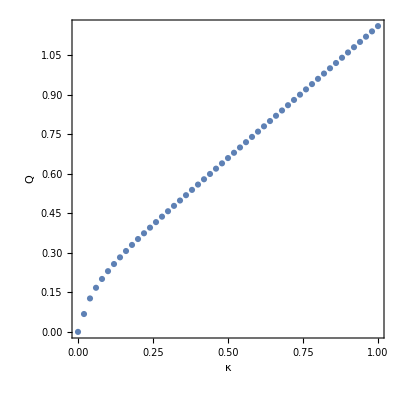

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[2]]},{i,1,Dimensions[data][[1]]}],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"κ","Q"}]
```

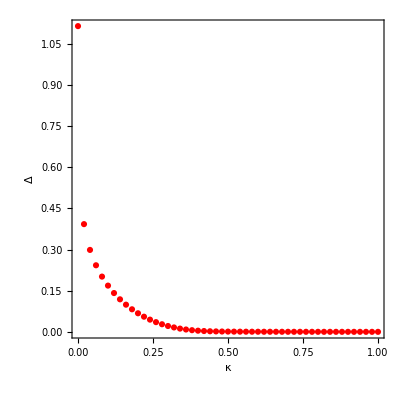

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[1]]-2data[[i]][[2]][[2]]},{i,1,Dimensions[data][[1]]}],PlotStyle->Red,Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"κ","Δ"}]
```

```mathematica
(*T=0.02*)
```

```mathematica
data
```

{{1.,{2.32257,1.16127}},{0.95,{2.22257,1.11126}},{0.9,{2.12257,1.06126}},{0.85,{2.02258,1.01126}},{0.8,{1.92259,0.961267}},{0.75,{1.8226,0.911266}},{0.7,{1.72261,0.861265}},{0.65,{1.62262,0.811264}},{0.6,{1.52263,0.761263}},{0.55,{1.42266,0.711261}},{0.5,{1.3227,0.661259}},{0.45,{1.2228,0.611256}},{0.4,{1.12313,0.561249}},{0.35,{1.02562,0.511193}},{0.3,{0.935008,0.460807}},{0.25,{0.8508,0.409554}},{0.2,{0.772502,0.356618}},{0.15,{0.699824,0.300651}},{0.1,{0.632466,0.238968}},{0.1,{0.632466,0.238968}},{0.095,{0.626007,0.232283}},{0.09,{0.619602,0.225481}},{0.085,{0.613247,0.218539}},{0.08,{0.606942,0.211445}},{0.075,{0.600685,0.204181}},{0.07,{0.594477,0.196728}},{0.065,{0.588317,0.189064}},{0.06,{0.582206,0.18116}},{0.055,{0.576143,0.172983}},{0.05,{0.570127,0.164491}},{0.045,{0.564158,0.155633}},{0.04,{0.558237,0.146341}},{0.035,{0.552362,0.136526}},{0.03,{0.546533,0.126064}},{0.025,{0.540751,0.114778}},{0.02,{0.535015,0.102395}},{0.015,{0.529324,0.0884539}},{0.01,{0.523678,0.0720549}},{0.005,{0.518076,0.0508752}},{0.,{0.512401,0.00381094}}}

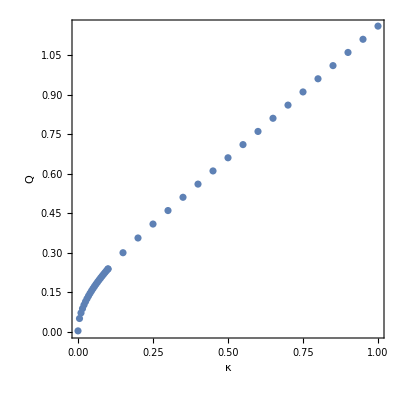

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[2]]},{i,1,Dimensions[data][[1]]}],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"κ","Q"}]
```

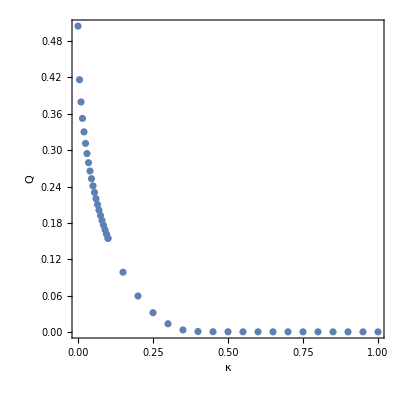

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[1]]-2data[[i]][[2]][[2]]},{i,1,Dimensions[data][[1]]}],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"κ","Q"}]
```

```mathematica
(*T=0.005*)
```

```mathematica
data
```

{{1.,{2.32254,1.16127}},{0.98,{2.28254,1.14127}},{0.96,{2.24254,1.12127}},{0.94,{2.20254,1.10127}},{0.92,{2.16254,1.08127}},{0.9,{2.12254,1.06127}},{0.88,{2.08255,1.04127}},{0.86,{2.04255,1.02127}},{0.84,{2.00255,1.00127}},{0.82,{1.96255,0.981266}},{0.8,{1.92255,0.961266}},{0.78,{1.88255,0.941266}},{0.76,{1.84255,0.921267}},{0.74,{1.80255,0.901267}},{0.72,{1.76255,0.881266}},{0.7,{1.72256,0.861266}},{0.68,{1.68256,0.841269}},{0.66,{1.64256,0.821268}},{0.64,{1.60256,0.801268}},{0.62,{1.56258,0.781273}},{0.6,{1.52258,0.761273}},{0.58,{1.48258,0.741273}},{0.56,{1.44259,0.721272}},{0.54,{1.40259,0.701272}},{0.52,{1.36262,0.681281}},{0.5,{1.32263,0.661281}},{0.48,{1.28264,0.64128}},{0.46,{1.24266,0.621279}},{0.44,{1.20269,0.601278}},{0.42,{1.16276,0.581276}},{0.4,{1.12291,0.561272}},{0.38,{1.08332,0.541252}},{0.36,{1.04453,0.521237}},{0.34,{1.00692,0.501174}},{0.32,{0.970445,0.481044}},{0.3,{0.935019,0.460815}},{0.28,{0.900597,0.44045}},{0.26,{0.867154,0.419905}},{0.24,{0.834669,0.399128}},{0.22,{0.803123,0.378057}},{0.2,{0.772496,0.356612}},{0.18,{0.742768,0.334696}},{0.16,{0.713919,0.312179}},{0.14,{0.685932,0.288892}},{0.12,{0.658785,0.2646}},{0.1,{0.632461,0.23896}},{0.08,{0.606941,0.211446}},{0.06,{0.582206,0.181161}},{0.04,{0.558236,0.146344}},{0.02,{0.535013,0.102401}},{0.,{0.512288,0.00321615}}}

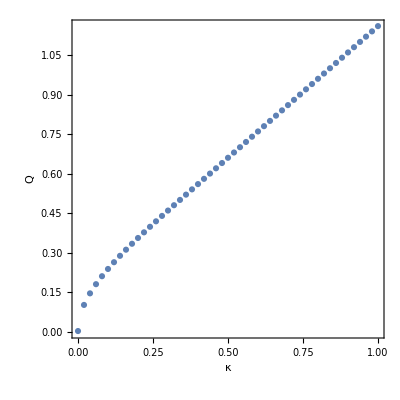

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[2]]},{i,1,Dimensions[data][[1]]}],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"κ","Q"}]
```

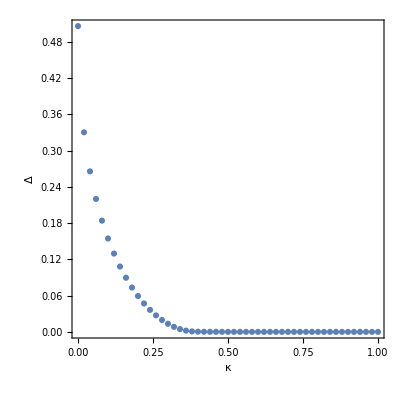

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[1]]-2data[[i]][[2]][[2]]},{i,1,Dimensions[data][[1]]}],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"κ","Δ"}]
```

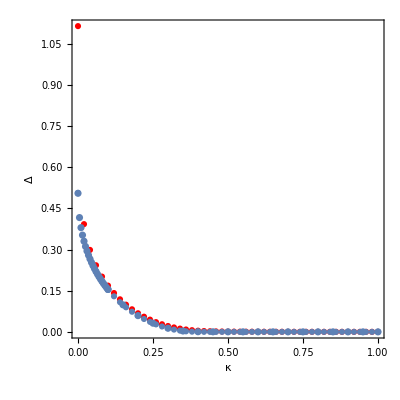

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

### for lieb lattice

```mathematica
λd=0.7;
λp=0.3;
Q=0.06;
μ=-0.39384550232692633;
P=0.05;
R=-0.2;
```

```mathematica
P1=P2=P3=P4=P;
Q1=Q2=Q3=Q4=Q;
λ1=λd;
λ2=λ3=λp;
τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];

H=Assuming[P>0&&Q>0,FullSimplify[{{λ1,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1] Exp[-ⅈ kx/2]+Conjugate[P3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2] Exp[-ⅈ ky/2]+Conjugate[P4] Exp[+ⅈ ky/2],0,λ3}}]]/.kx->0/.ky->0//FullSimplify;
Hs=τ.H;
Eigenvalues[Hs]/.P->P+R
```

{-λp,λp,-(√(-16 Q^2+16 (P+R)^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))))/(√2),(√(-16 Q^2+16 (P+R)^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))))/(√2),-(√(-16 Q^2+16 (P+R)^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))))/(√2),(√(-16 Q^2+16 (P+R)^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))))/(√2)}

```mathematica
Eigensystem[Hs][[2]][[4]]//Chop
```

{0,0,0,0,0.746624,-0.665247}

```mathematica
Eigensystem[Hs][[2]][[2]][[1]]Eigensystem[Hs][[2]][[2]][[2]]
```

0.198066

```mathematica
Eigensystem[Hs][[2]][[5]][[1]]Eigensystem[Hs][[2]][[5]][[2]]
```

-0.198066

```mathematica
((32 √2 Q^2-√2 λd^2-2 √2 λd λp-√2 λp^2+√2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 λd √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 λp √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))) (64 √2 P^2 Q^2-√2 P^2 λd^2+√2 Q^2 λd^2-2 √2 P^2 λd λp-2 √2 Q^2 λd λp-√2 P^2 λp^2+√2 Q^2 λp^2+√2 P^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-√2 Q^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 P^2 λd √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 Q^2 λd √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 P^2 λp √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))+2 Q^2 λp √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))/(16 P Q^2 (16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))) (-2 λp+√2 √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))+((32 √2 Q^2-√2 λd^2-2 √2 λd λp-√2 λp^2-√2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 λd √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 λp √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))) (64 √2 P^2 Q^2-√2 P^2 λd^2+√2 Q^2 λd^2-2 √2 P^2 λd λp-2 √2 Q^2 λd λp-√2 P^2 λp^2+√2 Q^2 λp^2-√2 P^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))+√2 Q^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 P^2 λd √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 Q^2 λd √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 P^2 λp √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))+2 Q^2 λp √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))/(16 P Q^2 (16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))) (-2 λp+√2 √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))
```

-130.767

```mathematica
Eigensystem[Hs][[2]][[4]][[1]]Eigensystem[Hs][[2]][[4]][[2]]+Eigensystem[Hs][[2]][[6]][[1]]Eigensystem[Hs][[2]][[6]][[2]]
```

((32 √2 Q^2-√2 λd^2-2 √2 λd λp-√2 λp^2+√2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 λd √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 λp √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))) (64 √2 P^2 Q^2-√2 P^2 λd^2+√2 Q^2 λd^2-2 √2 P^2 λd λp-2 √2 Q^2 λd λp-√2 P^2 λp^2+√2 Q^2 λp^2+√2 P^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-√2 Q^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 P^2 λd √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 Q^2 λd √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 P^2 λp √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))+2 Q^2 λp √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))/(16 P Q^2 (16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))) (-2 λp+√2 √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))+((32 √2 Q^2-√2 λd^2-2 √2 λd λp-√2 λp^2-√2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 λd √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 λp √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))) (64 √2 P^2 Q^2-√2 P^2 λd^2+√2 Q^2 λd^2-2 √2 P^2 λd λp-2 √2 Q^2 λd λp-√2 P^2 λp^2+√2 Q^2 λp^2-√2 P^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))+√2 Q^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 P^2 λd √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 Q^2 λd √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 P^2 λp √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))+2 Q^2 λp √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))/(16 P Q^2 (16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))) (-2 λp+√2 √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))

```mathematica
((32 √2 Q^2-√2 λd^2-2 √2 λd λp-√2 λp^2+√2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 λd √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 λp √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))) (64 √2 P^2 Q^2-√2 P^2 λd^2+√2 Q^2 λd^2-2 √2 P^2 λd λp-2 √2 Q^2 λd λp-√2 P^2 λp^2+√2 Q^2 λp^2+√2 P^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-√2 Q^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 P^2 λd √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 Q^2 λd √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 P^2 λp √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))+2 Q^2 λp √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))/(16 P Q^2 (16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))) (-2 λp+√2 √(16 P^2-16 Q^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))+((32 √2 Q^2-√2 λd^2-2 √2 λd λp-√2 λp^2-√2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 λd √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 λp √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))) (64 √2 P^2 Q^2-√2 P^2 λd^2+√2 Q^2 λd^2-2 √2 P^2 λd λp-2 √2 Q^2 λd λp-√2 P^2 λp^2+√2 Q^2 λp^2-√2 P^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))+√2 Q^2 √(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))-2 P^2 λd √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 Q^2 λd √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))-2 P^2 λp √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))+2 Q^2 λp √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))/(16 P Q^2 (16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2)))) (-2 λp+√2 √(16 P^2-16 Q^2+λd^2+λp^2+√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 P^2+λd^2-2 λd λp+λp^2))))))/.λp->0.5/.λd->0.8/.P->0.01/.Q->0.2
```

-44.1189

```mathematica
Eigensystem[Hs][[2]][[6]][[1]]Eigensystem[Hs][[2]][[6]][[2]]//FullSimplify
```

-(((-32 √2 Q^2+√2 √((32 P^2+(λd-λp)^2) (-32 Q^2+(λd+λp)^2))+(λd+λp) (√2 λd+√2 λp+2 √(16 P^2-16 Q^2+λd^2+λp^2+√((32 P^2+(λd-λp)^2) (-32 Q^2+(λd+λp)^2))))) (Q^2 (√2 √((32 P^2+(λd-λp)^2) (-32 Q^2+(λd+λp)^2))+(λd-λp) (√2 λd-√2 λp-2 √(16 P^2-16 Q^2+λd^2+λp^2+√((32 P^2+(λd-λp)^2) (-32 Q^2+(λd+λp)^2)))))-P^2 (-64 √2 Q^2+√2 √((32 P^2+(λd-λp)^2) (-32 Q^2+(λd+λp)^2))+(λd+λp) (√2 λd+√2 λp+2 √(16 P^2-16 Q^2+λd^2+λp^2+√((32 P^2+(λd-λp)^2) (-32 Q^2+(λd+λp)^2)))))))/(16 P Q^2 (16 P^2-16 Q^2+λd^2+λp^2+√((32 P^2+(λd-λp)^2) (-32 Q^2+(λd+λp)^2))) (-2 λp+√2 √(16 P^2-16 Q^2+λd^2+λp^2+√((32 P^2+(λd-λp)^2) (-32 Q^2+(λd+λp)^2))))))

```mathematica
T=0.02;
nb[ω_]:=1/(Exp[ω/T]-1);

Lx=Ly=20;
kx= 3 2.π/Lx;
ky=  4 2.(π(Ly-2))/Ly;
λd=0.6797603677046874;
Q=0.15317923548615242;
λp=0.5723805942374255;
P=0 ;

λ1=λd;
λ2=λ3=λp;
Q1=Q;

Q2=Q;
Q3=Q;
Q4=Q;
P1=P;
P2=P;
P3=P;
P4=P;


nd=0;
npx=0;
npy=0;
q1=0;
p1=0;
H={{λ1,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1] Exp[-ⅈ kx/2]+Conjugate[P3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2] Exp[-ⅈ ky/2]+Conjugate[P4] Exp[+ⅈ ky/2],0,λ3}};

τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}]
If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];
energy=energy[[normal]];
vec=vec[[normal]];




(*
vec[[4]]=Join[-vec[[1]][[4;;6]],vec[[1]][[1;;3]]];
vec[[5]]=Join[-vec[[2]][[4;;6]],vec[[2]][[1;;3]]];
vec[[6]]=Join[-vec[[3]][[4;;6]],vec[[3]][[1;;3]]];
*)
Tm=Transpose[vec];


Chop[Tm]//MatrixForm
(*Chop[τ.ConjugateTranspose[Tm]]//MatrixForm*)
Chop[(Tm.τ.ConjugateTranspose[Tm])]//FullSimplify//MatrixForm//N
Chop[Inverse[Tm].Hs.Tm]//FullSimplify//MatrixForm//N
Chop[ConjugateTranspose[Tm].H.Tm]//FullSimplify//MatrixForm//N
Sum[(-2Re[Tm[[1,b]]Conjugate[Tm[[2,b+3]]]Exp[-ⅈ kx/2]](1+ nb[energy[[b]]])+ 2Re[Tm[[1,b+3]]Conjugate[Tm[[2,b]]]Exp[-ⅈ kx/2]] nb[energy[[b]]]),{b,1,3}]
Sum[(-2Re[Tm[[1,b]]Conjugate[Tm[[2,b+3]]]Exp[ⅈ kx/2]](1+ nb[energy[[b]]])+ 2Re[Tm[[1,b+3]]Conjugate[Tm[[2,b]]]Exp[ⅈ kx/2]] nb[energy[[b]]]),{b,1,3}]
Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}]
```

(1.03131 | 0 | 0 | 0 | 0 | 0.252194
0 | -0.327671 | 0.974374 | -0.238271 | 0 | 0
0 | 0.944792 | 0.33793 | -0.0826365 | 0 | 0
0 | 0 | -0.252194 | 1.03131 | 0 | 0
0.238271 | 0 | 0 | 0 | -0.327671 | 0.974374
0.0826365 | 0 | 0 | 0 | 0.944792 | 0.33793)

(1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | -1. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 0.
0. | 0. | 0. | 0. | 0. | -1.)

(0.609109 | 0. | 0. | 0. | 0. | 0.
0. | 0.572381 | 0. | 0. | 0. | 0.
0. | 0. | 0.501729 | 0. | 0. | 0.
0. | 0. | 0. | -0.609109 | 0. | 0.
0. | 0. | 0. | 0. | -0.572381 | 0.
0. | 0. | 0. | 0. | 0. | -0.501729)

(0.609109 | 0. | 0. | 0. | 0. | 0.
0. | 0.572381 | 0. | 0. | 0. | 0.
0. | 0. | 0.501729 | 0. | 0. | 0.
0. | 0. | 0. | 0.609109 | 0. | 0.
0. | 0. | 0. | 0. | 0.572381 | 0.
0. | 0. | 0. | 0. | 0. | 0.501729)

0.437896

0.437896

-3.15764×10^-18+2.85094×10^-17 ⅈ

7.43849×10^-15

```mathematica
energy
```

{1.-2.77713×10^-17 ⅈ,0.960188,0.959188+1.18845×10^-16 ⅈ,-1.,-0.960188-9.30148×10^-19 ⅈ,-0.959188}

```mathematica
Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]),{b,1,3}]
```

1.78723×10^-18-1.07333×10^-18 ⅈ

```mathematica
b=1;
(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])
```

5.8784×10^-33+5.46996×10^-33 ⅈ

```mathematica
b=2;
(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])
```

8.06779×10^-18-4.11074×10^-18 ⅈ

```mathematica
b=3;
(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])
```

-2.05469×10^-18-1.04692×10^-18 ⅈ

#### calculate averages

```mathematica
b
```

{0.67976,0.572381,0.153179,0.0733173,-0.231913+0. ⅈ,-0.565885}

```mathematica
Print["s=",s,"Q= ",Q,"λp= ",λp,"λd= ",λd];
```

s=0.25Q= 0.421357+2.83318×10^-17 ⅈλp= 0.582291+4.28135×10^-16 ⅈλd= 2.60732-1.78664×10^-15 ⅈ

```mathematica
Clear[kx,ky]
T=0.02;
Lx=Ly=20.;

nb[ω_]:=1/(Exp[ω/T]-1);
J=0.5;

(*
λd=3.2004658075755454;
Q=0.5871593272507294;
λp=0.8649627075750748;
*)
(*
λd=2.6073219949882858;
Q=0.4213571818624425;
λp=0.582291387380894;
P=0.0;
*)
λd=0.6797603677046874;
Q=0.15317923548615242;
λp=0.5723805942374255;
P=0.0;


λ1=λd;
λ2=λ3=λp;
Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;

nd=0;
npx=0;
npy=0;
q1=0;
p1=0;
p3=0;
q3=0;
eplot1={};
eplot2={};
eplot3={};
check={};
Do[H={{λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Q1 Exp[ⅈ kx/2]+Q3 Exp[-ⅈ kx/2],Q2 Exp[ⅈ ky/2]+Q4 Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Q1 Exp[-ⅈ kx/2]-Q3 Exp[ⅈ kx/2],0,0,P1 Exp[-ⅈ kx/2]+P3 Exp[+ⅈ kx/2],λ2,0},{-Q2 Exp[-ⅈ ky/2]-Q4 Exp[ⅈ ky/2],0,0,P2 Exp[-ⅈ ky/2]+P4 Exp[+ⅈ ky/2],0,λ3}}//FullSimplify;

τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

AppendTo[eplot1,{kx,ky,energy[[1]]}];
AppendTo[eplot2,{kx,ky,energy[[2]]}];

AppendTo[eplot3,{kx,ky,energy[[3]]}];

order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}]
If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];
energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];


AppendTo[check,{kx,ky,Chop[(Tm.τ.ConjugateTranspose[Tm])]==τ}];
a=1;
nd+=1/(Lx Ly)Sum[2 nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]])+2Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]],{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[2 nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]])+2Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]],{b,1,3}];
a=3;
npy+=1/(Lx Ly)Sum[2 nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]])+2Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]],{b,1,3}];
(*
q1+=-2 J/2 1/(Lx Ly)Sum[Cos[kx/2](Tm[[1,b]]Tm[[2,b+3]](1+ nb[energy[[b]]])-Tm[[1,b+3]]Tm[[2,b]] nb[energy[[b]]]),{b,1,3}];
p1+=1/(Lx Ly)Sum[Exp[-ⅈ kx/2](Conjugate[Tm[[1,b]]]Tm[[2,b]]( nb[energy[[b]]])+Conjugate[Tm[[1,b+3]]]Tm[[2,b+3]] (1+ nb[energy[[b]]])),{b,1,3}];
*)
(*q1+= 1/(Lx Ly)Sum[(Tm[[2,b]]Tm[[1,b+3]](1+ nb[energy[[b]]])+Tm[[2,b+3]]Tm[[1,b]] nb[energy[[b]]]),{b,1,3}];*);
q1+=J/2 1/(Lx Ly)Sum[(-2Re[Tm[[1,b]]Conjugate[Tm[[2,b+3]]]Exp[-ⅈ kx/2]](1+ nb[energy[[b]]])+2Re[Tm[[1,b+3]]Conjugate[Tm[[2,b]]]Exp[-ⅈ kx/2]] nb[energy[[b]]]),{b,1,3}];
q3+=J/2 1/(Lx Ly)Sum[(-2Re[Tm[[1,b]]Conjugate[Tm[[2,b+3]]]Exp[ⅈ kx/2]](1+ nb[energy[[b]]])+2Re[Tm[[1,b+3]]Conjugate[Tm[[2,b]]]Exp[ⅈ kx/2]] nb[energy[[b]]]),{b,1,3}];
p1+=J/2 1/(Lx Ly)Sum[(2Re[Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]]( nb[energy[[b]]])+2Re[Conjugate[Tm[[1,b+3]]]Tm[[2,b+3]]Exp[ⅈ kx/2]] (1+nb[energy[[b]]])),{b,1,3}];
p3+=J/2 1/(Lx Ly)Sum[(2Re[Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[-ⅈ kx/2]]( nb[energy[[b]]])+2Re[Conjugate[Tm[[1,b+3]]]Tm[[2,b+3]]Exp[-ⅈ kx/2]] (1+nb[energy[[b]]])),{b,1,3}];

,{kx,-π,π,2. π/Lx},{ky,-π,1.π,2. π/Ly}]
```

```mathematica
q1
```

0.0770627+6.51128×10^-27 ⅈ

```mathematica
q3
```

0.0770627+6.51128×10^-27 ⅈ

```mathematica
p1
```

5.91058×10^-20-2.76962×10^-43 ⅈ

```mathematica
p3
```

5.91058×10^-20-2.76962×10^-43 ⅈ

```mathematica
npx
```

0.0109039+2.94748×10^-58 ⅈ

```mathematica
npy
```

0.0109039+3.09149×10^-58 ⅈ

```mathematica
nd
```

0.0218078+9.7665×10^-60 ⅈ

```mathematica
energy
```

{1.0001,1.,1.,-1.0001,-1.,-1.}

```mathematica
ListPlot3D[{eplot1,eplot2,eplot3},PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

-Graphics3D-

### analytics

```mathematica
τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
P1=P2=P3=P4=P;
Q=(√(-8 P^2+λd λp))/(2 √2);
Q1=Q3=Q;
Q2=Q4=-Q;

λ1=λd;
λ2=λ3=λp;
H=Assuming[P>0&&Q>0,FullSimplify[{{λ1,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1] Exp[-ⅈ kx/2]+Conjugate[P3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2] Exp[-ⅈ ky/2]+Conjugate[P4] Exp[+ⅈ ky/2],0,λ3}}]]/.kx->0/.ky->0//FullSimplify;
Hs=τ.H;
Eigenvalues[Hs]
```

{0,0,1/2 (-λd-√(64 P^2+λd^2-4 λd λp+4 λp^2)),1/2 (λd-√(64 P^2+λd^2-4 λd λp+4 λp^2)),1/2 (-λd+√(64 P^2+λd^2-4 λd λp+4 λp^2)),1/2 (λd+√(64 P^2+λd^2-4 λd λp+4 λp^2))}

```mathematica
Hs//MatrixForm
```

(λd | 2 P | 2 P | 0 | -√(-4 (P+R)^2+(λd λp)/2) | √(-4 (P+R)^2+(λd λp)/2)
2 P | λp | 0 | √(-4 (P+R)^2+(λd λp)/2) | 0 | 0
2 P | 0 | λp | -√(-4 (P+R)^2+(λd λp)/2) | 0 | 0
0 | -Conjugate[√(-8 (P+R)^2+λd λp)]/(√2) | Conjugate[√(-8 (P+R)^2+λd λp)]/(√2) | -λd | -2 P | -2 P
Conjugate[√(-8 (P+R)^2+λd λp)]/(√2) | 0 | 0 | -2 P | -λp | 0
-Conjugate[√(-8 (P+R)^2+λd λp)]/(√2) | 0 | 0 | -2 P | 0 | -λp)

```mathematica
P=1;
Q=0.5;
λ3=4;
λ1=1;
Eigenvalues[Hs]
```

{-5.64776,5.64776,-3.39671,3.39671,1.25106,-1.25106}

### solving self-consistent equations

```mathematica
Print["s=",s,"Q= ",Q,"λp= ",λp,"λd= ",λd];
```

s=0.24Q= 0.409932+1.2536×10^-14 ⅈλp= 0.567123+1.80019×10^-13 ⅈλd= 2.56629-8.54862×10^-13 ⅈ

```mathematica
Clear[kx,ky]
T=0.1;
Lx=Ly=20;

nb[ω_]:=1/(Exp[ω/T]-1);

J=2.;
λd=2.4021045474523297;
Q=  0.3637921276189296;
λp=0.5140705955663545;
λ1=λd;
λ2=λ3=λp;
s=0.2;
P=0.;

Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


eplot1={};
eplot2={};
eplot3={};
nd=0;
npx=0;
npy=0;
q1=0;
p1=0;
Do[
H={{λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Q1 Exp[ⅈ kx/2]+Q3 Exp[-ⅈ kx/2],Q2 Exp[ⅈ ky/2]+Q4 Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Q1 Exp[-ⅈ kx/2]-Q3 Exp[ⅈ kx/2],0,0,P1 Exp[-ⅈ kx/2]+P3 Exp[+ⅈ kx/2],λ2,0},{-Q2 Exp[-ⅈ ky/2]-Q4 Exp[ⅈ ky/2],0,0,P2 Exp[-ⅈ ky/2]+P4 Exp[+ⅈ ky/2],0,λ3}};

τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

AppendTo[eplot1,{kx,ky,energy[[1]]}];
AppendTo[eplot2,{kx,ky,energy[[2]]}];

AppendTo[eplot3,{kx,ky,energy[[3]]}];

Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);
,{i,1,Dimensions[vec][[1]]}];
Tm=Transpose[vec];
a=1;
nd+=1/(Lx Ly)Sum[2 nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]])+2Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]],{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[2 nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]])+2Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]],{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(-2Re[Tm[[1,b]]Conjugate[Tm[[2,b+3]]]Exp[-ⅈ kx/2]](1+ nb[energy[[b]]])+2Re[Tm[[1,b+3]]Conjugate[Tm[[2,b]]]Exp[-ⅈ kx/2]] nb[energy[[b]]]),{b,1,3}];
p1+=J/2 1/(Lx Ly)Sum[(2Re[Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]]( nb[energy[[b]]])+2Re[Conjugate[Tm[[1,b+3]]]Tm[[2,b+3]]Exp[ⅈ kx/2]] (1+nb[energy[[b]]])),{b,1,3}];

,{kx,0.0,2π,2 π/Lx},{ky,0,2π,2 π/Ly}];
(*initial equations*)
eqn={npx-s,nd-s,Q-q1,P-p1};
D0=IdentityMatrix[4]; 
Print[Abs[eqn.eqn]]
While[Abs[eqn.eqn]>10^-9,

Clear[kx,ky];
b=-Inverse[N[D0]].eqn;
(*update solutions*)
λd+=b[[1]];
λp+=b[[2]];
Q+=b[[3]];
P+=b[[4]];

λ1=λd;
λ2=λ3=λp;


Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;




nd=0;
npx=0;
q1=0;
p1=0;
Do[
H={{λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Q1 Exp[ⅈ kx/2]+Q3 Exp[-ⅈ kx/2],Q2 Exp[ⅈ ky/2]+Q4 Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Q1 Exp[-ⅈ kx/2]-Q3 Exp[ⅈ kx/2],0,0,P1 Exp[-ⅈ kx/2]+P3 Exp[+ⅈ kx/2],λ2,0},{-Q2 Exp[-ⅈ ky/2]-Q4 Exp[ⅈ ky/2],0,0,P2 Exp[-ⅈ ky/2]+P4 Exp[+ⅈ ky/2],0,λ3}};

τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

AppendTo[eplot1,{kx,ky,energy[[1]]}];
AppendTo[eplot2,{kx,ky,energy[[2]]}];

AppendTo[eplot3,{kx,ky,energy[[3]]}];

Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);
,{i,1,Dimensions[vec][[1]]}];
vec[[4]]=Join[-vec[[1]][[4;;6]],vec[[1]][[1;;3]]];
vec[[5]]=Join[-vec[[2]][[4;;6]],vec[[2]][[1;;3]]];
vec[[6]]=Join[-vec[[3]][[4;;6]],vec[[3]][[1;;3]]];
Tm=Transpose[vec];
a=1;
nd+=1/(Lx Ly)Sum[2 nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]])+2Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]],{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[2 nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]])+2Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]],{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(-2Re[Tm[[1,b]]Conjugate[Tm[[2,b+3]]]Exp[-ⅈ kx/2]](1+ nb[energy[[b]]])+2Re[Tm[[1,b+3]]Conjugate[Tm[[2,b]]]Exp[-ⅈ kx/2]] nb[energy[[b]]]),{b,1,3}];
p1+=J/2 1/(Lx Ly)Sum[(2Re[Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]]( nb[energy[[b]]])+2Re[Conjugate[Tm[[1,b+3]]]Tm[[2,b+3]]Exp[ⅈ kx/2]] (1+nb[energy[[b]]])),{b,1,3}];

,{kx,-1.π,1.π,2 π/Lx},{ky,-1.π,1.π,2 π/Ly}];
eqn={npx-s,nd-s,Q-q1,P-p1};
(*update matrix*)
D1=D0+KroneckerProduct[eqn,b]/(b.b);
D0=D1;
Print[eqn.eqn];
]
```

0.00435407

1.45442+1.21398×10^-16 ⅈ

0.00272212+1.0884×10^-19 ⅈ

0.000529542+6.77772×10^-20 ⅈ

0.0000301283+1.44394×10^-20 ⅈ

0.0000307438+3.51933×10^-20 ⅈ

0.0000666078-1.62961×10^-19 ⅈ

0.0000661661-1.22092×10^-19 ⅈ

0.0000530232-1.02592×10^-19 ⅈ

7.43103×10^-8+2.65444×10^-20 ⅈ

1.47592×10^-6-3.08184×10^-19 ⅈ

2.05026×10^-7-6.79958×10^-20 ⅈ

2.86927×10^-8+1.87915×10^-21 ⅈ

5.16885×10^-11-1.7431×10^-22 ⅈ

```mathematica
P
```

-3.92182×10^-18+8.08231×10^-32 ⅈ

```mathematica
Q
```

0.36379+5.65344×10^-19 ⅈ

```mathematica
λp
```

0.514064-2.45381×10^-18 ⅈ

```mathematica
λd
```

2.4021+4.50871×10^-17 ⅈ

```mathematica
npx
```

0.200006-9.79679×10^-18 ⅈ

```mathematica
npd
```

npd

```mathematica
nd
```

0.200002-3.38011×10^-18 ⅈ

```mathematica
Lis
```

checking for all λp λd

```mathematica
Clear[kx,ky]
T=0.1;
Lx=Ly=20;

nb[ω_]:=1/(Exp[ω/T]-1);
data={};
Do[
Q=0.5871593272507294;

λ1=λd;
λ2=λ3=λp;
Q1=Q;
Q3=-Q;
Q2=Q;
Q4=-Q;
s=0.4;
P=0.;

eplot1={};
eplot2={};
eplot3={};
nd=0;
npx=0;
npy=0;
q1=0;
p1=0;
Do[

H={{λ1,P Cos[kx/2],P Cos[ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P Cos[kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P Cos[ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Q1 Exp[ⅈ kx/2]+Q3 Exp[-ⅈ kx/2],Q2 Exp[ⅈ ky/2]+Q4 Exp[-ⅈ ky/2],λ1,P Cos[kx/2],P Cos[ky/2]},{-Q1 Exp[-ⅈ kx/2]-Q3 Exp[ⅈ kx/2],0,0,P Cos[kx/2],λ2,0},{-Q2 Exp[-ⅈ ky/2]-Q4 Exp[ⅈ ky/2],0,0,P Cos[ky/2],0,λ3}}//FullSimplify;

τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

AppendTo[eplot1,{kx,ky,energy[[1]]}];
AppendTo[eplot2,{kx,ky,energy[[2]]}];

AppendTo[eplot3,{kx,ky,energy[[3]]}];

Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);
,{i,1,Dimensions[vec][[1]]}];
Tm=Transpose[vec];
a=1;
nd+=1/(Lx Ly)Sum[2 nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]])+2Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]],{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[2 nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]])+2Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]],{b,1,3}];

q1+=-2ⅈ J/2 1/(Lx Ly)Sum[Sin[kx/2](Tm[[1,b]]Tm[[2,b+3]](1+ nb[energy[[b]]])+Tm[[1,b+3]]Tm[[2,b]] nb[energy[[b]]]),{b,1,3}];
p1+=1/(Lx Ly)Sum[Exp[-ⅈ kx/2](Conjugate[Tm[[1,b]]]Tm[[2,b]]( nb[energy[[b]]])+Conjugate[Tm[[1,b+3]]]Tm[[2,b+3]] (1+ nb[energy[[b]]])),{b,1,3}];

,{kx,0.0,2π,2 π/Lx},{ky,0,2π,2 π/Ly}];
(*initial equations*)
eqn={npx-s,nd-s,Q-q1,P-p1};
AppendTo[data,{npx,nd}];
{λp,0.1,3,0.01},{λd,1,4,0.01}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

### for arbitrary complex

```mathematica
T=0.02;
nb[ω_]:=1/(Exp[ω/T]-1);

Lx=Ly=20;
kx=-0.9;
ky=-0.9+2π/Lx;

λd=0.6797603677046874;
Q=0.15317923548615242;
λp=0.5723805942374255;
P=0.0 Exp[0 ⅈ /5];

λ1=λd;
λ2=λ3=λp;
Q1=Q;

Q2=Q;
Q3=Q;
Q4=Q;
P1=P;
P2=P;
P3=P;
P4=P;


nd=0;
npx=0;
npy=0;
q1=0;
p1=0;
H={{λ1,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1] Exp[-ⅈ kx/2]+Conjugate[P3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2] Exp[-ⅈ ky/2]+Conjugate[P4] Exp[+ⅈ ky/2],0,λ3}};

τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];


Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}]
(*
vec[[4]]=Join[-vec[[1]][[4;;6]],vec[[1]][[1;;3]]];
vec[[5]]=Join[-vec[[2]][[4;;6]],vec[[2]][[1;;3]]];
vec[[6]]=Join[-vec[[3]][[4;;6]],vec[[3]][[1;;3]]];
*)
Tm=Transpose[vec];


Chop[Tm]//MatrixForm
(*Chop[τ.ConjugateTranspose[Tm]]//MatrixForm*)
Chop[(Tm.τ.ConjugateTranspose[Tm])]//FullSimplify//MatrixForm//N
Chop[Inverse[Tm].Hs.Tm]//FullSimplify//MatrixForm//N
Chop[ConjugateTranspose[Tm].H.Tm]//FullSimplify//MatrixForm//N
Sum[(-2Re[Tm[[1,b]]Conjugate[Tm[[2,b+3]]]Exp[-ⅈ kx/2]](1+ nb[energy[[b]]])+ 2Re[Tm[[1,b+3]]Conjugate[Tm[[2,b]]]Exp[-ⅈ kx/2]] nb[energy[[b]]]),{b,1,3}]
Sum[(-2Re[Tm[[1,b]]Conjugate[Tm[[2,b+3]]]Exp[ⅈ kx/2]](1+ nb[energy[[b]]])+ 2Re[Tm[[1,b+3]]Conjugate[Tm[[2,b]]]Exp[ⅈ kx/2]] nb[energy[[b]]]),{b,1,3}]
```

(0 | 1.07376 | 0 | 0 | 0 | 0.391097
0.728443 | 0 | 0.735639 | 0 | -0.267943 | 0
-0.685107 | 0 | 0.782172 | 0 | -0.284892 | 0
0 | 0 | -0.391097 | 0 | 1.07376 | 0
0 | 0.267943 | 0 | 0.728443 | 0 | 0.735639
0 | 0.284892 | 0 | -0.685107 | 0 | 0.782172)

(1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | -1. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 0.
0. | 0. | 0. | 0. | 0. | -1.)

(0.572381 | 0. | 0. | 0. | 0. | 0.
0. | 0.533102 | 0. | 0. | 0. | 0.
0. | 0. | 0.425722 | 0. | 0. | 0.
0. | 0. | 0. | -0.572381 | 0. | 0.
0. | 0. | 0. | 0. | -0.533102 | 0.
0. | 0. | 0. | 0. | 0. | -0.425722)

(0.572381 | 0. | 0. | 0. | 0. | 0.
0. | 0.533102 | 0. | 0. | 0. | 0.
0. | 0. | 0.425722 | 0. | 0. | 0.
0. | 0. | 0. | 0.572381 | 0. | 0.
0. | 0. | 0. | 0. | 0.533102 | 0.
0. | 0. | 0. | 0. | 0. | 0.425722)

0.518129+7.58122×10^-27 ⅈ

0.518129+7.58122×10^-27 ⅈ

#### averages

```mathematica
Clear[kx,ky]
T=0.02;
Lx=Ly=100.;

nb[ω_]:=1/(Exp[ω/T]-1);
J=2;

(*
λd=3.2004658075755454;
Q=0.5871593272507294;
λp=0.8649627075750748;
*)
(*
λd=2.4021045474523297;
Q=0.3637921276189296;
λp=0.5140705955663545;
*)

λd=0.5;
Q=0.08;
λp=1.8;
P=0.1;

λ1=λd;
λ2=λ3=λp;
Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;

nd=0;
npx=0;
npy=0;
q1=0;
p1=0;
p3=0;
q3=0;
q2=0;
q4=0;
eplot1={};
eplot2={};
eplot3={};
check={};
Do[H={{λ1,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1] Exp[-ⅈ kx/2]+Conjugate[P3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2] Exp[-ⅈ ky/2]+Conjugate[P4] Exp[+ⅈ ky/2],0,λ3}};

τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

AppendTo[eplot1,{kx,ky,energy[[1]]}];
AppendTo[eplot2,{kx,ky,energy[[2]]}];

AppendTo[eplot3,{kx,ky,energy[[3]]}];

Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);
,{i,1,Dimensions[vec][[1]]}];
Tm=Transpose[vec];


AppendTo[check,{kx,ky,Chop[(Tm.τ.ConjugateTranspose[Tm])]==τ}];
a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=3;
npy+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
(*
q1+=-2 J/2 1/(Lx Ly)Sum[Cos[kx/2](Tm[[1,b]]Tm[[2,b+3]](1+ nb[energy[[b]]])-Tm[[1,b+3]]Tm[[2,b]] nb[energy[[b]]]),{b,1,3}];
p1+=1/(Lx Ly)Sum[Exp[-ⅈ kx/2](Conjugate[Tm[[1,b]]]Tm[[2,b]]( nb[energy[[b]]])+Conjugate[Tm[[1,b+3]]]Tm[[2,b+3]] (1+ nb[energy[[b]]])),{b,1,3}];
*)
(*q1+= 1/(Lx Ly)Sum[(Tm[[2,b]]Tm[[1,b+3]](1+ nb[energy[[b]]])+Tm[[2,b+3]]Tm[[1,b]] nb[energy[[b]]]),{b,1,3}];*);
q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];
q2+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[3+3,b]]]Exp[-ⅈ ky/2]-Tm[[3,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[3+3,b+3]]]Exp[-ⅈ ky/2]-Tm[[3,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ ky/2]) nb[energy[[b]]],{b,1,3}];



q3+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];



q4+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[3+3,b]]]Exp[ⅈ ky/2]-Tm[[3,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[-ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[3+3,b+3]]]Exp[ⅈ ky/2]-Tm[[3,b]]Conjugate[Tm[[1+3,b]]]Exp[-ⅈ ky/2]) nb[energy[[b]]],{b,1,3}];
p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];
p3+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[-ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[-ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];
,{kx,-π,π,2. π/Lx},{ky,-π,π,2. π/Ly}];
```

```mathematica
ListPlot3D[{eplot1,eplot2,eplot3},PlotRange->{0,0.3},LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

-Graphics3D-

```mathematica
q1
```

0.0711251+1.64761×10^-19 ⅈ

```mathematica
q3
```

0.0711251-1.64761×10^-19 ⅈ

```mathematica
p1
```

-3.67074×10^-11+2.43276×10^-20 ⅈ

```mathematica
p3
```

-3.67074×10^-11-2.43276×10^-20 ⅈ

```mathematica
nd
```

0.00995621+0. ⅈ

```mathematica
npx
```

0.0049781+0. ⅈ

```mathematica
q2
```

0.0711251+1.17881×10^-19 ⅈ

```mathematica
q4
```

0.0711251-1.17881×10^-19 ⅈ

#### self-consistency

```mathematica
Q
```

0.331845+0.00880053 ⅈ

```mathematica
P
```

4.22421×10^-18-1.66541×10^-18 ⅈ

```mathematica
λd
```

0.549115-0.310708 ⅈ

```mathematica
λp
```

1.9117+0.292467 ⅈ

```mathematica
Print["s=",s,"Q= ",Q,"λp= ",λp,"λd= ",λd];
```

s=0.15Q= 0.304324-8.90175×10^-30 ⅈλp= 0.468156-8.74982×10^-29 ⅈλd= 2.19713-1.45966×10^-28 ⅈ

```mathematica
P
```

4.3769×10^-9-1.84608×10^-9 ⅈ

```mathematica
Q
```

0.215753+0.214624 ⅈ

```mathematica
Q=Exp[ⅈ π/4] 0.30432354163084885
```

0.215189+0.215189 ⅈ

```mathematica
Clear[kx,ky]
T=0.1;
Lx=Ly=20;

nb[ω_]:=1/(Exp[ω/T]-1);

J=2.;
λd=2.1971180592880626;
Q=Exp[ⅈ π/4] 0.30432354163084885;
λp=0.468179156314049;
λ1=λd;
λ2=λ3=λp;
s=0.150;
P=-0.1;

Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


eplot1={};
eplot2={};
eplot3={};
nd=0;
npx=0;
npy=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1] Exp[-ⅈ kx/2]+Conjugate[P3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2] Exp[-ⅈ ky/2]+Conjugate[P4] Exp[+ⅈ ky/2],0,λ3}};


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];



Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);
,{i,1,Dimensions[vec][[1]]}];
Tm=Transpose[vec];
a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={npx-s,nd-s,Q-q1,P-p1};
D0=IdentityMatrix[4]; 
Print[Abs[eqn.eqn]]
While[Abs[eqn.eqn]>10^-9,

Clear[kx,ky];
b=-Inverse[N[D0]].eqn;
(*update solutions*)
λd+=b[[1]];
λp+=b[[2]];
Q+=b[[3]];
P+=b[[4]];

λ1=λd;
λ2=λ3=λp;


Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;




nd=0;
npx=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,P1 Exp[ⅈ kx/2]+P3 Exp[-ⅈ kx/2],P2 Exp[ⅈ ky/2]+P4 Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1] Exp[-ⅈ kx/2]+Conjugate[P3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2] Exp[-ⅈ ky/2]+Conjugate[P4] Exp[+ⅈ ky/2],0,λ3}};

τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

AppendTo[eplot1,{kx,ky,energy[[1]]}];
AppendTo[eplot2,{kx,ky,energy[[2]]}];

AppendTo[eplot3,{kx,ky,energy[[3]]}];

Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);
,{i,1,Dimensions[vec][[1]]}];

Tm=Transpose[vec];
a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];


,{kx,-1.π,1.π,2 π/Lx},{ky,-1.π,1.π,2 π/Ly}];
eqn={npx-s,nd-s,Q-q1,P-p1};
(*update matrix*)
D1=D0+KroneckerProduct[eqn,b]/(b.b);
D0=D1;
Print[eqn.eqn];
]
```

0.0143406

0.00450208+0.000954598 ⅈ

1.10754+0.397991 ⅈ

0.00131557+0.000491472 ⅈ

0.000595824+0.000286646 ⅈ

0.000214367+0.000120638 ⅈ

0.000155772+0.000084339 ⅈ

0.0000362261+0.000063402 ⅈ

0.0000795623+0.0000707703 ⅈ

0.0000412073+0.0000491899 ⅈ

0.000046151+0.0000336989 ⅈ

0.0000111917+0.0000506455 ⅈ

0.0000264927+0.0000366172 ⅈ

-1.99333×10^-6+0.0000357629 ⅈ

0.0000347521+0.0000219011 ⅈ

0.0000146163+0.0000192788 ⅈ

0.0000273184-0.0000200064 ⅈ

4.26328×10^-6+6.34108×10^-6 ⅈ

-4.2662×10^-6+1.19493×10^-6 ⅈ

-0.0000252483-0.0000183168 ⅈ

0.0000356419+0.0000248176 ⅈ

0.000224687+2.58514×10^-6 ⅈ

-0.0000329203+0.000121904 ⅈ

0.000155388+0.000209966 ⅈ

0.000229489+0.000353018 ⅈ

0.000371191+0.000272073 ⅈ

0.000334138+0.000314916 ⅈ

0.000334796+0.00031059 ⅈ

0.000312708+0.000254649 ⅈ

0.000398817+0.000388778 ⅈ

0.000479252+0.000490154 ⅈ

0.000312621+0.000638576 ⅈ

0.000530022+0.000479024 ⅈ

0.000488462+0.000436816 ⅈ

0.000696872+0.00067688 ⅈ

0.000796395+0.000896401 ⅈ

0.000656492+0.000636598 ⅈ

0.000445432+0.000809621 ⅈ

0.000735873+0.000595286 ⅈ

0.000696221+0.000488937 ⅈ

0.000902103+0.000877938 ⅈ

0.000936624+0.00119816 ⅈ

0.000865255+0.000800708 ⅈ

0.000527558+0.000681078 ⅈ

0.00119523+0.000917766 ⅈ

0.0013992+0.000882967 ⅈ

0.00111957+0.000936052 ⅈ

0.00113251+0.000631182 ⅈ

0.001203+0.00120913 ⅈ

0.00119516+0.0013781 ⅈ

0.0012876+0.00114078 ⅈ

0.00119864+0.000971314 ⅈ

0.00151535+0.00137703 ⅈ

0.0018006+0.00162475 ⅈ

-0.0000475672-0.000238036 ⅈ

0.00153982+0.00178869 ⅈ

0.000749857+0.00125858 ⅈ

0.00372984+0.00209365 ⅈ

0.0025689+0.00130408 ⅈ

0.00452661+0.000593824 ⅈ

0.00147369+0.000947897 ⅈ

0.00118279-0.000167238 ⅈ

0.000737622+0.00134771 ⅈ

0.000241079+0.000218083 ⅈ

-0.00213765-0.00175245 ⅈ

0.000203916-0.00020541 ⅈ

-0.000262838-0.0000310044 ⅈ

$Aborted

```mathematica
Q
```

0.216025+0.217041 ⅈ

### away from half filling

for fermions

```mathematica
Clear[kx,ky]
T=0.001;
Lx=Ly=20.;

nf[ω_]:=1/(+1+Exp[ω/T]);
J=0.4;



λd=0.3649389471873635;
λp=0.36902207116724156;
Q=0.;
μ=-0.39384550232692633;
μ=1
P=0.11260106456120941;

λ1=λd;
λ2=λ3=λp;
Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;
nd=0;
npx=0;
npy=0;
eplot1={};
eplot2={};
eplot3={};
r1=0;
r2=0;
r3=0;
r4=0;

Do[H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

AppendTo[eplot1,{kx,ky,energy[[1]]}];
AppendTo[eplot2,{kx,ky,energy[[2]]}];

AppendTo[eplot3,{kx,ky,energy[[3]]}];

Tm=Transpose[vec];


a=1;
nd+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npx+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=3;
npy+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];
r3+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[-ⅈ kx/2],{b,1,3}];
r2+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[3,b]]Exp[ⅈ ky/2],{b,1,3}];
r4+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[3,b]]Exp[-ⅈ ky/2],{b,1,3}];



,{kx,-π,π,2. π/Lx},{ky,-π,1.π,2. π/Ly}]
npxf=npx;
ndf=nd;
```

1

```mathematica
r1
```

-0.0191416+4.02856×10^-19 ⅈ

```mathematica
r3
```

-0.0191416-4.02856×10^-19 ⅈ

```mathematica
r2
```

-0.0191416-9.99499×10^-20 ⅈ

```mathematica
r4
```

-0.0191416+9.99499×10^-20 ⅈ

```mathematica
npx
```

0.785189+0. ⅈ

```mathematica
npy
```

0.785189+0. ⅈ

```mathematica
nd
```

0.565622+0. ⅈ

```mathematica
ListPlot3D[{eplot1,eplot2,eplot3},PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

-Graphics3D-

```mathematica
b
```

{0.7,0.3,0.06,0.05,-0.2,-0.7}

for bosons

```mathematica
Clear[kx,ky]
T=0.002;
Lx=Ly=20.;

nb[ω_]:=1/(Exp[ω/T]-1);
J=0.5;

(*
λd=3.2004658075755454;
Q=0.5871593272507294;
λp=0.8649627075750748;
*)
(*
λd=2.4021045474523297;
Q=0.3637921276189296;
λp=0.5140705955663545;
*)


λd=0.7;
λp=0.3;
Q=0.06;
μ=-0.39384550232692633;
P=0.05;
R=-0.2;
λ1=λd;
λ2=λ3=λp;
Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;

R1=R;
R2=R;
R3=R;
R4=R;

nd=0;
npx=0;
npy=0;
q1=0;
p1=0;
p1check=-0;
p3=0;
q3=0;
eplot1={};
eplot2={};
eplot3={};
check={};
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};

τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

AppendTo[eplot1,{kx,ky,energy[[1]]}];
AppendTo[eplot2,{kx,ky,energy[[2]]}];

AppendTo[eplot3,{kx,ky,energy[[3]]}];

Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);
,{i,1,Dimensions[vec][[1]]}];
Tm=Transpose[vec];


AppendTo[check,{kx,ky,Chop[(Tm.τ.ConjugateTranspose[Tm])]==τ}];
a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=3;
npy+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
(*
q1+=-2 J/2 1/(Lx Ly)Sum[Cos[kx/2](Tm[[1,b]]Tm[[2,b+3]](1+ nb[energy[[b]]])-Tm[[1,b+3]]Tm[[2,b]] nb[energy[[b]]]),{b,1,3}];
p1+=1/(Lx Ly)Sum[Exp[-ⅈ kx/2](Conjugate[Tm[[1,b]]]Tm[[2,b]]( nb[energy[[b]]])+Conjugate[Tm[[1,b+3]]]Tm[[2,b+3]] (1+ nb[energy[[b]]])),{b,1,3}];
*)
(*q1+= 1/(Lx Ly)Sum[(Tm[[2,b]]Tm[[1,b+3]](1+ nb[energy[[b]]])+Tm[[2,b+3]]Tm[[1,b]] nb[energy[[b]]]),{b,1,3}];*);
q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];
q3+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];
p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];
p3+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[-ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[-ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];


p1check+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+0Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1),{b,1,3}];
,{kx,0,0,2. π/Lx},{ky,1,1,2. π/Ly}];
```

```mathematica
Chop[Tm]//MatrixForm
```

(0.862548 | 0 | 0.532571 | -0.0873139 | 0 | 0.141413
-0.400288 | -0.659603 | 0.648303 | -0.106288 | 0 | -0.0656264
-0.351286 | 0.751614 | 0.56894 | -0.0932764 | 0 | -0.0575925
0.0873139 | 0 | -0.141413 | 0.862548 | 0 | 0.532571
0.106288 | 0 | 0.0656264 | -0.400288 | -0.659603 | 0.648303
0.0932764 | 0 | 0.0575925 | -0.351286 | 0.751614 | 0.56894)

```mathematica
Chop[Inverse[Tm].Hs.Tm]//FullSimplify//MatrixForm//N
```

(0.92027 | 0. | 0. | 0. | 0. | 0.
0. | 0.3 | 0. | 0. | 0. | 0.
0. | 0. | 0.0273792 | 0. | 0. | 0.
0. | 0. | 0. | -0.92027 | 0. | 0.
0. | 0. | 0. | 0. | -0.3 | 0.
0. | 0. | 0. | 0. | 0. | -0.0273792)

```mathematica
Eigenvectors[Hs][[1]]
```

{-0.0849977+0. ⅈ,-0.103468+0. ⅈ,-0.090802+0. ⅈ,0.839667+0. ⅈ,-0.38967+0. ⅈ,-0.341967+0. ⅈ}

```mathematica
Eigenvectors[Hs][[2]]
```

{0.839667+0. ⅈ,-0.38967+0. ⅈ,-0.341967+0. ⅈ,0.0849977+0. ⅈ,0.103468+0. ⅈ,0.090802+0. ⅈ}

```mathematica
Chop[Eigensystem[Hs]][[2]][[1]]
```

{-0.0849977,-0.103468,-0.090802,0.839667,-0.38967,-0.341967}

```mathematica
Chop[Eigensystem[Hs]][[2]][[6]]
```

{0.137662,-0.0638855,-0.0560648,0.518444,0.631105,0.553847}

```mathematica
Chop[Eigensystem[Hs]][[2]][[1]][[1]]Chop[Eigensystem[Hs]][[2]][[1]][[2]]
```

0.00879458

```mathematica
Chop[Eigensystem[Hs]][[2]][[6]][[1]]Chop[Eigensystem[Hs]][[2]][[6]][[2]]
```

-0.00879458

```mathematica
-0.07913328858732688(-0.0935748572307217)
```

0.00740489

```mathematica
0.13233483219281295(-0.05595568497769079)
```

-0.00740489

```mathematica
Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]),{b,1,3}]
```

-4.59702×10^-17+0. ⅈ

```mathematica
(Tm[[2,1+3]]Conjugate[Tm[[1,1+3]]])
```

0.00585525+0. ⅈ

```mathematica
(Tm[[2,2+3]]Conjugate[Tm[[1,2+3]]])
```

-7.07117×10^-34+0. ⅈ

```mathematica
(Tm[[2,3+3]]Conjugate[Tm[[1,3+3]]])
```

-0.00585525+0. ⅈ

```mathematica
Chop[(Tm.τ.ConjugateTranspose[Tm])]//FullSimplify//MatrixForm//N
```

(1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | -1. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 0.
0. | 0. | 0. | 0. | 0. | -1.)

```mathematica
Chop[(Tm.τ.ConjugateTranspose[Tm])]//FullSimplify//MatrixForm//N
```

```mathematica
npx+npxf
```

1.04393+0. ⅈ

```mathematica
nd+ndf
```

0.10028+0. ⅈ

```mathematica
ndf
```

0.0653062+0. ⅈ

```mathematica
npxf
```

1.02441+0. ⅈ

```mathematica
npx
```

0.0195169+0. ⅈ

```mathematica
nd
```

0.434378+0. ⅈ

```mathematica
q1
```

0.+0. ⅈ

```mathematica
q3
```

0.+0. ⅈ

```mathematica
p1check
```

-1.35525×10^-20-6.23416×10^-21 ⅈ

```mathematica
p3
```

0.112601-3.02208×10^-34 ⅈ

```mathematica
r1
```

-0.255046-5.74778×10^-18 ⅈ

```mathematica
nd
```

0.434378+0. ⅈ

```mathematica
npx
```

0.214811+0. ⅈ

```mathematica
ListPlot3D[{eplot1,eplot2,eplot3},PlotRange->{0,0.1},LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

-Graphics3D-

```mathematica
ne
```

0.712

#### self-consistently

```mathematica
Clear[kx,ky]
T=0.01;
Lx=Ly=20;

nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=0.8;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];
λd=0.3649389471873635;
λp=0.36902207116724156;
Q=0.;
μ=-0.39384550232692633;
P=0.11260106456120941;
R=-0.2550464838744147;
ne=0.712;

λ1=λd;
λ2=λ3=λp;
Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];



Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);
,{i,1,Dimensions[vec][[1]]}];
Tm=Transpose[vec];
a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-1,nd+ndf-1,Q-q1,P-P,R-r1,((ndf+2npxf)/3-ne)};
D0= IdentityMatrix[6]; 

Print[Abs[eqn.eqn]];
```

7.46223×10^-14

```mathematica
While[Abs[eqn.eqn]>10^-9,
Clear[kx,ky];
b=-Inverse[N[D0]].eqn;
(*update solutions*)
λd+=b[[1]];
λp+=b[[2]];
Q+=b[[3]];
P+=b[[4]];
R=b[[5]];
μ+=b[[6]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];



Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);
,{i,1,Dimensions[vec][[1]]}];
Tm=Transpose[vec];
a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];

eqn={npx+npxf-1,nd+ndf-1,Q-q1,P-P,R-r1,((ndf+2npxf)/3-ne)};
(*update matrix*)
D1=D0+KroneckerProduct[eqn,b]/(b.b);
D0=D1;
Print[eqn.eqn];
];
```

0.295802-4.10423×10^-19 ⅈ

0.313402-9.5735×10^-19 ⅈ

0.414573+3.21603×10^-18 ⅈ

0.222584-1.15187×10^-17 ⅈ

0.281761+2.8826×10^-17 ⅈ

0.246943-2.52235×10^-18 ⅈ

0.262506+2.19529×10^-17 ⅈ

0.699832-9.55887×10^-17 ⅈ

0.289671+1.05792×10^-16 ⅈ

0.900562+5.24821×10^-16 ⅈ

0.152525-1.49022×10^-16 ⅈ

0.154572-7.89173×10^-16 ⅈ

0.136632+1.9211×10^-16 ⅈ

0.297772-1.10877×10^-15 ⅈ

0.225926+9.99854×10^-17 ⅈ

0.79431+1.00789×10^-14 ⅈ

25.2952-5.27239×10^-14 ⅈ

5.84358-7.15252×10^-15 ⅈ

2.38053-3.27056×10^-13 ⅈ

1.83056+4.20373×10^-12 ⅈ

0.922094-1.8882×10^-12 ⅈ

0.123358+9.67549×10^-15 ⅈ

1.7011-1.21562×10^-12 ⅈ

1.12786-3.07627×10^-13 ⅈ

2.91992-4.33925×10^-14 ⅈ

1.23434-1.48195×10^-12 ⅈ

5.3362-1.81159×10^-9 ⅈ

2.91626-3.37305×10^-11 ⅈ

4.33032+2.60551×10^-11 ⅈ

3.46446-1.24284×10^-11 ⅈ

6.12671-6.31161×10^-9 ⅈ

4.94693-5.07907×10^-9 ⅈ

1.77519-8.3986×10^-10 ⅈ

3.71401-2.84161×10^-10 ⅈ

0.514462+7.27049×10^-8 ⅈ

7.21223-7.16965×10^-7 ⅈ

0.752951-3.27392×10^-8 ⅈ

0.0222364-8.33567×10^-9 ⅈ

2.40043+0.0000208871 ⅈ

0.942394-2.20391×10^-6 ⅈ

0.458015-7.07976×10^-6 ⅈ

0.342137+9.61358×10^-6 ⅈ

0.323805+1.22669×10^-6 ⅈ

2.10729-0.00199113 ⅈ

0.291599-0.0000131284 ⅈ

0.307989-0.0000153286 ⅈ

0.491423+0.0000243134 ⅈ

0.627816+0.000690524 ⅈ

0.268159+0.0000448829 ⅈ

4.60623-0.236705 ⅈ

0.968956+0.0077998 ⅈ

0.720712+0.00600015 ⅈ

0.852342+0.0170535 ⅈ

0.686454-1.46828 ⅈ

0.380739-0.0207318 ⅈ

0.635338-0.0950878 ⅈ

0.544316+0.00924077 ⅈ

0.581411-0.0511108 ⅈ

0.501887+0.0282655 ⅈ

0.322711+0.00982122 ⅈ

0.713407+0.23462 ⅈ

0.358124-0.0583623 ⅈ

1.12352+0.208034 ⅈ

1.16051-0.417479 ⅈ

0.817813+0.067231 ⅈ

1.05003-0.0594768 ⅈ

0.831086-0.0174695 ⅈ

0.641316-0.107545 ⅈ

0.677414+0.0401551 ⅈ

0.500016-0.0512633 ⅈ

0.572573+0.0217491 ⅈ

0.303539-0.0412311 ⅈ

0.512563+0.0476789 ⅈ

$Aborted

```mathematica
P
```

0.1+0. ⅈ

```mathematica
R
```

-1.34139-5.37619×10^-13 ⅈ

```mathematica
μ
```

-4.4308×10^6+8.64664×10^-7 ⅈ

```mathematica
λd
```

2.72168×10^6-6.80753×10^-7 ⅈ

```mathematica
P
```

-3.24799×10^-7+1.59451×10^-22 ⅈ

```mathematica
R
```

-0.0000105555-1.07716×10^-22 ⅈ

### gaussian method

#### plot

```mathematica
Clear[kx,ky]
T=0.02;
Lx=Ly=30;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=0.5;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];



evaluate:={
ne=0.5;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];


order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne};

};
```

```mathematica
b={0.3746523794496318,0.36297001793905864,0.10265702488016344,0.006819228725341083,-0.08323075574669306+0. ⅈ,-0.3626352627163154};
evaluate;
While[Abs[eqn.eqn]>10^-11,
Jac=ConstantArray[0.,{6,6}];



Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q];
eqn0=Chop[eqn];

δ=10^-7;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,6}];
scale=2.;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

While[(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q<0,
b-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*2;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

];



evaluate;
]
```

convergence = 0.20154 sign = 0.00298258+0. ⅈ

convergence = 0.134876 sign = 0.00152354+0. ⅈ

convergence = 0.0889639 sign = 0.000819256+0. ⅈ

convergence = 0.0565669 sign = 0.000450751+0. ⅈ

convergence = 0.0334186 sign = 0.000251771+0. ⅈ

convergence = 0.0169277 sign = 0.000144622+0. ⅈ

convergence = 0.00663344 sign = 0.0000882248+0. ⅈ

convergence = 0.00387353 sign = 0.0000597984+0. ⅈ

convergence = 0.00715949 sign = 0.0000468989+0. ⅈ

convergence = 2.22329 sign = 5.69848×10^-6+0. ⅈ

convergence = 0.0130177 sign = 0.000213003+0. ⅈ

convergence = 0.000367695 sign = 0.0000893494+0. ⅈ

convergence = 0.00311209 sign = 0.0000609188+0. ⅈ

convergence = 0.737442 sign = 9.66638×10^-6+0. ⅈ

convergence = 0.0641903 sign = 0.0000279546+0. ⅈ

convergence = 0.051147 sign = 0.0000313103+0. ⅈ

convergence = 0.033983 sign = 0.0000376163+0. ⅈ

convergence = 0.0198519 sign = 0.000047254+0. ⅈ

convergence = 0.0104354 sign = 0.0000609679+0. ⅈ

convergence = 0.00500582 sign = 0.0000792721+0. ⅈ

convergence = 0.00220023 sign = 0.000101821+0. ⅈ

convergence = 0.000882101 sign = 0.000126791+0. ⅈ

convergence = 0.000320335 sign = 0.000150993+0. ⅈ

convergence = 0.000105253 sign = 0.000171208+0. ⅈ

convergence = 0.000031596 sign = 0.000185791+0. ⅈ

convergence = 8.83481×10^-6 sign = 0.00019506+0. ⅈ

convergence = 2.35333×10^-6 sign = 0.000200415+0. ⅈ

convergence = 6.08635×10^-7 sign = 0.000203318+0. ⅈ

convergence = 1.54833×10^-7 sign = 0.000204834+0. ⅈ

convergence = 3.90447×10^-8 sign = 0.000205609+0. ⅈ

convergence = 9.80158×10^-9 sign = 0.000206001+0. ⅈ

convergence = 2.45489×10^-9 sign = 0.000206198+0. ⅈ

convergence = 6.14136×10^-10 sign = 0.000206297+0. ⅈ

convergence = 1.53548×10^-10 sign = 0.000206346+0. ⅈ

convergence = 3.83794×10^-11 sign = 0.000206371+0. ⅈ

```mathematica
b
```

{0.560282,0.529932,0.190917,0.00223698,-0.0264366+0. ⅈ,-0.536699}

```mathematica
p1
```

p1

```mathematica
b
```

{0.325644,0.313596,0.0254339,0.0205839,-0.120413+0. ⅈ,-0.308607}

```mathematica
Plot3D[{-λp,λp,-1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),-1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]+√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]+√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky])))))},{kx,-π/4,π/4},{ky,-π/4,π/4},PlotRange->{-0.05,0.05},MaxRecursion->10,Mesh->Full,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
b
```

{0.323343,0.314298,0.0510542,0.013198,-0.105549+0. ⅈ,-0.310851}

```mathematica
p1
```

0.0157237-3.27929×10^-19 ⅈ

```mathematica
data
```

{{1.,{0.665808,0.547282,0.147201,0.0749639,-0.229446+0. ⅈ,-0.540888}},{0.996,{0.662794,0.545207,0.14561,0.0750056,-0.229771+0. ⅈ,-0.538785}},{0.992,{0.659782,0.543134,0.14401,0.0750463,-0.230093+0. ⅈ,-0.536684}},{0.988,{0.656773,0.541063,0.1424,0.0750858,-0.230412+0. ⅈ,-0.534584}},{0.984,{0.653767,0.538993,0.140779,0.0751242,-0.230729+0. ⅈ,-0.532487}},{0.98,{0.650763,0.536925,0.139146,0.0751615,-0.231043+0. ⅈ,-0.530392}},{0.976,{0.647762,0.534859,0.137502,0.0751976,-0.231355+0. ⅈ,-0.528299}},{0.972,{0.644764,0.532795,0.135846,0.0752327,-0.231665+0. ⅈ,-0.526207}},{0.968,{0.641769,0.530733,0.134178,0.0752667,-0.231972+0. ⅈ,-0.524118}},{0.964,{0.638777,0.528672,0.132496,0.0752996,-0.232277+0. ⅈ,-0.522031}},{0.96,{0.635788,0.526613,0.130801,0.0753314,-0.232579+0. ⅈ,-0.519945}},{0.956,{0.632801,0.524556,0.129093,0.0753621,-0.232879+0. ⅈ,-0.517861}},{0.952,{0.629818,0.522501,0.127369,0.0753917,-0.233177+0. ⅈ,-0.51578}},{0.948,{0.626837,0.520447,0.125631,0.0754203,-0.233472+0. ⅈ,-0.5137}},{0.944,{0.62386,0.518395,0.123876,0.0754478,-0.233764+0. ⅈ,-0.511622}},{0.94,{0.620885,0.516345,0.122106,0.0754742,-0.234055+0. ⅈ,-0.509545}},{0.936,{0.617913,0.514297,0.120318,0.0754995,-0.234343+0. ⅈ,-0.507471}},{0.932,{0.614944,0.51225,0.118512,0.0755239,-0.234628+0. ⅈ,-0.505399}},{0.928,{0.611978,0.510205,0.116687,0.0755471,-0.234911+0. ⅈ,-0.503328}},{0.924,{0.609015,0.508162,0.114842,0.0755693,-0.235192+0. ⅈ,-0.501259}},{0.92,{0.606055,0.506121,0.112977,0.0755905,-0.235471+0. ⅈ,-0.499192}},{0.916,{0.603098,0.504081,0.11109,0.0756106,-0.235747+0. ⅈ,-0.497127}},{0.912,{0.600145,0.502043,0.10918,0.0756297,-0.236021+0. ⅈ,-0.495064}},{0.908,{0.597194,0.500006,0.107245,0.0756478,-0.236292+0. ⅈ,-0.493002}},{0.904,{0.594246,0.497971,0.105285,0.0756648,-0.236561+0. ⅈ,-0.490942}},{0.9,{0.591301,0.495938,0.103299,0.0756808,-0.236828+0. ⅈ,-0.488884}},{0.896,{0.588359,0.493907,0.101283,0.0756958,-0.237092+0. ⅈ,-0.486828}},{0.892,{0.585421,0.491877,0.0992373,0.0757097,-0.237354+0. ⅈ,-0.484773}},{0.888,{0.582485,0.489849,0.0971592,0.0757227,-0.237614+0. ⅈ,-0.482721}},{0.884,{0.579553,0.487822,0.0950467,0.0757346,-0.237872+0. ⅈ,-0.480669}},{0.88,{0.576623,0.485797,0.0928974,0.0757456,-0.238127+0. ⅈ,-0.47862}},{0.876,{0.573697,0.483774,0.0907088,0.0757555,-0.23838+0. ⅈ,-0.476572}},{0.872,{0.570774,0.481752,0.0884777,0.0757645,-0.23863+0. ⅈ,-0.474526}},{0.868,{0.567854,0.479732,0.0862011,0.0757724,-0.238879+0. ⅈ,-0.472481}},{0.864,{0.564937,0.477713,0.083875,0.0757794,-0.239124+0. ⅈ,-0.470439}},{0.86,{0.562023,0.475696,0.0814953,0.0757853,-0.239368+0. ⅈ,-0.468397}},{0.856,{0.559112,0.47368,0.0790571,0.0757903,-0.23961+0. ⅈ,-0.466358}},{0.852,{0.556205,0.471666,0.0765549,0.0757943,-0.239849+0. ⅈ,-0.46432}},{0.848,{0.5533,0.469653,0.073982,0.0757973,-0.240085+0. ⅈ,-0.462283}},{0.844,{0.550399,0.467642,0.0713309,0.0757994,-0.24032+0. ⅈ,-0.460248}},{0.84,{0.547501,0.465633,0.0685924,0.0758004,-0.240552+0. ⅈ,-0.458215}},{0.836,{0.544606,0.463624,0.0657556,0.0758005,-0.240782+0. ⅈ,-0.456183}},{0.832,{0.541714,0.461618,0.0628071,0.0757997,-0.24101+0. ⅈ,-0.454153}},{0.828,{0.49011,0.405727,1.01615×10^-7,0.0857894,-0.243395+0. ⅈ,-0.397627}},{0.824,{0.492239,0.40921,3.35333×10^-10,0.084762,-0.243386+0. ⅈ,-0.401146}},{0.82,{0.494369,0.412707,3.35333×10^-10,0.0837335,-0.243377+0. ⅈ,-0.40468}},{0.816,{0.496498,0.416216,3.35333×10^-10,0.0827039,-0.243369+0. ⅈ,-0.408227}}}

```mathematica
b
```

{0.320049,0.314039,0.0621549,0.00786147,-0.0956564+0. ⅈ,-0.311844}

```mathematica
b={0.5186952284162389,0.4456140369679466,0.03140070032813251,0.07575839555972572,-0.24274937213166864+0. ⅈ,-0.4379606919344246}
```

#### with T

```mathematica
data={};
dataF={};


b={0.7238334008935516,0.7157864874810529,0.2540541759552373,7.177349026438976*^-12,-1.0015034801828802*^-9+0. ⅈ,-0.7183406038294028};
Do[
Clear[kx,ky];
T=0.002;
Lx=Ly=L;
L=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=x;



τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];



evaluate:={
ne=0.5;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;


Q1=Q;
Q3=Q;

Q2=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
F=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

F+=1/(Lx Ly)(-T Log[1-Exp[-energy[[1]]/T]]-T Log[1-Exp[-energy[[2]]/T]]
-T Log[1-Exp[-energy[[3]]/T]])+1/(Lx Ly)(-T Log[1-Exp[energy[[1]]/T]]- T Log[1-Exp[energy[[2]]/T]]
- T Log[1-Exp[energy[[3]]/T]]);




order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};
(*the correct one*)
H={{λ1+μ,(2Conjugate[P1])/J Exp[ⅈ kx/2]+(2Conjugate[P3])/J Exp[-ⅈ kx/2],(2Conjugate[P2])/J Exp[ⅈ ky/2]+(2Conjugate[P4])/J Exp[-ⅈ ky/2]},{(2P1)/J Exp[-ⅈ kx/2]+(2P3)/J Exp[ⅈ kx/2],λ2+μ,0},{(2P2)/J Exp[-ⅈ ky/2]+(2P4)/J Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];


F+=1/(Lx Ly)(T Log[1+Exp[-energy[[1]]/T]]+T Log[1+Exp[-energy[[2]]/T]]
+T Log[1+Exp[-energy[[3]]/T]]);


,{kx,-π,π-2 π/Lx,2 π/Lx},{ky,-π,π-2 π/Ly,2 π/Ly}];
F+=- 16 Q^2/(2J)+ 16 P^2/(2J)+16/J P R+ 2λd+ 4λp+ 3μ ne;
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne};

};




evaluate;

While[Abs[eqn.eqn]>10^-9,
Jac=ConstantArray[0.,{6,6}];


Print["convergence = ",Abs[eqn.eqn]];
eqn0=Chop[eqn];

δ=10^-7;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,6}];

scale=1.;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

While[(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q<0,
b-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*2;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

];



evaluate;
];
Print[b, " J = ",x];
AppendTo[data,{x,b}];
AppendTo[dataF,{x,Re[F]}]
,{x,0.67,0.05,-0.01}]
```

convergence = 0.0623418

convergence = 0.169849

convergence = 0.0000409028

convergence = 2.62568×10^-9

{0.721419,0.7182,0.254054,7.17735×10^-12,-2.49623×10^-9+0. ⅈ,-0.719221} J = 0.67

convergence = 0.0000143782

convergence = 2.36825×10^-9

{0.710675,0.707456,0.250262,7.17735×10^-12,-2.49623×10^-9+0. ⅈ,-0.708478} J = 0.66

convergence = 0.0000143781

convergence = 2.61807×10^-9

{0.699932,0.696713,0.24647,7.17735×10^-12,-2.49623×10^-9+0. ⅈ,-0.697735} J = 0.65

convergence = 0.000014378

convergence = 2.74556×10^-9

{0.689188,0.68597,0.242679,7.17735×10^-12,-2.61454×10^-9+0. ⅈ,-0.686991} J = 0.64

convergence = 0.0000143782

convergence = 2.85629×10^-9

{0.678445,0.675226,0.238887,7.17735×10^-12,-2.61454×10^-9+0. ⅈ,-0.676248} J = 0.63

convergence = 0.0000143782

convergence = 3.02852×10^-9

{0.667702,0.664483,0.235095,7.17735×10^-12,-2.61454×10^-9+0. ⅈ,-0.665504} J = 0.62

convergence = 0.0000143781

convergence = 3.22783×10^-9

{0.656958,0.653739,0.231303,7.17735×10^-12,-2.74188×10^-9+0. ⅈ,-0.654761} J = 0.61

convergence = 0.0000143781

convergence = 3.4422×10^-9

{0.646215,0.642996,0.227511,7.17735×10^-12,-2.74188×10^-9+0. ⅈ,-0.644018} J = 0.6

convergence = 0.0000143781

convergence = 3.67562×10^-9

{0.635471,0.632252,0.223719,7.17735×10^-12,-2.74188×10^-9+0. ⅈ,-0.633274} J = 0.59

convergence = 0.0000143781

convergence = 3.92911×10^-9

{0.624728,0.621509,0.219928,7.17735×10^-12,-2.88413×10^-9+0. ⅈ,-0.622531} J = 0.58

convergence = 0.0000143781

convergence = 4.20523×10^-9

{0.613984,0.610766,0.216136,7.17735×10^-12,-2.88413×10^-9+0. ⅈ,-0.611787} J = 0.57

convergence = 0.0000143781

convergence = 4.50619×10^-9

{0.603241,0.600022,0.212344,7.17735×10^-12,-2.98699×10^-9+0. ⅈ,-0.601044} J = 0.56

convergence = 0.0000143781

convergence = 4.83501×10^-9

{0.592498,0.589279,0.208552,7.17735×10^-12,-2.98699×10^-9+0. ⅈ,-0.5903} J = 0.55

convergence = 0.0000143781

convergence = 5.19456×10^-9

{0.581754,0.578535,0.20476,7.17735×10^-12,-3.09664×10^-9+0. ⅈ,-0.579557} J = 0.54

convergence = 0.0000143781

convergence = 5.58866×10^-9

{0.571011,0.567792,0.200968,7.17735×10^-12,-3.09664×10^-9+0. ⅈ,-0.568814} J = 0.53

convergence = 0.0000143781

convergence = 6.02086×10^-9

{0.560267,0.557049,0.197176,7.17735×10^-12,-3.21628×10^-9+0. ⅈ,-0.55807} J = 0.52

convergence = 0.0000143781

convergence = 6.49624×10^-9

{0.549524,0.546305,0.193385,7.17735×10^-12,-3.21628×10^-9+0. ⅈ,-0.547327} J = 0.51

convergence = 0.0000143781

convergence = 7.02015×10^-9

{0.538781,0.535562,0.189593,7.17735×10^-12,-3.34455×10^-9+0. ⅈ,-0.536583} J = 0.5

convergence = 0.0000143781

convergence = 7.59844×10^-9

{0.528037,0.524818,0.185801,7.17735×10^-12,-3.34455×10^-9+0. ⅈ,-0.52584} J = 0.49

convergence = 0.0000143781

convergence = 8.23771×10^-9

{0.517294,0.514075,0.182009,7.17735×10^-12,-3.4829×10^-9+0. ⅈ,-0.515096} J = 0.48

convergence = 0.0000143781

convergence = 8.94631×10^-9

{0.50655,0.503331,0.178217,7.17735×10^-12,-3.4829×10^-9+0. ⅈ,-0.504353} J = 0.47

convergence = 0.0000143781

convergence = 9.73373×10^-9

{0.495807,0.492588,0.174425,7.17735×10^-12,-3.63494×10^-9+0. ⅈ,-0.49361} J = 0.46

convergence = 0.0000143781

convergence = 1.06101×10^-8

{0.485063,0.481845,0.170633,7.17735×10^-12,-3.63494×10^-9+0. ⅈ,-0.482866} J = 0.45

convergence = 0.0000143781

convergence = 1.15887×10^-8

{0.47432,0.471101,0.166842,7.17735×10^-12,-3.80099×10^-9+0. ⅈ,-0.472123} J = 0.44

convergence = 0.0000143781

convergence = 1.26835×10^-8

{0.463577,0.460358,0.16305,7.17735×10^-12,-3.80099×10^-9+0. ⅈ,-0.461379} J = 0.43

convergence = 0.000014378

convergence = 1.39121×10^-8

{0.452833,0.449614,0.159258,7.17735×10^-12,-3.9815×10^-9+0. ⅈ,-0.450636} J = 0.42

convergence = 0.000014378

convergence = 1.52949×10^-8

{0.44209,0.438871,0.155466,7.17735×10^-12,-3.9815×10^-9+0. ⅈ,-0.439893} J = 0.41

convergence = 0.000014378

convergence = 1.68548×10^-8

{0.431346,0.428127,0.151674,7.17735×10^-12,-4.18169×10^-9+0. ⅈ,-0.429149} J = 0.4

convergence = 0.000014378

convergence = 1.86222×10^-8

{0.420603,0.417384,0.147882,7.17735×10^-12,-4.28758×10^-9+0. ⅈ,-0.418406} J = 0.39

convergence = 0.000014378

convergence = 2.06294×10^-8

{0.409859,0.406641,0.14409,7.17735×10^-12,-4.40105×10^-9+0. ⅈ,-0.407662} J = 0.38

convergence = 0.000014378

convergence = 2.29188×10^-8

{0.399116,0.395897,0.140299,7.17735×10^-12,-4.51892×10^-9+0. ⅈ,-0.396919} J = 0.37

convergence = 0.000014378

convergence = 2.55395×10^-8

{0.388373,0.385154,0.136507,7.17735×10^-12,-4.64469×10^-9+0. ⅈ,-0.386175} J = 0.36

convergence = 0.000014378

convergence = 2.85525×10^-8

{0.377629,0.37441,0.132715,7.17735×10^-12,-4.77792×10^-9+0. ⅈ,-0.375432} J = 0.35

convergence = 0.0000143779

convergence = 3.20323×10^-8

{0.366886,0.363667,0.128923,7.17735×10^-12,-4.91921×10^-9+0. ⅈ,-0.364689} J = 0.34

convergence = 0.0000143779

convergence = 3.607×10^-8

{0.356142,0.352924,0.125131,7.17735×10^-12,-5.06837×10^-9+0. ⅈ,-0.353945} J = 0.33

convergence = 0.0000143779

convergence = 4.07809×10^-8

{0.345399,0.34218,0.121339,7.17735×10^-12,-5.22601×10^-9+0. ⅈ,-0.343202} J = 0.32

convergence = 0.0000143779

convergence = 4.63095×10^-8

{0.334656,0.331437,0.117547,7.17735×10^-12,-5.39414×10^-9+0. ⅈ,-0.332458} J = 0.31

convergence = 0.0000143779

convergence = 5.28396×10^-8

{0.323912,0.320693,0.113756,7.17735×10^-12,-5.57545×10^-9+0. ⅈ,-0.321715} J = 0.3

convergence = 0.0000143778

convergence = 6.06062×10^-8

{0.313169,0.30995,0.109964,7.17735×10^-12,-5.76653×10^-9+0. ⅈ,-0.310972} J = 0.29

convergence = 0.0000143778

convergence = 6.99152×10^-8

{0.302425,0.299207,0.106172,7.17735×10^-12,-5.97177×10^-9+0. ⅈ,-0.300228} J = 0.28

convergence = 0.0000143777

convergence = 8.11684×10^-8

{0.291682,0.288463,0.10238,7.17735×10^-12,-6.19269×10^-9+0. ⅈ,-0.289485} J = 0.27

convergence = 0.0000143777

convergence = 9.49005×10^-8

{0.280939,0.27772,0.0985882,7.17735×10^-12,-6.43282×10^-9+0. ⅈ,-0.278742} J = 0.26

convergence = 0.0000143776

convergence = 1.11833×10^-7

{0.270195,0.266977,0.0947963,7.17735×10^-12,-6.68894×10^-9+0. ⅈ,-0.267998} J = 0.25

convergence = 0.0000143776

convergence = 1.32952×10^-7

{0.259452,0.256233,0.0910045,7.17735×10^-12,-6.96789×10^-9+0. ⅈ,-0.257255} J = 0.24

convergence = 0.0000143775

convergence = 1.5963×10^-7

{0.248709,0.24549,0.0872126,7.17735×10^-12,-7.27147×10^-9+0. ⅈ,-0.246512} J = 0.23

convergence = 0.0000143774

convergence = 1.93799×10^-7

{0.237966,0.234747,0.0834208,7.17735×10^-12,-7.60102×10^-9+0. ⅈ,-0.235768} J = 0.22

convergence = 0.0000143773

convergence = 2.38232×10^-7

{0.227223,0.224004,0.0796289,7.17735×10^-12,-7.9631×10^-9+0. ⅈ,-0.225025} J = 0.21

convergence = 0.0000143771

convergence = 2.96974×10^-7

{0.216479,0.213261,0.075837,7.17735×10^-12,-8.36192×10^-9+0. ⅈ,-0.214282} J = 0.2

convergence = 0.0000143769

convergence = 3.76026×10^-7

{0.205737,0.202518,0.0720452,7.17735×10^-12,-8.80185×10^-9+0. ⅈ,-0.203539} J = 0.19

convergence = 0.0000143766

convergence = 4.84467×10^-7

{0.194994,0.191775,0.0682533,6.14335×10^-12,-7.95211×10^-9+0. ⅈ,-0.192797} J = 0.18

convergence = 0.0000143763

convergence = 6.36277×10^-7

{0.184251,0.181032,0.0644614,5.49953×10^-12,-7.53775×10^-9+0. ⅈ,-0.182054} J = 0.17

convergence = 0.0000143758

convergence = 8.53432×10^-7

{0.173509,0.17029,0.0606695,5.00528×10^-12,-7.28864×10^-9+0. ⅈ,-0.171312} J = 0.16

convergence = 0.0000143752

convergence = 1.17118×10^-6

{0.162766,0.159548,0.0568776,4.58537×10^-12,-7.12269×10^-9+0. ⅈ,-0.16057} J = 0.15

convergence = 0.0000143743

convergence = 1.64729×10^-6

{0.152024,0.148806,0.0530857,4.20913×10^-12,-7.00585×10^-9+0. ⅈ,-0.149828} J = 0.14

convergence = 0.0000143732

convergence = 2.37859×10^-6

{0.141283,0.138065,0.0492938,3.8609×10^-12,-6.92068×10^-9+0. ⅈ,-0.139086} J = 0.13

convergence = 0.0000143716

convergence = 3.53124×10^-6

convergence = 1.27622×10^-9

{0.130542,0.127324,0.0455018,3.53129×10^-12,-6.85702×10^-9+0. ⅈ,-0.128346} J = 0.12

convergence = 0.0000143779

convergence = 5.41241×10^-6

convergence = 3.08684×10^-9

{0.119801,0.116584,0.0417099,3.2141×10^-12,-6.8085×10^-9+0. ⅈ,-0.117605} J = 0.11

convergence = 0.0000143778

convergence = 8.52563×10^-6

convergence = 7.43701×10^-9

{0.109061,0.105845,0.0379178,2.90536×10^-12,-6.77109×10^-9+0. ⅈ,-0.106866} J = 0.1

convergence = 0.0000143776

convergence = 0.0000138586

convergence = 1.88383×10^-8

{0.0983209,0.0951063,0.0341257,2.46083×10^-13,-6.36938×10^-10+0. ⅈ,-0.0961268} J = 0.09

convergence = 0.0000143773

convergence = 0.0000232301

convergence = 4.92419×10^-8

{0.0875817,0.0843691,0.0303335,2.46083×10^-13,-6.36938×10^-10+0. ⅈ,-0.0853889} J = 0.08

convergence = 0.0000143768

convergence = 0.0000400717

convergence = 1.31207×10^-7

{0.0768428,0.0736334,0.0265411,1.90587×10^-13,-6.33828×10^-10+0. ⅈ,-0.0746523} J = 0.07

convergence = 0.0000143759

convergence = 0.0000707615

convergence = 3.49244×10^-7

{0.066104,0.0628999,0.0227483,1.62695×10^-13,-6.32609×10^-10+0. ⅈ,-0.0639173} J = 0.06

convergence = 0.0000143742

convergence = 0.000126731

convergence = 9.00296×10^-7

{0.0553644,0.05217,0.0189548,1.35517×10^-13,-6.31691×10^-10+0. ⅈ,-0.0531846} J = 0.05

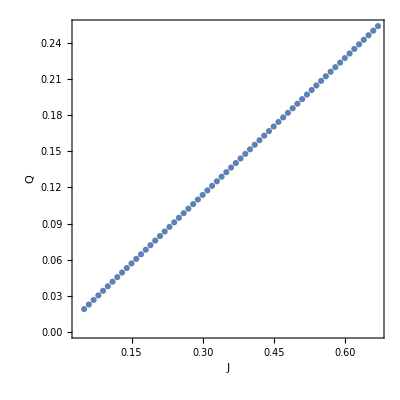

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[3]]},{i,1,Dimensions[data][[1]]}],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","Q"}]
```

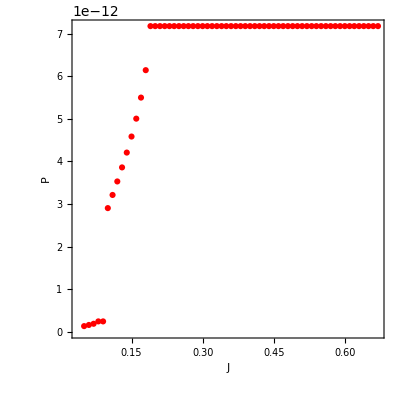

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[4]]},{i,1,Dimensions[data][[1]]}],PlotRange->All,Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","P"},PlotStyle->Red]
```

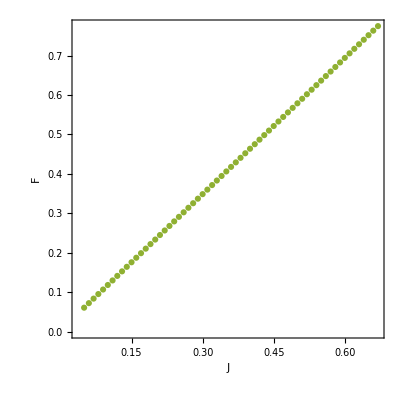

```mathematica
ListPlot[Table[{dataF[[i]][[1]],Re[dataF[[i]][[2]]]},{i,1,Dimensions[data][[1]]}],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","F"},PlotStyle->ColorData[97,"ColorList"][[3]]]
```

```mathematica
gap={};
sign={};
data1={};
Do[
b=data[[i]][[2]];
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];
AppendTo[gap,{data[[i]][[1]],(√(-16 Q^2+16 (P+R)^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))))/(√2)}];
AppendTo[sign,{data[[i]][[1]],(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q}];
If[And[-8 P^2-16 P R-8 R^2+λd λp>0,(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q>0],AppendTo[data1,data[[i]]]]

,{i,1,Dimensions[data][[1]]}]
data=data1;
```

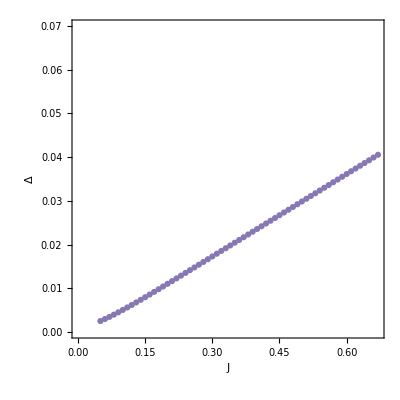

```mathematica
ListPlot[gap,Frame->True,PlotRange->{0,0.07},PlotRange->All,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","Δ"},PlotStyle->ColorData[97,"ColorList"][[5]]]
```

#### data

```mathematica
b
```

{0.377432,0.377571,0.,0.120396,-0.253787,-0.423246}

```mathematica
ne
```

0.712

```mathematica
(*T=0.01, Lx=Ly=20, J=0.8, ne=0.712*)
b
```

{0.374891,0.379539,0.,0.121774,-0.255113,-0.404535}

```mathematica
(*T=0.01, Lx=Ly=40, J=0.8, ne=0.712*)
```

```mathematica
b
```

{0.343895,0.357206,0.,0.121667,-0.245575,-0.418801}

```mathematica
(*T=0.01, Lx=Ly=80, J=0.8, ne=0.712*)
```

```mathematica
b
```

{0.321224,0.328661,0.,0.12159,-0.236464,-0.439671}

```mathematica
(*T=0.02, Lx=Ly=20, J=0.8, ne=0.712*)
```

```mathematica
b
```

{0.377432,0.377571,0.,0.120396,-0.253787,-0.423246}

```mathematica
(*T=0.1, Lx=Ly=20, J=0.8, ne=0.712*)
```

```mathematica
b
```

{0.303763,0.282837,0.,0.0712349,-0.144638,-0.366449}

```mathematica
(*T=0.1, Lx=Ly=80, J=0.8, ne=0.712*)
```

```mathematica
b
```

{0.260863,0.248183,0.,0.0588728,-0.111901,-0.351108}

```mathematica
(*T=0.02, Lx=Ly=20, J=0.8, ne=0.75*)
```

```mathematica
b
```

{0.399836,0.417572,0.,0.104537,-0.248913,-0.484828}

```mathematica
(*T=0.02, Lx=Ly=20, J=0.6, ne=0.75*)
```

```mathematica
b
```

{0.465991,0.475861,0.,0.0787129,-0.245124,-0.533176}

```mathematica
(*T=0.05, Lx=Ly=20, J=0.5, ne=0.75*)
```

```mathematica
b
```

{0.383027,0.358993,0.,0.0597218,-0.187927,-0.42981}

```mathematica
(*T=0.02, Lx=Ly=20, J=0.8, ne=0.5*)
```

```mathematica
b
```

{0.222427,0.12927,0.,0.192778,-0.252624,-0.118891}

```mathematica
(*T=0.02, Lx=Ly=20, J=0.4, ne=0.5*)
```

```mathematica
b
```

{0.452907,0.334239,0.,0.103967,-0.241494,-0.325759}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.2, ne=0.5*)
```

```mathematica
b
```

{0.527834,0.449888,0.,0.0522793,-0.225521,-0.445624}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.5, ne=0.5*)
```

```mathematica
b
```

{0.39798,0.274436,0.,0.128709,-0.245517,-0.265173}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.5, ne=0.5 nonzero Q*)
```

```mathematica
b
```

{0.665808,0.547282,0.147201,0.0749639,-0.229446+0. ⅈ,-0.540888}

```mathematica
(*T=0.04  Lx=Ly=20, J=0.5, ne=0.5 nonzero Q*)
```

```mathematica
b
```

{0.64767,0.545359,0.153482,0.0674061,-0.210752+0. ⅈ,-0.543489}

```mathematica
(*T=0.02  Lx=Ly=60, J=0.5, ne=0.5 nonzero Q*)
```

```mathematica
b
```

{0.653378,0.54307,0.14782,0.0733884,-0.223391+0. ⅈ,-0.542499}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.45, ne=0.5 nonzero Q*)
```

```mathematica
b
```

{0.610911,0.492972,0.118984,0.0787036,-0.231918+0. ⅈ,-0.486171}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.4, ne=0.5nonzero Q )
```

```mathematica
b
```

{0.554853,0.438909,0.0858659,0.0827691,-0.234614+0. ⅈ,-0.431694}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.349, ne=0.5nonzero Q )
```

```mathematica
b
```

{0.496064,0.384025,0.0348041,0.0872822,-0.237587+0. ⅈ,-0.376381}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.34, ne=0.5 )
```

```mathematica
b
```

{0.482432,0.371226,1.82893×10^-9,0.0887668,-0.238357+0. ⅈ,-0.363464}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.3, ne=0.5 )
```

```mathematica
b
```

{0.499948,0.395805,-3.17362×10^-11,0.0785212,-0.235765+0. ⅈ,-0.3887}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.2, ne=0.5 )
```

```mathematica
b
```

{0.530328,0.451873,-3.17362×10^-11,0.0526018,-0.225648+0. ⅈ,-0.447566}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.1, ne=0.5 )
```

```mathematica
b
```

{0.500114,0.455959,-3.17362×10^-11,0.0263512,-0.195153+0. ⅈ,-0.456958}

```mathematica
(*T=0.02  Lx=Ly=40, J=0.5, ne=0.5 )
```

```mathematica
b
```

{0.656506,0.544091,0.147653,0.0737987,-0.224942+0. ⅈ,-0.541988}

```mathematica
(*T=0.02  Lx=Ly=20, J=0.5, ne=0.5, s=0.6 )
```

```mathematica
b
```

{0.320049,0.314039,0.0621549,0.00786147,-0.0956564+0. ⅈ,-0.311844}

sweep over J for T=0.02  Lx=Ly=20

```mathematica
data
```

{{0.5,{0.665808,0.547282,0.147201,0.0749639,-0.229446+0. ⅈ,-0.540888}},{0.499,{0.66472,0.546194,0.146665,0.0750357,-0.229494+0. ⅈ,-0.539791}},{0.498,{0.663631,0.545105,0.146129,0.0751076,-0.229541+0. ⅈ,-0.538695}},{0.497,{0.662541,0.544017,0.145592,0.0751796,-0.229588+0. ⅈ,-0.537599}},{0.496,{0.661452,0.542929,0.145054,0.0752518,-0.229636+0. ⅈ,-0.536502}},{0.495,{0.660362,0.541841,0.144514,0.075324,-0.229684+0. ⅈ,-0.535406}},{0.494,{0.659271,0.540753,0.143974,0.0753964,-0.229731+0. ⅈ,-0.53431}},{0.493,{0.658181,0.539665,0.143433,0.0754689,-0.229779+0. ⅈ,-0.533214}},{0.492,{0.657089,0.538577,0.142891,0.0755416,-0.229827+0. ⅈ,-0.532118}},{0.491,{0.655998,0.537489,0.142347,0.0756143,-0.229875+0. ⅈ,-0.531022}},{0.49,{0.654906,0.536402,0.141803,0.0756872,-0.229923+0. ⅈ,-0.529927}},{0.489,{0.653814,0.535314,0.141257,0.0757602,-0.229971+0. ⅈ,-0.528831}},{0.488,{0.652721,0.534227,0.140711,0.0758333,-0.230019+0. ⅈ,-0.527735}},{0.487,{0.651628,0.533139,0.140163,0.0759065,-0.230068+0. ⅈ,-0.52664}},{0.486,{0.650535,0.532052,0.139614,0.0759799,-0.230116+0. ⅈ,-0.525545}},{0.485,{0.649441,0.530965,0.139064,0.0760534,-0.230165+0. ⅈ,-0.524449}},{0.484,{0.648347,0.529878,0.138513,0.076127,-0.230213+0. ⅈ,-0.523354}},{0.483,{0.647253,0.528791,0.137961,0.0762007,-0.230262+0. ⅈ,-0.522259}},{0.482,{0.646158,0.527704,0.137407,0.0762745,-0.230311+0. ⅈ,-0.521164}},{0.481,{0.645063,0.526617,0.136853,0.0763485,-0.23036+0. ⅈ,-0.520069}},{0.48,{0.643967,0.52553,0.136297,0.0764226,-0.230409+0. ⅈ,-0.518974}},{0.479,{0.642871,0.524443,0.13574,0.0764968,-0.230458+0. ⅈ,-0.517879}},{0.478,{0.641775,0.523357,0.135182,0.0765711,-0.230507+0. ⅈ,-0.516785}},{0.477,{0.640678,0.52227,0.134622,0.0766456,-0.230556+0. ⅈ,-0.51569}},{0.476,{0.639581,0.521184,0.134062,0.0767202,-0.230605+0. ⅈ,-0.514595}},{0.475,{0.638484,0.520098,0.1335,0.0767949,-0.230655+0. ⅈ,-0.513501}},{0.474,{0.637386,0.519012,0.132936,0.0768697,-0.230704+0. ⅈ,-0.512407}},{0.473,{0.636288,0.517925,0.132372,0.0769447,-0.230754+0. ⅈ,-0.511313}},{0.472,{0.635189,0.516839,0.131806,0.0770198,-0.230803+0. ⅈ,-0.510218}},{0.471,{0.63409,0.515754,0.131239,0.077095,-0.230853+0. ⅈ,-0.509124}},{0.47,{0.63299,0.514668,0.13067,0.0771703,-0.230903+0. ⅈ,-0.50803}},{0.469,{0.63189,0.513582,0.1301,0.0772458,-0.230953+0. ⅈ,-0.506937}},{0.468,{0.63079,0.512496,0.129529,0.0773213,-0.231003+0. ⅈ,-0.505843}},{0.467,{0.629689,0.511411,0.128956,0.077397,-0.231053+0. ⅈ,-0.504749}},{0.466,{0.628588,0.510325,0.128382,0.0774729,-0.231103+0. ⅈ,-0.503655}},{0.465,{0.627486,0.50924,0.127806,0.0775488,-0.231153+0. ⅈ,-0.502562}},{0.464,{0.626384,0.508155,0.127229,0.0776249,-0.231204+0. ⅈ,-0.501469}},{0.463,{0.625282,0.50707,0.126651,0.0777011,-0.231254+0. ⅈ,-0.500375}},{0.462,{0.624179,0.505985,0.12607,0.0777775,-0.231305+0. ⅈ,-0.499282}},{0.461,{0.623076,0.5049,0.125489,0.0778539,-0.231355+0. ⅈ,-0.498189}},{0.46,{0.621972,0.503815,0.124906,0.0779305,-0.231406+0. ⅈ,-0.497096}},{0.459,{0.620868,0.50273,0.124321,0.0780073,-0.231457+0. ⅈ,-0.496003}},{0.458,{0.619763,0.501645,0.123735,0.0780841,-0.231508+0. ⅈ,-0.49491}},{0.457,{0.618658,0.500561,0.123147,0.0781611,-0.231559+0. ⅈ,-0.493817}},{0.456,{0.617553,0.499476,0.122557,0.0782382,-0.23161+0. ⅈ,-0.492725}},{0.455,{0.616447,0.498392,0.121966,0.0783154,-0.231661+0. ⅈ,-0.491632}},{0.454,{0.615341,0.497308,0.121373,0.0783928,-0.231712+0. ⅈ,-0.49054}},{0.453,{0.614234,0.496224,0.120778,0.0784703,-0.231764+0. ⅈ,-0.489447}},{0.452,{0.613126,0.49514,0.120182,0.0785479,-0.231815+0. ⅈ,-0.488355}},{0.451,{0.612019,0.494056,0.119584,0.0786257,-0.231867+0. ⅈ,-0.487263}},{0.45,{0.610911,0.492972,0.118984,0.0787036,-0.231918+0. ⅈ,-0.486171}},{0.449,{0.609802,0.491888,0.118382,0.0787816,-0.23197+0. ⅈ,-0.485079}},{0.448,{0.608693,0.490804,0.117779,0.0788597,-0.232022+0. ⅈ,-0.483987}},{0.447,{0.607583,0.489721,0.117173,0.078938,-0.232074+0. ⅈ,-0.482895}},{0.446,{0.606473,0.488637,0.116566,0.0790164,-0.232126+0. ⅈ,-0.481804}},{0.445,{0.605363,0.487554,0.115957,0.079095,-0.232178+0. ⅈ,-0.480712}},{0.444,{0.604252,0.486471,0.115345,0.0791736,-0.23223+0. ⅈ,-0.479621}},{0.443,{0.60314,0.485387,0.114732,0.0792524,-0.232282+0. ⅈ,-0.478529}},{0.442,{0.602028,0.484304,0.114117,0.0793314,-0.232335+0. ⅈ,-0.477438}},{0.441,{0.600916,0.483221,0.1135,0.0794104,-0.232387+0. ⅈ,-0.476347}},{0.44,{0.599803,0.482139,0.11288,0.0794896,-0.23244+0. ⅈ,-0.475256}},{0.439,{0.59869,0.481056,0.112259,0.079569,-0.232492+0. ⅈ,-0.474165}},{0.438,{0.597576,0.479973,0.111635,0.0796484,-0.232545+0. ⅈ,-0.473074}},{0.437,{0.596461,0.478891,0.111009,0.079728,-0.232598+0. ⅈ,-0.471983}},{0.436,{0.595346,0.477808,0.110381,0.0798078,-0.232651+0. ⅈ,-0.470892}},{0.435,{0.594231,0.476726,0.109751,0.0798876,-0.232704+0. ⅈ,-0.469802}},{0.434,{0.593115,0.475643,0.109118,0.0799676,-0.232757+0. ⅈ,-0.468711}},{0.433,{0.591999,0.474561,0.108483,0.0800478,-0.23281+0. ⅈ,-0.467621}},{0.432,{0.590882,0.473479,0.107846,0.080128,-0.232863+0. ⅈ,-0.46653}},{0.431,{0.589765,0.472397,0.107206,0.0802084,-0.232916+0. ⅈ,-0.46544}},{0.43,{0.588647,0.471316,0.106564,0.080289,-0.23297+0. ⅈ,-0.46435}},{0.429,{0.587528,0.470234,0.105919,0.0803696,-0.233023+0. ⅈ,-0.46326}},{0.428,{0.586409,0.469152,0.105272,0.0804505,-0.233077+0. ⅈ,-0.46217}},{0.427,{0.58529,0.468071,0.104622,0.0805314,-0.233131+0. ⅈ,-0.46108}},{0.426,{0.58417,0.466989,0.103969,0.0806125,-0.233184+0. ⅈ,-0.459991}},{0.425,{0.583049,0.465908,0.103314,0.0806937,-0.233238+0. ⅈ,-0.458901}},{0.424,{0.581928,0.464827,0.102656,0.080775,-0.233292+0. ⅈ,-0.457812}},{0.423,{0.580806,0.463746,0.101995,0.0808565,-0.233346+0. ⅈ,-0.456722}},{0.422,{0.579684,0.462665,0.101331,0.0809382,-0.2334+0. ⅈ,-0.455633}},{0.421,{0.578562,0.461584,0.100664,0.0810199,-0.233455+0. ⅈ,-0.454544}},{0.42,{0.577438,0.460503,0.0999947,0.0811018,-0.233509+0. ⅈ,-0.453455}},{0.419,{0.576315,0.459422,0.099322,0.0811839,-0.233563+0. ⅈ,-0.452366}},{0.418,{0.57519,0.458342,0.0986462,0.081266,-0.233618+0. ⅈ,-0.451277}},{0.417,{0.574065,0.457261,0.0979672,0.0813484,-0.233672+0. ⅈ,-0.450188}},{0.416,{0.57294,0.456181,0.097285,0.0814308,-0.233727+0. ⅈ,-0.449099}},{0.415,{0.571814,0.4551,0.0965994,0.0815134,-0.233782+0. ⅈ,-0.448011}},{0.414,{0.570687,0.45402,0.0959105,0.0815961,-0.233837+0. ⅈ,-0.446922}},{0.413,{0.56956,0.45294,0.0952182,0.081679,-0.233892+0. ⅈ,-0.445834}},{0.412,{0.568432,0.45186,0.0945223,0.081762,-0.233947+0. ⅈ,-0.444746}},{0.411,{0.567304,0.45078,0.0938229,0.0818452,-0.234002+0. ⅈ,-0.443657}},{0.41,{0.566175,0.4497,0.0931197,0.0819284,-0.234057+0. ⅈ,-0.442569}},{0.409,{0.565046,0.448621,0.0924128,0.0820119,-0.234112+0. ⅈ,-0.441481}},{0.408,{0.563915,0.447541,0.091702,0.0820954,-0.234168+0. ⅈ,-0.440393}},{0.407,{0.562785,0.446462,0.0909873,0.0821792,-0.234223+0. ⅈ,-0.439306}},{0.406,{0.561654,0.445382,0.0902686,0.082263,-0.234279+0. ⅈ,-0.438218}},{0.405,{0.560522,0.444303,0.0895458,0.082347,-0.234334+0. ⅈ,-0.43713}},{0.404,{0.559389,0.443224,0.0888187,0.0824311,-0.23439+0. ⅈ,-0.436043}},{0.403,{0.558256,0.442145,0.0880872,0.0825154,-0.234446+0. ⅈ,-0.434956}},{0.402,{0.557123,0.441066,0.0873514,0.0825998,-0.234502+0. ⅈ,-0.433868}},{0.401,{0.555988,0.439987,0.086611,0.0826844,-0.234558+0. ⅈ,-0.432781}},{0.4,{0.554853,0.438909,0.0858659,0.0827691,-0.234614+0. ⅈ,-0.431694}},{0.399,{0.553718,0.43783,0.085116,0.0828539,-0.23467+0. ⅈ,-0.430607}},{0.398,{0.552582,0.436751,0.0843612,0.0829389,-0.234726+0. ⅈ,-0.42952}},{0.397,{0.551445,0.435673,0.0836013,0.083024,-0.234783+0. ⅈ,-0.428433}},{0.396,{0.550308,0.434595,0.0828363,0.0831093,-0.234839+0. ⅈ,-0.427347}},{0.395,{0.54917,0.433516,0.0820659,0.0831947,-0.234896+0. ⅈ,-0.42626}},{0.394,{0.548031,0.432438,0.08129,0.0832802,-0.234952+0. ⅈ,-0.425174}},{0.393,{0.546892,0.43136,0.0805085,0.0833659,-0.235009+0. ⅈ,-0.424087}},{0.392,{0.545752,0.430282,0.0797211,0.0834518,-0.235066+0. ⅈ,-0.423001}},{0.391,{0.544611,0.429205,0.0789278,0.0835378,-0.235123+0. ⅈ,-0.421915}},{0.39,{0.54347,0.428127,0.0781283,0.0836239,-0.23518+0. ⅈ,-0.420829}},{0.389,{0.542328,0.427049,0.0773225,0.0837102,-0.235237+0. ⅈ,-0.419743}},{0.388,{0.541185,0.425972,0.0765101,0.0837966,-0.235294+0. ⅈ,-0.418657}},{0.387,{0.540042,0.424894,0.0756909,0.0838832,-0.235351+0. ⅈ,-0.417571}},{0.386,{0.538898,0.423817,0.0748648,0.0839699,-0.235408+0. ⅈ,-0.416486}},{0.385,{0.537754,0.42274,0.0740314,0.0840567,-0.235466+0. ⅈ,-0.4154}},{0.384,{0.536608,0.421663,0.0731905,0.0841437,-0.235523+0. ⅈ,-0.414314}},{0.383,{0.535462,0.420586,0.0723419,0.0842309,-0.235581+0. ⅈ,-0.413229}},{0.382,{0.534316,0.419509,0.0714854,0.0843182,-0.235639+0. ⅈ,-0.412144}},{0.381,{0.533168,0.418432,0.0706205,0.0844056,-0.235696+0. ⅈ,-0.411059}},{0.38,{0.53202,0.417355,0.069747,0.0844932,-0.235754+0. ⅈ,-0.409974}},{0.379,{0.530872,0.416279,0.0688646,0.0845809,-0.235812+0. ⅈ,-0.408889}},{0.378,{0.529722,0.415202,0.0679729,0.0846688,-0.23587+0. ⅈ,-0.407804}},{0.377,{0.528572,0.414126,0.0670716,0.0847568,-0.235928+0. ⅈ,-0.406719}},{0.376,{0.527421,0.41305,0.0661602,0.084845,-0.235986+0. ⅈ,-0.405634}},{0.375,{0.52627,0.411973,0.0652384,0.0849333,-0.236044+0. ⅈ,-0.40455}},{0.374,{0.525118,0.410897,0.0643057,0.0850218,-0.236103+0. ⅈ,-0.403465}},{0.373,{0.523965,0.409821,0.0633616,0.0851104,-0.236161+0. ⅈ,-0.402381}},{0.372,{0.522811,0.408745,0.0624056,0.0851992,-0.23622+0. ⅈ,-0.401296}},{0.371,{0.521656,0.40767,0.0614371,0.0852881,-0.236278+0. ⅈ,-0.400212}},{0.37,{0.520501,0.406594,0.0604556,0.0853771,-0.236337+0. ⅈ,-0.399128}},{0.369,{0.519345,0.405518,0.0594604,0.0854664,-0.236396+0. ⅈ,-0.398044}},{0.368,{0.518189,0.404443,0.0584508,0.0855557,-0.236454+0. ⅈ,-0.39696}},{0.367,{0.517031,0.403367,0.057426,0.0856452,-0.236513+0. ⅈ,-0.395876}},{0.366,{0.515873,0.402292,0.0563852,0.0857349,-0.236572+0. ⅈ,-0.394792}},{0.365,{0.514714,0.401217,0.0553276,0.0858247,-0.236631+0. ⅈ,-0.393709}},{0.364,{0.513554,0.400141,0.0542521,0.0859147,-0.23669+0. ⅈ,-0.392625}},{0.363,{0.512394,0.399066,0.0531576,0.0860048,-0.23675+0. ⅈ,-0.391541}},{0.362,{0.511233,0.397991,0.052043,0.086095,-0.236809+0. ⅈ,-0.390458}},{0.361,{0.510071,0.396916,0.0509069,0.0861855,-0.236868+0. ⅈ,-0.389375}},{0.36,{0.508908,0.395841,0.0497477,0.0862761,-0.236928+0. ⅈ,-0.388291}},{0.359,{0.507744,0.394767,0.0485643,0.0863667,-0.236987+0. ⅈ,-0.387208}},{0.358,{0.50658,0.393692,0.0473542,0.0864576,-0.237047+0. ⅈ,-0.386125}},{0.357,{0.505415,0.392618,0.0461157,0.0865486,-0.237107+0. ⅈ,-0.385042}},{0.356,{0.504249,0.391544,0.0448468,0.0866396,-0.237167+0. ⅈ,-0.38396}},{0.355,{0.503083,0.39047,0.0435441,0.0867309,-0.237226+0. ⅈ,-0.382877}},{0.354,{0.501915,0.389396,0.0422047,0.0868223,-0.237286+0. ⅈ,-0.381795}},{0.353,{0.500746,0.38832,0.0408239,0.0869142,-0.237346+0. ⅈ,-0.380711}},{0.352,{0.499576,0.387246,0.0393995,0.087006,-0.237406+0. ⅈ,-0.379628}},{0.351,{0.498406,0.386172,0.0379257,0.0870979,-0.237467+0. ⅈ,-0.378546}},{0.35,{0.497236,0.385098,0.0363963,0.08719,-0.237527+0. ⅈ,-0.377464}},{0.349,{0.496064,0.384025,0.0348041,0.0872822,-0.237587+0. ⅈ,-0.376381}},{0.348,{0.478695,0.366283,3.18814×10^-7,0.0908059,-0.238819+0. ⅈ,-0.358409}},{0.347,{0.479166,0.366901,1.77314×10^-9,0.0905512,-0.238762+0. ⅈ,-0.359041}},{0.346,{0.479636,0.367519,1.29355×10^-9,0.0902965,-0.238705+0. ⅈ,-0.359673}},{0.345,{0.480104,0.368137,9.76886×10^-10,0.0900417,-0.238648+0. ⅈ,-0.360304}},{0.344,{0.480572,0.368755,1.74664×10^-9,0.0897868,-0.23859+0. ⅈ,-0.360936}},{0.343,{0.481039,0.369373,1.4195×10^-9,0.0895319,-0.238532+0. ⅈ,-0.361568}},{0.342,{0.481504,0.369991,1.19956×10^-9,0.0892769,-0.238474+0. ⅈ,-0.3622}},{0.341,{0.481968,0.370608,2.21856×10^-9,0.0890219,-0.238415+0. ⅈ,-0.362832}},{0.34,{0.482432,0.371226,2.038×10^-9,0.0887668,-0.238357+0. ⅈ,-0.363464}},{0.339,{0.482894,0.371844,1.95785×10^-9,0.0885117,-0.238298+0. ⅈ,-0.364096}},{0.338,{0.483355,0.372461,1.97149×10^-9,0.0882565,-0.238238+0. ⅈ,-0.364728}},{0.337,{0.483815,0.373079,2.08619×10^-9,0.0880013,-0.238179+0. ⅈ,-0.36536}},{0.336,{0.484273,0.373696,2.32636×10^-9,0.087746,-0.238119+0. ⅈ,-0.365992}},{0.335,{0.484731,0.374314,2.74243×10^-9,0.0874906,-0.238059+0. ⅈ,-0.366625}},{0.334,{0.485188,0.374931,3.41771×10^-9,0.0872352,-0.237999+0. ⅈ,-0.367257}},{0.333,{0.485643,0.375548,9.84125×10^-9,0.0869798,-0.237938+0. ⅈ,-0.367889}},{0.332,{0.486097,0.376165,-4.74947×10^-10,0.0867243,-0.237877+0. ⅈ,-0.368521}},{0.331,{0.48655,0.376782,-4.74947×10^-10,0.0864687,-0.237816+0. ⅈ,-0.369153}},{0.33,{0.487001,0.377399,-4.74947×10^-10,0.0862131,-0.237755+0. ⅈ,-0.369785}},{0.329,{0.487452,0.378015,-4.74947×10^-10,0.0859574,-0.237693+0. ⅈ,-0.370417}},{0.328,{0.487901,0.378632,-4.74947×10^-10,0.0857017,-0.237631+0. ⅈ,-0.371049}},{0.327,{0.488349,0.379248,-4.74947×10^-10,0.0854459,-0.237569+0. ⅈ,-0.371681}},{0.326,{0.488796,0.379864,-4.74947×10^-10,0.0851901,-0.237506+0. ⅈ,-0.372313}},{0.325,{0.489242,0.380481,-4.74947×10^-10,0.0849342,-0.237443+0. ⅈ,-0.372945}},{0.324,{0.489686,0.381096,-4.74947×10^-10,0.0846783,-0.23738+0. ⅈ,-0.373576}},{0.323,{0.490129,0.381712,-4.74947×10^-10,0.0844223,-0.237316+0. ⅈ,-0.374208}},{0.322,{0.490571,0.382328,-4.74947×10^-10,0.0841663,-0.237253+0. ⅈ,-0.37484}},{0.321,{0.491011,0.382943,-4.74947×10^-10,0.0839102,-0.237189+0. ⅈ,-0.375471}},{0.32,{0.491451,0.383558,-4.74947×10^-10,0.0836541,-0.237124+0. ⅈ,-0.376103}},{0.319,{0.491889,0.384173,-4.74947×10^-10,0.0833979,-0.237059+0. ⅈ,-0.376734}},{0.318,{0.492325,0.384788,-4.74947×10^-10,0.0831417,-0.236994+0. ⅈ,-0.377365}},{0.317,{0.492761,0.385402,-4.74947×10^-10,0.0828854,-0.236929+0. ⅈ,-0.377996}},{0.316,{0.493194,0.386016,-4.74947×10^-10,0.0826291,-0.236863+0. ⅈ,-0.378627}},{0.315,{0.493627,0.38663,-4.74947×10^-10,0.0823727,-0.236797+0. ⅈ,-0.379258}},{0.314,{0.494058,0.387244,-4.74947×10^-10,0.0821163,-0.236731+0. ⅈ,-0.379889}},{0.313,{0.494488,0.387858,-4.74947×10^-10,0.0818598,-0.236664+0. ⅈ,-0.380519}},{0.312,{0.494917,0.388471,-4.74947×10^-10,0.0816033,-0.236597+0. ⅈ,-0.38115}},{0.311,{0.495344,0.389084,-4.74947×10^-10,0.0813467,-0.23653+0. ⅈ,-0.38178}},{0.31,{0.49577,0.389696,-4.74947×10^-10,0.0810901,-0.236462+0. ⅈ,-0.38241}},{0.309,{0.496194,0.390309,-4.74947×10^-10,0.0808334,-0.236394+0. ⅈ,-0.38304}},{0.308,{0.496617,0.390921,-4.74947×10^-10,0.0805767,-0.236326+0. ⅈ,-0.38367}},{0.307,{0.497039,0.391532,-4.74947×10^-10,0.0803199,-0.236257+0. ⅈ,-0.3843}},{0.306,{0.497459,0.392144,-4.74947×10^-10,0.0800631,-0.236188+0. ⅈ,-0.384929}},{0.305,{0.497877,0.392755,-4.74947×10^-10,0.0798063,-0.236118+0. ⅈ,-0.385558}},{0.304,{0.498294,0.393366,-4.74947×10^-10,0.0795494,-0.236048+0. ⅈ,-0.386187}},{0.303,{0.49871,0.393976,-4.74947×10^-10,0.0792924,-0.235978+0. ⅈ,-0.386816}},{0.302,{0.499124,0.394586,-4.74947×10^-10,0.0790354,-0.235908+0. ⅈ,-0.387444}},{0.301,{0.499537,0.395195,-4.74947×10^-10,0.0787783,-0.235837+0. ⅈ,-0.388072}},{0.3,{0.499948,0.395805,-4.74947×10^-10,0.0785212,-0.235765+0. ⅈ,-0.3887}},{0.299,{0.500358,0.396413,-4.74947×10^-10,0.0782641,-0.235693+0. ⅈ,-0.389328}},{0.298,{0.500766,0.397022,-4.74947×10^-10,0.0780069,-0.235621+0. ⅈ,-0.389956}},{0.297,{0.501172,0.39763,-4.74947×10^-10,0.0777497,-0.235549+0. ⅈ,-0.390583}},{0.296,{0.501577,0.398237,-4.74947×10^-10,0.0774924,-0.235476+0. ⅈ,-0.39121}},{0.295,{0.501981,0.398844,-4.74947×10^-10,0.0772351,-0.235402+0. ⅈ,-0.391836}},{0.294,{0.502383,0.399451,-4.74947×10^-10,0.0769777,-0.235329+0. ⅈ,-0.392462}},{0.293,{0.502783,0.400057,-4.74947×10^-10,0.0767203,-0.235255+0. ⅈ,-0.393088}},{0.292,{0.503181,0.400663,-4.74947×10^-10,0.0764628,-0.23518+0. ⅈ,-0.393714}},{0.291,{0.503578,0.401268,-4.74947×10^-10,0.0762053,-0.235105+0. ⅈ,-0.394339}},{0.29,{0.503973,0.401873,-4.74947×10^-10,0.0759477,-0.23503+0. ⅈ,-0.394964}},{0.289,{0.504367,0.402477,-4.74947×10^-10,0.0756901,-0.234954+0. ⅈ,-0.395588}},{0.288,{0.504759,0.40308,-4.74947×10^-10,0.0754325,-0.234877+0. ⅈ,-0.396212}},{0.287,{0.505149,0.403684,1.16948×10^-12,0.0751748,-0.234801+0. ⅈ,-0.396836}},{0.286,{0.505538,0.404286,1.16948×10^-12,0.074917,-0.234723+0. ⅈ,-0.397459}},{0.285,{0.505925,0.404888,1.16948×10^-12,0.0746593,-0.234646+0. ⅈ,-0.398082}},{0.284,{0.50631,0.405489,1.16948×10^-12,0.0744014,-0.234568+0. ⅈ,-0.398705}},{0.283,{0.506693,0.40609,1.16948×10^-12,0.0741436,-0.234489+0. ⅈ,-0.399327}},{0.282,{0.507075,0.40669,1.16948×10^-12,0.0738857,-0.23441+0. ⅈ,-0.399948}},{0.281,{0.507454,0.40729,1.16948×10^-12,0.0736277,-0.234331+0. ⅈ,-0.400569}},{0.28,{0.507832,0.407889,1.16948×10^-12,0.0733697,-0.234251+0. ⅈ,-0.40119}},{0.279,{0.508209,0.408487,1.16948×10^-12,0.0731117,-0.23417+0. ⅈ,-0.40181}},{0.278,{0.508583,0.409085,1.16948×10^-12,0.0728536,-0.234089+0. ⅈ,-0.402429}},{0.277,{0.508955,0.409681,1.16948×10^-12,0.0725954,-0.234008+0. ⅈ,-0.403049}},{0.276,{0.509326,0.410278,1.16948×10^-12,0.0723373,-0.233926+0. ⅈ,-0.403667}},{0.275,{0.509695,0.410873,1.16948×10^-12,0.0720791,-0.233844+0. ⅈ,-0.404285}},{0.274,{0.510062,0.411468,1.16948×10^-12,0.0718208,-0.233761+0. ⅈ,-0.404902}},{0.273,{0.510427,0.412062,1.16948×10^-12,0.0715625,-0.233677+0. ⅈ,-0.405519}},{0.272,{0.51079,0.412655,1.16948×10^-12,0.0713042,-0.233593+0. ⅈ,-0.406136}},{0.271,{0.511151,0.413247,1.16948×10^-12,0.0710458,-0.233509+0. ⅈ,-0.406751}},{0.27,{0.51151,0.413839,1.16948×10^-12,0.0707873,-0.233424+0. ⅈ,-0.407366}},{0.269,{0.511867,0.41443,1.16948×10^-12,0.0705289,-0.233338+0. ⅈ,-0.407981}},{0.268,{0.512222,0.41502,1.16948×10^-12,0.0702704,-0.233252+0. ⅈ,-0.408594}},{0.267,{0.512575,0.415609,1.16948×10^-12,0.0700118,-0.233165+0. ⅈ,-0.409207}},{0.266,{0.512926,0.416197,1.16948×10^-12,0.0697532,-0.233078+0. ⅈ,-0.40982}},{0.265,{0.513275,0.416785,1.16948×10^-12,0.0694946,-0.23299+0. ⅈ,-0.410431}},{0.264,{0.513622,0.417371,1.16948×10^-12,0.0692359,-0.232902+0. ⅈ,-0.411042}},{0.263,{0.513966,0.417957,1.16948×10^-12,0.0689772,-0.232813+0. ⅈ,-0.411653}},{0.262,{0.514309,0.418541,1.16948×10^-12,0.0687184,-0.232724+0. ⅈ,-0.412262}},{0.261,{0.51465,0.419125,1.16948×10^-12,0.0684596,-0.232633+0. ⅈ,-0.412871}},{0.26,{0.514988,0.419708,1.16948×10^-12,0.0682008,-0.232543+0. ⅈ,-0.413479}},{0.259,{0.515324,0.42029,1.16948×10^-12,0.0679419,-0.232451+0. ⅈ,-0.414086}},{0.258,{0.515658,0.42087,1.16948×10^-12,0.067683,-0.232359+0. ⅈ,-0.414692}},{0.257,{0.51599,0.42145,1.16948×10^-12,0.067424,-0.232267+0. ⅈ,-0.415297}},{0.256,{0.516319,0.422028,1.16948×10^-12,0.0671651,-0.232174+0. ⅈ,-0.415902}},{0.255,{0.516646,0.422606,1.16948×10^-12,0.066906,-0.23208+0. ⅈ,-0.416505}},{0.254,{0.516971,0.423182,1.16948×10^-12,0.0666469,-0.231985+0. ⅈ,-0.417108}},{0.253,{0.517294,0.423758,1.16948×10^-12,0.0663878,-0.23189+0. ⅈ,-0.41771}},{0.252,{0.517614,0.424332,1.16948×10^-12,0.0661287,-0.231794+0. ⅈ,-0.418311}},{0.251,{0.517932,0.424905,1.16948×10^-12,0.0658695,-0.231698+0. ⅈ,-0.418911}},{0.25,{0.518247,0.425476,1.16948×10^-12,0.0656102,-0.231601+0. ⅈ,-0.41951}},{0.249,{0.51856,0.426047,1.16948×10^-12,0.065351,-0.231503+0. ⅈ,-0.420108}},{0.248,{0.518871,0.426616,1.16948×10^-12,0.0650917,-0.231404+0. ⅈ,-0.420704}},{0.247,{0.519179,0.427184,1.16948×10^-12,0.0648323,-0.231305+0. ⅈ,-0.4213}},{0.246,{0.519485,0.427751,1.16948×10^-12,0.0645729,-0.231205+0. ⅈ,-0.421895}},{0.245,{0.519788,0.428316,1.16948×10^-12,0.0643135,-0.231105+0. ⅈ,-0.422489}},{0.244,{0.520089,0.42888,1.16948×10^-12,0.064054,-0.231003+0. ⅈ,-0.423081}},{0.243,{0.520387,0.429443,1.16948×10^-12,0.0637945,-0.230901+0. ⅈ,-0.423673}},{0.242,{0.520682,0.430004,1.16948×10^-12,0.063535,-0.230798+0. ⅈ,-0.424263}},{0.241,{0.520975,0.430564,1.16948×10^-12,0.0632754,-0.230695+0. ⅈ,-0.424852}},{0.24,{0.521265,0.431122,1.16948×10^-12,0.0630158,-0.23059+0. ⅈ,-0.425439}},{0.239,{0.521553,0.431679,1.16948×10^-12,0.0627561,-0.230485+0. ⅈ,-0.426026}},{0.238,{0.521838,0.432235,1.16948×10^-12,0.0624964,-0.230379+0. ⅈ,-0.426611}},{0.237,{0.52212,0.432789,1.16948×10^-12,0.0622367,-0.230272+0. ⅈ,-0.427195}},{0.236,{0.522399,0.433341,1.16948×10^-12,0.0619769,-0.230165+0. ⅈ,-0.427778}},{0.235,{0.522676,0.433892,1.16948×10^-12,0.0617171,-0.230057+0. ⅈ,-0.428359}},{0.234,{0.52295,0.434441,1.16948×10^-12,0.0614573,-0.229947+0. ⅈ,-0.428939}},{0.233,{0.523221,0.434988,1.16948×10^-12,0.0611974,-0.229837+0. ⅈ,-0.429517}},{0.232,{0.523489,0.435534,1.16948×10^-12,0.0609375,-0.229726+0. ⅈ,-0.430094}},{0.231,{0.523754,0.436078,1.16948×10^-12,0.0606776,-0.229615+0. ⅈ,-0.430669}},{0.23,{0.524016,0.43662,1.16948×10^-12,0.0604176,-0.229502+0. ⅈ,-0.431243}},{0.229,{0.524275,0.437161,1.16948×10^-12,0.0601576,-0.229388+0. ⅈ,-0.431816}},{0.228,{0.524531,0.437699,1.16948×10^-12,0.0598975,-0.229274+0. ⅈ,-0.432386}},{0.227,{0.524785,0.438236,1.16948×10^-12,0.0596374,-0.229159+0. ⅈ,-0.432956}},{0.226,{0.525035,0.438771,1.16948×10^-12,0.0593773,-0.229042+0. ⅈ,-0.433523}},{0.225,{0.525282,0.439304,1.16948×10^-12,0.0591171,-0.228925+0. ⅈ,-0.434089}},{0.224,{0.525525,0.439835,1.16948×10^-12,0.0588569,-0.228807+0. ⅈ,-0.434653}},{0.223,{0.525766,0.440364,1.16948×10^-12,0.0585967,-0.228688+0. ⅈ,-0.435215}},{0.222,{0.526004,0.440891,1.16948×10^-12,0.0583364,-0.228568+0. ⅈ,-0.435776}},{0.221,{0.526238,0.441416,1.16948×10^-12,0.0580761,-0.228447+0. ⅈ,-0.436335}},{0.22,{0.526469,0.441938,1.16948×10^-12,0.0578158,-0.228325+0. ⅈ,-0.436891}},{0.219,{0.526696,0.442459,1.16948×10^-12,0.0575554,-0.228202+0. ⅈ,-0.437446}},{0.218,{0.52692,0.442977,1.16948×10^-12,0.057295,-0.228078+0. ⅈ,-0.437999}},{0.217,{0.527141,0.443493,1.16948×10^-12,0.0570345,-0.227952+0. ⅈ,-0.43855}},{0.216,{0.527358,0.444007,1.16948×10^-12,0.056774,-0.227826+0. ⅈ,-0.439099}},{0.215,{0.527572,0.444518,1.16948×10^-12,0.0565135,-0.227699+0. ⅈ,-0.439646}},{0.214,{0.527782,0.445027,1.16948×10^-12,0.056253,-0.22757+0. ⅈ,-0.440191}},{0.213,{0.527989,0.445534,1.16948×10^-12,0.0559924,-0.227441+0. ⅈ,-0.440733}},{0.212,{0.528192,0.446038,1.16948×10^-12,0.0557318,-0.22731+0. ⅈ,-0.441274}},{0.211,{0.528392,0.44654,1.16948×10^-12,0.0554711,-0.227178+0. ⅈ,-0.441812}},{0.21,{0.528587,0.447038,1.16948×10^-12,0.0552105,-0.227045+0. ⅈ,-0.442348}},{0.209,{0.528779,0.447535,1.16948×10^-12,0.0549497,-0.226911+0. ⅈ,-0.442881}},{0.208,{0.528967,0.448028,1.16948×10^-12,0.054689,-0.226776+0. ⅈ,-0.443412}},{0.207,{0.529151,0.448519,1.16948×10^-12,0.0544282,-0.226639+0. ⅈ,-0.44394}},{0.206,{0.529332,0.449007,1.16948×10^-12,0.0541674,-0.226502+0. ⅈ,-0.444466}},{0.205,{0.529508,0.449492,1.16948×10^-12,0.0539065,-0.226363+0. ⅈ,-0.44499}},{0.204,{0.52968,0.449975,1.16948×10^-12,0.0536456,-0.226222+0. ⅈ,-0.44551}},{0.203,{0.529848,0.450454,1.16948×10^-12,0.0533847,-0.226081+0. ⅈ,-0.446028}},{0.202,{0.530012,0.45093,1.16948×10^-12,0.0531238,-0.225938+0. ⅈ,-0.446544}},{0.201,{0.530172,0.451403,1.16948×10^-12,0.0528628,-0.225794+0. ⅈ,-0.447056}},{0.2,{0.530328,0.451873,1.16948×10^-12,0.0526018,-0.225648+0. ⅈ,-0.447566}},{0.199,{0.530479,0.45234,1.16948×10^-12,0.0523407,-0.225501+0. ⅈ,-0.448072}},{0.198,{0.530626,0.452803,1.16948×10^-12,0.0520796,-0.225353+0. ⅈ,-0.448576}},{0.197,{0.530769,0.453263,1.16948×10^-12,0.0518185,-0.225203+0. ⅈ,-0.449076}},{0.196,{0.530907,0.45372,1.16948×10^-12,0.0515574,-0.225052+0. ⅈ,-0.449574}},{0.195,{0.53104,0.454173,1.16948×10^-12,0.0512962,-0.224899+0. ⅈ,-0.450068}},{0.194,{0.531169,0.454622,1.16948×10^-12,0.051035,-0.224745+0. ⅈ,-0.450559}},{0.193,{0.531293,0.455068,1.16948×10^-12,0.0507738,-0.224589+0. ⅈ,-0.451046}},{0.192,{0.531412,0.45551,1.16948×10^-12,0.0505125,-0.224431+0. ⅈ,-0.45153}},{0.191,{0.531527,0.455948,1.16948×10^-12,0.0502512,-0.224273+0. ⅈ,-0.452011}},{0.19,{0.531636,0.456383,1.16948×10^-12,0.0499899,-0.224112+0. ⅈ,-0.452487}},{0.189,{0.531741,0.456813,1.16948×10^-12,0.0497285,-0.22395+0. ⅈ,-0.452961}},{0.188,{0.53184,0.457239,1.16948×10^-12,0.0494671,-0.223786+0. ⅈ,-0.45343}},{0.187,{0.531935,0.457661,1.16948×10^-12,0.0492057,-0.223621+0. ⅈ,-0.453896}},{0.186,{0.532024,0.458079,1.16948×10^-12,0.0489442,-0.223453+0. ⅈ,-0.454357}},{0.185,{0.532108,0.458492,1.16948×10^-12,0.0486827,-0.223284+0. ⅈ,-0.454815}},{0.184,{0.532186,0.458901,1.16948×10^-12,0.0484212,-0.223114+0. ⅈ,-0.455268}},{0.183,{0.532259,0.459306,1.16948×10^-12,0.0481596,-0.222941+0. ⅈ,-0.455717}},{0.182,{0.532326,0.459706,1.16948×10^-12,0.0478981,-0.222767+0. ⅈ,-0.456162}},{0.181,{0.532388,0.460101,1.16948×10^-12,0.0476364,-0.22259+0. ⅈ,-0.456602}},{0.18,{0.532444,0.460491,1.16948×10^-12,0.0473748,-0.222412+0. ⅈ,-0.457038}},{0.179,{0.532494,0.460876,1.16948×10^-12,0.0471131,-0.222232+0. ⅈ,-0.457469}},{0.178,{0.532538,0.461256,1.16948×10^-12,0.0468514,-0.222049+0. ⅈ,-0.457895}},{0.177,{0.532576,0.461631,1.16948×10^-12,0.0465897,-0.221865+0. ⅈ,-0.458316}},{0.176,{0.532608,0.462,1.16948×10^-12,0.0463279,-0.221679+0. ⅈ,-0.458733}},{0.175,{0.532633,0.462364,1.16948×10^-12,0.0460661,-0.22149+0. ⅈ,-0.459144}},{0.174,{0.532652,0.462723,1.16948×10^-12,0.0458043,-0.2213+0. ⅈ,-0.45955}},{0.173,{0.532665,0.463075,1.16948×10^-12,0.0455424,-0.221107+0. ⅈ,-0.45995}},{0.172,{0.532671,0.463422,1.16948×10^-12,0.0452806,-0.220911+0. ⅈ,-0.460345}},{0.171,{0.53267,0.463763,1.16948×10^-12,0.0450186,-0.220714+0. ⅈ,-0.460734}},{0.17,{0.532662,0.464098,1.16948×10^-12,0.0447567,-0.220514+0. ⅈ,-0.461117}},{0.169,{0.532647,0.464426,1.16948×10^-12,0.0444947,-0.220312+0. ⅈ,-0.461495}},{0.168,{0.532625,0.464748,1.16948×10^-12,0.0442327,-0.220107+0. ⅈ,-0.461866}},{0.167,{0.532596,0.465063,1.16948×10^-12,0.0439707,-0.2199+0. ⅈ,-0.462231}},{0.166,{0.532559,0.465372,1.16948×10^-12,0.0437086,-0.21969+0. ⅈ,-0.462589}},{0.165,{0.532515,0.465674,1.16948×10^-12,0.0434465,-0.219478+0. ⅈ,-0.462941}},{0.164,{0.532462,0.465968,1.16948×10^-12,0.0431844,-0.219263+0. ⅈ,-0.463286}},{0.163,{0.532402,0.466255,1.16948×10^-12,0.0429223,-0.219045+0. ⅈ,-0.463624}},{0.162,{0.532334,0.466535,1.16948×10^-12,0.0426601,-0.218824+0. ⅈ,-0.463955}},{0.161,{0.532258,0.466807,1.16948×10^-12,0.0423979,-0.218601+0. ⅈ,-0.464278}},{0.16,{0.532173,0.467071,1.16948×10^-12,0.0421357,-0.218374+0. ⅈ,-0.464594}},{0.159,{0.532079,0.467328,1.16948×10^-12,0.0418734,-0.218145+0. ⅈ,-0.464902}},{0.158,{0.531977,0.467576,1.16948×10^-12,0.0416111,-0.217913+0. ⅈ,-0.465202}},{0.157,{0.531866,0.467815,1.16948×10^-12,0.0413488,-0.217677+0. ⅈ,-0.465494}},{0.156,{0.531745,0.468046,1.16948×10^-12,0.0410864,-0.217438+0. ⅈ,-0.465778}},{0.155,{0.531615,0.468268,1.16948×10^-12,0.0408241,-0.217196+0. ⅈ,-0.466053}},{0.154,{0.531476,0.46848,1.16948×10^-12,0.0405617,-0.21695+0. ⅈ,-0.466319}},{0.153,{0.531327,0.468684,1.16948×10^-12,0.0402992,-0.216702+0. ⅈ,-0.466576}},{0.152,{0.531167,0.468877,1.16948×10^-12,0.0400368,-0.216449+0. ⅈ,-0.466823}},{0.151,{0.530998,0.469061,1.16948×10^-12,0.0397743,-0.216193+0. ⅈ,-0.467061}},{0.15,{0.530818,0.469235,1.16948×10^-12,0.0395118,-0.215933+0. ⅈ,-0.467289}},{0.149,{0.530627,0.469398,1.16948×10^-12,0.0392492,-0.21567+0. ⅈ,-0.467507}},{0.148,{0.530425,0.46955,1.16948×10^-12,0.0389866,-0.215402+0. ⅈ,-0.467715}},{0.147,{0.530212,0.469692,1.16948×10^-12,0.0387241,-0.215131+0. ⅈ,-0.467912}},{0.146,{0.529987,0.469822,1.16948×10^-12,0.0384614,-0.214855+0. ⅈ,-0.468097}},{0.145,{0.529751,0.469941,1.16948×10^-12,0.0381988,-0.214575+0. ⅈ,-0.468272}},{0.144,{0.529502,0.470047,1.16948×10^-12,0.0379361,-0.214291+0. ⅈ,-0.468434}},{0.143,{0.529242,0.470142,1.16948×10^-12,0.0376734,-0.214003+0. ⅈ,-0.468585}},{0.142,{0.528968,0.470224,1.16948×10^-12,0.0374106,-0.21371+0. ⅈ,-0.468724}},{0.141,{0.528681,0.470293,1.16948×10^-12,0.0371479,-0.213412+0. ⅈ,-0.468849}},{0.14,{0.528381,0.470348,1.16948×10^-12,0.0368851,-0.21311+0. ⅈ,-0.468962}},{0.139,{0.528068,0.47039,1.16948×10^-12,0.0366223,-0.212803+0. ⅈ,-0.469061}},{0.138,{0.52774,0.470419,1.16948×10^-12,0.0363594,-0.21249+0. ⅈ,-0.469147}},{0.137,{0.527398,0.470432,1.16948×10^-12,0.0360965,-0.212173+0. ⅈ,-0.469218}},{0.136,{0.527041,0.470431,1.16948×10^-12,0.0358336,-0.21185+0. ⅈ,-0.469275}},{0.135,{0.526669,0.470415,1.16948×10^-12,0.0355707,-0.211522+0. ⅈ,-0.469316}},{0.134,{0.526281,0.470382,1.16948×10^-12,0.0353078,-0.211188+0. ⅈ,-0.469342}},{0.133,{0.525878,0.470334,1.16948×10^-12,0.0350448,-0.210849+0. ⅈ,-0.469353}},{0.132,{0.525458,0.47027,1.16948×10^-12,0.0347818,-0.210504+0. ⅈ,-0.469347}},{0.131,{0.525022,0.470188,1.16948×10^-12,0.0345187,-0.210152+0. ⅈ,-0.469324}},{0.13,{0.524568,0.470089,1.16948×10^-12,0.0342557,-0.209795+0. ⅈ,-0.469284}},{0.129,{0.524096,0.469972,1.16948×10^-12,0.0339926,-0.209431+0. ⅈ,-0.469226}},{0.128,{0.523607,0.469836,1.16948×10^-12,0.0337295,-0.209061+0. ⅈ,-0.469149}},{0.127,{0.523099,0.469681,1.16948×10^-12,0.0334663,-0.208683+0. ⅈ,-0.469054}},{0.126,{0.522571,0.469507,1.16948×10^-12,0.0332032,-0.208299+0. ⅈ,-0.46894}},{0.125,{0.522024,0.469313,1.16948×10^-12,0.03294,-0.207908+0. ⅈ,-0.468805}},{0.124,{0.521457,0.469098,1.16948×10^-12,0.0326767,-0.20751+0. ⅈ,-0.46865}},{0.123,{0.520869,0.468862,1.16948×10^-12,0.0324135,-0.207104+0. ⅈ,-0.468474}},{0.122,{0.52026,0.468604,1.16948×10^-12,0.0321502,-0.206691+0. ⅈ,-0.468276}},{0.121,{0.519629,0.468323,1.16948×10^-12,0.0318869,-0.206269+0. ⅈ,-0.468055}},{0.12,{0.518976,0.46802,1.16948×10^-12,0.0316236,-0.20584+0. ⅈ,-0.467812}},{0.119,{0.518299,0.467692,1.16948×10^-12,0.0313602,-0.205402+0. ⅈ,-0.467545}},{0.118,{0.517599,0.467341,1.16948×10^-12,0.0310968,-0.204955+0. ⅈ,-0.467254}},{0.117,{0.516874,0.466964,1.16948×10^-12,0.0308334,-0.2045+0. ⅈ,-0.466937}},{0.116,{0.516125,0.466561,1.16948×10^-12,0.03057,-0.204036+0. ⅈ,-0.466595}},{0.115,{0.515349,0.466132,1.16948×10^-12,0.0303065,-0.203562+0. ⅈ,-0.466227}},{0.114,{0.514548,0.465675,1.16948×10^-12,0.030043,-0.203079+0. ⅈ,-0.465831}},{0.113,{0.513719,0.465191,1.16948×10^-12,0.0297795,-0.202586+0. ⅈ,-0.465407}},{0.112,{0.512862,0.464678,1.16948×10^-12,0.0295159,-0.202083+0. ⅈ,-0.464954}},{0.111,{0.511977,0.464135,1.16948×10^-12,0.0292524,-0.20157+0. ⅈ,-0.464472}},{0.11,{0.511063,0.463561,1.16948×10^-12,0.0289888,-0.201046+0. ⅈ,-0.463959}},{0.109,{0.510118,0.462957,1.16948×10^-12,0.0287251,-0.200511+0. ⅈ,-0.463415}},{0.108,{0.509142,0.46232,1.16948×10^-12,0.0284615,-0.199965+0. ⅈ,-0.462839}},{0.107,{0.508134,0.46165,1.16948×10^-12,0.0281978,-0.199407+0. ⅈ,-0.462229}},{0.106,{0.507094,0.460947,1.16948×10^-12,0.0279341,-0.198837+0. ⅈ,-0.461586}},{0.105,{0.50602,0.460208,1.16948×10^-12,0.0276703,-0.198256+0. ⅈ,-0.460908}},{0.104,{0.504912,0.459434,1.16948×10^-12,0.0274066,-0.197661+0. ⅈ,-0.460193}},{0.103,{0.503768,0.458623,1.16948×10^-12,0.0271428,-0.197054+0. ⅈ,-0.459442}},{0.102,{0.502588,0.457774,1.16948×10^-12,0.0268789,-0.196434+0. ⅈ,-0.458653}},{0.101,{0.50137,0.456887,1.16948×10^-12,0.0266151,-0.195801+0. ⅈ,-0.457826}},{0.1,{0.500114,0.455959,1.16948×10^-12,0.0263512,-0.195153+0. ⅈ,-0.456958}},{0.099,{0.498819,0.454991,1.16948×10^-12,0.0260873,-0.194491+0. ⅈ,-0.456049}},{0.098,{0.497484,0.453981,1.16948×10^-12,0.0258233,-0.193815+0. ⅈ,-0.455098}},{0.097,{0.496107,0.452928,1.16948×10^-12,0.0255594,-0.193123+0. ⅈ,-0.454104}},{0.096,{0.494688,0.451831,1.16948×10^-12,0.0252954,-0.192417+0. ⅈ,-0.453066}},{0.095,{0.493225,0.450689,1.16948×10^-12,0.0250313,-0.191694+0. ⅈ,-0.451982}},{0.094,{0.491717,0.4495,1.16948×10^-12,0.0247673,-0.190956+0. ⅈ,-0.450852}},{0.093,{0.490164,0.448264,1.16948×10^-12,0.0245032,-0.1902+0. ⅈ,-0.449673}},{0.092,{0.488563,0.446979,1.16948×10^-12,0.0242391,-0.189428+0. ⅈ,-0.448446}},{0.091,{0.486915,0.445645,1.16948×10^-12,0.0239749,-0.188639+0. ⅈ,-0.447169}},{0.09,{0.485217,0.444259,1.16948×10^-12,0.0237107,-0.187831+0. ⅈ,-0.44584}},{0.089,{0.483469,0.44282,1.16948×10^-12,0.0234465,-0.187005+0. ⅈ,-0.444458}},{0.088,{0.481668,0.441328,1.16948×10^-12,0.0231822,-0.186161+0. ⅈ,-0.443022}},{0.087,{0.479815,0.439781,1.16948×10^-12,0.022918,-0.185297+0. ⅈ,-0.441531}},{0.086,{0.477908,0.438178,1.16948×10^-12,0.0226537,-0.184414+0. ⅈ,-0.439983}},{0.085,{0.475944,0.436517,1.16948×10^-12,0.0223893,-0.183511+0. ⅈ,-0.438377}},{0.084,{0.473924,0.434797,1.16948×10^-12,0.0221249,-0.182587+0. ⅈ,-0.436711}},{0.083,{0.471846,0.433017,1.16948×10^-12,0.0218605,-0.181642+0. ⅈ,-0.434985}},{0.082,{0.469708,0.431175,1.16948×10^-12,0.021596,-0.180675+0. ⅈ,-0.433197}},{0.081,{0.467509,0.42927,1.16948×10^-12,0.0213316,-0.179687+0. ⅈ,-0.431345}},{0.08,{0.465248,0.427301,1.16948×10^-12,0.021067,-0.178676+0. ⅈ,-0.429429}},{0.079,{0.462923,0.425266,1.16948×10^-12,0.0208025,-0.177642+0. ⅈ,-0.427446}},{0.078,{0.460534,0.423164,1.16948×10^-12,0.0205379,-0.176585+0. ⅈ,-0.425395}},{0.077,{0.458077,0.420993,1.16948×10^-12,0.0202732,-0.175504+0. ⅈ,-0.423275}},{0.076,{0.455553,0.418752,1.16948×10^-12,0.0200086,-0.174398+0. ⅈ,-0.421085}},{0.075,{0.45296,0.41644,1.16948×10^-12,0.0197438,-0.173267+0. ⅈ,-0.418822}},{0.074,{0.450296,0.414055,1.16948×10^-12,0.0194791,-0.172111+0. ⅈ,-0.416486}},{0.073,{0.44756,0.411595,1.16948×10^-12,0.0192143,-0.170929+0. ⅈ,-0.414074}},{0.072,{0.44475,0.40906,1.16948×10^-12,0.0189494,-0.169721+0. ⅈ,-0.411587}},{0.071,{0.441865,0.406447,1.16948×10^-12,0.0186845,-0.168485+0. ⅈ,-0.409021}},{0.07,{0.438905,0.403756,1.16948×10^-12,0.0184196,-0.167222+0. ⅈ,-0.406376}},{0.069,{0.435866,0.400985,1.16948×10^-12,0.0181546,-0.165931+0. ⅈ,-0.40365}},{0.068,{0.432748,0.398132,1.16948×10^-12,0.0178896,-0.164611+0. ⅈ,-0.400842}},{0.067,{0.429549,0.395196,1.16948×10^-12,0.0176245,-0.163263+0. ⅈ,-0.397951}},{0.066,{0.426268,0.392176,1.16948×10^-12,0.0173594,-0.161885+0. ⅈ,-0.394974}},{0.065,{0.422904,0.389071,1.16948×10^-12,0.0170942,-0.160476+0. ⅈ,-0.39191}},{0.064,{0.419455,0.385878,1.16948×10^-12,0.0168289,-0.159038+0. ⅈ,-0.388759}},{0.063,{0.41592,0.382597,1.16948×10^-12,0.0165636,-0.157568+0. ⅈ,-0.385518}},{0.062,{0.412297,0.379226,1.16948×10^-12,0.0162982,-0.156067+0. ⅈ,-0.382187}},{0.061,{0.408586,0.375764,1.16948×10^-12,0.0160328,-0.154534+0. ⅈ,-0.378764}},{0.06,{0.404784,0.37221,1.16948×10^-12,0.0157673,-0.152969+0. ⅈ,-0.375247}},{0.059,{0.400891,0.368562,1.16948×10^-12,0.0155018,-0.151371+0. ⅈ,-0.371636}},{0.058,{0.396904,0.364819,1.05654×10^-12,0.0152361,-0.149739+0. ⅈ,-0.367929}},{0.013,{0.033765,0.033765,-3.90394×10^-11,6.63763×10^-12,-8.60652×10^-11+0. ⅈ,-0.0300354}},{0.012,{0.033765,0.033765,-3.90394×10^-11,6.63763×10^-12,-8.60652×10^-11+0. ⅈ,-0.0300354}},{0.011,{0.033765,0.033765,-3.90394×10^-11,6.63763×10^-12,-8.60652×10^-11+0. ⅈ,-0.0300354}},{0.01,{0.033765,0.033765,-3.90394×10^-11,6.63763×10^-12,-8.60652×10^-11+0. ⅈ,-0.0300354}},{0.35,{0.497236,0.385098,0.0363963,0.08719,-0.237527+0. ⅈ,-0.377464}},{0.349,{0.496064,0.384025,0.0348041,0.0872822,-0.237587+0. ⅈ,-0.376381}},{0.35,{0.497236,0.385098,0.0363963,0.08719,-0.237527+0. ⅈ,-0.377464}},{0.35,{0.497236,0.385098,0.0363963,0.08719,-0.237527+0. ⅈ,-0.377464}},{0.349,{0.496064,0.384024,0.0348041,0.0872822,-0.237587+0. ⅈ,-0.376381}},{0.348,{0.494891,0.382951,0.0331399,0.0873746,-0.237648+0. ⅈ,-0.375299}},{0.347,{0.493717,0.381877,0.0313922,0.0874672,-0.237708+0. ⅈ,-0.374217}},{0.346,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.345,{0.480104,0.368137,1.16462×10^-7,0.0900417,-0.238648+0. ⅈ,-0.360304}},{0.344,{0.480572,0.368755,2.04159×10^-10,0.0897868,-0.23859+0. ⅈ,-0.360936}},{0.343,{0.481039,0.369373,2.04159×10^-10,0.0895319,-0.238532+0. ⅈ,-0.361568}},{0.342,{0.481504,0.369991,2.04159×10^-10,0.0892769,-0.238474+0. ⅈ,-0.3622}},{0.341,{0.481968,0.370608,2.04159×10^-10,0.0890219,-0.238415+0. ⅈ,-0.362832}},{0.346,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.3459,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.346,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.346,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.345,{0.491368,0.37973,0.0275837,0.0876527,-0.237829+0. ⅈ,-0.372053}},{0.346,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.346,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.346,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.346,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.346,{0.492544,0.380804,0.0295471,0.0875598,-0.237769+0. ⅈ,-0.373135}},{0.345,{0.491368,0.37973,0.0275837,0.0876527,-0.237829+0. ⅈ,-0.372053}},{0.345,{0.491368,0.37973,0.0275837,0.0876527,-0.237829+0. ⅈ,-0.372053}},{0.345,{0.491368,0.37973,0.0275837,0.0876527,-0.237829+0. ⅈ,-0.372053}},{0.345,{0.491368,0.37973,0.0275837,0.0876527,-0.237829+0. ⅈ,-0.372053}},{0.345,{0.491368,0.37973,0.0275837,0.0876527,-0.237829+0. ⅈ,-0.372053}},{0.345,{0.491368,0.37973,0.0275837,0.0876527,-0.237829+0. ⅈ,-0.372053}},{0.344,{0.490192,0.378656,0.0254753,0.0877457,-0.23789+0. ⅈ,-0.370971}},{0.345,{0.491368,0.37973,0.0275837,0.0876527,-0.237829+0. ⅈ,-0.372053}},{0.345,{0.491368,0.37973,0.0275837,0.0876527,-0.237829+0. ⅈ,-0.372053}},{0.3446,{0.490898,0.3793,0.0267596,0.0876899,-0.237854+0. ⅈ,-0.37162}},{0.3442,{0.490427,0.378871,0.0259102,0.0877271,-0.237878+0. ⅈ,-0.371187}},{0.3438,{0.489957,0.378442,0.0250328,0.0877643,-0.237902+0. ⅈ,-0.370754}},{0.3434,{0.489486,0.378012,0.024125,0.0878016,-0.237926+0. ⅈ,-0.370322}},{0.343,{0.481039,0.369373,3.54634×10^-7,0.0895319,-0.238532+0. ⅈ,-0.361568}},{0.3426,{0.481225,0.36962,1.37752×10^-9,0.0894299,-0.238509+0. ⅈ,-0.361821}},{0.3422,{0.481411,0.369867,1.37752×10^-9,0.0893279,-0.238485+0. ⅈ,-0.362074}},{0.3434,{0.489486,0.378012,0.024125,0.0878016,-0.237926+0. ⅈ,-0.370322}},{0.343,{0.489015,0.377583,0.0231825,0.0878388,-0.237951+0. ⅈ,-0.369889}},{0.3426,{0.488544,0.377154,0.022201,0.0878761,-0.237975+0. ⅈ,-0.369456}},{0.3422,{0.488073,0.376724,0.0211753,0.0879135,-0.237999+0. ⅈ,-0.369024}},{0.3418,{0.487602,0.376295,0.0200984,0.0879508,-0.238024+0. ⅈ,-0.368591}},{0.3414,{0.487131,0.375866,0.0189618,0.0879882,-0.238048+0. ⅈ,-0.368158}},{0.341,{0.486659,0.375437,0.0177539,0.0880256,-0.238073+0. ⅈ,-0.367726}},{0.3406,{0.486187,0.375007,0.0164592,0.088063,-0.238097+0. ⅈ,-0.367293}},{0.3402,{0.485715,0.374578,0.0150547,0.0881005,-0.238121+0. ⅈ,-0.36686}},{0.3398,{0.485243,0.374149,0.0135072,0.088138,-0.238146+0. ⅈ,-0.366428}},{0.3394,{0.484771,0.373719,0.0117596,0.0881755,-0.23817+0. ⅈ,-0.365995}},{0.3394,{0.484771,0.373719,0.0117596,0.0881755,-0.23817+0. ⅈ,-0.365995}},{0.3393,{0.484771,0.373719,0.0117596,0.0881755,-0.23817+0. ⅈ,-0.365995}},{0.3392,{0.484535,0.373505,0.0107806,0.0881943,-0.238182+0. ⅈ,-0.365778}},{0.3391,{0.484417,0.373398,0.0102568,0.0882036,-0.238189+0. ⅈ,-0.36567}},{0.339,{0.484417,0.373398,0.0102568,0.0882036,-0.238189+0. ⅈ,-0.36567}},{0.3389,{0.484181,0.373183,0.00911964,0.0882224,-0.238201+0. ⅈ,-0.365454}},{0.3388,{0.484063,0.373076,0.00849399,0.0882318,-0.238207+0. ⅈ,-0.365346}},{0.3387,{0.484063,0.373076,0.00849399,0.0882318,-0.238207+0. ⅈ,-0.365346}},{0.3386,{0.483827,0.372861,0.00707947,0.0882506,-0.238219+0. ⅈ,-0.36513}},{0.3385,{0.483827,0.372861,0.00707947,0.0882506,-0.238219+0. ⅈ,-0.36513}},{0.1,{0.500114,0.455959,1.16948×10^-12,0.0263512,-0.195153+0. ⅈ,-0.456958}},{0.099,{0.498819,0.454991,1.16948×10^-12,0.0260873,-0.194491+0. ⅈ,-0.456049}},{0.098,{0.497484,0.453981,1.16948×10^-12,0.0258233,-0.193815+0. ⅈ,-0.455098}},{0.097,{0.496107,0.452928,1.16948×10^-12,0.0255594,-0.193123+0. ⅈ,-0.454104}},{0.096,{0.494688,0.451831,1.16948×10^-12,0.0252954,-0.192417+0. ⅈ,-0.453066}},{0.095,{0.493225,0.450689,1.16948×10^-12,0.0250313,-0.191694+0. ⅈ,-0.451982}},{0.094,{0.491717,0.4495,1.16948×10^-12,0.0247673,-0.190956+0. ⅈ,-0.450852}},{0.093,{0.490164,0.448264,1.16948×10^-12,0.0245032,-0.1902+0. ⅈ,-0.449673}},{0.092,{0.488563,0.446979,1.16948×10^-12,0.0242391,-0.189428+0. ⅈ,-0.448446}},{0.091,{0.486915,0.445645,1.16948×10^-12,0.0239749,-0.188639+0. ⅈ,-0.447169}},{0.09,{0.485217,0.444259,1.16948×10^-12,0.0237107,-0.187831+0. ⅈ,-0.44584}},{0.089,{0.483469,0.44282,1.16948×10^-12,0.0234465,-0.187005+0. ⅈ,-0.444458}},{0.088,{0.481668,0.441328,1.16948×10^-12,0.0231822,-0.186161+0. ⅈ,-0.443022}},{0.087,{0.479815,0.439781,1.16948×10^-12,0.022918,-0.185297+0. ⅈ,-0.441531}},{0.086,{0.477908,0.438178,1.16948×10^-12,0.0226537,-0.184414+0. ⅈ,-0.439983}},{0.085,{0.475944,0.436517,1.16948×10^-12,0.0223893,-0.183511+0. ⅈ,-0.438377}},{0.084,{0.473924,0.434797,1.16948×10^-12,0.0221249,-0.182587+0. ⅈ,-0.436711}},{0.083,{0.471846,0.433017,1.16948×10^-12,0.0218605,-0.181642+0. ⅈ,-0.434985}},{0.082,{0.469708,0.431175,1.16948×10^-12,0.021596,-0.180675+0. ⅈ,-0.433197}},{0.081,{0.467509,0.42927,1.16948×10^-12,0.0213316,-0.179687+0. ⅈ,-0.431345}},{0.08,{0.465248,0.427301,1.16948×10^-12,0.021067,-0.178676+0. ⅈ,-0.429429}},{0.079,{0.462923,0.425266,1.16948×10^-12,0.0208025,-0.177642+0. ⅈ,-0.427446}},{0.078,{0.460534,0.423164,1.16948×10^-12,0.0205379,-0.176585+0. ⅈ,-0.425395}},{0.077,{0.458077,0.420993,1.16948×10^-12,0.0202732,-0.175504+0. ⅈ,-0.423275}},{0.076,{0.455553,0.418752,1.16948×10^-12,0.0200086,-0.174398+0. ⅈ,-0.421085}},{0.075,{0.45296,0.41644,1.16948×10^-12,0.0197438,-0.173267+0. ⅈ,-0.418822}},{0.074,{0.450296,0.414055,1.16948×10^-12,0.0194791,-0.172111+0. ⅈ,-0.416486}},{0.073,{0.44756,0.411595,1.16948×10^-12,0.0192143,-0.170929+0. ⅈ,-0.414074}},{0.072,{0.44475,0.40906,1.16948×10^-12,0.0189494,-0.169721+0. ⅈ,-0.411587}},{0.071,{0.441865,0.406447,1.16948×10^-12,0.0186845,-0.168485+0. ⅈ,-0.409021}},{0.07,{0.438905,0.403756,1.16948×10^-12,0.0184196,-0.167222+0. ⅈ,-0.406376}},{0.069,{0.435866,0.400985,1.16948×10^-12,0.0181546,-0.165931+0. ⅈ,-0.40365}},{0.068,{0.432748,0.398132,1.16948×10^-12,0.0178896,-0.164611+0. ⅈ,-0.400842}},{0.067,{0.429549,0.395196,1.16948×10^-12,0.0176245,-0.163263+0. ⅈ,-0.397951}},{0.066,{0.426268,0.392176,1.16948×10^-12,0.0173594,-0.161885+0. ⅈ,-0.394974}},{0.065,{0.422904,0.389071,1.16948×10^-12,0.0170942,-0.160476+0. ⅈ,-0.39191}},{0.064,{0.419455,0.385878,1.16948×10^-12,0.0168289,-0.159038+0. ⅈ,-0.388759}},{0.063,{0.41592,0.382597,1.16948×10^-12,0.0165636,-0.157568+0. ⅈ,-0.385518}},{0.062,{0.412297,0.379226,1.16948×10^-12,0.0162982,-0.156067+0. ⅈ,-0.382187}},{0.061,{0.408586,0.375764,1.16948×10^-12,0.0160328,-0.154534+0. ⅈ,-0.378764}},{0.06,{0.404784,0.37221,1.16948×10^-12,0.0157673,-0.152969+0. ⅈ,-0.375247}},{0.059,{0.400891,0.368562,1.16948×10^-12,0.0155018,-0.151371+0. ⅈ,-0.371636}},{0.058,{0.396904,0.364819,1.16948×10^-12,0.0152361,-0.149739+0. ⅈ,-0.367929}},{0.057,{0.392824,0.36098,1.16948×10^-12,0.0149704,-0.148074+0. ⅈ,-0.364124}},{0.056,{0.388649,0.357044,1.16948×10^-12,0.0147046,-0.146375+0. ⅈ,-0.360222}},{0.055,{0.384377,0.35301,1.16948×10^-12,0.0144388,-0.144641+0. ⅈ,-0.35622}},{0.054,{0.380008,0.348876,1.16948×10^-12,0.0141728,-0.142872+0. ⅈ,-0.352117}},{0.053,{0.37554,0.344642,1.16948×10^-12,0.0139068,-0.141068+0. ⅈ,-0.347913}},{0.052,{0.370973,0.340306,1.16948×10^-12,0.0136406,-0.139228+0. ⅈ,-0.343606}},{0.051,{0.366304,0.335868,1.16948×10^-12,0.0133744,-0.137352+0. ⅈ,-0.339196}},{0.05,{0.361534,0.331327,1.16948×10^-12,0.013108,-0.135439+0. ⅈ,-0.334681}},{0.049,{0.356662,0.326681,1.16948×10^-12,0.0128416,-0.13349+0. ⅈ,-0.33006}},{0.048,{0.351686,0.321931,1.16948×10^-12,0.012575,-0.131504+0. ⅈ,-0.325334}},{0.047,{0.346605,0.317075,1.16948×10^-12,0.0123083,-0.12948+0. ⅈ,-0.3205}},{0.046,{0.341419,0.312112,1.16948×10^-12,0.0120415,-0.127419+0. ⅈ,-0.315559}},{0.045,{0.336128,0.307043,1.16948×10^-12,0.0117745,-0.12532+0. ⅈ,-0.310509}},{0.044,{0.33073,0.301866,1.16948×10^-12,0.0115074,-0.123183+0. ⅈ,-0.30535}},{0.043,{0.325225,0.296582,1.16948×10^-12,0.0112401,-0.121008+0. ⅈ,-0.300082}},{0.042,{0.319612,0.291189,1.16948×10^-12,0.0109726,-0.118794+0. ⅈ,-0.294703}},{0.041,{0.31389,0.285688,1.16948×10^-12,0.010705,-0.116542+0. ⅈ,-0.289215}},{0.04,{0.30806,0.280078,1.16948×10^-12,0.0104371,-0.11425+0. ⅈ,-0.283616}},{0.039,{0.302121,0.274358,1.16948×10^-12,0.010169,-0.11192+0. ⅈ,-0.277906}},{0.038,{0.296072,0.26853,1.16948×10^-12,0.00990073,-0.109551+0. ⅈ,-0.272085}},{0.037,{0.289913,0.262593,1.16948×10^-12,0.00963218,-0.107143+0. ⅈ,-0.266152}},{0.036,{0.283643,0.256546,1.16948×10^-12,0.00936336,-0.104695+0. ⅈ,-0.260108}},{0.035,{0.277263,0.25039,1.16948×10^-12,0.00909424,-0.102208+0. ⅈ,-0.253953}},{0.034,{0.270772,0.244126,1.16948×10^-12,0.0088248,-0.0996818+0. ⅈ,-0.247687}},{0.033,{0.264169,0.237753,1.16948×10^-12,0.00855501,-0.097116+0. ⅈ,-0.241309}},{0.032,{0.257455,0.231271,1.16948×10^-12,0.00828485,-0.0945107+0. ⅈ,-0.23482}},{0.031,{0.250629,0.224681,1.16948×10^-12,0.00801426,-0.0918656+0. ⅈ,-0.228219}},{0.03,{0.24369,0.217984,1.16948×10^-12,0.00774321,-0.0891809+0. ⅈ,-0.221508}},{0.029,{0.236638,0.211179,1.16948×10^-12,0.00747166,-0.0864563+0. ⅈ,-0.214686}},{0.028,{0.229473,0.204268,1.16948×10^-12,0.00719955,-0.0836916+0. ⅈ,-0.207754}},{0.027,{0.222193,0.19725,1.16948×10^-12,0.00692681,-0.0808868+0. ⅈ,-0.20071}},{0.026,{0.214797,0.190127,1.16948×10^-12,0.00665337,-0.0780413+0. ⅈ,-0.193557}},{0.025,{0.207285,0.182898,1.16948×10^-12,0.00637915,-0.0751549+0. ⅈ,-0.186293}},{0.024,{0.199654,0.175566,1.16948×10^-12,0.00610406,-0.0722272+0. ⅈ,-0.178918}},{0.023,{0.191904,0.16813,1.16948×10^-12,0.00582797,-0.0692574+0. ⅈ,-0.171434}},{0.022,{0.184032,0.160593,1.16948×10^-12,0.00555077,-0.0662448+0. ⅈ,-0.163841}},{0.021,{0.176037,0.152959,1.16948×10^-12,0.00527232,-0.0631887+0. ⅈ,-0.156141}},{0.02,{0.167918,0.14523,1.16948×10^-12,0.00499247,-0.060088+0. ⅈ,-0.148335}},{0.019,{0.159674,0.137414,1.16948×10^-12,0.00471106,-0.0569417+0. ⅈ,-0.14043}},{0.018,{0.151304,0.129521,1.16948×10^-12,0.00442791,-0.0537487+0. ⅈ,-0.132431}},{0.017,{0.142807,0.121562,1.16948×10^-12,0.00414277,-0.0505069+0. ⅈ,-0.124345}},{0.016,{0.134179,0.113548,1.16948×10^-12,0.00385531,-0.047213+0. ⅈ,-0.11618}},{0.015,{0.125409,0.105493,1.16948×10^-12,0.00356502,-0.0438616+0. ⅈ,-0.10794}},{0.014,{0.116482,0.0974101,1.16948×10^-12,0.00327123,-0.040445+0. ⅈ,-0.0996312}},{0.013,{0.10738,0.0893221,1.16948×10^-12,0.00297313,-0.0369524+0. ⅈ,-0.0912627}},{0.012,{0.0980867,0.0812593,1.16948×10^-12,0.00266974,-0.0333698+0. ⅈ,-0.0828487}},{0.011,{0.0885826,0.0732631,1.16948×10^-12,0.00235984,-0.0296774+0. ⅈ,-0.0744103}},{0.01,{0.0788535,0.0653858,1.16948×10^-12,0.00204167,-0.0258458+0. ⅈ,-0.0659762}},{0.5,{0.665808,0.547282,0.147201,0.0749639,-0.229446+0. ⅈ,-0.540888}},{0.51,{0.676677,0.558171,0.152502,0.0742523,-0.228978+0. ⅈ,-0.551857}},{0.5,{0.665808,0.547282,0.147201,0.0749639,-0.229446+0. ⅈ,-0.540888}},{0.51,{0.676677,0.558171,0.152502,0.0742523,-0.228978+0. ⅈ,-0.551857}},{0.52,{0.687513,0.569069,0.157716,0.0735524,-0.228519+0. ⅈ,-0.562834}},{0.53,{0.698318,0.579974,0.162852,0.0728637,-0.228068+0. ⅈ,-0.573819}},{0.54,{0.709095,0.590887,0.167917,0.0721861,-0.227625+0. ⅈ,-0.584812}},{0.55,{0.719846,0.601807,0.172916,0.0715194,-0.227191+0. ⅈ,-0.595811}},{0.56,{0.730571,0.612734,0.177856,0.0708633,-0.226765+0. ⅈ,-0.606816}},{0.57,{0.741272,0.623668,0.18274,0.0702176,-0.226346+0. ⅈ,-0.617828}},{0.58,{0.751951,0.634608,0.187574,0.069582,-0.225935+0. ⅈ,-0.628846}},{0.59,{0.762608,0.645554,0.192361,0.0689564,-0.225532+0. ⅈ,-0.639869}},{0.6,{0.773247,0.656505,0.197105,0.0683405,-0.225137+0. ⅈ,-0.650898}},{0.61,{0.783866,0.667462,0.201808,0.067734,-0.224748+0. ⅈ,-0.661931}},{0.62,{0.794468,0.678423,0.206473,0.0671368,-0.224367+0. ⅈ,-0.672969}},{0.63,{0.805054,0.689389,0.211103,0.0665487,-0.223993+0. ⅈ,-0.684011}},{0.64,{0.815625,0.70036,0.215701,0.0659694,-0.223625+0. ⅈ,-0.695057}},{0.65,{0.826182,0.711335,0.220268,0.0653987,-0.223264+0. ⅈ,-0.706107}},{0.66,{0.836725,0.722313,0.224805,0.0648365,-0.222909+0. ⅈ,-0.71716}},{0.67,{0.847255,0.733295,0.229316,0.0642825,-0.222561+0. ⅈ,-0.728217}},{0.68,{0.857774,0.74428,0.233801,0.0637366,-0.222218+0. ⅈ,-0.739276}},{0.69,{0.868281,0.755269,0.238261,0.0631985,-0.221882+0. ⅈ,-0.750338}},{0.7,{0.878779,0.76626,0.242699,0.0626681,-0.221551+0. ⅈ,-0.761403}},{0.71,{0.889267,0.777253,0.247116,0.0621453,-0.221225+0. ⅈ,-0.772469}},{0.72,{0.899746,0.788249,0.251512,0.0616297,-0.220906+0. ⅈ,-0.783538}},{0.73,{0.910217,0.799247,0.255889,0.0611213,-0.220591+0. ⅈ,-0.794608}},{0.74,{0.92068,0.810247,0.260247,0.0606199,-0.220281+0. ⅈ,-0.80568}},{0.75,{0.931136,0.821249,0.264588,0.0601252,-0.219976+0. ⅈ,-0.816753}},{0.76,{0.941586,0.832252,0.268912,0.0596373,-0.219676+0. ⅈ,-0.827828}},{0.77,{0.952029,0.843256,0.273221,0.0591558,-0.21938+0. ⅈ,-0.838903}},{0.78,{0.962467,0.854262,0.277515,0.0586807,-0.219089+0. ⅈ,-0.84998}},{0.79,{0.972899,0.865269,0.281794,0.0582118,-0.218802+0. ⅈ,-0.861057}},{0.8,{0.983326,0.876277,0.28606,0.0577489,-0.218519+0. ⅈ,-0.872134}},{0.81,{0.993749,0.887285,0.290313,0.057292,-0.21824+0. ⅈ,-0.883212}},{0.82,{1.00417,0.898294,0.294554,0.0568408,-0.217965+0. ⅈ,-0.894291}},{0.83,{1.01458,0.909304,0.298782,0.0563953,-0.217694+0. ⅈ,-0.905369}},{0.84,{1.025,0.920314,0.303,0.0559552,-0.217426+0. ⅈ,-0.916448}},{0.85,{1.0354,0.931324,0.307206,0.0555206,-0.217161+0. ⅈ,-0.927526}},{0.86,{1.04581,0.942334,0.311402,0.0550911,-0.2169+0. ⅈ,-0.938605}},{0.87,{1.05621,0.953344,0.315589,0.0546668,-0.216641+0. ⅈ,-0.949683}},{0.88,{1.06661,0.964354,0.319765,0.0542475,-0.216386+0. ⅈ,-0.96076}},{0.89,{1.07701,0.975364,0.323933,0.0538331,-0.216133+0. ⅈ,-0.971838}},{0.9,{1.08741,0.986374,0.328091,0.0534235,-0.215883+0. ⅈ,-0.982914}},{0.91,{1.09781,0.997383,0.332242,0.0530186,-0.215636+0. ⅈ,-0.99399}},{0.92,{1.1082,1.00839,0.336384,0.0526182,-0.215391+0. ⅈ,-1.00507}},{0.93,{1.11859,1.0194,0.340518,0.0522222,-0.215149+0. ⅈ,-1.01614}},{0.94,{1.12898,1.03041,0.344645,0.0518306,-0.214908+0. ⅈ,-1.02721}},{0.95,{1.13938,1.04142,0.348765,0.0514432,-0.21467+0. ⅈ,-1.03829}},{0.96,{1.14977,1.05242,0.352878,0.05106,-0.214434+0. ⅈ,-1.04936}},{0.97,{1.16016,1.06343,0.356984,0.0506809,-0.2142+0. ⅈ,-1.06043}},{0.98,{1.17054,1.07443,0.361083,0.0503057,-0.213967+0. ⅈ,-1.0715}},{0.99,{1.18093,1.08544,0.365177,0.0499343,-0.213736+0. ⅈ,-1.08257}},{1.,{1.19132,1.09644,0.369264,0.0495667,-0.213507+0. ⅈ,-1.09363}},{1.01,{1.20171,1.10744,0.373346,0.0492029,-0.213279+0. ⅈ,-1.1047}},{1.02,{1.2121,1.11844,0.377422,0.0488426,-0.213052+0. ⅈ,-1.11576}},{1.03,{1.22249,1.12944,0.381493,0.0484858,-0.212826+0. ⅈ,-1.12683}},{1.04,{1.23288,1.14044,0.385558,0.0481325,-0.212602+0. ⅈ,-1.13789}},{1.05,{1.24326,1.15144,0.389619,0.0477825,-0.212378+0. ⅈ,-1.14895}},{1.06,{1.25365,1.16243,0.393675,0.0474358,-0.212156+0. ⅈ,-1.16001}},{1.07,{1.26404,1.17343,0.397726,0.0470922,-0.211934+0. ⅈ,-1.17107}},{1.08,{1.27443,1.18442,0.401772,0.0467518,-0.211713+0. ⅈ,-1.18212}},{1.09,{1.28482,1.19541,0.405814,0.0464145,-0.211492+0. ⅈ,-1.19318}},{1.1,{1.29522,1.20641,0.409852,0.0460801,-0.211272+0. ⅈ,-1.20423}},{1.11,{1.30561,1.21739,0.413886,0.0457485,-0.211053+0. ⅈ,-1.21528}},{1.12,{1.316,1.22838,0.417916,0.0454199,-0.210833+0. ⅈ,-1.22633}},{1.13,{1.32639,1.23937,0.421942,0.0450939,-0.210614+0. ⅈ,-1.23738}},{1.14,{1.33679,1.25035,0.425964,0.0447707,-0.210395+0. ⅈ,-1.24843}},{1.15,{1.34718,1.26134,0.429983,0.0444501,-0.210176+0. ⅈ,-1.25947}},{1.16,{1.35758,1.27232,0.433998,0.044132,-0.209956+0. ⅈ,-1.27052}},{1.17,{1.36797,1.2833,0.43801,0.0438164,-0.209737+0. ⅈ,-1.28156}},{1.18,{1.37837,1.29428,0.442019,0.0435033,-0.209517+0. ⅈ,-1.2926}},{1.19,{1.38877,1.30526,0.446024,0.0431925,-0.209296+0. ⅈ,-1.30364}},{1.2,{1.39917,1.31623,0.450026,0.0428839,-0.209075+0. ⅈ,-1.31467}},{1.21,{1.40957,1.32721,0.454026,0.0425777,-0.208854+0. ⅈ,-1.32571}},{1.22,{1.41997,1.33818,0.458022,0.0422735,-0.208631+0. ⅈ,-1.33674}},{1.23,{1.43037,1.34915,0.462016,0.0419715,-0.208408+0. ⅈ,-1.34777}},{1.24,{1.44077,1.36012,0.466007,0.0416716,-0.208184+0. ⅈ,-1.3588}},{1.25,{1.45117,1.37109,0.469995,0.0413736,-0.207959+0. ⅈ,-1.36983}},{1.26,{1.46158,1.38206,0.473981,0.0410775,-0.207732+0. ⅈ,-1.38086}},{1.27,{1.47198,1.39302,0.477964,0.0407833,-0.207504+0. ⅈ,-1.39188}},{1.28,{1.48239,1.40398,0.481945,0.0404909,-0.207275+0. ⅈ,-1.4029}},{1.29,{1.4928,1.41494,0.485923,0.0402003,-0.207044+0. ⅈ,-1.41392}},{1.3,{1.5032,1.4259,0.489899,0.0399113,-0.206812+0. ⅈ,-1.42494}},{1.31,{1.51361,1.43686,0.493873,0.039624,-0.206578+0. ⅈ,-1.43596}},{1.32,{1.52402,1.44782,0.497845,0.0393383,-0.206342+0. ⅈ,-1.44698}},{1.33,{1.53443,1.45877,0.501815,0.039054,-0.206103+0. ⅈ,-1.45799}},{1.34,{1.54484,1.46972,0.505783,0.0387712,-0.205863+0. ⅈ,-1.469}},{1.35,{1.55525,1.48067,0.509748,0.0384898,-0.20562+0. ⅈ,-1.48001}},{1.36,{1.56566,1.49162,0.513712,0.0382098,-0.205375+0. ⅈ,-1.49102}},{1.37,{1.57607,1.50257,0.517674,0.037931,-0.205127+0. ⅈ,-1.50202}},{1.38,{1.58648,1.51351,0.521635,0.0376534,-0.204876+0. ⅈ,-1.51303}},{1.39,{1.5969,1.52445,0.525593,0.0373769,-0.204623+0. ⅈ,-1.52403}},{1.4,{1.60731,1.53539,0.52955,0.0371016,-0.204366+0. ⅈ,-1.53503}},{1.41,{1.61772,1.54633,0.533505,0.0368273,-0.204107+0. ⅈ,-1.54603}},{1.42,{1.62814,1.55727,0.537459,0.0365539,-0.203843+0. ⅈ,-1.55702}},{1.43,{1.63855,1.5682,0.541411,0.0362815,-0.203576+0. ⅈ,-1.56802}},{1.44,{1.64896,1.57914,0.545361,0.0360099,-0.203306+0. ⅈ,-1.57901}},{1.45,{1.65938,1.59007,0.549311,0.035739,-0.203031+0. ⅈ,-1.59}},{1.46,{1.66979,1.601,0.553258,0.0354689,-0.202752+0. ⅈ,-1.60099}},{1.47,{1.6802,1.61192,0.557205,0.0351994,-0.202469+0. ⅈ,-1.61197}},{1.48,{1.69062,1.62285,0.56115,0.0349304,-0.202182+0. ⅈ,-1.62296}},{1.49,{1.70103,1.63377,0.565094,0.0346619,-0.201889+0. ⅈ,-1.63394}},{1.5,{1.71144,1.64469,0.569036,0.0343939,-0.201591+0. ⅈ,-1.64492}},{1.51,{1.72186,1.65561,0.572978,0.0341261,-0.201288+0. ⅈ,-1.65589}},{1.52,{1.73227,1.66653,0.576918,0.0338586,-0.200979+0. ⅈ,-1.66687}},{1.53,{1.74268,1.67744,0.580857,0.0335913,-0.200665+0. ⅈ,-1.67784}},{1.54,{1.75309,1.68835,0.584795,0.0333241,-0.200344+0. ⅈ,-1.68881}},{1.55,{1.7635,1.69926,0.588733,0.0330568,-0.200016+0. ⅈ,-1.69978}},{1.56,{1.77391,1.71017,0.592669,0.0327894,-0.199682+0. ⅈ,-1.71075}},{1.57,{1.78431,1.72107,0.596604,0.0325218,-0.199341+0. ⅈ,-1.72171}},{1.58,{1.79472,1.73198,0.600539,0.0322539,-0.198991+0. ⅈ,-1.73268}},{1.59,{1.80512,1.74288,0.604472,0.0319856,-0.198634+0. ⅈ,-1.74364}},{1.6,{1.81552,1.75377,0.608405,0.0317167,-0.198268+0. ⅈ,-1.75459}},{1.61,{1.82592,1.76467,0.612337,0.0314471,-0.197893+0. ⅈ,-1.76555}},{1.62,{1.83632,1.77556,0.616268,0.0311767,-0.197509+0. ⅈ,-1.7765}},{1.63,{1.84672,1.78645,0.620199,0.0309053,-0.197114+0. ⅈ,-1.78745}},{1.64,{1.85711,1.79733,0.624129,0.0306329,-0.196709+0. ⅈ,-1.7984}},{1.65,{1.8675,1.80822,0.628059,0.0303591,-0.196292+0. ⅈ,-1.80934}},{1.66,{1.87788,1.8191,0.631988,0.0300839,-0.195864+0. ⅈ,-1.82029}},{1.67,{1.88827,1.82997,0.635916,0.029807,-0.195422+0. ⅈ,-1.83122}},{1.68,{1.89864,1.84085,0.639845,0.0295282,-0.194966+0. ⅈ,-1.84216}},{1.69,{1.90902,1.85172,0.643772,0.0292473,-0.194496+0. ⅈ,-1.85309}},{1.7,{1.91938,1.86258,0.6477,0.0289641,-0.19401+0. ⅈ,-1.86402}},{1.71,{1.92975,1.87345,0.651628,0.0286782,-0.193506+0. ⅈ,-1.87495}},{1.72,{1.9401,1.8843,0.655555,0.0283892,-0.192984+0. ⅈ,-1.88588}},{1.73,{1.95045,1.89516,0.659482,0.0280969,-0.192442+0. ⅈ,-1.8968}},{1.74,{1.9608,1.90601,0.66341,0.0278009,-0.191878+0. ⅈ,-1.90771}},{1.75,{1.97113,1.91685,0.667337,0.0275006,-0.191291+0. ⅈ,-1.91862}},{1.76,{1.98145,1.92769,0.671265,0.0271955,-0.190677+0. ⅈ,-1.92953}},{1.77,{1.99177,1.93853,0.675193,0.0268849,-0.190035+0. ⅈ,-1.94044}},{1.78,{2.00207,1.94936,0.679122,0.0265682,-0.18936+0. ⅈ,-1.95134}},{1.79,{2.01236,1.96018,0.683052,0.0262446,-0.18865+0. ⅈ,-1.96223}},{1.8,{2.02263,1.97099,0.686983,0.0259126,-0.1879+0. ⅈ,-1.97312}},{1.81,{2.03289,1.9818,0.690914,0.0255714,-0.187103+0. ⅈ,-1.984}},{1.82,{2.04312,1.9926,0.694848,0.0252192,-0.186254+0. ⅈ,-1.99488}},{1.83,{2.05333,2.00339,0.698784,0.0248538,-0.185343+0. ⅈ,-2.00574}},{1.84,{2.06351,2.01416,0.702722,0.0244726,-0.184359+0. ⅈ,-2.0166}},{1.85,{2.07365,2.02492,0.706663,0.0240721,-0.183286+0. ⅈ,-2.02745}},{1.86,{2.08375,2.03567,0.710609,0.0236469,-0.182103+0. ⅈ,-2.03829}},{1.87,{2.09378,2.04639,0.71456,0.0231895,-0.180775+0. ⅈ,-2.0491}},{1.88,{2.10373,2.05708,0.71852,0.0226874,-0.17925+0. ⅈ,-2.0599}},{1.89,{2.11356,2.06773,0.722493,0.022118,-0.177433+0. ⅈ,-2.07067}},{1.9,{2.12316,2.0783,0.72649,0.0214307,-0.175105+0. ⅈ,-2.08138}},{1.91,{2.13219,2.08868,0.730547,0.0204377,-0.17147+0. ⅈ,-2.09196}},{1.91,{2.13219,2.08868,0.730547,0.0204377,-0.17147+0. ⅈ,-2.09196}},{1.91,{2.13219,2.08868,0.730547,0.0204377,-0.17147+0. ⅈ,-2.09196}},{1.912,{2.13376,2.09068,0.731384,0.0201149,-0.170216+0. ⅈ,-2.09402}},{1.914,{2.1348,2.0925,0.732279,0.0195037,-0.167736+0. ⅈ,-2.09596}},{1.91,{2.13219,2.08868,0.730547,0.0204377,-0.17147+0. ⅈ,-2.09196}},{1.9105,{2.1326,2.08918,0.730755,0.0203651,-0.171191+0. ⅈ,-2.09248}},{1.911,{2.133,2.08969,0.730963,0.0202886,-0.170895+0. ⅈ,-2.09299}},{1.9115,{2.13339,2.09019,0.731172,0.0202059,-0.170573+0. ⅈ,-2.09351}},{1.912,{2.13376,2.09068,0.731384,0.0201152,-0.170217+0. ⅈ,-2.09402}},{1.9125,{2.13412,2.09117,0.731597,0.0200134,-0.169813+0. ⅈ,-2.09453}},{1.913,{2.13444,2.09164,0.731814,0.0198946,-0.169337+0. ⅈ,-2.09503}},{1.9135,{2.1347,2.0921,0.732037,0.0197453,-0.168733+0. ⅈ,-2.09551}},{1.914,{2.13479,2.0925,0.732279,0.019502,-0.167729+0. ⅈ,-2.09596}},{1.9135,{2.13469,2.0921,0.732039,0.019737,-0.168699+0. ⅈ,-2.09551}},{1.914,{2.13479,2.0925,0.732279,0.0195032,-0.167734+0. ⅈ,-2.09596}},{1.9135,{2.13469,2.0921,0.732039,0.019737,-0.168699+0. ⅈ,-2.09551}},{1.9136,{2.13475,2.09219,0.732083,0.0197097,-0.168587+0. ⅈ,-2.09561}},{1.9137,{2.13478,2.09227,0.73213,0.0196686,-0.168418+0. ⅈ,-2.0957}},{1.9138,{2.1348,2.09236,0.732178,0.0196233,-0.168232+0. ⅈ,-2.09579}},{1.9139,{2.13481,2.09243,0.732227,0.0195702,-0.168012+0. ⅈ,-2.09588}},{1.914,{2.13479,2.0925,0.732279,0.0195028,-0.167732+0. ⅈ,-2.09596}},{1.9141,{2.13468,2.09254,0.732341,0.0193864,-0.167244+0. ⅈ,-2.09602}},{1.914,{2.13479,2.0925,0.732279,0.019502,-0.167729+0. ⅈ,-2.09596}},{1.9141,{2.13468,2.09254,0.732341,0.0193864,-0.167244+0. ⅈ,-2.09602}}}

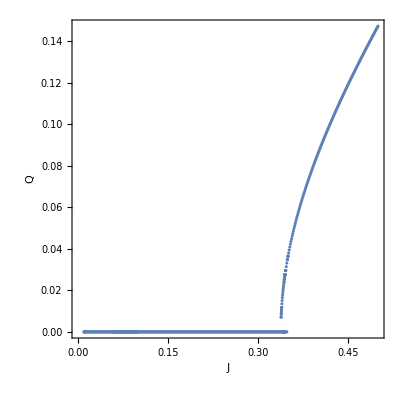
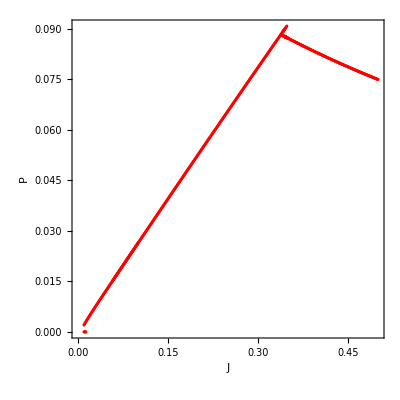
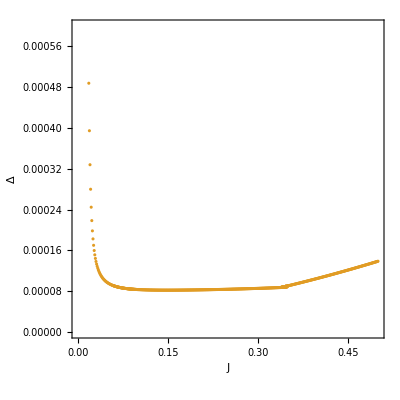

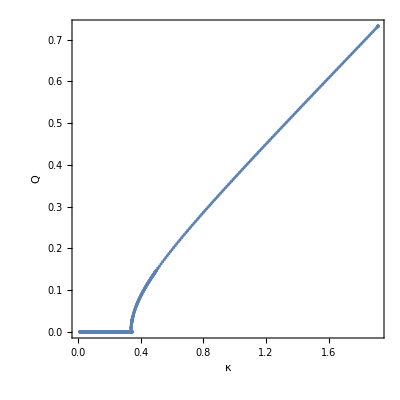
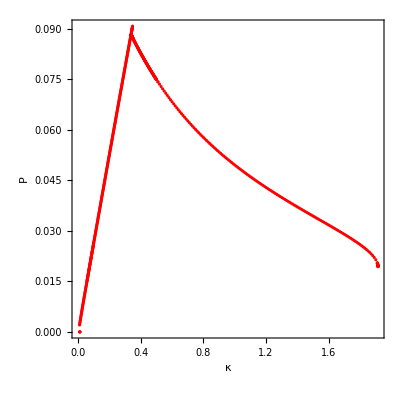
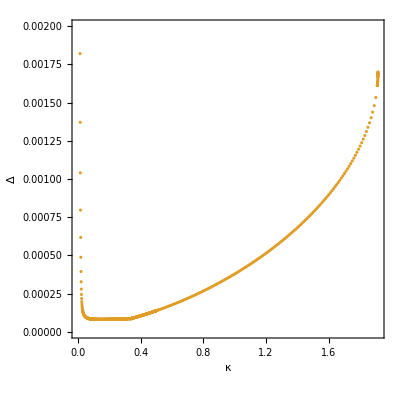

sweep over J for T=0.04  Lx=Ly=20

```mathematica
data
```

{{0.5,{0.64767,0.545359,0.153482,0.0674061,-0.210752+0. ⅈ,-0.543489}},{0.495,{0.642283,0.539831,0.150806,0.0678479,-0.211208+0. ⅈ,-0.537822}},{0.49,{0.636885,0.534303,0.148105,0.0682926,-0.211665+0. ⅈ,-0.532152}},{0.485,{0.631475,0.528773,0.145378,0.06874,-0.212122+0. ⅈ,-0.52648}},{0.48,{0.626052,0.523241,0.142625,0.0691904,-0.21258+0. ⅈ,-0.520805}},{0.475,{0.620616,0.517708,0.139842,0.0696437,-0.213039+0. ⅈ,-0.515127}},{0.47,{0.615168,0.512173,0.13703,0.0701,-0.213499+0. ⅈ,-0.509446}},{0.465,{0.609705,0.506637,0.134184,0.0705594,-0.21396+0. ⅈ,-0.503763}},{0.46,{0.604228,0.501098,0.131305,0.071022,-0.214422+0. ⅈ,-0.498077}},{0.455,{0.598737,0.495558,0.128388,0.0714878,-0.214885+0. ⅈ,-0.492387}},{0.45,{0.593231,0.490017,0.125432,0.0719569,-0.21535+0. ⅈ,-0.486695}},{0.445,{0.587709,0.484473,0.122433,0.0724294,-0.215816+0. ⅈ,-0.481}},{0.44,{0.582171,0.478928,0.119389,0.0729052,-0.216284+0. ⅈ,-0.475301}},{0.435,{0.576616,0.473381,0.116295,0.0733846,-0.216753+0. ⅈ,-0.469599}},{0.43,{0.571044,0.467832,0.113149,0.0738674,-0.217224+0. ⅈ,-0.463895}},{0.425,{0.565454,0.462281,0.109944,0.0743539,-0.217697+0. ⅈ,-0.458186}},{0.42,{0.559846,0.456727,0.106676,0.074844,-0.218171+0. ⅈ,-0.452474}},{0.415,{0.554218,0.451172,0.10334,0.0753378,-0.218647+0. ⅈ,-0.446759}},{0.41,{0.54857,0.445614,0.0999273,0.0758354,-0.219125+0. ⅈ,-0.44104}},{0.405,{0.542902,0.440054,0.0964308,0.0763368,-0.219605+0. ⅈ,-0.435318}},{0.4,{0.537213,0.434491,0.092841,0.076842,-0.220087+0. ⅈ,-0.429591}},{0.395,{0.531502,0.428926,0.0891464,0.0773511,-0.220571+0. ⅈ,-0.423861}},{0.39,{0.525768,0.423358,0.0853336,0.0778642,-0.221057+0. ⅈ,-0.418126}},{0.385,{0.520011,0.417787,0.081386,0.0783813,-0.221545+0. ⅈ,-0.412388}},{0.38,{0.514229,0.412214,0.077283,0.0789025,-0.222035+0. ⅈ,-0.406644}},{0.375,{0.508421,0.406637,0.0729985,0.0794277,-0.222527+0. ⅈ,-0.400897}},{0.37,{0.502591,0.40106,0.0685006,0.0799562,-0.22302+0. ⅈ,-0.395148}},{0.37,{0.502591,0.40106,0.0685006,0.0799562,-0.22302+0. ⅈ,-0.395148}},{0.369,{0.501418,0.39994,0.0675689,0.0800635,-0.22312+0. ⅈ,-0.393993}},{0.368,{0.500247,0.398823,0.0666284,0.08017,-0.223219+0. ⅈ,-0.392842}},{0.367,{0.499075,0.397707,0.0656767,0.0802767,-0.223318+0. ⅈ,-0.391691}},{0.366,{0.497902,0.39659,0.0647132,0.0803836,-0.223418+0. ⅈ,-0.390539}},{0.365,{0.496727,0.395473,0.0637374,0.0804907,-0.223517+0. ⅈ,-0.389387}},{0.364,{0.495552,0.394356,0.0627487,0.0805979,-0.223617+0. ⅈ,-0.388235}},{0.363,{0.494375,0.393238,0.0617465,0.0807053,-0.223716+0. ⅈ,-0.387083}},{0.362,{0.493197,0.392121,0.0607302,0.0808128,-0.223816+0. ⅈ,-0.38593}},{0.361,{0.492019,0.391003,0.0596989,0.0809205,-0.223916+0. ⅈ,-0.384778}},{0.36,{0.490839,0.389885,0.058652,0.0810284,-0.224015+0. ⅈ,-0.383625}},{0.359,{0.489657,0.388767,0.0575885,0.0811365,-0.224115+0. ⅈ,-0.382472}},{0.358,{0.488475,0.387649,0.0565075,0.0812447,-0.224215+0. ⅈ,-0.381318}},{0.357,{0.487291,0.386531,0.0554081,0.0813531,-0.224315+0. ⅈ,-0.380165}},{0.356,{0.486107,0.385413,0.0542891,0.0814617,-0.224416+0. ⅈ,-0.379011}},{0.355,{0.484921,0.384294,0.0531492,0.0815704,-0.224516+0. ⅈ,-0.377857}},{0.354,{0.483734,0.383175,0.0519871,0.0816793,-0.224616+0. ⅈ,-0.376703}},{0.353,{0.482545,0.382057,0.0508013,0.0817884,-0.224717+0. ⅈ,-0.375548}},{0.352,{0.481356,0.380937,0.04959,0.0818976,-0.224817+0. ⅈ,-0.374394}},{0.351,{0.480165,0.379818,0.0483513,0.0820071,-0.224918+0. ⅈ,-0.373239}},{0.35,{0.478973,0.378699,0.0470832,0.0821167,-0.225018+0. ⅈ,-0.372084}},{0.349,{0.477779,0.377579,0.0457831,0.0822264,-0.225119+0. ⅈ,-0.370928}},{0.348,{0.476585,0.37646,0.0444483,0.0823363,-0.22522+0. ⅈ,-0.369773}},{0.347,{0.475389,0.37534,0.0430755,0.0824465,-0.225321+0. ⅈ,-0.368617}},{0.346,{0.474192,0.37422,0.0416609,0.0825567,-0.225422+0. ⅈ,-0.367461}},{0.345,{0.472994,0.373099,0.0402002,0.0826672,-0.225523+0. ⅈ,-0.366305}},{0.344,{0.471794,0.371979,0.0386882,0.0827778,-0.225624+0. ⅈ,-0.365149}},{0.343,{0.470593,0.370858,0.0371186,0.0828885,-0.225725+0. ⅈ,-0.363992}},{0.342,{0.469391,0.369738,0.0354839,0.0829995,-0.225826+0. ⅈ,-0.362835}},{0.341,{0.468188,0.368617,0.0337747,0.0831105,-0.225928+0. ⅈ,-0.361678}},{0.34,{0.466984,0.367497,0.0319796,0.0832215,-0.226029+0. ⅈ,-0.360522}},{0.339,{0.465775,0.366373,0.0300777,0.0833336,-0.226131+0. ⅈ,-0.359362}},{0.338,{0.464567,0.365252,0.0280555,0.0834453,-0.226233+0. ⅈ,-0.358204}},{0.337,{0.463359,0.364131,0.0258833,0.0835569,-0.226334+0. ⅈ,-0.357047}},{0.337,{0.463359,0.364131,0.0258833,0.0835569,-0.226334+0. ⅈ,-0.357047}},{0.337,{0.463359,0.364131,0.0258833,0.0835569,-0.226334+0. ⅈ,-0.357047}},{0.337,{0.463359,0.364131,0.0258833,0.0835569,-0.226334+0. ⅈ,-0.357047}},{0.335,{0.455457,0.356139,5.05092×10^-8,0.0851273,-0.227397+0. ⅈ,-0.348657}},{0.334,{0.455702,0.356546,3.38986×10^-9,0.0848822,-0.227272+0. ⅈ,-0.349113}},{0.334,{0.455702,0.356546,3.38986×10^-9,0.0848822,-0.227272+0. ⅈ,-0.349113}},{0.324,{0.45802,0.360531,1.95203×10^-8,0.0824256,-0.225975+0. ⅈ,-0.353602}},{0.314,{0.460089,0.364342,6.75677×10^-10,0.0799586,-0.224593+0. ⅈ,-0.357932}},{0.304,{0.461882,0.367951,2.06589×10^-10,0.0774813,-0.223116+0. ⅈ,-0.362076}},{0.3,{0.462517,0.369331,2.06589×10^-10,0.0764876,-0.222496+0. ⅈ,-0.363674}},{0.295,{0.463239,0.371,2.06589×10^-10,0.0752433,-0.221696+0. ⅈ,-0.365618}},{0.29,{0.463877,0.372602,2.06589×10^-10,0.0739966,-0.220868+0. ⅈ,-0.367499}},{0.285,{0.464428,0.374133,2.06589×10^-10,0.0727476,-0.220008+0. ⅈ,-0.369311}},{0.28,{0.464887,0.375586,2.06589×10^-10,0.0714962,-0.219116+0. ⅈ,-0.37105}},{0.275,{0.465249,0.376956,2.06589×10^-10,0.0702425,-0.21819+0. ⅈ,-0.372708}},{0.27,{0.465507,0.378237,2.06589×10^-10,0.0689865,-0.217227+0. ⅈ,-0.374279}},{0.265,{0.465656,0.379423,2.06589×10^-10,0.0677283,-0.216225+0. ⅈ,-0.375757}},{0.26,{0.46569,0.380505,2.06589×10^-10,0.0664679,-0.215182+0. ⅈ,-0.377135}},{0.255,{0.465601,0.381476,2.06589×10^-10,0.0652052,-0.214096+0. ⅈ,-0.378403}},{0.25,{0.465383,0.382329,2.06589×10^-10,0.0639404,-0.212962+0. ⅈ,-0.379555}},{0.245,{0.465027,0.383053,2.06589×10^-10,0.0626734,-0.21178+0. ⅈ,-0.38058}},{0.24,{0.464525,0.383641,2.06589×10^-10,0.0614043,-0.210544+0. ⅈ,-0.381468}},{0.235,{0.463867,0.384081,2.06589×10^-10,0.060133,-0.209253+0. ⅈ,-0.382211}},{0.23,{0.463043,0.384363,2.06589×10^-10,0.0588596,-0.207902+0. ⅈ,-0.382795}},{0.225,{0.462044,0.384476,2.06589×10^-10,0.057584,-0.206487+0. ⅈ,-0.38321}},{0.22,{0.460858,0.384406,2.06589×10^-10,0.0563064,-0.205004+0. ⅈ,-0.383443}},{0.215,{0.459472,0.384142,2.06589×10^-10,0.0550266,-0.203449+0. ⅈ,-0.383481}},{0.21,{0.457874,0.38367,2.06589×10^-10,0.0537447,-0.201817+0. ⅈ,-0.383308}},{0.205,{0.456051,0.382974,2.06589×10^-10,0.0524606,-0.200103+0. ⅈ,-0.382911}},{0.2,{0.453987,0.38204,2.06589×10^-10,0.0511744,-0.198302+0. ⅈ,-0.382272}},{0.195,{0.451668,0.380851,2.06589×10^-10,0.049886,-0.196407+0. ⅈ,-0.381376}},{0.19,{0.449076,0.37939,2.06589×10^-10,0.0485955,-0.194414+0. ⅈ,-0.380204}},{0.185,{0.446196,0.377639,2.06589×10^-10,0.0473027,-0.192315+0. ⅈ,-0.378738}},{0.18,{0.443008,0.375578,2.06589×10^-10,0.0460076,-0.190104+0. ⅈ,-0.376959}},{0.175,{0.439494,0.373189,2.06589×10^-10,0.0447102,-0.187774+0. ⅈ,-0.374845}},{0.17,{0.435634,0.370451,1.88645×10^-12,0.0434104,-0.185318+0. ⅈ,-0.372375}},{0.165,{0.431406,0.367342,1.88645×10^-12,0.0421081,-0.182729+0. ⅈ,-0.369529}},{0.16,{0.42679,0.363841,1.88645×10^-12,0.0408033,-0.179998+0. ⅈ,-0.366282}},{0.155,{0.421764,0.359925,1.88645×10^-12,0.0394959,-0.177118+0. ⅈ,-0.362612}},{0.15,{0.416304,0.355571,1.88645×10^-12,0.0381857,-0.174079+0. ⅈ,-0.358494}},{0.145,{0.410386,0.350755,1.88645×10^-12,0.0368726,-0.170874+0. ⅈ,-0.353905}},{0.14,{0.403986,0.345455,1.88645×10^-12,0.0355565,-0.167494+0. ⅈ,-0.348819}},{0.135,{0.39708,0.339645,1.88645×10^-12,0.0342371,-0.163929+0. ⅈ,-0.343212}},{0.13,{0.389643,0.333303,1.88645×10^-12,0.0329142,-0.160171+0. ⅈ,-0.337059}},{0.125,{0.381649,0.326405,1.88645×10^-12,0.0315876,-0.156211+0. ⅈ,-0.330335}},{0.12,{0.373074,0.318929,1.88645×10^-12,0.030257,-0.15204+0. ⅈ,-0.323016}},{0.115,{0.363893,0.310852,1.88645×10^-12,0.0289219,-0.147647+0. ⅈ,-0.31508}},{0.11,{0.354082,0.302156,1.88645×10^-12,0.0275821,-0.143025+0. ⅈ,-0.306504}},{0.105,{0.343616,0.292823,1.88645×10^-12,0.0262369,-0.138164+0. ⅈ,-0.297267}},{0.1,{0.332474,0.282836,1.88645×10^-12,0.0248858,-0.133055+0. ⅈ,-0.287353}}}

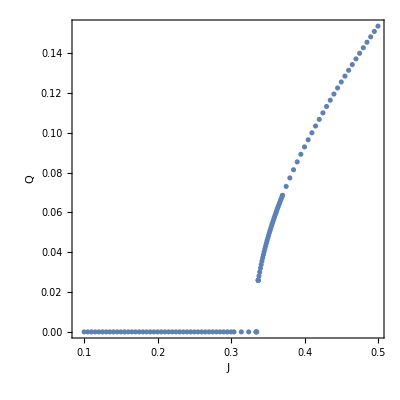
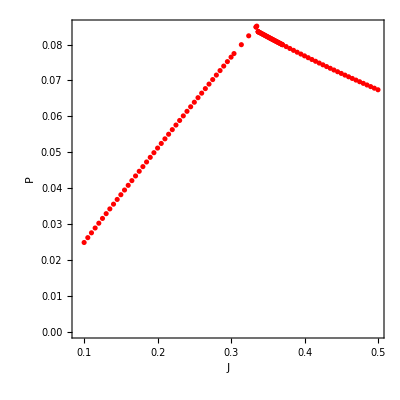
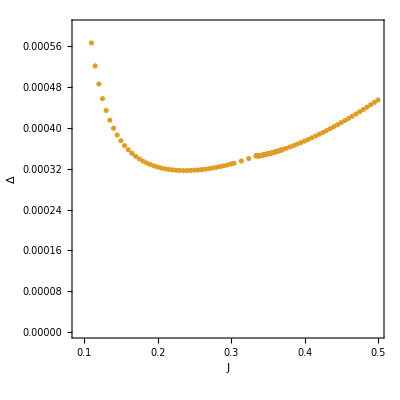

sweep for different s at T=0.02 J=0.5

```mathematica
data
```

{{1.,{0.665808,0.547282,0.147201,0.0749639,-0.229446+0. ⅈ,-0.540888}},{0.996,{0.662794,0.545207,0.14561,0.0750056,-0.229771+0. ⅈ,-0.538785}},{0.992,{0.659782,0.543134,0.14401,0.0750463,-0.230093+0. ⅈ,-0.536684}},{0.988,{0.656773,0.541063,0.1424,0.0750858,-0.230412+0. ⅈ,-0.534584}},{0.984,{0.653767,0.538993,0.140779,0.0751242,-0.230729+0. ⅈ,-0.532487}},{0.98,{0.650763,0.536925,0.139146,0.0751615,-0.231043+0. ⅈ,-0.530392}},{0.976,{0.647762,0.534859,0.137502,0.0751976,-0.231355+0. ⅈ,-0.528299}},{0.972,{0.644764,0.532795,0.135846,0.0752327,-0.231665+0. ⅈ,-0.526207}},{0.968,{0.641769,0.530733,0.134178,0.0752667,-0.231972+0. ⅈ,-0.524118}},{0.964,{0.638777,0.528672,0.132496,0.0752996,-0.232277+0. ⅈ,-0.522031}},{0.96,{0.635788,0.526613,0.130801,0.0753314,-0.232579+0. ⅈ,-0.519945}},{0.956,{0.632801,0.524556,0.129093,0.0753621,-0.232879+0. ⅈ,-0.517861}},{0.952,{0.629818,0.522501,0.127369,0.0753917,-0.233177+0. ⅈ,-0.51578}},{0.948,{0.626837,0.520447,0.125631,0.0754203,-0.233472+0. ⅈ,-0.5137}},{0.944,{0.62386,0.518395,0.123876,0.0754478,-0.233764+0. ⅈ,-0.511622}},{0.94,{0.620885,0.516345,0.122106,0.0754742,-0.234055+0. ⅈ,-0.509545}},{0.936,{0.617913,0.514297,0.120318,0.0754995,-0.234343+0. ⅈ,-0.507471}},{0.932,{0.614944,0.51225,0.118512,0.0755239,-0.234628+0. ⅈ,-0.505399}},{0.928,{0.611978,0.510205,0.116687,0.0755471,-0.234911+0. ⅈ,-0.503328}},{0.924,{0.609015,0.508162,0.114842,0.0755693,-0.235192+0. ⅈ,-0.501259}},{0.92,{0.606055,0.506121,0.112977,0.0755905,-0.235471+0. ⅈ,-0.499192}},{0.916,{0.603098,0.504081,0.11109,0.0756106,-0.235747+0. ⅈ,-0.497127}},{0.912,{0.600145,0.502043,0.10918,0.0756297,-0.236021+0. ⅈ,-0.495064}},{0.908,{0.597194,0.500006,0.107245,0.0756478,-0.236292+0. ⅈ,-0.493002}},{0.904,{0.594246,0.497971,0.105285,0.0756648,-0.236561+0. ⅈ,-0.490942}},{0.9,{0.591301,0.495938,0.103299,0.0756808,-0.236828+0. ⅈ,-0.488884}},{0.896,{0.588359,0.493907,0.101283,0.0756958,-0.237092+0. ⅈ,-0.486828}},{0.892,{0.585421,0.491877,0.0992373,0.0757097,-0.237354+0. ⅈ,-0.484773}},{0.888,{0.582485,0.489849,0.0971592,0.0757227,-0.237614+0. ⅈ,-0.482721}},{0.884,{0.579553,0.487822,0.0950467,0.0757346,-0.237872+0. ⅈ,-0.480669}},{0.88,{0.576623,0.485797,0.0928974,0.0757456,-0.238127+0. ⅈ,-0.47862}},{0.876,{0.573697,0.483774,0.0907088,0.0757555,-0.23838+0. ⅈ,-0.476572}},{0.872,{0.570774,0.481752,0.0884777,0.0757645,-0.23863+0. ⅈ,-0.474526}},{0.868,{0.567854,0.479732,0.0862011,0.0757724,-0.238879+0. ⅈ,-0.472481}},{0.864,{0.564937,0.477713,0.083875,0.0757794,-0.239124+0. ⅈ,-0.470439}},{0.86,{0.562023,0.475696,0.0814953,0.0757853,-0.239368+0. ⅈ,-0.468397}},{0.856,{0.559112,0.47368,0.0790571,0.0757903,-0.23961+0. ⅈ,-0.466358}},{0.852,{0.556205,0.471666,0.0765549,0.0757943,-0.239849+0. ⅈ,-0.46432}},{0.848,{0.5533,0.469653,0.073982,0.0757973,-0.240085+0. ⅈ,-0.462283}},{0.844,{0.550399,0.467642,0.0713309,0.0757994,-0.24032+0. ⅈ,-0.460248}},{0.84,{0.547501,0.465633,0.0685924,0.0758004,-0.240552+0. ⅈ,-0.458215}},{0.836,{0.544606,0.463624,0.0657556,0.0758005,-0.240782+0. ⅈ,-0.456183}},{0.832,{0.541714,0.461618,0.0628071,0.0757997,-0.24101+0. ⅈ,-0.454153}},{0.828,{0.49011,0.405727,1.01615×10^-7,0.0857894,-0.243395+0. ⅈ,-0.397627}},{0.824,{0.492239,0.40921,3.35333×10^-10,0.084762,-0.243386+0. ⅈ,-0.401146}},{0.82,{0.494369,0.412707,3.35333×10^-10,0.0837335,-0.243377+0. ⅈ,-0.40468}},{0.816,{0.496498,0.416216,3.35333×10^-10,0.0827039,-0.243369+0. ⅈ,-0.408227}},{0.812,{0.498627,0.419737,3.35333×10^-10,0.0816732,-0.243362+0. ⅈ,-0.411786}},{0.808,{0.500755,0.423269,3.35333×10^-10,0.0806416,-0.243355+0. ⅈ,-0.415356}},{0.804,{0.502883,0.426809,3.35333×10^-10,0.0796089,-0.243347+0. ⅈ,-0.418936}},{0.8,{0.505009,0.430358,3.35333×10^-10,0.0785752,-0.243339+0. ⅈ,-0.422525}},{0.796,{0.507132,0.433913,3.35333×10^-10,0.0775405,-0.243331+0. ⅈ,-0.426122}},{0.792,{0.509254,0.437474,3.35333×10^-10,0.0765049,-0.243321+0. ⅈ,-0.429725}},{0.832,{0.541714,0.461618,0.0628071,0.0757997,-0.24101+0. ⅈ,-0.454153}},{0.83,{0.54027,0.460615,0.061286,0.0757989,-0.241123+0. ⅈ,-0.453138}},{0.828,{0.538826,0.459612,0.0597305,0.0757978,-0.241235+0. ⅈ,-0.452124}},{0.826,{0.537383,0.45861,0.0581377,0.0757966,-0.241347+0. ⅈ,-0.45111}},{0.824,{0.535941,0.457609,0.0565047,0.0757951,-0.241458+0. ⅈ,-0.450096}},{0.822,{0.534499,0.456607,0.0548276,0.0757933,-0.241569+0. ⅈ,-0.449083}},{0.82,{0.533058,0.455606,0.0531025,0.0757913,-0.241679+0. ⅈ,-0.44807}},{0.818,{0.531618,0.454605,0.0513244,0.0757891,-0.241789+0. ⅈ,-0.447058}},{0.816,{0.530179,0.453605,0.0494875,0.0757866,-0.241898+0. ⅈ,-0.446045}},{0.814,{0.528741,0.452605,0.0475853,0.0757839,-0.242006+0. ⅈ,-0.445034}},{0.812,{0.527304,0.451605,0.0456093,0.075781,-0.242114+0. ⅈ,-0.444022}},{0.81,{0.525867,0.450606,0.0435495,0.0757778,-0.242221+0. ⅈ,-0.443011}},{0.808,{0.524431,0.449607,0.0413935,0.0757744,-0.242328+0. ⅈ,-0.442}},{0.806,{0.522996,0.448608,0.0391258,0.0757707,-0.242434+0. ⅈ,-0.44099}},{0.804,{0.521561,0.44761,0.0367247,0.0757669,-0.24254+0. ⅈ,-0.43998}},{0.802,{0.520128,0.446612,0.0341628,0.0757628,-0.242645+0. ⅈ,-0.43897}},{0.8,{0.518695,0.445613,0.0314001,0.0757585,-0.242749+0. ⅈ,-0.43796}},{0.802,{0.520128,0.446612,0.0341628,0.0757628,-0.242645+0. ⅈ,-0.43897}},{0.801,{0.519412,0.446113,0.0328104,0.0757605,-0.242697+0. ⅈ,-0.438466}},{0.8,{0.518695,0.445614,0.0314007,0.0757584,-0.242749+0. ⅈ,-0.437961}},{0.799,{0.517979,0.445115,0.0299274,0.0757561,-0.242801+0. ⅈ,-0.437456}},{0.798,{0.517263,0.444617,0.0283799,0.0757538,-0.242853+0. ⅈ,-0.436952}},{0.797,{0.516548,0.444118,0.0267454,0.0757514,-0.242905+0. ⅈ,-0.436447}},{0.796,{0.515832,0.44362,0.0250067,0.075749,-0.242957+0. ⅈ,-0.435943}},{0.795,{0.515117,0.443121,0.0231406,0.0757465,-0.243008+0. ⅈ,-0.435439}},{0.794,{0.514402,0.442623,0.0211132,0.0757439,-0.243059+0. ⅈ,-0.434934}},{0.793,{0.513687,0.442125,0.0188725,0.0757413,-0.243111+0. ⅈ,-0.43443}},{0.794,{0.514402,0.442623,0.0211132,0.0757439,-0.243059+0. ⅈ,-0.434934}},{0.793,{0.513687,0.442125,0.0188725,0.0757413,-0.243111+0. ⅈ,-0.43443}},{0.794,{0.514402,0.442623,0.0211132,0.0757439,-0.243059+0. ⅈ,-0.434934}},{0.793,{0.508724,0.436583,1.70128×10^-6,0.0767639,-0.243324+0. ⅈ,-0.428823}},{0.792,{0.509254,0.437474,2.3944×10^-8,0.0765049,-0.243321+0. ⅈ,-0.429725}},{0.791,{0.509784,0.438365,-2.44625×10^-7,0.0762458,-0.243319+0. ⅈ,-0.430626}},{0.79,{0.510313,0.439256,-2.19914×10^-8,0.0759867,-0.243316+0. ⅈ,-0.431528}},{0.789,{0.510843,0.440147,-2.20321×10^-8,0.0757275,-0.243313+0. ⅈ,-0.43243}},{0.79,{0.510313,0.439256,-2.19914×10^-8,0.0759867,-0.243316+0. ⅈ,-0.431528}},{0.79,{0.510313,0.439256,-2.19914×10^-8,0.0759867,-0.243316+0. ⅈ,-0.431528}},{0.79,{0.510313,0.439256,-2.19914×10^-8,0.0759867,-0.243316+0. ⅈ,-0.431528}},{0.79,{0.510313,0.439256,-2.19914×10^-8,0.0759867,-0.243316+0. ⅈ,-0.431528}},{0.79,{0.510313,0.439256,-2.19914×10^-8,0.0759867,-0.243316+0. ⅈ,-0.431528}},{0.79,{0.510313,0.439256,-2.19914×10^-8,0.0759867,-0.243316+0. ⅈ,-0.431528}},{0.79,{0.510313,0.439256,0,0.0759867,-0.243316+0. ⅈ,-0.431528}},{0.79,{0.510313,0.439256,0,0.0759867,-0.243316+0. ⅈ,-0.431528}},{0.78,{0.515595,0.448172,0.,0.0733925,-0.243283+0. ⅈ,-0.440553}},{0.77,{0.520842,0.457078,0.,0.0707929,-0.243231+0. ⅈ,-0.449575}},{0.76,{0.526034,0.465943,0.,0.0681882,-0.243154+0. ⅈ,-0.45856}},{0.75,{0.531148,0.474726,0.,0.0655787,-0.24304+0. ⅈ,-0.46747}},{0.74,{0.536156,0.483383,0.,0.0629649,-0.242876+0. ⅈ,-0.476261}},{0.73,{0.541018,0.49186,0.,0.0603471,-0.242647+0. ⅈ,-0.48488}},{0.72,{0.545685,0.500094,0.,0.0577254,-0.242332+0. ⅈ,-0.493264}},{0.71,{0.550097,0.508008,0.,0.0551002,-0.241908+0. ⅈ,-0.501335}},{0.7,{0.554175,0.515509,0.,0.0524718,-0.241344+0. ⅈ,-0.509004}},{0.69,{0.557821,0.522487,0.,0.0498403,-0.240604+0. ⅈ,-0.516158}},{0.68,{0.560908,0.528802,0.,0.0472059,-0.239642+0. ⅈ,-0.522659}},{0.67,{0.563278,0.534284,0.,0.0445686,-0.238397+0. ⅈ,-0.528338}},{0.66,{0.564728,0.538719,0.,0.0419285,-0.236798+0. ⅈ,-0.53298}},{0.65,{0.564999,0.541838,0.,0.0392855,-0.234749+0. ⅈ,-0.536315}},{0.64,{0.563762,0.543302,0.,0.0366394,-0.23213+0. ⅈ,-0.538005}},{0.63,{0.560598,0.542685,0.,0.03399,-0.228791+0. ⅈ,-0.537619}},{0.62,{0.554979,0.539451,0.,0.0313368,-0.224538+0. ⅈ,-0.53462}},{0.61,{0.546248,0.532933,0.,0.0286795,-0.21913+0. ⅈ,-0.528339}},{0.6,{0.533605,0.522328,0.,0.0260177,-0.212267+0. ⅈ,-0.517965}},{0.59,{0.516109,0.506689,0.,0.0233515,-0.203592+0. ⅈ,-0.502549}},{0.58,{0.492706,0.48496,0.,0.0206812,-0.192683+0. ⅈ,-0.481024}},{0.57,{0.46228,0.456027,0.,0.018007,-0.179078+0. ⅈ,-0.452272}},{0.56,{0.423769,0.418833,0.,0.0153273,-0.162292+0. ⅈ,-0.415227}},{0.55,{0.376417,0.372632,0.,0.01264,-0.141881+0. ⅈ,-0.369137}},{0.54,{0.320246,0.317457,0.,0.00994277,-0.117546+0. ⅈ,-0.314028}},{0.53,{0.256908,0.254978,0.,0.00723939,-0.0893321+0. ⅈ,-0.251562}},{0.52,{0.191344,0.190159,0.,0.00455543,-0.0579915+0. ⅈ,-0.186696}},{0.51,{0.131509,0.131124,0.,0.00175482,-0.0227543+0. ⅈ,-0.127504}}}

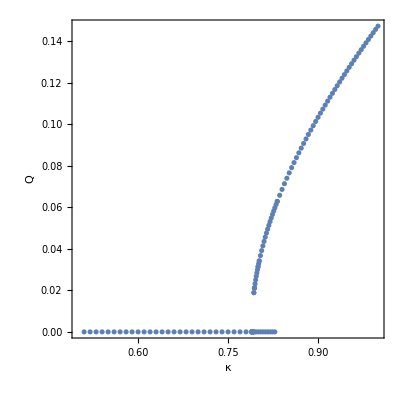
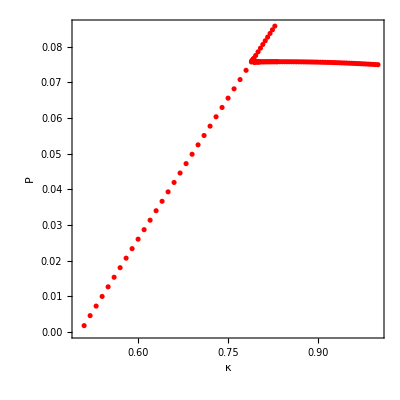
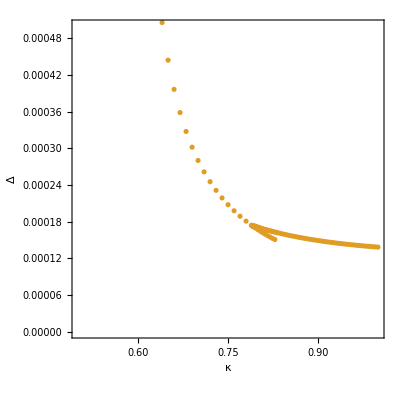

different sweep s at T=0.02 J=0.5

```mathematica
data
```

{{1.,{0.562772,0.533065,0.191728,0.0023134,-0.0275028+0. ⅈ,-0.538322}},{0.995,{0.559264,0.529886,0.190368,0.00241904,-0.0287926+0. ⅈ,-0.53505}},{0.99,{0.555769,0.52672,0.189005,0.00252239,-0.0300556+0. ⅈ,-0.53179}},{0.985,{0.552289,0.523565,0.18764,0.00262364,-0.0312954+0. ⅈ,-0.528542}},{0.98,{0.548822,0.520424,0.186274,0.00272298,-0.0325138+0. ⅈ,-0.525307}},{0.975,{0.54537,0.517295,0.184905,0.00282057,-0.0337127+0. ⅈ,-0.522085}},{0.97,{0.541932,0.514179,0.183535,0.00291652,-0.0348934+0. ⅈ,-0.518875}},{0.965,{0.538508,0.511075,0.182162,0.00301097,-0.0360572+0. ⅈ,-0.515678}},{0.96,{0.535098,0.507984,0.180786,0.003104,-0.0372051+0. ⅈ,-0.512494}},{0.955,{0.531702,0.504905,0.179408,0.0031957,-0.038338+0. ⅈ,-0.509322}},{0.95,{0.528319,0.501839,0.178028,0.00328614,-0.0394566+0. ⅈ,-0.506163}},{0.945,{0.524951,0.498785,0.176645,0.00337538,-0.0405615+0. ⅈ,-0.503015}},{0.94,{0.521595,0.495744,0.17526,0.00346347,-0.0416534+0. ⅈ,-0.499881}},{0.935,{0.518254,0.492715,0.173872,0.00355048,-0.0427328+0. ⅈ,-0.496759}},{0.93,{0.514926,0.489699,0.172481,0.00363644,-0.0438+0. ⅈ,-0.493649}},{0.925,{0.511611,0.486694,0.171087,0.00372139,-0.0448555+0. ⅈ,-0.490551}},{0.92,{0.508309,0.483702,0.16969,0.00380537,-0.0458997+0. ⅈ,-0.487465}},{0.915,{0.505021,0.480722,0.16829,0.00388841,-0.0469328+0. ⅈ,-0.484392}},{0.91,{0.501745,0.477754,0.166886,0.00397054,-0.0479552+0. ⅈ,-0.48133}},{0.905,{0.498483,0.474798,0.165479,0.0040518,-0.0489671+0. ⅈ,-0.478281}},{0.9,{0.495234,0.471853,0.164069,0.0041322,-0.0499689+0. ⅈ,-0.475244}},{0.895,{0.491997,0.468921,0.162655,0.00421177,-0.0509606+0. ⅈ,-0.472218}},{0.89,{0.488773,0.466001,0.161238,0.00429053,-0.0519425+0. ⅈ,-0.469204}},{0.885,{0.485562,0.463092,0.159817,0.00436851,-0.0529148+0. ⅈ,-0.466202}},{0.88,{0.482363,0.460195,0.158391,0.00444572,-0.0538777+0. ⅈ,-0.463212}},{0.875,{0.479176,0.457309,0.156962,0.00452218,-0.0548314+0. ⅈ,-0.460233}},{0.87,{0.476002,0.454435,0.155528,0.00459792,-0.0557761+0. ⅈ,-0.457266}},{0.865,{0.47284,0.451573,0.15409,0.00467293,-0.0567118+0. ⅈ,-0.45431}},{0.86,{0.46969,0.448722,0.152648,0.00474725,-0.0576387+0. ⅈ,-0.451366}},{0.855,{0.466552,0.445882,0.1512,0.00482089,-0.058557+0. ⅈ,-0.448433}},{0.85,{0.463426,0.443053,0.149748,0.00489386,-0.0594667+0. ⅈ,-0.445511}},{0.845,{0.460312,0.440235,0.148291,0.00496617,-0.0603681+0. ⅈ,-0.4426}},{0.84,{0.457209,0.437428,0.146828,0.00503784,-0.0612613+0. ⅈ,-0.4397}},{0.835,{0.454118,0.434633,0.145361,0.00510888,-0.0621462+0. ⅈ,-0.436811}},{0.83,{0.451038,0.431848,0.143887,0.0051793,-0.0630231+0. ⅈ,-0.433933}},{0.825,{0.44797,0.429073,0.142408,0.00524911,-0.0638921+0. ⅈ,-0.431066}},{0.82,{0.444913,0.42631,0.140922,0.00531833,-0.0647532+0. ⅈ,-0.428209}},{0.815,{0.441867,0.423557,0.139431,0.00538695,-0.0656065+0. ⅈ,-0.425363}},{0.81,{0.438832,0.420815,0.137933,0.005455,-0.0664521+0. ⅈ,-0.422527}},{0.805,{0.435808,0.418083,0.136428,0.00552247,-0.0672901+0. ⅈ,-0.419702}},{0.8,{0.432795,0.415361,0.134916,0.00558939,-0.0681206+0. ⅈ,-0.416888}},{0.795,{0.429792,0.41265,0.133397,0.00565575,-0.0689436+0. ⅈ,-0.414083}},{0.79,{0.426801,0.409948,0.13187,0.00572157,-0.0697592+0. ⅈ,-0.411289}},{0.785,{0.423819,0.407257,0.130335,0.00578684,-0.0705675+0. ⅈ,-0.408505}},{0.78,{0.420849,0.404576,0.128793,0.00585159,-0.0713684+0. ⅈ,-0.40573}},{0.775,{0.417888,0.401905,0.127241,0.0059158,-0.0721622+0. ⅈ,-0.402966}},{0.77,{0.414938,0.399244,0.125681,0.0059795,-0.0729488+0. ⅈ,-0.400212}},{0.765,{0.411998,0.396592,0.124112,0.00604268,-0.0737282+0. ⅈ,-0.397467}},{0.76,{0.409067,0.39395,0.122533,0.00610535,-0.0745006+0. ⅈ,-0.394732}},{0.755,{0.406147,0.391318,0.120944,0.00616752,-0.075266+0. ⅈ,-0.392006}},{0.75,{0.403237,0.388695,0.119344,0.00622919,-0.0760243+0. ⅈ,-0.38929}},{0.745,{0.400336,0.386081,0.117734,0.00629036,-0.0767757+0. ⅈ,-0.386584}},{0.74,{0.397445,0.383477,0.116112,0.00635104,-0.0775202+0. ⅈ,-0.383886}},{0.735,{0.394563,0.380882,0.114478,0.00641124,-0.0782578+0. ⅈ,-0.381199}},{0.73,{0.391691,0.378296,0.112832,0.00647095,-0.0789885+0. ⅈ,-0.37852}},{0.725,{0.388829,0.37572,0.111173,0.00653018,-0.0797125+0. ⅈ,-0.37585}},{0.72,{0.385975,0.373152,0.1095,0.00658893,-0.0804296+0. ⅈ,-0.373189}},{0.715,{0.383131,0.370593,0.107813,0.00664721,-0.08114+0. ⅈ,-0.370538}},{0.71,{0.380296,0.368043,0.10611,0.00670502,-0.0818436+0. ⅈ,-0.367895}},{0.705,{0.37747,0.365502,0.104392,0.00676236,-0.0825405+0. ⅈ,-0.365261}},{0.7,{0.374652,0.36297,0.102657,0.00681923,-0.0832308+0. ⅈ,-0.362635}},{0.695,{0.371844,0.360446,0.100904,0.00687564,-0.0839143+0. ⅈ,-0.360018}},{0.69,{0.369044,0.357931,0.0991333,0.00693159,-0.0845912+0. ⅈ,-0.35741}},{0.685,{0.366253,0.355424,0.0973425,0.00698708,-0.0852615+0. ⅈ,-0.354811}},{0.68,{0.363471,0.352926,0.095531,0.00704211,-0.0859252+0. ⅈ,-0.352219}},{0.675,{0.360697,0.350436,0.0936975,0.00709668,-0.0865823+0. ⅈ,-0.349636}},{0.67,{0.357931,0.347954,0.0918406,0.00715081,-0.0872328+0. ⅈ,-0.347061}},{0.665,{0.355173,0.345481,0.0899589,0.00720448,-0.0878767+0. ⅈ,-0.344495}},{0.66,{0.352424,0.343015,0.0880507,0.00725769,-0.0885141+0. ⅈ,-0.341936}},{0.655,{0.349683,0.340558,0.0861142,0.00731046,-0.089145+0. ⅈ,-0.339386}},{0.65,{0.34695,0.338109,0.0841475,0.00736278,-0.0897693+0. ⅈ,-0.336844}},{0.645,{0.344226,0.335667,0.0821483,0.00741465,-0.0903871+0. ⅈ,-0.334309}},{0.64,{0.341509,0.333233,0.0801142,0.00746607,-0.0909984+0. ⅈ,-0.331782}},{0.635,{0.338799,0.330808,0.0780424,0.00751705,-0.0916032+0. ⅈ,-0.329263}},{0.63,{0.336098,0.328389,0.0759297,0.00756758,-0.0922016+0. ⅈ,-0.326752}},{0.625,{0.333404,0.325979,0.0737727,0.00761766,-0.0927934+0. ⅈ,-0.324249}},{0.62,{0.330718,0.323576,0.0715672,0.0076673,-0.0933788+0. ⅈ,-0.321753}},{0.615,{0.32804,0.32118,0.0693085,0.0077165,-0.0939578+0. ⅈ,-0.319264}},{0.61,{0.325369,0.318792,0.0669914,0.00776525,-0.0945302+0. ⅈ,-0.316783}},{0.605,{0.322705,0.316412,0.0646094,0.00781356,-0.0950963+0. ⅈ,-0.31431}},{0.6,{0.320049,0.314039,0.062155,0.00786142,-0.0956559+0. ⅈ,-0.311843}},{0.595,{0.3174,0.311673,0.0596192,0.00790884,-0.096209+0. ⅈ,-0.309384}},{0.59,{0.314758,0.309314,0.0569912,0.00795582,-0.0967557+0. ⅈ,-0.306933}},{0.585,{0.312124,0.306963,0.0542575,0.00800235,-0.097296+0. ⅈ,-0.304488}},{0.58,{0.309496,0.304618,0.0514011,0.00804844,-0.0978299+0. ⅈ,-0.302051}},{0.575,{0.306876,0.302281,0.0484003,0.00809408,-0.0983573+0. ⅈ,-0.29962}},{0.57,{0.304262,0.299951,0.0452264,0.00813928,-0.0988783+0. ⅈ,-0.297197}},{0.565,{0.301656,0.297627,0.0418399,0.00818402,-0.0993929+0. ⅈ,-0.29478}},{0.56,{0.299056,0.29531,0.0381842,0.00822832,-0.0999009+0. ⅈ,-0.292371}},{0.555,{0.296462,0.293,0.0341732,0.00827215,-0.100402+0. ⅈ,-0.289967}},{0.55,{0.293874,0.290695,0.0296632,0.00831548,-0.100897+0. ⅈ,-0.28757}},{0.545,{0.2913,0.288405,0.024375,0.00835859,-0.101387+0. ⅈ,-0.285186}},{0.54,{0.288728,0.286116,0.0176285,0.00840111,-0.10187+0. ⅈ,-0.282804}},{0.535,{0.286157,0.283829,0.00545481,0.00844292,-0.102343+0. ⅈ,-0.280424}},{0.53,{0.256906,0.254975,-1.45918×10^-6,0.00723939,-0.0893321+0. ⅈ,-0.25156}},{0.525,{0.223919,0.222373,1.40208×10^-11,0.00589262,-0.0739735+0. ⅈ,-0.218942}},{0.52,{0.191347,0.190162,1.40208×10^-11,0.00455543,-0.0579914+0. ⅈ,-0.186699}},{0.515,{0.160321,0.159498,1.40208×10^-11,0.00321534,-0.0413721+0. ⅈ,-0.155979}},{0.51,{0.131515,0.13113,1.40208×10^-11,0.0017552,-0.0227593+0. ⅈ,-0.12751}}}

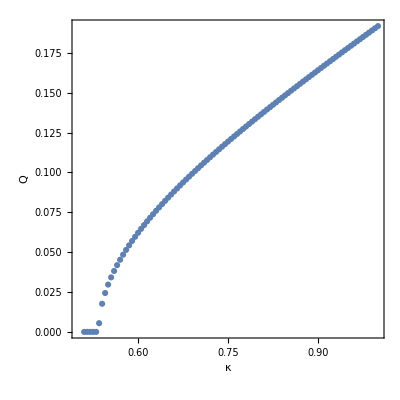
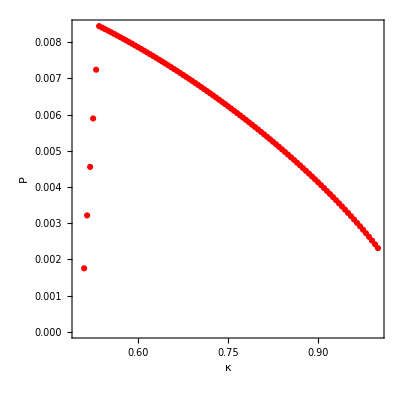
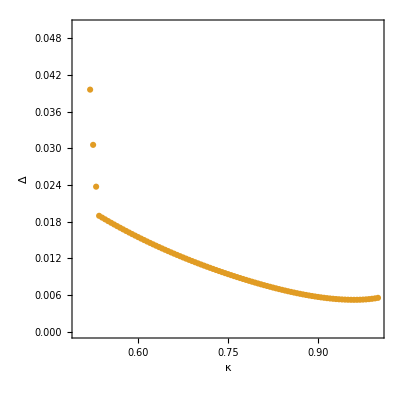

at smaller temperatures T=0.005 J=0.5

```mathematica
data
```

{{1.,{0.549063,0.541574,0.192036,0.000334074,-0.0159217+0. ⅈ,-0.542917}},{0.995,{0.54555,0.538147,0.190702,0.000358664,-0.0171181+0. ⅈ,-0.539466}},{0.99,{0.542055,0.534737,0.189368,0.000382955,-0.0183026+0. ⅈ,-0.536033}},{0.985,{0.538579,0.531345,0.188032,0.000406935,-0.0194747+0. ⅈ,-0.532617}},{0.98,{0.53512,0.52797,0.186695,0.000430604,-0.0206341+0. ⅈ,-0.529219}},{0.975,{0.531679,0.524612,0.185357,0.000453965,-0.021781+0. ⅈ,-0.525838}},{0.97,{0.528255,0.521271,0.184018,0.000477027,-0.0229156+0. ⅈ,-0.522473}},{0.965,{0.524848,0.517946,0.182678,0.000499801,-0.0240381+0. ⅈ,-0.519125}},{0.96,{0.521457,0.514638,0.181336,0.000522297,-0.0251491+0. ⅈ,-0.515793}},{0.955,{0.518083,0.511345,0.179993,0.000544526,-0.0262488+0. ⅈ,-0.512477}},{0.95,{0.514725,0.508069,0.178648,0.000566499,-0.0273377+0. ⅈ,-0.509177}},{0.945,{0.511384,0.504808,0.177302,0.000588224,-0.0284162+0. ⅈ,-0.505893}},{0.94,{0.508058,0.501563,0.175954,0.000609713,-0.0294844+0. ⅈ,-0.502625}},{0.935,{0.504749,0.498334,0.174604,0.000630994,-0.0305439+0. ⅈ,-0.499372}},{0.93,{0.501455,0.495119,0.173253,0.000652032,-0.0315926+0. ⅈ,-0.496134}},{0.925,{0.498176,0.49192,0.1719,0.000672856,-0.0326321+0. ⅈ,-0.492912}},{0.92,{0.494913,0.488737,0.170545,0.000693474,-0.0336625+0. ⅈ,-0.489705}},{0.915,{0.491666,0.485568,0.169187,0.000713892,-0.034684+0. ⅈ,-0.486513}},{0.91,{0.488434,0.482414,0.167828,0.000734114,-0.0356969+0. ⅈ,-0.483336}},{0.905,{0.485217,0.479275,0.166467,0.000754147,-0.0367012+0. ⅈ,-0.480173}},{0.9,{0.482014,0.476151,0.165103,0.000773995,-0.0376971+0. ⅈ,-0.477026}},{0.895,{0.478827,0.473041,0.163737,0.000793662,-0.0386848+0. ⅈ,-0.473892}},{0.89,{0.475655,0.469946,0.162368,0.000813153,-0.0396643+0. ⅈ,-0.470774}},{0.885,{0.472497,0.466865,0.160996,0.000832472,-0.0406359+0. ⅈ,-0.46767}},{0.88,{0.469353,0.463799,0.159622,0.000851621,-0.0415995+0. ⅈ,-0.46458}},{0.875,{0.466224,0.460746,0.158245,0.000870604,-0.0425553+0. ⅈ,-0.461504}},{0.87,{0.463109,0.457708,0.156865,0.000889425,-0.0435035+0. ⅈ,-0.458442}},{0.865,{0.460009,0.454683,0.155483,0.000908086,-0.0444439+0. ⅈ,-0.455394}},{0.86,{0.456922,0.451672,0.154096,0.000926589,-0.0453768+0. ⅈ,-0.45236}},{0.855,{0.453849,0.448675,0.152707,0.000944938,-0.0463022+0. ⅈ,-0.449339}},{0.85,{0.45079,0.445691,0.151314,0.000963136,-0.0472202+0. ⅈ,-0.446332}},{0.845,{0.447745,0.442721,0.149918,0.000981183,-0.0481308+0. ⅈ,-0.443339}},{0.84,{0.444713,0.439765,0.148517,0.000999083,-0.0490341+0. ⅈ,-0.440359}},{0.835,{0.441695,0.436821,0.147113,0.00101684,-0.0499301+0. ⅈ,-0.437392}},{0.83,{0.43869,0.43389,0.145705,0.00103445,-0.050819+0. ⅈ,-0.434438}},{0.825,{0.435698,0.430973,0.144293,0.00105192,-0.0517006+0. ⅈ,-0.431497}},{0.82,{0.432719,0.428068,0.142876,0.00106925,-0.0525752+0. ⅈ,-0.428569}},{0.815,{0.429753,0.425176,0.141455,0.00108644,-0.0534427+0. ⅈ,-0.425654}},{0.81,{0.426799,0.422297,0.140029,0.0011035,-0.0543032+0. ⅈ,-0.422751}},{0.805,{0.423859,0.41943,0.138598,0.00112042,-0.0551567+0. ⅈ,-0.419861}},{0.8,{0.420931,0.416576,0.137163,0.00113721,-0.0560032+0. ⅈ,-0.416983}},{0.795,{0.418015,0.413734,0.135721,0.00115386,-0.0568429+0. ⅈ,-0.414118}},{0.79,{0.415112,0.410904,0.134275,0.00117039,-0.0576757+0. ⅈ,-0.411265}},{0.785,{0.412221,0.408086,0.132822,0.00118679,-0.0585017+0. ⅈ,-0.408423}},{0.78,{0.409343,0.405281,0.131364,0.00120306,-0.059321+0. ⅈ,-0.405594}},{0.775,{0.406476,0.402487,0.1299,0.00121921,-0.0601335+0. ⅈ,-0.402777}},{0.77,{0.403621,0.399705,0.128429,0.00123523,-0.0609393+0. ⅈ,-0.399972}},{0.765,{0.400778,0.396934,0.126951,0.00125113,-0.0617384+0. ⅈ,-0.397178}},{0.76,{0.397946,0.394175,0.125467,0.00126691,-0.062531+0. ⅈ,-0.394396}},{0.755,{0.395126,0.391428,0.123975,0.00128257,-0.063317+0. ⅈ,-0.391625}},{0.75,{0.392318,0.388692,0.122476,0.00129811,-0.0640964+0. ⅈ,-0.388865}},{0.745,{0.389521,0.385967,0.120968,0.00131354,-0.0648693+0. ⅈ,-0.386117}},{0.74,{0.386735,0.383253,0.119453,0.00132884,-0.0656358+0. ⅈ,-0.38338}},{0.735,{0.38396,0.380551,0.117929,0.00134404,-0.0663959+0. ⅈ,-0.380654}},{0.73,{0.381196,0.377859,0.116395,0.00135912,-0.0671496+0. ⅈ,-0.377939}},{0.725,{0.378444,0.375178,0.114853,0.00137408,-0.067897+0. ⅈ,-0.375235}},{0.72,{0.375702,0.372508,0.113301,0.00138894,-0.068638+0. ⅈ,-0.372542}},{0.715,{0.372971,0.369849,0.111738,0.00140368,-0.0693728+0. ⅈ,-0.369859}},{0.71,{0.37025,0.3672,0.110165,0.00141832,-0.0701014+0. ⅈ,-0.367187}},{0.705,{0.36754,0.364562,0.10858,0.00143285,-0.0708238+0. ⅈ,-0.364525}},{0.7,{0.364841,0.361934,0.106984,0.00144728,-0.0715401+0. ⅈ,-0.361874}},{0.695,{0.362152,0.359316,0.105375,0.00146159,-0.0722503+0. ⅈ,-0.359233}},{0.69,{0.359473,0.356709,0.103753,0.00147581,-0.0729545+0. ⅈ,-0.356602}},{0.685,{0.356804,0.354111,0.102117,0.00148992,-0.0736526+0. ⅈ,-0.353981}},{0.68,{0.354146,0.351524,0.100467,0.00150393,-0.0743448+0. ⅈ,-0.35137}},{0.675,{0.351497,0.348947,0.0988024,0.00151784,-0.075031+0. ⅈ,-0.34877}},{0.67,{0.348858,0.346379,0.0971214,0.00153165,-0.0757114+0. ⅈ,-0.346179}},{0.665,{0.346229,0.343821,0.0954235,0.00154537,-0.0763859+0. ⅈ,-0.343598}},{0.66,{0.34361,0.341273,0.0937077,0.00155898,-0.0770546+0. ⅈ,-0.341026}},{0.655,{0.341001,0.338735,0.0919731,0.0015725,-0.0777175+0. ⅈ,-0.338464}},{0.65,{0.338401,0.336206,0.0902185,0.00158592,-0.0783747+0. ⅈ,-0.335912}},{0.645,{0.33581,0.333686,0.0884426,0.00159925,-0.0790262+0. ⅈ,-0.333369}},{0.64,{0.333229,0.331176,0.0866441,0.00161249,-0.0796721+0. ⅈ,-0.330836}},{0.635,{0.330658,0.328675,0.0848214,0.00162564,-0.0803123+0. ⅈ,-0.328311}},{0.63,{0.328095,0.326184,0.0829731,0.00163869,-0.0809469+0. ⅈ,-0.325796}},{0.625,{0.325542,0.323701,0.0810971,0.00165165,-0.081576+0. ⅈ,-0.323291}},{0.62,{0.322997,0.321228,0.0791916,0.00166453,-0.0821996+0. ⅈ,-0.320794}},{0.615,{0.320462,0.318763,0.0772543,0.00167732,-0.0828177+0. ⅈ,-0.318306}},{0.61,{0.317936,0.316308,0.0752826,0.00169001,-0.0834304+0. ⅈ,-0.315827}},{0.605,{0.315418,0.313861,0.0732739,0.00170263,-0.0840376+0. ⅈ,-0.313357}},{0.6,{0.312909,0.311423,0.0712247,0.00171515,-0.0846395+0. ⅈ,-0.310895}},{0.595,{0.310409,0.308994,0.0691316,0.00172759,-0.085236+0. ⅈ,-0.308443}},{0.59,{0.307918,0.306573,0.0669903,0.00173995,-0.0858273+0. ⅈ,-0.305999}},{0.585,{0.305435,0.304161,0.0647959,0.00175222,-0.0864132+0. ⅈ,-0.303563}},{0.58,{0.302961,0.301758,0.0625429,0.00176442,-0.0869939+0. ⅈ,-0.301136}},{0.575,{0.300495,0.299363,0.0602246,0.00177653,-0.0875693+0. ⅈ,-0.298717}},{0.57,{0.298037,0.296976,0.0578331,0.00178855,-0.0881396+0. ⅈ,-0.296307}},{0.565,{0.295588,0.294597,0.0553588,0.0018005,-0.0887047+0. ⅈ,-0.293905}},{0.56,{0.293147,0.292227,0.05279,0.00181237,-0.0892647+0. ⅈ,-0.291512}},{0.555,{0.290714,0.289865,0.0501121,0.00182416,-0.0898196+0. ⅈ,-0.289126}},{0.55,{0.288289,0.287511,0.0473065,0.00183588,-0.0903694+0. ⅈ,-0.286749}},{0.545,{0.285872,0.285165,0.0443488,0.00184751,-0.0909142+0. ⅈ,-0.284379}},{0.54,{0.283464,0.282827,0.0412064,0.00185907,-0.091454+0. ⅈ,-0.282018}},{0.535,{0.281062,0.280497,0.037833,0.00187055,-0.0919888+0. ⅈ,-0.279664}},{0.53,{0.278669,0.278174,0.0341603,0.00188196,-0.0925187+0. ⅈ,-0.277318}},{0.525,{0.276282,0.275859,0.0300789,0.0018933,-0.0930436+0. ⅈ,-0.274978}},{0.52,{0.273909,0.273556,0.0253905,0.00190452,-0.0935619+0. ⅈ,-0.272652}},{0.515,{0.271539,0.271257,0.0196687,0.0019157,-0.0940768+0. ⅈ,-0.27033}},{0.51,{0.269174,0.268963,0.011456,0.00192679,-0.0945859+0. ⅈ,-0.268012}},{0.505,{0.189613,0.189513,2.42893×10^-7,0.00128985,-0.0653485+0. ⅈ,-0.188575}}}

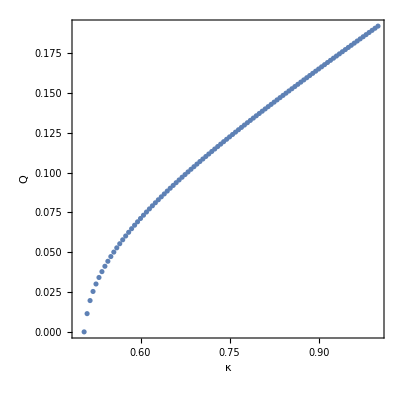
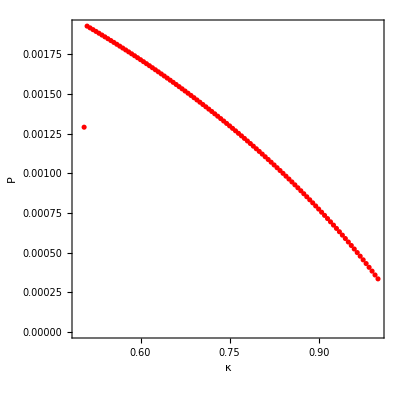
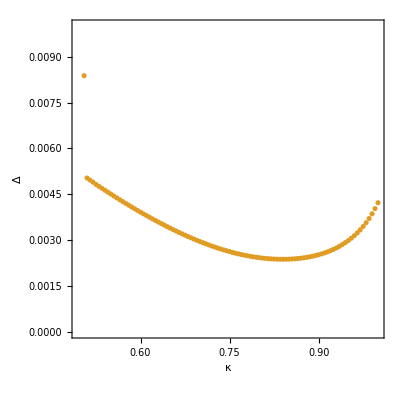

sweep for T=0.02 J=0.5 gapped solution

```mathematica
data
```

{{1.,{0.559945,0.530187,0.192026,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.535529}},{0.995,{0.55622,0.526796,0.190698,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.53205}},{0.99,{0.552516,0.523426,0.18937,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.528591}},{0.985,{0.548834,0.520076,0.18804,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.525152}},{0.98,{0.545172,0.516747,0.18671,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.521734}},{0.975,{0.541531,0.513438,0.185379,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.518336}},{0.97,{0.53791,0.510149,0.184048,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.514957}},{0.965,{0.534311,0.50688,0.182715,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.511599}},{0.96,{0.530731,0.503631,0.181381,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.508259}},{0.955,{0.527172,0.5004,0.180046,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.504939}},{0.95,{0.523632,0.497189,0.17871,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.501637}},{0.945,{0.520112,0.493996,0.177372,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.498354}},{0.94,{0.51661,0.490821,0.176034,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.495089}},{0.935,{0.513128,0.487665,0.174693,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.491842}},{0.93,{0.509663,0.484525,0.173352,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.488612}},{0.925,{0.506218,0.481403,0.172008,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.485399}},{0.92,{0.50279,0.478299,0.170663,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.482204}},{0.915,{0.49938,0.475211,0.169316,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.479025}},{0.91,{0.495987,0.472139,0.167968,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.475863}},{0.905,{0.492612,0.469084,0.166617,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.472717}},{0.9,{0.489254,0.466045,0.165264,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.469587}},{0.895,{0.485912,0.463021,0.16391,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.466472}},{0.89,{0.482588,0.460013,0.162553,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.463374}},{0.885,{0.479279,0.457021,0.161193,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.46029}},{0.88,{0.475987,0.454044,0.159831,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.457222}},{0.875,{0.472711,0.451082,0.158467,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.45417}},{0.87,{0.469451,0.448135,0.1571,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.451131}},{0.865,{0.466207,0.445203,0.155731,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.448108}},{0.86,{0.462978,0.442285,0.154358,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.445099}},{0.855,{0.459764,0.439381,0.152983,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.442105}},{0.85,{0.456566,0.436492,0.151604,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.439125}},{0.845,{0.453382,0.433617,0.150222,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.436158}},{0.84,{0.450214,0.430755,0.148837,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.433206}},{0.835,{0.44706,0.427908,0.147449,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.430267}},{0.83,{0.44392,0.425074,0.146056,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.427342}},{0.825,{0.440795,0.422253,0.14466,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.424431}},{0.82,{0.437684,0.419446,0.143261,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.421533}},{0.815,{0.434587,0.416651,0.141857,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.418648}},{0.81,{0.431504,0.41387,0.140448,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.415776}},{0.805,{0.428435,0.411102,0.139036,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.412917}},{0.8,{0.425379,0.408347,0.137618,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.410071}},{0.795,{0.422336,0.405604,0.136196,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.407237}},{0.79,{0.419307,0.402874,0.134769,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.404416}},{0.785,{0.416292,0.400156,0.133337,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.401607}},{0.78,{0.413289,0.39745,0.131899,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.398811}},{0.775,{0.410299,0.394757,0.130456,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.396027}},{0.77,{0.407322,0.392076,0.129007,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.393255}},{0.765,{0.404357,0.389406,0.127551,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.390495}},{0.76,{0.401405,0.386749,0.12609,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.387747}},{0.755,{0.398466,0.384103,0.124622,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.38501}},{0.75,{0.395538,0.381469,0.123146,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.382285}},{0.745,{0.392623,0.378846,0.121664,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.379572}},{0.74,{0.38972,0.376235,0.120174,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.37687}},{0.735,{0.386829,0.373635,0.118677,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.374179}},{0.73,{0.38395,0.371046,0.117171,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.371499}},{0.725,{0.381082,0.368468,0.115656,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.368831}},{0.72,{0.378226,0.365901,0.114133,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.366173}},{0.715,{0.375381,0.363345,0.1126,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.363526}},{0.71,{0.372547,0.3608,0.111057,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.360891}},{0.705,{0.369725,0.358265,0.109505,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.358265}},{0.7,{0.366914,0.355741,0.107941,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.355651}},{0.695,{0.364114,0.353228,0.106366,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.353046}},{0.69,{0.361325,0.350725,0.10478,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.350453}},{0.685,{0.358546,0.348232,0.103181,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.347869}},{0.68,{0.355779,0.345749,0.101569,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.345296}},{0.675,{0.353021,0.343277,0.0999431,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.342732}},{0.67,{0.350275,0.340814,0.0983029,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.340179}},{0.665,{0.347538,0.338362,0.0966475,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.337636}},{0.66,{0.344813,0.335919,0.094976,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.335102}},{0.655,{0.342097,0.333486,0.0932875,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.332579}},{0.65,{0.339391,0.331063,0.0915811,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.330065}},{0.645,{0.336695,0.328649,0.0898555,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.32756}},{0.64,{0.33401,0.326245,0.0881098,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.325065}},{0.635,{0.331334,0.32385,0.0863425,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.32258}},{0.63,{0.328667,0.321465,0.0845524,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.320104}},{0.625,{0.326011,0.319089,0.0827378,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.317637}},{0.62,{0.323364,0.316722,0.080897,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.315179}},{0.615,{0.320726,0.314364,0.0790282,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.31273}},{0.61,{0.318098,0.312015,0.0771293,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.310291}},{0.605,{0.315479,0.309675,0.075198,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.30786}},{0.6,{0.312869,0.307344,0.0732315,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.305438}},{0.595,{0.310269,0.305022,0.071227,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.303025}},{0.59,{0.307677,0.302709,0.069181,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.300621}},{0.585,{0.305095,0.300405,0.0670898,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.298226}},{0.58,{0.302521,0.298109,0.0649489,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.295839}},{0.575,{0.299957,0.295821,0.0627531,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.29346}},{0.57,{0.297401,0.293543,0.0604963,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.291091}},{0.565,{0.294854,0.291272,0.0581716,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.288729}},{0.56,{0.292315,0.28901,0.0557701,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.286376}},{0.555,{0.289785,0.286756,0.0532816,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.284031}},{0.55,{0.287263,0.284511,0.0506931,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.281695}},{0.545,{0.28475,0.282274,0.0479884,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.279366}},{0.54,{0.282245,0.280045,0.0451464,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.277046}},{0.535,{0.279748,0.277824,0.0421394,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.274734}},{0.53,{0.27726,0.275611,0.038929,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.272429}},{0.525,{0.274779,0.273406,0.03546,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.270133}},{0.52,{0.272307,0.271208,0.0316473,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.267844}},{0.515,{0.269842,0.269018,0.0273478,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.265563}},{0.51,{0.267384,0.266835,0.0222827,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.263288}},{0.505,{0.264923,0.264649,0.0157424,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.26101}},{0.5,{0.262406,0.262406,0.000335019,1.26184×10^-12,-8.85727×10^-11+0. ⅈ,-0.258676}}}

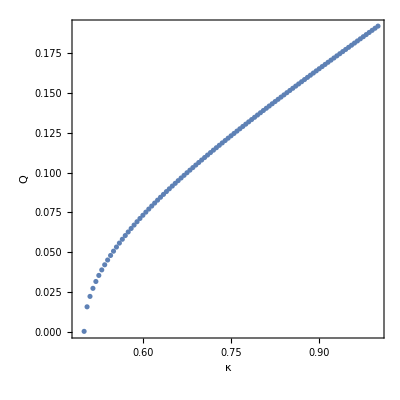
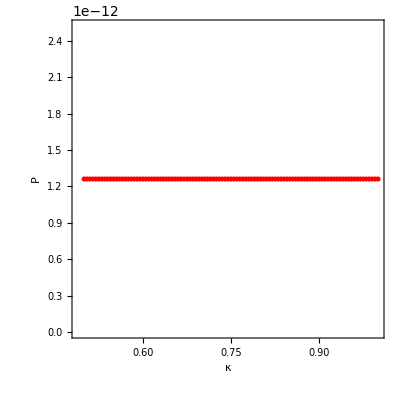
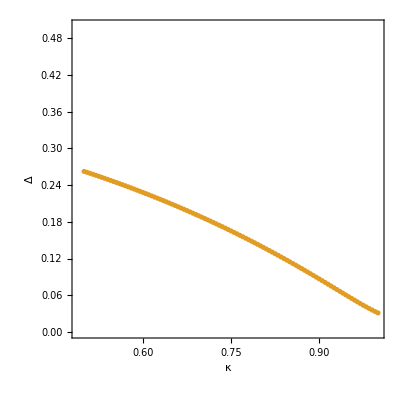

sweep for different s at T=0.04 J=0.5

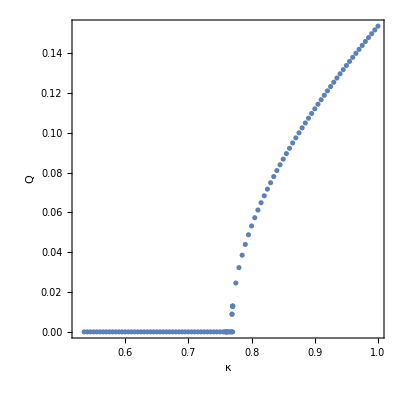
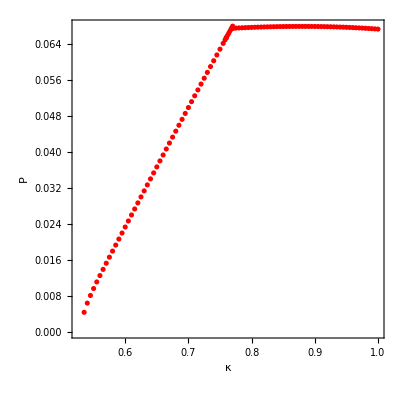
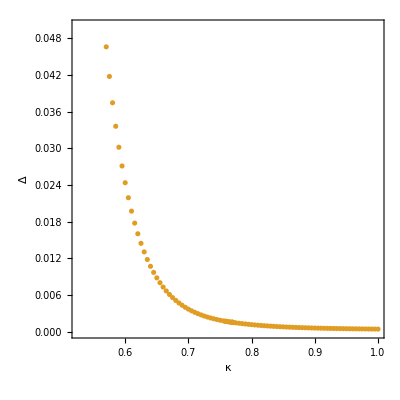

sweep for J=1 T=0.02

```mathematica
data
```

{{1.,{1.19132,1.09644,0.369264,0.0495667,-0.213507+0. ⅈ,-1.09363}},{0.995,{1.184,1.09046,0.366401,0.0494717,-0.214071+0. ⅈ,-1.08761}},{0.99,{1.17669,1.08448,0.363535,0.049372,-0.214627+0. ⅈ,-1.0816}},{0.985,{1.16939,1.07851,0.360666,0.0492674,-0.215175+0. ⅈ,-1.07559}},{0.98,{1.1621,1.07255,0.357793,0.0491581,-0.215713+0. ⅈ,-1.06959}},{0.975,{1.15483,1.0666,0.354917,0.0490439,-0.216243+0. ⅈ,-1.0636}},{0.97,{1.14757,1.06066,0.352037,0.0489249,-0.216764+0. ⅈ,-1.05762}},{0.965,{1.14031,1.05472,0.349154,0.0488011,-0.217275+0. ⅈ,-1.05165}},{0.96,{1.13308,1.04879,0.346267,0.0486724,-0.217778+0. ⅈ,-1.04568}},{0.955,{1.12585,1.04287,0.343376,0.0485389,-0.218272+0. ⅈ,-1.03973}},{0.95,{1.11864,1.03695,0.340481,0.0484004,-0.218757+0. ⅈ,-1.03378}},{0.945,{1.11144,1.03104,0.337582,0.0482571,-0.219232+0. ⅈ,-1.02784}},{0.94,{1.10425,1.02514,0.334679,0.0481087,-0.219698+0. ⅈ,-1.02191}},{0.935,{1.09708,1.01925,0.331771,0.0479555,-0.220155+0. ⅈ,-1.01598}},{0.93,{1.08991,1.01337,0.328859,0.0477972,-0.220602+0. ⅈ,-1.01007}},{0.925,{1.08277,1.00749,0.325943,0.0476338,-0.221039+0. ⅈ,-1.00416}},{0.92,{1.07563,1.00162,0.323023,0.0474654,-0.221467+0. ⅈ,-0.99826}},{0.915,{1.06851,0.995755,0.320097,0.0472918,-0.221885+0. ⅈ,-0.992369}},{0.91,{1.0614,0.989899,0.317167,0.0471131,-0.222292+0. ⅈ,-0.986485}},{0.905,{1.05431,0.984051,0.314232,0.0469291,-0.22269+0. ⅈ,-0.98061}},{0.9,{1.04722,0.978211,0.311291,0.0467399,-0.223077+0. ⅈ,-0.974743}},{0.895,{1.04016,0.972377,0.308346,0.0465453,-0.223454+0. ⅈ,-0.968884}},{0.89,{1.0331,0.966551,0.305395,0.0463453,-0.22382+0. ⅈ,-0.963033}},{0.885,{1.02606,0.960732,0.302439,0.0461398,-0.224175+0. ⅈ,-0.957189}},{0.88,{1.01904,0.95492,0.299477,0.0459288,-0.224519+0. ⅈ,-0.951354}},{0.875,{1.01203,0.949116,0.29651,0.0457121,-0.224852+0. ⅈ,-0.945526}},{0.87,{1.00503,0.943318,0.293537,0.0454897,-0.225173+0. ⅈ,-0.939706}},{0.865,{0.998042,0.937528,0.290557,0.0452615,-0.225482+0. ⅈ,-0.933894}},{0.86,{0.991071,0.931744,0.287572,0.0450273,-0.225779+0. ⅈ,-0.928089}},{0.855,{0.984114,0.925968,0.28458,0.0447871,-0.226063+0. ⅈ,-0.922292}},{0.85,{0.977171,0.920198,0.281582,0.0445407,-0.226335+0. ⅈ,-0.916503}},{0.845,{0.970241,0.914435,0.278578,0.044288,-0.226593+0. ⅈ,-0.910721}},{0.84,{0.963325,0.908679,0.275567,0.0440288,-0.226838+0. ⅈ,-0.904946}},{0.835,{0.956423,0.902929,0.272549,0.043763,-0.227068+0. ⅈ,-0.899179}},{0.83,{0.949534,0.897186,0.269524,0.0434903,-0.227284+0. ⅈ,-0.893418}},{0.825,{0.942658,0.891449,0.266493,0.0432106,-0.227485+0. ⅈ,-0.887665}},{0.82,{0.935796,0.885719,0.263454,0.0429237,-0.22767+0. ⅈ,-0.881919}},{0.815,{0.928946,0.879994,0.260408,0.0426292,-0.227839+0. ⅈ,-0.876179}},{0.81,{0.922109,0.874275,0.257355,0.042327,-0.22799+0. ⅈ,-0.870447}},{0.805,{0.915284,0.868561,0.254295,0.0420167,-0.228124+0. ⅈ,-0.86472}},{0.8,{0.908471,0.862853,0.251227,0.0416979,-0.228239+0. ⅈ,-0.859}},{0.795,{0.90167,0.857151,0.248152,0.0413703,-0.228334+0. ⅈ,-0.853286}},{0.79,{0.89488,0.851452,0.24507,0.0410335,-0.228408+0. ⅈ,-0.847578}},{0.785,{0.888101,0.845759,0.24198,0.0406868,-0.22846+0. ⅈ,-0.841875}},{0.78,{0.881332,0.840069,0.238884,0.0403299,-0.228488+0. ⅈ,-0.836178}},{0.775,{0.874572,0.834383,0.23578,0.039962,-0.228491+0. ⅈ,-0.830485}},{0.77,{0.86782,0.8287,0.232671,0.0395823,-0.228467+0. ⅈ,-0.824797}},{0.765,{0.861075,0.82302,0.229555,0.03919,-0.228413+0. ⅈ,-0.819112}},{0.76,{0.854336,0.817341,0.226434,0.038784,-0.228327+0. ⅈ,-0.813432}},{0.755,{0.847602,0.811663,0.223309,0.0383632,-0.228206+0. ⅈ,-0.807753}},{0.75,{0.840871,0.805985,0.22018,0.037926,-0.228046+0. ⅈ,-0.802077}},{0.745,{0.83414,0.800305,0.217049,0.0374706,-0.227843+0. ⅈ,-0.796401}},{0.74,{0.827406,0.794622,0.213918,0.0369949,-0.22759+0. ⅈ,-0.790724}},{0.735,{0.820667,0.788934,0.210789,0.036496,-0.227281+0. ⅈ,-0.785046}},{0.73,{0.813916,0.783237,0.207667,0.0359703,-0.226907+0. ⅈ,-0.779363}},{0.725,{0.807149,0.77753,0.204554,0.0354131,-0.226456+0. ⅈ,-0.773673}},{0.72,{0.800356,0.771805,0.20146,0.034818,-0.225911+0. ⅈ,-0.767972}},{0.715,{0.793526,0.766058,0.198392,0.0341755,-0.225249+0. ⅈ,-0.762255}},{0.71,{0.786638,0.760276,0.195367,0.0334715,-0.224434+0. ⅈ,-0.756513}},{0.705,{0.779662,0.754443,0.192409,0.0326828,-0.223407+0. ⅈ,-0.750732}},{0.7,{0.772537,0.748526,0.189567,0.0317649,-0.222054+0. ⅈ,-0.744886}},{0.695,{0.765116,0.742442,0.186954,0.0306111,-0.220103+0. ⅈ,-0.738913}},{0.69,{0.75666,0.735792,0.185125,0.0286874,-0.216187+0. ⅈ,-0.732495}}}

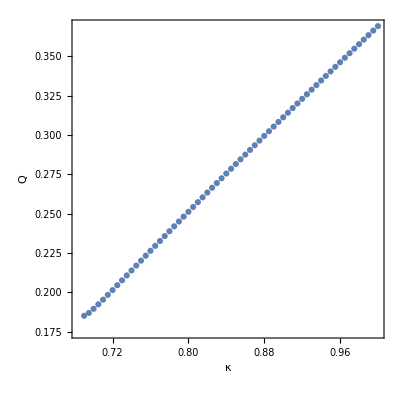
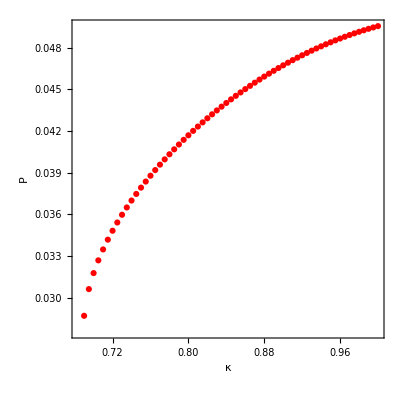
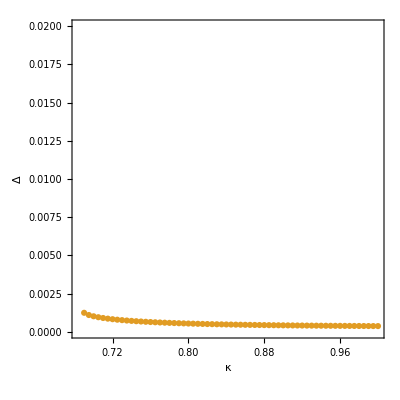

```mathematica
gap={};
sign={};
data1={};
Do[
b=data[[i]][[2]];
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];
AppendTo[gap,{data[[i]][[1]],(√(-16 Q^2+16 (P+R)^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))))/(√2)}];
AppendTo[sign,{data[[i]][[1]],(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q}];
If[And[-8 P^2-16 P R-8 R^2+λd λp>0,(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q>0],AppendTo[data1,data[[i]]]]

,{i,1,Dimensions[data][[1]]}]
```

```mathematica
data=data1;
```

```mathematica
b
```

{0.184427,0.183149,1.4437×10^-11,0.00435899,-0.028207+0. ⅈ,-0.176058}

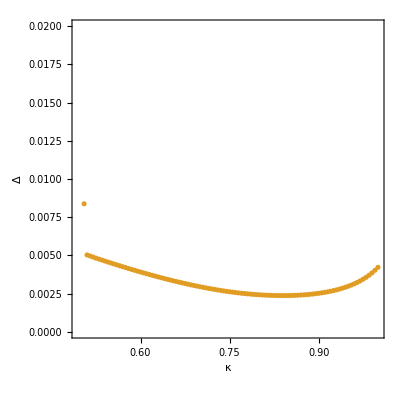

```mathematica
ListPlot[gap,Frame->True,PlotRange->{0,0.02},PlotRange->All,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"κ","Δ"},PlotStyle->ColorData[97,"ColorList"][[2]]]
```

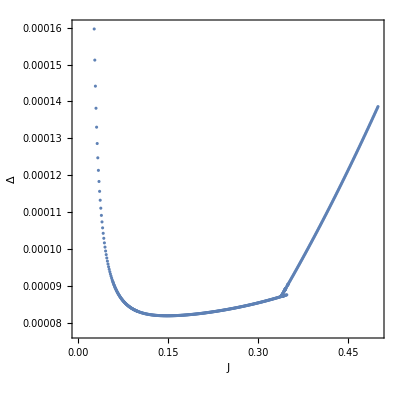
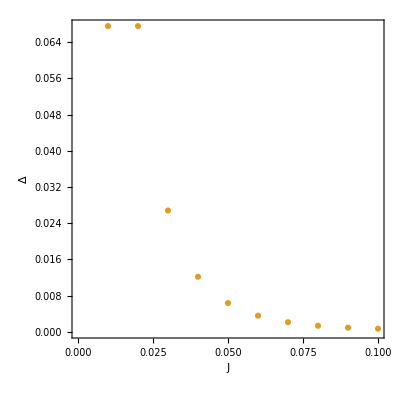
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,PlotRange->{0.00008,0.001}]
```

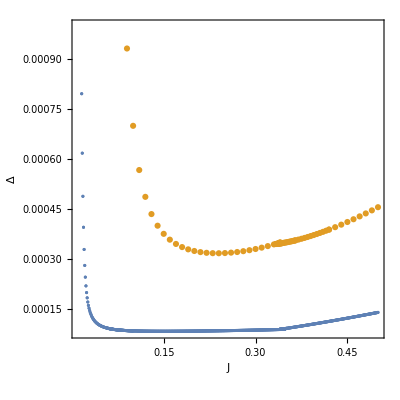

#### new data

sweep over J for T=0.02  Lx=Ly=20

```mathematica
data
```

{{2.,{2.18985,2.15103,0.756458,0.0152312,-0.143184+0. ⅈ,-2.16088}},{1.99,{2.17816,2.13977,0.752761,0.0146534,-0.140123+0. ⅈ,-2.14966}},{1.98,{2.16659,2.12857,0.74905,0.0141477,-0.137376+0. ⅈ,-2.13849}},{1.97,{2.15511,2.11741,0.74533,0.0136938,-0.134854+0. ⅈ,-2.12734}},{1.96,{2.14369,2.10627,0.741603,0.0132794,-0.132504+0. ⅈ,-2.11623}},{1.95,{2.13233,2.09516,0.737871,0.0128965,-0.130292+0. ⅈ,-2.10513}},{1.94,{2.12101,2.08406,0.734133,0.0125395,-0.128193+0. ⅈ,-2.09405}},{1.93,{2.10973,2.07299,0.730392,0.0122044,-0.126191+0. ⅈ,-2.08299}},{1.92,{2.09847,2.06192,0.726647,0.0118879,-0.12427+0. ⅈ,-2.07193}},{1.91,{2.08725,2.05087,0.7229,0.0115878,-0.122422+0. ⅈ,-2.0609}},{1.9,{2.07604,2.03984,0.71915,0.0113021,-0.120637+0. ⅈ,-2.04987}},{1.89,{2.06486,2.02881,0.715397,0.0110291,-0.118909+0. ⅈ,-2.03885}},{1.88,{2.0537,2.01779,0.711643,0.0107677,-0.117232+0. ⅈ,-2.02784}},{1.87,{2.04255,2.00678,0.707887,0.0105167,-0.115601+0. ⅈ,-2.01683}},{1.86,{2.03142,1.99577,0.704129,0.0102752,-0.114013+0. ⅈ,-2.00584}},{1.85,{2.0203,1.98478,0.70037,0.0100424,-0.112463+0. ⅈ,-1.99485}},{1.84,{2.00919,1.97379,0.696609,0.00981764,-0.11095+0. ⅈ,-1.98386}},{1.83,{1.9981,1.96281,0.692847,0.00960033,-0.10947+0. ⅈ,-1.97289}},{1.82,{1.98702,1.95183,0.689084,0.00938993,-0.108021+0. ⅈ,-1.96191}},{1.81,{1.97595,1.94086,0.68532,0.009186,-0.106601+0. ⅈ,-1.95095}},{1.8,{1.96488,1.92989,0.681555,0.0089881,-0.105208+0. ⅈ,-1.93998}},{1.79,{1.95383,1.91893,0.677789,0.0087959,-0.103841+0. ⅈ,-1.92903}},{1.78,{1.94279,1.90797,0.674022,0.00860904,-0.102498+0. ⅈ,-1.91807}},{1.77,{1.93175,1.89702,0.670254,0.00842723,-0.101178+0. ⅈ,-1.90713}},{1.76,{1.92072,1.88607,0.666485,0.00825022,-0.0998804+0. ⅈ,-1.89618}},{1.75,{1.9097,1.87513,0.662716,0.00807774,-0.0986031+0. ⅈ,-1.88524}},{1.74,{1.89869,1.86419,0.658946,0.00790958,-0.0973455+0. ⅈ,-1.8743}},{1.73,{1.88768,1.85325,0.655175,0.00774553,-0.0961068+0. ⅈ,-1.86337}},{1.72,{1.87667,1.84232,0.651404,0.00758546,-0.0948865+0. ⅈ,-1.85244}},{1.71,{1.86568,1.83139,0.647632,0.00742909,-0.093683+0. ⅈ,-1.84151}},{1.7,{1.85469,1.82046,0.643859,0.0072763,-0.092496+0. ⅈ,-1.83059}},{1.69,{1.8437,1.80954,0.640086,0.00712696,-0.0913249+0. ⅈ,-1.81967}},{1.68,{1.83272,1.79862,0.636312,0.00698093,-0.0901691+0. ⅈ,-1.80875}},{1.67,{1.82175,1.7877,0.632538,0.00683807,-0.0890279+0. ⅈ,-1.79784}},{1.66,{1.81078,1.77679,0.628764,0.00669826,-0.087901+0. ⅈ,-1.78693}},{1.65,{1.79981,1.76588,0.624988,0.00656141,-0.0867877+0. ⅈ,-1.77602}},{1.64,{1.78885,1.75497,0.621213,0.00642739,-0.0856877+0. ⅈ,-1.76511}},{1.63,{1.77789,1.74406,0.617437,0.00629611,-0.0846005+0. ⅈ,-1.75421}},{1.62,{1.76694,1.73316,0.613661,0.00616748,-0.0835256+0. ⅈ,-1.7433}},{1.61,{1.75599,1.72226,0.609884,0.00604142,-0.0824627+0. ⅈ,-1.7324}},{1.6,{1.74504,1.71136,0.606107,0.00591783,-0.0814115+0. ⅈ,-1.72151}},{1.59,{1.7341,1.70047,0.602329,0.00579665,-0.0803716+0. ⅈ,-1.71061}},{1.58,{1.72317,1.68957,0.598551,0.0056778,-0.0793426+0. ⅈ,-1.69972}},{1.57,{1.71223,1.67868,0.594773,0.00556121,-0.0783242+0. ⅈ,-1.68883}},{1.56,{1.7013,1.66779,0.590995,0.00544682,-0.0773163+0. ⅈ,-1.67794}},{1.55,{1.69037,1.6569,0.587216,0.00533456,-0.0763184+0. ⅈ,-1.66706}},{1.54,{1.67945,1.64602,0.583436,0.00522438,-0.0753303+0. ⅈ,-1.65617}},{1.53,{1.66853,1.63514,0.579657,0.00511621,-0.0743518+0. ⅈ,-1.64529}},{1.52,{1.65761,1.62426,0.575877,0.00501001,-0.0733825+0. ⅈ,-1.63441}},{1.51,{1.64669,1.61338,0.572097,0.00490572,-0.0724224+0. ⅈ,-1.62353}},{1.5,{1.63578,1.6025,0.568317,0.0048033,-0.0714711+0. ⅈ,-1.61266}},{1.49,{1.62487,1.59162,0.564536,0.00470269,-0.0705285+0. ⅈ,-1.60178}},{1.48,{1.61397,1.58075,0.560755,0.00460386,-0.0695943+0. ⅈ,-1.59091}},{1.47,{1.60306,1.56988,0.556974,0.00450676,-0.0686683+0. ⅈ,-1.58004}},{1.46,{1.59216,1.55901,0.553193,0.00441135,-0.0677504+0. ⅈ,-1.56917}},{1.45,{1.58126,1.54814,0.549411,0.0043176,-0.0668404+0. ⅈ,-1.5583}},{1.44,{1.57037,1.53727,0.54563,0.00422545,-0.0659381+0. ⅈ,-1.54744}},{1.43,{1.55947,1.52641,0.541848,0.00413489,-0.0650432+0. ⅈ,-1.53657}},{1.42,{1.54858,1.51555,0.538065,0.00404586,-0.0641558+0. ⅈ,-1.52571}},{1.41,{1.53769,1.50469,0.534283,0.00395835,-0.0632755+0. ⅈ,-1.51485}},{1.4,{1.5268,1.49383,0.5305,0.00387231,-0.0624023+0. ⅈ,-1.50399}},{1.39,{1.51592,1.48297,0.526717,0.00378772,-0.061536+0. ⅈ,-1.49313}},{1.38,{1.50504,1.47211,0.522934,0.00370455,-0.0606764+0. ⅈ,-1.48228}},{1.37,{1.49416,1.46125,0.519151,0.00362276,-0.0598234+0. ⅈ,-1.47142}},{1.36,{1.48328,1.4504,0.515368,0.00354233,-0.0589768+0. ⅈ,-1.46057}},{1.35,{1.4724,1.43955,0.511584,0.00346324,-0.0581366+0. ⅈ,-1.44972}},{1.34,{1.46153,1.4287,0.5078,0.00338545,-0.0573025+0. ⅈ,-1.43887}},{1.33,{1.45066,1.41785,0.504016,0.00330894,-0.0564746+0. ⅈ,-1.42802}},{1.32,{1.43979,1.407,0.500232,0.00323369,-0.0556525+0. ⅈ,-1.41717}},{1.31,{1.42892,1.39615,0.496448,0.00315968,-0.0548362+0. ⅈ,-1.40633}},{1.3,{1.41805,1.38531,0.492663,0.00308687,-0.0540256+0. ⅈ,-1.39548}},{1.29,{1.40719,1.37446,0.488879,0.00301525,-0.0532206+0. ⅈ,-1.38464}},{1.28,{1.39632,1.36362,0.485094,0.0029448,-0.0524209+0. ⅈ,-1.37379}},{1.27,{1.38546,1.35278,0.481309,0.00287549,-0.0516266+0. ⅈ,-1.36295}},{1.26,{1.3746,1.34194,0.477524,0.00280731,-0.0508375+0. ⅈ,-1.35211}},{1.25,{1.36375,1.3311,0.473739,0.00274023,-0.0500534+0. ⅈ,-1.34128}},{1.24,{1.35289,1.32026,0.469953,0.00267424,-0.0492742+0. ⅈ,-1.33044}},{1.23,{1.34204,1.30943,0.466168,0.00260931,-0.0484999+0. ⅈ,-1.3196}},{1.22,{1.33118,1.29859,0.462382,0.00254544,-0.0477302+0. ⅈ,-1.30877}},{1.21,{1.32033,1.28776,0.458596,0.00248259,-0.0469652+0. ⅈ,-1.29793}},{1.2,{1.30948,1.27692,0.454811,0.00242075,-0.0462046+0. ⅈ,-1.2871}},{1.19,{1.29863,1.26609,0.451024,0.00235991,-0.0454483+0. ⅈ,-1.27627}},{1.18,{1.28779,1.25526,0.447238,0.00230004,-0.0446963+0. ⅈ,-1.26544}},{1.17,{1.27694,1.24443,0.443452,0.00224114,-0.0439483+0. ⅈ,-1.25461}},{1.16,{1.2661,1.2336,0.439666,0.00218318,-0.0432043+0. ⅈ,-1.24378}},{1.15,{1.25526,1.22278,0.435879,0.00212615,-0.0424641+0. ⅈ,-1.23295}},{1.14,{1.24442,1.21195,0.432093,0.00207003,-0.0417276+0. ⅈ,-1.22213}},{1.13,{1.23358,1.20112,0.428306,0.00201481,-0.0409946+0. ⅈ,-1.2113}},{1.12,{1.22274,1.1903,0.424519,0.00196048,-0.0402651+0. ⅈ,-1.20048}},{1.11,{1.21191,1.17948,0.420732,0.00190701,-0.0395388+0. ⅈ,-1.18966}},{1.1,{1.20107,1.16866,0.416945,0.00185439,-0.0388157+0. ⅈ,-1.17884}},{1.09,{1.19024,1.15783,0.413158,0.00180261,-0.0380955+0. ⅈ,-1.16802}},{1.08,{1.17941,1.14701,0.409371,0.00175165,-0.0373781+0. ⅈ,-1.1572}},{1.07,{1.16857,1.1362,0.405583,0.0017015,-0.0366634+0. ⅈ,-1.14638}},{1.06,{1.15774,1.12538,0.401796,0.00165214,-0.0359511+0. ⅈ,-1.13556}},{1.05,{1.14692,1.11456,0.398008,0.00160356,-0.0352411+0. ⅈ,-1.12474}},{1.04,{1.13609,1.10374,0.394221,0.00155575,-0.0345332+0. ⅈ,-1.11393}},{1.03,{1.12526,1.09293,0.390433,0.00150869,-0.0338272+0. ⅈ,-1.10311}},{1.02,{1.11444,1.08212,0.386645,0.00146237,-0.0331228+0. ⅈ,-1.0923}},{1.01,{1.10362,1.0713,0.382857,0.00141676,-0.0324199+0. ⅈ,-1.08148}},{1.,{1.09279,1.06049,0.379069,0.00137186,-0.0317182+0. ⅈ,-1.07067}},{0.99,{1.08197,1.04968,0.375281,0.00132766,-0.0310174+0. ⅈ,-1.05986}},{0.98,{1.07115,1.03887,0.371493,0.00128413,-0.0303173+0. ⅈ,-1.04905}},{0.97,{1.06033,1.02806,0.367705,0.00124126,-0.0296175+0. ⅈ,-1.03824}},{0.96,{1.04951,1.01725,0.363917,0.00119904,-0.0289178+0. ⅈ,-1.02743}},{0.95,{1.0387,1.00644,0.360128,0.00115745,-0.0282178+0. ⅈ,-1.01662}},{0.94,{1.02788,0.995634,0.35634,0.00111647,-0.0275172+0. ⅈ,-1.00582}},{0.93,{1.01707,0.984828,0.352551,0.00107609,-0.0268154+0. ⅈ,-0.995012}},{0.92,{1.00625,0.974023,0.348763,0.00103628,-0.0261121+0. ⅈ,-0.984206}},{0.91,{0.995441,0.963218,0.344974,0.000997033,-0.0254067+0. ⅈ,-0.973402}},{0.9,{0.984629,0.952414,0.341185,0.000958322,-0.0246988+0. ⅈ,-0.962598}},{0.89,{0.973819,0.941611,0.337397,0.000920129,-0.0239876+0. ⅈ,-0.951795}},{0.88,{0.963009,0.930809,0.333608,0.000882429,-0.0232726+0. ⅈ,-0.940993}},{0.87,{0.9522,0.920007,0.329819,0.000845198,-0.022553+0. ⅈ,-0.930191}},{0.86,{0.941392,0.909206,0.32603,0.000808408,-0.0218279+0. ⅈ,-0.919391}},{0.85,{0.930585,0.898406,0.322241,0.000772031,-0.0210963+0. ⅈ,-0.908591}},{0.84,{0.919779,0.887607,0.318452,0.000736033,-0.0203571+0. ⅈ,-0.897791}},{0.83,{0.908974,0.876808,0.314663,0.000700376,-0.019609+0. ⅈ,-0.886993}},{0.82,{0.89817,0.86601,0.310874,0.000665019,-0.0188506+0. ⅈ,-0.876195}},{0.81,{0.887366,0.855213,0.307085,0.000629912,-0.0180801+0. ⅈ,-0.865398}},{0.8,{0.876563,0.844416,0.303296,0.000594999,-0.0172954+0. ⅈ,-0.854601}},{0.79,{0.865762,0.83362,0.299506,0.000560212,-0.016494+0. ⅈ,-0.843805}},{0.78,{0.854961,0.822825,0.295717,0.000525468,-0.0156727+0. ⅈ,-0.83301}},{0.77,{0.84416,0.81203,0.291928,0.000490667,-0.0148279+0. ⅈ,-0.822216}},{0.76,{0.833361,0.801236,0.288138,0.000455681,-0.0139546+0. ⅈ,-0.811422}},{0.75,{0.822562,0.790443,0.284349,0.000420342,-0.0130467+0. ⅈ,-0.800628}},{0.74,{0.811764,0.77965,0.28056,0.000384429,-0.0120956+0. ⅈ,-0.789836}},{0.73,{0.800967,0.768858,0.27677,0.000347628,-0.0110896+0. ⅈ,-0.779043}},{0.72,{0.79017,0.758066,0.272981,0.00030948,-0.0100116+0. ⅈ,-0.768252}},{0.71,{0.779374,0.747275,0.269191,0.000269256,-0.00883462+0. ⅈ,-0.757461}},{0.7,{0.768579,0.736484,0.265402,0.000225686,-0.00751212+0. ⅈ,-0.74667}},{0.69,{0.757785,0.725694,0.261612,0.000176186,-0.00595048+0. ⅈ,-0.73588}},{0.68,{0.746992,0.714906,0.257823,0.000114058,-0.00390947+0. ⅈ,-0.725092}},{0.67,{0.736212,0.70413,0.254033,4.70756×10^-7,-0.0000163787+0. ⅈ,-0.714316}},{0.66,{0.725473,0.693397,0.25024,-3.58615×10^-8,1.26668×10^-6+0. ⅈ,-0.703581}},{0.65,{0.714734,0.682663,0.246447,2.37735×10^-10,-8.95266×10^-9+0. ⅈ,-0.692846}},{0.64,{0.703996,0.67193,0.242654,3.332×10^-10,-1.21362×10^-8+0. ⅈ,-0.682111}},{0.63,{0.693257,0.661197,0.238862,2.89785×10^-10,-1.07241×10^-8+0. ⅈ,-0.671376}},{0.62,{0.682518,0.650464,0.235069,2.60588×10^-10,-9.79896×10^-9+0. ⅈ,-0.660642}},{0.61,{0.671779,0.639731,0.231276,2.38798×10^-10,-9.12663×10^-9+0. ⅈ,-0.649908}},{0.6,{0.66104,0.628999,0.227483,2.21477×10^-10,-8.60639×10^-9+0. ⅈ,-0.639173}},{0.59,{0.650301,0.618267,0.22369,2.07295×10^-10,-8.19196×10^-9+0. ⅈ,-0.62844}},{0.58,{0.639562,0.607536,0.219896,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.617706}},{0.57,{0.628823,0.596805,0.216103,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.606973}},{0.56,{0.618084,0.586074,0.21231,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.59624}},{0.55,{0.607344,0.575344,0.208516,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.585507}},{0.54,{0.596605,0.564614,0.204723,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.574774}},{0.53,{0.585865,0.553885,0.200929,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.564042}},{0.52,{0.575125,0.543156,0.197135,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.55331}},{0.51,{0.564385,0.532428,0.193342,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.542578}},{0.5,{0.553645,0.5217,0.189548,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.531847}},{0.49,{0.542904,0.510973,0.185753,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.521116}},{0.48,{0.532163,0.500246,0.181959,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.510385}},{0.47,{0.521421,0.48952,0.178165,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.499654}},{0.46,{0.510679,0.478795,0.17437,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.488924}},{0.45,{0.499937,0.468071,0.170575,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.478195}},{0.44,{0.489194,0.457347,0.16678,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.467466}},{0.43,{0.47845,0.446624,0.162985,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.456737}},{0.42,{0.467706,0.435902,0.159189,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.446009}},{0.41,{0.456961,0.425181,0.155393,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.435281}},{0.4,{0.446215,0.414462,0.151597,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.424553}},{0.39,{0.435467,0.403743,0.1478,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.413827}},{0.38,{0.424719,0.393026,0.144003,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.4031}},{0.37,{0.413969,0.38231,0.140206,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.392374}},{0.36,{0.403218,0.371595,0.136408,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.381649}},{0.35,{0.392464,0.360882,0.13261,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.370925}},{0.34,{0.381709,0.350171,0.12881,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.360201}},{0.33,{0.37095,0.339461,0.125011,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.349477}},{0.32,{0.36019,0.328754,0.12121,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.338754}},{0.31,{0.349425,0.318048,0.117408,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.328032}},{0.3,{0.338657,0.307345,0.113606,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.31731}},{0.3,{0.338657,0.307345,0.113606,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.31731}},{0.29,{0.327884,0.296645,0.109802,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.306589}},{0.28,{0.317106,0.285947,0.105996,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.295868}},{0.27,{0.306321,0.275253,0.102189,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.285147}},{0.26,{0.295528,0.264562,0.0983799,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.274427}},{0.25,{0.284726,0.253874,0.0945684,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.263706}},{0.24,{0.273913,0.24319,0.090754,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.252984}},{0.23,{0.263086,0.23251,0.0869361,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.242262}},{0.22,{0.252242,0.221834,0.083114,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.231537}},{0.21,{0.241378,0.211163,0.0792867,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.22081}},{0.2,{0.230487,0.200496,0.0754529,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.210078}},{0.19,{0.219564,0.189834,0.0716109,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.199339}},{0.18,{0.2086,0.179175,0.0677586,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.188591}},{0.17,{0.197582,0.16852,0.0638929,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.17783}},{0.16,{0.186496,0.157868,0.06001,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.167049}},{0.15,{0.175319,0.147216,0.0561044,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.156242}},{0.14,{0.164025,0.136563,0.0521687,7.64173×10^-13,-3.01152×10^-11+0. ⅈ,-0.145398}},{0.13,{0.152575,0.125904,0.0481927,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.134502}},{0.12,{0.140916,0.115236,0.0441621,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.123535}},{0.11,{0.128979,0.104552,0.040057,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.11247}},{0.1,{0.116673,0.0938467,0.0358487,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.101272}},{0.09,{0.103876,0.0831125,0.0314952,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.0898956}},{0.08,{0.0904398,0.0723448,0.0269326,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.0782851}},{0.07,{0.0761927,0.0615442,0.0220546,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.0663785}},{0.06,{0.0609599,0.0507212,0.0166499,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.0541176}},{0.05,{0.0445889,0.0398913,0.0100765,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.0414556}},{0.04,{0.0321881,0.0321884,6.82689×10^-7,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.0321883}},{0.03,{0.0321881,0.0321884,6.82689×10^-7,1.50425×10^-13,-2.7123×10^-11+0. ⅈ,-0.0321883}}}

```mathematica
dataF
```

{{2.,2.33578},{1.99,2.32434},{1.98,2.31289},{1.97,2.30145},{1.96,2.29},{1.95,2.27855},{1.94,2.2671},{1.93,2.25564},{1.92,2.24419},{1.91,2.23273},{1.9,2.22127},{1.89,2.20981},{1.88,2.19836},{1.87,2.18689},{1.86,2.17543},{1.85,2.16397},{1.84,2.15251},{1.83,2.14104},{1.82,2.12958},{1.81,2.11811},{1.8,2.10664},{1.79,2.09517},{1.78,2.0837},{1.77,2.07224},{1.76,2.06077},{1.75,2.04929},{1.74,2.03782},{1.73,2.02635},{1.72,2.01488},{1.71,2.00341},{1.7,1.99193},{1.69,1.98046},{1.68,1.96898},{1.67,1.95751},{1.66,1.94603},{1.65,1.93455},{1.64,1.92308},{1.63,1.9116},{1.62,1.90012},{1.61,1.88864},{1.6,1.87716},{1.59,1.86569},{1.58,1.85421},{1.57,1.84273},{1.56,1.83125},{1.55,1.81976},{1.54,1.80828},{1.53,1.7968},{1.52,1.78532},{1.51,1.77384},{1.5,1.76235},{1.49,1.75087},{1.48,1.73939},{1.47,1.7279},{1.46,1.71642},{1.45,1.70493},{1.44,1.69345},{1.43,1.68196},{1.42,1.67048},{1.41,1.65899},{1.4,1.64751},{1.39,1.63602},{1.38,1.62453},{1.37,1.61305},{1.36,1.60156},{1.35,1.59007},{1.34,1.57858},{1.33,1.56709},{1.32,1.55561},{1.31,1.54412},{1.3,1.53263},{1.29,1.52114},{1.28,1.50965},{1.27,1.49816},{1.26,1.48667},{1.25,1.47518},{1.24,1.46369},{1.23,1.4522},{1.22,1.44071},{1.21,1.42922},{1.2,1.41772},{1.19,1.40623},{1.18,1.39474},{1.17,1.38325},{1.16,1.37176},{1.15,1.36026},{1.14,1.34877},{1.13,1.33728},{1.12,1.32579},{1.11,1.31429},{1.1,1.3028},{1.09,1.29131},{1.08,1.27981},{1.07,1.26832},{1.06,1.25682},{1.05,1.24533},{1.04,1.23384},{1.03,1.22234},{1.02,1.21085},{1.01,1.19935},{1.,1.18786},{0.99,1.17636},{0.98,1.16486},{0.97,1.15337},{0.96,1.14187},{0.95,1.13038},{0.94,1.11888},{0.93,1.10738},{0.92,1.09589},{0.91,1.08439},{0.9,1.07289},{0.89,1.0614},{0.88,1.0499},{0.87,1.0384},{0.86,1.0269},{0.85,1.01541},{0.84,1.00391},{0.83,0.992411},{0.82,0.980913},{0.81,0.969415},{0.8,0.957916},{0.79,0.946418},{0.78,0.934919},{0.77,0.92342},{0.76,0.911921},{0.75,0.900422},{0.74,0.888923},{0.73,0.877423},{0.72,0.865924},{0.71,0.854424},{0.7,0.842924},{0.69,0.831423},{0.68,0.819923},{0.67,0.808423},{0.66,0.796922},{0.65,0.785422},{0.64,0.773921},{0.63,0.762421},{0.62,0.750921},{0.61,0.739421},{0.6,0.727922},{0.59,0.716422},{0.58,0.704923},{0.57,0.693423},{0.56,0.681925},{0.55,0.670426},{0.54,0.658927},{0.53,0.647429},{0.52,0.635931},{0.51,0.624434},{0.5,0.612936},{0.49,0.60144},{0.48,0.589943},{0.47,0.578447},{0.46,0.566952},{0.45,0.555457},{0.44,0.543962},{0.43,0.532469},{0.42,0.520976},{0.41,0.509483},{0.4,0.497992},{0.39,0.486502},{0.38,0.475013},{0.37,0.463525},{0.36,0.452038},{0.35,0.440553},{0.34,0.429069},{0.33,0.417588},{0.32,0.406109},{0.31,0.394632},{0.3,0.383158},{0.3,0.383158},{0.29,0.371688},{0.28,0.360221},{0.27,0.348759},{0.26,0.337302},{0.25,0.325852},{0.24,0.314408},{0.23,0.302973},{0.22,0.291549},{0.21,0.280138},{0.2,0.268743},{0.19,0.257367},{0.18,0.246016},{0.17,0.234697},{0.16,0.223419},{0.15,0.212195},{0.14,0.201042},{0.13,0.189988},{0.12,0.179069},{0.11,0.16834},{0.1,0.157885},{0.09,0.14783},{0.08,0.138372},{0.07,0.129827},{0.06,0.122706},{0.05,0.117878},{0.04,0.116649},{0.03,0.116649}}

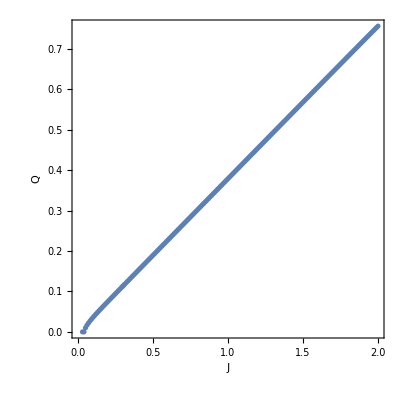
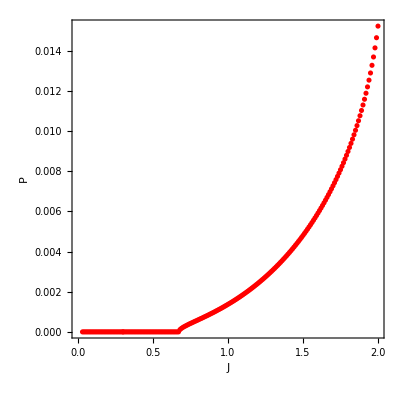
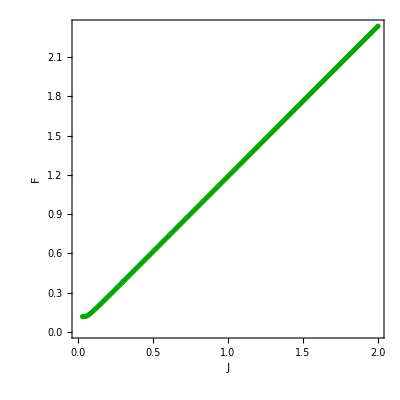
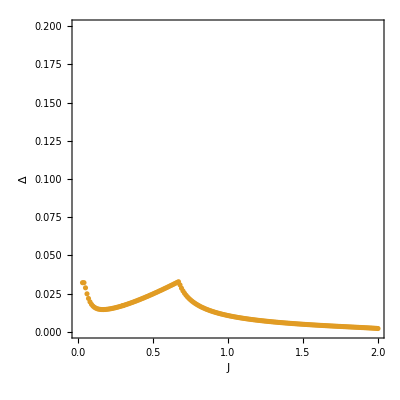

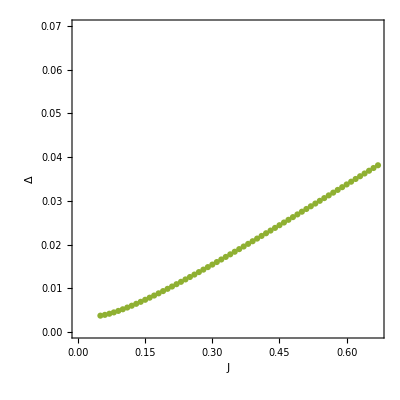
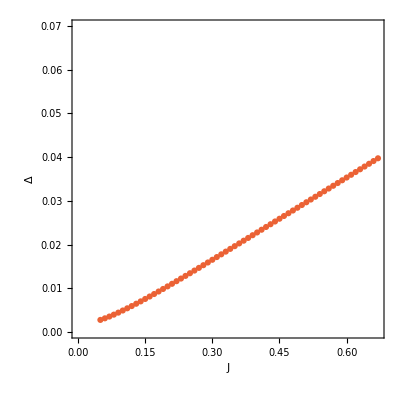
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

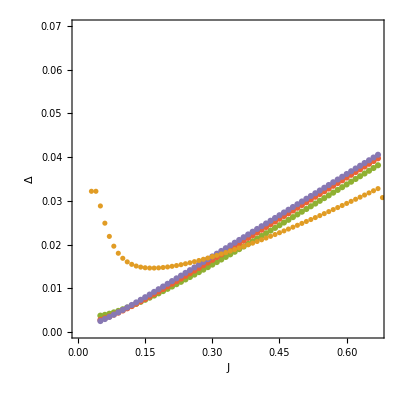

#### broyden method

```mathematica
Clear[kx,ky]
T=0.02;
Lx=Ly=20;

nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=0.1;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];



evaluate:={
ne=0.75;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];


order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-1,nd+ndf-1,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne};

};
```

```mathematica
b={0.4659908719598483,0.4758609778225628,0.,0.07871288628056738,-0.24512391401207734,-0.5331759767318635};
evaluate;
Jac=ConstantArray[0.,{6,6}];

eqn0=Chop[eqn];
δ=10^-9;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,6}];
evaluate;
While[Abs[eqn.eqn]>10^-11,
eqn0=Chop[eqn];
Print["convergence = ",Abs[eqn.eqn]];
b+=-Inverse[Transpose[Jac]].eqn0;
Jac=Jac+KroneckerProduct[eqn0,b]/(b.b);

evaluate;
]
```

convergence = 0.00430258

convergence = 4.28238

convergence = 0.44623

convergence = 0.280727

convergence = 4.00264

convergence = 6.5596

convergence = 6.82248

convergence = 19.1711

convergence = 30.5559

convergence = 32.5589

General::munfl: Exp[-771.337] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

convergence = 35.6735

convergence = 46.6809

convergence = 59.4577

convergence = 74.3005

convergence = 93.0544

convergence = 116.707

convergence = 146.544

convergence = 184.242

convergence = 231.996

convergence = 292.706

convergence = 370.229

convergence = 469.739

convergence = 598.259

$Aborted

```mathematica
b
```

{0.469061,0.478475,0.,0.0774119,-0.244829,-0.535247}

```mathematica
Plot3D[{-λp,λp,-(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky])))))/(√2),(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky])))))/(√2),-(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]+√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky])))))/(√2),(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]+√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky])))))/(√2)},{kx,-π,π},{ky,-π,π},PlotRange->{-0.1,0.1},MaxRecursion->10,Mesh->Full,PerformanceGoal->"Quality"]
```

-Graphics3D-

### plot

```mathematica
b
```

{0.560282,0.529932,0.190917,0.00223698,-0.0264366+0. ⅈ,-0.536699}

```mathematica
b={0.3746523794496318,0.36297001793905864,0.10265702488016344,0.006819228725341083,-0.08323075574669306+0. ⅈ,-0.3626352627163154};
b={0.5602822645008589,0.5299322486212799,0.19091748514879858,0.0022369803655073956,-0.026436609101728657+0. ⅈ,-0.536699470446289};
Clear[kx,ky]
T=0.02;
check={};
Lx=Ly=30;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=0.5;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
eplot1f={};
eplot2f={};
eplot3f={};
eplot1b={};
eplot2b={};
eplot3b={};
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
AppendTo[eplot1b,{kx,ky,energy[[1]]}];
AppendTo[eplot2b,{kx,ky,energy[[2]]}];

AppendTo[eplot3b,{kx,ky,energy[[3]]}];




order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];

;
energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

AppendTo[check,Total[Abs[Chop[(Tm.τ.ConjugateTranspose[Tm])]-τ],2]];


a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];


(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};



{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

AppendTo[eplot1f,{kx,ky,energy[[1]]}];
AppendTo[eplot2f,{kx,ky,energy[[2]]}];

AppendTo[eplot3f,{kx,ky,energy[[3]]}];
Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne}
Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q];
Print["nx = ",npx+npxf, " nd= ", nd+ndf, " q= ", q1," p1= ", Chop[p1], " r =  ",Chop[r1], " ne = ", (ndf+2npxf)/3]
 
ListPlot3D[{eplot1f,eplot2f,eplot3f},PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]

ListPlot3D[{eplot1b,eplot2b,eplot3b},PlotRange->{0,0.25},InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

{1.42692×10^-6+1.90854×10^-21 ⅈ,2.70446×10^-6+3.27713×10^-21 ⅈ,-4.84866×10^-7-9.38594×10^-22 ⅈ,-7.91079×10^-8-6.20621×10^-20 ⅈ,-2.81367×10^-10-1.05131×10^-18 ⅈ,3.75002×10^-10+0. ⅈ}

convergence = 9.59154×10^-12 sign = 0.000206383+0. ⅈ

nx = 1.+1.90854×10^-21 ⅈ nd= 1.+3.27713×10^-21 ⅈ q= 0.190918+9.38594×10^-22 ⅈ p1= 0.00223706 r =  -0.0264366 ne = 0.5+0. ⅈ

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[{-λp,λp,-1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),-1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]+√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]+√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky])))))},{kx,-π,π},{ky,-π,π},PlotRange->{-1.2,1.2},MaxRecursion->10,Mesh->Full,PerformanceGoal->"Quality",PlotRange->{0,0.25},LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

-Graphics3D-

```mathematica
Plot3D[{-1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky])))))},{kx,-0.4,0.4},{ky,-0.4,0.4},PlotRange->{-0.005,0.05},MaxRecursion->10,Mesh->Full,PerformanceGoal->"Quality",PlotRange->{0,0.45},LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
Print["gap = ",(√(-16 Q^2+16 (P+R)^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))))/(√2)]
```

-Graphics3D-

gap = 0.00436279+0. ⅈ

```mathematica
Solve[-16 Q^2+16 (P+R)^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))==0,Q]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Q→-(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)},{Q→(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)}}

### self-consistent solution

```mathematica
Clear[kx,ky]
T=0.02;
Lx=Ly=20;
s=0.88;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=0.5;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];



evaluate:={
ne=0.5;
λd=b1[[1]];
λp=b1[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b1[[3]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];


order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,(ndf+2npxf)/3-ne};

};
```

```mathematica
b={0.5795700783152019,0.4885136579871357,0.09439743565729297,0.07574557707083249,-0.23812688920331523+0. ⅈ,-0.4813420906912353};
b1={b[[1]],b[[2]],b[[6]]};
evaluate;

While[Abs[eqn.eqn]>10^-8,
Jac=ConstantArray[0.,{3,3}];


Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q];
eqn0=Chop[eqn];

δ=10^-8;

Do[b1[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b1[[i]]-=δ;
,{i,1,3}];
scale=2.;

b1+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b1[[1]];
λp=b1[[2]];

While[(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q<0,
b1-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*2;
b1+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b1[[1]];
λp=b1[[2]];

];

evaluate;
]
b={b1[[1]],b1[[2]],((1-α)b[[3]]+α Chop[q1]),((1-α)b[[4]]+α Chop[p1]),((1-α)b[[5]]+α Chop[r1]),b1[[3]]};
```

convergence = 0.125068 sign = 0.0005936+0. ⅈ

convergence = 0.0707926 sign = 0.000267383+0. ⅈ

convergence = 0.749089 sign = 0.0000297277+0. ⅈ

convergence = 0.294839 sign = 0.0000399051+0. ⅈ

convergence = 0.110295 sign = 0.0000514013+0. ⅈ

convergence = 0.038673 sign = 0.0000630542+0. ⅈ

convergence = 0.0125788 sign = 0.0000734232+0. ⅈ

convergence = 0.00378971 sign = 0.0000814299+0. ⅈ

convergence = 0.00106803 sign = 0.0000868287+0. ⅈ

convergence = 0.00028649 sign = 0.0000900844+0. ⅈ

convergence = 0.0000744499 sign = 0.0000918984+0. ⅈ

convergence = 0.0000189955 sign = 0.0000928604+0. ⅈ

convergence = 4.79871×10^-6 sign = 0.0000933565+0. ⅈ

convergence = 1.206×10^-6 sign = 0.0000936085+0. ⅈ

convergence = 3.02288×10^-7 sign = 0.0000937355+0. ⅈ

convergence = 7.56682×10^-8 sign = 0.0000937992+0. ⅈ

convergence = 1.89284×10^-8 sign = 0.0000938311+0. ⅈ

```mathematica
b
```

{0.578823,0.487835,0.0943974,0.0757456,-0.238127+0. ⅈ,-0.480662}

```mathematica
q1
```

0.0939685+1.98402×10^-19 ⅈ

```mathematica
p1
```

0.0146318-1.603×10^-20 ⅈ

```mathematica
r1
```

-0.212164-1.52887×10^-18 ⅈ

```mathematica
b
```

{0.662498,0.536578,0.146,0.081,-0.233+0. ⅈ,-0.529734}

```mathematica
b={0.32612272448158536,0.19504413907959714,0.005861489625625054,0.1283196820616391,-0.24553722199662817,-0.18586462832636638};

α=1;
b1={b[[1]],b[[2]],b[[6]]};
evaluate;


Jac=ConstantArray[0.,{3,3}];


Print["convergence = ",Abs[eqn.eqn]];
eqn0=Chop[eqn];

δ=10^-6;

Do[b1[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b1[[i]]-=δ;
,{i,1,3}];
b1+=-Inverse[Transpose[Jac]].eqn0;
```

convergence = 11649.4

```mathematica
b1
```

{0.326123,0.195044,-0.185865}

```mathematica
Inverse[Transpose[Jac]]//MatrixForm
```

(-0.00213993 | 0.00178898 | 0.00312817
0.00118139 | -0.000987698 | -0.00172697
-0.00114974 | 0.000961242 | -0.212405)

```mathematica
eqn
```

{8.56007×10^-8+0. ⅈ,1.17595×10^-7+0. ⅈ,5.01821×10^-14+0. ⅈ}

### converging with constraint f+b=s<1

```mathematica
Clear[kx,ky]
T=0.02;
Lx=Ly=20;
s=0.5;

nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=0.8;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];



evaluate:={
ne=0.75;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];


order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne};

};
```

```mathematica
b={0.9,0.9,0.06,0.07,-0.24891277252229935,-0.4848284849422044};
evaluate;

While[Abs[eqn.eqn]>10^-11,
Jac=ConstantArray[0.,{6,6}];


Print["convergence = ",Abs[eqn.eqn]];
eqn0=Chop[eqn];

δ=10^-9;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,6}];
b+=-Inverse[Transpose[Jac]].eqn0;
evaluate;
]
```

convergence = 1.11624

General::munfl: Exp[-1.48328×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

convergence = 3.61494

Inverse::sing: Matrix {{6.66134×10^-6,0.0460352,0.0570259,-0.0221059,-0.0221059,0.},{0.,0.,0.,0.,0.,0.},{0.000025091,0.000119682,1.00027,-5.44009×10^-6,-5.44009×10^-6,0.},{-9.92723×10^-10,-4.81166×10^-8,-1.11683×10^-7,0.999986,-0.0000141541,0.},{0.,0.,0.,0.0000177636,1.,0.},{0.,0.,0.,0.,0.,0.}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

$Aborted

```mathematica
eqn
```

{3.44159×10^-9+0. ⅈ,7.01849×10^-9+0. ⅈ,0.+0. ⅈ,-1.46368×10^-9-4.13223×10^-34 ⅈ,-8.12822×10^-13+2.90024×10^-18 ⅈ,-9.36816×10^-9+0. ⅈ}

```mathematica
b
```

{0.464705,0.474402,0.,0.0782462,-0.245021,-0.531525}

```mathematica
p1
```

0.0588727-6.01853×10^-35 ⅈ

```mathematica
b={0.45,0.44,0.03,0.10453707475653479,-0.24891277252229935,-0.4848284849422044};
evaluate;
Plot3D[{-λp,λp,-1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),-1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]+√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]+√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky])))))},{kx,-π,π},{ky,-π,π},PlotRange->{-0.1,0.1},MaxRecursion->10,Mesh->Full,PerformanceGoal->"Quality"]
```

-Graphics3D-

### zero temperature

#### plots

```mathematica
b={0.7,0.3,0.06,0.05,-0.2,-0.7};
Clear[kx,ky]

check={};
Lx=Ly=20;
s=0.7;
T=0.02;

nf[ω_]:=1/(+1+Exp[ω/T]);

J=0.5;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
eplot1f={};
eplot2f={};
eplot3f={};
eplot1b={};
eplot2b={};
eplot3b={};
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
AppendTo[eplot1b,{kx,ky,energy[[1]]}];
AppendTo[eplot2b,{kx,ky,energy[[2]]}];

AppendTo[eplot3b,{kx,ky,energy[[3]]}];




order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];

;
energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

AppendTo[check,Total[Abs[Chop[(Tm.τ.ConjugateTranspose[Tm])]-τ],2]];


a=1;
nd+=1/(Lx Ly)Sum[ (1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[(+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1),{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1),{b,1,3}];


(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};



{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

AppendTo[eplot1f,{kx,ky,energy[[1]]}];
AppendTo[eplot2f,{kx,ky,energy[[2]]}];

AppendTo[eplot3f,{kx,ky,energy[[3]]}];
Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne}
Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q];
Print["nx = ",npx+npxf, " nd= ", nd+ndf, " q= ", q1," p1= ", Chop[p1], " r =  ",Chop[r1], " ne = ", (ndf+2npxf)/3]
 
ListPlot3D[{eplot1f,eplot2f,eplot3f},PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]

ListPlot3D[{eplot1b,eplot2b,eplot3b},PlotRange->{0,0.25},InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

{0.422729+0. ⅈ,-0.318832+0. ⅈ,0.0190828-7.80626×10^-20 ⅈ,0.046098-2.60209×10^-20 ⅈ,-0.108893-1.91985×10^-18 ⅈ,0.331236+0. ⅈ}

convergence = 0.404417 sign = 0.00123724

nx = 1.12273+0. ⅈ nd= 0.381168+0. ⅈ q= 0.0409172+7.80626×10^-20 ⅈ p1= 0.003902 r =  -0.0911067 ne = 0.831236+0. ⅈ

-Graphics3D-

-Graphics3D-

```mathematica
p1
```

-4.97818×10^-19-2.67987×10^-21 ⅈ

```mathematica
Plot3D[{-1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky]))))),1/(√2)(√(-8 Q^2+8 (P+R)^2+λd^2+λp^2-4 Q^2 Cos[kx]+4 (P+R)^2 Cos[kx]-4 Q^2 Cos[ky]+4 (P+R)^2 Cos[ky]-√(-((16 Q^2-λd^2-2 λd λp-λp^2+8 Q^2 Cos[kx]+8 Q^2 Cos[ky]) (16 (P+R)^2+λd^2-2 λd λp+λp^2+8 (P+R)^2 Cos[kx]+8 (P+R)^2 Cos[ky])))))},{kx,-0.4,0.4},{ky,-0.4,0.4},PlotRange->{-0.05,0.05},MaxRecursion->10,Mesh->Full,PerformanceGoal->"Quality",PlotRange->{0,0.25},LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
Print["gap = ",(√(-16 Q^2+16 (P+R)^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))))/(√2)]
```

-Graphics3D-

gap = 0.00127746

```mathematica
(√(-16 Q^2+16 (P+R)^2+λd^2+λp^2-√(-((32 Q^2-λd^2-2 λd λp-λp^2) (32 (P+R)^2+λd^2-2 λd λp+λp^2)))))/(√2)/.R->0//FullSimplify
```

(√(16 P^2-16 Q^2+λd^2+λp^2-√((32 P^2+(λd-λp)^2) (-32 Q^2+(λd+λp)^2))))/(√2)

#### Qx=-Qy

```mathematica
b={0.6,0.6,0.04,0.0005,-0.2,-0.7};
Clear[kx,ky]

check={};
Lx=Ly=20;
s=0.7;
T=0.001;

nf[ω_]:=1/(+1+Exp[ω/T]);

J=0.5;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
eplot1f={};
eplot2f={};
eplot3f={};
eplot1b={};
eplot2b={};
eplot3b={};
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
AppendTo[eplot1b,{kx,ky,energy[[1]]}];
AppendTo[eplot2b,{kx,ky,energy[[2]]}];

AppendTo[eplot3b,{kx,ky,energy[[3]]}];




order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];

;
energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

AppendTo[check,Total[Abs[Chop[(Tm.τ.ConjugateTranspose[Tm])]-τ],2]];


a=1;
nd+=1/(Lx Ly)Sum[ (1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[(+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1),{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1),{b,1,3}];


(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};



{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

AppendTo[eplot1f,{kx,ky,energy[[1]]}];
AppendTo[eplot2f,{kx,ky,energy[[2]]}];

AppendTo[eplot3f,{kx,ky,energy[[3]]}];
Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne}
Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q];
Print["nx = ",npx+npxf, " nd= ", nd+ndf, " q= ", q1," p1= ", Chop[p1], " r =  ",Chop[r1], " ne = ", (ndf+2npxf)/3]
 
ListPlot3D[{eplot1f,eplot2f,eplot3f},PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]

ListPlot3D[{eplot1b,eplot2b,eplot3b},PlotRange->{0,0.25},InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

{0.410136+0. ⅈ,0.414775+0. ⅈ,0.0199294+1.02014×10^-33 ⅈ,-0.0000588286-7.01535×10^-35 ⅈ,-0.2+1.20371×10^-33 ⅈ,0.6025+0. ⅈ}

convergence = 0.743653 sign = 0.0321093

nx = 1.11014+0. ⅈ nd= 1.11477+0. ⅈ q= 0.0200706-1.02014×10^-33 ⅈ p1= 0.000558829 r =  0 ne = 1.1025+0. ⅈ

-Graphics3D-

-Graphics3D-

```mathematica
10
```

### Qx=-Qy solutions

#### plot

```mathematica
{2.2262383563969825,2.1206861114365663,0.7524092848829049,0.05750174492231323,-0.20968226310215196+0. ⅈ,-2.1249921472890123}
```

```mathematica
b={1.6621576602475778,1.6480484545937144,0.5360465877463277,0.03527088853799125,-0.19840974873588602+0. ⅈ,-1.6917395631345313};
Clear[kx,ky]
T=0.02;
check={};
Lx=Ly=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);


nf[ω_]:=1/(+1+Exp[ω/T]);

J=2;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.7;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;


ndcheck=0;
nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
q3=0;
q2=0;
q4=0;
p1=0;
p2=0;
eplot1f={};
eplot2f={};
eplot3f={};
eplot1b={};
eplot2b={};
eplot3b={};
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];





order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];

;
energy=energy[[normal]];
vec=vec[[normal]];

AppendTo[eplot1b,{kx,ky,energy[[1]]}];
AppendTo[eplot2b,{kx,ky,energy[[2]]}];

AppendTo[eplot3b,{kx,ky,energy[[3]]}];

Tm=Transpose[vec];

AppendTo[check,Total[Abs[Chop[(Tm.τ.ConjugateTranspose[Tm])]-τ],2]];


a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

;
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];
(*

Print[J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}]];

Print[J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ ky/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ ky/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ ky/2]) nb[energy[[b]]],{b,1,3}]];

;*);
q3+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

q2+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[3+3,b]]]Exp[-ⅈ ky/2]-Tm[[3,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[3+3,b+3]]]Exp[-ⅈ ky/2]-Tm[[3,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ ky/2]) nb[energy[[b]]],{b,1,3}];

q4+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[3+3,b]]]Exp[ⅈ ky/2]-Tm[[3,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[-ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[3+3,b+3]]]Exp[ⅈ ky/2]-Tm[[3,b]]Conjugate[Tm[[1+3,b]]]Exp[-ⅈ ky/2]) nb[energy[[b]]],{b,1,3}];



p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p2+=J/2 1/(Lx Ly)Sum[(Tm[[3,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ ky/2]+Tm[[1+3,b]]Conjugate[Tm[[3+3,b]]]Exp[-ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[3,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ ky/2]+Tm[[1+3,b+3]]Conjugate[Tm[[3+3,b+3]]]Exp[-ⅈ ky/2]) nb[energy[[b]]],{b,1,3}];


(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};
(*the correct one*)
H={{λ1+μ,(2Conjugate[P1])/J Exp[ⅈ kx/2]+(2Conjugate[P3])/J Exp[-ⅈ kx/2],(2Conjugate[P2])/J Exp[ⅈ ky/2]+(2Conjugate[P4])/J Exp[-ⅈ ky/2]},{(2P1)/J Exp[-ⅈ kx/2]+(2P3)/J Exp[ⅈ kx/2],λ2+μ,0},{(2P2)/J Exp[-ⅈ ky/2]+(2P4)/J Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

AppendTo[eplot1f,{kx,ky,energy[[1]]}];
AppendTo[eplot2f,{kx,ky,energy[[2]]}];

AppendTo[eplot3f,{kx,ky,energy[[3]]}];
Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];




,{kx,-π,π-2 π/Lx,2 π/Lx},{ky,-π,π-2 π/Ly,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne}
Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q];
Print["nx = ",npx+npxf, " nd= ", nd+ndf, " q= ", q1," p1= ", Chop[p1], " r =  ",Chop[r1], " ne = ", (ndf+2npxf)/3]
 
ListPlot3D[{eplot1f,eplot2f,eplot3f},PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]

ListPlot3D[{eplot1b,eplot2b,eplot3b},PlotRange->{0,0.5},InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

{-2.81637×10^-8+8.00152×10^-31 ⅈ,-6.08245×10^-8+7.28385×10^-31 ⅈ,-5.32321×10^-7-3.46945×10^-19 ⅈ,-1.82586×10^-7+1.56125×10^-19 ⅈ,-7.00855×10^-7+8.94467×10^-19 ⅈ,-5.82545×10^-7+0. ⅈ}

convergence = 1.15175×10^-12 sign = 0.0259145+0. ⅈ

nx = 1.+8.00152×10^-31 ⅈ nd= 1.+7.28385×10^-31 ⅈ q= 0.536047+3.46945×10^-19 ⅈ p1= 0.0352711 r =  -0.198409 ne = 0.699999+0. ⅈ

-Graphics3D-

-Graphics3D-

```mathematica
ndf
```

0.255145+0. ⅈ

```mathematica
nd
```

0.74486-1.22835×10^-24 ⅈ

```mathematica
npx
```

0.377574-7.94515×10^-25 ⅈ

```mathematica
npxf
```

0.622428+0. ⅈ

```mathematica
nb[-λd]
```

-1.23478

```mathematica
ListPlot3D[{eplot1b,eplot2b,eplot3b},PlotRange->{0,4.5},InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

-Graphics3D-

```mathematica
ListPlot3D[{eplot1f,eplot2f,eplot3f},PlotRange->{-0.3,0.3},LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

-Graphics3D-

```mathematica
q1
```

0.165265+1.50463×10^-36 ⅈ

```mathematica
q2
```

-0.165265-9.62965×10^-35 ⅈ

```mathematica
q3
```

0.352107+2.91297×10^-33 ⅈ

```mathematica
q4
```

-0.352107-7.22224×10^-35 ⅈ

```mathematica
p1
```

-1.62583×10^-11-7.469×10^-33 ⅈ

```mathematica
p2
```

-1.62555×10^-11+5.87333×10^-33 ⅈ

```mathematica
H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}}/.kx->0/.ky->0;


Hs=τ.H;
Sort[Eigenvalues[Hs]][[4]]
```

0.0623461+4.28574×10^-17 ⅈ

#### gaussian method

```mathematica
Clear[kx,ky]
T=0.02;
Lx=Ly=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);

nf[ω_]:=1/(+1+Exp[ω/T]);

J=2;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];



evaluate:={
ne=0.45;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;


Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];


order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};
(*the correct one*)
H={{λ1+μ,(2Conjugate[P1])/J Exp[ⅈ kx/2]+(2Conjugate[P3])/J Exp[-ⅈ kx/2],(2Conjugate[P2])/J Exp[ⅈ ky/2]+(2Conjugate[P4])/J Exp[-ⅈ ky/2]},{(2P1)/J Exp[-ⅈ kx/2]+(2P3)/J Exp[ⅈ kx/2],λ2+μ,0},{(2P2)/J Exp[-ⅈ ky/2]+(2P4)/J Exp[ⅈ ky/2],0,λ3+μ}};
{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π-2 π/Lx,2 π/Lx},{ky,-π,π-2 π/Ly,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne};

};
```

```mathematica
(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)
```

0.+2.22499 ⅈ

```mathematica
λd
```

-6.35163

```mathematica
λp
```

6.23537

```mathematica
b={2.2262383563969825,2.1206861114365663,0.7524092848829049,0.05750174492231323,-0.20968226310215196+0. ⅈ,-2.1249921472890123};
evaluate;
While[Abs[eqn.eqn]>10^-11,
Jac=ConstantArray[0.,{6,6}];



Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q];
eqn0=Chop[eqn];

δ=10^-9;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,6}];
scale=4.;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

While[(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q<0,
b-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*2;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

];


evaluate;
]
```

convergence = 0.0025 sign = 0.000574902+0. ⅈ

convergence = 0.00153577 sign = 0.00037336+0. ⅈ

convergence = 0.00105313 sign = 0.000301391+0. ⅈ

convergence = 0.000747248 sign = 0.000266766+0. ⅈ

convergence = 0.000522296 sign = 0.000248377+0. ⅈ

convergence = 0.000351427 sign = 0.000238265+0. ⅈ

convergence = 0.000228501 sign = 0.000232553+0. ⅈ

convergence = 0.000143602 sign = 0.000229359+0. ⅈ

convergence = 0.0000878778 sign = 0.000227574+0. ⅈ

convergence = 0.0000526591 sign = 0.000226588+0. ⅈ

convergence = 0.0000310534 sign = 0.000226051+0. ⅈ

convergence = 0.0000180909 sign = 0.000225765+0. ⅈ

convergence = 0.0000104472 sign = 0.000225614+0. ⅈ

convergence = 5.99309×10^-6 sign = 0.000225539+0. ⅈ

convergence = 3.42017×10^-6 sign = 0.000225503+0. ⅈ

convergence = 1.94415×10^-6 sign = 0.000225489+0. ⅈ

convergence = 1.10198×10^-6 sign = 0.000225485+0. ⅈ

$Aborted

```mathematica
b
```

{2.38623,2.23646,0.806393,0.0544177,-0.182704+0. ⅈ,-2.23336}

```mathematica
b
```

{2.38785,2.23764,0.80694,0.054354,-0.182336+0. ⅈ,-2.23449}

#### old data

```mathematica
(*T=0.02  Lx=Ly=20, J=0.5, ne=0.5 nonzero Q*)
```

```mathematica
b
```

{0.67976,0.572381,0.153179,0.0733173,-0.231913+0. ⅈ,-0.565885}

changing J T=0.02  Lx=Ly=20

```mathematica
data
```

{{0.5,{0.67976,0.572381,0.153179,0.0733173,-0.231913+0. ⅈ,-0.565885}},{0.495,{0.674553,0.567092,0.150607,0.0735564,-0.232036+0. ⅈ,-0.560572}},{0.49,{0.669342,0.5618,0.148014,0.0737989,-0.23216+0. ⅈ,-0.555255}},{0.485,{0.664125,0.556503,0.145398,0.0740451,-0.232286+0. ⅈ,-0.549933}},{0.48,{0.658904,0.551202,0.142759,0.0742948,-0.232413+0. ⅈ,-0.544607}},{0.475,{0.653677,0.545897,0.140094,0.0745483,-0.232541+0. ⅈ,-0.539276}},{0.47,{0.648445,0.540587,0.137403,0.0748055,-0.23267+0. ⅈ,-0.533941}},{0.465,{0.643207,0.535272,0.134684,0.0750665,-0.232801+0. ⅈ,-0.528601}},{0.46,{0.637962,0.529953,0.131935,0.0753313,-0.232933+0. ⅈ,-0.523256}},{0.455,{0.632712,0.524629,0.129155,0.0756001,-0.233066+0. ⅈ,-0.517905}},{0.45,{0.627454,0.5193,0.12634,0.075873,-0.233201+0. ⅈ,-0.51255}},{0.445,{0.622189,0.513966,0.12349,0.0761499,-0.233338+0. ⅈ,-0.50719}},{0.44,{0.616917,0.508627,0.1206,0.0764309,-0.233476+0. ⅈ,-0.501824}},{0.435,{0.611637,0.503283,0.117669,0.0767162,-0.233616+0. ⅈ,-0.496452}},{0.43,{0.606349,0.497933,0.114694,0.0770058,-0.233757+0. ⅈ,-0.491075}},{0.425,{0.601052,0.492577,0.111669,0.0772997,-0.233901+0. ⅈ,-0.485692}},{0.42,{0.595746,0.487216,0.108593,0.0775981,-0.234046+0. ⅈ,-0.480303}},{0.415,{0.590431,0.481849,0.105459,0.0779011,-0.234192+0. ⅈ,-0.474907}},{0.41,{0.585105,0.476475,0.102263,0.0782087,-0.234341+0. ⅈ,-0.469506}},{0.405,{0.57977,0.471096,0.0989987,0.0785209,-0.234492+0. ⅈ,-0.464098}},{0.4,{0.574423,0.46571,0.095659,0.078838,-0.234645+0. ⅈ,-0.458684}},{0.395,{0.569065,0.460318,0.0922358,0.0791599,-0.2348+0. ⅈ,-0.453262}},{0.39,{0.563695,0.454919,0.0887193,0.0794869,-0.234957+0. ⅈ,-0.447834}},{0.385,{0.558312,0.449513,0.0850979,0.0798188,-0.235116+0. ⅈ,-0.442399}},{0.4,{0.574423,0.46571,0.095659,0.078838,-0.234645+0. ⅈ,-0.458684}},{0.398,{0.572281,0.463554,0.0943003,0.0789662,-0.234706+0. ⅈ,-0.456516}},{0.396,{0.570137,0.461397,0.0929276,0.0790951,-0.234769+0. ⅈ,-0.454347}},{0.394,{0.567992,0.459238,0.0915403,0.0792249,-0.234831+0. ⅈ,-0.452177}},{0.392,{0.565844,0.457079,0.0901378,0.0793555,-0.234894+0. ⅈ,-0.450006}},{0.39,{0.563695,0.454919,0.0887193,0.0794869,-0.234957+0. ⅈ,-0.447834}},{0.388,{0.561543,0.452757,0.087284,0.079619,-0.23502+0. ⅈ,-0.445661}},{0.386,{0.559389,0.450594,0.0858312,0.079752,-0.235084+0. ⅈ,-0.443486}},{0.384,{0.557234,0.448431,0.0843599,0.0798859,-0.235148+0. ⅈ,-0.441311}},{0.382,{0.555076,0.446266,0.0828691,0.0800205,-0.235213+0. ⅈ,-0.439134}},{0.38,{0.552916,0.4441,0.0813578,0.080156,-0.235278+0. ⅈ,-0.436956}},{0.378,{0.550753,0.441933,0.0798247,0.0802923,-0.235343+0. ⅈ,-0.434777}},{0.376,{0.548589,0.439764,0.0782687,0.0804295,-0.235409+0. ⅈ,-0.432597}},{0.374,{0.546422,0.437595,0.0766882,0.0805676,-0.235475+0. ⅈ,-0.430415}},{0.372,{0.544253,0.435424,0.0750818,0.0807065,-0.235541+0. ⅈ,-0.428232}},{0.37,{0.542082,0.433252,0.0734478,0.0808462,-0.235608+0. ⅈ,-0.426048}},{0.368,{0.539908,0.431079,0.0717842,0.0809869,-0.235675+0. ⅈ,-0.423863}},{0.366,{0.537731,0.428904,0.0700891,0.0811284,-0.235743+0. ⅈ,-0.421676}},{0.364,{0.535552,0.426729,0.0683599,0.0812708,-0.235811+0. ⅈ,-0.419488}},{0.362,{0.533371,0.424552,0.0665941,0.0814141,-0.23588+0. ⅈ,-0.417299}},{0.36,{0.531186,0.422374,0.0647886,0.0815584,-0.235949+0. ⅈ,-0.415109}},{0.358,{0.529,0.420194,0.0629401,0.0817035,-0.236018+0. ⅈ,-0.412917}},{0.356,{0.52681,0.418014,0.0610447,0.0818495,-0.236088+0. ⅈ,-0.410724}},{0.354,{0.524618,0.415832,0.0590978,0.0819965,-0.236158+0. ⅈ,-0.408529}},{0.352,{0.522423,0.413648,0.0570941,0.0821444,-0.236229+0. ⅈ,-0.406333}},{0.35,{0.520224,0.411464,0.0550276,0.0822933,-0.2363+0. ⅈ,-0.404136}},{0.348,{0.518023,0.409277,0.0528907,0.0824431,-0.236372+0. ⅈ,-0.401937}},{0.346,{0.515819,0.40709,0.0506746,0.0825939,-0.236444+0. ⅈ,-0.399737}},{0.344,{0.513612,0.404901,0.0483684,0.0827456,-0.236517+0. ⅈ,-0.397536}},{0.342,{0.511402,0.402711,0.0459584,0.0828983,-0.23659+0. ⅈ,-0.395332}},{0.342,{0.511402,0.402711,0.0459584,0.0828983,-0.23659+0. ⅈ,-0.395332}},{0.341,{0.510296,0.401615,0.0447095,0.082975,-0.236626+0. ⅈ,-0.39423}},{0.34,{0.509189,0.400519,0.0434278,0.0830519,-0.236663+0. ⅈ,-0.393128}},{0.339,{0.508081,0.399423,0.0421103,0.0831292,-0.2367+0. ⅈ,-0.392025}},{0.338,{0.506972,0.398326,0.0407535,0.0832066,-0.236737+0. ⅈ,-0.390922}},{0.337,{0.505862,0.397229,0.0393533,0.0832844,-0.236775+0. ⅈ,-0.389818}},{0.336,{0.504752,0.396132,0.0379058,0.0833622,-0.236812+0. ⅈ,-0.388715}},{0.342,{0.511402,0.402711,0.0459584,0.0828983,-0.23659+0. ⅈ,-0.395332}},{0.341,{0.510296,0.401615,0.0447096,0.082975,-0.236626+0. ⅈ,-0.394231}},{0.34,{0.509189,0.400519,0.0434277,0.083052,-0.236663+0. ⅈ,-0.393128}},{0.339,{0.508081,0.399423,0.0421103,0.0831292,-0.2367+0. ⅈ,-0.392025}},{0.338,{0.506972,0.398326,0.0407536,0.0832066,-0.236737+0. ⅈ,-0.390922}},{0.337,{0.505863,0.397229,0.0393536,0.0832843,-0.236774+0. ⅈ,-0.389819}},{0.336,{0.504752,0.396132,0.0379057,0.0833623,-0.236812+0. ⅈ,-0.388715}},{0.335,{0.503641,0.395034,0.0364039,0.0834405,-0.236849+0. ⅈ,-0.38761}},{0.334,{0.502529,0.393936,0.0348414,0.0835189,-0.236887+0. ⅈ,-0.386506}},{0.333,{0.501416,0.392837,0.0332096,0.0835976,-0.236925+0. ⅈ,-0.385401}},{0.332,{0.486097,0.376165,2.93199×10^-7,0.0867243,-0.237877+0. ⅈ,-0.368521}},{0.331,{0.48655,0.376782,1.71609×10^-9,0.0864687,-0.237816+0. ⅈ,-0.369153}},{0.33,{0.487001,0.377399,1.26026×10^-9,0.0862131,-0.237755+0. ⅈ,-0.369785}},{0.329,{0.487452,0.378015,9.611×10^-10,0.0859574,-0.237693+0. ⅈ,-0.370417}},{0.328,{0.487901,0.378632,3.92035×10^-11,0.0857017,-0.237631+0. ⅈ,-0.371049}},{0.327,{0.488349,0.379248,3.92035×10^-11,0.0854459,-0.237569+0. ⅈ,-0.371681}},{0.326,{0.488796,0.379864,3.92035×10^-11,0.0851901,-0.237506+0. ⅈ,-0.372313}},{0.325,{0.489242,0.380481,3.92035×10^-11,0.0849342,-0.237443+0. ⅈ,-0.372945}},{0.324,{0.489686,0.381096,3.92035×10^-11,0.0846783,-0.23738+0. ⅈ,-0.373576}},{0.323,{0.490129,0.381712,3.92035×10^-11,0.0844223,-0.237316+0. ⅈ,-0.374208}},{0.322,{0.490571,0.382328,3.92035×10^-11,0.0841663,-0.237253+0. ⅈ,-0.37484}},{0.321,{0.491011,0.382943,3.92035×10^-11,0.0839102,-0.237189+0. ⅈ,-0.375471}},{0.32,{0.491451,0.383558,3.92035×10^-11,0.0836541,-0.237124+0. ⅈ,-0.376103}},{0.319,{0.491889,0.384173,3.92035×10^-11,0.0833979,-0.237059+0. ⅈ,-0.376734}},{0.32,{0.491451,0.383558,3.92035×10^-11,0.0836541,-0.237124+0. ⅈ,-0.376103}},{0.315,{0.493627,0.38663,3.92035×10^-11,0.0823727,-0.236797+0. ⅈ,-0.379258}},{0.31,{0.49577,0.389696,3.92035×10^-11,0.0810901,-0.236462+0. ⅈ,-0.38241}},{0.305,{0.497877,0.392755,3.92035×10^-11,0.0798063,-0.236118+0. ⅈ,-0.385558}},{0.3,{0.499948,0.395805,3.92035×10^-11,0.0785212,-0.235765+0. ⅈ,-0.3887}},{0.295,{0.501981,0.398844,3.92035×10^-11,0.0772351,-0.235402+0. ⅈ,-0.391836}},{0.29,{0.503973,0.401873,3.92035×10^-11,0.0759477,-0.23503+0. ⅈ,-0.394964}},{0.285,{0.505925,0.404888,3.92035×10^-11,0.0746593,-0.234646+0. ⅈ,-0.398082}},{0.28,{0.507832,0.407889,3.92035×10^-11,0.0733697,-0.234251+0. ⅈ,-0.40119}},{0.275,{0.509695,0.410873,3.92035×10^-11,0.0720791,-0.233844+0. ⅈ,-0.404285}},{0.27,{0.51151,0.413839,3.92035×10^-11,0.0707873,-0.233424+0. ⅈ,-0.407366}},{0.265,{0.513275,0.416785,3.92035×10^-11,0.0694946,-0.23299+0. ⅈ,-0.410431}},{0.26,{0.514988,0.419708,3.92035×10^-11,0.0682008,-0.232543+0. ⅈ,-0.413479}},{0.255,{0.516646,0.422606,3.92035×10^-11,0.066906,-0.23208+0. ⅈ,-0.416505}},{0.25,{0.518247,0.425476,3.92035×10^-11,0.0656102,-0.231601+0. ⅈ,-0.41951}},{0.245,{0.519788,0.428316,3.92035×10^-11,0.0643135,-0.231105+0. ⅈ,-0.422489}},{0.24,{0.521265,0.431122,3.92035×10^-11,0.0630158,-0.23059+0. ⅈ,-0.425439}},{0.235,{0.522676,0.433892,3.92035×10^-11,0.0617171,-0.230057+0. ⅈ,-0.428359}},{0.23,{0.524016,0.43662,3.92035×10^-11,0.0604176,-0.229502+0. ⅈ,-0.431243}},{0.225,{0.525282,0.439304,3.92035×10^-11,0.0591171,-0.228925+0. ⅈ,-0.434089}},{0.22,{0.526469,0.441938,3.92035×10^-11,0.0578158,-0.228325+0. ⅈ,-0.436891}},{0.215,{0.527572,0.444518,3.92035×10^-11,0.0565135,-0.227699+0. ⅈ,-0.439646}},{0.21,{0.528587,0.447038,3.92035×10^-11,0.0552105,-0.227045+0. ⅈ,-0.442348}},{0.205,{0.529508,0.449492,3.92035×10^-11,0.0539065,-0.226363+0. ⅈ,-0.44499}},{0.2,{0.530328,0.451873,3.92035×10^-11,0.0526018,-0.225648+0. ⅈ,-0.447566}},{0.195,{0.53104,0.454173,3.92035×10^-11,0.0512962,-0.224899+0. ⅈ,-0.450068}},{0.19,{0.531636,0.456383,3.92035×10^-11,0.0499899,-0.224112+0. ⅈ,-0.452487}},{0.185,{0.532108,0.458492,3.92035×10^-11,0.0486827,-0.223284+0. ⅈ,-0.454815}},{0.18,{0.532444,0.460491,3.92035×10^-11,0.0473748,-0.222412+0. ⅈ,-0.457038}},{0.175,{0.532633,0.462364,3.92035×10^-11,0.0460661,-0.22149+0. ⅈ,-0.459144}},{0.17,{0.532662,0.464098,3.92035×10^-11,0.0447567,-0.220514+0. ⅈ,-0.461117}},{0.165,{0.532515,0.465674,3.92035×10^-11,0.0434465,-0.219478+0. ⅈ,-0.462941}},{0.16,{0.532173,0.467071,3.92035×10^-11,0.0421357,-0.218374+0. ⅈ,-0.464594}},{0.155,{0.531615,0.468268,3.92035×10^-11,0.0408241,-0.217196+0. ⅈ,-0.466053}},{0.15,{0.530818,0.469235,3.92035×10^-11,0.0395118,-0.215933+0. ⅈ,-0.467289}},{0.145,{0.529751,0.469941,3.92035×10^-11,0.0381988,-0.214575+0. ⅈ,-0.468272}},{0.14,{0.528381,0.470348,3.92035×10^-11,0.0368851,-0.21311+0. ⅈ,-0.468962}},{0.135,{0.526669,0.470415,3.92035×10^-11,0.0355707,-0.211522+0. ⅈ,-0.469316}},{0.13,{0.524568,0.470089,3.92035×10^-11,0.0342557,-0.209795+0. ⅈ,-0.469284}},{0.125,{0.522024,0.469313,3.92035×10^-11,0.03294,-0.207908+0. ⅈ,-0.468805}},{0.12,{0.518976,0.46802,3.92035×10^-11,0.0316236,-0.20584+0. ⅈ,-0.467812}},{0.115,{0.515349,0.466132,3.92035×10^-11,0.0303065,-0.203562+0. ⅈ,-0.466227}},{0.11,{0.511063,0.463561,3.92035×10^-11,0.0289888,-0.201046+0. ⅈ,-0.463959}},{0.105,{0.50602,0.460208,3.92035×10^-11,0.0276703,-0.198256+0. ⅈ,-0.460908}},{0.1,{0.500114,0.455959,3.92035×10^-11,0.0263512,-0.195153+0. ⅈ,-0.456958}},{0.51,{0.690162,0.582946,0.158264,0.0728495,-0.23167+0. ⅈ,-0.576499}},{0.52,{0.700548,0.593496,0.163275,0.0723951,-0.231432+0. ⅈ,-0.587097}},{0.53,{0.710919,0.604032,0.168219,0.0719536,-0.231198+0. ⅈ,-0.59768}},{0.54,{0.721279,0.614555,0.173102,0.0715247,-0.230968+0. ⅈ,-0.608249}},{0.55,{0.731627,0.625065,0.17793,0.071108,-0.230742+0. ⅈ,-0.618805}},{0.56,{0.741966,0.635563,0.182706,0.0707031,-0.230519+0. ⅈ,-0.629347}},{0.57,{0.752296,0.646049,0.187435,0.0703096,-0.2303+0. ⅈ,-0.639878}},{0.58,{0.762619,0.656524,0.192119,0.0699272,-0.230084+0. ⅈ,-0.650397}},{0.59,{0.772935,0.66699,0.196764,0.0695557,-0.229871+0. ⅈ,-0.660905}},{0.6,{0.783245,0.677445,0.20137,0.0691946,-0.229661+0. ⅈ,-0.671403}},{0.61,{0.793551,0.687892,0.205941,0.0688437,-0.229454+0. ⅈ,-0.681891}},{0.62,{0.803853,0.69833,0.210479,0.0685027,-0.22925+0. ⅈ,-0.69237}},{0.63,{0.814152,0.70876,0.214986,0.0681713,-0.229049+0. ⅈ,-0.702841}},{0.64,{0.824449,0.719183,0.219465,0.0678492,-0.22885+0. ⅈ,-0.713303}},{0.65,{0.834743,0.729599,0.223916,0.0675362,-0.228654+0. ⅈ,-0.723758}},{0.66,{0.845037,0.740008,0.228342,0.067232,-0.22846+0. ⅈ,-0.734206}},{0.67,{0.85533,0.750411,0.232744,0.0669364,-0.228269+0. ⅈ,-0.744647}},{0.68,{0.865624,0.760809,0.237124,0.0666491,-0.22808+0. ⅈ,-0.755082}},{0.69,{0.875917,0.771202,0.241482,0.0663699,-0.227893+0. ⅈ,-0.765512}},{0.7,{0.886212,0.78159,0.245821,0.0660985,-0.227708+0. ⅈ,-0.775936}},{0.71,{0.896508,0.791974,0.25014,0.0658348,-0.227525+0. ⅈ,-0.786355}},{0.72,{0.906805,0.802353,0.254441,0.0655786,-0.227345+0. ⅈ,-0.79677}},{0.73,{0.917105,0.81273,0.258725,0.0653296,-0.227166+0. ⅈ,-0.807181}},{0.74,{0.927408,0.823103,0.262993,0.0650876,-0.22699+0. ⅈ,-0.817587}},{0.75,{0.937713,0.833473,0.267246,0.0648524,-0.226815+0. ⅈ,-0.827991}},{0.76,{0.948021,0.843841,0.271484,0.064624,-0.226643+0. ⅈ,-0.838392}},{0.77,{0.958332,0.854207,0.275708,0.0644019,-0.226472+0. ⅈ,-0.84879}},{0.78,{0.968647,0.864571,0.279919,0.0641862,-0.226303+0. ⅈ,-0.859185}},{0.79,{0.978966,0.874933,0.284117,0.0639766,-0.226136+0. ⅈ,-0.869579}},{0.8,{0.989289,0.885294,0.288303,0.0637729,-0.225971+0. ⅈ,-0.879971}},{0.81,{0.999616,0.895654,0.292478,0.0635751,-0.225807+0. ⅈ,-0.890361}},{0.82,{1.00995,0.906014,0.296642,0.0633828,-0.225645+0. ⅈ,-0.90075}},{0.83,{1.02028,0.916373,0.300795,0.063196,-0.225485+0. ⅈ,-0.911138}},{0.84,{1.03062,0.926732,0.304939,0.0630145,-0.225327+0. ⅈ,-0.921526}},{0.85,{1.04097,0.937091,0.309073,0.0628382,-0.22517+0. ⅈ,-0.931913}},{0.86,{1.05132,0.94745,0.313198,0.0626669,-0.225015+0. ⅈ,-0.9423}},{0.87,{1.06168,0.95781,0.317314,0.0625005,-0.224862+0. ⅈ,-0.952687}},{0.88,{1.07204,0.968171,0.321422,0.0623389,-0.22471+0. ⅈ,-0.963074}},{0.89,{1.0824,0.978532,0.325521,0.0621818,-0.22456+0. ⅈ,-0.973462}},{0.9,{1.09277,0.988895,0.329613,0.0620292,-0.224412+0. ⅈ,-0.983851}},{0.91,{1.10315,0.999259,0.333698,0.061881,-0.224265+0. ⅈ,-0.99424}},{0.92,{1.11353,1.00962,0.337775,0.061737,-0.224119+0. ⅈ,-1.00463}},{0.93,{1.12392,1.01999,0.341846,0.0615972,-0.223975+0. ⅈ,-1.01502}},{0.94,{1.13431,1.03036,0.34591,0.0614613,-0.223833+0. ⅈ,-1.02542}},{0.95,{1.14471,1.04073,0.349968,0.0613293,-0.223692+0. ⅈ,-1.03581}},{0.96,{1.15512,1.0511,0.35402,0.061201,-0.223553+0. ⅈ,-1.04621}},{0.97,{1.16553,1.06148,0.358066,0.0610765,-0.223415+0. ⅈ,-1.0566}},{0.98,{1.17594,1.07186,0.362107,0.0609554,-0.223279+0. ⅈ,-1.067}},{0.99,{1.18636,1.08224,0.366142,0.0608378,-0.223144+0. ⅈ,-1.07741}},{1.,{1.19679,1.09262,0.370172,0.0607236,-0.223011+0. ⅈ,-1.08781}},{1.,{1.19679,1.09262,0.370172,0.0607236,-0.223011+0. ⅈ,-1.08781}},{1.01,{1.20722,1.103,0.374197,0.0606126,-0.222879+0. ⅈ,-1.09822}},{1.02,{1.21766,1.11339,0.378218,0.0605048,-0.222748+0. ⅈ,-1.10863}},{1.03,{1.2281,1.12378,0.382233,0.0604001,-0.222619+0. ⅈ,-1.11904}},{1.04,{1.23855,1.13418,0.386245,0.0602983,-0.222492+0. ⅈ,-1.12945}},{1.05,{1.24901,1.14458,0.390252,0.0601994,-0.222365+0. ⅈ,-1.13987}},{1.06,{1.25947,1.15498,0.394255,0.0601033,-0.222241+0. ⅈ,-1.15029}},{1.07,{1.26993,1.16538,0.398253,0.0600099,-0.222117+0. ⅈ,-1.16071}},{1.08,{1.2804,1.17579,0.402248,0.0599191,-0.221995+0. ⅈ,-1.17114}},{1.09,{1.29088,1.1862,0.40624,0.0598309,-0.221875+0. ⅈ,-1.18157}},{1.1,{1.30136,1.19661,0.410227,0.0597452,-0.221755+0. ⅈ,-1.192}},{1.11,{1.31185,1.20703,0.414212,0.0596619,-0.221637+0. ⅈ,-1.20244}},{1.12,{1.32234,1.21745,0.418192,0.0595809,-0.221521+0. ⅈ,-1.21288}},{1.13,{1.33284,1.22788,0.42217,0.0595022,-0.221406+0. ⅈ,-1.22332}},{1.14,{1.34334,1.23831,0.426145,0.0594256,-0.221292+0. ⅈ,-1.23377}},{1.15,{1.35385,1.24874,0.430116,0.0593512,-0.221179+0. ⅈ,-1.24422}},{1.16,{1.36436,1.25918,0.434085,0.0592788,-0.221068+0. ⅈ,-1.25467}},{1.17,{1.37488,1.26962,0.438051,0.0592085,-0.220958+0. ⅈ,-1.26513}},{1.18,{1.3854,1.28006,0.442014,0.05914,-0.220849+0. ⅈ,-1.27559}},{1.19,{1.39593,1.29051,0.445974,0.0590735,-0.220741+0. ⅈ,-1.28605}},{1.2,{1.40647,1.30096,0.449932,0.0590087,-0.220635+0. ⅈ,-1.29652}},{1.21,{1.417,1.31142,0.453887,0.0589457,-0.22053+0. ⅈ,-1.30699}},{1.22,{1.42755,1.32188,0.45784,0.0588845,-0.220427+0. ⅈ,-1.31746}},{1.23,{1.4381,1.33234,0.46179,0.0588248,-0.220324+0. ⅈ,-1.32794}},{1.24,{1.44865,1.34281,0.465739,0.0587668,-0.220223+0. ⅈ,-1.33843}},{1.25,{1.4592,1.35329,0.469685,0.0587103,-0.220123+0. ⅈ,-1.34891}},{1.26,{1.46977,1.36376,0.473629,0.0586554,-0.220024+0. ⅈ,-1.3594}},{1.27,{1.48033,1.37424,0.477571,0.0586019,-0.219927+0. ⅈ,-1.3699}},{1.28,{1.4909,1.38473,0.481511,0.0585498,-0.21983+0. ⅈ,-1.3804}},{1.29,{1.50148,1.39522,0.485449,0.0584991,-0.219735+0. ⅈ,-1.3909}},{1.3,{1.51206,1.40571,0.489385,0.0584497,-0.219641+0. ⅈ,-1.4014}},{1.31,{1.52264,1.41621,0.493319,0.0584015,-0.219548+0. ⅈ,-1.41191}},{1.32,{1.53323,1.42671,0.497252,0.0583547,-0.219456+0. ⅈ,-1.42243}},{1.33,{1.54382,1.43721,0.501183,0.058309,-0.219365+0. ⅈ,-1.43294}},{1.34,{1.55442,1.44772,0.505112,0.0582646,-0.219276+0. ⅈ,-1.44347}},{1.35,{1.56502,1.45824,0.509039,0.0582212,-0.219187+0. ⅈ,-1.45399}},{1.36,{1.57563,1.46875,0.512965,0.058179,-0.2191+0. ⅈ,-1.46452}},{1.37,{1.58623,1.47928,0.516889,0.0581378,-0.219014+0. ⅈ,-1.47505}},{1.38,{1.59685,1.4898,0.520812,0.0580977,-0.218929+0. ⅈ,-1.48559}},{1.39,{1.60746,1.50033,0.524734,0.0580586,-0.218845+0. ⅈ,-1.49613}},{1.4,{1.61808,1.51086,0.528654,0.0580206,-0.218762+0. ⅈ,-1.50667}},{1.41,{1.62871,1.5214,0.532572,0.0579833,-0.21868+0. ⅈ,-1.51722}},{1.42,{1.63934,1.53194,0.53649,0.0579472,-0.218599+0. ⅈ,-1.52777}},{1.43,{1.64997,1.54249,0.540405,0.0579117,-0.218519+0. ⅈ,-1.53833}},{1.44,{1.6606,1.55304,0.54432,0.0578773,-0.21844+0. ⅈ,-1.54889}},{1.45,{1.67124,1.56359,0.548234,0.0578435,-0.218362+0. ⅈ,-1.55945}},{1.46,{1.68188,1.57415,0.552146,0.0578107,-0.218285+0. ⅈ,-1.57002}},{1.47,{1.69253,1.58471,0.556057,0.0577788,-0.218209+0. ⅈ,-1.58059}},{1.48,{1.70318,1.59527,0.559967,0.0577474,-0.218133+0. ⅈ,-1.59116}},{1.49,{1.71383,1.60584,0.563875,0.0577173,-0.21806+0. ⅈ,-1.60174}},{1.5,{1.72449,1.61641,0.567783,0.0576872,-0.217986+0. ⅈ,-1.61232}},{1.51,{1.73515,1.62699,0.57169,0.0576584,-0.217915+0. ⅈ,-1.62291}},{1.52,{1.74581,1.63757,0.575595,0.0576298,-0.217842+0. ⅈ,-1.6335}},{1.53,{1.75648,1.64815,0.5795,0.0576023,-0.217773+0. ⅈ,-1.64409}},{1.54,{1.76715,1.65874,0.583403,0.0575751,-0.217702+0. ⅈ,-1.65468}},{1.55,{1.77782,1.66933,0.587306,0.057549,-0.217634+0. ⅈ,-1.66528}},{1.56,{1.78849,1.67992,0.591207,0.057523,-0.217566+0. ⅈ,-1.67588}},{1.57,{1.79917,1.69052,0.595108,0.0574981,-0.217499+0. ⅈ,-1.68649}},{1.58,{1.80985,1.70112,0.599008,0.0574733,-0.217432+0. ⅈ,-1.6971}},{1.59,{1.82054,1.71172,0.602907,0.0574494,-0.217368+0. ⅈ,-1.70771}},{1.6,{1.83123,1.72233,0.606805,0.0574259,-0.217303+0. ⅈ,-1.71832}},{1.61,{1.84192,1.73294,0.610702,0.0574032,-0.217239+0. ⅈ,-1.72894}},{1.62,{1.85261,1.74356,0.614598,0.0573806,-0.217176+0. ⅈ,-1.73957}},{1.63,{1.86331,1.75417,0.618494,0.0573589,-0.217114+0. ⅈ,-1.75019}},{1.64,{1.87401,1.7648,0.622389,0.0573375,-0.217052+0. ⅈ,-1.76082}},{1.65,{1.88471,1.77542,0.626283,0.0573167,-0.216992+0. ⅈ,-1.77145}},{1.66,{1.89541,1.78605,0.630176,0.0572963,-0.216932+0. ⅈ,-1.78209}},{1.67,{1.90612,1.79668,0.634068,0.0572765,-0.216873+0. ⅈ,-1.79272}},{1.68,{1.91683,1.80731,0.63796,0.0572569,-0.216815+0. ⅈ,-1.80336}},{1.69,{1.92754,1.81795,0.641851,0.057238,-0.216757+0. ⅈ,-1.81401}},{1.7,{1.93826,1.82859,0.645742,0.0572193,-0.2167+0. ⅈ,-1.82465}},{1.71,{1.94897,1.83923,0.649631,0.0572012,-0.216644+0. ⅈ,-1.8353}},{1.72,{1.95969,1.84988,0.65352,0.0571833,-0.216588+0. ⅈ,-1.84596}},{1.73,{1.97042,1.86053,0.657409,0.057166,-0.216534+0. ⅈ,-1.85661}},{1.74,{1.98114,1.87118,0.661296,0.0571489,-0.216479+0. ⅈ,-1.86727}},{1.75,{1.99187,1.88184,0.665183,0.0571323,-0.216426+0. ⅈ,-1.87793}},{1.76,{2.0026,1.89249,0.66907,0.057116,-0.216373+0. ⅈ,-1.8886}},{1.77,{2.01333,1.90316,0.672956,0.0571001,-0.216321+0. ⅈ,-1.89926}},{1.78,{2.02406,1.91382,0.676841,0.0570844,-0.21627+0. ⅈ,-1.90993}},{1.79,{2.0348,1.92449,0.680726,0.0570692,-0.216219+0. ⅈ,-1.92061}},{1.8,{2.04554,1.93516,0.68461,0.0570542,-0.216168+0. ⅈ,-1.93128}},{1.81,{2.05628,1.94583,0.688493,0.0570395,-0.216119+0. ⅈ,-1.94196}},{1.82,{2.06702,1.9565,0.692376,0.0570251,-0.21607+0. ⅈ,-1.95264}},{1.83,{2.07777,1.96718,0.696259,0.0570111,-0.216022+0. ⅈ,-1.96332}},{1.84,{2.08851,1.97786,0.700141,0.0569972,-0.215974+0. ⅈ,-1.97401}},{1.85,{2.09926,1.98854,0.704022,0.0569837,-0.215927+0. ⅈ,-1.9847}},{1.86,{2.11001,1.99923,0.707903,0.0569704,-0.21588+0. ⅈ,-1.99539}},{1.87,{2.12077,2.00992,0.711784,0.0569574,-0.215835+0. ⅈ,-2.00608}},{1.88,{2.13152,2.02061,0.715664,0.0569446,-0.215789+0. ⅈ,-2.01678}},{1.89,{2.14228,2.0313,0.719543,0.056932,-0.215744+0. ⅈ,-2.02748}},{1.9,{2.15303,2.042,0.723422,0.0569197,-0.2157+0. ⅈ,-2.03818}},{1.91,{2.16379,2.0527,0.727301,0.0569076,-0.215656+0. ⅈ,-2.04888}},{1.92,{2.17456,2.0634,0.731179,0.0568956,-0.215613+0. ⅈ,-2.05959}},{1.93,{2.18532,2.0741,0.735057,0.0568839,-0.215571+0. ⅈ,-2.07029}},{1.94,{2.19608,2.0848,0.738934,0.0568724,-0.215529+0. ⅈ,-2.081}},{1.95,{2.20685,2.09551,0.742811,0.0568611,-0.215487+0. ⅈ,-2.09172}},{1.96,{2.21762,2.10622,0.746687,0.0568499,-0.215446+0. ⅈ,-2.10243}},{1.97,{2.22839,2.11693,0.750564,0.056839,-0.215406+0. ⅈ,-2.11315}},{1.98,{2.23916,2.12765,0.75444,0.0568268,-0.215366+0. ⅈ,-2.12387}},{1.99,{2.24993,2.13837,0.758315,0.0568161,-0.215326+0. ⅈ,-2.13459}},{2.,{2.2607,2.14908,0.76219,0.0568057,-0.215287+0. ⅈ,-2.14531}},{2.,{2.2607,2.14908,0.76219,0.0568057,-0.215287+0. ⅈ,-2.14531}},{2.01,{2.27148,2.1598,0.766064,0.0567954,-0.215249+0. ⅈ,-2.15604}},{2.02,{2.28226,2.17053,0.769938,0.0567852,-0.215211+0. ⅈ,-2.16676}},{2.03,{2.29303,2.18125,0.773812,0.0567752,-0.215174+0. ⅈ,-2.17749}},{2.04,{2.30381,2.19198,0.777686,0.0567653,-0.215137+0. ⅈ,-2.18822}},{2.05,{2.31459,2.20271,0.781558,0.0567555,-0.2151+0. ⅈ,-2.19895}},{2.06,{2.32538,2.21344,0.785431,0.0567458,-0.215064+0. ⅈ,-2.20969}},{2.07,{2.33616,2.22417,0.789304,0.0567363,-0.215029+0. ⅈ,-2.22043}},{2.08,{2.34694,2.2349,0.793175,0.0567282,-0.214994+0. ⅈ,-2.23116}},{2.09,{2.35773,2.24564,0.797047,0.0567177,-0.214959+0. ⅈ,-2.2419}},{2.1,{2.36852,2.25638,0.800919,0.0567085,-0.214925+0. ⅈ,-2.25265}},{2.11,{2.3793,2.26712,0.80479,0.0566994,-0.214891+0. ⅈ,-2.26339}},{2.12,{2.39009,2.27786,0.80866,0.0566905,-0.214858+0. ⅈ,-2.27413}},{2.13,{2.40088,2.2886,0.812531,0.0566817,-0.214825+0. ⅈ,-2.28488}},{2.14,{2.41167,2.29935,0.816401,0.0566728,-0.214792+0. ⅈ,-2.29563}},{2.15,{2.42246,2.31009,0.820271,0.0566643,-0.21476+0. ⅈ,-2.30638}},{2.16,{2.43326,2.32084,0.82414,0.0566556,-0.214728+0. ⅈ,-2.31713}},{2.17,{2.44405,2.33159,0.82801,0.0566472,-0.214697+0. ⅈ,-2.32789}},{2.18,{2.45485,2.34234,0.831879,0.0566388,-0.214666+0. ⅈ,-2.33864}},{2.19,{2.46564,2.3531,0.835747,0.0566305,-0.214636+0. ⅈ,-2.3494}},{2.2,{2.47644,2.36385,0.839616,0.0566222,-0.214606+0. ⅈ,-2.36015}},{2.21,{2.48724,2.37461,0.843484,0.0566142,-0.214576+0. ⅈ,-2.37091}},{2.22,{2.49803,2.38537,0.847352,0.056606,-0.214546+0. ⅈ,-2.38167}},{2.23,{2.50883,2.39612,0.851219,0.0565981,-0.214517+0. ⅈ,-2.39244}},{2.24,{2.51963,2.40688,0.855087,0.0565902,-0.214489+0. ⅈ,-2.4032}},{2.25,{2.53043,2.41765,0.858953,0.0565834,-0.214461+0. ⅈ,-2.41396}},{2.26,{2.54124,2.42841,0.862821,0.0565746,-0.214432+0. ⅈ,-2.42473}},{2.27,{2.55204,2.43917,0.866687,0.0565669,-0.214405+0. ⅈ,-2.4355}},{2.28,{2.56284,2.44994,0.870554,0.0565594,-0.214378+0. ⅈ,-2.44627}},{2.29,{2.57365,2.46071,0.87442,0.0565518,-0.214351+0. ⅈ,-2.45704}},{2.3,{2.58445,2.47148,0.878286,0.0565444,-0.214324+0. ⅈ,-2.46781}},{2.31,{2.59526,2.48225,0.882151,0.0565369,-0.214298+0. ⅈ,-2.47858}},{2.32,{2.60606,2.49302,0.886017,0.0565295,-0.214272+0. ⅈ,-2.48936}},{2.33,{2.61687,2.50379,0.889882,0.0565223,-0.214246+0. ⅈ,-2.50013}},{2.34,{2.62768,2.51456,0.893747,0.0565151,-0.214221+0. ⅈ,-2.51091}},{2.35,{2.63849,2.52534,0.897612,0.0565079,-0.214196+0. ⅈ,-2.52169}},{2.36,{2.6493,2.53612,0.901476,0.0565008,-0.214171+0. ⅈ,-2.53247}},{2.37,{2.66011,2.54689,0.90534,0.0564937,-0.214147+0. ⅈ,-2.54325}},{2.38,{2.67092,2.55767,0.909205,0.0564868,-0.214122+0. ⅈ,-2.55403}},{2.39,{2.68173,2.56845,0.913068,0.0564799,-0.214099+0. ⅈ,-2.56481}},{2.4,{2.69254,2.57923,0.916932,0.056473,-0.214075+0. ⅈ,-2.57559}},{2.41,{2.70335,2.59001,0.920796,0.0564662,-0.214052+0. ⅈ,-2.58638}},{2.42,{2.71417,2.6008,0.924659,0.0564595,-0.214029+0. ⅈ,-2.59716}},{2.43,{2.72498,2.61158,0.928522,0.0564527,-0.214006+0. ⅈ,-2.60795}},{2.44,{2.7358,2.62237,0.932385,0.0564462,-0.213983+0. ⅈ,-2.61874}},{2.45,{2.74661,2.63315,0.936248,0.0564396,-0.213961+0. ⅈ,-2.62953}},{2.46,{2.75743,2.64394,0.94011,0.056433,-0.213939+0. ⅈ,-2.64032}},{2.47,{2.76824,2.65473,0.943973,0.0564264,-0.213917+0. ⅈ,-2.65111}},{2.48,{2.77906,2.66552,0.947835,0.0564199,-0.213896+0. ⅈ,-2.6619}},{2.49,{2.78988,2.67631,0.951697,0.0564136,-0.213875+0. ⅈ,-2.67269}},{2.5,{2.8007,2.6871,0.955558,0.0564073,-0.213854+0. ⅈ,-2.68349}},{2.51,{2.81152,2.69789,0.95942,0.0564012,-0.213833+0. ⅈ,-2.69428}},{2.52,{2.82234,2.70868,0.963282,0.0563945,-0.213812+0. ⅈ,-2.70508}},{2.53,{2.83316,2.71948,0.967143,0.0563885,-0.213792+0. ⅈ,-2.71587}},{2.54,{2.84398,2.73027,0.971004,0.0563822,-0.213772+0. ⅈ,-2.72667}},{2.55,{2.8548,2.74107,0.974865,0.056376,-0.213752+0. ⅈ,-2.73747}},{2.56,{2.86562,2.75186,0.978726,0.0563701,-0.213733+0. ⅈ,-2.74827}},{2.57,{2.87644,2.76266,0.982586,0.0563642,-0.213713+0. ⅈ,-2.75907}},{2.58,{2.88726,2.77346,0.986447,0.0563591,-0.213695+0. ⅈ,-2.76987}},{2.59,{2.89809,2.78426,0.990307,0.0563523,-0.213675+0. ⅈ,-2.78067}},{2.6,{2.90891,2.79506,0.994167,0.0563464,-0.213657+0. ⅈ,-2.79147}},{2.61,{2.91973,2.80586,0.998027,0.0563404,-0.213638+0. ⅈ,-2.80227}},{2.62,{2.93056,2.81666,1.00189,0.0563345,-0.21362+0. ⅈ,-2.81308}},{2.63,{2.94138,2.82747,1.00575,0.0563289,-0.213602+0. ⅈ,-2.82388}},{2.64,{2.95221,2.83827,1.00961,0.0563231,-0.213584+0. ⅈ,-2.83469}},{2.65,{2.96304,2.84907,1.01347,0.0563176,-0.213566+0. ⅈ,-2.8455}},{2.66,{2.97386,2.85988,1.01732,0.0563121,-0.213548+0. ⅈ,-2.8563}},{2.67,{2.98469,2.87068,1.02118,0.0563064,-0.213531+0. ⅈ,-2.86711}},{2.68,{2.99552,2.88149,1.02504,0.0563006,-0.213514+0. ⅈ,-2.87792}},{2.69,{3.00635,2.8923,1.0289,0.0562952,-0.213497+0. ⅈ,-2.88873}},{2.7,{3.01717,2.90311,1.03276,0.0562904,-0.21348+0. ⅈ,-2.89954}},{2.71,{3.028,2.91391,1.03662,0.0562849,-0.213464+0. ⅈ,-2.91035}},{2.72,{3.03883,2.92472,1.04048,0.0562789,-0.213447+0. ⅈ,-2.92116}},{2.73,{3.04966,2.93553,1.04434,0.0562737,-0.213431+0. ⅈ,-2.93197}},{2.74,{3.06049,2.94635,1.04819,0.056268,-0.213415+0. ⅈ,-2.94279}},{2.75,{3.07132,2.95716,1.05205,0.0562625,-0.213399+0. ⅈ,-2.9536}},{2.76,{3.08215,2.96797,1.05591,0.0562577,-0.213383+0. ⅈ,-2.96441}},{2.77,{3.09298,2.97878,1.05977,0.0562521,-0.213367+0. ⅈ,-2.97523}},{2.78,{3.10382,2.9896,1.06362,0.0562472,-0.213352+0. ⅈ,-2.98604}},{2.79,{3.11465,3.00041,1.06748,0.0562418,-0.213337+0. ⅈ,-2.99686}},{2.8,{3.12548,3.01123,1.07134,0.0562369,-0.213322+0. ⅈ,-3.00768}},{2.81,{3.13632,3.02204,1.0752,0.0562321,-0.213307+0. ⅈ,-3.01849}},{2.82,{3.14715,3.03286,1.07905,0.0562271,-0.213292+0. ⅈ,-3.02931}},{2.83,{3.15798,3.04367,1.08291,0.0562219,-0.213277+0. ⅈ,-3.04013}},{2.84,{3.16882,3.05449,1.08677,0.0562167,-0.213263+0. ⅈ,-3.05095}},{2.85,{3.17965,3.06531,1.09063,0.0562122,-0.213248+0. ⅈ,-3.06177}},{2.86,{3.19049,3.07613,1.09448,0.0562069,-0.213234+0. ⅈ,-3.07259}},{2.87,{3.20132,3.08695,1.09834,0.056202,-0.21322+0. ⅈ,-3.08341}},{2.88,{3.21216,3.09777,1.10219,0.0561974,-0.213206+0. ⅈ,-3.09423}},{2.89,{3.22299,3.10859,1.10605,0.0561923,-0.213193+0. ⅈ,-3.10505}},{2.9,{3.23383,3.11941,1.10991,0.0561877,-0.213179+0. ⅈ,-3.11588}},{2.91,{3.24467,3.13023,1.11376,0.056183,-0.213165+0. ⅈ,-3.1267}},{2.92,{3.2555,3.14105,1.11762,0.056178,-0.213152+0. ⅈ,-3.13753}},{2.93,{3.26634,3.15188,1.12147,0.0561735,-0.213139+0. ⅈ,-3.14835}},{2.94,{3.27718,3.1627,1.12533,0.0561688,-0.213126+0. ⅈ,-3.15917}},{2.95,{3.28802,3.17352,1.12919,0.0561646,-0.213112+0. ⅈ,-3.17}},{2.96,{3.29886,3.18435,1.13304,0.0561593,-0.2131+0. ⅈ,-3.18083}},{2.97,{3.3097,3.19517,1.1369,0.0561556,-0.213087+0. ⅈ,-3.19165}},{2.98,{3.32054,3.206,1.14075,0.0561508,-0.213074+0. ⅈ,-3.20248}},{2.99,{3.33138,3.21683,1.14461,0.056146,-0.213062+0. ⅈ,-3.21331}},{3.,{3.34221,3.22765,1.14846,0.0561411,-0.213049+0. ⅈ,-3.22413}}}

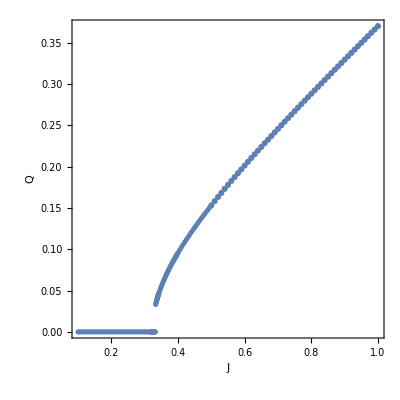
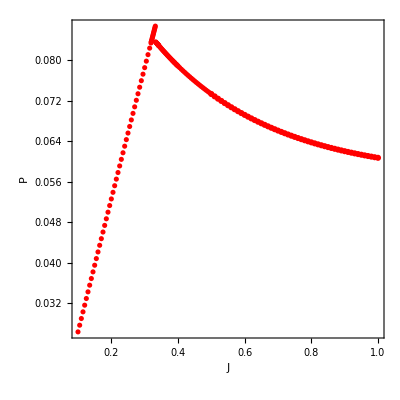
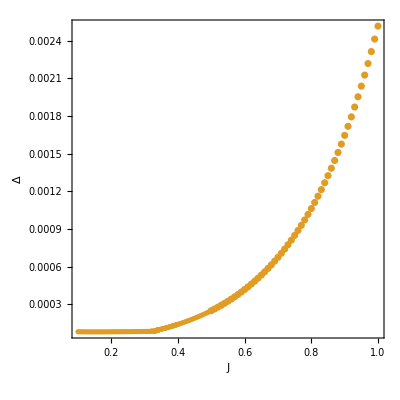

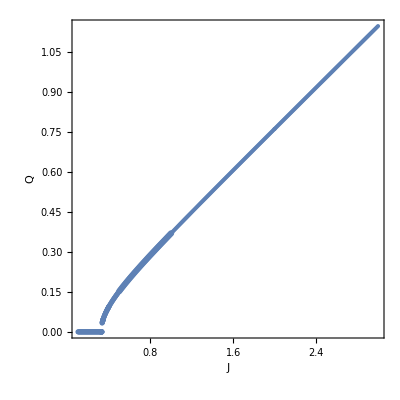
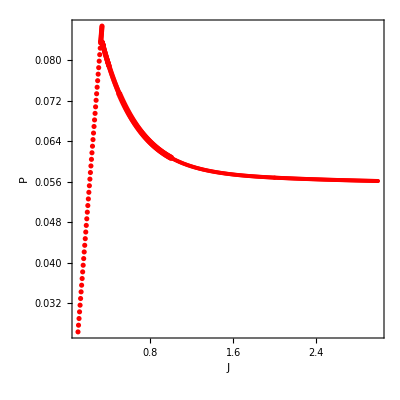
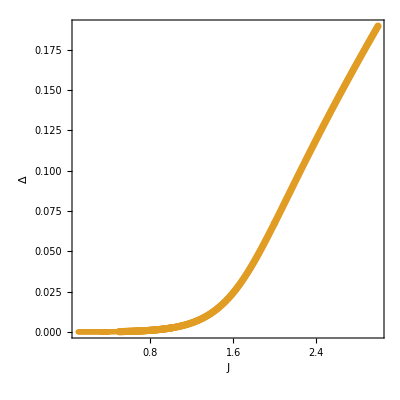

changing J T=0.04  Lx=Ly=20

```mathematica
data
```

{{0.5,{0.659587,0.565609,0.158966,0.0665974,-0.212558+0. ⅈ,-0.563159}},{0.51,{0.66998,0.576257,0.163993,0.0660446,-0.212008+0. ⅈ,-0.573969}},{0.52,{0.680351,0.586879,0.168948,0.0655085,-0.211468+0. ⅈ,-0.584749}},{0.53,{0.690703,0.597478,0.173837,0.0649887,-0.210937+0. ⅈ,-0.595502}},{0.54,{0.701038,0.608055,0.178666,0.0644848,-0.210414+0. ⅈ,-0.606228}},{0.55,{0.711358,0.618611,0.183439,0.0639962,-0.2099+0. ⅈ,-0.61693}},{0.56,{0.721666,0.629147,0.188161,0.0635226,-0.209395+0. ⅈ,-0.627609}},{0.57,{0.731963,0.639666,0.192835,0.0630634,-0.208897+0. ⅈ,-0.638266}},{0.58,{0.742251,0.650168,0.197467,0.0626183,-0.208408+0. ⅈ,-0.648903}},{0.59,{0.752532,0.660655,0.202057,0.0621869,-0.207927+0. ⅈ,-0.659521}},{0.6,{0.762807,0.671128,0.20661,0.0617689,-0.207454+0. ⅈ,-0.670122}},{0.61,{0.773078,0.681587,0.211128,0.0613638,-0.206988+0. ⅈ,-0.680706}},{0.62,{0.783345,0.692035,0.215613,0.0609713,-0.206531+0. ⅈ,-0.691275}},{0.63,{0.79361,0.702471,0.220068,0.060591,-0.206081+0. ⅈ,-0.70183}},{0.64,{0.803874,0.712898,0.224494,0.0602227,-0.205639+0. ⅈ,-0.712373}},{0.65,{0.814138,0.723315,0.228893,0.059866,-0.205205+0. ⅈ,-0.722903}},{0.66,{0.824403,0.733725,0.233266,0.0595206,-0.204779+0. ⅈ,-0.733423}},{0.67,{0.834669,0.744127,0.237616,0.0591862,-0.20436+0. ⅈ,-0.743933}},{0.68,{0.844938,0.754523,0.241944,0.0588624,-0.203949+0. ⅈ,-0.754434}},{0.69,{0.85521,0.764913,0.246251,0.0585491,-0.203545+0. ⅈ,-0.764927}},{0.7,{0.865486,0.775299,0.250538,0.0582458,-0.203149+0. ⅈ,-0.775412}},{0.71,{0.875765,0.78568,0.254806,0.0579523,-0.20276+0. ⅈ,-0.785891}},{0.72,{0.88605,0.796058,0.259056,0.0576684,-0.202379+0. ⅈ,-0.796364}},{0.73,{0.89634,0.806433,0.263289,0.0573938,-0.202006+0. ⅈ,-0.806832}},{0.74,{0.906636,0.816806,0.267507,0.0571281,-0.20164+0. ⅈ,-0.817296}},{0.75,{0.916937,0.827177,0.27171,0.0568712,-0.201281+0. ⅈ,-0.827755}},{0.76,{0.927245,0.837547,0.275898,0.0566228,-0.200929+0. ⅈ,-0.838212}},{0.77,{0.937559,0.847917,0.280073,0.0563826,-0.200585+0. ⅈ,-0.848666}},{0.78,{0.947881,0.858287,0.284235,0.0561503,-0.200248+0. ⅈ,-0.859118}},{0.79,{0.958209,0.868656,0.288385,0.0559259,-0.199917+0. ⅈ,-0.869568}},{0.8,{0.968545,0.879027,0.292524,0.0557089,-0.199594+0. ⅈ,-0.880017}},{0.81,{0.978888,0.889399,0.296651,0.0554992,-0.199278+0. ⅈ,-0.890466}},{0.82,{0.989238,0.899772,0.300768,0.0552965,-0.198969+0. ⅈ,-0.900914}},{0.83,{0.999596,0.910147,0.304875,0.0551006,-0.198666+0. ⅈ,-0.911362}},{0.84,{1.00996,0.920524,0.308973,0.0549114,-0.19837+0. ⅈ,-0.921811}},{0.85,{1.02034,0.930904,0.313061,0.0547285,-0.198081+0. ⅈ,-0.932261}},{0.86,{1.03072,0.941287,0.317141,0.0545518,-0.197798+0. ⅈ,-0.942711}},{0.87,{1.04111,0.951672,0.321213,0.0543811,-0.197521+0. ⅈ,-0.953163}},{0.88,{1.0515,0.962061,0.325276,0.0542162,-0.197251+0. ⅈ,-0.963617}},{0.89,{1.06191,0.972453,0.329333,0.0540568,-0.196987+0. ⅈ,-0.974073}},{0.9,{1.07232,0.982849,0.333382,0.0539029,-0.196729+0. ⅈ,-0.984531}},{0.91,{1.08274,0.993248,0.337424,0.0537541,-0.196477+0. ⅈ,-0.994991}},{0.92,{1.09317,1.00365,0.34146,0.0536104,-0.19623+0. ⅈ,-1.00545}},{0.93,{1.10361,1.01406,0.34549,0.0534716,-0.19599+0. ⅈ,-1.01592}},{0.94,{1.11405,1.02447,0.349514,0.0533373,-0.195755+0. ⅈ,-1.02639}},{0.95,{1.1245,1.03489,0.353532,0.0532077,-0.195525+0. ⅈ,-1.03686}},{0.96,{1.13496,1.04531,0.357544,0.0530824,-0.195301+0. ⅈ,-1.04734}},{0.97,{1.14543,1.05573,0.361552,0.0529614,-0.195082+0. ⅈ,-1.05781}},{0.98,{1.1559,1.06616,0.365554,0.0528444,-0.194868+0. ⅈ,-1.0683}},{0.99,{1.16638,1.0766,0.369551,0.0527313,-0.194659+0. ⅈ,-1.07878}},{1.,{1.17687,1.08704,0.373545,0.0526219,-0.194455+0. ⅈ,-1.08927}},{1.01,{1.18736,1.09748,0.377533,0.0525163,-0.194255+0. ⅈ,-1.09976}},{1.02,{1.19787,1.10793,0.381518,0.0524141,-0.194061+0. ⅈ,-1.11026}},{1.03,{1.20837,1.11839,0.385498,0.0523153,-0.19387+0. ⅈ,-1.12076}},{1.04,{1.21889,1.12885,0.389474,0.0522197,-0.193685+0. ⅈ,-1.13126}},{1.05,{1.22941,1.13931,0.393447,0.0521273,-0.193503+0. ⅈ,-1.14177}},{1.06,{1.23994,1.14978,0.397416,0.052038,-0.193326+0. ⅈ,-1.15228}},{1.07,{1.25047,1.16025,0.401382,0.0519515,-0.193153+0. ⅈ,-1.1628}},{1.08,{1.26102,1.17073,0.405344,0.0518678,-0.192984+0. ⅈ,-1.17332}},{1.09,{1.27156,1.18122,0.409304,0.0517868,-0.192819+0. ⅈ,-1.18385}},{1.1,{1.28212,1.19171,0.41326,0.0517085,-0.192657+0. ⅈ,-1.19437}},{1.11,{1.29267,1.2022,0.417213,0.0516326,-0.1925+0. ⅈ,-1.20491}},{1.12,{1.30324,1.2127,0.421164,0.0515591,-0.192346+0. ⅈ,-1.21544}},{1.13,{1.31381,1.2232,0.425111,0.051488,-0.192195+0. ⅈ,-1.22599}},{1.14,{1.32438,1.23371,0.429056,0.0514191,-0.192048+0. ⅈ,-1.23653}},{1.15,{1.33497,1.24423,0.432999,0.0513523,-0.191904+0. ⅈ,-1.24708}},{1.16,{1.34555,1.25474,0.436939,0.0512876,-0.191763+0. ⅈ,-1.25763}},{1.17,{1.35614,1.26527,0.440877,0.0512251,-0.191626+0. ⅈ,-1.26819}},{1.18,{1.36674,1.2758,0.444812,0.0511641,-0.191491+0. ⅈ,-1.27875}},{1.19,{1.37734,1.28633,0.448746,0.0511052,-0.19136+0. ⅈ,-1.28932}},{1.2,{1.38795,1.29687,0.452677,0.051048,-0.191231+0. ⅈ,-1.29989}},{1.21,{1.39856,1.30741,0.456606,0.0509926,-0.191105+0. ⅈ,-1.31046}},{1.22,{1.40918,1.31795,0.460533,0.0509388,-0.190982+0. ⅈ,-1.32104}},{1.23,{1.4198,1.32851,0.464458,0.0508866,-0.190862+0. ⅈ,-1.33162}},{1.24,{1.43042,1.33906,0.468382,0.050836,-0.190744+0. ⅈ,-1.34221}},{1.25,{1.44105,1.34962,0.472304,0.0507868,-0.190629+0. ⅈ,-1.3528}},{1.26,{1.45169,1.36019,0.476223,0.050739,-0.190516+0. ⅈ,-1.36339}},{1.27,{1.46233,1.37076,0.480142,0.0506926,-0.190405+0. ⅈ,-1.37399}},{1.28,{1.47297,1.38133,0.484058,0.0506475,-0.190297+0. ⅈ,-1.38459}},{1.29,{1.48361,1.39191,0.487974,0.0506037,-0.190192+0. ⅈ,-1.39519}},{1.3,{1.49427,1.40249,0.491887,0.0505611,-0.190088+0. ⅈ,-1.4058}},{1.31,{1.50492,1.41308,0.495799,0.0505197,-0.189986+0. ⅈ,-1.41641}},{1.32,{1.51558,1.42367,0.49971,0.0504794,-0.189887+0. ⅈ,-1.42703}},{1.33,{1.52624,1.43426,0.503619,0.0504402,-0.18979+0. ⅈ,-1.43765}},{1.34,{1.5369,1.44486,0.507527,0.0504021,-0.189694+0. ⅈ,-1.44827}},{1.35,{1.54757,1.45546,0.511434,0.050365,-0.189601+0. ⅈ,-1.4589}},{1.36,{1.55825,1.46607,0.51534,0.0503289,-0.189509+0. ⅈ,-1.46953}},{1.37,{1.56892,1.47668,0.519244,0.0502938,-0.18942+0. ⅈ,-1.48016}},{1.38,{1.5796,1.48729,0.523147,0.0502594,-0.189331+0. ⅈ,-1.4908}},{1.39,{1.59028,1.49791,0.527049,0.050226,-0.189245+0. ⅈ,-1.50144}},{1.4,{1.60097,1.50853,0.53095,0.0501935,-0.18916+0. ⅈ,-1.51208}},{1.41,{1.61166,1.51916,0.53485,0.0501622,-0.189079+0. ⅈ,-1.52272}},{1.42,{1.62235,1.52979,0.538748,0.0501308,-0.188996+0. ⅈ,-1.53337}},{1.43,{1.63304,1.54042,0.542646,0.0501007,-0.188916+0. ⅈ,-1.54403}},{1.44,{1.64374,1.55105,0.546543,0.0500717,-0.18884+0. ⅈ,-1.55468}},{1.45,{1.65444,1.56169,0.550438,0.0500425,-0.188761+0. ⅈ,-1.56534}},{1.46,{1.66515,1.57234,0.554333,0.0500145,-0.188686+0. ⅈ,-1.576}},{1.47,{1.67585,1.58298,0.558227,0.0499874,-0.188612+0. ⅈ,-1.58667}},{1.48,{1.68656,1.59363,0.56212,0.0499604,-0.188539+0. ⅈ,-1.59734}},{1.49,{1.69727,1.60428,0.566012,0.0499343,-0.188468+0. ⅈ,-1.60801}},{1.5,{1.70799,1.61494,0.569904,0.049909,-0.188398+0. ⅈ,-1.61868}},{1.51,{1.7187,1.6256,0.573794,0.0498839,-0.188329+0. ⅈ,-1.62936}},{1.52,{1.72942,1.63626,0.577684,0.0498601,-0.188263+0. ⅈ,-1.64004}},{1.53,{1.74014,1.64692,0.581573,0.0498357,-0.188195+0. ⅈ,-1.65072}},{1.54,{1.75087,1.65759,0.585461,0.0498124,-0.18813+0. ⅈ,-1.66141}},{1.55,{1.76159,1.66826,0.589348,0.0497902,-0.188068+0. ⅈ,-1.67209}},{1.56,{1.77232,1.67894,0.593235,0.0497673,-0.188003+0. ⅈ,-1.68278}},{1.57,{1.78305,1.68961,0.59712,0.049746,-0.187943+0. ⅈ,-1.69348}},{1.58,{1.79379,1.70029,0.601006,0.0497241,-0.187881+0. ⅈ,-1.70417}},{1.59,{1.80452,1.71098,0.60489,0.0497036,-0.187823+0. ⅈ,-1.71487}},{1.6,{1.81526,1.72166,0.608774,0.0496827,-0.187763+0. ⅈ,-1.72557}},{1.61,{1.826,1.73235,0.612658,0.0496629,-0.187706+0. ⅈ,-1.73627}},{1.62,{1.83674,1.74304,0.61654,0.0496429,-0.187648+0. ⅈ,-1.74698}},{1.63,{1.84748,1.75373,0.620422,0.049624,-0.187594+0. ⅈ,-1.75769}},{1.64,{1.85823,1.76443,0.624304,0.0496048,-0.187538+0. ⅈ,-1.7684}},{1.65,{1.86898,1.77513,0.628185,0.0495862,-0.187484+0. ⅈ,-1.77911}},{1.66,{1.87972,1.78583,0.632065,0.0495686,-0.187432+0. ⅈ,-1.78982}},{1.67,{1.89048,1.79653,0.635945,0.0495502,-0.187379+0. ⅈ,-1.80054}},{1.68,{1.90123,1.80724,0.639824,0.0495329,-0.187328+0. ⅈ,-1.81126}},{1.69,{1.91198,1.81794,0.643702,0.0495155,-0.187277+0. ⅈ,-1.82198}},{1.7,{1.92274,1.82865,0.647581,0.0494989,-0.187228+0. ⅈ,-1.8327}},{1.71,{1.9335,1.83937,0.651458,0.0494821,-0.187178+0. ⅈ,-1.84343}},{1.72,{1.94426,1.85008,0.655335,0.0494659,-0.18713+0. ⅈ,-1.85416}},{1.73,{1.95502,1.8608,0.659212,0.0494501,-0.187084+0. ⅈ,-1.86489}},{1.74,{1.96578,1.87152,0.663088,0.0494342,-0.187036+0. ⅈ,-1.87562}},{1.75,{1.97655,1.88224,0.666964,0.049419,-0.186991+0. ⅈ,-1.88635}},{1.76,{1.98731,1.89296,0.670839,0.0494037,-0.186945+0. ⅈ,-1.89709}},{1.77,{1.99808,1.90369,0.674714,0.0493889,-0.186901+0. ⅈ,-1.90782}},{1.78,{2.00885,1.91442,0.678588,0.0493741,-0.186857+0. ⅈ,-1.91856}},{1.79,{2.01962,1.92515,0.682462,0.0493599,-0.186814+0. ⅈ,-1.9293}},{1.8,{2.03039,1.93588,0.686336,0.0493456,-0.186771+0. ⅈ,-1.94005}},{1.81,{2.04116,1.94661,0.690209,0.0493317,-0.186729+0. ⅈ,-1.95079}},{1.82,{2.05194,1.95735,0.694081,0.0493179,-0.186688+0. ⅈ,-1.96154}},{1.83,{2.06272,1.96809,0.697954,0.0493047,-0.186648+0. ⅈ,-1.97229}},{1.84,{2.07349,1.97883,0.701826,0.0492892,-0.186604+0. ⅈ,-1.98304}},{1.85,{2.08427,1.98957,0.705697,0.0492761,-0.186565+0. ⅈ,-1.99379}},{1.86,{2.09505,2.00031,0.709568,0.0492659,-0.186531+0. ⅈ,-2.00454}},{1.87,{2.10583,2.01106,0.713439,0.0492507,-0.186488+0. ⅈ,-2.0153}},{1.88,{2.11662,2.0218,0.71731,0.0492382,-0.18645+0. ⅈ,-2.02605}},{1.89,{2.1274,2.03255,0.72118,0.0492259,-0.186413+0. ⅈ,-2.03681}},{1.9,{2.13818,2.0433,0.725049,0.0492138,-0.186376+0. ⅈ,-2.04757}},{1.91,{2.14897,2.05405,0.728918,0.0492037,-0.186342+0. ⅈ,-2.05833}},{1.92,{2.15976,2.0648,0.732787,0.049192,-0.186307+0. ⅈ,-2.0691}},{1.93,{2.17055,2.07556,0.736656,0.0491786,-0.186269+0. ⅈ,-2.07986}},{1.94,{2.18134,2.08632,0.740525,0.0491672,-0.186234+0. ⅈ,-2.09063}},{1.95,{2.19213,2.09708,0.744393,0.0491559,-0.1862+0. ⅈ,-2.10139}},{1.96,{2.20292,2.10784,0.748261,0.0491448,-0.186166+0. ⅈ,-2.11216}},{1.97,{2.21371,2.1186,0.752128,0.0491339,-0.186132+0. ⅈ,-2.12293}},{1.98,{2.22451,2.12936,0.755995,0.0491231,-0.1861+0. ⅈ,-2.1337}},{1.99,{2.2353,2.14012,0.759862,0.0491125,-0.186067+0. ⅈ,-2.14448}},{2.,{2.2461,2.15089,0.763728,0.049102,-0.186035+0. ⅈ,-2.15525}},{0.5,{0.659587,0.565609,0.158966,0.0665974,-0.212558+0. ⅈ,-0.563159}},{0.49,{0.649169,0.554935,0.153859,0.0671677,-0.213117+0. ⅈ,-0.552318}},{0.48,{0.638723,0.544232,0.148663,0.0677558,-0.213686+0. ⅈ,-0.541443}},{0.47,{0.628246,0.533499,0.14337,0.0683625,-0.214265+0. ⅈ,-0.530533}},{0.46,{0.617734,0.522734,0.137966,0.0689882,-0.214855+0. ⅈ,-0.519586}},{0.45,{0.607183,0.511935,0.132439,0.0696338,-0.215457+0. ⅈ,-0.508599}},{0.44,{0.596588,0.501101,0.126773,0.0702999,-0.21607+0. ⅈ,-0.497571}},{0.43,{0.585946,0.490229,0.120946,0.0709873,-0.216695+0. ⅈ,-0.486499}},{0.42,{0.57525,0.479316,0.114935,0.0716966,-0.217333+0. ⅈ,-0.475381}},{0.41,{0.564495,0.468362,0.108707,0.0724289,-0.217986+0. ⅈ,-0.464214}},{0.4,{0.553675,0.457363,0.102224,0.0731849,-0.218653+0. ⅈ,-0.452995}},{0.39,{0.542783,0.446318,0.095433,0.0739656,-0.219335+0. ⅈ,-0.441723}},{0.38,{0.53181,0.435224,0.0882618,0.0747721,-0.220034+0. ⅈ,-0.430393}},{0.37,{0.520749,0.424078,0.0806087,0.0756052,-0.220751+0. ⅈ,-0.419004}},{0.37,{0.520749,0.424078,0.0806087,0.0756052,-0.220751+0. ⅈ,-0.419004}},{0.365,{0.515183,0.418485,0.0765565,0.0760322,-0.221117+0. ⅈ,-0.413286}},{0.36,{0.509591,0.412878,0.0723202,0.0764663,-0.221487+0. ⅈ,-0.407552}},{0.355,{0.503972,0.407256,0.0678656,0.0769075,-0.221863+0. ⅈ,-0.401801}},{0.35,{0.498324,0.401621,0.0631462,0.0773562,-0.222243+0. ⅈ,-0.396033}}}

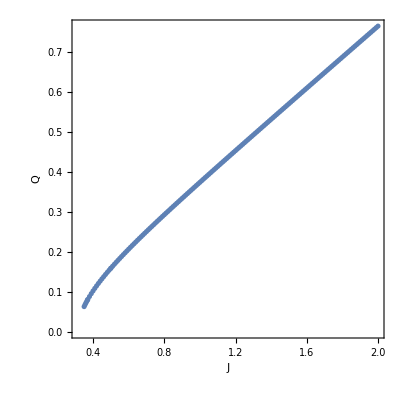
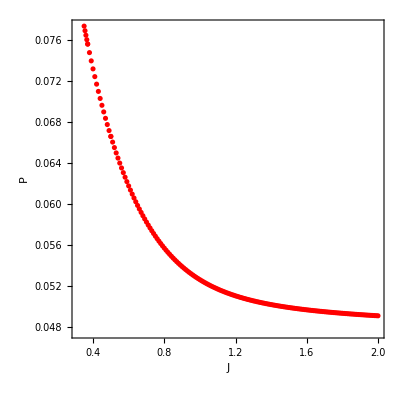
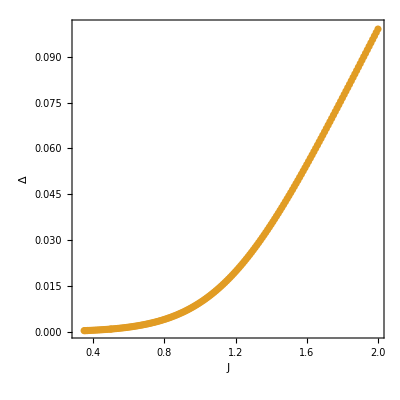

gap as a function of temperature at J=2 and J=1.5

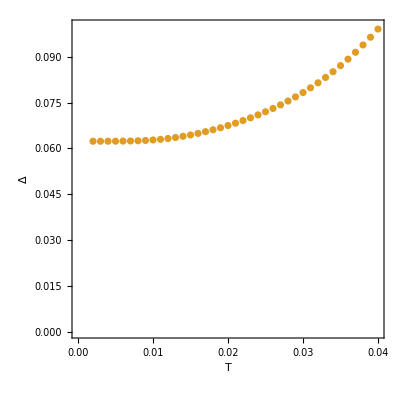
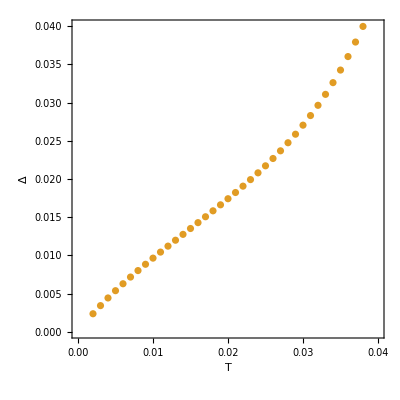

changing J T=0.02  Lx=Ly=20 gapped phase P=0

```mathematica
data
```

{{0.5,{0.559945,0.530187,0.192026,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.535529}},{0.51,{0.570832,0.541064,0.19587,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.546409}},{0.52,{0.581718,0.551941,0.199713,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.557288}},{0.53,{0.592604,0.562819,0.203556,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.568168}},{0.54,{0.60349,0.573698,0.207399,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.579049}},{0.55,{0.614376,0.584577,0.211241,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.58993}},{0.56,{0.625262,0.595457,0.215084,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.600811}},{0.57,{0.636149,0.606337,0.218927,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.611693}},{0.58,{0.647035,0.617217,0.222769,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.622575}},{0.59,{0.657921,0.628098,0.226612,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.633457}},{0.6,{0.668807,0.638979,0.230454,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.644339}},{0.61,{0.679694,0.649861,0.234296,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.655222}},{0.62,{0.69058,0.660743,0.238138,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.666106}},{0.63,{0.701467,0.671625,0.241981,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.676989}},{0.64,{0.712354,0.682508,0.245823,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.687873}},{0.65,{0.72324,0.693391,0.249665,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.698757}},{0.66,{0.734127,0.704274,0.253507,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.709641}},{0.67,{0.745014,0.715158,0.257349,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.720525}},{0.68,{0.755901,0.726042,0.261191,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.73141}},{0.69,{0.766788,0.736926,0.265033,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.742295}},{0.7,{0.777675,0.747811,0.268875,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.75318}},{0.71,{0.788563,0.758695,0.272717,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.764066}},{0.72,{0.79945,0.76958,0.276559,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.774951}},{0.73,{0.810338,0.780465,0.2804,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.785837}},{0.74,{0.821225,0.791351,0.284242,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.796723}},{0.75,{0.832113,0.802237,0.288084,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.807609}},{0.76,{0.843001,0.813122,0.291926,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.818496}},{0.77,{0.853889,0.824008,0.295767,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.829382}},{0.78,{0.864777,0.834895,0.299609,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.840269}},{0.79,{0.875665,0.845781,0.303451,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.851156}},{0.8,{0.886553,0.856668,0.307292,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.862043}},{0.81,{0.897442,0.867555,0.311134,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.87293}},{0.82,{0.90833,0.878442,0.314976,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.883818}},{0.83,{0.919219,0.889329,0.318817,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.894705}},{0.84,{0.930107,0.900216,0.322659,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.905593}},{0.85,{0.940996,0.911104,0.3265,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.916481}},{0.86,{0.951885,0.921991,0.330342,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.927369}},{0.87,{0.962774,0.932879,0.334184,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.938257}},{0.88,{0.973663,0.943767,0.338025,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.949145}},{0.89,{0.984552,0.954655,0.341867,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.960034}},{0.9,{0.995441,0.965544,0.345708,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.970922}},{0.91,{1.00633,0.976432,0.34955,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.981811}},{0.92,{1.01722,0.987321,0.353391,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.992699}},{0.93,{1.02811,0.998209,0.357233,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.00359}},{0.94,{1.039,1.0091,0.361074,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.01448}},{0.95,{1.04989,1.01999,0.364916,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.02537}},{0.96,{1.06078,1.03088,0.368757,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.03626}},{0.97,{1.07167,1.04177,0.372598,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.04714}},{0.98,{1.08256,1.05265,0.37644,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.05803}},{0.99,{1.09345,1.06354,0.380281,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.06892}},{1.,{1.10434,1.07443,0.384123,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.07981}},{1.01,{1.11523,1.08532,0.387964,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.0907}},{1.02,{1.12612,1.09621,0.391806,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.10159}},{1.03,{1.13701,1.1071,0.395647,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.11248}},{1.04,{1.1479,1.11799,0.399488,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.12337}},{1.05,{1.15879,1.12888,0.40333,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.13426}},{1.06,{1.16968,1.13977,0.407171,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.14515}},{1.07,{1.18057,1.15066,0.411013,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.15604}},{1.08,{1.19146,1.16155,0.414854,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.16693}},{1.09,{1.20235,1.17244,0.418695,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.17782}},{1.1,{1.21329,1.18338,0.422555,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.18876}},{1.11,{1.22413,1.19422,0.426378,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.1996}},{1.12,{1.23502,1.20511,0.43022,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.21049}},{1.13,{1.24591,1.216,0.434061,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.22139}},{1.14,{1.25681,1.22689,0.437902,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.23228}},{1.15,{1.2677,1.23778,0.441744,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.24317}},{1.16,{1.27859,1.24868,0.445585,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.25406}},{1.17,{1.28948,1.25957,0.449426,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.26495}},{1.18,{1.30037,1.27046,0.453268,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.27584}},{1.19,{1.31129,1.28138,0.45712,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.28676}},{1.2,{1.32215,1.29224,0.46095,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.29762}},{1.21,{1.33304,1.30313,0.464792,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.30851}},{1.22,{1.34393,1.31402,0.468633,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.3194}},{1.23,{1.35485,1.32494,0.472483,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.33032}},{1.24,{1.36572,1.3358,0.476316,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.34119}},{1.25,{1.37661,1.34669,0.480157,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.35208}},{1.26,{1.3875,1.35759,0.483998,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.36297}},{1.27,{1.39841,1.36849,0.487845,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.37387}},{1.28,{1.40928,1.37937,0.491681,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.38475}},{1.29,{1.42017,1.39026,0.495522,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.39564}},{1.3,{1.43108,1.40117,0.499369,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.40655}},{1.31,{1.44196,1.41204,0.503205,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.41743}},{1.32,{1.45285,1.42293,0.507046,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.42832}},{1.33,{1.46374,1.43383,0.510888,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.43921}},{1.34,{1.47464,1.44472,0.514731,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.45011}},{1.35,{1.48552,1.45561,0.51857,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.46099}},{1.36,{1.49642,1.4665,0.522412,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.47188}},{1.37,{1.50731,1.47739,0.526253,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.48278}},{1.38,{1.5182,1.48828,0.530094,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.49367}},{1.39,{1.52909,1.49918,0.533935,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.50456}},{1.4,{1.53999,1.51007,0.537778,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.51545}},{1.41,{1.55088,1.52096,0.541618,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.52634}},{1.42,{1.56177,1.53185,0.545459,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.53724}},{1.43,{1.57266,1.54275,0.549302,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.54813}},{1.44,{1.58355,1.55364,0.553142,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.55902}},{1.45,{1.59444,1.56453,0.556983,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.56991}},{1.46,{1.60534,1.57542,0.560825,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.5808}},{1.47,{1.61623,1.58631,0.564666,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.5917}},{1.48,{1.62712,1.5972,0.568507,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.60259}},{1.49,{1.63801,1.6081,0.572348,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.61348}},{1.5,{1.64891,1.61899,0.57619,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.62437}},{1.51,{1.6598,1.62988,0.580031,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.63526}},{1.52,{1.67069,1.64077,0.583872,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.64616}},{1.53,{1.68158,1.65166,0.587714,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.65705}},{1.54,{1.69248,1.66256,0.591556,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.66794}},{1.55,{1.70337,1.67345,0.595396,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.67883}},{1.56,{1.71426,1.68434,0.599238,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.68972}},{1.57,{1.72515,1.69523,0.603079,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.70062}},{1.58,{1.73604,1.70613,0.60692,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.71151}},{1.59,{1.74693,1.71702,0.610761,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.7224}},{1.6,{1.75783,1.72791,0.614603,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.73329}},{1.61,{1.76872,1.7388,0.618444,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.74419}},{1.62,{1.77961,1.74969,0.622285,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.75508}},{1.63,{1.7905,1.76059,0.626127,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.76597}},{1.64,{1.8014,1.77148,0.629968,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.77686}},{1.65,{1.81229,1.78237,0.633809,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.78776}},{1.66,{1.82319,1.79327,0.637654,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.79866}},{1.67,{1.83407,1.80416,0.641492,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.80954}},{1.68,{1.84497,1.81505,0.645333,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.82043}},{1.69,{1.85586,1.82594,0.649174,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.83133}},{1.7,{1.86675,1.83683,0.653015,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.84222}},{1.71,{1.87764,1.84773,0.656857,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.85311}},{1.72,{1.88854,1.85862,0.660699,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.864}},{1.73,{1.89943,1.86951,0.664539,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.87489}},{1.74,{1.91032,1.8804,0.668381,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.88579}},{1.75,{1.92121,1.8913,0.672222,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.89668}},{1.76,{1.93211,1.90219,0.676063,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.90757}},{1.77,{1.943,1.91308,0.679905,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.91847}},{1.78,{1.95389,1.92397,0.683745,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.92936}},{1.79,{1.96478,1.93487,0.687587,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.94025}},{1.8,{1.97568,1.94576,0.691428,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.95114}},{1.81,{1.98657,1.95665,0.69527,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.96204}},{1.82,{1.99746,1.96754,0.699111,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.97293}},{1.83,{2.00835,1.97844,0.702952,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.98382}},{1.84,{2.01925,1.98933,0.706794,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.99471}},{1.85,{2.03014,2.00022,0.710635,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.00561}},{1.86,{2.04103,2.01112,0.714476,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.0165}},{1.87,{2.05192,2.02201,0.718317,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.02739}},{1.88,{2.06282,2.0329,0.722159,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.03828}},{1.89,{2.07371,2.04379,0.726,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.04918}},{1.9,{2.0846,2.05469,0.729841,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.06007}},{1.91,{2.0955,2.06558,0.733682,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.07096}},{1.92,{2.10639,2.07647,0.737524,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.08185}},{1.93,{2.11728,2.08736,0.741365,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.09275}},{1.94,{2.12817,2.09826,0.745206,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.10364}},{1.95,{2.13907,2.10915,0.749048,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.11453}},{1.96,{2.14996,2.12004,0.752889,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.12542}},{1.97,{2.16085,2.13093,0.75673,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.13632}},{1.98,{2.17174,2.14183,0.760571,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.14721}},{1.99,{2.18264,2.15272,0.764413,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.1581}},{2.,{2.19353,2.16361,0.768254,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-2.169}},{0.5,{0.559945,0.530187,0.192026,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.535529}},{0.49,{0.549058,0.51931,0.188183,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.524649}},{0.48,{0.538172,0.508435,0.18434,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.513771}},{0.47,{0.527285,0.49756,0.180496,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.502893}},{0.46,{0.516398,0.486685,0.176652,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.492015}},{0.45,{0.505511,0.475812,0.172809,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.481138}},{0.44,{0.494624,0.464939,0.168964,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.470261}},{0.43,{0.483736,0.454067,0.16512,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.459385}},{0.42,{0.472848,0.443196,0.161275,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.44851}},{0.41,{0.461959,0.432326,0.15743,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.437635}},{0.4,{0.45107,0.421457,0.153585,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.42676}},{0.39,{0.440179,0.410589,0.149739,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.415886}},{0.38,{0.429289,0.399722,0.145894,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.405013}},{0.37,{0.418396,0.388857,0.142047,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.394141}},{0.36,{0.407503,0.377993,0.1382,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.383269}},{0.35,{0.396608,0.36713,0.134353,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.372398}},{0.34,{0.385712,0.356269,0.130505,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.361527}},{0.33,{0.374814,0.345409,0.126657,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.350657}},{0.32,{0.363913,0.334552,0.122807,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.339788}},{0.31,{0.35301,0.323696,0.118957,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.32892}},{0.3,{0.342104,0.312842,0.115106,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.318053}},{0.29,{0.331194,0.301991,0.111254,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.307186}},{0.28,{0.32028,0.291142,0.1074,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.296319}},{0.27,{0.30936,0.280295,0.103545,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.285453}},{0.26,{0.298434,0.269452,0.0996875,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.274588}},{0.25,{0.2875,0.258611,0.0958281,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.263722}},{0.24,{0.276556,0.247774,0.091966,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.252856}},{0.23,{0.265601,0.236939,0.0881006,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.24199}},{0.22,{0.25463,0.226109,0.0842313,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.231122}},{0.21,{0.243642,0.215281,0.080357,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.220251}},{0.2,{0.23263,0.204457,0.0764764,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.209376}},{0.19,{0.22159,0.193635,0.072588,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.198496}},{0.18,{0.210511,0.182816,0.0686895,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.187606}},{0.17,{0.199384,0.171998,0.064778,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.176704}},{0.16,{0.188192,0.16118,0.0608493,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.165784}},{0.15,{0.176916,0.150358,0.0568979,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.154838}},{0.14,{0.165526,0.139531,0.0529162,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.143856}},{0.13,{0.153985,0.128691,0.0488932,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.132821}},{0.12,{0.142238,0.117834,0.0448138,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.121715}},{0.11,{0.130212,0.106949,0.0406561,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.110507}},{0.1,{0.117809,0.096027,0.0363885,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.0991588}},{0.09,{0.104897,0.0850535,0.0319635,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.0876181}},{0.08,{0.0913054,0.0740149,0.0273071,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.075817}},{0.07,{0.0768303,0.062899,0.0222926,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.0636724}},{0.06,{0.0612448,0.051697,0.0166578,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.0510898}},{0.05,{0.0443026,0.0403863,0.00953213,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.0379533}},{0.04,{0.033765,0.0337649,-2.66328×10^-8,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.0300354}},{0.03,{0.033765,0.0337649,-2.66328×10^-8,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.0300354}},{0.02,{0.033765,0.0337649,-2.66328×10^-8,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.0300354}}}

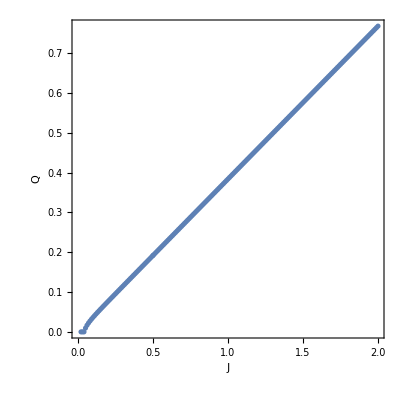
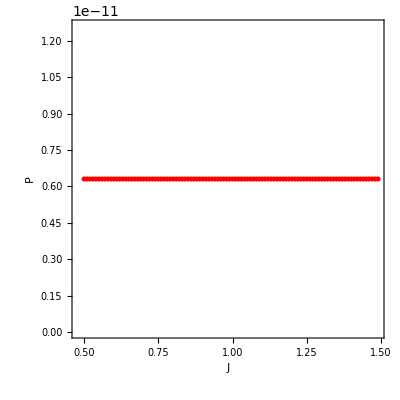
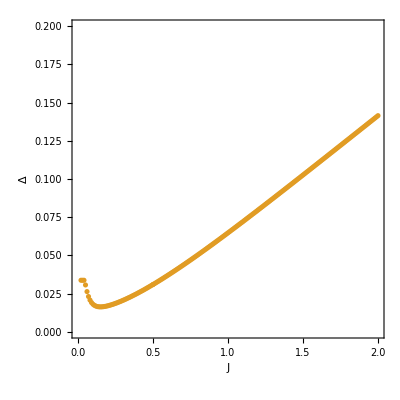
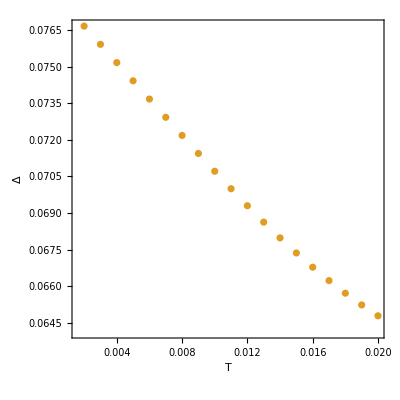
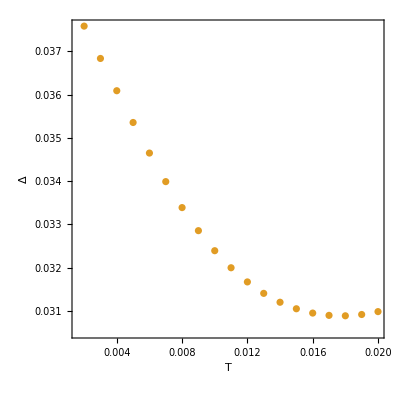

changing κ T=0.02 L=20 J=0.5

```mathematica
data
```

{{1.,{0.67976,0.572381,0.153179,0.0733173,-0.231913+0. ⅈ,-0.565885}},{0.995,{0.676336,0.570093,0.151338,0.0732463,-0.232226+0. ⅈ,-0.563575}},{0.99,{0.672921,0.567806,0.149485,0.0731738,-0.232536+0. ⅈ,-0.561267}},{0.985,{0.669513,0.565521,0.147619,0.0730999,-0.232842+0. ⅈ,-0.55896}},{0.98,{0.666114,0.563238,0.14574,0.0730246,-0.233145+0. ⅈ,-0.556655}},{0.975,{0.662723,0.560956,0.143847,0.0729478,-0.233443+0. ⅈ,-0.554351}},{0.97,{0.659341,0.558675,0.141939,0.0728696,-0.233739+0. ⅈ,-0.55205}},{0.965,{0.655966,0.556396,0.140016,0.0727901,-0.23403+0. ⅈ,-0.54975}},{0.96,{0.6526,0.554118,0.138078,0.0727092,-0.234318+0. ⅈ,-0.547451}},{0.955,{0.649242,0.551842,0.136122,0.072627,-0.234603+0. ⅈ,-0.545154}},{0.95,{0.645892,0.549567,0.13415,0.0725434,-0.234884+0. ⅈ,-0.542858}},{0.945,{0.642551,0.547293,0.132159,0.0724585,-0.235162+0. ⅈ,-0.540565}},{0.94,{0.639217,0.545021,0.13015,0.0723724,-0.235436+0. ⅈ,-0.538272}},{0.935,{0.635892,0.54275,0.12812,0.0722849,-0.235707+0. ⅈ,-0.535981}},{0.93,{0.632574,0.54048,0.12607,0.0721962,-0.235974+0. ⅈ,-0.533692}},{0.925,{0.629265,0.538212,0.123998,0.0721063,-0.236238+0. ⅈ,-0.531404}},{0.92,{0.625964,0.535945,0.121903,0.0720151,-0.236499+0. ⅈ,-0.529117}},{0.915,{0.62267,0.53368,0.119783,0.0719227,-0.236757+0. ⅈ,-0.526832}},{0.91,{0.619385,0.531415,0.117638,0.0718291,-0.237011+0. ⅈ,-0.524549}},{0.905,{0.616108,0.529152,0.115465,0.0717344,-0.237262+0. ⅈ,-0.522266}},{0.9,{0.612838,0.52689,0.113264,0.0716384,-0.23751+0. ⅈ,-0.519985}},{0.895,{0.609576,0.52463,0.111032,0.0715413,-0.237754+0. ⅈ,-0.517706}},{0.89,{0.606323,0.52237,0.108767,0.0714431,-0.237996+0. ⅈ,-0.515427}},{0.885,{0.603077,0.520112,0.106468,0.0713438,-0.238234+0. ⅈ,-0.51315}},{0.88,{0.599838,0.517855,0.104132,0.0712433,-0.238469+0. ⅈ,-0.510875}},{0.875,{0.596608,0.515599,0.101757,0.0711418,-0.238701+0. ⅈ,-0.5086}},{0.87,{0.593385,0.513344,0.099339,0.0710392,-0.238929+0. ⅈ,-0.506327}},{0.865,{0.59017,0.51109,0.0968754,0.0709355,-0.239155+0. ⅈ,-0.504055}},{0.86,{0.586963,0.508838,0.0943626,0.0708308,-0.239378+0. ⅈ,-0.501784}},{0.855,{0.583763,0.506586,0.0917965,0.070725,-0.239597+0. ⅈ,-0.499514}},{0.85,{0.580571,0.504336,0.0891723,0.0706182,-0.239814+0. ⅈ,-0.497246}},{0.845,{0.577387,0.502086,0.0864848,0.0705104,-0.240027+0. ⅈ,-0.494978}},{0.84,{0.574209,0.499838,0.0837277,0.0704016,-0.240238+0. ⅈ,-0.492712}},{0.835,{0.57104,0.49759,0.080894,0.0702918,-0.240446+0. ⅈ,-0.490446}},{0.83,{0.567878,0.495344,0.0779752,0.0701811,-0.24065+0. ⅈ,-0.488182}},{0.825,{0.564723,0.493098,0.0749612,0.0700694,-0.240852+0. ⅈ,-0.485919}},{0.82,{0.561576,0.490853,0.0718401,0.0699568,-0.241051+0. ⅈ,-0.483656}},{0.815,{0.558436,0.48861,0.0685972,0.0698432,-0.241247+0. ⅈ,-0.481395}},{0.81,{0.555303,0.486367,0.0652142,0.0697287,-0.24144+0. ⅈ,-0.479134}},{0.805,{0.552178,0.484125,0.0616679,0.0696133,-0.24163+0. ⅈ,-0.476875}},{0.8,{0.54906,0.481883,0.0579284,0.069497,-0.241817+0. ⅈ,-0.474616}},{0.795,{0.545949,0.479643,0.0539552,0.0693799,-0.242002+0. ⅈ,-0.472358}},{0.79,{0.542845,0.477403,0.0496927,0.0692619,-0.242183+0. ⅈ,-0.470101}},{0.785,{0.539748,0.475164,0.0450582,0.069143,-0.242362+0. ⅈ,-0.467845}},{0.78,{0.515595,0.448172,2.25355×10^-7,0.0733925,-0.243283+0. ⅈ,-0.440553}},{0.775,{0.518224,0.452628,8.11565×10^-11,0.0720933,-0.24326+0. ⅈ,-0.445066}},{0.77,{0.520842,0.457078,8.11565×10^-11,0.0707929,-0.243231+0. ⅈ,-0.449575}},{0.765,{0.523446,0.461518,8.11565×10^-11,0.0694911,-0.243197+0. ⅈ,-0.454074}},{0.76,{0.526034,0.465943,8.11565×10^-11,0.0681882,-0.243154+0. ⅈ,-0.45856}},{0.755,{0.528602,0.470347,8.11565×10^-11,0.066884,-0.243103+0. ⅈ,-0.463027}},{0.75,{0.531148,0.474726,8.11565×10^-11,0.0655787,-0.24304+0. ⅈ,-0.46747}},{0.745,{0.533668,0.479073,8.11565×10^-11,0.0642724,-0.242966+0. ⅈ,-0.471884}},{0.74,{0.536156,0.483383,8.11565×10^-11,0.0629649,-0.242876+0. ⅈ,-0.476261}},{0.735,{0.538608,0.487648,8.11565×10^-11,0.0616565,-0.242771+0. ⅈ,-0.480596}},{0.73,{0.541018,0.49186,8.11565×10^-11,0.0603471,-0.242647+0. ⅈ,-0.48488}},{0.725,{0.543379,0.496012,8.11565×10^-11,0.0590367,-0.242502+0. ⅈ,-0.489106}},{0.72,{0.545685,0.500094,8.11565×10^-11,0.0577254,-0.242332+0. ⅈ,-0.493264}},{0.715,{0.547928,0.504096,8.11565×10^-11,0.0564132,-0.242135+0. ⅈ,-0.497344}},{0.71,{0.550097,0.508008,8.11565×10^-11,0.0551002,-0.241908+0. ⅈ,-0.501335}},{0.705,{0.552184,0.511816,8.11565×10^-11,0.0537864,-0.241646+0. ⅈ,-0.505226}},{0.7,{0.554175,0.515509,8.11565×10^-11,0.0524718,-0.241344+0. ⅈ,-0.509004}},{0.695,{0.556059,0.519071,8.11565×10^-11,0.0511564,-0.240999+0. ⅈ,-0.512653}},{0.69,{0.557821,0.522487,8.11565×10^-11,0.0498403,-0.240604+0. ⅈ,-0.516158}},{0.685,{0.559443,0.525737,8.11565×10^-11,0.0485235,-0.240154+0. ⅈ,-0.5195}},{0.68,{0.560908,0.528802,8.11565×10^-11,0.0472059,-0.239642+0. ⅈ,-0.522659}},{0.675,{0.562195,0.531659,8.11565×10^-11,0.0458876,-0.239059+0. ⅈ,-0.525614}},{0.67,{0.563278,0.534284,8.11565×10^-11,0.0445686,-0.238397+0. ⅈ,-0.528338}},{0.665,{0.564133,0.536647,8.11565×10^-11,0.0432489,-0.237647+0. ⅈ,-0.530804}},{0.66,{0.564728,0.538719,8.11565×10^-11,0.0419285,-0.236798+0. ⅈ,-0.53298}},{0.655,{0.56503,0.540462,8.11565×10^-11,0.0406074,-0.235836+0. ⅈ,-0.53483}},{0.65,{0.564999,0.541838,8.11565×10^-11,0.0392855,-0.234749+0. ⅈ,-0.536315}},{0.645,{0.564593,0.542801,8.11565×10^-11,0.0379629,-0.233519+0. ⅈ,-0.53739}},{0.64,{0.563762,0.543303,8.11565×10^-11,0.0366394,-0.23213+0. ⅈ,-0.538005}},{0.635,{0.562451,0.543285,8.11565×10^-11,0.0353152,-0.230562+0. ⅈ,-0.538102}},{0.63,{0.560598,0.542686,8.11565×10^-11,0.03399,-0.228791+0. ⅈ,-0.537619}},{0.625,{0.558133,0.541434,8.11565×10^-11,0.0326639,-0.226793+0. ⅈ,-0.536485}},{0.62,{0.554979,0.539451,8.11565×10^-11,0.0313369,-0.224538+0. ⅈ,-0.53462}},{0.615,{0.551049,0.536649,8.11565×10^-11,0.0300087,-0.221996+0. ⅈ,-0.531937}},{0.61,{0.546248,0.532934,8.11565×10^-11,0.0286795,-0.21913+0. ⅈ,-0.528339}},{0.605,{0.540471,0.528198,8.11565×10^-11,0.0273492,-0.215901+0. ⅈ,-0.52372}},{0.6,{0.533604,0.522328,8.11565×10^-11,0.0260177,-0.212267+0. ⅈ,-0.517965}},{0.595,{0.525527,0.515201,8.11565×10^-11,0.0246851,-0.208181+0. ⅈ,-0.510951}},{0.59,{0.516108,0.506688,8.11565×10^-11,0.0233514,-0.203591+0. ⅈ,-0.502548}},{0.585,{0.505214,0.496654,8.11565×10^-11,0.0220168,-0.198444+0. ⅈ,-0.492618}},{0.58,{0.492705,0.484959,8.11565×10^-11,0.0206812,-0.192683+0. ⅈ,-0.481023}},{0.575,{0.478439,0.471462,8.11565×10^-11,0.0193446,-0.186248+0. ⅈ,-0.46762}},{0.57,{0.462279,0.456026,8.11565×10^-11,0.0180069,-0.179078+0. ⅈ,-0.45227}},{0.565,{0.444092,0.438519,8.11565×10^-11,0.0166679,-0.171112+0. ⅈ,-0.434843}},{0.56,{0.423766,0.418831,8.11565×10^-11,0.0153273,-0.162291+0. ⅈ,-0.415224}},{0.555,{0.401219,0.396879,8.11565×10^-11,0.0139847,-0.152563+0. ⅈ,-0.393333}},{0.55,{0.376413,0.372628,8.11565×10^-11,0.0126399,-0.14188+0. ⅈ,-0.369133}},{0.545,{0.349378,0.346109,8.11565×10^-11,0.0112926,-0.130212+0. ⅈ,-0.342653}},{0.54,{0.320238,0.317449,8.11565×10^-11,0.00994265,-0.117545+0. ⅈ,-0.31402}},{0.535,{0.289254,0.286911,8.11565×10^-11,0.0085908,-0.103897+0. ⅈ,-0.283495}},{0.53,{0.256909,0.254978,8.11565×10^-11,0.00723939,-0.0893321+0. ⅈ,-0.251563}},{0.525,{0.223919,0.222373,8.11565×10^-11,0.00589262,-0.0739735+0. ⅈ,-0.218942}},{0.52,{0.191347,0.190162,8.11565×10^-11,0.00455543,-0.0579914+0. ⅈ,-0.186699}},{0.515,{0.160321,0.159498,8.11565×10^-11,0.00321534,-0.0413721+0. ⅈ,-0.155979}},{0.51,{0.131515,0.13113,8.11565×10^-11,0.0017552,-0.0227593+0. ⅈ,-0.12751}}}

```mathematica
data
```

{{1.,{0.559945,0.530187,0.192026,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.535529}},{0.99,{0.552516,0.523426,0.18937,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.528591}},{0.98,{0.545172,0.516747,0.18671,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.521734}},{0.97,{0.53791,0.510149,0.184048,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.514957}},{0.96,{0.530731,0.50363,0.181381,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.508259}},{0.95,{0.523632,0.497189,0.17871,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.501637}},{0.94,{0.51661,0.490821,0.176034,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.495089}},{0.93,{0.509663,0.484525,0.173352,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.488612}},{0.92,{0.50279,0.478299,0.170663,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.482204}},{0.91,{0.495987,0.472139,0.167968,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.475863}},{0.9,{0.489254,0.466044,0.165264,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.469586}},{0.89,{0.482588,0.460013,0.162553,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.463374}},{0.88,{0.475987,0.454044,0.159831,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.457222}},{0.87,{0.469451,0.448135,0.1571,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.451131}},{0.86,{0.462978,0.442285,0.154358,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.445099}},{0.85,{0.456566,0.436492,0.151604,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.439125}},{0.84,{0.450214,0.430755,0.148837,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.433206}},{0.83,{0.44392,0.425073,0.146056,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.427342}},{0.82,{0.437684,0.419446,0.143261,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.421533}},{0.81,{0.431504,0.41387,0.140448,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.415776}},{0.8,{0.425379,0.408347,0.137618,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.410071}},{0.79,{0.419307,0.402874,0.134769,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.404416}},{0.78,{0.413289,0.39745,0.131899,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.398811}},{0.77,{0.407322,0.392076,0.129007,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.393255}},{0.76,{0.401405,0.386749,0.12609,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.387747}},{0.75,{0.395538,0.381469,0.123146,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.382285}},{0.74,{0.38972,0.376235,0.120174,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.37687}},{0.73,{0.38395,0.371046,0.117171,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.371499}},{0.72,{0.378226,0.365901,0.114133,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.366173}},{0.71,{0.372547,0.3608,0.111057,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.360891}},{0.7,{0.366914,0.355741,0.107941,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.355651}},{0.69,{0.361325,0.350725,0.10478,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.350453}},{0.68,{0.355779,0.345749,0.101569,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.345296}},{0.67,{0.350275,0.340814,0.0983029,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.340179}},{0.66,{0.344812,0.335919,0.094976,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.335102}},{0.65,{0.339391,0.331063,0.0915811,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.330065}},{0.64,{0.334009,0.326245,0.0881098,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.325065}},{0.63,{0.328667,0.321465,0.0845524,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.320103}},{0.62,{0.323364,0.316722,0.0808971,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.315179}},{0.61,{0.318098,0.312015,0.0771293,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.310291}},{0.6,{0.312869,0.307344,0.0732315,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.305438}},{0.59,{0.307677,0.302709,0.0691811,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.300621}},{0.58,{0.302521,0.298108,0.064949,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.295838}},{0.57,{0.2974,0.293542,0.0604965,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.29109}},{0.56,{0.292314,0.28901,0.0557704,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.286375}},{0.55,{0.287262,0.28451,0.0506935,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.281694}},{0.54,{0.282244,0.280043,0.0451472,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.277044}},{0.53,{0.277257,0.275608,0.0389308,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.272427}},{0.52,{0.272301,0.271203,0.0316503,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.267839}},{0.51,{0.267387,0.266838,0.0222782,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.263292}},{0.5,{0.262327,0.262328,0.000525755,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.258598}}}

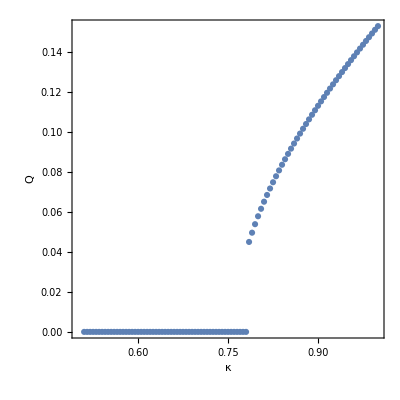
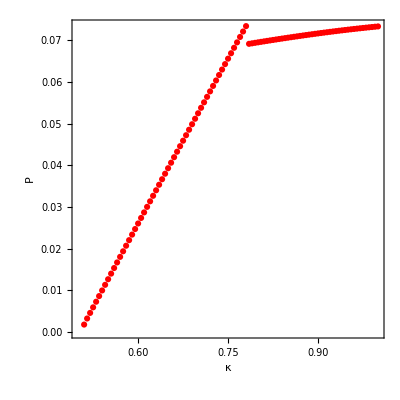
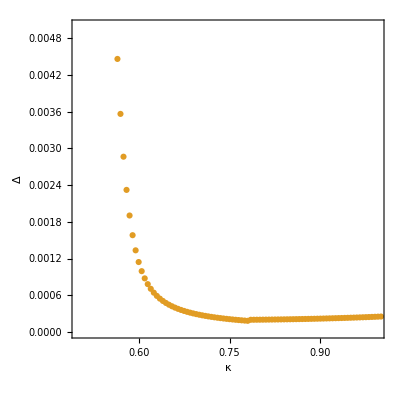

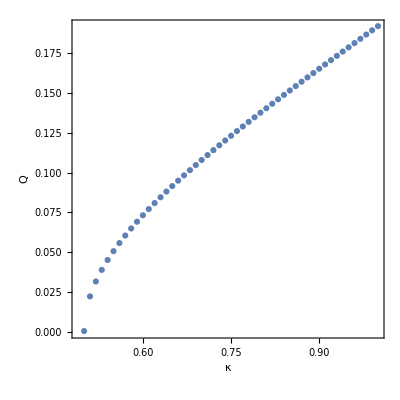
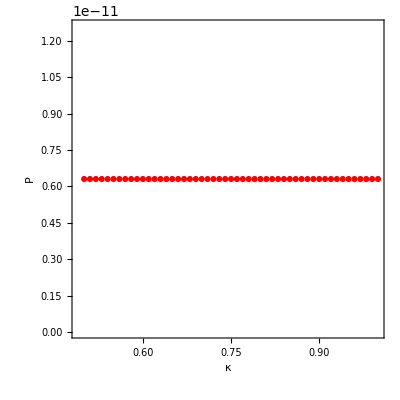
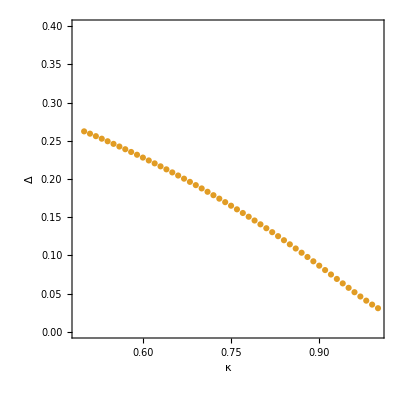

changing κ T=0.005 L=20 J=0.5

```mathematica
data
```

{{1.,{0.548382,0.540903,0.192063,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.542249}},{0.995,{0.544807,0.537416,0.190734,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.538738}},{0.99,{0.541254,0.53395,0.189404,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.535249}},{0.985,{0.537723,0.530504,0.188073,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.531781}},{0.98,{0.534211,0.527079,0.186741,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.528333}},{0.975,{0.53072,0.523673,0.185409,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.524904}},{0.97,{0.527247,0.520286,0.184076,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.521494}},{0.965,{0.523794,0.516918,0.182741,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.518102}},{0.96,{0.520359,0.513567,0.181406,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.514729}},{0.955,{0.516942,0.510235,0.18007,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.511373}},{0.95,{0.513543,0.50692,0.178732,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.508035}},{0.945,{0.510162,0.503622,0.177393,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.504714}},{0.94,{0.506798,0.500341,0.176053,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.50141}},{0.935,{0.503451,0.497076,0.174712,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.498123}},{0.93,{0.500121,0.493829,0.173369,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.494853}},{0.925,{0.496808,0.490598,0.172024,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.491599}},{0.92,{0.493512,0.487383,0.170678,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.488361}},{0.915,{0.490232,0.484184,0.16933,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.485139}},{0.91,{0.486968,0.481001,0.167981,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.481933}},{0.905,{0.48372,0.477834,0.166629,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.478743}},{0.9,{0.480488,0.474682,0.165276,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.475569}},{0.895,{0.477273,0.471546,0.16392,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.47241}},{0.89,{0.474072,0.468425,0.162562,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.469266}},{0.885,{0.470887,0.46532,0.161202,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.466138}},{0.88,{0.467718,0.46223,0.15984,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.463025}},{0.875,{0.464564,0.459154,0.158475,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.459927}},{0.87,{0.461425,0.456094,0.157108,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.456843}},{0.865,{0.458301,0.453048,0.155738,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.453775}},{0.86,{0.455191,0.450016,0.154365,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.45072}},{0.855,{0.452097,0.446999,0.152989,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.447681}},{0.85,{0.449016,0.443997,0.15161,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.444655}},{0.845,{0.445951,0.441008,0.150228,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.441644}},{0.84,{0.442899,0.438033,0.148842,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.438646}},{0.835,{0.439862,0.435073,0.147453,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.435663}},{0.83,{0.436838,0.432126,0.146061,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.432693}},{0.825,{0.433829,0.429192,0.144665,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.429737}},{0.82,{0.430833,0.426272,0.143264,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.426794}},{0.815,{0.42785,0.423366,0.14186,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.423865}},{0.81,{0.424882,0.420473,0.140452,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.420949}},{0.805,{0.421926,0.417592,0.139039,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.418046}},{0.8,{0.418984,0.414725,0.137621,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.415156}},{0.795,{0.416054,0.411871,0.136199,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.412279}},{0.79,{0.413138,0.409029,0.134772,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.409415}},{0.785,{0.410235,0.4062,0.133339,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.406563}},{0.78,{0.407344,0.403384,0.131902,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.403724}},{0.775,{0.404466,0.40058,0.130458,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.400898}},{0.77,{0.4016,0.397788,0.129009,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.398083}},{0.765,{0.398747,0.395009,0.127553,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.395281}},{0.76,{0.395905,0.392241,0.126092,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.392491}},{0.755,{0.393076,0.389485,0.124623,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.389712}},{0.75,{0.390259,0.386742,0.123148,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.386946}},{0.745,{0.387454,0.38401,0.121666,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.384191}},{0.74,{0.384661,0.381289,0.120176,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.381448}},{0.735,{0.381879,0.37858,0.118678,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.378716}},{0.73,{0.379108,0.375882,0.117172,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.375996}},{0.725,{0.37635,0.373196,0.115658,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.373287}},{0.72,{0.373602,0.370521,0.114134,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.370589}},{0.715,{0.370866,0.367857,0.112601,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.367902}},{0.71,{0.368141,0.365204,0.111059,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.365226}},{0.705,{0.365426,0.362561,0.109506,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.362561}},{0.7,{0.362723,0.35993,0.107942,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.359907}},{0.695,{0.36003,0.357309,0.106368,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.357264}},{0.69,{0.357349,0.354699,0.104781,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.354631}},{0.685,{0.354677,0.352099,0.103182,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.352008}},{0.68,{0.352017,0.349509,0.10157,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.349396}},{0.675,{0.349366,0.34693,0.0999441,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.346794}},{0.67,{0.346726,0.344361,0.0983039,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.344202}},{0.665,{0.344097,0.341802,0.0966484,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.341621}},{0.66,{0.341477,0.339253,0.0949769,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.339049}},{0.655,{0.338867,0.336714,0.0932884,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.336488}},{0.65,{0.336267,0.334185,0.091582,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.333936}},{0.645,{0.333677,0.331666,0.0898564,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.331394}},{0.64,{0.331097,0.329156,0.0881107,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.328861}},{0.635,{0.328527,0.326656,0.0863434,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.326338}},{0.63,{0.325966,0.324165,0.0845533,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.323825}},{0.625,{0.323415,0.321684,0.0827387,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.321321}},{0.62,{0.320873,0.319212,0.0808979,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.318826}},{0.615,{0.31834,0.316749,0.0790291,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.316341}},{0.61,{0.315817,0.314296,0.0771302,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.313865}},{0.605,{0.313303,0.311852,0.0751989,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.311398}},{0.6,{0.310797,0.309416,0.0732324,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.30894}},{0.595,{0.308301,0.30699,0.0712279,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.306491}},{0.59,{0.305814,0.304572,0.069182,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.30405}},{0.585,{0.303336,0.302164,0.0670908,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.301619}},{0.58,{0.300867,0.299764,0.0649499,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.299196}},{0.575,{0.298406,0.297372,0.0627542,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.296782}},{0.57,{0.295954,0.29499,0.0604975,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.294377}},{0.565,{0.293511,0.292615,0.0581728,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.29198}},{0.56,{0.291076,0.29025,0.0557714,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.289591}},{0.555,{0.288649,0.287892,0.053283,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.287211}},{0.55,{0.286231,0.285543,0.0506946,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.284839}},{0.545,{0.283822,0.283203,0.04799,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.282476}},{0.54,{0.28142,0.28087,0.0451482,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.28012}},{0.535,{0.279027,0.278546,0.0421413,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.277773}},{0.53,{0.276642,0.27623,0.0389312,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.275434}},{0.525,{0.274265,0.273921,0.0354625,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.273103}},{0.52,{0.271896,0.271621,0.0316502,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.27078}},{0.515,{0.269534,0.269328,0.0273513,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.268464}},{0.51,{0.267179,0.267041,0.022287,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.266155}},{0.505,{0.264821,0.264752,0.0157487,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.263843}},{0.5,{0.262715,0.262715,0.000936465,5.26033×10^-13,-1.10104×10^-11+0. ⅈ,-0.261783}}}

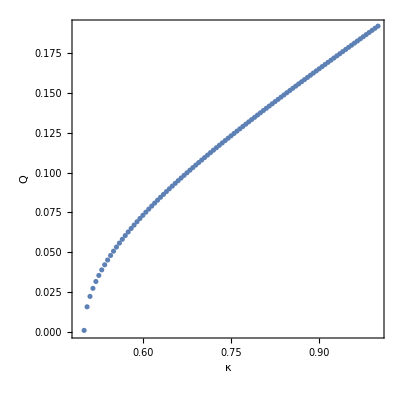
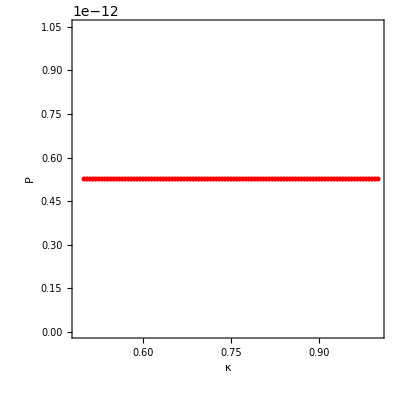
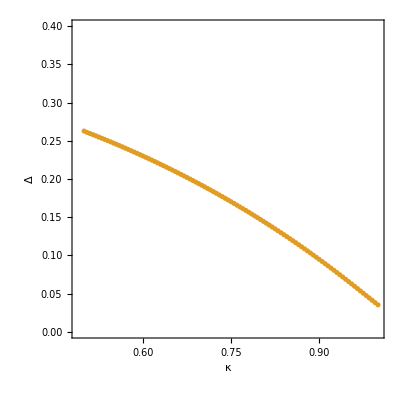

changing κ T=0.02 L=20 J=1

```mathematica
data
```

{{1.,{1.19679,1.09262,0.370172,0.0607236,-0.223011+0. ⅈ,-1.08781}},{0.995,{1.18952,1.08727,0.367395,0.0604424,-0.223524+0. ⅈ,-1.08244}},{0.99,{1.18227,1.08193,0.364616,0.0601537,-0.224027+0. ⅈ,-1.07708}},{0.985,{1.17505,1.0766,0.361836,0.0598577,-0.22452+0. ⅈ,-1.07174}},{0.98,{1.16785,1.07129,0.359055,0.0595544,-0.225001+0. ⅈ,-1.06641}},{0.975,{1.16068,1.06598,0.356272,0.0592438,-0.225471+0. ⅈ,-1.06109}},{0.97,{1.15354,1.06069,0.353489,0.0589259,-0.225931+0. ⅈ,-1.05578}},{0.965,{1.14642,1.05541,0.350703,0.0586008,-0.226379+0. ⅈ,-1.05048}},{0.96,{1.13933,1.05013,0.347917,0.0582684,-0.226816+0. ⅈ,-1.0452}},{0.955,{1.13227,1.04487,0.345129,0.0579289,-0.227242+0. ⅈ,-1.03992}},{0.95,{1.12523,1.03962,0.342339,0.0575822,-0.227656+0. ⅈ,-1.03466}},{0.945,{1.11822,1.03438,0.339548,0.0572284,-0.228059+0. ⅈ,-1.02941}},{0.94,{1.11123,1.02915,0.336755,0.0568674,-0.22845+0. ⅈ,-1.02417}},{0.935,{1.10428,1.02393,0.33396,0.0564993,-0.228829+0. ⅈ,-1.01894}},{0.93,{1.09734,1.01872,0.331163,0.0561241,-0.229196+0. ⅈ,-1.01373}},{0.925,{1.09044,1.01352,0.328364,0.0557418,-0.229551+0. ⅈ,-1.00852}},{0.92,{1.08356,1.00833,0.325563,0.0553523,-0.229893+0. ⅈ,-1.00333}},{0.915,{1.07671,1.00315,0.32276,0.0549557,-0.230223+0. ⅈ,-0.99814}},{0.91,{1.06989,0.997976,0.319955,0.054552,-0.230539+0. ⅈ,-0.992965}},{0.905,{1.06309,0.992813,0.317148,0.054141,-0.230843+0. ⅈ,-0.9878}},{0.9,{1.05632,0.987659,0.314338,0.0537229,-0.231133+0. ⅈ,-0.982645}},{0.895,{1.04957,0.982514,0.311526,0.0532975,-0.231409+0. ⅈ,-0.9775}},{0.89,{1.04285,0.977376,0.308711,0.0528648,-0.231671+0. ⅈ,-0.972364}},{0.885,{1.03616,0.972247,0.305894,0.0524248,-0.231919+0. ⅈ,-0.967237}},{0.88,{1.02949,0.967126,0.303075,0.0519774,-0.232151+0. ⅈ,-0.962118}},{0.875,{1.02285,0.962012,0.300252,0.0515224,-0.232368+0. ⅈ,-0.957008}},{0.87,{1.01623,0.956905,0.297427,0.0510599,-0.232569+0. ⅈ,-0.951907}},{0.865,{1.00964,0.951806,0.294599,0.0505897,-0.232754+0. ⅈ,-0.946813}},{0.86,{1.00307,0.946712,0.291769,0.0501116,-0.232922+0. ⅈ,-0.941727}},{0.855,{0.996521,0.941625,0.288935,0.0496256,-0.233073+0. ⅈ,-0.936648}},{0.85,{0.989998,0.936543,0.286099,0.0491315,-0.233205+0. ⅈ,-0.931576}},{0.845,{0.983498,0.931467,0.28326,0.048629,-0.233317+0. ⅈ,-0.92651}},{0.84,{0.977021,0.926395,0.280418,0.048118,-0.23341+0. ⅈ,-0.92145}},{0.835,{0.970564,0.921328,0.277573,0.0475983,-0.233482+0. ⅈ,-0.916396}},{0.83,{0.964128,0.916263,0.274726,0.0470696,-0.233533+0. ⅈ,-0.911346}},{0.825,{0.957712,0.911202,0.271876,0.0465315,-0.23356+0. ⅈ,-0.9063}},{0.82,{0.951315,0.906143,0.269024,0.0459837,-0.233562+0. ⅈ,-0.901258}},{0.815,{0.944935,0.901085,0.26617,0.0454259,-0.233539+0. ⅈ,-0.896219}},{0.81,{0.938571,0.896027,0.263313,0.0448575,-0.233488+0. ⅈ,-0.891181}},{0.805,{0.932222,0.890969,0.260455,0.0442779,-0.233408+0. ⅈ,-0.886144}},{0.8,{0.925887,0.885909,0.257596,0.0436868,-0.233296+0. ⅈ,-0.881107}},{0.795,{0.919563,0.880846,0.254736,0.0430833,-0.23315+0. ⅈ,-0.876069}},{0.79,{0.913249,0.875777,0.251875,0.0424667,-0.232967+0. ⅈ,-0.871028}},{0.785,{0.906942,0.870703,0.249015,0.041836,-0.232744+0. ⅈ,-0.865983}},{0.78,{0.90064,0.865619,0.246157,0.0411901,-0.232476+0. ⅈ,-0.860931}},{0.775,{0.894339,0.860525,0.2433,0.0405278,-0.232161+0. ⅈ,-0.855871}},{0.77,{0.888035,0.855416,0.240448,0.0398475,-0.231791+0. ⅈ,-0.850799}},{0.765,{0.881725,0.85029,0.2376,0.0391475,-0.231362+0. ⅈ,-0.845713}},{0.76,{0.875403,0.845143,0.23476,0.0384257,-0.230864+0. ⅈ,-0.840609}},{0.755,{0.869062,0.839969,0.23193,0.0376793,-0.230289+0. ⅈ,-0.835482}},{0.75,{0.862695,0.834762,0.229113,0.0369053,-0.229625+0. ⅈ,-0.830326}},{0.745,{0.856291,0.829513,0.226313,0.0360995,-0.228856+0. ⅈ,-0.825134}},{0.74,{0.849838,0.824214,0.223535,0.0352569,-0.227964+0. ⅈ,-0.819897}},{0.735,{0.843319,0.818849,0.220786,0.0343709,-0.226924+0. ⅈ,-0.814601}},{0.73,{0.836712,0.8134,0.218076,0.0334328,-0.2257+0. ⅈ,-0.809229}},{0.725,{0.829986,0.807841,0.215415,0.0324307,-0.224244+0. ⅈ,-0.803757}},{0.72,{0.823096,0.802135,0.212822,0.0313482,-0.222487+0. ⅈ,-0.79815}},{0.715,{0.815976,0.796224,0.210321,0.0301618,-0.220324+0. ⅈ,-0.792354}},{0.71,{0.808525,0.790018,0.207947,0.0288375,-0.21759+0. ⅈ,-0.786285}},{0.705,{0.800595,0.783379,0.205742,0.0273324,-0.214029+0. ⅈ,-0.779811}},{0.7,{0.791998,0.776114,0.203748,0.0256062,-0.209287+0. ⅈ,-0.772746}},{0.695,{0.78273,0.768146,0.201898,0.0237255,-0.203218+0. ⅈ,-0.765004}},{0.69,{0.773298,0.759837,0.199949,0.0219405,-0.196475+0. ⅈ,-0.756908}},{0.685,{0.764218,0.751654,0.197732,0.0204217,-0.189897+0. ⅈ,-0.748898}},{0.68,{0.755501,0.743667,0.195285,0.0191229,-0.183586+0. ⅈ,-0.741051}},{0.675,{0.746977,0.735772,0.192691,0.0179537,-0.177319+0. ⅈ,-0.733273}},{0.67,{0.738497,0.727855,0.190007,0.016848,-0.170845+0. ⅈ,-0.725461}},{0.665,{0.729946,0.719823,0.18727,0.0157616,-0.163932+0. ⅈ,-0.717527}},{0.66,{0.721238,0.7116,0.184504,0.014663,-0.156354+0. ⅈ,-0.709398}},{0.655,{0.712302,0.703121,0.181724,0.0135263,-0.14787+0. ⅈ,-0.701012}},{0.65,{0.703076,0.694328,0.17894,0.0123269,-0.138182+0. ⅈ,-0.692313}},{0.645,{0.693504,0.685165,0.176161,0.0110352,-0.126891+0. ⅈ,-0.683245}},{0.64,{0.683527,0.675575,0.173392,0.00960877,-0.113389+0. ⅈ,-0.673754}},{0.635,{0.673088,0.665501,0.170639,0.00797267,-0.0966004+0. ⅈ,-0.66378}},{0.63,{0.662137,0.654891,0.167902,0.00595601,-0.0741324+0. ⅈ,-0.653273}},{0.625,{0.650584,0.643656,0.16519,0.0028334,-0.0362497+0. ⅈ,-0.642145}},{0.62,{0.643404,0.636762,0.161796,-1.41277×10^-6,0.0000182298+0. ⅈ,-0.63522}},{0.615,{0.638271,0.631908,0.158058,-1.80457×10^-8,2.32998×10^-7+0. ⅈ,-0.630275}},{0.61,{0.633154,0.627071,0.15426,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.625347}},{0.605,{0.628056,0.622252,0.150398,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.620437}},{0.6,{0.622976,0.617451,0.146465,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.615545}},{0.595,{0.617915,0.612668,0.142456,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.610671}},{0.59,{0.612871,0.607902,0.138364,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.605814}},{0.585,{0.607845,0.603154,0.134182,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.600975}},{0.58,{0.602837,0.598424,0.1299,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.596154}},{0.575,{0.597846,0.593711,0.125508,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.59135}},{0.57,{0.592873,0.589015,0.120995,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.586563}},{0.565,{0.587917,0.584335,0.116346,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.581792}},{0.56,{0.582978,0.579673,0.111543,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.577039}},{0.555,{0.578056,0.575028,0.106566,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.572302}},{0.55,{0.573151,0.570399,0.101389,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.567582}},{0.545,{0.568262,0.565786,0.09598,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.562879}},{0.54,{0.563391,0.56119,0.0902963,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.558191}},{0.535,{0.558535,0.556611,0.0842825,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.553521}},{0.53,{0.553696,0.552047,0.0778624,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.548866}},{0.525,{0.548873,0.547499,0.0709249,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.544227}},{0.52,{0.544066,0.542967,0.0633003,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.539603}},{0.515,{0.539274,0.53845,0.054702,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.534995}},{0.51,{0.534494,0.533945,0.0445742,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.530398}},{0.505,{0.529711,0.529436,0.0314977,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.525798}},{0.5,{0.515932,0.515932,0.000985209,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.512203}}}

```mathematica
data
```

{{0.6,{0.622976,0.617451,0.146465,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.615545}},{0.605,{0.628056,0.622252,0.150398,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.620437}},{0.61,{0.633154,0.627071,0.15426,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.625347}},{0.615,{0.638271,0.631908,0.158058,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.630275}},{0.62,{0.643406,0.636764,0.161796,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.635221}},{0.625,{0.64856,0.641638,0.165477,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.640186}},{0.63,{0.653733,0.64653,0.169107,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.645169}},{0.635,{0.658925,0.651441,0.172687,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.650171}},{0.64,{0.664136,0.656371,0.176221,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.655192}},{0.645,{0.669367,0.66132,0.179713,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.660231}},{0.65,{0.674617,0.666288,0.183164,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.66529}},{0.655,{0.679887,0.671276,0.186577,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.670369}},{0.66,{0.685177,0.676283,0.189954,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.675467}},{0.665,{0.690487,0.68131,0.193297,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.680585}},{0.67,{0.695818,0.686357,0.196608,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.685722}},{0.675,{0.701169,0.691424,0.199888,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.69088}},{0.68,{0.706541,0.696511,0.20314,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.696058}},{0.685,{0.711933,0.701619,0.206364,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.701256}},{0.69,{0.717347,0.706747,0.209562,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.706475}},{0.695,{0.722783,0.711896,0.212735,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.711715}},{0.7,{0.728239,0.717066,0.215885,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.716976}},{0.705,{0.733718,0.722258,0.219012,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.722258}},{0.71,{0.739218,0.72747,0.222117,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.727561}},{0.715,{0.744741,0.732705,0.225203,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.732886}},{0.72,{0.750285,0.737961,0.228268,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.738233}},{0.725,{0.755853,0.743239,0.231315,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.743601}},{0.73,{0.761443,0.748539,0.234344,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.748992}},{0.735,{0.767056,0.753861,0.237356,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.754406}},{0.74,{0.772693,0.759207,0.240352,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.759842}},{0.745,{0.778352,0.764575,0.243332,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.7653}},{0.75,{0.784036,0.769966,0.246296,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.770782}},{0.755,{0.789743,0.77538,0.249247,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.776287}},{0.76,{0.795475,0.780818,0.252184,-8.77118×10^-11,1.13298×10^-9+0. ⅈ,-0.781816}},{0.765,{0.801231,0.786279,0.255107,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.787368}},{0.77,{0.807012,0.791765,0.258018,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.792944}},{0.775,{0.812817,0.797274,0.260916,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.798545}},{0.78,{0.818648,0.802808,0.263803,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.804169}},{0.785,{0.824504,0.808367,0.266679,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.809819}},{0.79,{0.830385,0.81395,0.269544,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.815493}},{0.795,{0.836292,0.819558,0.272398,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.821192}},{0.8,{0.842226,0.825192,0.275243,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.826916}},{0.805,{0.848186,0.830851,0.278078,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.832667}},{0.81,{0.854172,0.836536,0.280903,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.838442}},{0.815,{0.860185,0.842247,0.28372,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.844244}},{0.82,{0.866226,0.847984,0.286529,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.850072}},{0.825,{0.872293,0.853748,0.289329,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.855927}},{0.83,{0.878389,0.859539,0.292122,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.861809}},{0.835,{0.884512,0.865356,0.294907,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.867717}},{0.84,{0.890664,0.871201,0.297685,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.873653}},{0.845,{0.896844,0.877073,0.300455,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.879616}},{0.85,{0.903053,0.882973,0.30322,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.885607}},{0.855,{0.90929,0.888901,0.305978,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.891627}},{0.86,{0.915558,0.894858,0.308729,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.897674}},{0.865,{0.921854,0.900843,0.311475,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.90375}},{0.87,{0.928181,0.906856,0.314216,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.909855}},{0.875,{0.934538,0.912899,0.31695,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.915989}},{0.88,{0.940925,0.918971,0.31968,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.922152}},{0.885,{0.947343,0.925073,0.322405,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.928345}},{0.89,{0.953792,0.931204,0.325125,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.934568}},{0.895,{0.960272,0.937366,0.32784,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.940821}},{0.9,{0.966784,0.943558,0.330551,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.947105}},{0.905,{0.973328,0.949781,0.333258,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.953419}},{0.91,{0.979904,0.956035,0.335961,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.959765}},{0.915,{0.986513,0.96232,0.338661,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.966141}},{0.92,{0.993154,0.968637,0.341356,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.97255}},{0.925,{0.999829,0.974986,0.344048,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.97899}},{0.93,{1.00654,0.981367,0.346737,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.985463}},{0.935,{1.01328,0.987781,0.349423,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.991968}},{0.94,{1.02006,0.994228,0.352106,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-0.998507}},{0.945,{1.02687,1.00071,0.354786,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.00508}},{0.95,{1.03372,1.00722,0.357464,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.01169}},{0.955,{1.0406,1.01377,0.360139,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.01833}},{0.96,{1.04752,1.02036,0.362811,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.025}},{0.965,{1.05448,1.02698,0.365482,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.03171}},{0.97,{1.06148,1.03363,0.36815,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.03846}},{0.975,{1.06851,1.04033,0.370816,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.04525}},{0.98,{1.07559,1.04706,0.373481,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.05208}},{0.985,{1.08271,1.05384,0.376144,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.05895}},{0.99,{1.08987,1.06066,0.378805,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.06586}},{0.995,{1.09708,1.06752,0.381464,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.07281}},{1.,{1.10434,1.07443,0.384123,6.30377×10^-12,-3.30111×10^-11+0. ⅈ,-1.07981}}}

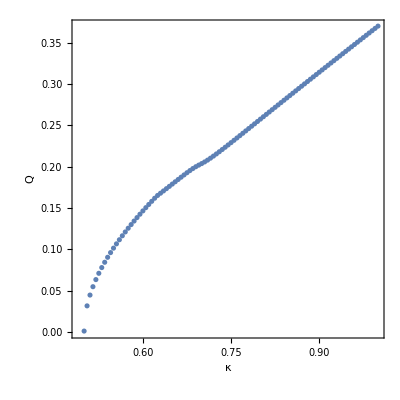
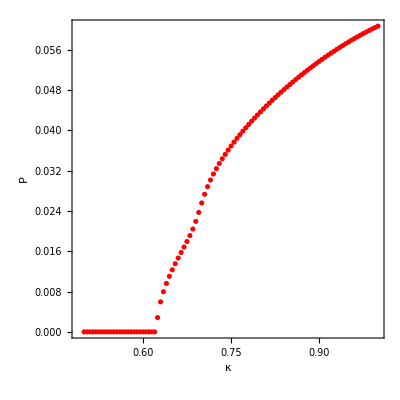
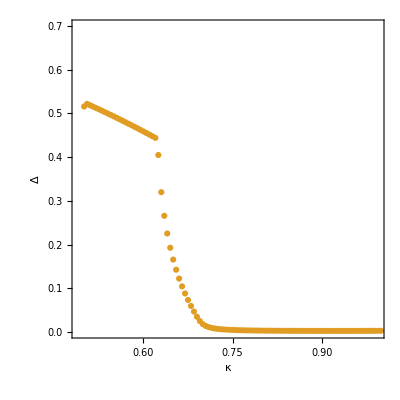

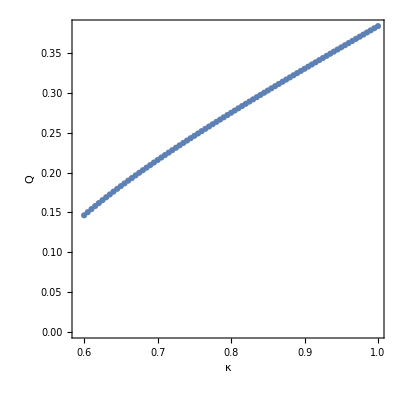
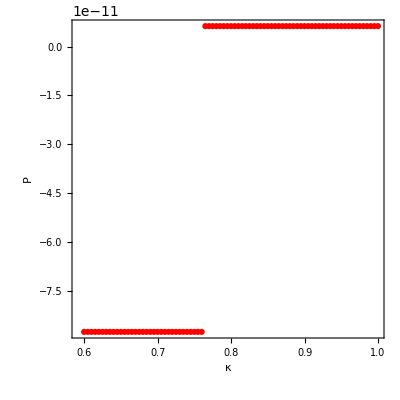
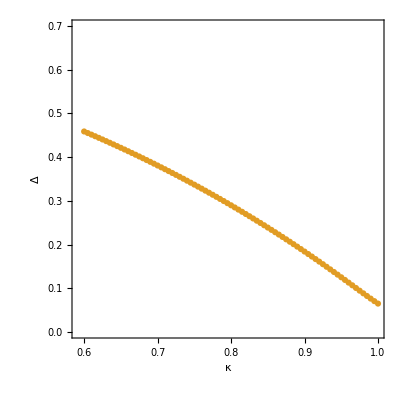

changing κ T=0.02 L=20 J=0.4

```mathematica
data
```

{{1.,{0.574423,0.46571,0.095659,0.078838,-0.234645+0. ⅈ,-0.458684}},{0.995,{0.571667,0.463913,0.0936637,0.0788072,-0.234899+0. ⅈ,-0.456867}},{0.99,{0.568916,0.462117,0.0916352,0.0787756,-0.235151+0. ⅈ,-0.455051}},{0.985,{0.56617,0.460321,0.0895712,0.0787431,-0.2354+0. ⅈ,-0.453236}},{0.98,{0.563428,0.458525,0.0874693,0.0787097,-0.235647+0. ⅈ,-0.451422}},{0.975,{0.560692,0.45673,0.0853266,0.0786754,-0.235891+0. ⅈ,-0.449608}},{0.97,{0.55796,0.454936,0.0831399,0.0786403,-0.236133+0. ⅈ,-0.447794}},{0.965,{0.555233,0.453142,0.0809056,0.0786044,-0.236373+0. ⅈ,-0.445982}},{0.96,{0.552511,0.451348,0.0786197,0.0785676,-0.23661+0. ⅈ,-0.444169}},{0.955,{0.549794,0.449555,0.0762773,0.07853,-0.236845+0. ⅈ,-0.442357}},{0.95,{0.547081,0.447762,0.0738732,0.0784916,-0.237078+0. ⅈ,-0.440546}},{0.945,{0.544373,0.445969,0.0714011,0.0784524,-0.237308+0. ⅈ,-0.438735}},{0.94,{0.54167,0.444177,0.0688536,0.0784123,-0.237536+0. ⅈ,-0.436925}},{0.935,{0.538971,0.442386,0.0662219,0.0783716,-0.237762+0. ⅈ,-0.435115}},{0.93,{0.536277,0.440594,0.0634956,0.07833,-0.237985+0. ⅈ,-0.433305}},{0.925,{0.533588,0.438803,0.0606619,0.0782876,-0.238206+0. ⅈ,-0.431496}},{0.92,{0.530903,0.437012,0.0577048,0.0782445,-0.238425+0. ⅈ,-0.429687}},{0.915,{0.528223,0.435221,0.0546043,0.0782007,-0.238642+0. ⅈ,-0.427879}},{0.91,{0.525547,0.433431,0.0513346,0.078156,-0.238856+0. ⅈ,-0.426071}},{0.905,{0.522876,0.431641,0.0478603,0.0781108,-0.239068+0. ⅈ,-0.424263}},{0.905,{0.522876,0.431641,0.0478603,0.0781108,-0.239068+0. ⅈ,-0.424263}},{0.9,{0.520209,0.429851,0.044134,0.0780646,-0.239278+0. ⅈ,-0.422456}},{0.905,{0.522876,0.431641,0.0478603,0.0781108,-0.239068+0. ⅈ,-0.424263}},{0.905,{0.522876,0.431641,0.0478603,0.0781108,-0.239068+0. ⅈ,-0.424263}},{0.9,{0.520209,0.429851,0.044134,0.0780646,-0.239278+0. ⅈ,-0.422456}},{0.905,{0.522876,0.431641,0.0478603,0.0781108,-0.239068+0. ⅈ,-0.424263}},{0.9,{0.520209,0.429851,0.0441337,0.0780647,-0.239278+0. ⅈ,-0.422455}},{0.905,{0.522876,0.431641,0.0478603,0.0781108,-0.239068+0. ⅈ,-0.424263}},{0.904,{0.522342,0.431283,0.047137,0.0781016,-0.23911+0. ⅈ,-0.423901}},{0.903,{0.521809,0.430925,0.0464032,0.0780924,-0.239153+0. ⅈ,-0.42354}},{0.902,{0.521275,0.430567,0.0456582,0.0780833,-0.239195+0. ⅈ,-0.423178}},{0.901,{0.520742,0.430209,0.0449022,0.078074,-0.239236+0. ⅈ,-0.422817}},{0.9,{0.520209,0.429851,0.0441338,0.0780647,-0.239278+0. ⅈ,-0.422455}},{0.899,{0.519676,0.429493,0.0433524,0.0780554,-0.23932+0. ⅈ,-0.422094}},{0.898,{0.519144,0.429135,0.042558,0.0780461,-0.239362+0. ⅈ,-0.421732}},{0.897,{0.518611,0.428777,0.0417486,0.0780368,-0.239403+0. ⅈ,-0.421371}},{0.896,{0.518078,0.428419,0.0409265,0.0780269,-0.239443+0. ⅈ,-0.421009}},{0.895,{0.517547,0.428061,0.0400848,0.0780178,-0.239486+0. ⅈ,-0.420648}},{0.894,{0.517015,0.427704,0.039227,0.0780085,-0.239527+0. ⅈ,-0.420287}},{0.893,{0.516483,0.427346,0.0383515,0.077999,-0.239569+0. ⅈ,-0.419925}},{0.892,{0.515952,0.426988,0.0374564,0.0779895,-0.23961+0. ⅈ,-0.419564}},{0.891,{0.51542,0.42663,0.0365405,0.07798,-0.239651+0. ⅈ,-0.419202}},{0.89,{0.514889,0.426272,0.0356019,0.0779704,-0.239692+0. ⅈ,-0.418841}},{0.889,{0.514358,0.425914,0.0346401,0.0779606,-0.239732+0. ⅈ,-0.41848}},{0.888,{0.513827,0.425556,0.0336496,0.0779512,-0.239773+0. ⅈ,-0.418118}},{0.887,{0.513296,0.425198,0.0326331,0.0779412,-0.239813+0. ⅈ,-0.417757}},{0.886,{0.512765,0.424841,0.0315837,0.0779314,-0.239854+0. ⅈ,-0.417396}},{0.885,{0.512235,0.424483,0.0304996,0.0779216,-0.239894+0. ⅈ,-0.417035}},{0.884,{0.511705,0.424125,0.0293723,0.0779126,-0.239936+0. ⅈ,-0.416673}},{0.883,{0.511175,0.423767,0.0282049,0.0779028,-0.239976+0. ⅈ,-0.416312}},{0.882,{0.510646,0.423409,0.0269884,0.077893,-0.240016+0. ⅈ,-0.41595}},{0.881,{0.500866,0.412419,1.05495×10^-6,0.0798272,-0.240473+0. ⅈ,-0.404832}},{0.88,{0.50127,0.413131,8.49548×10^-10,0.0796214,-0.24047+0. ⅈ,-0.405553}}}

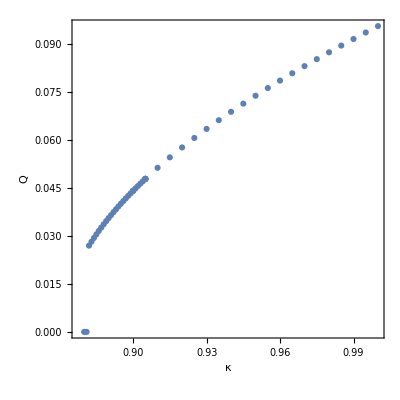

changing κ T=0.005 L=20 J=1

```mathematica
data
```

{{1.,{1.20424,1.09082,0.369366,0.0624745,-0.229056+0. ⅈ,-1.08841}},{0.995,{1.19699,1.08555,0.366581,0.0621934,-0.22959+0. ⅈ,-1.08314}},{0.99,{1.18977,1.08029,0.363794,0.061906,-0.230117+0. ⅈ,-1.07788}},{0.985,{1.18257,1.07504,0.361005,0.0616124,-0.230636+0. ⅈ,-1.07263}},{0.98,{1.17541,1.06981,0.358214,0.0613126,-0.231147+0. ⅈ,-1.06739}},{0.975,{1.16827,1.06459,0.355421,0.0610067,-0.231651+0. ⅈ,-1.06217}},{0.97,{1.16117,1.05938,0.352627,0.0606947,-0.232148+0. ⅈ,-1.05695}},{0.965,{1.15409,1.05418,0.34983,0.0603768,-0.232638+0. ⅈ,-1.05175}},{0.96,{1.14704,1.04899,0.34703,0.060053,-0.23312+0. ⅈ,-1.04657}},{0.955,{1.14002,1.04382,0.344229,0.0597235,-0.233595+0. ⅈ,-1.04139}},{0.95,{1.13304,1.03866,0.341424,0.0593882,-0.234063+0. ⅈ,-1.03623}},{0.945,{1.12608,1.03351,0.338617,0.0590473,-0.234523+0. ⅈ,-1.03108}},{0.94,{1.11915,1.02837,0.335807,0.0587008,-0.234977+0. ⅈ,-1.02594}},{0.935,{1.11226,1.02325,0.332994,0.0583488,-0.235423+0. ⅈ,-1.02082}},{0.93,{1.10539,1.01814,0.330178,0.0579914,-0.235863+0. ⅈ,-1.0157}},{0.925,{1.09856,1.01304,0.327359,0.0576288,-0.236296+0. ⅈ,-1.0106}},{0.92,{1.09175,1.00795,0.324536,0.0572608,-0.236721+0. ⅈ,-1.00551}},{0.915,{1.08498,1.00288,0.321709,0.0568878,-0.23714+0. ⅈ,-1.00044}},{0.91,{1.07824,0.997819,0.318879,0.0565096,-0.237552+0. ⅈ,-0.995377}},{0.905,{1.07152,0.99277,0.316044,0.0561265,-0.237958+0. ⅈ,-0.990326}},{0.9,{1.06484,0.987733,0.313206,0.0557384,-0.238357+0. ⅈ,-0.985288}},{0.895,{1.0582,0.982709,0.310362,0.0553456,-0.238749+0. ⅈ,-0.980263}},{0.89,{1.05158,0.977698,0.307514,0.054948,-0.239134+0. ⅈ,-0.975251}},{0.885,{1.04499,0.972699,0.304662,0.0545457,-0.239513+0. ⅈ,-0.97025}},{0.88,{1.03844,0.967712,0.301804,0.0541389,-0.239886+0. ⅈ,-0.965263}},{0.875,{1.03192,0.962739,0.29894,0.0537276,-0.240252+0. ⅈ,-0.960288}},{0.87,{1.02543,0.957777,0.296071,0.0533119,-0.240612+0. ⅈ,-0.955326}},{0.865,{1.01897,0.952828,0.293196,0.0528919,-0.240965+0. ⅈ,-0.950376}},{0.86,{1.01254,0.947892,0.290315,0.0524677,-0.241312+0. ⅈ,-0.945439}},{0.855,{1.00615,0.942968,0.287427,0.0520393,-0.241653+0. ⅈ,-0.940514}},{0.85,{0.999784,0.938057,0.284532,0.0516069,-0.241988+0. ⅈ,-0.935602}},{0.845,{0.993452,0.933159,0.28163,0.0511705,-0.242317+0. ⅈ,-0.930703}},{0.84,{0.987153,0.928273,0.278721,0.0507302,-0.24264+0. ⅈ,-0.925816}},{0.835,{0.980885,0.923399,0.275804,0.0502862,-0.242956+0. ⅈ,-0.920942}},{0.83,{0.974649,0.918538,0.272878,0.0498384,-0.243267+0. ⅈ,-0.91608}},{0.825,{0.968445,0.91369,0.269944,0.049387,-0.243572+0. ⅈ,-0.911232}},{0.82,{0.962273,0.908854,0.267001,0.0489321,-0.243871+0. ⅈ,-0.906395}},{0.815,{0.956132,0.904031,0.264049,0.0484738,-0.244165+0. ⅈ,-0.901572}},{0.81,{0.950023,0.89922,0.261086,0.048012,-0.244452+0. ⅈ,-0.89676}},{0.805,{0.943946,0.894422,0.258113,0.047547,-0.244734+0. ⅈ,-0.891962}},{0.8,{0.937901,0.889636,0.25513,0.0470788,-0.24501+0. ⅈ,-0.887176}},{0.795,{0.931887,0.884863,0.252134,0.0466075,-0.245281+0. ⅈ,-0.882402}},{0.79,{0.925905,0.880102,0.249127,0.0461332,-0.245546+0. ⅈ,-0.877641}},{0.785,{0.919954,0.875354,0.246107,0.0456559,-0.245806+0. ⅈ,-0.872893}},{0.78,{0.914034,0.870618,0.243075,0.0451758,-0.246061+0. ⅈ,-0.868157}},{0.775,{0.908146,0.865894,0.240028,0.0446929,-0.24631+0. ⅈ,-0.863434}},{0.77,{0.902289,0.861183,0.236967,0.0442073,-0.246553+0. ⅈ,-0.858723}},{0.765,{0.896463,0.856485,0.23389,0.0437191,-0.246792+0. ⅈ,-0.854024}},{0.76,{0.890668,0.851798,0.230798,0.0432283,-0.247025+0. ⅈ,-0.849338}},{0.755,{0.884904,0.847124,0.227689,0.0427351,-0.247253+0. ⅈ,-0.844665}},{0.75,{0.879171,0.842463,0.224562,0.0422395,-0.247476+0. ⅈ,-0.840004}},{0.745,{0.873469,0.837813,0.221417,0.0417415,-0.247694+0. ⅈ,-0.835355}},{0.74,{0.867797,0.833176,0.218253,0.0412414,-0.247906+0. ⅈ,-0.830718}},{0.735,{0.862155,0.828551,0.215067,0.0407391,-0.248114+0. ⅈ,-0.826094}},{0.73,{0.856544,0.823938,0.211861,0.0402347,-0.248316+0. ⅈ,-0.821482}},{0.725,{0.850963,0.819338,0.208631,0.0397282,-0.248514+0. ⅈ,-0.816882}},{0.72,{0.845412,0.814749,0.205378,0.0392199,-0.248707+0. ⅈ,-0.812294}},{0.715,{0.839891,0.810173,0.2021,0.0387096,-0.248894+0. ⅈ,-0.807719}},{0.71,{0.8344,0.805608,0.198794,0.0381975,-0.249077+0. ⅈ,-0.803155}},{0.705,{0.828938,0.801055,0.195461,0.0376837,-0.249255+0. ⅈ,-0.798604}},{0.7,{0.823506,0.796515,0.192098,0.0371681,-0.249428+0. ⅈ,-0.794064}},{0.695,{0.818103,0.791986,0.188703,0.0366509,-0.249596+0. ⅈ,-0.789537}},{0.69,{0.812729,0.787468,0.185274,0.0361321,-0.24976+0. ⅈ,-0.785021}},{0.685,{0.807384,0.782963,0.181811,0.0356117,-0.249918+0. ⅈ,-0.780517}},{0.68,{0.802067,0.778469,0.178309,0.0350899,-0.250071+0. ⅈ,-0.776025}},{0.675,{0.79678,0.773986,0.174767,0.0345666,-0.25022+0. ⅈ,-0.771544}},{0.67,{0.79152,0.769515,0.171182,0.0340419,-0.250363+0. ⅈ,-0.767075}},{0.665,{0.786288,0.765056,0.167552,0.0335157,-0.250502+0. ⅈ,-0.762617}},{0.66,{0.781084,0.760607,0.163873,0.0329883,-0.250635+0. ⅈ,-0.758171}},{0.655,{0.775908,0.75617,0.160141,0.0324595,-0.250763+0. ⅈ,-0.753736}},{0.65,{0.770759,0.751744,0.156352,0.0319294,-0.250886+0. ⅈ,-0.749312}},{0.645,{0.765638,0.747328,0.152503,0.0313979,-0.251004+0. ⅈ,-0.744899}},{0.64,{0.760543,0.742924,0.148589,0.0308652,-0.251117+0. ⅈ,-0.740498}},{0.635,{0.755474,0.73853,0.144603,0.0303312,-0.251223+0. ⅈ,-0.736106}},{0.63,{0.750432,0.734147,0.14054,0.0297959,-0.251325+0. ⅈ,-0.731726}},{0.625,{0.745416,0.729774,0.136393,0.0292592,-0.25142+0. ⅈ,-0.727356}},{0.62,{0.740425,0.725412,0.132154,0.0287212,-0.251509+0. ⅈ,-0.722997}},{0.615,{0.73546,0.721059,0.127813,0.0281818,-0.251593+0. ⅈ,-0.718648}},{0.61,{0.73052,0.716717,0.12336,0.0276409,-0.251669+0. ⅈ,-0.714309}},{0.605,{0.725603,0.712384,0.118783,0.0270985,-0.251739+0. ⅈ,-0.70998}},{0.6,{0.720711,0.708061,0.114065,0.0265543,-0.251802+0. ⅈ,-0.70566}},{0.595,{0.715842,0.703747,0.10919,0.0260085,-0.251857+0. ⅈ,-0.70135}},{0.59,{0.710997,0.699442,0.104136,0.0254607,-0.251905+0. ⅈ,-0.69705}},{0.585,{0.706173,0.695145,0.0988736,0.0249107,-0.251944+0. ⅈ,-0.692758}},{0.58,{0.701371,0.690857,0.0933701,0.0243585,-0.251973+0. ⅈ,-0.688475}},{0.575,{0.69659,0.686577,0.0875799,0.0238035,-0.251993+0. ⅈ,-0.6842}},{0.57,{0.691829,0.682305,0.0814428,0.0232457,-0.252002+0. ⅈ,-0.679933}}}

```mathematica
data
```

{{0.54,{0.562565,0.562015,0.0903105,-8.77118×10^-11,4.55748×10^-9+0. ⅈ,-0.561265}},{0.545,{0.567334,0.566715,0.09598,-8.77118×10^-11,4.55748×10^-9+0. ⅈ,-0.565988}},{0.55,{0.572119,0.571431,0.101389,-8.77118×10^-11,4.55748×10^-9+0. ⅈ,-0.570727}},{0.555,{0.57692,0.576163,0.106566,-8.77118×10^-11,4.55748×10^-9+0. ⅈ,-0.575482}},{0.56,{0.581738,0.580912,0.111543,-8.77118×10^-11,4.55748×10^-9+0. ⅈ,-0.580254}},{0.565,{0.586574,0.585678,0.116346,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.585043}},{0.57,{0.591426,0.590461,0.120995,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.589848}},{0.575,{0.596295,0.595261,0.125508,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.594671}},{0.58,{0.601182,0.600079,0.1299,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.599511}},{0.585,{0.606086,0.604913,0.134182,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.604369}},{0.59,{0.611008,0.609766,0.138364,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.609244}},{0.595,{0.615947,0.614635,0.142456,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.614136}},{0.6,{0.620904,0.619523,0.146465,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.619046}},{0.605,{0.62588,0.624429,0.150398,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.623975}},{0.61,{0.630873,0.629352,0.15426,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.628921}},{0.615,{0.635885,0.634294,0.158058,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.633886}},{0.62,{0.640915,0.639255,0.161796,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.638869}},{0.625,{0.645964,0.644233,0.165477,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.64387}},{0.63,{0.651032,0.649231,0.169107,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.648891}},{0.635,{0.656118,0.654247,0.172687,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.65393}},{0.64,{0.661224,0.659283,0.176221,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.658988}},{0.645,{0.666349,0.664338,0.179713,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.664065}},{0.65,{0.671494,0.669412,0.183164,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.669162}},{0.655,{0.676658,0.674505,0.186577,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.674278}},{0.66,{0.681842,0.679618,0.189954,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.679414}},{0.665,{0.687046,0.684752,0.193297,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.68457}},{0.67,{0.69227,0.689905,0.196608,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.689746}},{0.675,{0.697515,0.695078,0.199888,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.694942}},{0.68,{0.70278,0.700272,0.20314,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.700159}},{0.685,{0.708066,0.705487,0.206364,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.705396}},{0.69,{0.713372,0.710722,0.209562,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.710654}},{0.695,{0.7187,0.715979,0.212735,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.715933}},{0.7,{0.724049,0.721256,0.215885,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.721233}},{0.705,{0.72942,0.726555,0.219012,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.726555}},{0.71,{0.734813,0.731876,0.222117,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.731898}},{0.715,{0.740227,0.737218,0.225203,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.737263}},{0.72,{0.745663,0.742582,0.228268,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.74265}},{0.725,{0.751122,0.747969,0.231315,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.74806}},{0.73,{0.756604,0.753378,0.234344,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.753491}},{0.735,{0.762108,0.758809,0.237356,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.758946}},{0.74,{0.767635,0.764264,0.240352,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.764423}},{0.745,{0.773186,0.769741,0.243332,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.769923}},{0.75,{0.77876,0.775242,0.246296,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.775446}},{0.755,{0.784357,0.780766,0.249247,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.780993}},{0.76,{0.789979,0.786314,0.252184,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.786564}},{0.765,{0.795624,0.791886,0.255107,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.792158}},{0.77,{0.801294,0.797482,0.258018,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.797777}},{0.775,{0.806989,0.803103,0.260916,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.80342}},{0.78,{0.812708,0.808748,0.263803,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.809088}},{0.785,{0.818452,0.814418,0.266679,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.814781}},{0.79,{0.824222,0.820113,0.269544,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.820499}},{0.795,{0.830017,0.825834,0.272398,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.826242}},{0.8,{0.835838,0.83158,0.275243,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.832011}},{0.805,{0.841685,0.837352,0.278078,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.837805}},{0.81,{0.847559,0.84315,0.280903,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.843626}},{0.815,{0.853458,0.848974,0.28372,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.849473}},{0.82,{0.859385,0.854825,0.286529,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.855347}},{0.825,{0.865339,0.860703,0.289329,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.861247}},{0.83,{0.87132,0.866607,0.292122,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.867175}},{0.835,{0.877329,0.87254,0.294907,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.87313}},{0.84,{0.883365,0.878499,0.297685,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.879112}},{0.845,{0.88943,0.884487,0.300455,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.885123}},{0.85,{0.895523,0.890503,0.30322,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.891162}},{0.855,{0.901644,0.896547,0.305978,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.897228}},{0.86,{0.907795,0.90262,0.308729,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.903324}},{0.865,{0.913975,0.908722,0.311475,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.909449}},{0.87,{0.920184,0.914853,0.314216,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.915603}},{0.875,{0.926423,0.921013,0.31695,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.921786}},{0.88,{0.932692,0.927204,0.31968,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.927999}},{0.885,{0.938991,0.933424,0.322405,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.934242}},{0.89,{0.945321,0.939674,0.325125,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.940515}},{0.895,{0.951682,0.945955,0.32784,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.946819}},{0.9,{0.958074,0.952267,0.330551,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.953154}},{0.905,{0.964497,0.958611,0.333258,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.95952}},{0.91,{0.970952,0.964985,0.335961,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.965917}},{0.915,{0.97744,0.971391,0.338661,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.972347}},{0.92,{0.983959,0.97783,0.341356,8.26466×10^-12,-3.75021×10^-10+0. ⅈ,-0.978808}},{0.925,{0.990511,0.9843,0.344049,-1.13056×10^-11,5.55102×10^-10+0. ⅈ,-0.985301}},{0.93,{0.997097,0.990804,0.346738,-8.25429×10^-12,8.03289×10^-11+0. ⅈ,-0.991828}},{0.935,{1.00372,0.99734,0.349424,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-0.998387}},{0.94,{1.01037,1.00391,0.352107,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.00498}},{0.945,{1.01705,1.01051,0.354787,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.01161}},{0.95,{1.02377,1.01715,0.357464,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.01827}},{0.955,{1.03053,1.02382,0.360139,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.02496}},{0.96,{1.03732,1.03053,0.362812,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.03169}},{0.965,{1.04415,1.03727,0.365483,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.03846}},{0.97,{1.05101,1.04405,0.368151,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.04526}},{0.975,{1.05792,1.05087,0.370818,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.0521}},{0.98,{1.06486,1.05772,0.373483,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.05898}},{0.985,{1.07184,1.06462,0.376146,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.06589}},{0.99,{1.07886,1.07155,0.378808,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.07285}},{0.995,{1.08592,1.07853,0.381468,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.07985}},{1.,{1.09302,1.08554,0.384127,-2.24475×10^-12,5.51353×10^-11+0. ⅈ,-1.08689}}}

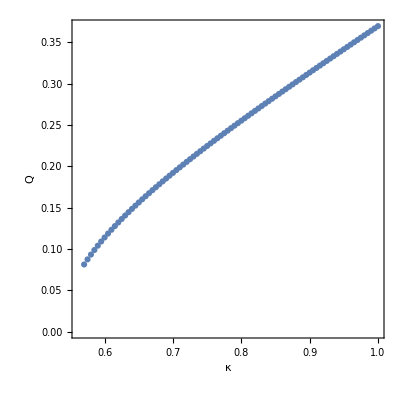
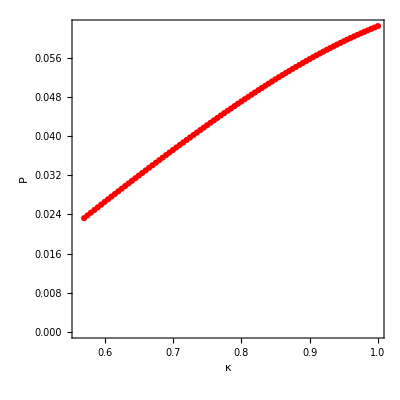
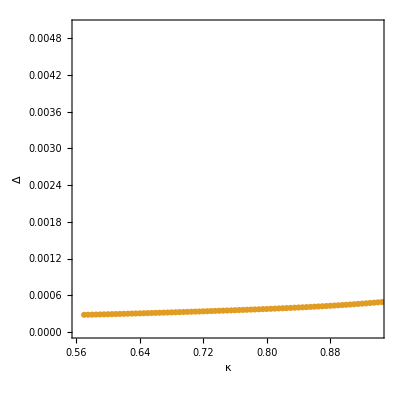
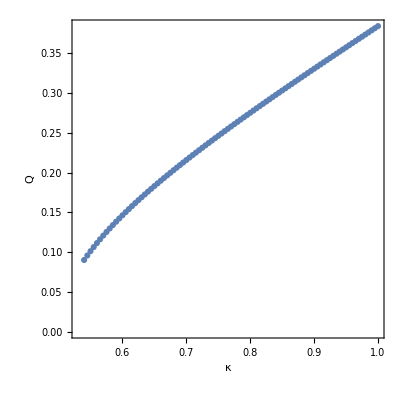
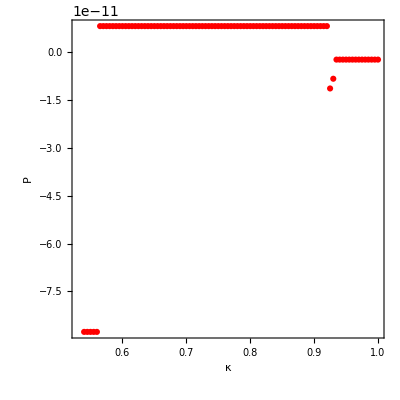
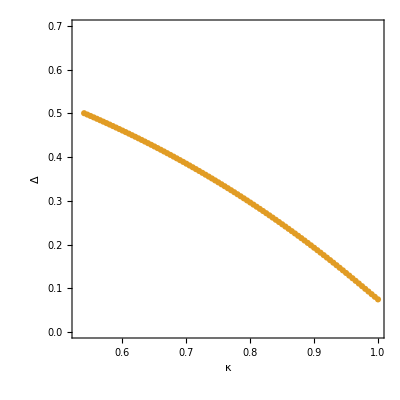

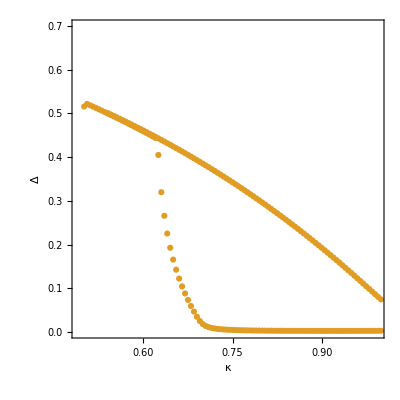

```mathematica
Show[-Graphics-,-Graphics-]
```

changing κ T=0.02 L=20 J=2

```mathematica
data
```

{{1.,{2.2607,2.14908,0.76219,0.0568057,-0.215287+0. ⅈ,-2.14531}},{0.995,{2.24565,2.13629,0.756834,0.0564678,-0.215904+0. ⅈ,-2.1325}},{0.99,{2.23067,2.12356,0.751477,0.0561216,-0.216506+0. ⅈ,-2.11976}},{0.985,{2.2158,2.1109,0.746119,0.0557689,-0.217094+0. ⅈ,-2.10709}},{0.98,{2.20101,2.09831,0.740758,0.0554103,-0.217667+0. ⅈ,-2.09448}},{0.975,{2.18633,2.08579,0.735395,0.0550459,-0.218226+0. ⅈ,-2.08195}},{0.97,{2.17174,2.07334,0.730029,0.0546756,-0.21877+0. ⅈ,-2.06949}},{0.965,{2.15724,2.06096,0.724659,0.0542995,-0.2193+0. ⅈ,-2.0571}},{0.96,{2.14283,2.04864,0.719287,0.0539173,-0.219816+0. ⅈ,-2.04477}},{0.955,{2.12851,2.03638,0.713911,0.0535289,-0.220317+0. ⅈ,-2.03251}},{0.95,{2.11427,2.02419,0.708531,0.0531342,-0.220804+0. ⅈ,-2.02031}},{0.945,{2.10012,2.01205,0.703148,0.052733,-0.221275+0. ⅈ,-2.00817}},{0.94,{2.08605,1.99997,0.69776,0.0523253,-0.221731+0. ⅈ,-1.99609}},{0.935,{2.07205,1.98795,0.692368,0.051911,-0.222172+0. ⅈ,-1.98407}},{0.93,{2.05813,1.97598,0.686971,0.0514908,-0.222598+0. ⅈ,-1.9721}},{0.925,{2.0443,1.96407,0.681569,0.0510624,-0.223005+0. ⅈ,-1.96018}},{0.92,{2.03053,1.9522,0.676162,0.0506281,-0.223396+0. ⅈ,-1.94832}},{0.915,{2.01684,1.94039,0.67075,0.050187,-0.223771+0. ⅈ,-1.93651}},{0.91,{2.00322,1.92863,0.665331,0.0497392,-0.224129+0. ⅈ,-1.92476}},{0.905,{1.98967,1.91692,0.659906,0.0492847,-0.224468+0. ⅈ,-1.91305}},{0.9,{1.9762,1.90525,0.654475,0.0488234,-0.224789+0. ⅈ,-1.90139}},{0.895,{1.9628,1.89363,0.649037,0.0483554,-0.225091+0. ⅈ,-1.88978}},{0.89,{1.94946,1.88206,0.643592,0.0478806,-0.225373+0. ⅈ,-1.87822}},{0.885,{1.9362,1.87054,0.63814,0.047399,-0.225635+0. ⅈ,-1.86671}},{0.88,{1.923,1.85905,0.632679,0.0469106,-0.225876+0. ⅈ,-1.85524}},{0.875,{1.90987,1.84762,0.627211,0.0464153,-0.226095+0. ⅈ,-1.84381}},{0.87,{1.89681,1.83622,0.621734,0.0459138,-0.226294+0. ⅈ,-1.83243}},{0.865,{1.88381,1.82487,0.616248,0.0454043,-0.226465+0. ⅈ,-1.82109}},{0.86,{1.87088,1.81356,0.610752,0.0448884,-0.226613+0. ⅈ,-1.8098}},{0.855,{1.85801,1.80229,0.605247,0.0443656,-0.226736+0. ⅈ,-1.79855}},{0.85,{1.8452,1.79105,0.599732,0.0438357,-0.226833+0. ⅈ,-1.78733}},{0.845,{1.83246,1.77986,0.594206,0.0432988,-0.226901+0. ⅈ,-1.77616}},{0.84,{1.81978,1.7687,0.588669,0.0427547,-0.22694+0. ⅈ,-1.76502}},{0.835,{1.80716,1.75758,0.583121,0.0422035,-0.226948+0. ⅈ,-1.75393}},{0.83,{1.79459,1.7465,0.57756,0.0416449,-0.226924+0. ⅈ,-1.74287}},{0.825,{1.78209,1.73545,0.571988,0.041079,-0.226865+0. ⅈ,-1.73184}},{0.82,{1.76964,1.72443,0.566402,0.0405055,-0.226771+0. ⅈ,-1.72085}},{0.815,{1.75725,1.71344,0.560803,0.0399245,-0.226638+0. ⅈ,-1.70989}},{0.81,{1.74491,1.70249,0.555189,0.0393358,-0.226465+0. ⅈ,-1.69897}},{0.805,{1.73262,1.69156,0.549562,0.0387392,-0.226249+0. ⅈ,-1.68807}},{0.8,{1.72039,1.68067,0.543919,0.0381345,-0.225987+0. ⅈ,-1.6772}},{0.795,{1.7082,1.6698,0.53826,0.0375217,-0.225676+0. ⅈ,-1.66637}},{0.79,{1.69607,1.65895,0.532585,0.0369005,-0.225313+0. ⅈ,-1.65556}},{0.785,{1.68398,1.64813,0.526894,0.0362706,-0.224895+0. ⅈ,-1.64477}},{0.78,{1.67194,1.63733,0.521184,0.035632,-0.224416+0. ⅈ,-1.63401}},{0.775,{1.65993,1.62655,0.515457,0.0349842,-0.223873+0. ⅈ,-1.62327}},{0.77,{1.64797,1.61579,0.50971,0.034327,-0.22326+0. ⅈ,-1.61255}},{0.765,{1.63605,1.60505,0.503944,0.0336601,-0.222572+0. ⅈ,-1.60184}},{0.76,{1.62417,1.59432,0.498157,0.0329831,-0.221802+0. ⅈ,-1.59115}},{0.755,{1.61231,1.5836,0.49235,0.0322955,-0.220944+0. ⅈ,-1.58048}},{0.75,{1.60049,1.57289,0.48652,0.0315971,-0.219989+0. ⅈ,-1.56981}},{0.745,{1.5887,1.56219,0.480668,0.0308871,-0.218929+0. ⅈ,-1.55915}},{0.74,{1.57693,1.55148,0.474792,0.0301652,-0.217753+0. ⅈ,-1.5485}},{0.735,{1.56518,1.54078,0.468891,0.0294305,-0.21645+0. ⅈ,-1.53784}},{0.73,{1.55345,1.53007,0.462966,0.0286824,-0.215008+0. ⅈ,-1.52719}},{0.725,{1.54173,1.51935,0.457014,0.0279201,-0.213411+0. ⅈ,-1.51652}},{0.72,{1.53002,1.50862,0.451034,0.0271427,-0.211643+0. ⅈ,-1.50584}},{0.715,{1.5183,1.49786,0.445027,0.0263489,-0.209683+0. ⅈ,-1.49514}},{0.71,{1.50659,1.48708,0.43899,0.0255377,-0.20751+0. ⅈ,-1.48442}},{0.705,{1.49486,1.47627,0.432923,0.0247075,-0.205098+0. ⅈ,-1.47366}},{0.7,{1.48311,1.46541,0.426825,0.0238568,-0.202415+0. ⅈ,-1.46287}},{0.695,{1.47134,1.45451,0.420695,0.0229834,-0.199426+0. ⅈ,-1.45202}},{0.69,{1.45953,1.44355,0.414531,0.0220851,-0.196088+0. ⅈ,-1.44112}},{0.685,{1.44767,1.43252,0.408332,0.021159,-0.192349+0. ⅈ,-1.43016}},{0.68,{1.43575,1.4214,0.402097,0.0202017,-0.188147+0. ⅈ,-1.41911}},{0.675,{1.42375,1.41019,0.395825,0.0192089,-0.183404+0. ⅈ,-1.40796}},{0.67,{1.41166,1.39886,0.389516,0.0181752,-0.178027+0. ⅈ,-1.3967}},{0.665,{1.39947,1.38741,0.383166,0.0170937,-0.171892+0. ⅈ,-1.38532}},{0.66,{1.38714,1.3758,0.376777,0.0159552,-0.164841+0. ⅈ,-1.37378}},{0.655,{1.37466,1.36401,0.370345,0.0147472,-0.156662+0. ⅈ,-1.36206}},{0.65,{1.362,1.35202,0.363871,0.0134516,-0.147058+0. ⅈ,-1.35015}},{0.645,{1.34912,1.33979,0.357353,0.012041,-0.135588+0. ⅈ,-1.33799}},{0.64,{1.33599,1.32728,0.35079,0.0104702,-0.121554+0. ⅈ,-1.32556}},{0.635,{1.32257,1.31446,0.344181,0.00865408,-0.103688+0. ⅈ,-1.31281}},{0.63,{1.30879,1.30126,0.337526,0.00639304,-0.0791376+0. ⅈ,-1.29969}},{0.625,{1.29461,1.28763,0.330823,0.00272202,-0.0348476+0. ⅈ,-1.28614}},{0.62,{1.28347,1.27683,0.323594,0.000062926,-0.000813402+0. ⅈ,-1.27529}},{0.615,{1.27336,1.267,0.316117,7.00549×10^-7,-9.03199×10^-6+0. ⅈ,-1.26536}},{0.61,{1.26327,1.25718,0.308521,2.30438×10^-9,-2.97682×10^-8+0. ⅈ,-1.25546}},{0.605,{1.25321,1.24741,0.300796,2.76858×10^-9,-3.57541×10^-8+0. ⅈ,-1.24559}},{0.6,{1.24319,1.23766,0.29293,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.23576}},{0.595,{1.23321,1.22796,0.284912,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.22596}},{0.59,{1.22326,1.21829,0.276729,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.2162}},{0.585,{1.21334,1.20865,0.268363,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.20648}},{0.58,{1.20347,1.19905,0.2598,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.19678}},{0.575,{1.19362,1.18949,0.251017,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.18713}},{0.57,{1.18382,1.17996,0.24199,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.17751}},{0.565,{1.17404,1.17046,0.232691,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.16792}},{0.56,{1.1643,1.161,0.223088,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.15837}},{0.555,{1.1546,1.15157,0.213132,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.14884}},{0.55,{1.14493,1.14217,0.202778,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.13936}},{0.545,{1.13529,1.13281,0.19196,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.1299}},{0.54,{1.12568,1.12348,0.180593,-1.44703×10^-10,1.87078×10^-9+0. ⅈ,-1.12048}},{0.535,{1.11611,1.11418,0.168565,-4.19855×10^-10,5.47372×10^-9+0. ⅈ,-1.11109}},{0.53,{1.10657,1.10492,0.155725,-1.05394×10^-10,1.36918×10^-9+0. ⅈ,-1.10174}},{0.525,{1.09706,1.09569,0.141851,-1.05394×10^-10,1.36918×10^-9+0. ⅈ,-1.09242}},{0.52,{1.08758,1.08648,0.126601,-1.05394×10^-10,1.36918×10^-9+0. ⅈ,-1.08312}},{0.515,{1.07814,1.07731,0.109405,-1.05394×10^-10,1.36918×10^-9+0. ⅈ,-1.07386}},{0.51,{1.06872,1.06817,0.089139,-1.05394×10^-10,1.36918×10^-9+0. ⅈ,-1.06462}},{0.505,{1.05935,1.05907,0.062888,1.21868×10^-11,2.43317×10^-10+0. ⅈ,-1.05544}},{0.5,{1.05416,1.05416,0.00275818,1.21868×10^-11,-1.63124×10^-10+0. ⅈ,-1.05043}}}

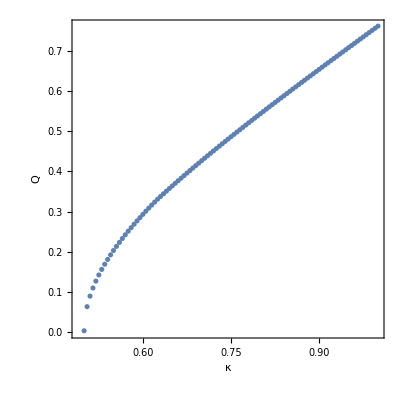
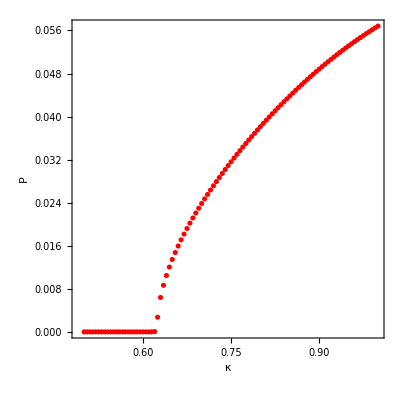
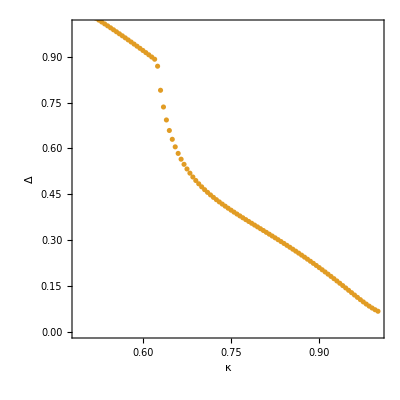

changing κ T=0.005 L=20 J=2

```mathematica
data
```

{{1.,{2.26847,2.14459,0.761769,0.0587153,-0.222132+0. ⅈ,-2.14226}},{0.995,{2.2534,2.13189,0.756409,0.0583757,-0.222797+0. ⅈ,-2.12955}},{0.99,{2.23841,2.11925,0.751047,0.0580296,-0.223451+0. ⅈ,-2.11691}},{0.985,{2.22352,2.10668,0.745683,0.0576779,-0.224098+0. ⅈ,-2.10434}},{0.98,{2.20873,2.09418,0.740317,0.0573189,-0.224732+0. ⅈ,-2.09183}},{0.975,{2.19402,2.08174,0.734948,0.0569551,-0.225359+0. ⅈ,-2.0794}},{0.97,{2.17942,2.06938,0.729576,0.0565857,-0.225976+0. ⅈ,-2.06703}},{0.965,{2.1649,2.05708,0.7242,0.0562108,-0.226585+0. ⅈ,-2.05473}},{0.96,{2.15048,2.04485,0.718822,0.0558304,-0.227184+0. ⅈ,-2.04249}},{0.955,{2.13614,2.03268,0.71344,0.0554451,-0.227777+0. ⅈ,-2.03032}},{0.95,{2.12189,2.02057,0.708053,0.0550531,-0.228357+0. ⅈ,-2.01821}},{0.945,{2.10773,2.00852,0.702663,0.0546561,-0.22893+0. ⅈ,-2.00616}},{0.94,{2.09364,1.99653,0.697268,0.0542537,-0.229495+0. ⅈ,-1.99417}},{0.935,{2.07964,1.9846,0.691868,0.0538453,-0.230051+0. ⅈ,-1.98224}},{0.93,{2.06572,1.97273,0.686463,0.0534315,-0.230599+0. ⅈ,-1.97037}},{0.925,{2.05188,1.96091,0.681052,0.0530122,-0.231138+0. ⅈ,-1.95855}},{0.92,{2.03812,1.94915,0.675636,0.0525874,-0.231669+0. ⅈ,-1.94678}},{0.915,{2.02443,1.93743,0.670214,0.052157,-0.232192+0. ⅈ,-1.93507}},{0.91,{2.01082,1.92578,0.664786,0.0517212,-0.232707+0. ⅈ,-1.92341}},{0.905,{1.99729,1.91417,0.65935,0.0512799,-0.233214+0. ⅈ,-1.9118}},{0.9,{1.98383,1.90261,0.653908,0.0508333,-0.233713+0. ⅈ,-1.90024}},{0.895,{1.97045,1.89111,0.648459,0.0503813,-0.234204+0. ⅈ,-1.88874}},{0.89,{1.95713,1.87966,0.643001,0.049924,-0.234687+0. ⅈ,-1.87728}},{0.885,{1.9439,1.86825,0.637536,0.0494615,-0.235163+0. ⅈ,-1.86588}},{0.88,{1.93073,1.8569,0.632061,0.0489938,-0.235631+0. ⅈ,-1.85452}},{0.875,{1.91763,1.84559,0.626578,0.0485209,-0.236091+0. ⅈ,-1.84322}},{0.87,{1.90461,1.83433,0.621086,0.048043,-0.236544+0. ⅈ,-1.83196}},{0.865,{1.89166,1.82312,0.615584,0.0475599,-0.236989+0. ⅈ,-1.82075}},{0.86,{1.87877,1.81196,0.610071,0.0470719,-0.237427+0. ⅈ,-1.80958}},{0.855,{1.86596,1.80084,0.604548,0.0465794,-0.237859+0. ⅈ,-1.79846}},{0.85,{1.85321,1.78977,0.599013,0.0460808,-0.238281+0. ⅈ,-1.78739}},{0.845,{1.84053,1.77874,0.593467,0.0455779,-0.238698+0. ⅈ,-1.77637}},{0.84,{1.82792,1.76776,0.587909,0.0450701,-0.239107+0. ⅈ,-1.76539}},{0.835,{1.81538,1.75683,0.582338,0.0445575,-0.239508+0. ⅈ,-1.75445}},{0.83,{1.80291,1.74594,0.576754,0.0440401,-0.239903+0. ⅈ,-1.74356}},{0.825,{1.7905,1.73509,0.571155,0.043518,-0.240291+0. ⅈ,-1.73272}},{0.82,{1.77815,1.72429,0.565543,0.0429911,-0.240672+0. ⅈ,-1.72191}},{0.815,{1.76587,1.71353,0.559915,0.0424595,-0.241046+0. ⅈ,-1.71115}},{0.81,{1.75366,1.70281,0.554271,0.0419232,-0.241413+0. ⅈ,-1.70044}},{0.805,{1.74151,1.69213,0.548612,0.0413823,-0.241773+0. ⅈ,-1.68976}},{0.8,{1.72942,1.6815,0.542935,0.0408367,-0.242126+0. ⅈ,-1.67913}},{0.795,{1.7174,1.67091,0.53724,0.0402866,-0.242473+0. ⅈ,-1.66854}},{0.79,{1.70544,1.66035,0.531527,0.0397318,-0.242812+0. ⅈ,-1.65799}},{0.785,{1.69354,1.64984,0.525794,0.0391725,-0.243145+0. ⅈ,-1.64748}},{0.78,{1.6817,1.63937,0.520042,0.0386087,-0.243471+0. ⅈ,-1.63701}},{0.775,{1.66993,1.62894,0.514268,0.0380403,-0.243791+0. ⅈ,-1.62658}},{0.77,{1.65821,1.61855,0.508473,0.0374675,-0.244103+0. ⅈ,-1.61618}},{0.765,{1.64656,1.60819,0.502654,0.0368901,-0.244409+0. ⅈ,-1.60583}},{0.76,{1.63496,1.59788,0.496812,0.0363083,-0.244708+0. ⅈ,-1.59552}},{0.755,{1.62343,1.5876,0.490945,0.035722,-0.245+0. ⅈ,-1.58524}},{0.75,{1.61195,1.57736,0.485052,0.0351312,-0.245285+0. ⅈ,-1.57501}},{0.745,{1.60053,1.56716,0.479133,0.0345359,-0.245563+0. ⅈ,-1.56481}},{0.74,{1.58917,1.55699,0.473184,0.0339362,-0.245834+0. ⅈ,-1.55464}},{0.735,{1.57787,1.54686,0.467207,0.033332,-0.246098+0. ⅈ,-1.54452}},{0.73,{1.56662,1.53677,0.461198,0.0327234,-0.246355+0. ⅈ,-1.53443}},{0.725,{1.55543,1.52671,0.455158,0.0321102,-0.246604+0. ⅈ,-1.52437}},{0.72,{1.5443,1.51669,0.449083,0.0314927,-0.246845+0. ⅈ,-1.51436}},{0.715,{1.53322,1.5067,0.442974,0.0308706,-0.247079+0. ⅈ,-1.50437}},{0.71,{1.5222,1.49674,0.436827,0.030244,-0.247304+0. ⅈ,-1.49442}},{0.705,{1.51123,1.48682,0.430642,0.0296129,-0.247521+0. ⅈ,-1.48451}},{0.7,{1.50032,1.47694,0.424416,0.0289773,-0.247729+0. ⅈ,-1.47463}},{0.695,{1.48946,1.46708,0.418148,0.0283371,-0.247928+0. ⅈ,-1.46478}},{0.69,{1.47865,1.45726,0.411835,0.0276923,-0.248117+0. ⅈ,-1.45496}},{0.685,{1.4679,1.44747,0.405476,0.0270428,-0.248296+0. ⅈ,-1.44518}},{0.68,{1.4572,1.43771,0.399067,0.0263887,-0.248464+0. ⅈ,-1.43543}},{0.675,{1.44655,1.42798,0.392606,0.0257299,-0.248619+0. ⅈ,-1.42571}},{0.67,{1.43595,1.41828,0.386091,0.0250663,-0.248762+0. ⅈ,-1.41602}},{0.665,{1.4254,1.40861,0.379518,0.0243979,-0.24889+0. ⅈ,-1.40636}},{0.66,{1.4149,1.39897,0.372884,0.0237245,-0.249003+0. ⅈ,-1.39672}},{0.655,{1.40444,1.38935,0.366186,0.0230462,-0.249097+0. ⅈ,-1.38712}},{0.65,{1.39403,1.37976,0.35942,0.0223627,-0.249173+0. ⅈ,-1.37754}},{0.645,{1.38367,1.3702,0.352583,0.0216741,-0.249225+0. ⅈ,-1.36799}},{0.64,{1.37335,1.36066,0.345668,0.0209801,-0.249253+0. ⅈ,-1.35846}},{0.635,{1.36307,1.35114,0.338673,0.0202806,-0.24925+0. ⅈ,-1.34895}},{0.63,{1.35284,1.34164,0.331591,0.0195755,-0.249213+0. ⅈ,-1.33947}},{0.625,{1.34263,1.33215,0.324418,0.0188644,-0.249135+0. ⅈ,-1.33}},{0.62,{1.33246,1.32268,0.317146,0.0181472,-0.249009+0. ⅈ,-1.32055}},{0.615,{1.32232,1.31322,0.309769,0.0174235,-0.248823+0. ⅈ,-1.31111}},{0.61,{1.3122,1.30376,0.302278,0.0166929,-0.248566+0. ⅈ,-1.30168}},{0.605,{1.3021,1.2943,0.294667,0.015955,-0.248221+0. ⅈ,-1.29224}},{0.6,{1.292,1.28482,0.286925,0.0152092,-0.247765+0. ⅈ,-1.2828}},{0.595,{1.2819,1.27533,0.279042,0.0144547,-0.247169+0. ⅈ,-1.27334}},{0.59,{1.27177,1.26579,0.271006,0.0136906,-0.246395+0. ⅈ,-1.26384}},{0.585,{1.2616,1.25619,0.262803,0.0129158,-0.245388+0. ⅈ,-1.25429}},{0.58,{1.25136,1.24651,0.25442,0.0121286,-0.244075+0. ⅈ,-1.24465}},{0.575,{1.241,1.23669,0.245838,0.0113271,-0.242352+0. ⅈ,-1.2349}},{0.57,{1.23048,1.22669,0.237039,0.0105084,-0.240067+0. ⅈ,-1.22496}},{0.565,{1.2197,1.21642,0.228,0.00966893,-0.237+0. ⅈ,-1.21476}},{0.56,{1.20854,1.20575,0.218695,0.00880315,-0.232812+0. ⅈ,-1.20418}},{0.555,{1.19683,1.1945,0.209097,0.00790309,-0.226971+0. ⅈ,-1.19303}},{0.55,{1.18428,1.1824,0.199171,0.00695617,-0.218593+0. ⅈ,-1.18103}},{0.545,{1.17044,1.16897,0.18888,0.00594095,-0.206115+0. ⅈ,-1.16772}},{0.54,{1.15455,1.15346,0.178183,0.00481601,-0.186466+0. ⅈ,-1.15234}},{0.535,{1.13536,1.13461,0.167034,0.00347908,-0.15228+0. ⅈ,-1.13363}},{0.53,{1.11048,1.11003,0.155398,0.00143523,-0.0721722+0. ⅈ,-1.10919}},{0.525,{1.09654,1.0962,0.141849,-5.68655×10^-7,0.0000294765+0. ⅈ,-1.09538}},{0.52,{1.08717,1.0869,0.126601,-2.22425×10^-8,1.15656×10^-6+0. ⅈ,-1.08605}},{0.515,{1.07783,1.07762,0.109405,6.93835×10^-10,-3.60877×10^-8+0. ⅈ,-1.07676}},{0.51,{1.06851,1.06837,0.0891444,-2.60449×10^-9,1.35556×10^-7+0. ⅈ,-1.06749}},{0.505,{1.05918,1.05911,0.0629956,-2.53536×10^-9,1.31927×10^-7+0. ⅈ,-1.0582}},{0.5,{1.05008,1.05008,0.00199556,-3.58395×10^-9,1.86526×10^-7+0. ⅈ,-1.04914}}}

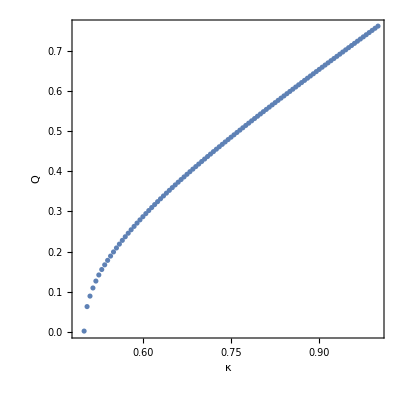
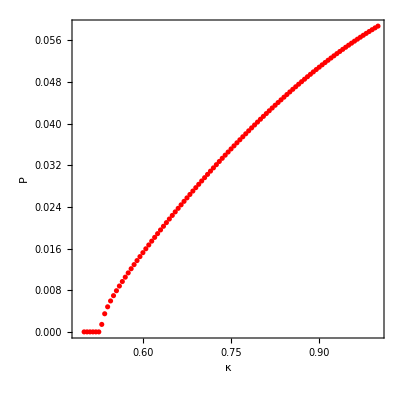
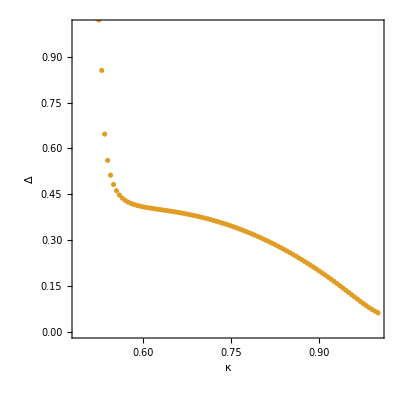

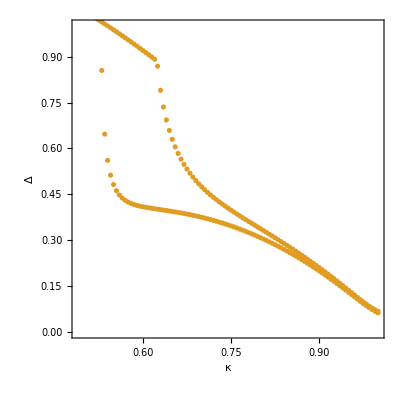

```mathematica
Show[-Graphics-,-Graphics-]
```

data T=0.02 κ=0.9

```mathematica
data
```

{{2.,{1.9762,1.90525,0.654475,0.0488234,-0.224789+0. ⅈ,-1.90139}},{1.99,{1.96678,1.89589,0.651136,0.0488232,-0.224816+0. ⅈ,-1.89203}},{1.98,{1.95736,1.88652,0.647795,0.0488255,-0.224845+0. ⅈ,-1.88266}},{1.97,{1.94795,1.87716,0.644454,0.0488248,-0.224871+0. ⅈ,-1.8733}},{1.96,{1.93854,1.86781,0.641113,0.0488256,-0.2249+0. ⅈ,-1.86393}},{1.95,{1.92912,1.85845,0.637771,0.0488263,-0.224928+0. ⅈ,-1.85457}},{1.94,{1.91971,1.8491,0.634429,0.048827,-0.224957+0. ⅈ,-1.84522}},{1.93,{1.9103,1.83974,0.631087,0.0488276,-0.224987+0. ⅈ,-1.83586}},{1.92,{1.90089,1.8304,0.627744,0.0488281,-0.225017+0. ⅈ,-1.82651}},{1.91,{1.89149,1.82105,0.624401,0.0488286,-0.225047+0. ⅈ,-1.81716}},{1.9,{1.88208,1.8117,0.621057,0.0488291,-0.225078+0. ⅈ,-1.80781}},{1.89,{1.87268,1.80236,0.617713,0.0488295,-0.225109+0. ⅈ,-1.79847}},{1.88,{1.86327,1.79302,0.614369,0.0488299,-0.225141+0. ⅈ,-1.78912}},{1.87,{1.85387,1.78369,0.611024,0.0488301,-0.225173+0. ⅈ,-1.77978}},{1.86,{1.84447,1.77435,0.607679,0.0488304,-0.225206+0. ⅈ,-1.77045}},{1.85,{1.83507,1.76502,0.604333,0.0488305,-0.225239+0. ⅈ,-1.76111}},{1.84,{1.82568,1.75569,0.600986,0.0488323,-0.225274+0. ⅈ,-1.75178}},{1.83,{1.81628,1.74637,0.59764,0.0488307,-0.225306+0. ⅈ,-1.74245}},{1.82,{1.80689,1.73704,0.594293,0.0488306,-0.225341+0. ⅈ,-1.73312}},{1.81,{1.7975,1.72772,0.590946,0.0488305,-0.225376+0. ⅈ,-1.7238}},{1.8,{1.78811,1.71841,0.587598,0.0488304,-0.225411+0. ⅈ,-1.71448}},{1.79,{1.77872,1.70909,0.584249,0.0488301,-0.225447+0. ⅈ,-1.70516}},{1.78,{1.76933,1.69978,0.5809,0.0488298,-0.225483+0. ⅈ,-1.69584}},{1.77,{1.75995,1.69047,0.577551,0.0488294,-0.22552+0. ⅈ,-1.68653}},{1.76,{1.75057,1.68117,0.574201,0.048829,-0.225558+0. ⅈ,-1.67722}},{1.75,{1.74119,1.67187,0.57085,0.0488284,-0.225596+0. ⅈ,-1.66792}},{1.74,{1.73181,1.66257,0.567499,0.0488278,-0.225635+0. ⅈ,-1.65861}},{1.73,{1.72243,1.65328,0.564147,0.0488271,-0.225674+0. ⅈ,-1.64931}},{1.72,{1.71305,1.64398,0.560795,0.0488264,-0.225714+0. ⅈ,-1.64002}},{1.71,{1.70368,1.6347,0.557443,0.0488255,-0.225754+0. ⅈ,-1.63073}},{1.7,{1.69431,1.62541,0.554089,0.0488246,-0.225795+0. ⅈ,-1.62144}},{1.69,{1.68494,1.61613,0.550735,0.0488237,-0.225837+0. ⅈ,-1.61215}},{1.68,{1.67558,1.60686,0.547381,0.0488227,-0.225879+0. ⅈ,-1.60287}},{1.67,{1.66621,1.59758,0.544026,0.0488216,-0.225922+0. ⅈ,-1.59359}},{1.66,{1.65685,1.58831,0.54067,0.0488205,-0.225966+0. ⅈ,-1.58432}},{1.65,{1.64749,1.57905,0.537313,0.0488212,-0.226011+0. ⅈ,-1.57505}},{1.64,{1.63814,1.56979,0.533957,0.0488182,-0.226055+0. ⅈ,-1.56578}},{1.63,{1.62878,1.56053,0.530599,0.0488171,-0.2261+0. ⅈ,-1.55652}},{1.62,{1.61943,1.55128,0.527241,0.048816,-0.226147+0. ⅈ,-1.54726}},{1.61,{1.61009,1.54203,0.523881,0.0488149,-0.226194+0. ⅈ,-1.53801}},{1.6,{1.60074,1.53279,0.520521,0.0488139,-0.226241+0. ⅈ,-1.52876}},{1.59,{1.5914,1.52355,0.517161,0.048813,-0.22629+0. ⅈ,-1.51952}},{1.58,{1.58206,1.51432,0.513799,0.0488123,-0.226339+0. ⅈ,-1.51028}},{1.57,{1.57273,1.50509,0.510437,0.0488117,-0.226389+0. ⅈ,-1.50104}},{1.56,{1.5634,1.49586,0.507073,0.0488114,-0.22644+0. ⅈ,-1.49181}},{1.55,{1.55407,1.48664,0.503709,0.0488115,-0.226492+0. ⅈ,-1.48259}},{1.54,{1.54475,1.47743,0.500344,0.048812,-0.226545+0. ⅈ,-1.47337}},{1.53,{1.53543,1.46822,0.496978,0.0488129,-0.226598+0. ⅈ,-1.46415}},{1.52,{1.52612,1.45902,0.49361,0.0488145,-0.226653+0. ⅈ,-1.45494}},{1.51,{1.51681,1.44982,0.490242,0.0488169,-0.226708+0. ⅈ,-1.44574}},{1.5,{1.50751,1.44063,0.486872,0.0488201,-0.226765+0. ⅈ,-1.43654}},{1.49,{1.49822,1.43144,0.483499,0.0488269,-0.226823+0. ⅈ,-1.42734}},{1.48,{1.48893,1.42226,0.480127,0.0488332,-0.226883+0. ⅈ,-1.41816}},{1.47,{1.47965,1.41309,0.476752,0.0488396,-0.226941+0. ⅈ,-1.40898}},{1.46,{1.47038,1.40392,0.473376,0.0488487,-0.227003+0. ⅈ,-1.3998}},{1.45,{1.46112,1.39476,0.469999,0.0488592,-0.227063+0. ⅈ,-1.39064}},{1.44,{1.45187,1.38561,0.466619,0.0488721,-0.227126+0. ⅈ,-1.38148}},{1.43,{1.44263,1.37647,0.463237,0.0488877,-0.22719+0. ⅈ,-1.37232}},{1.42,{1.4334,1.36733,0.459853,0.0489061,-0.227256+0. ⅈ,-1.36317}},{1.41,{1.42418,1.3582,0.456467,0.0489277,-0.227323+0. ⅈ,-1.35403}},{1.4,{1.41498,1.34908,0.453078,0.0489528,-0.227391+0. ⅈ,-1.3449}},{1.39,{1.40579,1.33996,0.449686,0.0489818,-0.22746+0. ⅈ,-1.33578}},{1.38,{1.39661,1.33085,0.446292,0.049015,-0.227531+0. ⅈ,-1.32666}},{1.37,{1.38745,1.32176,0.442894,0.0490526,-0.227603+0. ⅈ,-1.31754}},{1.36,{1.3783,1.31266,0.439493,0.049095,-0.227677+0. ⅈ,-1.30844}},{1.35,{1.36918,1.30358,0.436089,0.0491423,-0.227752+0. ⅈ,-1.29934}},{1.34,{1.36006,1.2945,0.432681,0.0491947,-0.227829+0. ⅈ,-1.29025}},{1.33,{1.35096,1.28543,0.42927,0.0492523,-0.227907+0. ⅈ,-1.28117}},{1.32,{1.34188,1.27637,0.425855,0.0493152,-0.227987+0. ⅈ,-1.27209}},{1.31,{1.33282,1.26731,0.422436,0.0493834,-0.228068+0. ⅈ,-1.26301}},{1.3,{1.32376,1.25826,0.419014,0.0494568,-0.228151+0. ⅈ,-1.25394}},{1.29,{1.31473,1.24921,0.415588,0.0495354,-0.228235+0. ⅈ,-1.24488}},{1.28,{1.3057,1.24017,0.412158,0.0496192,-0.22832+0. ⅈ,-1.23582}},{1.27,{1.29669,1.23113,0.408724,0.0497078,-0.228407+0. ⅈ,-1.22677}},{1.26,{1.28769,1.2221,0.405287,0.0498014,-0.228494+0. ⅈ,-1.21772}},{1.25,{1.2787,1.21307,0.401845,0.0498997,-0.228584+0. ⅈ,-1.20867}},{1.24,{1.26972,1.20404,0.3984,0.0500027,-0.228674+0. ⅈ,-1.19962}},{1.23,{1.26076,1.19502,0.39495,0.0501101,-0.228765+0. ⅈ,-1.19058}},{1.22,{1.2518,1.186,0.391497,0.050222,-0.228858+0. ⅈ,-1.18154}},{1.21,{1.24285,1.17698,0.38804,0.0503382,-0.228952+0. ⅈ,-1.1725}},{1.2,{1.23391,1.16796,0.384578,0.0504586,-0.229046+0. ⅈ,-1.16346}},{1.19,{1.22498,1.15895,0.381113,0.0505832,-0.229142+0. ⅈ,-1.15442}},{1.18,{1.21605,1.14993,0.377643,0.0507119,-0.229239+0. ⅈ,-1.14539}},{1.17,{1.20713,1.14092,0.374169,0.0508447,-0.229337+0. ⅈ,-1.13635}},{1.16,{1.19822,1.13191,0.370691,0.0509815,-0.229436+0. ⅈ,-1.12732}},{1.15,{1.18931,1.1229,0.367208,0.0511224,-0.229536+0. ⅈ,-1.11828}},{1.14,{1.18041,1.11389,0.36372,0.0512672,-0.229636+0. ⅈ,-1.10925}},{1.13,{1.17152,1.10488,0.360228,0.051416,-0.229738+0. ⅈ,-1.10021}},{1.12,{1.16263,1.09586,0.356731,0.0515688,-0.22984+0. ⅈ,-1.09118}},{1.11,{1.15375,1.08685,0.353229,0.0517257,-0.229944+0. ⅈ,-1.08214}},{1.1,{1.14487,1.07784,0.349722,0.0518865,-0.230048+0. ⅈ,-1.0731}},{1.09,{1.136,1.06883,0.34621,0.0520514,-0.230153+0. ⅈ,-1.06407}},{1.08,{1.12713,1.05982,0.342693,0.0522203,-0.230259+0. ⅈ,-1.05503}},{1.07,{1.11826,1.0508,0.33917,0.0523933,-0.230365+0. ⅈ,-1.04599}},{1.06,{1.1094,1.04179,0.335641,0.0525705,-0.230473+0. ⅈ,-1.03694}},{1.05,{1.10055,1.03277,0.332106,0.0527518,-0.230581+0. ⅈ,-1.0279}},{1.04,{1.09169,1.02375,0.328566,0.0529374,-0.23069+0. ⅈ,-1.01885}},{1.03,{1.08284,1.01473,0.325019,0.0531273,-0.2308+0. ⅈ,-1.00981}},{1.02,{1.074,1.00571,0.321465,0.0533214,-0.23091+0. ⅈ,-1.00075}},{1.01,{1.06516,0.996686,0.317905,0.0535199,-0.231021+0. ⅈ,-0.991701}},{1.,{1.05632,0.987659,0.314338,0.0537229,-0.231133+0. ⅈ,-0.982645}},{1.,{1.05632,0.987659,0.314338,0.0537229,-0.231133+0. ⅈ,-0.982645}},{0.99,{1.04748,0.978629,0.310764,0.0539304,-0.231245+0. ⅈ,-0.973586}},{0.98,{1.03865,0.969597,0.307182,0.0541424,-0.231358+0. ⅈ,-0.964524}},{0.97,{1.02982,0.960561,0.303593,0.054359,-0.231472+0. ⅈ,-0.955458}},{0.96,{1.02099,0.951522,0.299996,0.0545804,-0.231586+0. ⅈ,-0.946389}},{0.95,{1.01216,0.94248,0.296391,0.0548065,-0.231701+0. ⅈ,-0.937315}},{0.94,{1.00334,0.933434,0.292777,0.0550374,-0.231817+0. ⅈ,-0.928238}},{0.93,{0.994518,0.924383,0.289154,0.0552733,-0.231933+0. ⅈ,-0.919156}},{0.92,{0.985698,0.915329,0.285522,0.0555141,-0.23205+0. ⅈ,-0.910069}},{0.91,{0.97688,0.90627,0.281881,0.0557601,-0.232167+0. ⅈ,-0.900978}},{0.9,{0.968064,0.897206,0.278229,0.0560112,-0.232285+0. ⅈ,-0.891881}},{0.89,{0.959248,0.888137,0.274568,0.0562675,-0.232403+0. ⅈ,-0.882779}},{0.88,{0.950434,0.879063,0.270895,0.0565292,-0.232522+0. ⅈ,-0.873672}},{0.87,{0.94162,0.869984,0.267211,0.0567963,-0.232641+0. ⅈ,-0.864559}},{0.86,{0.932807,0.860898,0.263516,0.057069,-0.232761+0. ⅈ,-0.855439}},{0.85,{0.923995,0.851806,0.259808,0.0573472,-0.232881+0. ⅈ,-0.846313}},{0.84,{0.915182,0.842708,0.256088,0.0576312,-0.233002+0. ⅈ,-0.83718}},{0.83,{0.90637,0.833604,0.252355,0.057921,-0.233123+0. ⅈ,-0.828041}},{0.82,{0.897557,0.824492,0.248607,0.0582166,-0.233244+0. ⅈ,-0.818893}},{0.81,{0.888743,0.815373,0.244845,0.0585184,-0.233366+0. ⅈ,-0.809739}},{0.8,{0.879929,0.806246,0.241068,0.0588262,-0.233489+0. ⅈ,-0.800576}},{0.79,{0.871113,0.797112,0.237275,0.0591403,-0.233612+0. ⅈ,-0.791405}},{0.78,{0.862296,0.787969,0.233466,0.0594608,-0.233735+0. ⅈ,-0.782225}},{0.77,{0.853477,0.778817,0.229639,0.0597878,-0.233859+0. ⅈ,-0.773036}},{0.76,{0.844655,0.769656,0.225793,0.0601213,-0.233984+0. ⅈ,-0.763838}},{0.75,{0.835832,0.760486,0.221929,0.0604616,-0.234109+0. ⅈ,-0.754631}},{0.74,{0.827005,0.751307,0.218044,0.0608088,-0.234234+0. ⅈ,-0.745413}},{0.73,{0.818175,0.742117,0.214137,0.0611629,-0.23436+0. ⅈ,-0.736185}},{0.72,{0.809341,0.732916,0.210208,0.0615242,-0.234486+0. ⅈ,-0.726946}},{0.71,{0.800503,0.723705,0.206255,0.0618928,-0.234613+0. ⅈ,-0.717695}},{0.7,{0.791661,0.714482,0.202276,0.0622688,-0.234741+0. ⅈ,-0.708433}},{0.69,{0.782813,0.705248,0.198271,0.0626524,-0.234869+0. ⅈ,-0.699159}},{0.68,{0.77396,0.696001,0.194237,0.0630438,-0.234998+0. ⅈ,-0.689873}},{0.67,{0.765101,0.686742,0.190173,0.063443,-0.235127+0. ⅈ,-0.680573}},{0.66,{0.756235,0.67747,0.186077,0.0638504,-0.235257+0. ⅈ,-0.67126}},{0.65,{0.747362,0.668184,0.181946,0.064266,-0.235388+0. ⅈ,-0.661934}},{0.64,{0.738481,0.658884,0.177779,0.06469,-0.23552+0. ⅈ,-0.652592}},{0.63,{0.729591,0.649569,0.173572,0.0651227,-0.235653+0. ⅈ,-0.643236}},{0.62,{0.720692,0.640239,0.169322,0.0655642,-0.235787+0. ⅈ,-0.633864}},{0.61,{0.711783,0.630894,0.165027,0.0660148,-0.235921+0. ⅈ,-0.624477}},{0.6,{0.702863,0.621532,0.160683,0.0664747,-0.236057+0. ⅈ,-0.615073}},{0.59,{0.693931,0.612154,0.156286,0.066944,-0.236195+0. ⅈ,-0.605651}},{0.58,{0.684986,0.602758,0.15183,0.0674231,-0.236333+0. ⅈ,-0.596213}},{0.57,{0.676028,0.593345,0.147311,0.0679121,-0.236474+0. ⅈ,-0.586755}},{0.56,{0.667055,0.583912,0.142723,0.0684114,-0.236615+0. ⅈ,-0.577279}},{0.55,{0.658066,0.574461,0.138059,0.0689212,-0.236759+0. ⅈ,-0.567783}},{0.54,{0.649061,0.564989,0.133311,0.0694418,-0.236904+0. ⅈ,-0.558267}},{0.53,{0.640036,0.555497,0.128469,0.0699735,-0.237052+0. ⅈ,-0.54873}},{0.52,{0.630992,0.545984,0.123523,0.0705166,-0.237202+0. ⅈ,-0.539171}}}

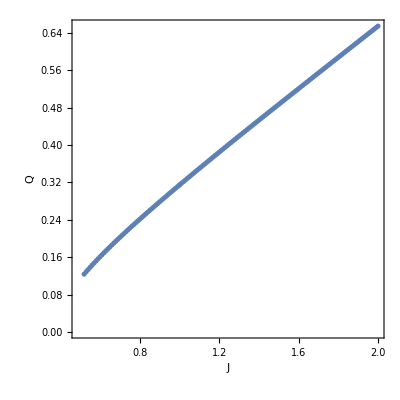
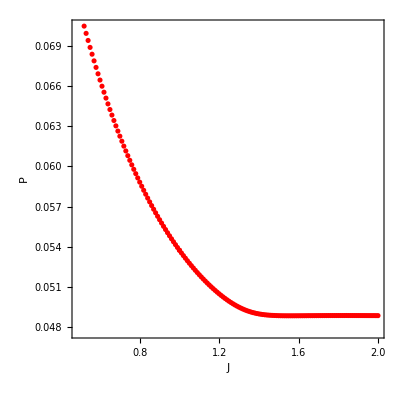
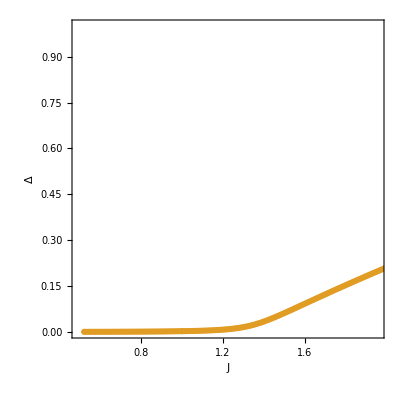

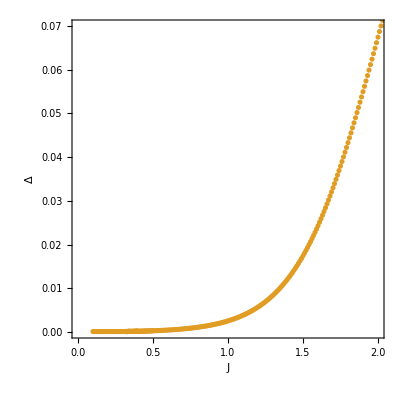
```mathematica
Show[-Graphics-,-Graphics-]
```

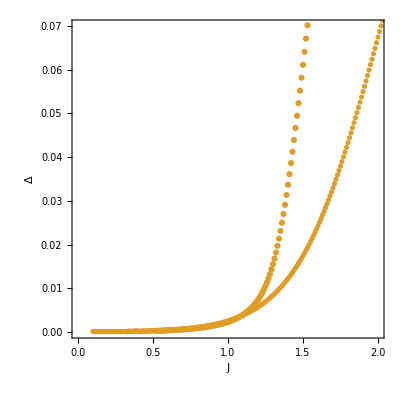

#### new data

```mathematica
(*T=0.02  Lx=Ly=20, J=0.5, ne=0.5 nonzero Q*)
```

```mathematica
{0.7262131313434991,0.538491330099501,0.14806766586435718,0.07702703786416494,-0.24116150128137556+0. ⅈ,-0.5291593723809175}
```

changing J T=0.02  Lx=Ly=20

```mathematica
data
```

{{2.,{2.22624,2.12069,0.752409,0.0575017,-0.209682+0. ⅈ,-2.12499}},{2.01,{2.23656,2.13156,0.756238,0.0574695,-0.209594+0. ⅈ,-2.13589}},{2.02,{2.24688,2.14243,0.760067,0.0574374,-0.209505+0. ⅈ,-2.14679}},{2.03,{2.25721,2.1533,0.763895,0.0574055,-0.209417+0. ⅈ,-2.1577}},{2.04,{2.26755,2.16416,0.767723,0.0573737,-0.209328+0. ⅈ,-2.16859}},{2.05,{2.27788,2.17503,0.771551,0.057342,-0.20924+0. ⅈ,-2.17949}},{2.06,{2.28822,2.1859,0.775378,0.0573104,-0.209151+0. ⅈ,-2.19039}},{2.07,{2.29856,2.19676,0.779204,0.057279,-0.209063+0. ⅈ,-2.20129}},{2.08,{2.30891,2.20763,0.783031,0.0572477,-0.208974+0. ⅈ,-2.21218}},{2.09,{2.31926,2.21849,0.786857,0.0572165,-0.208886+0. ⅈ,-2.22308}},{2.1,{2.32961,2.22936,0.790682,0.0571855,-0.208797+0. ⅈ,-2.23397}},{2.11,{2.33997,2.24022,0.794507,0.0571545,-0.208709+0. ⅈ,-2.24487}},{2.12,{2.35033,2.25108,0.798332,0.0571236,-0.20862+0. ⅈ,-2.25576}},{2.13,{2.3607,2.26194,0.802157,0.0570929,-0.208532+0. ⅈ,-2.26665}},{2.14,{2.37106,2.2728,0.805981,0.0570622,-0.208443+0. ⅈ,-2.27754}},{2.15,{2.38143,2.28366,0.809805,0.0570316,-0.208354+0. ⅈ,-2.28843}},{2.16,{2.3918,2.29452,0.813629,0.057,-0.208265+0. ⅈ,-2.29932}},{2.17,{2.40218,2.30538,0.817452,0.0569696,-0.208176+0. ⅈ,-2.31021}},{2.18,{2.41256,2.31624,0.821275,0.0569392,-0.208087+0. ⅈ,-2.3211}},{2.19,{2.42294,2.32709,0.825098,0.0569089,-0.207998+0. ⅈ,-2.33199}},{2.2,{2.43333,2.33795,0.82892,0.0568787,-0.207909+0. ⅈ,-2.34287}},{2.21,{2.44372,2.34881,0.832742,0.0568487,-0.20782+0. ⅈ,-2.35376}},{2.22,{2.45411,2.35966,0.836564,0.0568184,-0.20773+0. ⅈ,-2.36464}},{2.23,{2.46451,2.37051,0.840385,0.0567885,-0.20764+0. ⅈ,-2.37553}},{2.24,{2.4749,2.38137,0.844206,0.0567585,-0.207551+0. ⅈ,-2.38641}},{2.25,{2.48531,2.39222,0.848027,0.0567285,-0.207461+0. ⅈ,-2.39729}},{2.26,{2.49571,2.40307,0.851847,0.0566985,-0.20737+0. ⅈ,-2.40817}},{2.27,{2.50612,2.41392,0.855668,0.0566687,-0.20728+0. ⅈ,-2.41905}},{2.28,{2.51653,2.42477,0.859488,0.0566387,-0.20719+0. ⅈ,-2.42993}},{2.29,{2.52694,2.43562,0.863308,0.056609,-0.207099+0. ⅈ,-2.44081}},{2.3,{2.53735,2.44646,0.867127,0.0565792,-0.207008+0. ⅈ,-2.45169}},{2.31,{2.54777,2.45731,0.870946,0.0565493,-0.206917+0. ⅈ,-2.46256}},{2.32,{2.55819,2.46816,0.874765,0.0565195,-0.206825+0. ⅈ,-2.47344}},{2.33,{2.56861,2.479,0.878584,0.0564898,-0.206734+0. ⅈ,-2.48431}},{2.34,{2.57904,2.48985,0.882403,0.05646,-0.206642+0. ⅈ,-2.49519}},{2.35,{2.58947,2.50069,0.886221,0.0564301,-0.20655+0. ⅈ,-2.50606}},{2.36,{2.5999,2.51154,0.890039,0.0564004,-0.206457+0. ⅈ,-2.51693}},{2.37,{2.61033,2.52238,0.893857,0.0563707,-0.206365+0. ⅈ,-2.52781}},{2.38,{2.62077,2.53322,0.897674,0.0563409,-0.206272+0. ⅈ,-2.53868}},{2.39,{2.63121,2.54406,0.901492,0.056311,-0.206179+0. ⅈ,-2.54955}},{2.4,{2.64165,2.5549,0.905309,0.0562813,-0.206085+0. ⅈ,-2.56042}},{2.41,{2.65209,2.56574,0.909126,0.0562513,-0.205991+0. ⅈ,-2.57129}},{2.42,{2.66253,2.57658,0.912943,0.0562215,-0.205897+0. ⅈ,-2.58215}},{2.43,{2.67298,2.58742,0.916759,0.0561917,-0.205803+0. ⅈ,-2.59302}},{2.44,{2.68343,2.59826,0.920575,0.0561617,-0.205708+0. ⅈ,-2.60389}},{2.45,{2.69389,2.60909,0.924392,0.0561317,-0.205613+0. ⅈ,-2.61475}},{2.46,{2.70434,2.61993,0.928207,0.0561018,-0.205517+0. ⅈ,-2.62562}},{2.47,{2.7148,2.63077,0.932023,0.0560719,-0.205422+0. ⅈ,-2.63648}},{2.48,{2.72526,2.6416,0.935839,0.0560416,-0.205325+0. ⅈ,-2.64734}},{2.49,{2.73572,2.65243,0.939654,0.0560116,-0.205229+0. ⅈ,-2.6582}},{2.5,{2.74618,2.66327,0.943469,0.0559813,-0.205132+0. ⅈ,-2.66907}},{2.51,{2.75665,2.6741,0.947284,0.0559512,-0.205035+0. ⅈ,-2.67993}},{2.52,{2.76712,2.68493,0.951099,0.055921,-0.204937+0. ⅈ,-2.69079}},{2.53,{2.77759,2.69576,0.954914,0.0558904,-0.204839+0. ⅈ,-2.70164}},{2.54,{2.78806,2.70659,0.958728,0.0558601,-0.20474+0. ⅈ,-2.7125}},{2.55,{2.79853,2.71742,0.962542,0.0558297,-0.204641+0. ⅈ,-2.72336}},{2.56,{2.80901,2.72825,0.966356,0.0557992,-0.204542+0. ⅈ,-2.73422}},{2.57,{2.81949,2.73908,0.97017,0.0557685,-0.204442+0. ⅈ,-2.74507}},{2.58,{2.82997,2.74991,0.973984,0.0557378,-0.204342+0. ⅈ,-2.75593}},{2.59,{2.84045,2.76073,0.977798,0.055707,-0.204241+0. ⅈ,-2.76678}},{2.6,{2.85093,2.77156,0.981611,0.0556762,-0.20414+0. ⅈ,-2.77763}},{2.61,{2.86142,2.78238,0.985424,0.0556452,-0.204038+0. ⅈ,-2.78849}},{2.62,{2.87191,2.79321,0.989237,0.0556142,-0.203936+0. ⅈ,-2.79934}},{2.63,{2.8824,2.80403,0.99305,0.0555831,-0.203833+0. ⅈ,-2.81019}},{2.64,{2.89289,2.81486,0.996863,0.0555518,-0.20373+0. ⅈ,-2.82104}},{2.65,{2.90338,2.82568,1.00068,0.0555205,-0.203626+0. ⅈ,-2.83189}},{2.66,{2.91388,2.8365,1.00449,0.0554891,-0.203522+0. ⅈ,-2.84274}},{2.67,{2.92438,2.84732,1.0083,0.0554577,-0.203417+0. ⅈ,-2.85358}},{2.68,{2.93488,2.85814,1.01211,0.0554259,-0.203312+0. ⅈ,-2.86443}},{2.69,{2.94538,2.86896,1.01592,0.0553942,-0.203206+0. ⅈ,-2.87528}},{2.7,{2.95588,2.87978,1.01974,0.0553623,-0.2031+0. ⅈ,-2.88612}},{2.71,{2.96638,2.8906,1.02355,0.0553305,-0.202993+0. ⅈ,-2.89697}},{2.72,{2.97689,2.90142,1.02736,0.0552983,-0.202885+0. ⅈ,-2.90781}},{2.73,{2.9874,2.91224,1.03117,0.0552662,-0.202777+0. ⅈ,-2.91865}},{2.74,{2.99791,2.92305,1.03498,0.0552339,-0.202669+0. ⅈ,-2.9295}},{2.75,{3.00842,2.93387,1.03879,0.0552015,-0.202559+0. ⅈ,-2.94034}},{2.76,{3.01893,2.94468,1.04261,0.055169,-0.202449+0. ⅈ,-2.95118}},{2.77,{3.02945,2.9555,1.04642,0.0551363,-0.202339+0. ⅈ,-2.96202}},{2.78,{3.03996,2.96631,1.05023,0.0551034,-0.202228+0. ⅈ,-2.97286}},{2.79,{3.05048,2.97713,1.05404,0.0550704,-0.202116+0. ⅈ,-2.9837}},{2.8,{3.061,2.98794,1.05785,0.0550374,-0.202004+0. ⅈ,-2.99454}},{2.81,{3.07152,2.99875,1.06166,0.055004,-0.201891+0. ⅈ,-3.00537}},{2.82,{3.08204,3.00956,1.06547,0.0549707,-0.201777+0. ⅈ,-3.01621}},{2.83,{3.09257,3.02037,1.06928,0.0549371,-0.201663+0. ⅈ,-3.02705}},{2.84,{3.10309,3.03118,1.07309,0.0549036,-0.201548+0. ⅈ,-3.03788}},{2.85,{3.11362,3.04199,1.0769,0.0548696,-0.201432+0. ⅈ,-3.04871}},{2.86,{3.12415,3.0528,1.08071,0.0548356,-0.201316+0. ⅈ,-3.05955}},{2.87,{3.13468,3.06361,1.08452,0.0548014,-0.201199+0. ⅈ,-3.07038}},{2.88,{3.14521,3.07442,1.08833,0.0547673,-0.201081+0. ⅈ,-3.08121}},{2.89,{3.15574,3.08523,1.09214,0.0547326,-0.200963+0. ⅈ,-3.09205}},{2.9,{3.16628,3.09603,1.09595,0.0546981,-0.200844+0. ⅈ,-3.10288}},{2.91,{3.17681,3.10684,1.09976,0.054663,-0.200724+0. ⅈ,-3.11371}},{2.92,{3.18735,3.11764,1.10357,0.0546283,-0.200603+0. ⅈ,-3.12454}},{2.93,{3.19789,3.12845,1.10738,0.0545931,-0.200482+0. ⅈ,-3.13536}},{2.94,{3.20843,3.13925,1.11119,0.0545575,-0.20036+0. ⅈ,-3.14619}},{2.95,{3.21897,3.15006,1.11499,0.054522,-0.200237+0. ⅈ,-3.15702}},{2.96,{3.22951,3.16086,1.1188,0.0544867,-0.200113+0. ⅈ,-3.16785}},{2.97,{3.24006,3.17166,1.12261,0.0544504,-0.199989+0. ⅈ,-3.17867}},{2.98,{3.2506,3.18246,1.12642,0.0544143,-0.199864+0. ⅈ,-3.1895}},{2.99,{3.26115,3.19327,1.13023,0.0543783,-0.199738+0. ⅈ,-3.20032}},{3.,{3.2717,3.20407,1.13404,0.0543417,-0.199611+0. ⅈ,-3.21115}},{2.,{2.22624,2.12069,0.752409,0.0575017,-0.209682+0. ⅈ,-2.12499}},{1.99,{2.21592,2.10981,0.74858,0.0575342,-0.209771+0. ⅈ,-2.11409}},{1.98,{2.20561,2.09894,0.74475,0.0575668,-0.20986+0. ⅈ,-2.10319}},{1.97,{2.1953,2.08807,0.740919,0.0575996,-0.209948+0. ⅈ,-2.09228}},{1.96,{2.18499,2.0772,0.737089,0.0576325,-0.210037+0. ⅈ,-2.08138}},{1.95,{2.17469,2.06632,0.733257,0.0576656,-0.210126+0. ⅈ,-2.07047}},{1.94,{2.1644,2.05545,0.729426,0.0576989,-0.210216+0. ⅈ,-2.05956}},{1.93,{2.1541,2.04457,0.725593,0.0577324,-0.210305+0. ⅈ,-2.04866}},{1.92,{2.14381,2.03369,0.721761,0.0577662,-0.210394+0. ⅈ,-2.03775}},{1.91,{2.13353,2.02282,0.717927,0.0578001,-0.210484+0. ⅈ,-2.02684}},{1.9,{2.12325,2.01194,0.714094,0.0578342,-0.210573+0. ⅈ,-2.01593}},{1.89,{2.11297,2.00106,0.71026,0.0578686,-0.210663+0. ⅈ,-2.00502}},{1.88,{2.1027,1.99018,0.706425,0.0579031,-0.210753+0. ⅈ,-1.99411}},{1.87,{2.09243,1.9793,0.70259,0.057938,-0.210843+0. ⅈ,-1.9832}},{1.86,{2.08217,1.96842,0.698754,0.057973,-0.210934+0. ⅈ,-1.97228}},{1.85,{2.07191,1.95753,0.694917,0.0580083,-0.211024+0. ⅈ,-1.96137}},{1.84,{2.06166,1.94665,0.69108,0.0580439,-0.211115+0. ⅈ,-1.95046}},{1.83,{2.05141,1.93577,0.687243,0.0580798,-0.211206+0. ⅈ,-1.93954}},{1.82,{2.04117,1.92488,0.683405,0.0581159,-0.211297+0. ⅈ,-1.92862}},{1.81,{2.03093,1.914,0.679566,0.0581523,-0.211389+0. ⅈ,-1.91771}},{1.8,{2.02069,1.90311,0.675727,0.0581889,-0.211481+0. ⅈ,-1.90679}},{1.79,{2.01046,1.89223,0.671887,0.0582259,-0.211573+0. ⅈ,-1.89587}},{1.78,{2.00024,1.88134,0.668046,0.0582632,-0.211665+0. ⅈ,-1.88495}},{1.77,{1.99002,1.87045,0.664205,0.0583008,-0.211758+0. ⅈ,-1.87403}},{1.76,{1.9798,1.85956,0.660363,0.0583387,-0.211851+0. ⅈ,-1.86311}},{1.75,{1.96959,1.84867,0.656521,0.058377,-0.211944+0. ⅈ,-1.85219}},{1.74,{1.95939,1.83778,0.652677,0.0584155,-0.212038+0. ⅈ,-1.84127}},{1.73,{1.94919,1.82689,0.648833,0.0584545,-0.212132+0. ⅈ,-1.83035}},{1.72,{1.93899,1.816,0.644989,0.0584938,-0.212227+0. ⅈ,-1.81943}},{1.71,{1.92881,1.80511,0.641143,0.0585334,-0.212321+0. ⅈ,-1.8085}},{1.7,{1.91862,1.79421,0.637297,0.0585735,-0.212417+0. ⅈ,-1.79758}},{1.69,{1.90845,1.78332,0.63345,0.0586139,-0.212512+0. ⅈ,-1.78665}},{1.68,{1.89827,1.77242,0.629602,0.0586547,-0.212608+0. ⅈ,-1.77573}},{1.67,{1.88811,1.76153,0.625754,0.0586959,-0.212705+0. ⅈ,-1.7648}},{1.66,{1.87795,1.75063,0.621905,0.0587376,-0.212802+0. ⅈ,-1.75387}},{1.65,{1.86779,1.73974,0.618054,0.0587797,-0.212899+0. ⅈ,-1.74295}},{1.64,{1.85764,1.72884,0.614203,0.0588222,-0.212997+0. ⅈ,-1.73202}},{1.63,{1.8475,1.71794,0.610352,0.0588651,-0.213096+0. ⅈ,-1.72109}},{1.62,{1.83736,1.70704,0.606499,0.0589086,-0.213195+0. ⅈ,-1.71016}},{1.61,{1.82723,1.69615,0.602645,0.0589525,-0.213294+0. ⅈ,-1.69923}},{1.6,{1.8171,1.68525,0.598791,0.0589968,-0.213394+0. ⅈ,-1.6883}},{1.59,{1.80698,1.67435,0.594935,0.0590417,-0.213495+0. ⅈ,-1.67737}},{1.58,{1.79687,1.66345,0.591078,0.0590871,-0.213596+0. ⅈ,-1.66644}},{1.57,{1.78676,1.65255,0.58722,0.0591331,-0.213698+0. ⅈ,-1.6555}},{1.56,{1.77666,1.64164,0.583362,0.0591795,-0.213801+0. ⅈ,-1.64457}},{1.55,{1.76657,1.63074,0.579502,0.0592265,-0.213904+0. ⅈ,-1.63364}},{1.54,{1.75648,1.61984,0.575641,0.0592741,-0.214008+0. ⅈ,-1.62271}},{1.53,{1.7464,1.60894,0.571779,0.0593223,-0.214113+0. ⅈ,-1.61177}},{1.52,{1.73633,1.59803,0.567916,0.0593711,-0.214218+0. ⅈ,-1.60084}},{1.51,{1.72626,1.58713,0.564052,0.0594204,-0.214324+0. ⅈ,-1.58991}},{1.5,{1.7162,1.57623,0.560187,0.0594704,-0.214431+0. ⅈ,-1.57897}},{1.49,{1.70614,1.56532,0.55632,0.0595211,-0.214539+0. ⅈ,-1.56804}},{1.48,{1.6961,1.55442,0.552453,0.0595724,-0.214647+0. ⅈ,-1.5571}},{1.47,{1.68606,1.54351,0.548583,0.0596244,-0.214756+0. ⅈ,-1.54617}},{1.46,{1.67603,1.53261,0.544713,0.0596771,-0.214867+0. ⅈ,-1.53523}},{1.45,{1.666,1.5217,0.540841,0.0597305,-0.214978+0. ⅈ,-1.5243}},{1.44,{1.65598,1.5108,0.536968,0.0597847,-0.21509+0. ⅈ,-1.51336}},{1.43,{1.64597,1.49989,0.533094,0.0598396,-0.215203+0. ⅈ,-1.50242}},{1.42,{1.63597,1.48899,0.529218,0.0598953,-0.215317+0. ⅈ,-1.49149}},{1.41,{1.62597,1.47808,0.52534,0.0599518,-0.215432+0. ⅈ,-1.48055}},{1.4,{1.61599,1.46717,0.521461,0.0600091,-0.215548+0. ⅈ,-1.46962}},{1.39,{1.60601,1.45627,0.51758,0.0600672,-0.215665+0. ⅈ,-1.45868}},{1.38,{1.59603,1.44536,0.513698,0.0601263,-0.215783+0. ⅈ,-1.44775}},{1.37,{1.58607,1.43446,0.509814,0.0601862,-0.215902+0. ⅈ,-1.43681}},{1.36,{1.57611,1.42355,0.505929,0.0602469,-0.216022+0. ⅈ,-1.42588}},{1.35,{1.56616,1.41265,0.502041,0.0603088,-0.216144+0. ⅈ,-1.41494}},{1.34,{1.55622,1.40174,0.498152,0.0603715,-0.216266+0. ⅈ,-1.40401}},{1.33,{1.54629,1.39084,0.494261,0.0604352,-0.21639+0. ⅈ,-1.39308}},{1.32,{1.53637,1.37993,0.490368,0.0605,-0.216516+0. ⅈ,-1.38214}},{1.31,{1.52645,1.36903,0.486473,0.0605658,-0.216642+0. ⅈ,-1.37121}},{1.3,{1.51655,1.35813,0.482576,0.0606327,-0.21677+0. ⅈ,-1.36028}},{1.29,{1.50665,1.34723,0.478677,0.0607007,-0.216899+0. ⅈ,-1.34935}},{1.28,{1.49676,1.33632,0.474776,0.0607699,-0.21703+0. ⅈ,-1.33842}},{1.27,{1.48688,1.32542,0.470873,0.0608402,-0.217162+0. ⅈ,-1.32749}},{1.26,{1.47701,1.31452,0.466967,0.0609118,-0.217296+0. ⅈ,-1.31656}},{1.25,{1.46715,1.30362,0.463059,0.0609846,-0.217431+0. ⅈ,-1.30563}},{1.24,{1.45729,1.29272,0.459149,0.0610587,-0.217568+0. ⅈ,-1.2947}},{1.23,{1.44745,1.28183,0.455236,0.0611342,-0.217706+0. ⅈ,-1.28378}},{1.22,{1.43761,1.27093,0.451321,0.061211,-0.217846+0. ⅈ,-1.27285}},{1.21,{1.42779,1.26004,0.447403,0.0612893,-0.217987+0. ⅈ,-1.26193}},{1.2,{1.41797,1.24914,0.443482,0.061369,-0.21813+0. ⅈ,-1.25101}},{1.19,{1.40816,1.23825,0.439558,0.0614502,-0.218275+0. ⅈ,-1.24009}},{1.18,{1.39837,1.22736,0.435632,0.0615329,-0.218422+0. ⅈ,-1.22917}},{1.17,{1.38858,1.21647,0.431702,0.0616173,-0.218571+0. ⅈ,-1.21825}},{1.16,{1.3788,1.20558,0.42777,0.0617033,-0.218721+0. ⅈ,-1.20734}},{1.15,{1.36903,1.19469,0.423834,0.0617911,-0.218874+0. ⅈ,-1.19642}},{1.14,{1.35927,1.18381,0.419895,0.0618806,-0.219028+0. ⅈ,-1.18551}},{1.13,{1.34952,1.17293,0.415952,0.0619719,-0.219184+0. ⅈ,-1.1746}},{1.12,{1.33978,1.16205,0.412006,0.062065,-0.219343+0. ⅈ,-1.16369}},{1.11,{1.33005,1.15117,0.408056,0.0621601,-0.219503+0. ⅈ,-1.15279}},{1.1,{1.32033,1.14029,0.404103,0.0622573,-0.219666+0. ⅈ,-1.14189}},{1.09,{1.31063,1.12942,0.400145,0.0623564,-0.21983+0. ⅈ,-1.13099}},{1.08,{1.30093,1.11855,0.396184,0.0624577,-0.219997+0. ⅈ,-1.12009}},{1.07,{1.29124,1.10768,0.392218,0.0625613,-0.220166+0. ⅈ,-1.10919}},{1.06,{1.28156,1.09681,0.388248,0.062667,-0.220338+0. ⅈ,-1.0983}},{1.05,{1.27189,1.08595,0.384273,0.0627752,-0.220511+0. ⅈ,-1.08741}},{1.04,{1.26223,1.07509,0.380294,0.0628858,-0.220687+0. ⅈ,-1.07653}},{1.03,{1.25258,1.06424,0.37631,0.0629988,-0.220866+0. ⅈ,-1.06564}},{1.02,{1.24294,1.05338,0.372321,0.0631145,-0.221047+0. ⅈ,-1.05476}},{1.01,{1.23331,1.04253,0.368326,0.0632329,-0.22123+0. ⅈ,-1.04389}},{1.,{1.22369,1.03169,0.364326,0.063354,-0.221416+0. ⅈ,-1.03302}},{0.99,{1.21408,1.02084,0.360321,0.063478,-0.221604+0. ⅈ,-1.02215}},{0.98,{1.20448,1.01,0.35631,0.0636049,-0.221795+0. ⅈ,-1.01128}},{0.97,{1.19489,0.99917,0.352292,0.0637349,-0.221989+0. ⅈ,-1.00042}},{0.96,{1.18531,0.98834,0.348269,0.0638681,-0.222185+0. ⅈ,-0.989569}},{0.95,{1.17574,0.977514,0.344238,0.0640045,-0.222384+0. ⅈ,-0.978719}},{0.94,{1.16618,0.966692,0.340201,0.0641443,-0.222586+0. ⅈ,-0.967872}},{0.93,{1.15663,0.955876,0.336157,0.0642876,-0.222791+0. ⅈ,-0.957031}},{0.92,{1.14708,0.945064,0.332105,0.0644345,-0.222998+0. ⅈ,-0.946195}},{0.91,{1.13755,0.934258,0.328046,0.0645851,-0.223208+0. ⅈ,-0.935364}},{0.9,{1.12802,0.923457,0.323978,0.0647395,-0.223421+0. ⅈ,-0.924539}},{0.89,{1.1185,0.912662,0.319902,0.0648979,-0.223637+0. ⅈ,-0.91372}},{0.88,{1.10899,0.901873,0.315818,0.0650604,-0.223855+0. ⅈ,-0.902907}},{0.87,{1.09948,0.89109,0.311724,0.0652272,-0.224077+0. ⅈ,-0.8921}},{0.86,{1.08999,0.880313,0.307621,0.0653983,-0.224301+0. ⅈ,-0.8813}},{0.85,{1.08049,0.869543,0.303507,0.0655739,-0.224529+0. ⅈ,-0.870506}},{0.84,{1.07101,0.85878,0.299384,0.0657542,-0.224759+0. ⅈ,-0.85972}},{0.83,{1.06153,0.848025,0.295249,0.0659392,-0.224992+0. ⅈ,-0.848941}},{0.82,{1.05205,0.837277,0.291103,0.0661292,-0.225228+0. ⅈ,-0.83817}},{0.81,{1.04258,0.826537,0.286946,0.0663244,-0.225467+0. ⅈ,-0.827408}},{0.8,{1.03311,0.815805,0.282775,0.0665248,-0.225709+0. ⅈ,-0.816653}},{0.79,{1.02364,0.805082,0.278592,0.0667306,-0.225954+0. ⅈ,-0.805908}},{0.78,{1.01418,0.794368,0.274395,0.066942,-0.226202+0. ⅈ,-0.795172}},{0.77,{1.00471,0.783664,0.270184,0.0671592,-0.226453+0. ⅈ,-0.784446}},{0.76,{0.995246,0.77297,0.265958,0.0673823,-0.226706+0. ⅈ,-0.773729}},{0.75,{0.985779,0.762286,0.261716,0.0676115,-0.226962+0. ⅈ,-0.763024}},{0.74,{0.976308,0.751613,0.257457,0.067847,-0.227221+0. ⅈ,-0.752329}},{0.73,{0.966833,0.740951,0.253181,0.068089,-0.227483+0. ⅈ,-0.741646}},{0.72,{0.957352,0.730302,0.248886,0.0683376,-0.227747+0. ⅈ,-0.730976}},{0.71,{0.947865,0.719665,0.244572,0.0685931,-0.228013+0. ⅈ,-0.720318}},{0.7,{0.938368,0.709041,0.240238,0.0688556,-0.228282+0. ⅈ,-0.709673}},{0.69,{0.92886,0.69843,0.235882,0.0691254,-0.228554+0. ⅈ,-0.699043}},{0.68,{0.91934,0.687835,0.231503,0.0694025,-0.228827+0. ⅈ,-0.688427}},{0.67,{0.909805,0.677254,0.227101,0.0696873,-0.229103+0. ⅈ,-0.677826}},{0.66,{0.900253,0.666689,0.222673,0.06998,-0.22938+0. ⅈ,-0.667241}},{0.65,{0.890681,0.656141,0.218217,0.0702806,-0.22966+0. ⅈ,-0.656674}},{0.64,{0.881088,0.645609,0.213734,0.0705895,-0.229941+0. ⅈ,-0.646123}},{0.63,{0.871471,0.635097,0.20922,0.0709068,-0.230223+0. ⅈ,-0.635591}},{0.62,{0.861827,0.624603,0.204673,0.0712327,-0.230507+0. ⅈ,-0.625079}},{0.61,{0.852152,0.614129,0.200093,0.0715675,-0.230791+0. ⅈ,-0.614587}},{0.6,{0.842444,0.603676,0.195475,0.0719112,-0.231077+0. ⅈ,-0.604115}},{0.59,{0.832699,0.593244,0.190818,0.0722643,-0.231363+0. ⅈ,-0.593666}},{0.58,{0.822913,0.582836,0.186119,0.0726268,-0.23165+0. ⅈ,-0.58324}},{0.57,{0.813083,0.572451,0.181375,0.0729989,-0.231936+0. ⅈ,-0.572838}},{0.56,{0.803206,0.562091,0.176582,0.0733809,-0.232222+0. ⅈ,-0.562461}},{0.55,{0.793275,0.551758,0.171736,0.073773,-0.232508+0. ⅈ,-0.552111}},{0.54,{0.783288,0.541451,0.166833,0.0741753,-0.232793+0. ⅈ,-0.541787}},{0.53,{0.77324,0.531172,0.161868,0.0745881,-0.233077+0. ⅈ,-0.531493}},{0.52,{0.763125,0.520923,0.156836,0.0750116,-0.233359+0. ⅈ,-0.521228}},{0.51,{0.752938,0.510705,0.15173,0.075446,-0.233639+0. ⅈ,-0.510994}},{0.5,{0.742675,0.500518,0.146543,0.0758914,-0.233917+0. ⅈ,-0.500792}},{0.49,{0.732329,0.490363,0.141265,0.0763481,-0.234192+0. ⅈ,-0.490623}},{0.48,{0.721894,0.480243,0.135888,0.0768162,-0.234464+0. ⅈ,-0.480489}},{0.48,{0.721894,0.480243,0.135888,0.0768162,-0.234464+0. ⅈ,-0.480489}},{0.48,{0.721894,0.480243,0.135888,0.0768162,-0.234464+0. ⅈ,-0.480489}},{0.478,{0.719796,0.478223,0.1348,0.0769113,-0.234518+0. ⅈ,-0.478466}},{0.476,{0.717694,0.476205,0.133707,0.0770068,-0.234572+0. ⅈ,-0.476445}},{0.474,{0.715589,0.474188,0.132609,0.0771027,-0.234626+0. ⅈ,-0.474425}},{0.472,{0.713479,0.472172,0.131506,0.0771992,-0.23468+0. ⅈ,-0.472407}},{0.47,{0.711365,0.470158,0.130399,0.0772961,-0.234733+0. ⅈ,-0.47039}},{0.468,{0.709248,0.468145,0.129287,0.0773935,-0.234786+0. ⅈ,-0.468374}},{0.466,{0.707126,0.466134,0.128169,0.0774913,-0.234839+0. ⅈ,-0.46636}},{0.464,{0.705,0.464124,0.127046,0.0775897,-0.234892+0. ⅈ,-0.464348}},{0.462,{0.70287,0.462116,0.125918,0.0776885,-0.234945+0. ⅈ,-0.462337}},{0.46,{0.700735,0.460109,0.124784,0.0777878,-0.234997+0. ⅈ,-0.460327}},{0.458,{0.698597,0.458103,0.123644,0.0778876,-0.23505+0. ⅈ,-0.458319}},{0.456,{0.696454,0.456099,0.122499,0.0779879,-0.235102+0. ⅈ,-0.456313}},{0.454,{0.694306,0.454097,0.121347,0.0780886,-0.235154+0. ⅈ,-0.454308}},{0.452,{0.692154,0.452096,0.12019,0.0781899,-0.235206+0. ⅈ,-0.452305}},{0.45,{0.689998,0.450097,0.119026,0.0782916,-0.235258+0. ⅈ,-0.450303}},{0.448,{0.687837,0.448099,0.117855,0.0783939,-0.235309+0. ⅈ,-0.448303}},{0.446,{0.685671,0.446102,0.116678,0.0784966,-0.23536+0. ⅈ,-0.446304}},{0.444,{0.683501,0.444108,0.115493,0.0785998,-0.235411+0. ⅈ,-0.444307}},{0.442,{0.681326,0.442114,0.114302,0.0787035,-0.235462+0. ⅈ,-0.442311}},{0.44,{0.679146,0.440123,0.113103,0.0788077,-0.235513+0. ⅈ,-0.440317}},{0.438,{0.676962,0.438133,0.111896,0.0789125,-0.235563+0. ⅈ,-0.438325}},{0.436,{0.674772,0.436144,0.110682,0.0790177,-0.235613+0. ⅈ,-0.436334}},{0.434,{0.672577,0.434157,0.109459,0.0791234,-0.235663+0. ⅈ,-0.434344}},{0.432,{0.670378,0.432172,0.108229,0.0792296,-0.235713+0. ⅈ,-0.432357}},{0.43,{0.668173,0.430188,0.106989,0.0793364,-0.235763+0. ⅈ,-0.430371}},{0.428,{0.665963,0.428206,0.10574,0.0794436,-0.235812+0. ⅈ,-0.428386}},{0.426,{0.663748,0.426225,0.104483,0.0795514,-0.235861+0. ⅈ,-0.426403}},{0.424,{0.661528,0.424246,0.103215,0.0796597,-0.23591+0. ⅈ,-0.424422}},{0.422,{0.659302,0.422269,0.101938,0.0797684,-0.235958+0. ⅈ,-0.422443}},{0.42,{0.657071,0.420293,0.10065,0.0798777,-0.236007+0. ⅈ,-0.420465}},{0.418,{0.654835,0.418319,0.0993513,0.0799876,-0.236055+0. ⅈ,-0.418489}},{0.416,{0.652593,0.416346,0.0980415,0.0800979,-0.236103+0. ⅈ,-0.416514}},{0.414,{0.650345,0.414375,0.0967202,0.0802088,-0.23615+0. ⅈ,-0.414541}},{0.412,{0.648092,0.412406,0.0953868,0.0803202,-0.236197+0. ⅈ,-0.41257}},{0.41,{0.645833,0.410438,0.0940408,0.0804321,-0.236244+0. ⅈ,-0.4106}},{0.408,{0.643568,0.408472,0.0926816,0.0805445,-0.236291+0. ⅈ,-0.408632}},{0.406,{0.641298,0.406508,0.0913087,0.0806575,-0.236338+0. ⅈ,-0.406666}},{0.404,{0.639021,0.404545,0.0899215,0.080771,-0.236384+0. ⅈ,-0.404702}},{0.402,{0.636739,0.402584,0.0885193,0.080885,-0.23643+0. ⅈ,-0.402739}},{0.4,{0.63445,0.400625,0.0871014,0.0809996,-0.236476+0. ⅈ,-0.400777}},{0.398,{0.632156,0.398667,0.0856669,0.0811147,-0.236521+0. ⅈ,-0.398818}},{0.396,{0.629855,0.396711,0.0842151,0.0812304,-0.236566+0. ⅈ,-0.39686}},{0.394,{0.627548,0.394756,0.0827451,0.0813466,-0.236611+0. ⅈ,-0.394904}},{0.392,{0.625235,0.392803,0.0812559,0.0814633,-0.236655+0. ⅈ,-0.392949}},{0.39,{0.622916,0.390852,0.0797464,0.0815806,-0.236699+0. ⅈ,-0.390997}},{0.388,{0.62059,0.388903,0.0782154,0.0816984,-0.236743+0. ⅈ,-0.389045}},{0.386,{0.618258,0.386955,0.0766617,0.0818168,-0.236787+0. ⅈ,-0.387096}},{0.384,{0.615919,0.385009,0.0750839,0.0819358,-0.23683+0. ⅈ,-0.385148}},{0.382,{0.613573,0.383064,0.0734805,0.0820552,-0.236873+0. ⅈ,-0.383202}},{0.38,{0.611221,0.381121,0.0718496,0.0821753,-0.236916+0. ⅈ,-0.381258}},{0.378,{0.608862,0.37918,0.0701894,0.0822959,-0.236958+0. ⅈ,-0.379315}},{0.376,{0.606497,0.377241,0.0684979,0.0824171,-0.237+0. ⅈ,-0.377374}},{0.374,{0.604124,0.375303,0.0667726,0.0825388,-0.237042+0. ⅈ,-0.375435}},{0.372,{0.601745,0.373366,0.0650106,0.0826612,-0.237083+0. ⅈ,-0.373498}},{0.37,{0.599358,0.371432,0.0632095,0.082784,-0.237124+0. ⅈ,-0.371562}},{0.368,{0.596964,0.369499,0.0613652,0.0829075,-0.237165+0. ⅈ,-0.369627}},{0.366,{0.594564,0.367567,0.059474,0.0830315,-0.237205+0. ⅈ,-0.367695}},{0.364,{0.592156,0.365638,0.0575312,0.0831561,-0.237245+0. ⅈ,-0.365764}},{0.362,{0.58974,0.36371,0.0555316,0.0832813,-0.237285+0. ⅈ,-0.363835}},{0.36,{0.587318,0.361783,0.0534686,0.083407,-0.237324+0. ⅈ,-0.361907}},{0.358,{0.584888,0.359858,0.0513346,0.0835334,-0.237363+0. ⅈ,-0.359981}},{0.358,{0.584888,0.359858,0.0513346,0.0835334,-0.237363+0. ⅈ,-0.359981}},{0.358,{0.584888,0.359858,0.0513346,0.0835334,-0.237363+0. ⅈ,-0.359981}},{0.357,{0.58367,0.358897,0.0502381,0.0835968,-0.237383+0. ⅈ,-0.359019}},{0.356,{0.58245,0.357935,0.0491204,0.0836603,-0.237402+0. ⅈ,-0.358057}},{0.355,{0.581228,0.356974,0.0479797,0.083724,-0.237421+0. ⅈ,-0.357095}},{0.354,{0.580005,0.356014,0.0468146,0.0837878,-0.23744+0. ⅈ,-0.356134}},{0.353,{0.57878,0.355053,0.0456231,0.0838518,-0.237459+0. ⅈ,-0.355174}},{0.352,{0.577552,0.354093,0.0444031,0.083916,-0.237478+0. ⅈ,-0.354213}},{0.351,{0.576323,0.353134,0.0431521,0.0839802,-0.237497+0. ⅈ,-0.353253}},{0.35,{0.575092,0.352175,0.0418677,0.0840446,-0.237516+0. ⅈ,-0.352294}},{0.349,{0.573859,0.351216,0.0405459,0.0841092,-0.237534+0. ⅈ,-0.351335}},{0.348,{0.572624,0.350258,0.0391838,0.084174,-0.237553+0. ⅈ,-0.350376}},{0.347,{0.571386,0.3493,0.0377764,0.0842389,-0.237571+0. ⅈ,-0.349418}},{0.346,{0.570147,0.348343,0.0363192,0.0843039,-0.23759+0. ⅈ,-0.34846}},{0.346,{0.570147,0.348343,0.0363192,0.0843039,-0.23759+0. ⅈ,-0.34846}},{0.3455,{0.569527,0.347864,0.0355694,0.0843365,-0.237599+0. ⅈ,-0.347981}},{0.345,{0.568906,0.347386,0.0348049,0.0843691,-0.237608+0. ⅈ,-0.347502}},{0.3445,{0.568285,0.346907,0.0340243,0.0844018,-0.237617+0. ⅈ,-0.347024}},{0.344,{0.567663,0.346429,0.0332266,0.0844344,-0.237626+0. ⅈ,-0.346545}},{0.3435,{0.567041,0.345951,0.0324104,0.0844672,-0.237635+0. ⅈ,-0.346067}},{0.343,{0.566419,0.345473,0.0315743,0.0844999,-0.237644+0. ⅈ,-0.345588}},{0.3425,{0.565795,0.344995,0.0307168,0.0845327,-0.237654+0. ⅈ,-0.34511}},{0.342,{0.565172,0.344517,0.029836,0.0845656,-0.237663+0. ⅈ,-0.344632}},{0.3415,{0.564547,0.344039,0.0289296,0.0845984,-0.237671+0. ⅈ,-0.344154}},{0.341,{0.563922,0.343561,0.0279953,0.0846313,-0.23768+0. ⅈ,-0.343676}},{0.3405,{0.563297,0.343083,0.02703,0.0846643,-0.237689+0. ⅈ,-0.343198}},{0.34,{0.562671,0.342606,0.0260306,0.0846973,-0.237698+0. ⅈ,-0.34272}},{0.3395,{0.562045,0.342128,0.0249928,0.0847303,-0.237707+0. ⅈ,-0.342243}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.329,{0.558387,0.339072,2.76267×10^-9,0.0839853,-0.237793+0. ⅈ,-0.339184}},{0.319,{0.566832,0.344851,-8.10404×10^-10,0.0814719,-0.237755+0. ⅈ,-0.344964}},{0.309,{0.575277,0.350647,-8.10404×10^-10,0.078955,-0.237716+0. ⅈ,-0.35076}},{0.299,{0.583719,0.356459,7.06719×10^-11,0.0764346,-0.237677+0. ⅈ,-0.356572}},{0.289,{0.59216,0.362287,7.06719×10^-11,0.0739109,-0.237637+0. ⅈ,-0.3624}},{0.279,{0.600599,0.36813,7.06719×10^-11,0.0713841,-0.237598+0. ⅈ,-0.368244}},{0.269,{0.609035,0.373988,7.06719×10^-11,0.0688543,-0.237559+0. ⅈ,-0.374102}},{0.259,{0.617469,0.37986,7.06719×10^-11,0.0663217,-0.237519+0. ⅈ,-0.379975}},{0.249,{0.6259,0.385747,7.06719×10^-11,0.0637862,-0.23748+0. ⅈ,-0.385862}},{0.239,{0.634328,0.391648,7.06719×10^-11,0.0612482,-0.23744+0. ⅈ,-0.391763}},{0.229,{0.642752,0.397562,7.06719×10^-11,0.0587076,-0.2374+0. ⅈ,-0.397677}},{0.219,{0.651174,0.403489,7.06719×10^-11,0.0561645,-0.23736+0. ⅈ,-0.403605}},{0.209,{0.659592,0.40943,7.06719×10^-11,0.0536191,-0.23732+0. ⅈ,-0.409546}},{0.209,{0.659592,0.40943,7.06719×10^-11,0.0536191,-0.23732+0. ⅈ,-0.409546}},{0.199,{0.668006,0.415383,7.06719×10^-11,0.0510714,-0.23728+0. ⅈ,-0.415499}},{0.189,{0.676417,0.421349,7.06719×10^-11,0.0485216,-0.23724+0. ⅈ,-0.421465}},{0.179,{0.684824,0.427326,7.06719×10^-11,0.0459696,-0.2372+0. ⅈ,-0.427444}},{0.169,{0.693226,0.433316,7.06719×10^-11,0.0434156,-0.23716+0. ⅈ,-0.433434}},{0.159,{0.701625,0.439318,7.06719×10^-11,0.0408597,-0.23712+0. ⅈ,-0.439436}},{0.149,{0.71002,0.445331,7.06719×10^-11,0.0383018,-0.23708+0. ⅈ,-0.445449}},{0.139,{0.718411,0.451355,7.06719×10^-11,0.0357421,-0.23704+0. ⅈ,-0.451474}},{0.129,{0.726798,0.45739,7.06719×10^-11,0.0331806,-0.236999+0. ⅈ,-0.457509}},{0.119,{0.73518,0.463437,7.06719×10^-11,0.0306174,-0.236959+0. ⅈ,-0.463556}},{0.109,{0.743558,0.469494,7.06719×10^-11,0.0280526,-0.236919+0. ⅈ,-0.469614}},{0.099,{0.751932,0.475561,7.06719×10^-11,0.0254861,-0.236878+0. ⅈ,-0.475682}},{0.089,{0.760302,0.481639,7.06719×10^-11,0.0229181,-0.236838+0. ⅈ,-0.48176}},{0.079,{0.768667,0.487728,7.06719×10^-11,0.0203485,-0.236798+0. ⅈ,-0.487848}},{0.069,{0.777028,0.493826,7.06719×10^-11,0.0177774,-0.236757+0. ⅈ,-0.493947}},{0.059,{0.785385,0.499934,7.06719×10^-11,0.0152049,-0.236717+0. ⅈ,-0.500056}},{0.049,{0.793737,0.506052,7.06719×10^-11,0.0126311,-0.236677+0. ⅈ,-0.506174}},{0.039,{0.802085,0.512179,7.06719×10^-11,0.0100558,-0.236636+0. ⅈ,-0.512302}},{0.029,{0.810428,0.518316,7.06719×10^-11,0.00747923,-0.236596+0. ⅈ,-0.518439}},{0.229,{0.642752,0.397562,7.06719×10^-11,0.0587076,-0.2374+0. ⅈ,-0.397677}},{0.239,{0.634328,0.391648,7.06719×10^-11,0.0612482,-0.23744+0. ⅈ,-0.391763}},{0.249,{0.6259,0.385747,7.06719×10^-11,0.0637862,-0.23748+0. ⅈ,-0.385862}},{0.259,{0.617469,0.37986,7.06719×10^-11,0.0663217,-0.237519+0. ⅈ,-0.379975}},{0.269,{0.609035,0.373988,7.06719×10^-11,0.0688543,-0.237559+0. ⅈ,-0.374102}},{0.279,{0.600599,0.36813,7.06719×10^-11,0.0713841,-0.237598+0. ⅈ,-0.368244}},{0.289,{0.59216,0.362287,7.06719×10^-11,0.0739109,-0.237637+0. ⅈ,-0.3624}},{0.299,{0.583719,0.356459,7.06719×10^-11,0.0764346,-0.237677+0. ⅈ,-0.356572}},{0.309,{0.575277,0.350647,7.06719×10^-11,0.078955,-0.237716+0. ⅈ,-0.35076}},{0.319,{0.566832,0.344851,7.06719×10^-11,0.0814719,-0.237755+0. ⅈ,-0.344964}},{0.329,{0.558387,0.339072,7.06719×10^-11,0.0839853,-0.237793+0. ⅈ,-0.339184}},{0.339,{0.549941,0.33331,7.06719×10^-11,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.349,{0.541495,0.327565,7.06719×10^-11,0.0890005,-0.23787+0. ⅈ,-0.327677}},{0.359,{0.533049,0.321839,7.06719×10^-11,0.0915019,-0.237909+0. ⅈ,-0.32195}},{0.369,{0.524603,0.316131,7.06719×10^-11,0.093999,-0.237947+0. ⅈ,-0.316242}},{0.379,{0.516159,0.310443,7.06719×10^-11,0.0964915,-0.237985+0. ⅈ,-0.310553}},{0.389,{0.507716,0.304774,7.06719×10^-11,0.0989791,-0.238023+0. ⅈ,-0.304885}},{0.399,{0.499276,0.299127,7.06719×10^-11,0.101462,-0.23806+0. ⅈ,-0.299237}},{0.409,{0.49084,0.293501,7.06719×10^-11,0.103939,-0.238098+0. ⅈ,-0.29361}},{0.419,{0.482408,0.287897,7.06719×10^-11,0.10641,-0.238135+0. ⅈ,-0.288006}},{0.429,{0.473981,0.282316,7.06719×10^-11,0.108875,-0.238172+0. ⅈ,-0.282425}},{0.439,{0.46556,0.276759,7.06719×10^-11,0.111334,-0.238208+0. ⅈ,-0.276868}},{0.449,{0.457146,0.271228,7.06719×10^-11,0.113786,-0.238245+0. ⅈ,-0.271336}},{0.459,{0.448741,0.265722,7.06719×10^-11,0.11623,-0.238281+0. ⅈ,-0.26583}},{0.469,{0.440345,0.260244,7.06719×10^-11,0.118667,-0.238317+0. ⅈ,-0.260352}},{0.479,{0.431961,0.254794,7.06719×10^-11,0.121096,-0.238352+0. ⅈ,-0.254902}},{0.489,{0.42359,0.249374,7.06719×10^-11,0.123516,-0.238387+0. ⅈ,-0.249481}},{0.499,{0.415234,0.243985,7.06719×10^-11,0.125926,-0.238422+0. ⅈ,-0.244092}},{0.509,{0.406895,0.238628,7.06719×10^-11,0.128327,-0.238457+0. ⅈ,-0.238735}},{0.519,{0.398575,0.233306,7.06719×10^-11,0.130717,-0.238491+0. ⅈ,-0.233413}},{0.529,{0.390276,0.22802,7.06719×10^-11,0.133095,-0.238524+0. ⅈ,-0.228127}},{0.539,{0.382001,0.222772,7.06719×10^-11,0.135461,-0.238558+0. ⅈ,-0.222878}},{0.549,{0.373753,0.217564,4.6633×10^-13,0.137814,-0.238591+0. ⅈ,-0.21767}},{0.559,{0.365535,0.212398,4.6633×10^-13,0.140152,-0.238623+0. ⅈ,-0.212504}},{0.569,{0.357351,0.207277,4.6633×10^-13,0.142476,-0.238655+0. ⅈ,-0.207382}},{0.579,{0.349203,0.202202,4.6633×10^-13,0.144783,-0.238687+0. ⅈ,-0.202308}},{0.589,{0.341097,0.197178,4.6633×10^-13,0.147073,-0.238718+0. ⅈ,-0.197283}},{0.599,{0.333037,0.192206,4.6633×10^-13,0.149344,-0.238748+0. ⅈ,-0.192311}},{0.599,{0.333037,0.192206,4.6633×10^-13,0.149344,-0.238748+0. ⅈ,-0.192311}},{0.599,{0.333037,0.192206,4.6633×10^-13,0.149344,-0.238748+0. ⅈ,-0.192311}},{0.609,{0.325027,0.187291,4.6633×10^-13,0.151595,-0.238778+0. ⅈ,-0.187395}},{0.619,{0.317073,0.182434,4.6633×10^-13,0.153825,-0.238807+0. ⅈ,-0.182538}},{0.629,{0.309181,0.17764,4.6633×10^-13,0.156031,-0.238836+0. ⅈ,-0.177744}},{0.639,{0.301355,0.172913,4.6633×10^-13,0.158212,-0.238864+0. ⅈ,-0.173017}},{0.649,{0.293604,0.168256,4.6633×10^-13,0.160367,-0.238892+0. ⅈ,-0.16836}},{0.659,{0.285933,0.163674,4.6633×10^-13,0.162493,-0.238918+0. ⅈ,-0.163778}},{0.669,{0.278349,0.159171,4.6633×10^-13,0.164588,-0.238945+0. ⅈ,-0.159274}},{0.679,{0.270861,0.154751,4.6633×10^-13,0.166651,-0.23897+0. ⅈ,-0.154854}},{0.689,{0.263477,0.150419,4.6633×10^-13,0.168679,-0.238995+0. ⅈ,-0.150522}},{0.699,{0.256203,0.146179,4.6633×10^-13,0.170671,-0.239019+0. ⅈ,-0.146282}},{0.709,{0.249047,0.142036,4.6633×10^-13,0.172624,-0.239042+0. ⅈ,-0.142139}},{0.719,{0.242019,0.137994,4.6633×10^-13,0.174537,-0.239064+0. ⅈ,-0.138097}},{0.729,{0.235125,0.134057,4.6633×10^-13,0.176407,-0.239086+0. ⅈ,-0.134159}},{0.739,{0.228373,0.130229,4.6633×10^-13,0.178234,-0.239106+0. ⅈ,-0.130331}},{0.749,{0.221769,0.126512,4.6633×10^-13,0.180015,-0.239127+0. ⅈ,-0.126613}},{0.759,{0.21532,0.122909,4.6633×10^-13,0.181749,-0.239146+0. ⅈ,-0.12301}},{0.769,{0.20903,0.119422,4.6633×10^-13,0.183436,-0.239164+0. ⅈ,-0.119522}},{0.779,{0.202904,0.116052,4.6633×10^-13,0.185075,-0.239182+0. ⅈ,-0.116152}},{0.789,{0.196945,0.1128,4.6633×10^-13,0.186665,-0.239199+0. ⅈ,-0.1129}},{0.799,{0.191156,0.109666,4.6633×10^-13,0.188206,-0.239215+0. ⅈ,-0.109766}},{0.809,{0.185539,0.10665,4.6633×10^-13,0.189699,-0.23923+0. ⅈ,-0.106749}},{0.819,{0.180095,0.103751,4.6633×10^-13,0.191143,-0.239245+0. ⅈ,-0.10385}},{0.829,{0.174825,0.100968,4.6633×10^-13,0.192538,-0.239259+0. ⅈ,-0.101066}},{0.839,{0.16973,0.0982983,4.6633×10^-13,0.193886,-0.239272+0. ⅈ,-0.0983954}},{0.849,{0.164807,0.0957405,4.6633×10^-13,0.195186,-0.239284+0. ⅈ,-0.0958368}},{0.859,{0.160056,0.0932917,4.6633×10^-13,0.19644,-0.239296+0. ⅈ,-0.0933873}},{0.869,{0.155475,0.0909492,4.6633×10^-13,0.197648,-0.239307+0. ⅈ,-0.091044}},{0.879,{0.151061,0.0887096,4.6633×10^-13,0.198811,-0.239318+0. ⅈ,-0.0888036}},{0.889,{0.14681,0.0865696,4.6633×10^-13,0.199932,-0.239328+0. ⅈ,-0.0866627}},{0.899,{0.14272,0.0845255,4.6633×10^-13,0.20101,-0.239338+0. ⅈ,-0.0846176}},{0.909,{0.138786,0.0825736,4.6633×10^-13,0.202047,-0.239347+0. ⅈ,-0.0826647}},{0.919,{0.135004,0.0807102,4.6633×10^-13,0.203046,-0.239355+0. ⅈ,-0.0808001}},{0.929,{0.13137,0.0789313,4.6633×10^-13,0.204006,-0.239363+0. ⅈ,-0.0790201}},{0.939,{0.127878,0.0772333,4.6633×10^-13,0.20493,-0.239371+0. ⅈ,-0.0773209}},{0.949,{0.124525,0.0756125,4.6633×10^-13,0.205819,-0.239378+0. ⅈ,-0.0756989}},{0.959,{0.121306,0.0740654,4.6633×10^-13,0.206674,-0.239384+0. ⅈ,-0.0741505}},{0.969,{0.118216,0.0725884,4.6633×10^-13,0.207496,-0.23939+0. ⅈ,-0.0726722}},{0.979,{0.115251,0.0711782,4.6633×10^-13,0.208288,-0.239396+0. ⅈ,-0.0712607}},{0.989,{0.112407,0.0698318,4.6633×10^-13,0.209049,-0.239402+0. ⅈ,-0.0699129}},{0.999,{0.109679,0.0685459,4.6633×10^-13,0.209782,-0.239407+0. ⅈ,-0.0686256}},{1.009,{0.107062,0.0673177,4.6633×10^-13,0.210487,-0.239412+0. ⅈ,-0.067396}},{1.019,{0.104553,0.0661444,4.6633×10^-13,0.211166,-0.239417+0. ⅈ,-0.0662213}},{1.029,{0.102148,0.0650234,4.6633×10^-13,0.211819,-0.239421+0. ⅈ,-0.0650988}},{1.039,{0.0998425,0.0639522,4.6633×10^-13,0.212448,-0.239425+0. ⅈ,-0.0640261}},{1.049,{0.0976328,0.0629282,4.6633×10^-13,0.213053,-0.239429+0. ⅈ,-0.0630007}},{1.059,{0.0955151,0.0619494,4.6633×10^-13,0.213636,-0.239432+0. ⅈ,-0.0620204}},{1.069,{0.093486,0.0610135,4.6633×10^-13,0.214197,-0.239436+0. ⅈ,-0.061083}},{1.079,{0.0915416,0.0601184,4.6633×10^-13,0.214738,-0.239439+0. ⅈ,-0.0601865}},{1.089,{0.0896787,0.0592622,4.6633×10^-13,0.215258,-0.239442+0. ⅈ,-0.0593288}},{1.099,{0.0878937,0.0584429,4.6633×10^-13,0.215759,-0.239444+0. ⅈ,-0.0585082}},{1.109,{0.0861835,0.0576589,4.6633×10^-13,0.216242,-0.239447+0. ⅈ,-0.0577228}},{1.119,{0.0845448,0.0569084,4.6633×10^-13,0.216707,-0.239449+0. ⅈ,-0.0569709}},{1.129,{0.0829746,0.0561897,4.6633×10^-13,0.217155,-0.239452+0. ⅈ,-0.0562509}},{1.139,{0.0814699,0.0555014,4.6633×10^-13,0.217587,-0.239454+0. ⅈ,-0.0555613}},{1.149,{0.0800277,0.054842,4.6633×10^-13,0.218004,-0.239456+0. ⅈ,-0.0549005}},{1.159,{0.0786453,0.05421,4.6633×10^-13,0.218405,-0.239457+0. ⅈ,-0.0542673}},{1.169,{0.0773199,0.0536042,4.6633×10^-13,0.218792,-0.239459+0. ⅈ,-0.0536602}},{1.179,{0.076049,0.0530232,4.6633×10^-13,0.219166,-0.239461+0. ⅈ,-0.0530779}},{1.189,{0.07483,0.0524658,4.6633×10^-13,0.219526,-0.239462+0. ⅈ,-0.0525194}},{1.199,{0.0736605,0.0519309,4.6633×10^-13,0.219874,-0.239464+0. ⅈ,-0.0519834}},{1.209,{0.0725383,0.0514174,4.6633×10^-13,0.22021,-0.239465+0. ⅈ,-0.0514688}},{1.219,{0.0714611,0.0509243,4.6633×10^-13,0.220535,-0.239466+0. ⅈ,-0.0509745}},{1.229,{0.0704268,0.0504505,4.6633×10^-13,0.220848,-0.239467+0. ⅈ,-0.0504997}},{1.239,{0.0694334,0.0499952,4.6633×10^-13,0.221151,-0.239468+0. ⅈ,-0.0500433}},{1.249,{0.0684789,0.0495573,4.6633×10^-13,0.221444,-0.239469+0. ⅈ,-0.0496045}},{1.259,{0.0675614,0.0491362,4.6633×10^-13,0.221727,-0.23947+0. ⅈ,-0.0491824}},{1.269,{0.0666794,0.048731,4.6633×10^-13,0.222001,-0.239471+0. ⅈ,-0.0487762}},{1.279,{0.065831,0.0483408,4.6633×10^-13,0.222266,-0.239472+0. ⅈ,-0.0483852}},{1.289,{0.0650146,0.0479651,4.6633×10^-13,0.222523,-0.239473+0. ⅈ,-0.0480085}},{1.299,{0.0642288,0.0476031,4.6633×10^-13,0.222772,-0.239473+0. ⅈ,-0.0476457}},{1.309,{0.0634722,0.0472542,4.6633×10^-13,0.223013,-0.239474+0. ⅈ,-0.0472959}},{1.319,{0.0627432,0.0469177,4.6633×10^-13,0.223247,-0.239475+0. ⅈ,-0.0469587}},{1.329,{0.0620408,0.0465931,4.6633×10^-13,0.223473,-0.239475+0. ⅈ,-0.0466333}},{1.339,{0.0613636,0.0462799,4.6633×10^-13,0.223693,-0.239476+0. ⅈ,-0.0463193}},{1.349,{0.0607104,0.0459774,4.6633×10^-13,0.223906,-0.239476+0. ⅈ,-0.0460162}},{1.359,{0.0600802,0.0456853,4.6633×10^-13,0.224113,-0.239477+0. ⅈ,-0.0457234}},{1.369,{0.0594719,0.0454031,4.6633×10^-13,0.224314,-0.239477+0. ⅈ,-0.0454404}},{1.379,{0.0588845,0.0451302,4.6633×10^-13,0.224509,-0.239477+0. ⅈ,-0.0451669}},{1.389,{0.0583171,0.0448664,4.6633×10^-13,0.224699,-0.239478+0. ⅈ,-0.0449024}},{1.399,{0.0577688,0.0446111,4.6633×10^-13,0.224884,-0.239478+0. ⅈ,-0.0446466}},{1.409,{0.0572387,0.0443641,4.6633×10^-13,0.225063,-0.239478+0. ⅈ,-0.0443989}},{1.419,{0.056726,0.0441249,4.6633×10^-13,0.225238,-0.239479+0. ⅈ,-0.0441592}},{1.429,{0.05623,0.0438933,4.6633×10^-13,0.225408,-0.239479+0. ⅈ,-0.043927}},{1.439,{0.0557499,0.0436688,4.6633×10^-13,0.225574,-0.239479+0. ⅈ,-0.043702}},{1.449,{0.055285,0.0434513,4.6633×10^-13,0.225735,-0.239479+0. ⅈ,-0.043484}},{1.459,{0.0548348,0.0432404,4.6633×10^-13,0.225892,-0.239479+0. ⅈ,-0.0432726}},{1.469,{0.0543986,0.0430358,4.6633×10^-13,0.226045,-0.239479+0. ⅈ,-0.0430675}},{1.479,{0.0539758,0.0428373,4.6633×10^-13,0.226194,-0.239479+0. ⅈ,-0.0428685}},{1.489,{0.0535658,0.0426447,4.6633×10^-13,0.22634,-0.23948+0. ⅈ,-0.0426754}},{1.499,{0.0531681,0.0424576,4.6633×10^-13,0.226482,-0.23948+0. ⅈ,-0.0424879}},{1.499,{0.0531681,0.0424576,4.6633×10^-13,0.226482,-0.23948+0. ⅈ,-0.0424879}},{1.509,{0.0527822,0.0422759,4.6633×10^-13,0.22662,-0.23948+0. ⅈ,-0.0423058}},{1.519,{0.0524077,0.0420994,4.6633×10^-13,0.226755,-0.23948+0. ⅈ,-0.0421289}},{1.529,{0.0520441,0.0419279,4.6633×10^-13,0.226887,-0.23948+0. ⅈ,-0.0419569}},{1.539,{0.0516909,0.0417611,4.6633×10^-13,0.227017,-0.23948+0. ⅈ,-0.0417898}},{1.549,{0.0513478,0.0415989,4.6633×10^-13,0.227143,-0.23948+0. ⅈ,-0.0416272}},{1.559,{0.0510143,0.0414411,4.6633×10^-13,0.227266,-0.23948+0. ⅈ,-0.0414691}},{1.569,{0.0506901,0.0412876,4.6633×10^-13,0.227386,-0.23948+0. ⅈ,-0.0413152}},{1.579,{0.0503748,0.0411382,4.6633×10^-13,0.227504,-0.23948+0. ⅈ,-0.0411654}},{1.589,{0.0500681,0.0409927,4.6633×10^-13,0.227619,-0.239479+0. ⅈ,-0.0410196}},{1.599,{0.0497697,0.040851,4.6633×10^-13,0.227732,-0.239479+0. ⅈ,-0.0408775}},{1.609,{0.049477,0.0407119,4.6633×10^-13,0.227843,-0.239479+0. ⅈ,-0.0407382}},{1.619,{0.0491943,0.0405775,4.6633×10^-13,0.227951,-0.239479+0. ⅈ,-0.0406034}},{1.629,{0.048919,0.0404464,4.6633×10^-13,0.228056,-0.239479+0. ⅈ,-0.040472}},{1.639,{0.0486508,0.0403186,4.6633×10^-13,0.22816,-0.239479+0. ⅈ,-0.040344}},{1.649,{0.0483895,0.040194,4.6633×10^-13,0.228261,-0.239479+0. ⅈ,-0.0402191}},{1.659,{0.0481348,0.0400724,4.6633×10^-13,0.228361,-0.239478+0. ⅈ,-0.0400973}},{1.669,{0.0478864,0.0399538,4.6633×10^-13,0.228458,-0.239478+0. ⅈ,-0.0399784}},{1.679,{0.0476443,0.0398381,4.6633×10^-13,0.228553,-0.239478+0. ⅈ,-0.0398624}},{1.689,{0.0474081,0.0397251,4.6633×10^-13,0.228647,-0.239478+0. ⅈ,-0.0397492}},{1.699,{0.0471777,0.0396148,4.6633×10^-13,0.228739,-0.239478+0. ⅈ,-0.0396386}},{1.709,{0.0469528,0.0395071,4.6633×10^-13,0.228829,-0.239477+0. ⅈ,-0.0395306}},{1.719,{0.0467333,0.0394018,4.6633×10^-13,0.228917,-0.239477+0. ⅈ,-0.0394252}},{1.729,{0.046519,0.039299,4.6633×10^-13,0.229004,-0.239477+0. ⅈ,-0.0393221}},{1.739,{0.0463097,0.0391985,4.6633×10^-13,0.229089,-0.239477+0. ⅈ,-0.0392214}},{1.749,{0.0461053,0.0391003,4.6633×10^-13,0.229172,-0.239476+0. ⅈ,-0.039123}},{1.759,{0.0459056,0.0390043,4.6633×10^-13,0.229254,-0.239476+0. ⅈ,-0.0390268}},{1.769,{0.0457105,0.0389104,4.6633×10^-13,0.229335,-0.239476+0. ⅈ,-0.0389327}},{1.779,{0.0455198,0.0388186,4.6633×10^-13,0.229414,-0.239475+0. ⅈ,-0.0388407}},{1.789,{0.0453333,0.0387288,4.6633×10^-13,0.229492,-0.239475+0. ⅈ,-0.0387507}},{1.799,{0.045151,0.0386409,4.6633×10^-13,0.229568,-0.239475+0. ⅈ,-0.0386626}},{1.809,{0.0449727,0.0385549,4.6633×10^-13,0.229643,-0.239474+0. ⅈ,-0.0385764}},{1.819,{0.0447983,0.0384707,4.6633×10^-13,0.229717,-0.239474+0. ⅈ,-0.0384921}},{1.829,{0.0446277,0.0383883,4.6633×10^-13,0.229789,-0.239474+0. ⅈ,-0.0384095}},{1.839,{0.0444607,0.0383076,4.6633×10^-13,0.22986,-0.239473+0. ⅈ,-0.0383286}},{1.849,{0.0442973,0.0382286,4.6633×10^-13,0.229931,-0.239473+0. ⅈ,-0.0382494}},{1.859,{0.0441373,0.0381512,4.6633×10^-13,0.229999,-0.239472+0. ⅈ,-0.0381719}},{1.869,{0.0439807,0.0380753,4.6633×10^-13,0.230067,-0.239472+0. ⅈ,-0.0380959}},{1.879,{0.0438274,0.038001,4.6633×10^-13,0.230134,-0.239472+0. ⅈ,-0.0380214}},{1.889,{0.0436771,0.0379282,4.6633×10^-13,0.2302,-0.239471+0. ⅈ,-0.0379485}},{1.899,{0.04353,0.0378568,4.6633×10^-13,0.230264,-0.239471+0. ⅈ,-0.037877}},{1.909,{0.0433858,0.0377869,4.6633×10^-13,0.230328,-0.23947+0. ⅈ,-0.0378069}},{1.919,{0.0432445,0.0377183,4.6633×10^-13,0.23039,-0.23947+0. ⅈ,-0.0377381}},{1.929,{0.0431061,0.037651,4.6633×10^-13,0.230452,-0.239469+0. ⅈ,-0.0376708}},{1.939,{0.0429704,0.0375851,4.6633×10^-13,0.230513,-0.239469+0. ⅈ,-0.0376047}},{1.949,{0.0428373,0.0375203,4.6633×10^-13,0.230572,-0.239468+0. ⅈ,-0.0375398}},{1.959,{0.0427068,0.0374569,4.6633×10^-13,0.230631,-0.239468+0. ⅈ,-0.0374762}},{1.969,{0.0425789,0.0373946,4.6633×10^-13,0.230689,-0.239467+0. ⅈ,-0.0374138}},{1.979,{0.0424534,0.0373335,4.6633×10^-13,0.230746,-0.239467+0. ⅈ,-0.0373526}},{1.989,{0.0423303,0.0372735,4.6633×10^-13,0.230803,-0.239466+0. ⅈ,-0.0372925}},{1.999,{0.0422095,0.0372146,4.6633×10^-13,0.230858,-0.239466+0. ⅈ,-0.0372335}},{2.009,{0.042091,0.0371568,4.6633×10^-13,0.230913,-0.239465+0. ⅈ,-0.0371756}},{2.019,{0.0419747,0.0371,4.6633×10^-13,0.230967,-0.239465+0. ⅈ,-0.0371187}},{2.029,{0.0418605,0.0370443,4.6633×10^-13,0.23102,-0.239464+0. ⅈ,-0.0370629}},{2.039,{0.0417484,0.0369895,4.6633×10^-13,0.231072,-0.239464+0. ⅈ,-0.037008}},{2.049,{0.0416384,0.0369358,4.6633×10^-13,0.231124,-0.239463+0. ⅈ,-0.0369541}},{2.059,{0.0415303,0.0368829,4.6633×10^-13,0.231175,-0.239463+0. ⅈ,-0.0369012}},{2.069,{0.0414242,0.036831,4.6633×10^-13,0.231225,-0.239462+0. ⅈ,-0.0368492}},{2.079,{0.04132,0.03678,4.6633×10^-13,0.231274,-0.239461+0. ⅈ,-0.0367981}},{2.089,{0.0412176,0.0367299,4.6633×10^-13,0.231323,-0.239461+0. ⅈ,-0.0367479}},{2.099,{0.041117,0.0366807,4.6633×10^-13,0.231371,-0.23946+0. ⅈ,-0.0366986}},{2.109,{0.0410182,0.0366323,4.6633×10^-13,0.231419,-0.239459+0. ⅈ,-0.0366501}},{2.119,{0.0409211,0.0365847,4.6633×10^-13,0.231466,-0.239459+0. ⅈ,-0.0366024}},{2.129,{0.0408257,0.0365379,4.6633×10^-13,0.231512,-0.239458+0. ⅈ,-0.0365555}},{2.139,{0.0407319,0.0364919,4.6633×10^-13,0.231557,-0.239458+0. ⅈ,-0.0365095}},{2.149,{0.0406397,0.0364466,4.6633×10^-13,0.231603,-0.239457+0. ⅈ,-0.0364641}},{2.159,{0.040549,0.0364021,4.6633×10^-13,0.231647,-0.239456+0. ⅈ,-0.0364195}},{2.169,{0.0404599,0.0363583,4.6633×10^-13,0.231691,-0.239455+0. ⅈ,-0.0363757}},{2.179,{0.0403722,0.0363153,4.6633×10^-13,0.231734,-0.239455+0. ⅈ,-0.0363326}},{2.189,{0.040286,0.0362729,4.6633×10^-13,0.231777,-0.239454+0. ⅈ,-0.0362901}},{2.199,{0.0402013,0.0362312,4.6633×10^-13,0.231819,-0.239453+0. ⅈ,-0.0362484}},{2.209,{0.0401179,0.0361902,4.6633×10^-13,0.231861,-0.239453+0. ⅈ,-0.0362073}},{2.219,{0.0400358,0.0361498,4.6633×10^-13,0.231902,-0.239452+0. ⅈ,-0.0361669}},{2.229,{0.0399551,0.0361101,4.6633×10^-13,0.231943,-0.239451+0. ⅈ,-0.0361271}},{2.239,{0.0398757,0.036071,4.6633×10^-13,0.231983,-0.23945+0. ⅈ,-0.0360879}},{2.249,{0.0397975,0.0360325,4.6633×10^-13,0.232023,-0.23945+0. ⅈ,-0.0360493}},{2.259,{0.0397206,0.0359946,4.6633×10^-13,0.232062,-0.239449+0. ⅈ,-0.0360114}},{2.269,{0.0396449,0.0359573,4.6633×10^-13,0.2321,-0.239448+0. ⅈ,-0.035974}},{2.279,{0.0395704,0.0359205,4.6633×10^-13,0.232139,-0.239447+0. ⅈ,-0.0359372}},{2.289,{0.039497,0.0358844,4.6633×10^-13,0.232177,-0.239447+0. ⅈ,-0.035901}},{2.299,{0.0394248,0.0358487,4.6633×10^-13,0.232214,-0.239446+0. ⅈ,-0.0358653}},{2.309,{0.0393536,0.0358136,4.6633×10^-13,0.232251,-0.239445+0. ⅈ,-0.0358301}},{2.319,{0.0392836,0.035779,4.6633×10^-13,0.232287,-0.239444+0. ⅈ,-0.0357955}},{2.329,{0.0392146,0.035745,4.6633×10^-13,0.232323,-0.239443+0. ⅈ,-0.0357614}},{2.339,{0.0391467,0.0357114,4.6633×10^-13,0.232359,-0.239442+0. ⅈ,-0.0357278}},{2.349,{0.0390798,0.0356784,4.6633×10^-13,0.232394,-0.239442+0. ⅈ,-0.0356946}},{2.359,{0.0390139,0.0356458,4.6633×10^-13,0.232429,-0.239441+0. ⅈ,-0.035662}},{2.369,{0.038949,0.0356137,4.6633×10^-13,0.232463,-0.23944+0. ⅈ,-0.0356299}},{2.379,{0.038885,0.035582,4.6633×10^-13,0.232497,-0.239439+0. ⅈ,-0.0355982}},{2.389,{0.0388219,0.0355508,4.6633×10^-13,0.232531,-0.239438+0. ⅈ,-0.0355669}},{2.399,{0.0387598,0.0355201,4.6633×10^-13,0.232564,-0.239437+0. ⅈ,-0.0355361}},{2.409,{0.0386986,0.0354898,4.6633×10^-13,0.232597,-0.239436+0. ⅈ,-0.0355058}},{2.419,{0.0386383,0.0354599,4.6633×10^-13,0.23263,-0.239435+0. ⅈ,-0.0354759}},{2.429,{0.0385788,0.0354305,4.6633×10^-13,0.232662,-0.239434+0. ⅈ,-0.0354464}},{2.439,{0.0385202,0.0354014,4.6633×10^-13,0.232694,-0.239433+0. ⅈ,-0.0354173}},{2.449,{0.0384624,0.0353728,4.6633×10^-13,0.232725,-0.239432+0. ⅈ,-0.0353886}},{2.459,{0.0384054,0.0353445,4.6633×10^-13,0.232756,-0.239432+0. ⅈ,-0.0353603}},{2.469,{0.0383493,0.0353167,4.6633×10^-13,0.232787,-0.239431+0. ⅈ,-0.0353324}},{2.479,{0.0382939,0.0352892,4.6633×10^-13,0.232817,-0.23943+0. ⅈ,-0.0353049}},{2.489,{0.0382393,0.0352621,4.6633×10^-13,0.232848,-0.239429+0. ⅈ,-0.0352778}},{2.499,{0.0381854,0.0352354,4.6633×10^-13,0.232877,-0.239428+0. ⅈ,-0.035251}},{2.509,{0.0381323,0.035209,4.6633×10^-13,0.232907,-0.239427+0. ⅈ,-0.0352246}},{2.519,{0.0380799,0.035183,4.6633×10^-13,0.232936,-0.239426+0. ⅈ,-0.0351986}},{2.529,{0.0380282,0.0351573,4.6633×10^-13,0.232965,-0.239425+0. ⅈ,-0.0351729}},{2.539,{0.0379772,0.035132,4.6633×10^-13,0.232993,-0.239424+0. ⅈ,-0.0351475}},{2.549,{0.0379269,0.035107,4.6633×10^-13,0.233022,-0.239422+0. ⅈ,-0.0351225}},{2.559,{0.0378773,0.0350823,4.6633×10^-13,0.23305,-0.239421+0. ⅈ,-0.0350978}},{2.569,{0.0378283,0.035058,4.6633×10^-13,0.233077,-0.23942+0. ⅈ,-0.0350734}},{2.579,{0.03778,0.035034,4.6633×10^-13,0.233105,-0.239419+0. ⅈ,-0.0350494}},{2.589,{0.0377324,0.0350103,4.6633×10^-13,0.233132,-0.239418+0. ⅈ,-0.0350256}},{2.599,{0.0376853,0.0349869,4.6633×10^-13,0.233159,-0.239417+0. ⅈ,-0.0350022}},{2.609,{0.0376389,0.0349638,4.6633×10^-13,0.233185,-0.239416+0. ⅈ,-0.034979}},{2.619,{0.037593,0.034941,4.6633×10^-13,0.233211,-0.239415+0. ⅈ,-0.0349562}},{2.629,{0.0375478,0.0349184,4.6633×10^-13,0.233237,-0.239414+0. ⅈ,-0.0349336}},{2.639,{0.0375032,0.0348962,4.6633×10^-13,0.233263,-0.239413+0. ⅈ,-0.0349114}},{2.649,{0.0374591,0.0348742,4.6633×10^-13,0.233289,-0.239411+0. ⅈ,-0.0348894}},{2.659,{0.0374156,0.0348526,4.6633×10^-13,0.233314,-0.23941+0. ⅈ,-0.0348677}},{2.669,{0.0373726,0.0348312,4.6633×10^-13,0.233339,-0.239409+0. ⅈ,-0.0348463}},{2.679,{0.0373302,0.03481,4.6633×10^-13,0.233364,-0.239408+0. ⅈ,-0.0348251}},{2.689,{0.0372883,0.0347891,4.6633×10^-13,0.233388,-0.239407+0. ⅈ,-0.0348042}},{2.699,{0.0372469,0.0347685,4.6633×10^-13,0.233412,-0.239406+0. ⅈ,-0.0347835}},{2.709,{0.0372061,0.0347481,4.6633×10^-13,0.233436,-0.239404+0. ⅈ,-0.0347631}},{2.719,{0.0371657,0.034728,4.6633×10^-13,0.23346,-0.239403+0. ⅈ,-0.034743}},{2.729,{0.0371259,0.0347081,4.6633×10^-13,0.233484,-0.239402+0. ⅈ,-0.0347231}},{2.739,{0.0370865,0.0346885,4.6633×10^-13,0.233507,-0.239401+0. ⅈ,-0.0347034}},{2.749,{0.0370477,0.0346691,4.6633×10^-13,0.23353,-0.2394+0. ⅈ,-0.034684}},{2.759,{0.0370093,0.0346499,4.6633×10^-13,0.233553,-0.239398+0. ⅈ,-0.0346648}},{2.769,{0.0369713,0.034631,4.6633×10^-13,0.233576,-0.239397+0. ⅈ,-0.0346458}},{2.779,{0.0369339,0.0346123,4.6633×10^-13,0.233598,-0.239396+0. ⅈ,-0.0346271}},{2.789,{0.0368968,0.0345938,4.6633×10^-13,0.23362,-0.239394+0. ⅈ,-0.0346086}},{2.799,{0.0368602,0.0345755,4.6633×10^-13,0.233642,-0.239393+0. ⅈ,-0.0345903}},{2.809,{0.0368241,0.0345574,4.6633×10^-13,0.233664,-0.239392+0. ⅈ,-0.0345722}},{2.819,{0.0367884,0.0345396,4.6633×10^-13,0.233686,-0.23939+0. ⅈ,-0.0345543}},{2.829,{0.0367531,0.0345219,4.6633×10^-13,0.233707,-0.239389+0. ⅈ,-0.0345366}},{2.839,{0.0367182,0.0345045,4.6633×10^-13,0.233728,-0.239388+0. ⅈ,-0.0345192}},{2.849,{0.0366837,0.0344872,4.6633×10^-13,0.233749,-0.239386+0. ⅈ,-0.0345019}},{2.859,{0.0366497,0.0344702,4.6633×10^-13,0.23377,-0.239385+0. ⅈ,-0.0344848}},{2.869,{0.036616,0.0344533,4.6633×10^-13,0.233791,-0.239384+0. ⅈ,-0.034468}},{2.879,{0.0365827,0.0344367,4.6633×10^-13,0.233811,-0.239382+0. ⅈ,-0.0344513}},{2.889,{0.0365498,0.0344202,4.6633×10^-13,0.233831,-0.239381+0. ⅈ,-0.0344348}},{2.899,{0.0365172,0.0344039,4.6633×10^-13,0.233851,-0.23938+0. ⅈ,-0.0344185}},{2.909,{0.0364851,0.0343878,4.6633×10^-13,0.233871,-0.239378+0. ⅈ,-0.0344024}},{2.919,{0.0364533,0.0343719,4.6633×10^-13,0.233891,-0.239377+0. ⅈ,-0.0343864}},{2.929,{0.0364219,0.0343562,4.6633×10^-13,0.23391,-0.239375+0. ⅈ,-0.0343707}},{2.939,{0.0363908,0.0343406,4.6633×10^-13,0.23393,-0.239374+0. ⅈ,-0.0343551}},{2.949,{0.0363601,0.0343252,4.6633×10^-13,0.233949,-0.239372+0. ⅈ,-0.0343397}},{2.959,{0.0363297,0.03431,4.6633×10^-13,0.233968,-0.239371+0. ⅈ,-0.0343244}},{2.969,{0.0362996,0.0342949,4.6633×10^-13,0.233986,-0.239369+0. ⅈ,-0.0343094}},{2.979,{0.0362699,0.03428,4.6633×10^-13,0.234005,-0.239368+0. ⅈ,-0.0342944}},{2.989,{0.0362405,0.0342653,4.6633×10^-13,0.234023,-0.239366+0. ⅈ,-0.0342797}},{2.999,{0.0362114,0.0342507,4.6633×10^-13,0.234042,-0.239365+0. ⅈ,-0.0342651}}}

changing J T=0.01  Lx=Ly=20

```mathematica
data
```

{{3.,{3.27674,3.20217,1.13366,0.0571744,-0.209898+0. ⅈ,-3.20373}},{2.99,{3.26618,3.19135,1.12985,0.0571839,-0.209925+0. ⅈ,-3.19291}},{2.98,{3.25563,3.18054,1.12605,0.0571941,-0.209954+0. ⅈ,-3.18209}},{2.97,{3.24508,3.16972,1.12224,0.0572043,-0.209982+0. ⅈ,-3.17127}},{2.96,{3.23453,3.15891,1.11843,0.0572146,-0.210011+0. ⅈ,-3.16044}},{2.95,{3.22398,3.14809,1.11463,0.0572249,-0.210039+0. ⅈ,-3.14962}},{2.94,{3.21343,3.13728,1.11082,0.0572352,-0.210068+0. ⅈ,-3.1388}},{2.93,{3.20289,3.12646,1.10701,0.0572455,-0.210096+0. ⅈ,-3.12797}},{2.92,{3.19234,3.11564,1.10321,0.0572559,-0.210125+0. ⅈ,-3.11715}},{2.91,{3.1818,3.10482,1.0994,0.0572663,-0.210154+0. ⅈ,-3.10633}},{2.9,{3.17126,3.09401,1.09559,0.0572767,-0.210182+0. ⅈ,-3.0955}},{2.89,{3.16072,3.08319,1.09178,0.0572872,-0.210211+0. ⅈ,-3.08468}},{2.88,{3.15018,3.07237,1.08798,0.0572977,-0.21024+0. ⅈ,-3.07385}},{2.87,{3.13964,3.06155,1.08417,0.0573083,-0.210269+0. ⅈ,-3.06302}},{2.86,{3.1291,3.05073,1.08036,0.0573188,-0.210297+0. ⅈ,-3.0522}},{2.85,{3.11857,3.03991,1.07655,0.0573294,-0.210326+0. ⅈ,-3.04137}},{2.84,{3.10804,3.02909,1.07274,0.0573401,-0.210355+0. ⅈ,-3.03054}},{2.83,{3.0975,3.01827,1.06893,0.0573507,-0.210384+0. ⅈ,-3.01971}},{2.82,{3.08697,3.00745,1.06513,0.0573615,-0.210413+0. ⅈ,-3.00889}},{2.81,{3.07644,2.99663,1.06132,0.0573722,-0.210442+0. ⅈ,-2.99806}},{2.8,{3.06591,2.98581,1.05751,0.057383,-0.210471+0. ⅈ,-2.98723}},{2.79,{3.05539,2.97498,1.0537,0.0573938,-0.2105+0. ⅈ,-2.9764}},{2.78,{3.04486,2.96416,1.04989,0.0574047,-0.210529+0. ⅈ,-2.96557}},{2.77,{3.03434,2.95334,1.04608,0.0574156,-0.210559+0. ⅈ,-2.95474}},{2.76,{3.02381,2.94251,1.04227,0.0574266,-0.210588+0. ⅈ,-2.94391}},{2.75,{3.01329,2.93169,1.03846,0.0574376,-0.210617+0. ⅈ,-2.93308}},{2.74,{3.00277,2.92087,1.03465,0.0574486,-0.210647+0. ⅈ,-2.92225}},{2.73,{2.99226,2.91004,1.03085,0.0574597,-0.210676+0. ⅈ,-2.91141}},{2.72,{2.98174,2.89922,1.02704,0.0574708,-0.210705+0. ⅈ,-2.90058}},{2.71,{2.97122,2.88839,1.02323,0.057482,-0.210735+0. ⅈ,-2.88975}},{2.7,{2.96071,2.87756,1.01942,0.0574932,-0.210765+0. ⅈ,-2.87892}},{2.69,{2.9502,2.86674,1.01561,0.0575045,-0.210794+0. ⅈ,-2.86808}},{2.68,{2.93969,2.85591,1.0118,0.0575158,-0.210824+0. ⅈ,-2.85725}},{2.67,{2.92918,2.84508,1.00798,0.0575272,-0.210854+0. ⅈ,-2.84641}},{2.66,{2.91867,2.83426,1.00417,0.0575386,-0.210884+0. ⅈ,-2.83558}},{2.65,{2.90817,2.82343,1.00036,0.0575501,-0.210914+0. ⅈ,-2.82474}},{2.64,{2.89766,2.8126,0.996552,0.0575616,-0.210944+0. ⅈ,-2.81391}},{2.63,{2.88716,2.80177,0.992741,0.0575732,-0.210974+0. ⅈ,-2.80307}},{2.62,{2.87666,2.79094,0.98893,0.0575849,-0.211004+0. ⅈ,-2.79224}},{2.61,{2.86616,2.78011,0.985119,0.0575966,-0.211034+0. ⅈ,-2.7814}},{2.6,{2.85566,2.76928,0.981307,0.0576083,-0.211065+0. ⅈ,-2.77056}},{2.59,{2.84517,2.75845,0.977495,0.0576201,-0.211095+0. ⅈ,-2.75972}},{2.58,{2.83467,2.74762,0.973683,0.057632,-0.211126+0. ⅈ,-2.74888}},{2.57,{2.82418,2.73678,0.969871,0.0576439,-0.211156+0. ⅈ,-2.73805}},{2.56,{2.81369,2.72595,0.966059,0.0576559,-0.211187+0. ⅈ,-2.72721}},{2.55,{2.8032,2.71512,0.962247,0.057668,-0.211218+0. ⅈ,-2.71637}},{2.54,{2.79272,2.70428,0.958434,0.0576801,-0.211249+0. ⅈ,-2.70553}},{2.53,{2.78223,2.69345,0.954621,0.0576923,-0.21128+0. ⅈ,-2.69468}},{2.52,{2.77175,2.68262,0.950808,0.0577046,-0.211311+0. ⅈ,-2.68384}},{2.51,{2.76127,2.67178,0.946995,0.0577169,-0.211342+0. ⅈ,-2.673}},{2.5,{2.75079,2.66095,0.943182,0.0577293,-0.211374+0. ⅈ,-2.66216}},{2.49,{2.74031,2.65011,0.939368,0.0577417,-0.211405+0. ⅈ,-2.65132}},{2.48,{2.72984,2.63927,0.935555,0.0577543,-0.211437+0. ⅈ,-2.64047}},{2.47,{2.71937,2.62844,0.931741,0.0577669,-0.211469+0. ⅈ,-2.62963}},{2.46,{2.70889,2.6176,0.927927,0.0577796,-0.211501+0. ⅈ,-2.61879}},{2.45,{2.69843,2.60676,0.924112,0.0577923,-0.211533+0. ⅈ,-2.60794}},{2.44,{2.68796,2.59592,0.920298,0.0578052,-0.211565+0. ⅈ,-2.5971}},{2.43,{2.67749,2.58508,0.916483,0.0578181,-0.211597+0. ⅈ,-2.58625}},{2.42,{2.66703,2.57424,0.912668,0.0578311,-0.21163+0. ⅈ,-2.5754}},{2.41,{2.65657,2.5634,0.908853,0.0578442,-0.211663+0. ⅈ,-2.56456}},{2.4,{2.64611,2.55256,0.905038,0.0578582,-0.211695+0. ⅈ,-2.55371}},{2.39,{2.63566,2.54172,0.901222,0.0578714,-0.211728+0. ⅈ,-2.54286}},{2.38,{2.6252,2.53088,0.897406,0.0578848,-0.211761+0. ⅈ,-2.53201}},{2.37,{2.61475,2.52004,0.89359,0.0578982,-0.211795+0. ⅈ,-2.52117}},{2.36,{2.6043,2.5092,0.889774,0.0579117,-0.211828+0. ⅈ,-2.51032}},{2.35,{2.59385,2.49835,0.885957,0.0579254,-0.211862+0. ⅈ,-2.49947}},{2.34,{2.58341,2.48751,0.882141,0.0579391,-0.211896+0. ⅈ,-2.48862}},{2.33,{2.57296,2.47667,0.878324,0.0579529,-0.21193+0. ⅈ,-2.47777}},{2.32,{2.56252,2.46582,0.874507,0.0579668,-0.211964+0. ⅈ,-2.46691}},{2.31,{2.55208,2.45498,0.870689,0.0579808,-0.211998+0. ⅈ,-2.45606}},{2.3,{2.54165,2.44413,0.866871,0.0579949,-0.212033+0. ⅈ,-2.44521}},{2.29,{2.53121,2.43328,0.863054,0.0580092,-0.212068+0. ⅈ,-2.43436}},{2.28,{2.52078,2.42244,0.859235,0.0580235,-0.212103+0. ⅈ,-2.4235}},{2.27,{2.51035,2.41159,0.855417,0.0580379,-0.212138+0. ⅈ,-2.41265}},{2.26,{2.49993,2.40074,0.851598,0.0580525,-0.212174+0. ⅈ,-2.4018}},{2.25,{2.4895,2.3899,0.847779,0.0580671,-0.212209+0. ⅈ,-2.39094}},{2.24,{2.47908,2.37905,0.84396,0.0580819,-0.212245+0. ⅈ,-2.38009}},{2.23,{2.46866,2.3682,0.84014,0.0580968,-0.212281+0. ⅈ,-2.36923}},{2.22,{2.45825,2.35735,0.83632,0.0581118,-0.212318+0. ⅈ,-2.35837}},{2.21,{2.44784,2.3465,0.8325,0.0581269,-0.212354+0. ⅈ,-2.34752}},{2.2,{2.43743,2.33565,0.82868,0.0581422,-0.212391+0. ⅈ,-2.33666}},{2.19,{2.42702,2.3248,0.824859,0.0581576,-0.212429+0. ⅈ,-2.3258}},{2.18,{2.41661,2.31394,0.821038,0.0581731,-0.212466+0. ⅈ,-2.31494}},{2.17,{2.40621,2.30309,0.817217,0.0581887,-0.212504+0. ⅈ,-2.30409}},{2.16,{2.39581,2.29224,0.813395,0.0582045,-0.212542+0. ⅈ,-2.29323}},{2.15,{2.38541,2.28138,0.809573,0.0582205,-0.21258+0. ⅈ,-2.28237}},{2.14,{2.37502,2.27053,0.805751,0.0582365,-0.212619+0. ⅈ,-2.27151}},{2.13,{2.36463,2.25968,0.801928,0.0582527,-0.212658+0. ⅈ,-2.26065}},{2.12,{2.35424,2.24882,0.798106,0.0582691,-0.212697+0. ⅈ,-2.24978}},{2.11,{2.34386,2.23797,0.794282,0.0582856,-0.212736+0. ⅈ,-2.23892}},{2.1,{2.33347,2.22711,0.790459,0.0583023,-0.212776+0. ⅈ,-2.22806}},{2.09,{2.3231,2.21625,0.786635,0.0583191,-0.212816+0. ⅈ,-2.2172}},{2.08,{2.31272,2.2054,0.78281,0.0583361,-0.212857+0. ⅈ,-2.20633}},{2.07,{2.30235,2.19454,0.778986,0.0583532,-0.212898+0. ⅈ,-2.19547}},{2.06,{2.29198,2.18368,0.775161,0.0583705,-0.212939+0. ⅈ,-2.18461}},{2.05,{2.28161,2.17282,0.771335,0.058388,-0.212981+0. ⅈ,-2.17374}},{2.04,{2.27125,2.16197,0.767509,0.0584057,-0.213023+0. ⅈ,-2.16288}},{2.03,{2.26089,2.15111,0.763683,0.0584235,-0.213065+0. ⅈ,-2.15201}},{2.02,{2.25053,2.14025,0.759857,0.0584416,-0.213108+0. ⅈ,-2.14114}},{2.01,{2.24018,2.12939,0.75603,0.0584598,-0.213151+0. ⅈ,-2.13028}},{2.,{2.22983,2.11853,0.752202,0.0584783,-0.213194+0. ⅈ,-2.11941}},{1.99,{2.21949,2.10766,0.748374,0.0584969,-0.213238+0. ⅈ,-2.10854}},{1.98,{2.20915,2.0968,0.744546,0.0585158,-0.213282+0. ⅈ,-2.09768}},{1.97,{2.19881,2.08594,0.740718,0.0585348,-0.213327+0. ⅈ,-2.08681}},{1.96,{2.18847,2.07508,0.736888,0.0585541,-0.213372+0. ⅈ,-2.07594}},{1.95,{2.17814,2.06422,0.733059,0.0585736,-0.213418+0. ⅈ,-2.06507}},{1.94,{2.16781,2.05335,0.729229,0.0585934,-0.213464+0. ⅈ,-2.0542}},{1.93,{2.15749,2.04249,0.725398,0.0586134,-0.21351+0. ⅈ,-2.04333}},{1.92,{2.14717,2.03162,0.721567,0.0586336,-0.213557+0. ⅈ,-2.03246}},{1.91,{2.13686,2.02076,0.717736,0.0586542,-0.213605+0. ⅈ,-2.02159}},{1.9,{2.12655,2.00989,0.713904,0.0586749,-0.213653+0. ⅈ,-2.01072}},{1.89,{2.11624,1.99903,0.710071,0.058696,-0.213701+0. ⅈ,-1.99985}},{1.88,{2.10594,1.98816,0.706238,0.0587173,-0.21375+0. ⅈ,-1.98897}},{1.87,{2.09564,1.9773,0.702405,0.0587389,-0.213799+0. ⅈ,-1.9781}},{1.86,{2.08534,1.96643,0.698571,0.0587609,-0.213849+0. ⅈ,-1.96723}},{1.85,{2.07505,1.95556,0.694736,0.0587831,-0.2139+0. ⅈ,-1.95636}},{1.84,{2.06477,1.9447,0.690901,0.0588057,-0.213951+0. ⅈ,-1.94548}},{1.83,{2.05449,1.93383,0.687065,0.0588286,-0.214002+0. ⅈ,-1.93461}},{1.82,{2.04421,1.92296,0.683229,0.0588518,-0.214054+0. ⅈ,-1.92373}},{1.81,{2.03394,1.91209,0.679392,0.0588754,-0.214107+0. ⅈ,-1.91286}},{1.8,{2.02367,1.90122,0.675554,0.0588994,-0.21416+0. ⅈ,-1.90198}},{1.79,{2.01341,1.89035,0.671716,0.0589237,-0.214213+0. ⅈ,-1.89111}},{1.78,{2.00315,1.87948,0.667877,0.0589485,-0.214268+0. ⅈ,-1.88023}},{1.77,{1.9929,1.86861,0.664038,0.0589736,-0.214322+0. ⅈ,-1.86936}},{1.76,{1.98265,1.85774,0.660198,0.0589992,-0.214378+0. ⅈ,-1.85848}},{1.75,{1.97241,1.84687,0.656357,0.0590252,-0.214434+0. ⅈ,-1.8476}},{1.74,{1.96217,1.836,0.652516,0.0590516,-0.214491+0. ⅈ,-1.83672}},{1.73,{1.95194,1.82513,0.648673,0.0590784,-0.214548+0. ⅈ,-1.82585}},{1.72,{1.94172,1.81425,0.64483,0.0591058,-0.214606+0. ⅈ,-1.81497}},{1.71,{1.93149,1.80338,0.640987,0.0591336,-0.214664+0. ⅈ,-1.80409}},{1.7,{1.92128,1.79251,0.637142,0.0591619,-0.214724+0. ⅈ,-1.79321}},{1.69,{1.91107,1.78163,0.633297,0.0591907,-0.214783+0. ⅈ,-1.78233}},{1.68,{1.90087,1.77076,0.629451,0.05922,-0.214844+0. ⅈ,-1.77145}},{1.67,{1.89067,1.75989,0.625604,0.0592498,-0.214905+0. ⅈ,-1.76057}},{1.66,{1.88047,1.74901,0.621757,0.0592802,-0.214967+0. ⅈ,-1.74969}},{1.65,{1.87029,1.73813,0.617908,0.0593111,-0.21503+0. ⅈ,-1.73881}},{1.64,{1.86011,1.72726,0.614059,0.0593426,-0.215094+0. ⅈ,-1.72792}},{1.63,{1.84993,1.71638,0.610209,0.0593747,-0.215158+0. ⅈ,-1.71704}},{1.62,{1.83976,1.70551,0.606358,0.0594073,-0.215223+0. ⅈ,-1.70616}},{1.61,{1.8296,1.69463,0.602506,0.0594406,-0.215289+0. ⅈ,-1.69528}},{1.6,{1.81944,1.68375,0.598653,0.0594745,-0.215356+0. ⅈ,-1.68439}},{1.59,{1.80929,1.67287,0.594799,0.059509,-0.215423+0. ⅈ,-1.67351}},{1.58,{1.79915,1.66199,0.590944,0.0595442,-0.215492+0. ⅈ,-1.66262}},{1.57,{1.78901,1.65111,0.587088,0.05958,-0.215561+0. ⅈ,-1.65174}},{1.56,{1.77888,1.64023,0.583231,0.0596164,-0.215631+0. ⅈ,-1.64085}},{1.55,{1.76876,1.62935,0.579373,0.0596536,-0.215702+0. ⅈ,-1.62997}},{1.54,{1.75864,1.61847,0.575514,0.0596914,-0.215774+0. ⅈ,-1.61908}},{1.53,{1.74853,1.60759,0.571653,0.05973,-0.215848+0. ⅈ,-1.60819}},{1.52,{1.73843,1.59671,0.567792,0.0597693,-0.215922+0. ⅈ,-1.59731}},{1.51,{1.72833,1.58583,0.56393,0.0598093,-0.215997+0. ⅈ,-1.58642}},{1.5,{1.71824,1.57495,0.560066,0.0598501,-0.216073+0. ⅈ,-1.57553}},{1.49,{1.70816,1.56407,0.556201,0.0598917,-0.21615+0. ⅈ,-1.56464}},{1.48,{1.69808,1.55318,0.552335,0.0599341,-0.216228+0. ⅈ,-1.55376}},{1.47,{1.68802,1.5423,0.548467,0.0599772,-0.216308+0. ⅈ,-1.54287}},{1.46,{1.67795,1.53142,0.544599,0.0600212,-0.216388+0. ⅈ,-1.53198}},{1.45,{1.6679,1.52054,0.540728,0.060066,-0.21647+0. ⅈ,-1.52109}},{1.44,{1.65785,1.50965,0.536857,0.0601117,-0.216553+0. ⅈ,-1.5102}},{1.43,{1.64782,1.49877,0.532984,0.0601583,-0.216637+0. ⅈ,-1.49931}},{1.42,{1.63779,1.48789,0.52911,0.0602057,-0.216723+0. ⅈ,-1.48842}},{1.41,{1.62776,1.477,0.525234,0.0602541,-0.21681+0. ⅈ,-1.47753}},{1.4,{1.61775,1.46612,0.521356,0.0603033,-0.216898+0. ⅈ,-1.46664}},{1.39,{1.60774,1.45524,0.517477,0.0603536,-0.216988+0. ⅈ,-1.45575}},{1.38,{1.59774,1.44435,0.513597,0.0604048,-0.217078+0. ⅈ,-1.44486}},{1.37,{1.58775,1.43347,0.509714,0.060457,-0.217171+0. ⅈ,-1.43398}},{1.36,{1.57777,1.42259,0.50583,0.0605103,-0.217265+0. ⅈ,-1.42309}},{1.35,{1.56779,1.4117,0.501945,0.0605646,-0.21736+0. ⅈ,-1.4122}},{1.34,{1.55782,1.40082,0.498057,0.0606199,-0.217457+0. ⅈ,-1.40131}},{1.33,{1.54787,1.38994,0.494168,0.0606764,-0.217555+0. ⅈ,-1.39042}},{1.32,{1.53792,1.37906,0.490277,0.060734,-0.217655+0. ⅈ,-1.37953}},{1.31,{1.52797,1.36817,0.486383,0.0607927,-0.217757+0. ⅈ,-1.36865}},{1.3,{1.51804,1.35729,0.482488,0.0608526,-0.21786+0. ⅈ,-1.35776}},{1.29,{1.50812,1.34641,0.478591,0.0609137,-0.217965+0. ⅈ,-1.34687}},{1.28,{1.4982,1.33553,0.474691,0.0609761,-0.218072+0. ⅈ,-1.33599}},{1.27,{1.4883,1.32465,0.47079,0.0610397,-0.218181+0. ⅈ,-1.3251}},{1.26,{1.4784,1.31378,0.466886,0.0611047,-0.218291+0. ⅈ,-1.31422}},{1.25,{1.46851,1.3029,0.46298,0.0611709,-0.218403+0. ⅈ,-1.30334}},{1.24,{1.45863,1.29202,0.459071,0.0612386,-0.218518+0. ⅈ,-1.29245}},{1.23,{1.44876,1.28115,0.45516,0.0613077,-0.218634+0. ⅈ,-1.28157}},{1.22,{1.4389,1.27027,0.451246,0.0613782,-0.218752+0. ⅈ,-1.27069}},{1.21,{1.42905,1.2594,0.44733,0.0614501,-0.218872+0. ⅈ,-1.25982}},{1.2,{1.41921,1.24853,0.443411,0.0615237,-0.218994+0. ⅈ,-1.24894}},{1.19,{1.40938,1.23766,0.439489,0.0615988,-0.219118+0. ⅈ,-1.23806}},{1.18,{1.39956,1.22679,0.435565,0.0616755,-0.219245+0. ⅈ,-1.22719}},{1.17,{1.38975,1.21593,0.431637,0.0617538,-0.219373+0. ⅈ,-1.21632}},{1.16,{1.37994,1.20506,0.427706,0.0618339,-0.219504+0. ⅈ,-1.20545}},{1.15,{1.37015,1.1942,0.423772,0.0619157,-0.219637+0. ⅈ,-1.19458}},{1.14,{1.36037,1.18334,0.419835,0.0619994,-0.219772+0. ⅈ,-1.18371}},{1.13,{1.3506,1.17248,0.415895,0.0620849,-0.21991+0. ⅈ,-1.17285}},{1.12,{1.34084,1.16162,0.411951,0.0621723,-0.22005+0. ⅈ,-1.16199}},{1.11,{1.33108,1.15077,0.408003,0.0622617,-0.220192+0. ⅈ,-1.15113}},{1.1,{1.32134,1.13992,0.404052,0.0623531,-0.220337+0. ⅈ,-1.14027}},{1.09,{1.31161,1.12907,0.400096,0.0624466,-0.220485+0. ⅈ,-1.12942}},{1.08,{1.30189,1.11822,0.396137,0.0625423,-0.220635+0. ⅈ,-1.11856}},{1.07,{1.29218,1.10738,0.392174,0.0626402,-0.220787+0. ⅈ,-1.10772}},{1.06,{1.28248,1.09654,0.388206,0.0627404,-0.220942+0. ⅈ,-1.09687}},{1.05,{1.27278,1.0857,0.384234,0.062843,-0.2211+0. ⅈ,-1.08603}},{1.04,{1.2631,1.07487,0.380257,0.062948,-0.22126+0. ⅈ,-1.07519}},{1.03,{1.25343,1.06404,0.376275,0.0630556,-0.221423+0. ⅈ,-1.06435}},{1.02,{1.24377,1.05321,0.372289,0.0631658,-0.221589+0. ⅈ,-1.05352}},{1.01,{1.23412,1.04239,0.368297,0.0632786,-0.221758+0. ⅈ,-1.0427}},{1.,{1.22448,1.03157,0.3643,0.0633943,-0.221929+0. ⅈ,-1.03187}},{0.99,{1.21485,1.02076,0.360298,0.0635128,-0.222104+0. ⅈ,-1.02105}},{0.98,{1.20523,1.00995,0.356289,0.0636342,-0.222281+0. ⅈ,-1.01024}},{0.97,{1.19563,0.999143,0.352275,0.0637588,-0.222461+0. ⅈ,-0.999425}},{0.96,{1.18603,0.988342,0.348254,0.0638865,-0.222644+0. ⅈ,-0.988618}},{0.95,{1.17644,0.977546,0.344227,0.0640174,-0.22283+0. ⅈ,-0.977817}},{0.94,{1.16686,0.966755,0.340193,0.0641518,-0.223019+0. ⅈ,-0.96702}},{0.93,{1.15728,0.955968,0.336153,0.0642896,-0.223211+0. ⅈ,-0.956228}},{0.92,{1.14772,0.945188,0.332105,0.064431,-0.223406+0. ⅈ,-0.945442}},{0.91,{1.13817,0.934412,0.328049,0.0645762,-0.223604+0. ⅈ,-0.934662}},{0.9,{1.12863,0.923643,0.323985,0.0647252,-0.223805+0. ⅈ,-0.923887}},{0.89,{1.11909,0.912879,0.319913,0.0648782,-0.224009+0. ⅈ,-0.913118}},{0.88,{1.10956,0.902121,0.315833,0.0650353,-0.224216+0. ⅈ,-0.902355}},{0.87,{1.10004,0.89137,0.311743,0.0651966,-0.224427+0. ⅈ,-0.891598}},{0.86,{1.09053,0.880625,0.307645,0.0653623,-0.22464+0. ⅈ,-0.880849}},{0.85,{1.08103,0.869888,0.303536,0.0655325,-0.224857+0. ⅈ,-0.870106}},{0.84,{1.07153,0.859157,0.299417,0.0657074,-0.225076+0. ⅈ,-0.85937}},{0.83,{1.06203,0.848434,0.295288,0.0658871,-0.225299+0. ⅈ,-0.848642}},{0.82,{1.05255,0.837719,0.291147,0.0660718,-0.225525+0. ⅈ,-0.837921}},{0.81,{1.04306,0.827012,0.286994,0.0662616,-0.225754+0. ⅈ,-0.827209}},{0.8,{1.03359,0.816313,0.28283,0.0664567,-0.225986+0. ⅈ,-0.816505}},{0.79,{1.02411,0.805623,0.278652,0.0666572,-0.226221+0. ⅈ,-0.80581}},{0.78,{1.01464,0.794942,0.274462,0.0668633,-0.226459+0. ⅈ,-0.795124}},{0.77,{1.00517,0.78427,0.270257,0.0670752,-0.2267+0. ⅈ,-0.784447}},{0.76,{0.995696,0.773609,0.266037,0.067293,-0.226944+0. ⅈ,-0.773781}},{0.75,{0.986225,0.762958,0.261802,0.067517,-0.227191+0. ⅈ,-0.763125}},{0.74,{0.976752,0.752318,0.25755,0.0677473,-0.227441+0. ⅈ,-0.75248}},{0.73,{0.967277,0.741689,0.253281,0.067984,-0.227693+0. ⅈ,-0.741846}},{0.72,{0.957797,0.731072,0.248995,0.0682274,-0.227948+0. ⅈ,-0.731225}},{0.71,{0.948312,0.720468,0.244689,0.0684777,-0.228206+0. ⅈ,-0.720616}},{0.7,{0.938819,0.709877,0.240363,0.0687349,-0.228467+0. ⅈ,-0.71002}},{0.69,{0.929318,0.6993,0.236017,0.0689994,-0.22873+0. ⅈ,-0.699438}},{0.68,{0.919806,0.688737,0.231648,0.0692713,-0.228995+0. ⅈ,-0.688871}},{0.67,{0.910282,0.67819,0.227255,0.0695508,-0.229262+0. ⅈ,-0.678319}}}

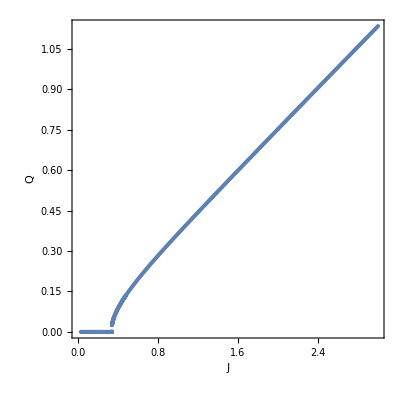
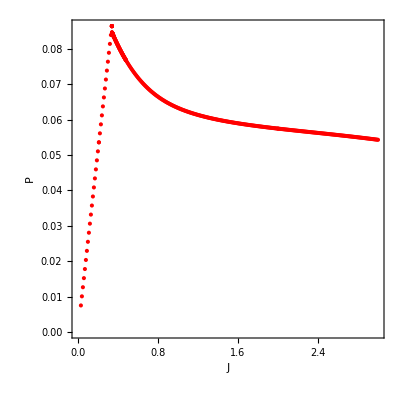
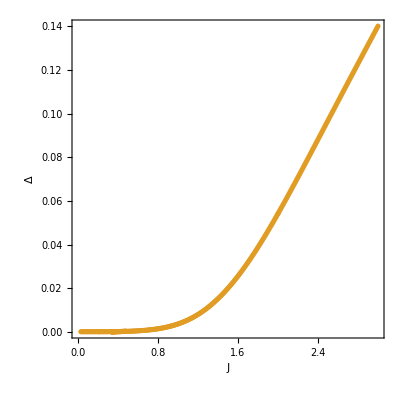
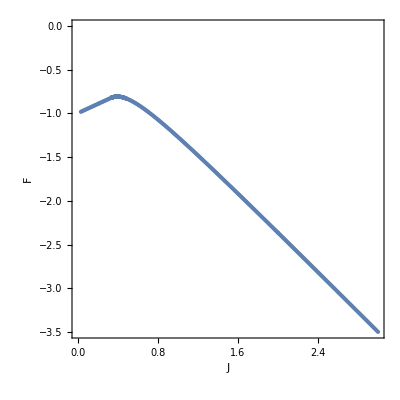

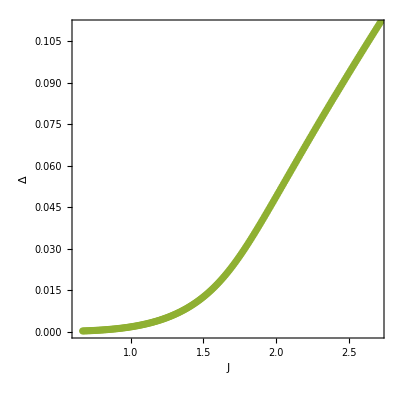
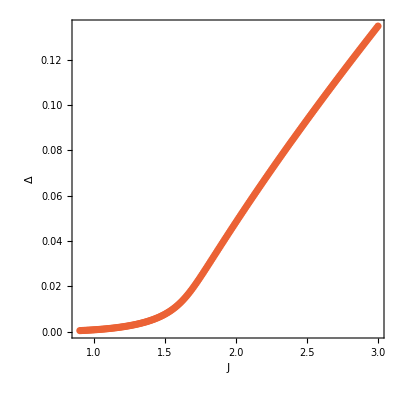
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

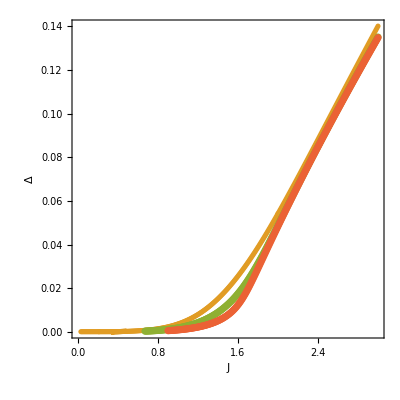

```mathematica
dataF
```

{{2.,-2.36483},{2.01,-2.37609},{2.02,-2.38735},{2.03,-2.39861},{2.04,-2.40988},{2.05,-2.42115},{2.06,-2.43242},{2.07,-2.44369},{2.08,-2.45497},{2.09,-2.46624},{2.1,-2.47752},{2.11,-2.48881},{2.12,-2.50009},{2.13,-2.51138},{2.14,-2.52267},{2.15,-2.53396},{2.16,-2.54526},{2.17,-2.55655},{2.18,-2.56785},{2.19,-2.57915},{2.2,-2.59045},{2.21,-2.60176},{2.22,-2.61307},{2.23,-2.62437},{2.24,-2.63569},{2.25,-2.647},{2.26,-2.65831},{2.27,-2.66963},{2.28,-2.68095},{2.29,-2.69227},{2.3,-2.70359},{2.31,-2.71491},{2.32,-2.72624},{2.33,-2.73756},{2.34,-2.74889},{2.35,-2.76022},{2.36,-2.77156},{2.37,-2.78289},{2.38,-2.79422},{2.39,-2.80556},{2.4,-2.8169},{2.41,-2.82824},{2.42,-2.83958},{2.43,-2.85092},{2.44,-2.86227},{2.45,-2.87361},{2.46,-2.88496},{2.47,-2.89631},{2.48,-2.90766},{2.49,-2.91901},{2.5,-2.93036},{2.51,-2.94172},{2.52,-2.95307},{2.53,-2.96443},{2.54,-2.97579},{2.55,-2.98715},{2.56,-2.99851},{2.57,-3.00987},{2.58,-3.02123},{2.59,-3.0326},{2.6,-3.04397},{2.61,-3.05533},{2.62,-3.0667},{2.63,-3.07807},{2.64,-3.08944},{2.65,-3.10081},{2.66,-3.11218},{2.67,-3.12356},{2.68,-3.13493},{2.69,-3.14631},{2.7,-3.15769},{2.71,-3.16907},{2.72,-3.18044},{2.73,-3.19183},{2.74,-3.20321},{2.75,-3.21459},{2.76,-3.22597},{2.77,-3.23736},{2.78,-3.24874},{2.79,-3.26013},{2.8,-3.27152},{2.81,-3.2829},{2.82,-3.29429},{2.83,-3.30568},{2.84,-3.31708},{2.85,-3.32847},{2.86,-3.33986},{2.87,-3.35125},{2.88,-3.36265},{2.89,-3.37405},{2.9,-3.38544},{2.91,-3.39684},{2.92,-3.40824},{2.93,-3.41964},{2.94,-3.43104},{2.95,-3.44244},{2.96,-3.45384},{2.97,-3.46524},{2.98,-3.47664},{2.99,-3.48805},{3.,-3.49945},{2.,-2.36483},{1.99,-2.35358},{1.98,-2.34232},{1.97,-2.33108},{1.96,-2.31983},{1.95,-2.30859},{1.94,-2.29735},{1.93,-2.28611},{1.92,-2.27487},{1.91,-2.26364},{1.9,-2.25241},{1.89,-2.24119},{1.88,-2.22997},{1.87,-2.21875},{1.86,-2.20754},{1.85,-2.19633},{1.84,-2.18512},{1.83,-2.17391},{1.82,-2.16271},{1.81,-2.15152},{1.8,-2.14032},{1.79,-2.12914},{1.78,-2.11795},{1.77,-2.10677},{1.76,-2.09559},{1.75,-2.08442},{1.74,-2.07325},{1.73,-2.06209},{1.72,-2.05093},{1.71,-2.03978},{1.7,-2.02863},{1.69,-2.01748},{1.68,-2.00634},{1.67,-1.9952},{1.66,-1.98407},{1.65,-1.97295},{1.64,-1.96183},{1.63,-1.95071},{1.62,-1.9396},{1.61,-1.9285},{1.6,-1.9174},{1.59,-1.9063},{1.58,-1.89522},{1.57,-1.88414},{1.56,-1.87306},{1.55,-1.86199},{1.54,-1.85093},{1.53,-1.83987},{1.52,-1.82883},{1.51,-1.81778},{1.5,-1.80675},{1.49,-1.79572},{1.48,-1.7847},{1.47,-1.77368},{1.46,-1.76268},{1.45,-1.75168},{1.44,-1.74069},{1.43,-1.72971},{1.42,-1.71873},{1.41,-1.70777},{1.4,-1.69681},{1.39,-1.68587},{1.38,-1.67493},{1.37,-1.664},{1.36,-1.65308},{1.35,-1.64217},{1.34,-1.63127},{1.33,-1.62038},{1.32,-1.60951},{1.31,-1.59864},{1.3,-1.58778},{1.29,-1.57694},{1.28,-1.56611},{1.27,-1.55529},{1.26,-1.54448},{1.25,-1.53368},{1.24,-1.5229},{1.23,-1.51214},{1.22,-1.50138},{1.21,-1.49064},{1.2,-1.47992},{1.19,-1.46921},{1.18,-1.45851},{1.17,-1.44784},{1.16,-1.43717},{1.15,-1.42653},{1.14,-1.4159},{1.13,-1.4053},{1.12,-1.39471},{1.11,-1.38414},{1.1,-1.37358},{1.09,-1.36305},{1.08,-1.35255},{1.07,-1.34206},{1.06,-1.33159},{1.05,-1.32115},{1.04,-1.31074},{1.03,-1.30035},{1.02,-1.28998},{1.01,-1.27964},{1.,-1.26933},{0.99,-1.25904},{0.98,-1.24879},{0.97,-1.23857},{0.96,-1.22838},{0.95,-1.21822},{0.94,-1.2081},{0.93,-1.19801},{0.92,-1.18796},{0.91,-1.17794},{0.9,-1.16797},{0.89,-1.15804},{0.88,-1.14815},{0.87,-1.13831},{0.86,-1.12851},{0.85,-1.11876},{0.84,-1.10906},{0.83,-1.09942},{0.82,-1.08983},{0.81,-1.08029},{0.8,-1.07082},{0.79,-1.06141},{0.78,-1.05207},{0.77,-1.04279},{0.76,-1.03358},{0.75,-1.02445},{0.74,-1.0154},{0.73,-1.00643},{0.72,-0.997551},{0.71,-0.988758},{0.7,-0.980061},{0.69,-0.971463},{0.68,-0.962969},{0.67,-0.954587},{0.66,-0.94632},{0.65,-0.938175},{0.64,-0.930159},{0.63,-0.922279},{0.62,-0.914543},{0.61,-0.906958},{0.6,-0.899533},{0.59,-0.892277},{0.58,-0.8852},{0.57,-0.878313},{0.56,-0.871628},{0.55,-0.865156},{0.54,-0.858912},{0.53,-0.852908},{0.52,-0.847162},{0.51,-0.841689},{0.5,-0.836508},{0.49,-0.831638},{0.48,-0.827101},{0.48,-0.827101},{0.48,-0.827101},{0.478,-0.826236},{0.476,-0.825385},{0.474,-0.824548},{0.472,-0.823727},{0.47,-0.82292},{0.468,-0.822129},{0.466,-0.821353},{0.464,-0.820593},{0.462,-0.819849},{0.46,-0.819121},{0.458,-0.81841},{0.456,-0.817715},{0.454,-0.817036},{0.452,-0.816375},{0.45,-0.815731},{0.448,-0.815105},{0.446,-0.814497},{0.444,-0.813906},{0.442,-0.813334},{0.44,-0.812781},{0.438,-0.812247},{0.436,-0.811731},{0.434,-0.811236},{0.432,-0.81076},{0.43,-0.810304},{0.428,-0.809868},{0.426,-0.809453},{0.424,-0.809059},{0.422,-0.808686},{0.42,-0.808335},{0.418,-0.808006},{0.416,-0.807699},{0.414,-0.807415},{0.412,-0.807154},{0.41,-0.806916},{0.408,-0.806702},{0.406,-0.806512},{0.404,-0.806347},{0.402,-0.806206},{0.4,-0.806091},{0.398,-0.806001},{0.396,-0.805938},{0.394,-0.805901},{0.392,-0.80589},{0.39,-0.805908},{0.388,-0.805953},{0.386,-0.806026},{0.384,-0.806129},{0.382,-0.80626},{0.38,-0.806421},{0.378,-0.806613},{0.376,-0.806835},{0.374,-0.807088},{0.372,-0.807373},{0.37,-0.807691},{0.368,-0.808042},{0.366,-0.808426},{0.364,-0.808844},{0.362,-0.809297},{0.36,-0.809785},{0.358,-0.810309},{0.358,-0.810309},{0.358,-0.810309},{0.357,-0.810584},{0.356,-0.810869},{0.355,-0.811163},{0.354,-0.811467},{0.353,-0.81178},{0.352,-0.812102},{0.351,-0.812435},{0.35,-0.812777},{0.349,-0.813128},{0.348,-0.81349},{0.347,-0.813862},{0.346,-0.814243},{0.346,-0.814243},{0.3455,-0.814438},{0.345,-0.814635},{0.3445,-0.814835},{0.344,-0.815037},{0.3435,-0.815242},{0.343,-0.81545},{0.3425,-0.81566},{0.342,-0.815873},{0.3415,-0.816088},{0.341,-0.816306},{0.3405,-0.816527},{0.34,-0.816751},{0.3395,-0.816977},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.329,-0.82225},{0.319,-0.827466},{0.309,-0.832686},{0.299,-0.837912},{0.289,-0.843142},{0.279,-0.848377},{0.269,-0.853616},{0.259,-0.85886},{0.249,-0.864107},{0.239,-0.869359},{0.229,-0.874615},{0.219,-0.879875},{0.209,-0.885138},{0.209,-0.885138},{0.199,-0.890406},{0.189,-0.895677},{0.179,-0.900951},{0.169,-0.906229},{0.159,-0.911511},{0.149,-0.916795},{0.139,-0.922083},{0.129,-0.927374},{0.119,-0.932669},{0.109,-0.937966},{0.099,-0.943266},{0.089,-0.94857},{0.079,-0.953876},{0.069,-0.959185},{0.059,-0.964497},{0.049,-0.969811},{0.039,-0.975129},{0.029,-0.980448}}

```mathematica
dataF
```

{{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.339,-0.817039},{0.329,-0.82225},{0.319,-0.827466},{0.309,-0.832686},{0.299,-0.837912},{0.289,-0.843142},{0.279,-0.848377},{0.269,-0.853616},{0.259,-0.85886},{0.249,-0.864107},{0.239,-0.869359},{0.229,-0.874615},{0.219,-0.879875},{0.209,-0.885138},{0.209,-0.885138},{0.199,-0.890406},{0.189,-0.895677},{0.179,-0.900951},{0.169,-0.906229},{0.159,-0.911511},{0.149,-0.916795},{0.139,-0.922083},{0.129,-0.927374},{0.119,-0.932669},{0.109,-0.937966},{0.099,-0.943266},{0.089,-0.94857},{0.079,-0.953876},{0.069,-0.959185},{0.059,-0.964497},{0.049,-0.969811},{0.039,-0.975129},{0.029,-0.980448},{0.229,-0.874615},{0.239,-0.869359},{0.249,-0.864107},{0.259,-0.85886},{0.269,-0.853616},{0.279,-0.848377},{0.289,-0.843142},{0.299,-0.837912},{0.309,-0.832686},{0.319,-0.827466},{0.329,-0.82225},{0.339,-0.817039},{0.349,-0.811834},{0.359,-0.806634},{0.369,-0.80144},{0.379,-0.796251},{0.389,-0.791069},{0.399,-0.785893},{0.409,-0.780723},{0.419,-0.77556},{0.429,-0.770403},{0.439,-0.765254},{0.449,-0.760113},{0.459,-0.754979},{0.469,-0.749853},{0.479,-0.744736},{0.489,-0.739627},{0.499,-0.734528},{0.509,-0.729438},{0.519,-0.724358},{0.529,-0.719289},{0.539,-0.71423},{0.549,-0.709183},{0.559,-0.704148},{0.569,-0.699126},{0.579,-0.694116},{0.589,-0.689121},{0.599,-0.684141},{0.599,-0.684141},{0.599,-0.684141},{0.609,-0.679176},{0.619,-0.674227},{0.629,-0.669295},{0.639,-0.664381},{0.649,-0.659487},{0.659,-0.654613},{0.669,-0.64976},{0.679,-0.644929},{0.689,-0.640122},{0.699,-0.63534},{0.709,-0.630584},{0.719,-0.625855},{0.729,-0.621156},{0.739,-0.616486},{0.749,-0.611849},{0.759,-0.607245},{0.769,-0.602675},{0.779,-0.598141},{0.789,-0.593644},{0.799,-0.589186},{0.809,-0.584767},{0.819,-0.580389},{0.829,-0.576052},{0.839,-0.571759},{0.849,-0.567508},{0.859,-0.563302},{0.869,-0.559141},{0.879,-0.555025},{0.889,-0.550956},{0.899,-0.546933},{0.909,-0.542957},{0.919,-0.539028},{0.929,-0.535147},{0.939,-0.531313},{0.949,-0.527526},{0.959,-0.523787},{0.969,-0.520095},{0.979,-0.51645},{0.989,-0.512852},{0.999,-0.509301},{1.009,-0.505797},{1.019,-0.502338},{1.029,-0.498926},{1.039,-0.495558},{1.049,-0.492236},{1.059,-0.488958},{1.069,-0.485724},{1.079,-0.482534},{1.089,-0.479387},{1.099,-0.476283},{1.109,-0.47322},{1.119,-0.470199},{1.129,-0.467219},{1.139,-0.46428},{1.149,-0.46138},{1.159,-0.45852},{1.169,-0.455698},{1.179,-0.452915},{1.189,-0.450169},{1.199,-0.44746},{1.209,-0.444788},{1.219,-0.442152},{1.229,-0.439551},{1.239,-0.436985},{1.249,-0.434453},{1.259,-0.431956},{1.269,-0.429491},{1.279,-0.427059},{1.289,-0.424659},{1.299,-0.42229},{1.309,-0.419953},{1.319,-0.417646},{1.329,-0.415369},{1.339,-0.413122},{1.349,-0.410903},{1.359,-0.408714},{1.369,-0.406552},{1.379,-0.404418},{1.389,-0.402311},{1.399,-0.400231},{1.409,-0.398176},{1.419,-0.396148},{1.429,-0.394145},{1.439,-0.392167},{1.449,-0.390213},{1.459,-0.388284},{1.469,-0.386378},{1.479,-0.384495},{1.489,-0.382635},{1.499,-0.380798},{1.499,-0.380798},{1.509,-0.378983},{1.519,-0.377189},{1.529,-0.375417},{1.539,-0.373666},{1.549,-0.371936},{1.559,-0.370225},{1.569,-0.368535},{1.579,-0.366865},{1.589,-0.365214},{1.599,-0.363582},{1.609,-0.361968},{1.619,-0.360373},{1.629,-0.358796},{1.639,-0.357237},{1.649,-0.355696},{1.659,-0.354171},{1.669,-0.352664},{1.679,-0.351173},{1.689,-0.349699},{1.699,-0.348241},{1.709,-0.346799},{1.719,-0.345372},{1.729,-0.343961},{1.739,-0.342566},{1.749,-0.341185},{1.759,-0.339818},{1.769,-0.338467},{1.779,-0.337129},{1.789,-0.335806},{1.799,-0.334496},{1.809,-0.3332},{1.819,-0.331918},{1.829,-0.330649},{1.839,-0.329392},{1.849,-0.328149},{1.859,-0.326918},{1.869,-0.3257},{1.879,-0.324494},{1.889,-0.3233},{1.899,-0.322117},{1.909,-0.320947},{1.919,-0.319788},{1.929,-0.318641},{1.939,-0.317505},{1.949,-0.316379},{1.959,-0.315265},{1.969,-0.314162},{1.979,-0.313069},{1.989,-0.311987},{1.999,-0.310914},{2.009,-0.309853},{2.019,-0.308801},{2.029,-0.307759},{2.039,-0.306726},{2.049,-0.305704},{2.059,-0.304691},{2.069,-0.303687},{2.079,-0.302692},{2.089,-0.301707},{2.099,-0.30073},{2.109,-0.299763},{2.119,-0.298804},{2.129,-0.297853},{2.139,-0.296912},{2.149,-0.295978},{2.159,-0.295053},{2.169,-0.294136},{2.179,-0.293228},{2.189,-0.292327},{2.199,-0.291434},{2.209,-0.290549},{2.219,-0.289671},{2.229,-0.288801},{2.239,-0.287939},{2.249,-0.287083},{2.259,-0.286236},{2.269,-0.285395},{2.279,-0.284561},{2.289,-0.283735},{2.299,-0.282915},{2.309,-0.282102},{2.319,-0.281296},{2.329,-0.280497},{2.339,-0.279704},{2.349,-0.278918},{2.359,-0.278138},{2.369,-0.277365},{2.379,-0.276598},{2.389,-0.275837},{2.399,-0.275082},{2.409,-0.274333},{2.419,-0.27359},{2.429,-0.272853},{2.439,-0.272122},{2.449,-0.271397},{2.459,-0.270677},{2.469,-0.269963},{2.479,-0.269255},{2.489,-0.268552},{2.499,-0.267855},{2.509,-0.267163},{2.519,-0.266476},{2.529,-0.265794},{2.539,-0.265118},{2.549,-0.264447},{2.559,-0.263781},{2.569,-0.26312},{2.579,-0.262464},{2.589,-0.261813},{2.599,-0.261167},{2.609,-0.260525},{2.619,-0.259888},{2.629,-0.259256},{2.639,-0.258629},{2.649,-0.258006},{2.659,-0.257388},{2.669,-0.256774},{2.679,-0.256165},{2.689,-0.25556},{2.699,-0.25496},{2.709,-0.254364},{2.719,-0.253772},{2.729,-0.253184},{2.739,-0.252601},{2.749,-0.252021},{2.759,-0.251446},{2.769,-0.250875},{2.779,-0.250307},{2.789,-0.249744},{2.799,-0.249185},{2.809,-0.248629},{2.819,-0.248078},{2.829,-0.24753},{2.839,-0.246986},{2.849,-0.246445},{2.859,-0.245909},{2.869,-0.245376},{2.879,-0.244846},{2.889,-0.24432},{2.899,-0.243798},{2.909,-0.243279},{2.919,-0.242764},{2.929,-0.242252},{2.939,-0.241743},{2.949,-0.241238},{2.959,-0.240736},{2.969,-0.240238},{2.979,-0.239743},{2.989,-0.239251},{2.999,-0.238762}}

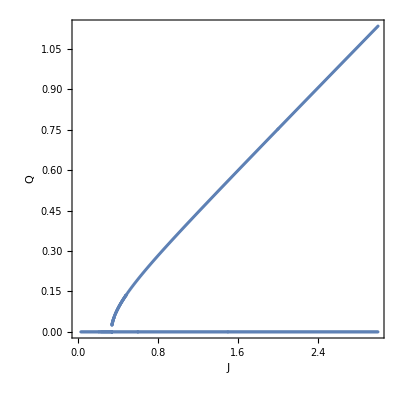
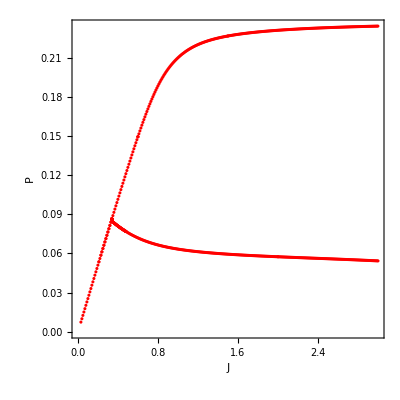
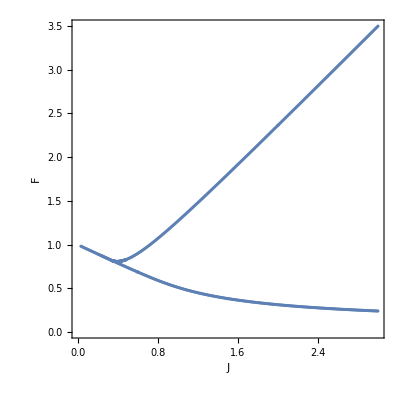
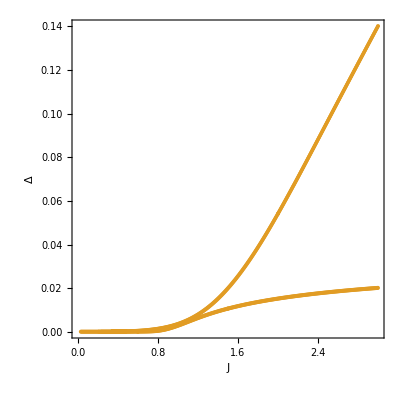

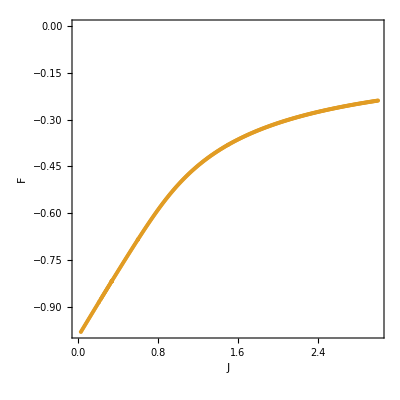
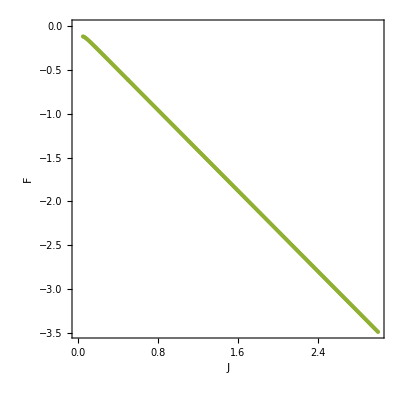
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

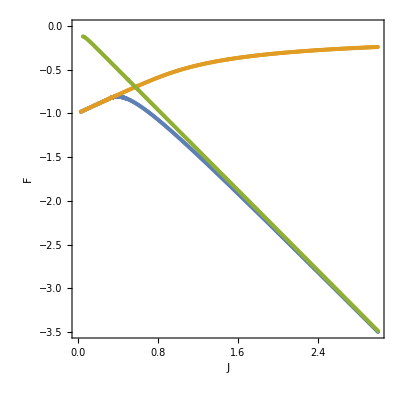

P=0 T=0.02

```mathematica
data
```

{{0.5,{0.553645,0.5217,0.189548,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.531847}},{0.51,{0.564385,0.532428,0.193342,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.542578}},{0.52,{0.575125,0.543156,0.197135,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.55331}},{0.53,{0.585865,0.553885,0.200929,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.564042}},{0.54,{0.596605,0.564614,0.204723,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.574774}},{0.55,{0.607344,0.575344,0.208516,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.585507}},{0.56,{0.618084,0.586074,0.21231,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.59624}},{0.57,{0.628823,0.596805,0.216103,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.606973}},{0.58,{0.639562,0.607536,0.219896,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.617706}},{0.59,{0.650301,0.618267,0.22369,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.62844}},{0.6,{0.66104,0.628999,0.227483,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.639173}},{0.61,{0.671779,0.639731,0.231276,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.649908}},{0.62,{0.682518,0.650464,0.235069,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.660642}},{0.63,{0.693257,0.661197,0.238862,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.671376}},{0.64,{0.703996,0.67193,0.242654,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.682111}},{0.65,{0.714734,0.682663,0.246447,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.692846}},{0.66,{0.725473,0.693397,0.25024,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.703581}},{0.67,{0.736212,0.704131,0.254033,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.714316}},{0.68,{0.74695,0.714865,0.257825,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.725052}},{0.69,{0.757689,0.725599,0.261618,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.735787}},{0.7,{0.768428,0.736334,0.265411,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.746523}},{0.71,{0.779167,0.747068,0.269203,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.757259}},{0.72,{0.789905,0.757803,0.272996,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.767995}},{0.73,{0.800644,0.768539,0.276788,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.778731}},{0.74,{0.811383,0.779274,0.280581,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.789468}},{0.75,{0.822122,0.79001,0.284373,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.800204}},{0.76,{0.832861,0.800746,0.288166,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.810941}},{0.77,{0.8436,0.811482,0.291958,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.821678}},{0.78,{0.854339,0.822218,0.29575,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.832415}},{0.79,{0.865078,0.832954,0.299543,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.843152}},{0.8,{0.875817,0.843691,0.303335,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.853889}},{0.81,{0.886556,0.854427,0.307127,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.864627}},{0.82,{0.897295,0.865164,0.31092,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.875364}},{0.83,{0.908034,0.875901,0.314712,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.886102}},{0.84,{0.918773,0.886638,0.318504,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.896839}},{0.85,{0.929512,0.897375,0.322296,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.907577}},{0.86,{0.940252,0.908113,0.326088,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.918315}},{0.87,{0.950991,0.91885,0.329881,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.929053}},{0.88,{0.96173,0.929588,0.333673,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.939791}},{0.89,{0.97247,0.940326,0.337465,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.950529}},{0.9,{0.983209,0.951064,0.341257,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.961268}},{0.91,{0.993949,0.961801,0.345049,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.972006}},{0.92,{1.00469,0.97254,0.348841,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.982745}},{0.93,{1.01543,0.983278,0.352634,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.993483}},{0.94,{1.02617,0.994016,0.356426,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.00422}},{0.95,{1.03691,1.00475,0.360218,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.01496}},{0.96,{1.04765,1.01549,0.36401,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.0257}},{0.97,{1.05839,1.02623,0.367802,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.03644}},{0.98,{1.06913,1.03697,0.371594,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.04718}},{0.99,{1.07987,1.04771,0.375386,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.05792}},{1.,{1.09061,1.05845,0.379178,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.06866}},{1.01,{1.10135,1.06919,0.38297,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.0794}},{1.02,{1.11209,1.07993,0.386762,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.09014}},{1.03,{1.12283,1.09067,0.390555,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.10088}},{1.04,{1.13357,1.10141,0.394346,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.11161}},{1.05,{1.14431,1.11215,0.398138,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.12235}},{1.06,{1.15505,1.12288,0.40193,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.13309}},{1.07,{1.16579,1.13363,0.405724,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.14384}},{1.08,{1.17653,1.14436,0.409515,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.15457}},{1.09,{1.18727,1.1551,0.413306,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.16531}},{1.1,{1.19801,1.16584,0.417099,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.17605}},{1.11,{1.20876,1.17659,0.420892,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.1868}},{1.12,{1.21949,1.18732,0.424683,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.19753}},{1.13,{1.23023,1.19806,0.428474,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.20827}},{1.14,{1.24097,1.2088,0.432266,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.21901}},{1.15,{1.25172,1.21955,0.43606,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.22976}},{1.16,{1.26245,1.23028,0.43985,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.24049}},{1.17,{1.27319,1.24102,0.443642,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.25123}},{1.18,{1.28394,1.25176,0.447434,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.26198}},{1.19,{1.29468,1.2625,0.451226,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.27272}},{1.2,{1.30542,1.27324,0.455018,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.28346}},{1.21,{1.31616,1.28399,0.45881,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.2942}},{1.22,{1.3269,1.29473,0.462602,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.30494}},{1.23,{1.33764,1.30547,0.466395,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.31568}},{1.24,{1.34838,1.31621,0.470186,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.32642}},{1.25,{1.35912,1.32695,0.473977,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.33716}},{1.26,{1.36986,1.33769,0.47777,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.3479}},{1.27,{1.38061,1.34843,0.481563,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.35865}},{1.28,{1.39135,1.35917,0.485354,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.36938}},{1.29,{1.40209,1.36991,0.489146,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.38012}},{1.3,{1.41283,1.38065,0.492938,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.39087}},{1.31,{1.42357,1.39139,0.49673,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.40161}},{1.32,{1.43431,1.40213,0.500522,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.41235}},{1.33,{1.44505,1.41288,0.504314,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.42309}},{1.34,{1.4558,1.42362,0.508106,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.43383}},{1.35,{1.46654,1.43436,0.511897,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.44457}},{1.36,{1.47728,1.4451,0.515689,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.45531}},{1.37,{1.48802,1.45584,0.519481,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.46606}},{1.38,{1.49876,1.46658,0.523273,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.4768}},{1.39,{1.5095,1.47732,0.527065,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.48754}},{1.4,{1.52025,1.48807,0.530857,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.49828}},{1.41,{1.53099,1.49881,0.534649,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.50902}},{1.42,{1.54173,1.50955,0.538441,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.51976}},{1.43,{1.55247,1.52029,0.542232,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.5305}},{1.44,{1.56321,1.53103,0.546025,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.54125}},{1.45,{1.57396,1.54177,0.549817,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.55199}},{1.46,{1.5847,1.55251,0.553609,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.56273}},{1.47,{1.59544,1.56326,0.5574,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.57347}},{1.48,{1.60618,1.574,0.561192,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.58421}},{1.49,{1.61693,1.58474,0.564985,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.59496}},{1.5,{1.62766,1.59548,0.568776,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.6057}},{1.51,{1.63841,1.60622,0.572568,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.61644}},{1.52,{1.64915,1.61697,0.57636,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.62718}},{1.53,{1.65989,1.62771,0.580152,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.63792}},{1.54,{1.67063,1.63845,0.583944,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.64866}},{1.55,{1.68138,1.64919,0.587736,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.65941}},{1.56,{1.69212,1.65993,0.591528,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.67015}},{1.57,{1.70286,1.67067,0.595319,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.68089}},{1.58,{1.7136,1.68142,0.599111,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.69163}},{1.59,{1.72434,1.69216,0.602903,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.70238}},{1.6,{1.73509,1.7029,0.606695,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.71312}},{1.61,{1.74583,1.71364,0.610487,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.72386}},{1.62,{1.75657,1.72439,0.614279,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.7346}},{1.63,{1.76731,1.73513,0.618071,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.74534}},{1.64,{1.77806,1.74587,0.621863,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.75609}},{1.65,{1.7888,1.75661,0.625655,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.76683}},{1.66,{1.79954,1.76736,0.629446,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.77757}},{1.67,{1.81028,1.7781,0.633238,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.78831}},{1.68,{1.82103,1.78884,0.63703,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.79906}},{1.69,{1.83177,1.79959,0.640824,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.8098}},{1.7,{1.84251,1.81033,0.644614,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.82054}},{1.71,{1.85325,1.82107,0.648406,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.83128}},{1.72,{1.864,1.83181,0.652198,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.84203}},{1.73,{1.87474,1.84256,0.655991,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.85277}},{1.74,{1.88548,1.8533,0.659782,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.86351}},{1.75,{1.89622,1.86404,0.663572,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.87425}},{1.76,{1.90697,1.87478,0.667365,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.885}},{1.77,{1.91771,1.88552,0.671156,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.89574}},{1.78,{1.92845,1.89627,0.674949,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.90648}},{1.79,{1.9392,1.90701,0.678741,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.91723}},{1.8,{1.94994,1.91775,0.682533,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.92797}},{1.81,{1.96068,1.92849,0.686324,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.93871}},{1.82,{1.97142,1.93924,0.690117,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.94945}},{1.83,{1.98216,1.94998,0.693908,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.96019}},{1.84,{1.99291,1.96072,0.6977,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.97094}},{1.85,{2.00365,1.97146,0.701491,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.98168}},{1.86,{2.01439,1.98221,0.705284,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.99242}},{1.87,{2.02514,1.99295,0.709076,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.00317}},{1.88,{2.03588,2.00369,0.712868,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.01391}},{1.89,{2.04664,2.01445,0.716665,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.02467}},{1.9,{2.05737,2.02518,0.720452,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.0354}},{1.91,{2.06811,2.03592,0.724244,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.04614}},{1.92,{2.07885,2.04666,0.728035,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.05688}},{1.93,{2.0896,2.05741,0.731828,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.06763}},{1.94,{2.10034,2.06815,0.735619,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.07837}},{1.95,{2.11108,2.07889,0.739411,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.08911}},{1.96,{2.12182,2.08964,0.743203,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.09985}},{1.97,{2.13257,2.10038,0.746995,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.1106}},{1.98,{2.14331,2.11112,0.750786,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.12134}},{1.99,{2.15405,2.12186,0.754577,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.13208}},{2.,{2.1648,2.13261,0.75837,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.14282}},{2.01,{2.17554,2.14335,0.762164,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.15357}},{2.02,{2.18628,2.15409,0.765954,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.16431}},{2.03,{2.19702,2.16484,0.769746,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.17505}},{2.04,{2.20777,2.17558,0.773538,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.1858}},{2.05,{2.21851,2.18632,0.77733,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.19654}},{2.06,{2.22925,2.19707,0.781121,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.20728}},{2.07,{2.23999,2.2078,0.78491,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.21802}},{2.08,{2.25074,2.21855,0.788705,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.22877}},{2.09,{2.26148,2.2293,0.792498,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.23951}},{2.1,{2.27223,2.24004,0.796289,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.25025}},{2.11,{2.28298,2.25079,0.800084,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.26101}},{2.12,{2.29371,2.26152,0.803873,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.27174}},{2.13,{2.30446,2.27227,0.807665,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.28249}},{2.14,{2.3152,2.28301,0.811456,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.29323}},{2.15,{2.32594,2.29375,0.815247,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.30397}},{2.16,{2.33668,2.3045,0.81904,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.31471}},{2.17,{2.34743,2.31524,0.822832,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.32546}},{2.18,{2.35817,2.32598,0.826624,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.3362}},{2.19,{2.36891,2.33673,0.830416,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.34694}},{2.2,{2.37966,2.34747,0.834208,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.35769}},{2.21,{2.3904,2.35821,0.837999,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.36843}},{2.22,{2.40114,2.36896,0.841791,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.37917}},{2.23,{2.41189,2.3797,0.845584,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.38992}},{2.24,{2.42263,2.39044,0.849375,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.40066}},{2.25,{2.43337,2.40119,0.853167,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.4114}},{2.26,{2.44412,2.41193,0.856959,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.42214}},{2.27,{2.45486,2.42267,0.86075,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.43289}},{2.28,{2.4656,2.43341,0.864542,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.44363}},{2.29,{2.47634,2.44416,0.868333,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.45437}},{2.3,{2.48709,2.4549,0.872126,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.46512}},{2.31,{2.49783,2.46564,0.875918,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.47586}},{2.32,{2.50858,2.47639,0.87971,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.4866}},{2.33,{2.51933,2.48714,0.883504,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.49735}},{2.34,{2.53006,2.49787,0.887294,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.50809}},{2.35,{2.5408,2.50862,0.891085,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.51883}},{2.36,{2.55155,2.51936,0.894877,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.52958}},{2.37,{2.56229,2.5301,0.898668,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.54032}},{2.38,{2.57304,2.54085,0.902461,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.55106}},{2.39,{2.58378,2.55159,0.906253,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.56181}},{2.4,{2.59452,2.56233,0.910045,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.57255}},{2.41,{2.60526,2.57308,0.913837,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.58329}},{2.42,{2.61601,2.58382,0.917628,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.59404}},{2.43,{2.62675,2.59456,0.921419,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.60478}},{2.44,{2.63749,2.60531,0.925212,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.61552}},{2.45,{2.64824,2.61605,0.929003,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.62626}},{2.46,{2.65898,2.62679,0.932796,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.63701}},{2.47,{2.66972,2.63753,0.936586,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.64775}},{2.48,{2.68047,2.64828,0.94038,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.6585}},{2.49,{2.69121,2.65902,0.94417,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.66924}},{2.5,{2.70195,2.66977,0.947963,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.67998}},{2.51,{2.7127,2.68051,0.951757,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.69073}},{2.52,{2.72344,2.69125,0.955547,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.70147}},{2.53,{2.73416,2.70197,0.95933,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.71219}},{2.54,{2.74493,2.71274,0.963131,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.72296}},{2.55,{2.75569,2.7235,0.96693,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.73372}},{2.56,{2.76641,2.73423,0.970714,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.74444}},{2.57,{2.77717,2.74498,0.97451,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.75519}},{2.58,{2.7879,2.75571,0.978298,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.76593}},{2.59,{2.79865,2.76646,0.982092,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.77668}},{2.6,{2.80939,2.7772,0.985882,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.78742}},{2.61,{2.82013,2.78794,0.989674,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.79816}},{2.62,{2.83087,2.79869,0.993466,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.8089}},{2.63,{2.84162,2.80943,0.997257,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.81965}},{2.64,{2.85236,2.82017,1.00105,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.83039}},{2.65,{2.8631,2.83091,1.00484,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.84113}},{2.66,{2.87385,2.84166,1.00863,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.85188}},{2.67,{2.88459,2.8524,1.01242,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.86261}},{2.68,{2.89533,2.86315,1.01622,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.87336}},{2.69,{2.90609,2.8739,1.02001,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.88412}},{2.7,{2.91682,2.88463,1.0238,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.89485}},{2.71,{2.92757,2.89538,1.02759,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.90559}},{2.72,{2.93831,2.90612,1.03138,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.91634}},{2.73,{2.94905,2.91686,1.03518,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.92708}},{2.74,{2.95979,2.92761,1.03897,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.93782}},{2.75,{2.97054,2.93835,1.04276,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.94856}},{2.76,{2.98128,2.94909,1.04655,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.95931}},{2.77,{2.99203,2.95984,1.05034,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.97005}},{2.78,{3.00277,2.97058,1.05414,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.9808}},{2.79,{3.01351,2.98132,1.05793,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.99154}},{2.8,{3.02425,2.99207,1.06172,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.00228}},{2.81,{3.035,3.00281,1.06551,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.01303}},{2.82,{3.04574,3.01355,1.0693,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.02377}},{2.83,{3.05649,3.0243,1.0731,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.03452}},{2.84,{3.06723,3.03504,1.07689,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.04526}},{2.85,{3.07797,3.04578,1.08068,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.056}},{2.86,{3.08871,3.05653,1.08447,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.06674}},{2.87,{3.09946,3.06727,1.08826,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.07749}},{2.88,{3.1102,3.07801,1.09205,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.08823}},{2.89,{3.12095,3.08876,1.09585,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.09897}},{2.9,{3.13169,3.0995,1.09964,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.10972}},{2.91,{3.14243,3.11024,1.10343,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.12045}},{2.92,{3.15318,3.12099,1.10722,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.1312}},{2.93,{3.16392,3.13173,1.11101,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.14195}},{2.94,{3.17466,3.14247,1.1148,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.15269}},{2.95,{3.18541,3.15322,1.1186,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.16343}},{2.96,{3.19615,3.16396,1.12239,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.17418}},{2.97,{3.20689,3.1747,1.12618,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.18492}},{2.98,{3.21764,3.18545,1.12997,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.19566}},{2.99,{3.22838,3.19619,1.13376,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.20641}},{3.,{3.23912,3.20693,1.13756,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.21715}},{0.5,{0.553645,0.5217,0.189548,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.531847}},{0.49,{0.542904,0.510973,0.185753,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.521116}},{0.48,{0.532163,0.500246,0.181959,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.510385}},{0.47,{0.521421,0.48952,0.178165,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.499654}},{0.46,{0.510679,0.478795,0.17437,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.488924}},{0.45,{0.499937,0.468071,0.170575,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.478195}},{0.44,{0.489194,0.457347,0.16678,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.467466}},{0.43,{0.47845,0.446624,0.162985,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.456737}},{0.42,{0.467706,0.435902,0.159189,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.446009}},{0.41,{0.456961,0.425181,0.155393,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.435281}},{0.4,{0.446215,0.414462,0.151597,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.424553}},{0.39,{0.435467,0.403743,0.1478,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.413827}},{0.38,{0.424719,0.393026,0.144003,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.4031}},{0.37,{0.413969,0.38231,0.140206,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.392374}},{0.36,{0.403218,0.371595,0.136408,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.381649}},{0.35,{0.392464,0.360882,0.13261,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.370925}},{0.34,{0.381709,0.350171,0.12881,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.360201}},{0.33,{0.37095,0.339461,0.125011,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.349477}},{0.32,{0.36019,0.328754,0.12121,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.338754}},{0.31,{0.349425,0.318048,0.117408,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.328032}},{0.3,{0.338657,0.307345,0.113606,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.31731}},{0.29,{0.327884,0.296645,0.109802,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.306589}},{0.28,{0.317106,0.285947,0.105996,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.295868}},{0.27,{0.306321,0.275253,0.102189,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.285147}},{0.26,{0.295528,0.264562,0.0983799,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.274427}},{0.25,{0.284726,0.253874,0.0945684,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.263706}},{0.24,{0.273913,0.24319,0.090754,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.252984}},{0.23,{0.263086,0.23251,0.0869361,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.242262}},{0.22,{0.252242,0.221834,0.083114,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.231537}},{0.21,{0.241378,0.211163,0.0792867,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.22081}},{0.2,{0.230487,0.200496,0.0754529,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.210078}},{0.19,{0.219564,0.189834,0.0716109,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.199339}},{0.18,{0.2086,0.179175,0.0677586,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.188591}},{0.17,{0.197582,0.16852,0.0638929,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.17783}},{0.16,{0.186496,0.157868,0.06001,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.167049}},{0.15,{0.175319,0.147216,0.0561044,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.156242}},{0.14,{0.164025,0.136563,0.0521687,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.145398}},{0.13,{0.152575,0.125904,0.0481927,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.134502}},{0.12,{0.140916,0.115236,0.0441621,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.123535}},{0.11,{0.128979,0.104552,0.040057,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.11247}},{0.1,{0.116673,0.0938467,0.0358487,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.101272}},{0.09,{0.103876,0.0831125,0.0314952,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0898956}},{0.08,{0.0904398,0.0723448,0.0269326,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0782851}},{0.07,{0.0761927,0.0615442,0.0220546,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0663785}},{0.06,{0.0609599,0.0507212,0.0166499,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0541176}},{0.05,{0.0445889,0.0398913,0.0100765,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0414556}}}

```mathematica
dataF
```

{{0.5,-0.612936},{0.51,-0.624434},{0.52,-0.635931},{0.53,-0.647429},{0.54,-0.658927},{0.55,-0.670426},{0.56,-0.681925},{0.57,-0.693423},{0.58,-0.704923},{0.59,-0.716422},{0.6,-0.727922},{0.61,-0.739421},{0.62,-0.750921},{0.63,-0.762421},{0.64,-0.773921},{0.65,-0.785422},{0.66,-0.796922},{0.67,-0.808423},{0.68,-0.819923},{0.69,-0.831424},{0.7,-0.842925},{0.71,-0.854426},{0.72,-0.865927},{0.73,-0.877428},{0.74,-0.888929},{0.75,-0.90043},{0.76,-0.911931},{0.77,-0.923433},{0.78,-0.934934},{0.79,-0.946435},{0.8,-0.957937},{0.81,-0.969438},{0.82,-0.98094},{0.83,-0.992442},{0.84,-1.00394},{0.85,-1.01545},{0.86,-1.02695},{0.87,-1.03845},{0.88,-1.04995},{0.89,-1.06145},{0.9,-1.07295},{0.91,-1.08446},{0.92,-1.09596},{0.93,-1.10746},{0.94,-1.11896},{0.95,-1.13046},{0.96,-1.14197},{0.97,-1.15347},{0.98,-1.16497},{0.99,-1.17647},{1.,-1.18797},{1.01,-1.19948},{1.02,-1.21098},{1.03,-1.22248},{1.04,-1.23398},{1.05,-1.24548},{1.06,-1.25699},{1.07,-1.26849},{1.08,-1.27999},{1.09,-1.29149},{1.1,-1.303},{1.11,-1.3145},{1.12,-1.326},{1.13,-1.3375},{1.14,-1.349},{1.15,-1.36051},{1.16,-1.37201},{1.17,-1.38351},{1.18,-1.39501},{1.19,-1.40652},{1.2,-1.41802},{1.21,-1.42952},{1.22,-1.44102},{1.23,-1.45253},{1.24,-1.46403},{1.25,-1.47553},{1.26,-1.48703},{1.27,-1.49853},{1.28,-1.51004},{1.29,-1.52154},{1.3,-1.53304},{1.31,-1.54454},{1.32,-1.55605},{1.33,-1.56755},{1.34,-1.57905},{1.35,-1.59055},{1.36,-1.60206},{1.37,-1.61356},{1.38,-1.62506},{1.39,-1.63656},{1.4,-1.64807},{1.41,-1.65957},{1.42,-1.67107},{1.43,-1.68257},{1.44,-1.69408},{1.45,-1.70558},{1.46,-1.71708},{1.47,-1.72858},{1.48,-1.74009},{1.49,-1.75159},{1.5,-1.76309},{1.51,-1.77459},{1.52,-1.7861},{1.53,-1.7976},{1.54,-1.8091},{1.55,-1.8206},{1.56,-1.8321},{1.57,-1.84361},{1.58,-1.85511},{1.59,-1.86661},{1.6,-1.87811},{1.61,-1.88962},{1.62,-1.90112},{1.63,-1.91262},{1.64,-1.92412},{1.65,-1.93563},{1.66,-1.94713},{1.67,-1.95863},{1.68,-1.97013},{1.69,-1.98164},{1.7,-1.99314},{1.71,-2.00464},{1.72,-2.01614},{1.73,-2.02765},{1.74,-2.03915},{1.75,-2.05065},{1.76,-2.06215},{1.77,-2.07366},{1.78,-2.08516},{1.79,-2.09666},{1.8,-2.10816},{1.81,-2.11967},{1.82,-2.13117},{1.83,-2.14267},{1.84,-2.15417},{1.85,-2.16568},{1.86,-2.17718},{1.87,-2.18868},{1.88,-2.20018},{1.89,-2.21169},{1.9,-2.22319},{1.91,-2.23469},{1.92,-2.24619},{1.93,-2.2577},{1.94,-2.2692},{1.95,-2.2807},{1.96,-2.2922},{1.97,-2.30371},{1.98,-2.31521},{1.99,-2.32671},{2.,-2.33821},{2.01,-2.34972},{2.02,-2.36122},{2.03,-2.37272},{2.04,-2.38422},{2.05,-2.39573},{2.06,-2.40723},{2.07,-2.41873},{2.08,-2.43023},{2.09,-2.44174},{2.1,-2.45324},{2.11,-2.46474},{2.12,-2.47624},{2.13,-2.48775},{2.14,-2.49925},{2.15,-2.51075},{2.16,-2.52225},{2.17,-2.53376},{2.18,-2.54526},{2.19,-2.55676},{2.2,-2.56826},{2.21,-2.57977},{2.22,-2.59127},{2.23,-2.60277},{2.24,-2.61427},{2.25,-2.62578},{2.26,-2.63728},{2.27,-2.64878},{2.28,-2.66028},{2.29,-2.67179},{2.3,-2.68329},{2.31,-2.69479},{2.32,-2.70629},{2.33,-2.7178},{2.34,-2.7293},{2.35,-2.7408},{2.36,-2.7523},{2.37,-2.76381},{2.38,-2.77531},{2.39,-2.78681},{2.4,-2.79831},{2.41,-2.80982},{2.42,-2.82132},{2.43,-2.83282},{2.44,-2.84433},{2.45,-2.85583},{2.46,-2.86733},{2.47,-2.87883},{2.48,-2.89034},{2.49,-2.90184},{2.5,-2.91334},{2.51,-2.92484},{2.52,-2.93635},{2.53,-2.94785},{2.54,-2.95935},{2.55,-2.97085},{2.56,-2.98236},{2.57,-2.99386},{2.58,-3.00536},{2.59,-3.01686},{2.6,-3.02837},{2.61,-3.03987},{2.62,-3.05137},{2.63,-3.06287},{2.64,-3.07438},{2.65,-3.08588},{2.66,-3.09738},{2.67,-3.10888},{2.68,-3.12039},{2.69,-3.13189},{2.7,-3.14339},{2.71,-3.15489},{2.72,-3.1664},{2.73,-3.1779},{2.74,-3.1894},{2.75,-3.2009},{2.76,-3.21241},{2.77,-3.22391},{2.78,-3.23541},{2.79,-3.24691},{2.8,-3.25842},{2.81,-3.26992},{2.82,-3.28142},{2.83,-3.29292},{2.84,-3.30443},{2.85,-3.31593},{2.86,-3.32743},{2.87,-3.33893},{2.88,-3.35044},{2.89,-3.36194},{2.9,-3.37344},{2.91,-3.38494},{2.92,-3.39645},{2.93,-3.40795},{2.94,-3.41945},{2.95,-3.43095},{2.96,-3.44246},{2.97,-3.45396},{2.98,-3.46546},{2.99,-3.47696},{3.,-3.48847},{0.5,-0.612936},{0.49,-0.60144},{0.48,-0.589943},{0.47,-0.578447},{0.46,-0.566952},{0.45,-0.555457},{0.44,-0.543962},{0.43,-0.532469},{0.42,-0.520976},{0.41,-0.509483},{0.4,-0.497992},{0.39,-0.486502},{0.38,-0.475013},{0.37,-0.463525},{0.36,-0.452038},{0.35,-0.440553},{0.34,-0.429069},{0.33,-0.417588},{0.32,-0.406109},{0.31,-0.394632},{0.3,-0.383158},{0.29,-0.371688},{0.28,-0.360221},{0.27,-0.348759},{0.26,-0.337302},{0.25,-0.325852},{0.24,-0.314408},{0.23,-0.302973},{0.22,-0.291549},{0.21,-0.280138},{0.2,-0.268743},{0.19,-0.257367},{0.18,-0.246016},{0.17,-0.234697},{0.16,-0.223419},{0.15,-0.212195},{0.14,-0.201042},{0.13,-0.189988},{0.12,-0.179069},{0.11,-0.16834},{0.1,-0.157885},{0.09,-0.14783},{0.08,-0.138372},{0.07,-0.129827},{0.06,-0.122706},{0.05,-0.117878}}

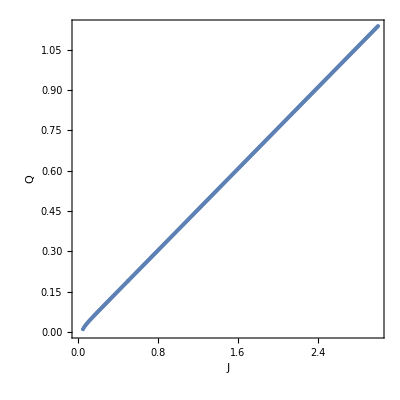
```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

#### with T

```mathematica
(*
data={};
dataF={};
*)
b={2.2262383563969825,2.1206861114365663,0.7524092848829049,0.05750174492231323,-0.20968226310215196+0. ⅈ,-2.1249921472890123};
Do[
Clear[kx,ky];
T=0.005;
Lx=Ly=L;
L=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=2;



τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];

ne=x;

evaluate:={

λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;


Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
F=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

F+=2/(Lx Ly)(T Log[1-Exp[-energy[[1]]/T]]+T Log[1-Exp[-energy[[2]]/T]]+ T Log[1-Exp[-energy[[3]]/T]])+2/(2 Lx Ly)(energy[[1]]+energy[[2]]+energy[[3]]);




order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};
(*the correct one*)
H={{λ1+μ,(2Conjugate[P1])/J Exp[ⅈ kx/2]+(2Conjugate[P3])/J Exp[-ⅈ kx/2],(2Conjugate[P2])/J Exp[ⅈ ky/2]+(2Conjugate[P4])/J Exp[-ⅈ ky/2]},{(2P1)/J Exp[-ⅈ kx/2]+(2P3)/J Exp[ⅈ kx/2],λ2+μ,0},{(2P2)/J Exp[-ⅈ ky/2]+(2P4)/J Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];


F+=-1/(Lx Ly)(T Log[1+Exp[-energy[[1]]/T]]+T Log[1+Exp[-energy[[2]]/T]]
+T Log[1+Exp[-energy[[3]]/T]]);


,{kx,-π,π-2 π/Lx,2 π/Lx},{ky,-π,π-2 π/Ly,2 π/Ly}];
F+= (+16 Q^2/(2J)- 16 P^2/(2J)-16/J P R-2 λd- 4λp- 3μ ne);
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne};

};




evaluate;

While[Abs[eqn.eqn]>10^-9,
Jac=ConstantArray[0.,{6,6}];


Print["convergence = ",Abs[eqn.eqn]];
eqn0=Chop[eqn];

δ=10^-9;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,6}];

scale=1.;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

While[(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q<0,
b-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*2;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

];



evaluate;
];
Print[b, " J = ",x];
AppendTo[data,{x,b}];
AppendTo[dataF,{x,Re[F]}]
,{x,0.51,0.7,0.01}]
```

convergence = 0.0117511

convergence = 0.000139575

convergence = 1.18958×10^-8

{2.19801,2.09551,0.741339,0.0585147,-0.217318+0. ⅈ,-2.09628} J = 0.51

convergence = 0.0001

convergence = 0.0000116043

convergence = 1.62117×10^-8

{2.16584,2.07302,0.730521,0.0582616,-0.220532+0. ⅈ,-2.07437} J = 0.52

convergence = 0.0001

convergence = 0.000014145

convergence = 2.8271×10^-8

{2.13415,2.05057,0.719708,0.0579016,-0.223441+0. ⅈ,-2.05251} J = 0.53

convergence = 0.0001

convergence = 4.83945×10^-6

{2.10293,2.02817,0.708898,0.0574451,-0.226062+0. ⅈ,-2.03072} J = 0.54

convergence = 0.000100001

convergence = 3.51659×10^-6

{2.07219,2.00583,0.698089,0.0569008,-0.228412+0. ⅈ,-2.00901} J = 0.55

convergence = 0.000100002

convergence = 2.6876×10^-6

{2.0419,1.98353,0.687277,0.056275,-0.230505+0. ⅈ,-1.98738} J = 0.56

convergence = 0.000100002

convergence = 2.21616×10^-6

{2.01204,1.96127,0.676459,0.0555736,-0.232353+0. ⅈ,-1.96582} J = 0.57

convergence = 0.000100004

convergence = 1.97741×10^-6

{1.9826,1.93905,0.665634,0.0548018,-0.233967+0. ⅈ,-1.94433} J = 0.58

convergence = 0.000100008

convergence = 1.90759×10^-6

{1.95358,1.91685,0.654798,0.0539645,-0.235357+0. ⅈ,-1.92294} J = 0.59

convergence = 0.000100013

convergence = 1.99301×10^-6

{1.92494,1.89467,0.643949,0.053066,-0.236531+0. ⅈ,-1.90164} J = 0.6

convergence = 0.000100023

convergence = 2.26837×10^-6

{1.89671,1.87249,0.633083,0.0521103,-0.237492+0. ⅈ,-1.88045} J = 0.61

convergence = 0.000100039

convergence = 2.80909×10^-6

{1.86889,1.85029,0.622198,0.0511002,-0.238239+0. ⅈ,-1.85937} J = 0.62

convergence = 0.000100065

convergence = 3.52406×10^-6

{1.8415,1.82803,0.61129,0.0500389,-0.238768+0. ⅈ,-1.83842} J = 0.63

convergence = 0.000100107

convergence = 3.914×10^-6

{1.81455,1.80571,0.600357,0.0489289,-0.239079+0. ⅈ,-1.81767} J = 0.64

convergence = 0.000100213

convergence = 4.60923×10^-6

convergence = 1.61349×10^-9

{1.78797,1.78334,0.589396,0.0477687,-0.239155+0. ⅈ,-1.79735} J = 0.65

convergence = 0.0001

convergence = 0.0000114043

convergence = 8.09906×10^-9

{1.76176,1.7609,0.578407,0.0465509,-0.238937+0. ⅈ,-1.77778} J = 0.66

convergence = 0.000100002

convergence = 0.0000179442

convergence = 3.91328×10^-8

{1.736,1.73819,0.567395,0.0452488,-0.238236+0. ⅈ,-1.75963} J = 0.67

convergence = 0.000100009

convergence = 0.0000130094

convergence = 2.11938×10^-8

{1.71087,1.71467,0.556387,0.0437804,-0.236495+0. ⅈ,-1.74308} J = 0.68

convergence = 0.000100001

convergence = 0.0000222113

convergence = 3.79129×10^-8

{1.68621,1.69037,0.54539,0.0421185,-0.233494+0. ⅈ,-1.72563} J = 0.69

convergence = 0.0000999987

convergence = 0.0000117255

{1.66171,1.66583,0.534377,0.0403355,-0.229636+0. ⅈ,-1.70597} J = 0.7

```mathematica
data=data//SortBy[First]
```

{{0.42,{2.50254,2.29586,0.839295,0.0532513,-0.170293+0. ⅈ,-2.29163}},{0.43,{2.46787,2.27342,0.828358,0.0547489,-0.177414+0. ⅈ,-2.26973}},{0.44,{2.43329,2.25118,0.817431,0.0559719,-0.184002+0. ⅈ,-2.24803}},{0.45,{2.39884,2.22919,0.806513,0.0569322,-0.190141+0. ⅈ,-2.22659}},{0.46,{2.36461,2.2072,0.79561,0.057654,-0.19578+0. ⅈ,-2.20516}},{0.47,{2.33065,2.18507,0.784725,0.058166,-0.200921+0. ⅈ,-2.18359}},{0.48,{2.29697,2.16282,0.773857,0.0584899,-0.205609+0. ⅈ,-2.1619}},{0.49,{2.26362,2.14045,0.763004,0.0586446,-0.209883+0. ⅈ,-2.14009}},{0.5,{2.23061,2.118,0.752166,0.0586475,-0.213777+0. ⅈ,-2.1182}},{0.51,{2.19801,2.09551,0.741339,0.0585147,-0.217318+0. ⅈ,-2.09628}},{0.52,{2.16584,2.07302,0.730521,0.0582616,-0.220532+0. ⅈ,-2.07437}},{0.53,{2.13415,2.05057,0.719708,0.0579016,-0.223441+0. ⅈ,-2.05251}},{0.54,{2.10293,2.02817,0.708898,0.0574451,-0.226062+0. ⅈ,-2.03072}},{0.55,{2.07219,2.00583,0.698089,0.0569008,-0.228412+0. ⅈ,-2.00901}},{0.56,{2.0419,1.98353,0.687277,0.056275,-0.230505+0. ⅈ,-1.98738}},{0.57,{2.01204,1.96127,0.676459,0.0555736,-0.232353+0. ⅈ,-1.96582}},{0.58,{1.9826,1.93905,0.665634,0.0548018,-0.233967+0. ⅈ,-1.94433}},{0.59,{1.95358,1.91685,0.654798,0.0539645,-0.235357+0. ⅈ,-1.92294}},{0.6,{1.92494,1.89467,0.643949,0.053066,-0.236531+0. ⅈ,-1.90164}},{0.61,{1.89671,1.87249,0.633083,0.0521103,-0.237492+0. ⅈ,-1.88045}},{0.62,{1.86889,1.85029,0.622198,0.0511002,-0.238239+0. ⅈ,-1.85937}},{0.63,{1.8415,1.82803,0.61129,0.0500389,-0.238768+0. ⅈ,-1.83842}},{0.64,{1.81455,1.80571,0.600357,0.0489289,-0.239079+0. ⅈ,-1.81767}},{0.65,{1.78797,1.78334,0.589396,0.0477687,-0.239155+0. ⅈ,-1.79735}},{0.66,{1.76176,1.7609,0.578407,0.0465509,-0.238937+0. ⅈ,-1.77778}},{0.67,{1.736,1.73819,0.567395,0.0452488,-0.238236+0. ⅈ,-1.75963}},{0.68,{1.71087,1.71467,0.556387,0.0437804,-0.236495+0. ⅈ,-1.74308}},{0.69,{1.68621,1.69037,0.54539,0.0421185,-0.233494+0. ⅈ,-1.72563}},{0.7,{1.66171,1.66583,0.534377,0.0403355,-0.229636+0. ⅈ,-1.70597}}}

```mathematica
nμ=Table[{data[[i]][[2]][[-1]],data[[i]][[1]]},{i,1,Dimensions[data][[1]]}]
```

{{-2.29163,0.42},{-2.26973,0.43},{-2.24803,0.44},{-2.22659,0.45},{-2.20516,0.46},{-2.18359,0.47},{-2.1619,0.48},{-2.14009,0.49},{-2.1182,0.5},{-2.09628,0.51},{-2.07437,0.52},{-2.05251,0.53},{-2.03072,0.54},{-2.00901,0.55},{-1.98738,0.56},{-1.96582,0.57},{-1.94433,0.58},{-1.92294,0.59},{-1.90164,0.6},{-1.88045,0.61},{-1.85937,0.62},{-1.83842,0.63},{-1.81767,0.64},{-1.79735,0.65},{-1.77778,0.66},{-1.75963,0.67},{-1.74308,0.68},{-1.72563,0.69},{-1.70597,0.7}}

```mathematica
dnμ=Table[{nμ[[i]][[2]],(nμ[[i+1]][[2]]-nμ[[i]][[2]])/(nμ[[i+1]][[1]]-nμ[[i]][[1]])},{i,1,Dimensions[nμ][[1]]-1}]
```

{{0.42,0.456597},{0.43,0.460983},{0.44,0.466451},{0.45,0.466522},{0.46,0.463712},{0.47,0.460884},{0.48,0.458532},{0.49,0.456877},{0.5,0.456205},{0.51,0.456449},{0.52,0.4575},{0.53,0.458948},{0.54,0.460607},{0.55,0.462203},{0.56,0.463799},{0.57,0.465476},{0.58,0.467337},{0.59,0.46948},{0.6,0.471924},{0.61,0.474506},{0.62,0.477256},{0.63,0.482062},{0.64,0.492075},{0.65,0.510798},{0.66,0.551119},{0.67,0.604102},{0.68,0.573109},{0.69,0.508685}}

```mathematica
ListPlot[nμ]
```

-Graphics-

```mathematica
ListPlot[dnμ]
```

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Dimensions[data][[1]]
```

37

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[3]]},{i,1,Dimensions[data][[1]]}],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","Q"},PlotStyle->ColorData[97,"ColorList"][[2]]]
```

-Graphics-

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]][[4]]},{i,1,Dimensions[data][[1]]}],PlotRange->All,Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","P"},PlotStyle->Red]
```

-Graphics-

```mathematica
ListPlot[Table[{dataF[[i]][[1]],Re[dataF[[i]][[2]]]},{i,1,Dimensions[data][[1]]}],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","F"},PlotStyle->ColorData[97,"ColorList"][[3]]]
```

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

-Graphics-

gap

```mathematica
gap={};
sign={};
data1={};
T=0.02;
check={};
Lx=Ly=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=1;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;


Do[
b=data[[i]][[2]];
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];
λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;
kx=0;
ky=0;H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};
Hs=τ.H;


AppendTo[gap,{data[[i]][[1]],Sort[Eigenvalues[Hs]][[4]]}];
AppendTo[sign,{data[[i]][[1]],(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q}];
If[And[-8 P^2-16 P R-8 R^2+λd λp>0,(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q>0],AppendTo[data1,data[[i]]]]

,{i,1,Dimensions[data][[1]]}]
```

```mathematica
data=data1;
```

```mathematica
ListPlot[Re[gap],PlotRange->{0,All},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"T","Δ"},PlotStyle->ColorData[97,"ColorList"][[2]]]
```

-Graphics-

```mathematica
-Graphics--Graphics-
```

#### energy calculation

```mathematica
dataF={};

Do[
b=data[[i]][[2]];
Clear[kx,ky];
T=0.02;
Lx=Ly=L;
L=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=data[[i]][[1]];



τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];



evaluate:={
ne=0.5;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;


Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
F=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];

F+=2/(Lx Ly)(T Log[1-Exp[-energy[[1]]/T]]+T Log[1-Exp[-energy[[2]]/T]]+ T Log[1-Exp[-energy[[3]]/T]])+2/(2 Lx Ly)(energy[[1]]+energy[[2]]+energy[[3]]);




order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};
(*the correct one*)
H={{λ1+μ,(2Conjugate[P1])/J Exp[ⅈ kx/2]+(2Conjugate[P3])/J Exp[-ⅈ kx/2],(2Conjugate[P2])/J Exp[ⅈ ky/2]+(2Conjugate[P4])/J Exp[-ⅈ ky/2]},{(2P1)/J Exp[-ⅈ kx/2]+(2P3)/J Exp[ⅈ kx/2],λ2+μ,0},{(2P2)/J Exp[-ⅈ ky/2]+(2P4)/J Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];


F+=-1/(Lx Ly)(T Log[1+Exp[-energy[[1]]/T]]+T Log[1+Exp[-energy[[2]]/T]]
+T Log[1+Exp[-energy[[3]]/T]]);


,{kx,-π,π-2 π/Lx,2 π/Lx},{ky,-π,π-2 π/Ly,2 π/Ly}];
F+= (+16 Q^2/(2J)- 16 P^2/(2J)-16/J P R-2 λd- 4λp- 3μ ne);
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne};

};




evaluate;

While[Abs[eqn.eqn]>10^-9,
Jac=ConstantArray[0.,{6,6}];


Print["convergence = ",Abs[eqn.eqn]];
eqn0=Chop[eqn];

δ=10^-7;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,6}];

scale=1.;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

While[(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q<0,
b-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*2;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

];



evaluate;
];
Print[b, " J = ",data[[i]][[1]]];

AppendTo[dataF,{data[[i]][[1]],Re[F]}]
,{i,1,Dimensions[data][[1]]}]
```

{0.553645,0.5217,0.189548,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.531847} J = 0.5

{0.564385,0.532428,0.193342,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.542578} J = 0.51

{0.575125,0.543156,0.197135,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.55331} J = 0.52

{0.585865,0.553885,0.200929,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.564042} J = 0.53

{0.596605,0.564614,0.204723,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.574774} J = 0.54

{0.607344,0.575344,0.208516,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.585507} J = 0.55

{0.618084,0.586074,0.21231,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.59624} J = 0.56

{0.628823,0.596805,0.216103,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.606973} J = 0.57

{0.639562,0.607536,0.219896,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.617706} J = 0.58

{0.650301,0.618267,0.22369,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.62844} J = 0.59

{0.66104,0.628999,0.227483,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.639173} J = 0.6

{0.671779,0.639731,0.231276,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.649908} J = 0.61

{0.682518,0.650464,0.235069,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.660642} J = 0.62

{0.693257,0.661197,0.238862,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.671376} J = 0.63

{0.703996,0.67193,0.242654,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.682111} J = 0.64

{0.714734,0.682663,0.246447,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.692846} J = 0.65

{0.725473,0.693397,0.25024,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.703581} J = 0.66

{0.736212,0.704131,0.254033,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.714316} J = 0.67

{0.74695,0.714865,0.257825,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.725052} J = 0.68

{0.757689,0.725599,0.261618,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.735787} J = 0.69

{0.768428,0.736334,0.265411,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.746523} J = 0.7

{0.779167,0.747068,0.269203,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.757259} J = 0.71

{0.789905,0.757803,0.272996,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.767995} J = 0.72

{0.800644,0.768539,0.276788,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.778731} J = 0.73

{0.811383,0.779274,0.280581,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.789468} J = 0.74

{0.822122,0.79001,0.284373,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.800204} J = 0.75

{0.832861,0.800746,0.288166,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.810941} J = 0.76

{0.8436,0.811482,0.291958,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.821678} J = 0.77

{0.854339,0.822218,0.29575,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.832415} J = 0.78

{0.865078,0.832954,0.299543,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.843152} J = 0.79

{0.875817,0.843691,0.303335,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.853889} J = 0.8

{0.886556,0.854427,0.307127,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.864627} J = 0.81

{0.897295,0.865164,0.31092,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.875364} J = 0.82

{0.908034,0.875901,0.314712,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.886102} J = 0.83

{0.918773,0.886638,0.318504,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.896839} J = 0.84

{0.929512,0.897375,0.322296,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.907577} J = 0.85

{0.940252,0.908113,0.326088,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.918315} J = 0.86

{0.950991,0.91885,0.329881,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.929053} J = 0.87

{0.96173,0.929588,0.333673,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.939791} J = 0.88

{0.97247,0.940326,0.337465,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.950529} J = 0.89

{0.983209,0.951064,0.341257,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.961268} J = 0.9

{0.993949,0.961801,0.345049,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.972006} J = 0.91

{1.00469,0.97254,0.348841,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.982745} J = 0.92

{1.01543,0.983278,0.352634,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.993483} J = 0.93

{1.02617,0.994016,0.356426,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.00422} J = 0.94

{1.03691,1.00475,0.360218,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.01496} J = 0.95

{1.04765,1.01549,0.36401,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.0257} J = 0.96

{1.05839,1.02623,0.367802,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.03644} J = 0.97

{1.06913,1.03697,0.371594,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.04718} J = 0.98

{1.07987,1.04771,0.375386,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.05792} J = 0.99

{1.09061,1.05845,0.379178,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.06866} J = 1.

{1.10135,1.06919,0.38297,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.0794} J = 1.01

{1.11209,1.07993,0.386762,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.09014} J = 1.02

{1.12283,1.09067,0.390555,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.10088} J = 1.03

{1.13357,1.10141,0.394346,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.11161} J = 1.04

{1.14431,1.11215,0.398138,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.12235} J = 1.05

{1.15505,1.12288,0.40193,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.13309} J = 1.06

{1.16579,1.13363,0.405724,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.14384} J = 1.07

{1.17653,1.14436,0.409515,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.15457} J = 1.08

{1.18727,1.1551,0.413306,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.16531} J = 1.09

{1.19801,1.16584,0.417099,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.17605} J = 1.1

{1.20876,1.17659,0.420892,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.1868} J = 1.11

{1.21949,1.18732,0.424683,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.19753} J = 1.12

{1.23023,1.19806,0.428474,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.20827} J = 1.13

{1.24097,1.2088,0.432266,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.21901} J = 1.14

{1.25172,1.21955,0.43606,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.22976} J = 1.15

{1.26245,1.23028,0.43985,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.24049} J = 1.16

{1.27319,1.24102,0.443642,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.25123} J = 1.17

{1.28394,1.25176,0.447434,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.26198} J = 1.18

{1.29468,1.2625,0.451226,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.27272} J = 1.19

{1.30542,1.27324,0.455018,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.28346} J = 1.2

{1.31616,1.28399,0.45881,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.2942} J = 1.21

{1.3269,1.29473,0.462602,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.30494} J = 1.22

{1.33764,1.30547,0.466395,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.31568} J = 1.23

{1.34838,1.31621,0.470186,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.32642} J = 1.24

{1.35912,1.32695,0.473977,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.33716} J = 1.25

{1.36986,1.33769,0.47777,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.3479} J = 1.26

{1.38061,1.34843,0.481563,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.35865} J = 1.27

{1.39135,1.35917,0.485354,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.36938} J = 1.28

{1.40209,1.36991,0.489146,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.38012} J = 1.29

{1.41283,1.38065,0.492938,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.39087} J = 1.3

{1.42357,1.39139,0.49673,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.40161} J = 1.31

{1.43431,1.40213,0.500522,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.41235} J = 1.32

{1.44505,1.41288,0.504314,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.42309} J = 1.33

{1.4558,1.42362,0.508106,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.43383} J = 1.34

{1.46654,1.43436,0.511897,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.44457} J = 1.35

{1.47728,1.4451,0.515689,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.45531} J = 1.36

{1.48802,1.45584,0.519481,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.46606} J = 1.37

{1.49876,1.46658,0.523273,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.4768} J = 1.38

{1.5095,1.47732,0.527065,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.48754} J = 1.39

{1.52025,1.48807,0.530857,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.49828} J = 1.4

{1.53099,1.49881,0.534649,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.50902} J = 1.41

{1.54173,1.50955,0.538441,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.51976} J = 1.42

{1.55247,1.52029,0.542232,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.5305} J = 1.43

{1.56321,1.53103,0.546025,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.54125} J = 1.44

{1.57396,1.54177,0.549817,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.55199} J = 1.45

{1.5847,1.55251,0.553609,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.56273} J = 1.46

{1.59544,1.56326,0.5574,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.57347} J = 1.47

{1.60618,1.574,0.561192,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.58421} J = 1.48

{1.61693,1.58474,0.564985,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.59496} J = 1.49

{1.62766,1.59548,0.568776,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.6057} J = 1.5

{1.63841,1.60622,0.572568,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.61644} J = 1.51

{1.64915,1.61697,0.57636,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.62718} J = 1.52

{1.65989,1.62771,0.580152,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.63792} J = 1.53

{1.67063,1.63845,0.583944,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.64866} J = 1.54

{1.68138,1.64919,0.587736,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.65941} J = 1.55

{1.69212,1.65993,0.591528,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.67015} J = 1.56

{1.70286,1.67067,0.595319,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.68089} J = 1.57

{1.7136,1.68142,0.599111,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.69163} J = 1.58

{1.72434,1.69216,0.602903,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.70238} J = 1.59

{1.73509,1.7029,0.606695,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.71312} J = 1.6

{1.74583,1.71364,0.610487,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.72386} J = 1.61

{1.75657,1.72439,0.614279,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.7346} J = 1.62

{1.76731,1.73513,0.618071,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.74534} J = 1.63

{1.77806,1.74587,0.621863,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.75609} J = 1.64

{1.7888,1.75661,0.625655,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.76683} J = 1.65

{1.79954,1.76736,0.629446,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.77757} J = 1.66

{1.81028,1.7781,0.633238,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.78831} J = 1.67

{1.82103,1.78884,0.63703,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.79906} J = 1.68

{1.83177,1.79959,0.640824,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.8098} J = 1.69

{1.84251,1.81033,0.644614,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.82054} J = 1.7

{1.85325,1.82107,0.648406,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.83128} J = 1.71

{1.864,1.83181,0.652198,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.84203} J = 1.72

{1.87474,1.84256,0.655991,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.85277} J = 1.73

{1.88548,1.8533,0.659782,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.86351} J = 1.74

{1.89622,1.86404,0.663572,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.87425} J = 1.75

{1.90697,1.87478,0.667365,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.885} J = 1.76

{1.91771,1.88552,0.671156,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.89574} J = 1.77

{1.92845,1.89627,0.674949,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.90648} J = 1.78

{1.9392,1.90701,0.678741,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.91723} J = 1.79

{1.94994,1.91775,0.682533,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.92797} J = 1.8

{1.96068,1.92849,0.686324,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.93871} J = 1.81

{1.97142,1.93924,0.690117,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.94945} J = 1.82

{1.98216,1.94998,0.693908,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.96019} J = 1.83

{1.99291,1.96072,0.6977,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.97094} J = 1.84

{2.00365,1.97146,0.701491,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.98168} J = 1.85

{2.01439,1.98221,0.705284,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-1.99242} J = 1.86

{2.02514,1.99295,0.709076,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.00317} J = 1.87

{2.03588,2.00369,0.712868,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.01391} J = 1.88

{2.04664,2.01445,0.716665,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.02467} J = 1.89

{2.05737,2.02518,0.720452,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.0354} J = 1.9

{2.06811,2.03592,0.724244,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.04614} J = 1.91

{2.07885,2.04666,0.728035,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.05688} J = 1.92

{2.0896,2.05741,0.731828,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.06763} J = 1.93

{2.10034,2.06815,0.735619,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.07837} J = 1.94

{2.11108,2.07889,0.739411,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.08911} J = 1.95

{2.12182,2.08964,0.743203,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.09985} J = 1.96

{2.13257,2.10038,0.746995,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.1106} J = 1.97

{2.14331,2.11112,0.750786,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.12134} J = 1.98

{2.15405,2.12186,0.754577,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.13208} J = 1.99

{2.1648,2.13261,0.75837,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.14282} J = 2.

{2.17554,2.14335,0.762164,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.15357} J = 2.01

{2.18628,2.15409,0.765954,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.16431} J = 2.02

{2.19702,2.16484,0.769746,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.17505} J = 2.03

{2.20777,2.17558,0.773538,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.1858} J = 2.04

{2.21851,2.18632,0.77733,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.19654} J = 2.05

{2.22925,2.19707,0.781121,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.20728} J = 2.06

{2.23999,2.2078,0.78491,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.21802} J = 2.07

{2.25074,2.21855,0.788705,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.22877} J = 2.08

{2.26148,2.2293,0.792498,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.23951} J = 2.09

{2.27223,2.24004,0.796289,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.25025} J = 2.1

{2.28298,2.25079,0.800084,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.26101} J = 2.11

{2.29371,2.26152,0.803873,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.27174} J = 2.12

{2.30446,2.27227,0.807665,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.28249} J = 2.13

{2.3152,2.28301,0.811456,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.29323} J = 2.14

{2.32594,2.29375,0.815247,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.30397} J = 2.15

{2.33668,2.3045,0.81904,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.31471} J = 2.16

{2.34743,2.31524,0.822832,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.32546} J = 2.17

{2.35817,2.32598,0.826624,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.3362} J = 2.18

{2.36891,2.33673,0.830416,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.34694} J = 2.19

{2.37966,2.34747,0.834208,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.35769} J = 2.2

{2.3904,2.35821,0.837999,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.36843} J = 2.21

{2.40114,2.36896,0.841791,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.37917} J = 2.22

{2.41189,2.3797,0.845584,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.38992} J = 2.23

{2.42263,2.39044,0.849375,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.40066} J = 2.24

{2.43337,2.40119,0.853167,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.4114} J = 2.25

{2.44412,2.41193,0.856959,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.42214} J = 2.26

{2.45486,2.42267,0.86075,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.43289} J = 2.27

{2.4656,2.43341,0.864542,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.44363} J = 2.28

{2.47634,2.44416,0.868333,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.45437} J = 2.29

{2.48709,2.4549,0.872126,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.46512} J = 2.3

{2.49783,2.46564,0.875918,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.47586} J = 2.31

{2.50858,2.47639,0.87971,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.4866} J = 2.32

{2.51933,2.48714,0.883504,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.49735} J = 2.33

{2.53006,2.49787,0.887294,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.50809} J = 2.34

{2.5408,2.50862,0.891085,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.51883} J = 2.35

{2.55155,2.51936,0.894877,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.52958} J = 2.36

{2.56229,2.5301,0.898668,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.54032} J = 2.37

{2.57304,2.54085,0.902461,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.55106} J = 2.38

{2.58378,2.55159,0.906253,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.56181} J = 2.39

{2.59452,2.56233,0.910045,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.57255} J = 2.4

{2.60526,2.57308,0.913837,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.58329} J = 2.41

{2.61601,2.58382,0.917628,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.59404} J = 2.42

{2.62675,2.59456,0.921419,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.60478} J = 2.43

{2.63749,2.60531,0.925212,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.61552} J = 2.44

{2.64824,2.61605,0.929003,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.62626} J = 2.45

{2.65898,2.62679,0.932796,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.63701} J = 2.46

{2.66972,2.63753,0.936586,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.64775} J = 2.47

{2.68047,2.64828,0.94038,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.6585} J = 2.48

{2.69121,2.65902,0.94417,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.66924} J = 2.49

{2.70195,2.66977,0.947963,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.67998} J = 2.5

{2.7127,2.68051,0.951757,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.69073} J = 2.51

{2.72344,2.69125,0.955547,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.70147} J = 2.52

{2.73416,2.70197,0.95933,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.71219} J = 2.53

{2.74493,2.71274,0.963131,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.72296} J = 2.54

{2.75569,2.7235,0.96693,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.73372} J = 2.55

{2.76641,2.73423,0.970714,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.74444} J = 2.56

{2.77717,2.74498,0.97451,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.75519} J = 2.57

{2.7879,2.75571,0.978298,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.76593} J = 2.58

{2.79865,2.76646,0.982092,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.77668} J = 2.59

{2.80939,2.7772,0.985882,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.78742} J = 2.6

{2.82013,2.78794,0.989674,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.79816} J = 2.61

{2.83087,2.79869,0.993466,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.8089} J = 2.62

{2.84162,2.80943,0.997257,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.81965} J = 2.63

{2.85236,2.82017,1.00105,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.83039} J = 2.64

{2.8631,2.83091,1.00484,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.84113} J = 2.65

{2.87385,2.84166,1.00863,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.85188} J = 2.66

{2.88459,2.8524,1.01242,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.86261} J = 2.67

{2.89533,2.86315,1.01622,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.87336} J = 2.68

{2.90609,2.8739,1.02001,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.88412} J = 2.69

{2.91682,2.88463,1.0238,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.89485} J = 2.7

{2.92757,2.89538,1.02759,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.90559} J = 2.71

{2.93831,2.90612,1.03138,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.91634} J = 2.72

{2.94905,2.91686,1.03518,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.92708} J = 2.73

{2.95979,2.92761,1.03897,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.93782} J = 2.74

{2.97054,2.93835,1.04276,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.94856} J = 2.75

{2.98128,2.94909,1.04655,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.95931} J = 2.76

{2.99203,2.95984,1.05034,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.97005} J = 2.77

{3.00277,2.97058,1.05414,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.9808} J = 2.78

{3.01351,2.98132,1.05793,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-2.99154} J = 2.79

{3.02425,2.99207,1.06172,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.00228} J = 2.8

{3.035,3.00281,1.06551,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.01303} J = 2.81

{3.04574,3.01355,1.0693,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.02377} J = 2.82

{3.05649,3.0243,1.0731,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.03452} J = 2.83

{3.06723,3.03504,1.07689,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.04526} J = 2.84

{3.07797,3.04578,1.08068,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.056} J = 2.85

{3.08871,3.05653,1.08447,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.06674} J = 2.86

{3.09946,3.06727,1.08826,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.07749} J = 2.87

{3.1102,3.07801,1.09205,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.08823} J = 2.88

{3.12095,3.08876,1.09585,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.09897} J = 2.89

{3.13169,3.0995,1.09964,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.10972} J = 2.9

{3.14243,3.11024,1.10343,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.12045} J = 2.91

{3.15318,3.12099,1.10722,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.1312} J = 2.92

{3.16392,3.13173,1.11101,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.14195} J = 2.93

{3.17466,3.14247,1.1148,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.15269} J = 2.94

{3.18541,3.15322,1.1186,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.16343} J = 2.95

{3.19615,3.16396,1.12239,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.17418} J = 2.96

{3.20689,3.1747,1.12618,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.18492} J = 2.97

{3.21764,3.18545,1.12997,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.19566} J = 2.98

{3.22838,3.19619,1.13376,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.20641} J = 2.99

{3.23912,3.20693,1.13756,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-3.21715} J = 3.

{0.553645,0.5217,0.189548,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.531847} J = 0.5

{0.542904,0.510973,0.185753,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.521116} J = 0.49

{0.532163,0.500246,0.181959,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.510385} J = 0.48

{0.521421,0.48952,0.178165,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.499654} J = 0.47

{0.510679,0.478795,0.17437,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.488924} J = 0.46

{0.499937,0.468071,0.170575,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.478195} J = 0.45

{0.489194,0.457347,0.16678,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.467466} J = 0.44

{0.47845,0.446624,0.162985,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.456737} J = 0.43

{0.467706,0.435902,0.159189,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.446009} J = 0.42

{0.456961,0.425181,0.155393,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.435281} J = 0.41

{0.446215,0.414462,0.151597,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.424553} J = 0.4

{0.435467,0.403743,0.1478,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.413827} J = 0.39

{0.424719,0.393026,0.144003,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.4031} J = 0.38

{0.413969,0.38231,0.140206,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.392374} J = 0.37

{0.403218,0.371595,0.136408,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.381649} J = 0.36

{0.392464,0.360882,0.13261,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.370925} J = 0.35

{0.381709,0.350171,0.12881,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.360201} J = 0.34

{0.37095,0.339461,0.125011,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.349477} J = 0.33

{0.36019,0.328754,0.12121,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.338754} J = 0.32

{0.349425,0.318048,0.117408,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.328032} J = 0.31

{0.338657,0.307345,0.113606,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.31731} J = 0.3

{0.327884,0.296645,0.109802,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.306589} J = 0.29

{0.317106,0.285947,0.105996,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.295868} J = 0.28

{0.306321,0.275253,0.102189,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.285147} J = 0.27

{0.295528,0.264562,0.0983799,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.274427} J = 0.26

{0.284726,0.253874,0.0945684,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.263706} J = 0.25

{0.273913,0.24319,0.090754,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.252984} J = 0.24

{0.263086,0.23251,0.0869361,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.242262} J = 0.23

{0.252242,0.221834,0.083114,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.231537} J = 0.22

{0.241378,0.211163,0.0792867,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.22081} J = 0.21

{0.230487,0.200496,0.0754529,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.210078} J = 0.2

{0.219564,0.189834,0.0716109,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.199339} J = 0.19

{0.2086,0.179175,0.0677586,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.188591} J = 0.18

{0.197582,0.16852,0.0638929,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.17783} J = 0.17

{0.186496,0.157868,0.06001,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.167049} J = 0.16

{0.175319,0.147216,0.0561044,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.156242} J = 0.15

{0.164025,0.136563,0.0521687,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.145398} J = 0.14

{0.152575,0.125904,0.0481927,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.134502} J = 0.13

{0.140916,0.115236,0.0441621,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.123535} J = 0.12

{0.128979,0.104552,0.040057,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.11247} J = 0.11

{0.116673,0.0938467,0.0358487,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.101272} J = 0.1

{0.103876,0.0831125,0.0314952,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0898956} J = 0.09

{0.0904398,0.0723448,0.0269326,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0782851} J = 0.08

{0.0761927,0.0615442,0.0220546,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0663785} J = 0.07

{0.0609599,0.0507212,0.0166499,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0541176} J = 0.06

{0.0445889,0.0398913,0.0100765,2.557×10^-14,-9.59032×10^-12+0. ⅈ,-0.0414556} J = 0.05

### energy calculation

T=0.02

```mathematica
{3.2716959052399233,3.204066070569061,1.134038104724993,0.05434165741336967,-0.1996111540262015+0. ⅈ,-3.211146557855806}
```

T=0.4

```mathematica
{3.5063902936511644,2.944323245906959,1.1220872368195713,-3.689544995346235*^-12,9.451708754506056*^-12+0. ⅈ,-3.1248407435395684}
```

```mathematica
datae={};
datacheck={};
Do[
Clear[kx,ky];

b={qt,2.944323245906959,1.1220872368195713,-3.689544995346235*^-12,9.451708754506056*^-12+0. ⅈ,-3.1248407435395684};

T=0.4;
check={};
Lx=Ly=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=3;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;


Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
F=0;
qcheck=0;
eplot1f={};
eplot2f={};
eplot3f={};
eplot1b={};
eplot2b={};
eplot3b={};
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
AppendTo[eplot1b,{kx,ky,energy[[1]]}];
AppendTo[eplot2b,{kx,ky,energy[[2]]}];

AppendTo[eplot3b,{kx,ky,energy[[3]]}];

F+=2/(Lx Ly)(T Log[1-Exp[-energy[[1]]/T]]+T Log[1-Exp[-energy[[2]]/T]]+ T Log[1-Exp[-energy[[3]]/T]])+2/(2 Lx Ly)(energy[[1]]+energy[[2]]+energy[[3]]);




order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];

;
energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

AppendTo[check,Total[Abs[Chop[(Tm.τ.ConjugateTranspose[Tm])]-τ],2]];


a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

qcheck+= J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];


(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};

(*the correct one*)
H={{λ1+μ,(2Conjugate[P1])/J Exp[ⅈ kx/2]+(2Conjugate[P3])/J Exp[-ⅈ kx/2],(2Conjugate[P2])/J Exp[ⅈ ky/2]+(2Conjugate[P4])/J Exp[-ⅈ ky/2]},{(2P1)/J Exp[-ⅈ kx/2]+(2P3)/J Exp[ⅈ kx/2],λ2+μ,0},{(2P2)/J Exp[-ⅈ ky/2]+(2P4)/J Exp[ⅈ ky/2],0,λ3+μ}};



{e,vec}=Eigensystem[H];


vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

AppendTo[eplot1f,{kx,ky,energy[[1]]}];
AppendTo[eplot2f,{kx,ky,energy[[2]]}];

AppendTo[eplot3f,{kx,ky,energy[[3]]}];
Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];


F+=-1/(Lx Ly)(T Log[1+Exp[-energy[[1]]/T]]+T Log[1+Exp[-energy[[2]]/T]]
+T Log[1+Exp[-energy[[3]]/T]]);




,{kx,-π,π-2 π/Lx,2 π/Lx},{ky,-π,π-2 π/Ly,2 π/Ly}];

F+= (+16 Q^2/(2J)- 16 P^2/(2J)-16/J P R-2 λd- 4λp- 3μ ne);
AppendTo[datae,{qt,Re[F]}];
AppendTo[datacheck,{qt,qcheck}];
,{qt,3.506-0.006,3.506+0.006,0.0003}]
```

```mathematica
datader=Table[{datae[[i]][[1]],(datae[[i+1]][[2]]-datae[[i-1]][[2]])/(datae[[i+1]][[1]]-datae[[i-1]][[1]])},{i,2, Dimensions[datae][[1]]-1}];
ListPlot[Re[datae],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"μ","F"}]
ListPlot[Re[datader],Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"μ","F"}]
```

-Graphics-

-Graphics-

```mathematica
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
```

Q=0 phase

```mathematica
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
```

#### check

```mathematica
b={0.6658084963440672,0.5472822308295122,0.14720057991120694,0.07496385720560633,-0.22944638506230614+0. ⅈ,-0.5408877361153566}

Clear[kx,ky];
T=0.02;
check={};
Lx=Ly=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=0.5;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q2=Q;
Q3=Q;
Q4=Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
F=0;
qcheck=0;
eplot1f={};
eplot2f={};
eplot3f={};
eplot1b={};
eplot2b={};
eplot3b={};
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
AppendTo[eplot1b,{kx,ky,energy[[1]]}];
AppendTo[eplot2b,{kx,ky,energy[[2]]}];

AppendTo[eplot3b,{kx,ky,energy[[3]]}];

F+=1/(Lx Ly)(-T Log[1-Exp[-energy[[1]]/T]]-T Log[1-Exp[-energy[[2]]/T]]
-T Log[1-Exp[-energy[[3]]/T]]);

F+=1/(Lx Ly)(-T Log[1-Exp[energy[[1]]/T]]-T Log[1-Exp[energy[[2]]/T]]
-T Log[1-Exp[energy[[3]]/T]]);


order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];

;
energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

AppendTo[check,Total[Abs[Chop[(Tm.τ.ConjugateTranspose[Tm])]-τ],2]];


a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

qcheck+= J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];


(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};



{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

AppendTo[eplot1f,{kx,ky,energy[[1]]}];
AppendTo[eplot2f,{kx,ky,energy[[2]]}];

AppendTo[eplot3f,{kx,ky,energy[[3]]}];
Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π,2 π/Lx},{ky,-π,π,2 π/Ly}];
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne}
Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q];
```

{0.665808,0.547282,0.147201,0.0749639,-0.229446+0. ⅈ,-0.540888}

{4.24754×10^-7-8.9511×10^-20 ⅈ,6.98157×10^-7-1.03142×10^-19 ⅈ,-9.39044×10^-8-1.46834×10^-19 ⅈ,-9.85693×10^-8-2.58413×10^-19 ⅈ,7.02216×10^-15-5.80591×10^-19 ⅈ,-4.58855×10^-13+0. ⅈ}

convergence = 6.86373×10^-13 sign = 0.0000519022+0. ⅈ

```mathematica
qcheck
```

0.147201+1.46834×10^-19 ⅈ

```mathematica
q1
```

0.147201+1.46834×10^-19 ⅈ

### plots for the paper

Q vs J and P vs J Lx=Ly=20 T=0.02 Qx=-Qy branch

```mathematica
data
```

{{2.01,{2.23656,2.13156,0.756238,0.0574695,-0.209594+0. ⅈ,-2.13589}},{2.02,{2.24688,2.14243,0.760067,0.0574374,-0.209505+0. ⅈ,-2.14679}},{2.03,{2.25721,2.1533,0.763895,0.0574055,-0.209417+0. ⅈ,-2.1577}},{2.04,{2.26755,2.16416,0.767723,0.0573737,-0.209328+0. ⅈ,-2.16859}},{2.05,{2.27788,2.17503,0.771551,0.057342,-0.20924+0. ⅈ,-2.17949}},{2.06,{2.28822,2.1859,0.775378,0.0573104,-0.209151+0. ⅈ,-2.19039}},{2.07,{2.29856,2.19676,0.779204,0.057279,-0.209063+0. ⅈ,-2.20129}},{2.08,{2.30891,2.20763,0.783031,0.0572477,-0.208974+0. ⅈ,-2.21218}},{2.09,{2.31926,2.21849,0.786857,0.0572165,-0.208886+0. ⅈ,-2.22308}},{2.1,{2.32961,2.22936,0.790682,0.0571855,-0.208797+0. ⅈ,-2.23397}},{2.11,{2.33997,2.24022,0.794507,0.0571545,-0.208709+0. ⅈ,-2.24487}},{2.12,{2.35033,2.25108,0.798332,0.0571236,-0.20862+0. ⅈ,-2.25576}},{2.13,{2.3607,2.26194,0.802157,0.0570929,-0.208532+0. ⅈ,-2.26665}},{2.14,{2.37106,2.2728,0.805981,0.0570622,-0.208443+0. ⅈ,-2.27754}},{2.15,{2.38143,2.28366,0.809805,0.0570316,-0.208354+0. ⅈ,-2.28843}},{2.16,{2.3918,2.29452,0.813629,0.057,-0.208265+0. ⅈ,-2.29932}},{2.17,{2.40218,2.30538,0.817452,0.0569696,-0.208176+0. ⅈ,-2.31021}},{2.18,{2.41256,2.31624,0.821275,0.0569392,-0.208087+0. ⅈ,-2.3211}},{2.19,{2.42294,2.32709,0.825098,0.0569089,-0.207998+0. ⅈ,-2.33199}},{2.2,{2.43333,2.33795,0.82892,0.0568787,-0.207909+0. ⅈ,-2.34287}},{2.21,{2.44372,2.34881,0.832742,0.0568487,-0.20782+0. ⅈ,-2.35376}},{2.22,{2.45411,2.35966,0.836564,0.0568184,-0.20773+0. ⅈ,-2.36464}},{2.23,{2.46451,2.37051,0.840385,0.0567885,-0.20764+0. ⅈ,-2.37553}},{2.24,{2.4749,2.38137,0.844206,0.0567585,-0.207551+0. ⅈ,-2.38641}},{2.25,{2.48531,2.39222,0.848027,0.0567285,-0.207461+0. ⅈ,-2.39729}},{2.26,{2.49571,2.40307,0.851847,0.0566985,-0.20737+0. ⅈ,-2.40817}},{2.27,{2.50612,2.41392,0.855668,0.0566687,-0.20728+0. ⅈ,-2.41905}},{2.28,{2.51653,2.42477,0.859488,0.0566387,-0.20719+0. ⅈ,-2.42993}},{2.29,{2.52694,2.43562,0.863308,0.056609,-0.207099+0. ⅈ,-2.44081}},{2.3,{2.53735,2.44646,0.867127,0.0565792,-0.207008+0. ⅈ,-2.45169}},{2.31,{2.54777,2.45731,0.870946,0.0565493,-0.206917+0. ⅈ,-2.46256}},{2.32,{2.55819,2.46816,0.874765,0.0565195,-0.206825+0. ⅈ,-2.47344}},{2.33,{2.56861,2.479,0.878584,0.0564898,-0.206734+0. ⅈ,-2.48431}},{2.34,{2.57904,2.48985,0.882403,0.05646,-0.206642+0. ⅈ,-2.49519}},{2.35,{2.58947,2.50069,0.886221,0.0564301,-0.20655+0. ⅈ,-2.50606}},{2.36,{2.5999,2.51154,0.890039,0.0564004,-0.206457+0. ⅈ,-2.51693}},{2.37,{2.61033,2.52238,0.893857,0.0563707,-0.206365+0. ⅈ,-2.52781}},{2.38,{2.62077,2.53322,0.897674,0.0563409,-0.206272+0. ⅈ,-2.53868}},{2.39,{2.63121,2.54406,0.901492,0.056311,-0.206179+0. ⅈ,-2.54955}},{2.4,{2.64165,2.5549,0.905309,0.0562813,-0.206085+0. ⅈ,-2.56042}},{2.41,{2.65209,2.56574,0.909126,0.0562513,-0.205991+0. ⅈ,-2.57129}},{2.42,{2.66253,2.57658,0.912943,0.0562215,-0.205897+0. ⅈ,-2.58215}},{2.43,{2.67298,2.58742,0.916759,0.0561917,-0.205803+0. ⅈ,-2.59302}},{2.44,{2.68343,2.59826,0.920575,0.0561617,-0.205708+0. ⅈ,-2.60389}},{2.45,{2.69389,2.60909,0.924392,0.0561317,-0.205613+0. ⅈ,-2.61475}},{2.46,{2.70434,2.61993,0.928207,0.0561018,-0.205517+0. ⅈ,-2.62562}},{2.47,{2.7148,2.63077,0.932023,0.0560719,-0.205422+0. ⅈ,-2.63648}},{2.48,{2.72526,2.6416,0.935839,0.0560416,-0.205325+0. ⅈ,-2.64734}},{2.49,{2.73572,2.65243,0.939654,0.0560116,-0.205229+0. ⅈ,-2.6582}},{2.5,{2.74618,2.66327,0.943469,0.0559813,-0.205132+0. ⅈ,-2.66907}},{2.51,{2.75665,2.6741,0.947284,0.0559512,-0.205035+0. ⅈ,-2.67993}},{2.52,{2.76712,2.68493,0.951099,0.055921,-0.204937+0. ⅈ,-2.69079}},{2.53,{2.77759,2.69576,0.954914,0.0558904,-0.204839+0. ⅈ,-2.70164}},{2.54,{2.78806,2.70659,0.958728,0.0558601,-0.20474+0. ⅈ,-2.7125}},{2.55,{2.79853,2.71742,0.962542,0.0558297,-0.204641+0. ⅈ,-2.72336}},{2.56,{2.80901,2.72825,0.966356,0.0557992,-0.204542+0. ⅈ,-2.73422}},{2.57,{2.81949,2.73908,0.97017,0.0557685,-0.204442+0. ⅈ,-2.74507}},{2.58,{2.82997,2.74991,0.973984,0.0557378,-0.204342+0. ⅈ,-2.75593}},{2.59,{2.84045,2.76073,0.977798,0.055707,-0.204241+0. ⅈ,-2.76678}},{2.6,{2.85093,2.77156,0.981611,0.0556762,-0.20414+0. ⅈ,-2.77763}},{2.61,{2.86142,2.78238,0.985424,0.0556452,-0.204038+0. ⅈ,-2.78849}},{2.62,{2.87191,2.79321,0.989237,0.0556142,-0.203936+0. ⅈ,-2.79934}},{2.63,{2.8824,2.80403,0.99305,0.0555831,-0.203833+0. ⅈ,-2.81019}},{2.64,{2.89289,2.81486,0.996863,0.0555518,-0.20373+0. ⅈ,-2.82104}},{2.65,{2.90338,2.82568,1.00068,0.0555205,-0.203626+0. ⅈ,-2.83189}},{2.66,{2.91388,2.8365,1.00449,0.0554891,-0.203522+0. ⅈ,-2.84274}},{2.67,{2.92438,2.84732,1.0083,0.0554577,-0.203417+0. ⅈ,-2.85358}},{2.68,{2.93488,2.85814,1.01211,0.0554259,-0.203312+0. ⅈ,-2.86443}},{2.69,{2.94538,2.86896,1.01592,0.0553942,-0.203206+0. ⅈ,-2.87528}},{2.7,{2.95588,2.87978,1.01974,0.0553623,-0.2031+0. ⅈ,-2.88612}},{2.71,{2.96638,2.8906,1.02355,0.0553305,-0.202993+0. ⅈ,-2.89697}},{2.72,{2.97689,2.90142,1.02736,0.0552983,-0.202885+0. ⅈ,-2.90781}},{2.73,{2.9874,2.91224,1.03117,0.0552662,-0.202777+0. ⅈ,-2.91865}},{2.74,{2.99791,2.92305,1.03498,0.0552339,-0.202669+0. ⅈ,-2.9295}},{2.75,{3.00842,2.93387,1.03879,0.0552015,-0.202559+0. ⅈ,-2.94034}},{2.76,{3.01893,2.94468,1.04261,0.055169,-0.202449+0. ⅈ,-2.95118}},{2.77,{3.02945,2.9555,1.04642,0.0551363,-0.202339+0. ⅈ,-2.96202}},{2.78,{3.03996,2.96631,1.05023,0.0551034,-0.202228+0. ⅈ,-2.97286}},{2.79,{3.05048,2.97713,1.05404,0.0550704,-0.202116+0. ⅈ,-2.9837}},{2.8,{3.061,2.98794,1.05785,0.0550374,-0.202004+0. ⅈ,-2.99454}},{2.81,{3.07152,2.99875,1.06166,0.055004,-0.201891+0. ⅈ,-3.00537}},{2.82,{3.08204,3.00956,1.06547,0.0549707,-0.201777+0. ⅈ,-3.01621}},{2.83,{3.09257,3.02037,1.06928,0.0549371,-0.201663+0. ⅈ,-3.02705}},{2.84,{3.10309,3.03118,1.07309,0.0549036,-0.201548+0. ⅈ,-3.03788}},{2.85,{3.11362,3.04199,1.0769,0.0548696,-0.201432+0. ⅈ,-3.04871}},{2.86,{3.12415,3.0528,1.08071,0.0548356,-0.201316+0. ⅈ,-3.05955}},{2.87,{3.13468,3.06361,1.08452,0.0548014,-0.201199+0. ⅈ,-3.07038}},{2.88,{3.14521,3.07442,1.08833,0.0547673,-0.201081+0. ⅈ,-3.08121}},{2.89,{3.15574,3.08523,1.09214,0.0547326,-0.200963+0. ⅈ,-3.09205}},{2.9,{3.16628,3.09603,1.09595,0.0546981,-0.200844+0. ⅈ,-3.10288}},{2.91,{3.17681,3.10684,1.09976,0.054663,-0.200724+0. ⅈ,-3.11371}},{2.92,{3.18735,3.11764,1.10357,0.0546283,-0.200603+0. ⅈ,-3.12454}},{2.93,{3.19789,3.12845,1.10738,0.0545931,-0.200482+0. ⅈ,-3.13536}},{2.94,{3.20843,3.13925,1.11119,0.0545575,-0.20036+0. ⅈ,-3.14619}},{2.95,{3.21897,3.15006,1.11499,0.054522,-0.200237+0. ⅈ,-3.15702}},{2.96,{3.22951,3.16086,1.1188,0.0544867,-0.200113+0. ⅈ,-3.16785}},{2.97,{3.24006,3.17166,1.12261,0.0544504,-0.199989+0. ⅈ,-3.17867}},{2.98,{3.2506,3.18246,1.12642,0.0544143,-0.199864+0. ⅈ,-3.1895}},{2.99,{3.26115,3.19327,1.13023,0.0543783,-0.199738+0. ⅈ,-3.20032}},{3.,{3.2717,3.20407,1.13404,0.0543417,-0.199611+0. ⅈ,-3.21115}},{2.,{2.22624,2.12069,0.752409,0.0575017,-0.209682+0. ⅈ,-2.12499}},{1.99,{2.21592,2.10981,0.74858,0.0575342,-0.209771+0. ⅈ,-2.11409}},{1.98,{2.20561,2.09894,0.74475,0.0575668,-0.20986+0. ⅈ,-2.10319}},{1.97,{2.1953,2.08807,0.740919,0.0575996,-0.209948+0. ⅈ,-2.09228}},{1.96,{2.18499,2.0772,0.737089,0.0576325,-0.210037+0. ⅈ,-2.08138}},{1.95,{2.17469,2.06632,0.733257,0.0576656,-0.210126+0. ⅈ,-2.07047}},{1.94,{2.1644,2.05545,0.729426,0.0576989,-0.210216+0. ⅈ,-2.05956}},{1.93,{2.1541,2.04457,0.725593,0.0577324,-0.210305+0. ⅈ,-2.04866}},{1.92,{2.14381,2.03369,0.721761,0.0577662,-0.210394+0. ⅈ,-2.03775}},{1.91,{2.13353,2.02282,0.717927,0.0578001,-0.210484+0. ⅈ,-2.02684}},{1.9,{2.12325,2.01194,0.714094,0.0578342,-0.210573+0. ⅈ,-2.01593}},{1.89,{2.11297,2.00106,0.71026,0.0578686,-0.210663+0. ⅈ,-2.00502}},{1.88,{2.1027,1.99018,0.706425,0.0579031,-0.210753+0. ⅈ,-1.99411}},{1.87,{2.09243,1.9793,0.70259,0.057938,-0.210843+0. ⅈ,-1.9832}},{1.86,{2.08217,1.96842,0.698754,0.057973,-0.210934+0. ⅈ,-1.97228}},{1.85,{2.07191,1.95753,0.694917,0.0580083,-0.211024+0. ⅈ,-1.96137}},{1.84,{2.06166,1.94665,0.69108,0.0580439,-0.211115+0. ⅈ,-1.95046}},{1.83,{2.05141,1.93577,0.687243,0.0580798,-0.211206+0. ⅈ,-1.93954}},{1.82,{2.04117,1.92488,0.683405,0.0581159,-0.211297+0. ⅈ,-1.92862}},{1.81,{2.03093,1.914,0.679566,0.0581523,-0.211389+0. ⅈ,-1.91771}},{1.8,{2.02069,1.90311,0.675727,0.0581889,-0.211481+0. ⅈ,-1.90679}},{1.79,{2.01046,1.89223,0.671887,0.0582259,-0.211573+0. ⅈ,-1.89587}},{1.78,{2.00024,1.88134,0.668046,0.0582632,-0.211665+0. ⅈ,-1.88495}},{1.77,{1.99002,1.87045,0.664205,0.0583008,-0.211758+0. ⅈ,-1.87403}},{1.76,{1.9798,1.85956,0.660363,0.0583387,-0.211851+0. ⅈ,-1.86311}},{1.75,{1.96959,1.84867,0.656521,0.058377,-0.211944+0. ⅈ,-1.85219}},{1.74,{1.95939,1.83778,0.652677,0.0584155,-0.212038+0. ⅈ,-1.84127}},{1.73,{1.94919,1.82689,0.648833,0.0584545,-0.212132+0. ⅈ,-1.83035}},{1.72,{1.93899,1.816,0.644989,0.0584938,-0.212227+0. ⅈ,-1.81943}},{1.71,{1.92881,1.80511,0.641143,0.0585334,-0.212321+0. ⅈ,-1.8085}},{1.7,{1.91862,1.79421,0.637297,0.0585735,-0.212417+0. ⅈ,-1.79758}},{1.69,{1.90845,1.78332,0.63345,0.0586139,-0.212512+0. ⅈ,-1.78665}},{1.68,{1.89827,1.77242,0.629602,0.0586547,-0.212608+0. ⅈ,-1.77573}},{1.67,{1.88811,1.76153,0.625754,0.0586959,-0.212705+0. ⅈ,-1.7648}},{1.66,{1.87795,1.75063,0.621905,0.0587376,-0.212802+0. ⅈ,-1.75387}},{1.65,{1.86779,1.73974,0.618054,0.0587797,-0.212899+0. ⅈ,-1.74295}},{1.64,{1.85764,1.72884,0.614203,0.0588222,-0.212997+0. ⅈ,-1.73202}},{1.63,{1.8475,1.71794,0.610352,0.0588651,-0.213096+0. ⅈ,-1.72109}},{1.62,{1.83736,1.70704,0.606499,0.0589086,-0.213195+0. ⅈ,-1.71016}},{1.61,{1.82723,1.69615,0.602645,0.0589525,-0.213294+0. ⅈ,-1.69923}},{1.6,{1.8171,1.68525,0.598791,0.0589968,-0.213394+0. ⅈ,-1.6883}},{1.59,{1.80698,1.67435,0.594935,0.0590417,-0.213495+0. ⅈ,-1.67737}},{1.58,{1.79687,1.66345,0.591078,0.0590871,-0.213596+0. ⅈ,-1.66644}},{1.57,{1.78676,1.65255,0.58722,0.0591331,-0.213698+0. ⅈ,-1.6555}},{1.56,{1.77666,1.64164,0.583362,0.0591795,-0.213801+0. ⅈ,-1.64457}},{1.55,{1.76657,1.63074,0.579502,0.0592265,-0.213904+0. ⅈ,-1.63364}},{1.54,{1.75648,1.61984,0.575641,0.0592741,-0.214008+0. ⅈ,-1.62271}},{1.53,{1.7464,1.60894,0.571779,0.0593223,-0.214113+0. ⅈ,-1.61177}},{1.52,{1.73633,1.59803,0.567916,0.0593711,-0.214218+0. ⅈ,-1.60084}},{1.51,{1.72626,1.58713,0.564052,0.0594204,-0.214324+0. ⅈ,-1.58991}},{1.5,{1.7162,1.57623,0.560187,0.0594704,-0.214431+0. ⅈ,-1.57897}},{1.49,{1.70614,1.56532,0.55632,0.0595211,-0.214539+0. ⅈ,-1.56804}},{1.48,{1.6961,1.55442,0.552453,0.0595724,-0.214647+0. ⅈ,-1.5571}},{1.47,{1.68606,1.54351,0.548583,0.0596244,-0.214756+0. ⅈ,-1.54617}},{1.46,{1.67603,1.53261,0.544713,0.0596771,-0.214867+0. ⅈ,-1.53523}},{1.45,{1.666,1.5217,0.540841,0.0597305,-0.214978+0. ⅈ,-1.5243}},{1.44,{1.65598,1.5108,0.536968,0.0597847,-0.21509+0. ⅈ,-1.51336}},{1.43,{1.64597,1.49989,0.533094,0.0598396,-0.215203+0. ⅈ,-1.50242}},{1.42,{1.63597,1.48899,0.529218,0.0598953,-0.215317+0. ⅈ,-1.49149}},{1.41,{1.62597,1.47808,0.52534,0.0599518,-0.215432+0. ⅈ,-1.48055}},{1.4,{1.61599,1.46717,0.521461,0.0600091,-0.215548+0. ⅈ,-1.46962}},{1.39,{1.60601,1.45627,0.51758,0.0600672,-0.215665+0. ⅈ,-1.45868}},{1.38,{1.59603,1.44536,0.513698,0.0601263,-0.215783+0. ⅈ,-1.44775}},{1.37,{1.58607,1.43446,0.509814,0.0601862,-0.215902+0. ⅈ,-1.43681}},{1.36,{1.57611,1.42355,0.505929,0.0602469,-0.216022+0. ⅈ,-1.42588}},{1.35,{1.56616,1.41265,0.502041,0.0603088,-0.216144+0. ⅈ,-1.41494}},{1.34,{1.55622,1.40174,0.498152,0.0603715,-0.216266+0. ⅈ,-1.40401}},{1.33,{1.54629,1.39084,0.494261,0.0604352,-0.21639+0. ⅈ,-1.39308}},{1.32,{1.53637,1.37993,0.490368,0.0605,-0.216516+0. ⅈ,-1.38214}},{1.31,{1.52645,1.36903,0.486473,0.0605658,-0.216642+0. ⅈ,-1.37121}},{1.3,{1.51655,1.35813,0.482576,0.0606327,-0.21677+0. ⅈ,-1.36028}},{1.29,{1.50665,1.34723,0.478677,0.0607007,-0.216899+0. ⅈ,-1.34935}},{1.28,{1.49676,1.33632,0.474776,0.0607699,-0.21703+0. ⅈ,-1.33842}},{1.27,{1.48688,1.32542,0.470873,0.0608402,-0.217162+0. ⅈ,-1.32749}},{1.26,{1.47701,1.31452,0.466967,0.0609118,-0.217296+0. ⅈ,-1.31656}},{1.25,{1.46715,1.30362,0.463059,0.0609846,-0.217431+0. ⅈ,-1.30563}},{1.24,{1.45729,1.29272,0.459149,0.0610587,-0.217568+0. ⅈ,-1.2947}},{1.23,{1.44745,1.28183,0.455236,0.0611342,-0.217706+0. ⅈ,-1.28378}},{1.22,{1.43761,1.27093,0.451321,0.061211,-0.217846+0. ⅈ,-1.27285}},{1.21,{1.42779,1.26004,0.447403,0.0612893,-0.217987+0. ⅈ,-1.26193}},{1.2,{1.41797,1.24914,0.443482,0.061369,-0.21813+0. ⅈ,-1.25101}},{1.19,{1.40816,1.23825,0.439558,0.0614502,-0.218275+0. ⅈ,-1.24009}},{1.18,{1.39837,1.22736,0.435632,0.0615329,-0.218422+0. ⅈ,-1.22917}},{1.17,{1.38858,1.21647,0.431702,0.0616173,-0.218571+0. ⅈ,-1.21825}},{1.16,{1.3788,1.20558,0.42777,0.0617033,-0.218721+0. ⅈ,-1.20734}},{1.15,{1.36903,1.19469,0.423834,0.0617911,-0.218874+0. ⅈ,-1.19642}},{1.14,{1.35927,1.18381,0.419895,0.0618806,-0.219028+0. ⅈ,-1.18551}},{1.13,{1.34952,1.17293,0.415952,0.0619719,-0.219184+0. ⅈ,-1.1746}},{1.12,{1.33978,1.16205,0.412006,0.062065,-0.219343+0. ⅈ,-1.16369}},{1.11,{1.33005,1.15117,0.408056,0.0621601,-0.219503+0. ⅈ,-1.15279}},{1.1,{1.32033,1.14029,0.404103,0.0622573,-0.219666+0. ⅈ,-1.14189}},{1.09,{1.31063,1.12942,0.400145,0.0623564,-0.21983+0. ⅈ,-1.13099}},{1.08,{1.30093,1.11855,0.396184,0.0624577,-0.219997+0. ⅈ,-1.12009}},{1.07,{1.29124,1.10768,0.392218,0.0625613,-0.220166+0. ⅈ,-1.10919}},{1.06,{1.28156,1.09681,0.388248,0.062667,-0.220338+0. ⅈ,-1.0983}},{1.05,{1.27189,1.08595,0.384273,0.0627752,-0.220511+0. ⅈ,-1.08741}},{1.04,{1.26223,1.07509,0.380294,0.0628858,-0.220687+0. ⅈ,-1.07653}},{1.03,{1.25258,1.06424,0.37631,0.0629988,-0.220866+0. ⅈ,-1.06564}},{1.02,{1.24294,1.05338,0.372321,0.0631145,-0.221047+0. ⅈ,-1.05476}},{1.01,{1.23331,1.04253,0.368326,0.0632329,-0.22123+0. ⅈ,-1.04389}},{1.,{1.22369,1.03169,0.364326,0.063354,-0.221416+0. ⅈ,-1.03302}},{0.99,{1.21408,1.02084,0.360321,0.063478,-0.221604+0. ⅈ,-1.02215}},{0.98,{1.20448,1.01,0.35631,0.0636049,-0.221795+0. ⅈ,-1.01128}},{0.97,{1.19489,0.99917,0.352292,0.0637349,-0.221989+0. ⅈ,-1.00042}},{0.96,{1.18531,0.98834,0.348269,0.0638681,-0.222185+0. ⅈ,-0.989569}},{0.95,{1.17574,0.977514,0.344238,0.0640045,-0.222384+0. ⅈ,-0.978719}},{0.94,{1.16618,0.966692,0.340201,0.0641443,-0.222586+0. ⅈ,-0.967872}},{0.93,{1.15663,0.955876,0.336157,0.0642876,-0.222791+0. ⅈ,-0.957031}},{0.92,{1.14708,0.945064,0.332105,0.0644345,-0.222998+0. ⅈ,-0.946195}},{0.91,{1.13755,0.934258,0.328046,0.0645851,-0.223208+0. ⅈ,-0.935364}},{0.9,{1.12802,0.923457,0.323978,0.0647395,-0.223421+0. ⅈ,-0.924539}},{0.89,{1.1185,0.912662,0.319902,0.0648979,-0.223637+0. ⅈ,-0.91372}},{0.88,{1.10899,0.901873,0.315818,0.0650604,-0.223855+0. ⅈ,-0.902907}},{0.87,{1.09948,0.89109,0.311724,0.0652272,-0.224077+0. ⅈ,-0.8921}},{0.86,{1.08999,0.880313,0.307621,0.0653983,-0.224301+0. ⅈ,-0.8813}},{0.85,{1.08049,0.869543,0.303507,0.0655739,-0.224529+0. ⅈ,-0.870506}},{0.84,{1.07101,0.85878,0.299384,0.0657542,-0.224759+0. ⅈ,-0.85972}},{0.83,{1.06153,0.848025,0.295249,0.0659392,-0.224992+0. ⅈ,-0.848941}},{0.82,{1.05205,0.837277,0.291103,0.0661292,-0.225228+0. ⅈ,-0.83817}},{0.81,{1.04258,0.826537,0.286946,0.0663244,-0.225467+0. ⅈ,-0.827408}},{0.8,{1.03311,0.815805,0.282775,0.0665248,-0.225709+0. ⅈ,-0.816653}},{0.79,{1.02364,0.805082,0.278592,0.0667306,-0.225954+0. ⅈ,-0.805908}},{0.78,{1.01418,0.794368,0.274395,0.066942,-0.226202+0. ⅈ,-0.795172}},{0.77,{1.00471,0.783664,0.270184,0.0671592,-0.226453+0. ⅈ,-0.784446}},{0.76,{0.995246,0.77297,0.265958,0.0673823,-0.226706+0. ⅈ,-0.773729}},{0.75,{0.985779,0.762286,0.261716,0.0676115,-0.226962+0. ⅈ,-0.763024}},{0.74,{0.976308,0.751613,0.257457,0.067847,-0.227221+0. ⅈ,-0.752329}},{0.73,{0.966833,0.740951,0.253181,0.068089,-0.227483+0. ⅈ,-0.741646}},{0.72,{0.957352,0.730302,0.248886,0.0683376,-0.227747+0. ⅈ,-0.730976}},{0.71,{0.947865,0.719665,0.244572,0.0685931,-0.228013+0. ⅈ,-0.720318}},{0.7,{0.938368,0.709041,0.240238,0.0688556,-0.228282+0. ⅈ,-0.709673}},{0.69,{0.92886,0.69843,0.235882,0.0691254,-0.228554+0. ⅈ,-0.699043}},{0.68,{0.91934,0.687835,0.231503,0.0694025,-0.228827+0. ⅈ,-0.688427}},{0.67,{0.909805,0.677254,0.227101,0.0696873,-0.229103+0. ⅈ,-0.677826}},{0.66,{0.900253,0.666689,0.222673,0.06998,-0.22938+0. ⅈ,-0.667241}},{0.65,{0.890681,0.656141,0.218217,0.0702806,-0.22966+0. ⅈ,-0.656674}},{0.64,{0.881088,0.645609,0.213734,0.0705895,-0.229941+0. ⅈ,-0.646123}},{0.63,{0.871471,0.635097,0.20922,0.0709068,-0.230223+0. ⅈ,-0.635591}},{0.62,{0.861827,0.624603,0.204673,0.0712327,-0.230507+0. ⅈ,-0.625079}},{0.61,{0.852152,0.614129,0.200093,0.0715675,-0.230791+0. ⅈ,-0.614587}},{0.6,{0.842444,0.603676,0.195475,0.0719112,-0.231077+0. ⅈ,-0.604115}},{0.59,{0.832699,0.593244,0.190818,0.0722643,-0.231363+0. ⅈ,-0.593666}},{0.58,{0.822913,0.582836,0.186119,0.0726268,-0.23165+0. ⅈ,-0.58324}},{0.57,{0.813083,0.572451,0.181375,0.0729989,-0.231936+0. ⅈ,-0.572838}},{0.56,{0.803206,0.562091,0.176582,0.0733809,-0.232222+0. ⅈ,-0.562461}},{0.55,{0.793275,0.551758,0.171736,0.073773,-0.232508+0. ⅈ,-0.552111}},{0.54,{0.783288,0.541451,0.166833,0.0741753,-0.232793+0. ⅈ,-0.541787}},{0.53,{0.77324,0.531172,0.161868,0.0745881,-0.233077+0. ⅈ,-0.531493}},{0.52,{0.763125,0.520923,0.156836,0.0750116,-0.233359+0. ⅈ,-0.521228}},{0.51,{0.752938,0.510705,0.15173,0.075446,-0.233639+0. ⅈ,-0.510994}},{0.5,{0.742675,0.500518,0.146543,0.0758914,-0.233917+0. ⅈ,-0.500792}},{0.49,{0.732329,0.490363,0.141265,0.0763481,-0.234192+0. ⅈ,-0.490623}},{0.48,{0.721894,0.480243,0.135888,0.0768162,-0.234464+0. ⅈ,-0.480489}},{0.478,{0.719796,0.478223,0.1348,0.0769113,-0.234518+0. ⅈ,-0.478466}},{0.476,{0.717694,0.476205,0.133707,0.0770068,-0.234572+0. ⅈ,-0.476445}},{0.474,{0.715589,0.474188,0.132609,0.0771027,-0.234626+0. ⅈ,-0.474425}},{0.472,{0.713479,0.472172,0.131506,0.0771992,-0.23468+0. ⅈ,-0.472407}},{0.47,{0.711365,0.470158,0.130399,0.0772961,-0.234733+0. ⅈ,-0.47039}},{0.468,{0.709248,0.468145,0.129287,0.0773935,-0.234786+0. ⅈ,-0.468374}},{0.466,{0.707126,0.466134,0.128169,0.0774913,-0.234839+0. ⅈ,-0.46636}},{0.464,{0.705,0.464124,0.127046,0.0775897,-0.234892+0. ⅈ,-0.464348}},{0.462,{0.70287,0.462116,0.125918,0.0776885,-0.234945+0. ⅈ,-0.462337}},{0.46,{0.700735,0.460109,0.124784,0.0777878,-0.234997+0. ⅈ,-0.460327}},{0.458,{0.698597,0.458103,0.123644,0.0778876,-0.23505+0. ⅈ,-0.458319}},{0.456,{0.696454,0.456099,0.122499,0.0779879,-0.235102+0. ⅈ,-0.456313}},{0.454,{0.694306,0.454097,0.121347,0.0780886,-0.235154+0. ⅈ,-0.454308}},{0.452,{0.692154,0.452096,0.12019,0.0781899,-0.235206+0. ⅈ,-0.452305}},{0.45,{0.689998,0.450097,0.119026,0.0782916,-0.235258+0. ⅈ,-0.450303}},{0.448,{0.687837,0.448099,0.117855,0.0783939,-0.235309+0. ⅈ,-0.448303}},{0.446,{0.685671,0.446102,0.116678,0.0784966,-0.23536+0. ⅈ,-0.446304}},{0.444,{0.683501,0.444108,0.115493,0.0785998,-0.235411+0. ⅈ,-0.444307}},{0.442,{0.681326,0.442114,0.114302,0.0787035,-0.235462+0. ⅈ,-0.442311}},{0.44,{0.679146,0.440123,0.113103,0.0788077,-0.235513+0. ⅈ,-0.440317}},{0.438,{0.676962,0.438133,0.111896,0.0789125,-0.235563+0. ⅈ,-0.438325}},{0.436,{0.674772,0.436144,0.110682,0.0790177,-0.235613+0. ⅈ,-0.436334}},{0.434,{0.672577,0.434157,0.109459,0.0791234,-0.235663+0. ⅈ,-0.434344}},{0.432,{0.670378,0.432172,0.108229,0.0792296,-0.235713+0. ⅈ,-0.432357}},{0.43,{0.668173,0.430188,0.106989,0.0793364,-0.235763+0. ⅈ,-0.430371}},{0.428,{0.665963,0.428206,0.10574,0.0794436,-0.235812+0. ⅈ,-0.428386}},{0.426,{0.663748,0.426225,0.104483,0.0795514,-0.235861+0. ⅈ,-0.426403}},{0.424,{0.661528,0.424246,0.103215,0.0796597,-0.23591+0. ⅈ,-0.424422}},{0.422,{0.659302,0.422269,0.101938,0.0797684,-0.235958+0. ⅈ,-0.422443}},{0.42,{0.657071,0.420293,0.10065,0.0798777,-0.236007+0. ⅈ,-0.420465}},{0.418,{0.654835,0.418319,0.0993513,0.0799876,-0.236055+0. ⅈ,-0.418489}},{0.416,{0.652593,0.416346,0.0980415,0.0800979,-0.236103+0. ⅈ,-0.416514}},{0.414,{0.650345,0.414375,0.0967202,0.0802088,-0.23615+0. ⅈ,-0.414541}},{0.412,{0.648092,0.412406,0.0953868,0.0803202,-0.236197+0. ⅈ,-0.41257}},{0.41,{0.645833,0.410438,0.0940408,0.0804321,-0.236244+0. ⅈ,-0.4106}},{0.408,{0.643568,0.408472,0.0926816,0.0805445,-0.236291+0. ⅈ,-0.408632}},{0.406,{0.641298,0.406508,0.0913087,0.0806575,-0.236338+0. ⅈ,-0.406666}},{0.404,{0.639021,0.404545,0.0899215,0.080771,-0.236384+0. ⅈ,-0.404702}},{0.402,{0.636739,0.402584,0.0885193,0.080885,-0.23643+0. ⅈ,-0.402739}},{0.4,{0.63445,0.400625,0.0871014,0.0809996,-0.236476+0. ⅈ,-0.400777}},{0.398,{0.632156,0.398667,0.0856669,0.0811147,-0.236521+0. ⅈ,-0.398818}},{0.396,{0.629855,0.396711,0.0842151,0.0812304,-0.236566+0. ⅈ,-0.39686}},{0.394,{0.627548,0.394756,0.0827451,0.0813466,-0.236611+0. ⅈ,-0.394904}},{0.392,{0.625235,0.392803,0.0812559,0.0814633,-0.236655+0. ⅈ,-0.392949}},{0.39,{0.622916,0.390852,0.0797464,0.0815806,-0.236699+0. ⅈ,-0.390997}},{0.388,{0.62059,0.388903,0.0782154,0.0816984,-0.236743+0. ⅈ,-0.389045}},{0.386,{0.618258,0.386955,0.0766617,0.0818168,-0.236787+0. ⅈ,-0.387096}},{0.384,{0.615919,0.385009,0.0750839,0.0819358,-0.23683+0. ⅈ,-0.385148}},{0.382,{0.613573,0.383064,0.0734805,0.0820552,-0.236873+0. ⅈ,-0.383202}},{0.38,{0.611221,0.381121,0.0718496,0.0821753,-0.236916+0. ⅈ,-0.381258}},{0.378,{0.608862,0.37918,0.0701894,0.0822959,-0.236958+0. ⅈ,-0.379315}},{0.376,{0.606497,0.377241,0.0684979,0.0824171,-0.237+0. ⅈ,-0.377374}},{0.374,{0.604124,0.375303,0.0667726,0.0825388,-0.237042+0. ⅈ,-0.375435}},{0.372,{0.601745,0.373366,0.0650106,0.0826612,-0.237083+0. ⅈ,-0.373498}},{0.37,{0.599358,0.371432,0.0632095,0.082784,-0.237124+0. ⅈ,-0.371562}},{0.368,{0.596964,0.369499,0.0613652,0.0829075,-0.237165+0. ⅈ,-0.369627}},{0.366,{0.594564,0.367567,0.059474,0.0830315,-0.237205+0. ⅈ,-0.367695}},{0.364,{0.592156,0.365638,0.0575312,0.0831561,-0.237245+0. ⅈ,-0.365764}},{0.362,{0.58974,0.36371,0.0555316,0.0832813,-0.237285+0. ⅈ,-0.363835}},{0.36,{0.587318,0.361783,0.0534686,0.083407,-0.237324+0. ⅈ,-0.361907}},{0.358,{0.584888,0.359858,0.0513346,0.0835334,-0.237363+0. ⅈ,-0.359981}},{0.357,{0.58367,0.358897,0.0502381,0.0835968,-0.237383+0. ⅈ,-0.359019}},{0.356,{0.58245,0.357935,0.0491204,0.0836603,-0.237402+0. ⅈ,-0.358057}},{0.355,{0.581228,0.356974,0.0479797,0.083724,-0.237421+0. ⅈ,-0.357095}},{0.354,{0.580005,0.356014,0.0468146,0.0837878,-0.23744+0. ⅈ,-0.356134}},{0.353,{0.57878,0.355053,0.0456231,0.0838518,-0.237459+0. ⅈ,-0.355174}},{0.352,{0.577552,0.354093,0.0444031,0.083916,-0.237478+0. ⅈ,-0.354213}},{0.351,{0.576323,0.353134,0.0431521,0.0839802,-0.237497+0. ⅈ,-0.353253}},{0.35,{0.575092,0.352175,0.0418677,0.0840446,-0.237516+0. ⅈ,-0.352294}},{0.349,{0.573859,0.351216,0.0405459,0.0841092,-0.237534+0. ⅈ,-0.351335}},{0.348,{0.572624,0.350258,0.0391838,0.084174,-0.237553+0. ⅈ,-0.350376}},{0.347,{0.571386,0.3493,0.0377764,0.0842389,-0.237571+0. ⅈ,-0.349418}},{0.346,{0.570147,0.348343,0.0363192,0.0843039,-0.23759+0. ⅈ,-0.34846}},{0.346,{0.570147,0.348343,0.0363192,0.0843039,-0.23759+0. ⅈ,-0.34846}},{0.3455,{0.569527,0.347864,0.0355694,0.0843365,-0.237599+0. ⅈ,-0.347981}},{0.345,{0.568906,0.347386,0.0348049,0.0843691,-0.237608+0. ⅈ,-0.347502}},{0.3445,{0.568285,0.346907,0.0340243,0.0844018,-0.237617+0. ⅈ,-0.347024}},{0.344,{0.567663,0.346429,0.0332266,0.0844344,-0.237626+0. ⅈ,-0.346545}},{0.3435,{0.567041,0.345951,0.0324104,0.0844672,-0.237635+0. ⅈ,-0.346067}},{0.343,{0.566419,0.345473,0.0315743,0.0844999,-0.237644+0. ⅈ,-0.345588}},{0.3425,{0.565795,0.344995,0.0307168,0.0845327,-0.237654+0. ⅈ,-0.34511}},{0.342,{0.565172,0.344517,0.029836,0.0845656,-0.237663+0. ⅈ,-0.344632}},{0.3415,{0.564547,0.344039,0.0289296,0.0845984,-0.237671+0. ⅈ,-0.344154}},{0.341,{0.563922,0.343561,0.0279953,0.0846313,-0.23768+0. ⅈ,-0.343676}},{0.3405,{0.563297,0.343083,0.02703,0.0846643,-0.237689+0. ⅈ,-0.343198}},{0.34,{0.562671,0.342606,0.0260306,0.0846973,-0.237698+0. ⅈ,-0.34272}},{0.3395,{0.562045,0.342128,0.0249928,0.0847303,-0.237707+0. ⅈ,-0.342243}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.329,{0.558387,0.339072,2.76267×10^-9,0.0839853,-0.237793+0. ⅈ,-0.339184}},{0.319,{0.566832,0.344851,-8.10404×10^-10,0.0814719,-0.237755+0. ⅈ,-0.344964}},{0.309,{0.575277,0.350647,-8.10404×10^-10,0.078955,-0.237716+0. ⅈ,-0.35076}},{0.299,{0.583719,0.356459,7.06719×10^-11,0.0764346,-0.237677+0. ⅈ,-0.356572}},{0.289,{0.59216,0.362287,7.06719×10^-11,0.0739109,-0.237637+0. ⅈ,-0.3624}},{0.279,{0.600599,0.36813,7.06719×10^-11,0.0713841,-0.237598+0. ⅈ,-0.368244}},{0.269,{0.609035,0.373988,7.06719×10^-11,0.0688543,-0.237559+0. ⅈ,-0.374102}},{0.259,{0.617469,0.37986,7.06719×10^-11,0.0663217,-0.237519+0. ⅈ,-0.379975}},{0.249,{0.6259,0.385747,7.06719×10^-11,0.0637862,-0.23748+0. ⅈ,-0.385862}},{0.239,{0.634328,0.391648,7.06719×10^-11,0.0612482,-0.23744+0. ⅈ,-0.391763}},{0.229,{0.642752,0.397562,7.06719×10^-11,0.0587076,-0.2374+0. ⅈ,-0.397677}},{0.219,{0.651174,0.403489,7.06719×10^-11,0.0561645,-0.23736+0. ⅈ,-0.403605}},{0.209,{0.659592,0.40943,7.06719×10^-11,0.0536191,-0.23732+0. ⅈ,-0.409546}},{0.209,{0.659592,0.40943,7.06719×10^-11,0.0536191,-0.23732+0. ⅈ,-0.409546}},{0.199,{0.668006,0.415383,7.06719×10^-11,0.0510714,-0.23728+0. ⅈ,-0.415499}},{0.189,{0.676417,0.421349,7.06719×10^-11,0.0485216,-0.23724+0. ⅈ,-0.421465}},{0.179,{0.684824,0.427326,7.06719×10^-11,0.0459696,-0.2372+0. ⅈ,-0.427444}},{0.169,{0.693226,0.433316,7.06719×10^-11,0.0434156,-0.23716+0. ⅈ,-0.433434}},{0.159,{0.701625,0.439318,7.06719×10^-11,0.0408597,-0.23712+0. ⅈ,-0.439436}},{0.149,{0.71002,0.445331,7.06719×10^-11,0.0383018,-0.23708+0. ⅈ,-0.445449}},{0.139,{0.718411,0.451355,7.06719×10^-11,0.0357421,-0.23704+0. ⅈ,-0.451474}},{0.129,{0.726798,0.45739,7.06719×10^-11,0.0331806,-0.236999+0. ⅈ,-0.457509}},{0.119,{0.73518,0.463437,7.06719×10^-11,0.0306174,-0.236959+0. ⅈ,-0.463556}},{0.109,{0.743558,0.469494,7.06719×10^-11,0.0280526,-0.236919+0. ⅈ,-0.469614}},{0.099,{0.751932,0.475561,7.06719×10^-11,0.0254861,-0.236878+0. ⅈ,-0.475682}},{0.089,{0.760302,0.481639,7.06719×10^-11,0.0229181,-0.236838+0. ⅈ,-0.48176}},{0.079,{0.768667,0.487728,7.06719×10^-11,0.0203485,-0.236798+0. ⅈ,-0.487848}},{0.069,{0.777028,0.493826,7.06719×10^-11,0.0177774,-0.236757+0. ⅈ,-0.493947}},{0.059,{0.785385,0.499934,7.06719×10^-11,0.0152049,-0.236717+0. ⅈ,-0.500056}},{0.049,{0.793737,0.506052,7.06719×10^-11,0.0126311,-0.236677+0. ⅈ,-0.506174}},{0.039,{0.802085,0.512179,7.06719×10^-11,0.0100558,-0.236636+0. ⅈ,-0.512302}},{0.029,{0.810428,0.518316,7.06719×10^-11,0.00747923,-0.236596+0. ⅈ,-0.518439}}}

```mathematica
data1=Table[{data[[2i]][[1]],data[[2i]][[2]][[3]]},{i,1,Dimensions[data][[1]]/2}];
f=Interpolation[data1];
Show[Plot[f[x],{x,0.,2.5},PlotRange->{{0,2.5},{-0.01,1.2}},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","Q"}]]

data1=Table[{data[[2i]][[1]],data[[2i]][[2]][[4]]},{i,1,Dimensions[data][[1]]/2}];
f=Interpolation[data1];
Show[Plot[f[x],{x,0.,2.5},PlotRange->{{0,2.5},{-0.0001,0.1}},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","P"},PlotStyle->ColorData[97,"ColorList"][[2]]]]
```

InterpolatingFunction::dmval: Input value {0.0000510714} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {0.0000510714} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
data1=Table[{data[[2i]][[1]],Re[data[[2i]][[2]][[5]]]},{i,1,Dimensions[data][[1]]/2}];
f=Interpolation[data1];
Show[Plot[f[x],{x,0.,2.5},PlotRange->All,Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","R"},PlotStyle->ColorData[97,"ColorList"][[2]]]]
```

InterpolatingFunction::dmval: Input value {0.0000510714} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

the spin gap as a function of J

T=0.02

```mathematica
data
```

{{2.01,{2.23656,2.13156,0.756238,0.0574695,-0.209594+0. ⅈ,-2.13589}},{2.02,{2.24688,2.14243,0.760067,0.0574374,-0.209505+0. ⅈ,-2.14679}},{2.03,{2.25721,2.1533,0.763895,0.0574055,-0.209417+0. ⅈ,-2.1577}},{2.04,{2.26755,2.16416,0.767723,0.0573737,-0.209328+0. ⅈ,-2.16859}},{2.05,{2.27788,2.17503,0.771551,0.057342,-0.20924+0. ⅈ,-2.17949}},{2.06,{2.28822,2.1859,0.775378,0.0573104,-0.209151+0. ⅈ,-2.19039}},{2.07,{2.29856,2.19676,0.779204,0.057279,-0.209063+0. ⅈ,-2.20129}},{2.08,{2.30891,2.20763,0.783031,0.0572477,-0.208974+0. ⅈ,-2.21218}},{2.09,{2.31926,2.21849,0.786857,0.0572165,-0.208886+0. ⅈ,-2.22308}},{2.1,{2.32961,2.22936,0.790682,0.0571855,-0.208797+0. ⅈ,-2.23397}},{2.11,{2.33997,2.24022,0.794507,0.0571545,-0.208709+0. ⅈ,-2.24487}},{2.12,{2.35033,2.25108,0.798332,0.0571236,-0.20862+0. ⅈ,-2.25576}},{2.13,{2.3607,2.26194,0.802157,0.0570929,-0.208532+0. ⅈ,-2.26665}},{2.14,{2.37106,2.2728,0.805981,0.0570622,-0.208443+0. ⅈ,-2.27754}},{2.15,{2.38143,2.28366,0.809805,0.0570316,-0.208354+0. ⅈ,-2.28843}},{2.16,{2.3918,2.29452,0.813629,0.057,-0.208265+0. ⅈ,-2.29932}},{2.17,{2.40218,2.30538,0.817452,0.0569696,-0.208176+0. ⅈ,-2.31021}},{2.18,{2.41256,2.31624,0.821275,0.0569392,-0.208087+0. ⅈ,-2.3211}},{2.19,{2.42294,2.32709,0.825098,0.0569089,-0.207998+0. ⅈ,-2.33199}},{2.2,{2.43333,2.33795,0.82892,0.0568787,-0.207909+0. ⅈ,-2.34287}},{2.21,{2.44372,2.34881,0.832742,0.0568487,-0.20782+0. ⅈ,-2.35376}},{2.22,{2.45411,2.35966,0.836564,0.0568184,-0.20773+0. ⅈ,-2.36464}},{2.23,{2.46451,2.37051,0.840385,0.0567885,-0.20764+0. ⅈ,-2.37553}},{2.24,{2.4749,2.38137,0.844206,0.0567585,-0.207551+0. ⅈ,-2.38641}},{2.25,{2.48531,2.39222,0.848027,0.0567285,-0.207461+0. ⅈ,-2.39729}},{2.26,{2.49571,2.40307,0.851847,0.0566985,-0.20737+0. ⅈ,-2.40817}},{2.27,{2.50612,2.41392,0.855668,0.0566687,-0.20728+0. ⅈ,-2.41905}},{2.28,{2.51653,2.42477,0.859488,0.0566387,-0.20719+0. ⅈ,-2.42993}},{2.29,{2.52694,2.43562,0.863308,0.056609,-0.207099+0. ⅈ,-2.44081}},{2.3,{2.53735,2.44646,0.867127,0.0565792,-0.207008+0. ⅈ,-2.45169}},{2.31,{2.54777,2.45731,0.870946,0.0565493,-0.206917+0. ⅈ,-2.46256}},{2.32,{2.55819,2.46816,0.874765,0.0565195,-0.206825+0. ⅈ,-2.47344}},{2.33,{2.56861,2.479,0.878584,0.0564898,-0.206734+0. ⅈ,-2.48431}},{2.34,{2.57904,2.48985,0.882403,0.05646,-0.206642+0. ⅈ,-2.49519}},{2.35,{2.58947,2.50069,0.886221,0.0564301,-0.20655+0. ⅈ,-2.50606}},{2.36,{2.5999,2.51154,0.890039,0.0564004,-0.206457+0. ⅈ,-2.51693}},{2.37,{2.61033,2.52238,0.893857,0.0563707,-0.206365+0. ⅈ,-2.52781}},{2.38,{2.62077,2.53322,0.897674,0.0563409,-0.206272+0. ⅈ,-2.53868}},{2.39,{2.63121,2.54406,0.901492,0.056311,-0.206179+0. ⅈ,-2.54955}},{2.4,{2.64165,2.5549,0.905309,0.0562813,-0.206085+0. ⅈ,-2.56042}},{2.41,{2.65209,2.56574,0.909126,0.0562513,-0.205991+0. ⅈ,-2.57129}},{2.42,{2.66253,2.57658,0.912943,0.0562215,-0.205897+0. ⅈ,-2.58215}},{2.43,{2.67298,2.58742,0.916759,0.0561917,-0.205803+0. ⅈ,-2.59302}},{2.44,{2.68343,2.59826,0.920575,0.0561617,-0.205708+0. ⅈ,-2.60389}},{2.45,{2.69389,2.60909,0.924392,0.0561317,-0.205613+0. ⅈ,-2.61475}},{2.46,{2.70434,2.61993,0.928207,0.0561018,-0.205517+0. ⅈ,-2.62562}},{2.47,{2.7148,2.63077,0.932023,0.0560719,-0.205422+0. ⅈ,-2.63648}},{2.48,{2.72526,2.6416,0.935839,0.0560416,-0.205325+0. ⅈ,-2.64734}},{2.49,{2.73572,2.65243,0.939654,0.0560116,-0.205229+0. ⅈ,-2.6582}},{2.5,{2.74618,2.66327,0.943469,0.0559813,-0.205132+0. ⅈ,-2.66907}},{2.51,{2.75665,2.6741,0.947284,0.0559512,-0.205035+0. ⅈ,-2.67993}},{2.52,{2.76712,2.68493,0.951099,0.055921,-0.204937+0. ⅈ,-2.69079}},{2.53,{2.77759,2.69576,0.954914,0.0558904,-0.204839+0. ⅈ,-2.70164}},{2.54,{2.78806,2.70659,0.958728,0.0558601,-0.20474+0. ⅈ,-2.7125}},{2.55,{2.79853,2.71742,0.962542,0.0558297,-0.204641+0. ⅈ,-2.72336}},{2.56,{2.80901,2.72825,0.966356,0.0557992,-0.204542+0. ⅈ,-2.73422}},{2.57,{2.81949,2.73908,0.97017,0.0557685,-0.204442+0. ⅈ,-2.74507}},{2.58,{2.82997,2.74991,0.973984,0.0557378,-0.204342+0. ⅈ,-2.75593}},{2.59,{2.84045,2.76073,0.977798,0.055707,-0.204241+0. ⅈ,-2.76678}},{2.6,{2.85093,2.77156,0.981611,0.0556762,-0.20414+0. ⅈ,-2.77763}},{2.61,{2.86142,2.78238,0.985424,0.0556452,-0.204038+0. ⅈ,-2.78849}},{2.62,{2.87191,2.79321,0.989237,0.0556142,-0.203936+0. ⅈ,-2.79934}},{2.63,{2.8824,2.80403,0.99305,0.0555831,-0.203833+0. ⅈ,-2.81019}},{2.64,{2.89289,2.81486,0.996863,0.0555518,-0.20373+0. ⅈ,-2.82104}},{2.65,{2.90338,2.82568,1.00068,0.0555205,-0.203626+0. ⅈ,-2.83189}},{2.66,{2.91388,2.8365,1.00449,0.0554891,-0.203522+0. ⅈ,-2.84274}},{2.67,{2.92438,2.84732,1.0083,0.0554577,-0.203417+0. ⅈ,-2.85358}},{2.68,{2.93488,2.85814,1.01211,0.0554259,-0.203312+0. ⅈ,-2.86443}},{2.69,{2.94538,2.86896,1.01592,0.0553942,-0.203206+0. ⅈ,-2.87528}},{2.7,{2.95588,2.87978,1.01974,0.0553623,-0.2031+0. ⅈ,-2.88612}},{2.71,{2.96638,2.8906,1.02355,0.0553305,-0.202993+0. ⅈ,-2.89697}},{2.72,{2.97689,2.90142,1.02736,0.0552983,-0.202885+0. ⅈ,-2.90781}},{2.73,{2.9874,2.91224,1.03117,0.0552662,-0.202777+0. ⅈ,-2.91865}},{2.74,{2.99791,2.92305,1.03498,0.0552339,-0.202669+0. ⅈ,-2.9295}},{2.75,{3.00842,2.93387,1.03879,0.0552015,-0.202559+0. ⅈ,-2.94034}},{2.76,{3.01893,2.94468,1.04261,0.055169,-0.202449+0. ⅈ,-2.95118}},{2.77,{3.02945,2.9555,1.04642,0.0551363,-0.202339+0. ⅈ,-2.96202}},{2.78,{3.03996,2.96631,1.05023,0.0551034,-0.202228+0. ⅈ,-2.97286}},{2.79,{3.05048,2.97713,1.05404,0.0550704,-0.202116+0. ⅈ,-2.9837}},{2.8,{3.061,2.98794,1.05785,0.0550374,-0.202004+0. ⅈ,-2.99454}},{2.81,{3.07152,2.99875,1.06166,0.055004,-0.201891+0. ⅈ,-3.00537}},{2.82,{3.08204,3.00956,1.06547,0.0549707,-0.201777+0. ⅈ,-3.01621}},{2.83,{3.09257,3.02037,1.06928,0.0549371,-0.201663+0. ⅈ,-3.02705}},{2.84,{3.10309,3.03118,1.07309,0.0549036,-0.201548+0. ⅈ,-3.03788}},{2.85,{3.11362,3.04199,1.0769,0.0548696,-0.201432+0. ⅈ,-3.04871}},{2.86,{3.12415,3.0528,1.08071,0.0548356,-0.201316+0. ⅈ,-3.05955}},{2.87,{3.13468,3.06361,1.08452,0.0548014,-0.201199+0. ⅈ,-3.07038}},{2.88,{3.14521,3.07442,1.08833,0.0547673,-0.201081+0. ⅈ,-3.08121}},{2.89,{3.15574,3.08523,1.09214,0.0547326,-0.200963+0. ⅈ,-3.09205}},{2.9,{3.16628,3.09603,1.09595,0.0546981,-0.200844+0. ⅈ,-3.10288}},{2.91,{3.17681,3.10684,1.09976,0.054663,-0.200724+0. ⅈ,-3.11371}},{2.92,{3.18735,3.11764,1.10357,0.0546283,-0.200603+0. ⅈ,-3.12454}},{2.93,{3.19789,3.12845,1.10738,0.0545931,-0.200482+0. ⅈ,-3.13536}},{2.94,{3.20843,3.13925,1.11119,0.0545575,-0.20036+0. ⅈ,-3.14619}},{2.95,{3.21897,3.15006,1.11499,0.054522,-0.200237+0. ⅈ,-3.15702}},{2.96,{3.22951,3.16086,1.1188,0.0544867,-0.200113+0. ⅈ,-3.16785}},{2.97,{3.24006,3.17166,1.12261,0.0544504,-0.199989+0. ⅈ,-3.17867}},{2.98,{3.2506,3.18246,1.12642,0.0544143,-0.199864+0. ⅈ,-3.1895}},{2.99,{3.26115,3.19327,1.13023,0.0543783,-0.199738+0. ⅈ,-3.20032}},{3.,{3.2717,3.20407,1.13404,0.0543417,-0.199611+0. ⅈ,-3.21115}},{2.,{2.22624,2.12069,0.752409,0.0575017,-0.209682+0. ⅈ,-2.12499}},{1.99,{2.21592,2.10981,0.74858,0.0575342,-0.209771+0. ⅈ,-2.11409}},{1.98,{2.20561,2.09894,0.74475,0.0575668,-0.20986+0. ⅈ,-2.10319}},{1.97,{2.1953,2.08807,0.740919,0.0575996,-0.209948+0. ⅈ,-2.09228}},{1.96,{2.18499,2.0772,0.737089,0.0576325,-0.210037+0. ⅈ,-2.08138}},{1.95,{2.17469,2.06632,0.733257,0.0576656,-0.210126+0. ⅈ,-2.07047}},{1.94,{2.1644,2.05545,0.729426,0.0576989,-0.210216+0. ⅈ,-2.05956}},{1.93,{2.1541,2.04457,0.725593,0.0577324,-0.210305+0. ⅈ,-2.04866}},{1.92,{2.14381,2.03369,0.721761,0.0577662,-0.210394+0. ⅈ,-2.03775}},{1.91,{2.13353,2.02282,0.717927,0.0578001,-0.210484+0. ⅈ,-2.02684}},{1.9,{2.12325,2.01194,0.714094,0.0578342,-0.210573+0. ⅈ,-2.01593}},{1.89,{2.11297,2.00106,0.71026,0.0578686,-0.210663+0. ⅈ,-2.00502}},{1.88,{2.1027,1.99018,0.706425,0.0579031,-0.210753+0. ⅈ,-1.99411}},{1.87,{2.09243,1.9793,0.70259,0.057938,-0.210843+0. ⅈ,-1.9832}},{1.86,{2.08217,1.96842,0.698754,0.057973,-0.210934+0. ⅈ,-1.97228}},{1.85,{2.07191,1.95753,0.694917,0.0580083,-0.211024+0. ⅈ,-1.96137}},{1.84,{2.06166,1.94665,0.69108,0.0580439,-0.211115+0. ⅈ,-1.95046}},{1.83,{2.05141,1.93577,0.687243,0.0580798,-0.211206+0. ⅈ,-1.93954}},{1.82,{2.04117,1.92488,0.683405,0.0581159,-0.211297+0. ⅈ,-1.92862}},{1.81,{2.03093,1.914,0.679566,0.0581523,-0.211389+0. ⅈ,-1.91771}},{1.8,{2.02069,1.90311,0.675727,0.0581889,-0.211481+0. ⅈ,-1.90679}},{1.79,{2.01046,1.89223,0.671887,0.0582259,-0.211573+0. ⅈ,-1.89587}},{1.78,{2.00024,1.88134,0.668046,0.0582632,-0.211665+0. ⅈ,-1.88495}},{1.77,{1.99002,1.87045,0.664205,0.0583008,-0.211758+0. ⅈ,-1.87403}},{1.76,{1.9798,1.85956,0.660363,0.0583387,-0.211851+0. ⅈ,-1.86311}},{1.75,{1.96959,1.84867,0.656521,0.058377,-0.211944+0. ⅈ,-1.85219}},{1.74,{1.95939,1.83778,0.652677,0.0584155,-0.212038+0. ⅈ,-1.84127}},{1.73,{1.94919,1.82689,0.648833,0.0584545,-0.212132+0. ⅈ,-1.83035}},{1.72,{1.93899,1.816,0.644989,0.0584938,-0.212227+0. ⅈ,-1.81943}},{1.71,{1.92881,1.80511,0.641143,0.0585334,-0.212321+0. ⅈ,-1.8085}},{1.7,{1.91862,1.79421,0.637297,0.0585735,-0.212417+0. ⅈ,-1.79758}},{1.69,{1.90845,1.78332,0.63345,0.0586139,-0.212512+0. ⅈ,-1.78665}},{1.68,{1.89827,1.77242,0.629602,0.0586547,-0.212608+0. ⅈ,-1.77573}},{1.67,{1.88811,1.76153,0.625754,0.0586959,-0.212705+0. ⅈ,-1.7648}},{1.66,{1.87795,1.75063,0.621905,0.0587376,-0.212802+0. ⅈ,-1.75387}},{1.65,{1.86779,1.73974,0.618054,0.0587797,-0.212899+0. ⅈ,-1.74295}},{1.64,{1.85764,1.72884,0.614203,0.0588222,-0.212997+0. ⅈ,-1.73202}},{1.63,{1.8475,1.71794,0.610352,0.0588651,-0.213096+0. ⅈ,-1.72109}},{1.62,{1.83736,1.70704,0.606499,0.0589086,-0.213195+0. ⅈ,-1.71016}},{1.61,{1.82723,1.69615,0.602645,0.0589525,-0.213294+0. ⅈ,-1.69923}},{1.6,{1.8171,1.68525,0.598791,0.0589968,-0.213394+0. ⅈ,-1.6883}},{1.59,{1.80698,1.67435,0.594935,0.0590417,-0.213495+0. ⅈ,-1.67737}},{1.58,{1.79687,1.66345,0.591078,0.0590871,-0.213596+0. ⅈ,-1.66644}},{1.57,{1.78676,1.65255,0.58722,0.0591331,-0.213698+0. ⅈ,-1.6555}},{1.56,{1.77666,1.64164,0.583362,0.0591795,-0.213801+0. ⅈ,-1.64457}},{1.55,{1.76657,1.63074,0.579502,0.0592265,-0.213904+0. ⅈ,-1.63364}},{1.54,{1.75648,1.61984,0.575641,0.0592741,-0.214008+0. ⅈ,-1.62271}},{1.53,{1.7464,1.60894,0.571779,0.0593223,-0.214113+0. ⅈ,-1.61177}},{1.52,{1.73633,1.59803,0.567916,0.0593711,-0.214218+0. ⅈ,-1.60084}},{1.51,{1.72626,1.58713,0.564052,0.0594204,-0.214324+0. ⅈ,-1.58991}},{1.5,{1.7162,1.57623,0.560187,0.0594704,-0.214431+0. ⅈ,-1.57897}},{1.49,{1.70614,1.56532,0.55632,0.0595211,-0.214539+0. ⅈ,-1.56804}},{1.48,{1.6961,1.55442,0.552453,0.0595724,-0.214647+0. ⅈ,-1.5571}},{1.47,{1.68606,1.54351,0.548583,0.0596244,-0.214756+0. ⅈ,-1.54617}},{1.46,{1.67603,1.53261,0.544713,0.0596771,-0.214867+0. ⅈ,-1.53523}},{1.45,{1.666,1.5217,0.540841,0.0597305,-0.214978+0. ⅈ,-1.5243}},{1.44,{1.65598,1.5108,0.536968,0.0597847,-0.21509+0. ⅈ,-1.51336}},{1.43,{1.64597,1.49989,0.533094,0.0598396,-0.215203+0. ⅈ,-1.50242}},{1.42,{1.63597,1.48899,0.529218,0.0598953,-0.215317+0. ⅈ,-1.49149}},{1.41,{1.62597,1.47808,0.52534,0.0599518,-0.215432+0. ⅈ,-1.48055}},{1.4,{1.61599,1.46717,0.521461,0.0600091,-0.215548+0. ⅈ,-1.46962}},{1.39,{1.60601,1.45627,0.51758,0.0600672,-0.215665+0. ⅈ,-1.45868}},{1.38,{1.59603,1.44536,0.513698,0.0601263,-0.215783+0. ⅈ,-1.44775}},{1.37,{1.58607,1.43446,0.509814,0.0601862,-0.215902+0. ⅈ,-1.43681}},{1.36,{1.57611,1.42355,0.505929,0.0602469,-0.216022+0. ⅈ,-1.42588}},{1.35,{1.56616,1.41265,0.502041,0.0603088,-0.216144+0. ⅈ,-1.41494}},{1.34,{1.55622,1.40174,0.498152,0.0603715,-0.216266+0. ⅈ,-1.40401}},{1.33,{1.54629,1.39084,0.494261,0.0604352,-0.21639+0. ⅈ,-1.39308}},{1.32,{1.53637,1.37993,0.490368,0.0605,-0.216516+0. ⅈ,-1.38214}},{1.31,{1.52645,1.36903,0.486473,0.0605658,-0.216642+0. ⅈ,-1.37121}},{1.3,{1.51655,1.35813,0.482576,0.0606327,-0.21677+0. ⅈ,-1.36028}},{1.29,{1.50665,1.34723,0.478677,0.0607007,-0.216899+0. ⅈ,-1.34935}},{1.28,{1.49676,1.33632,0.474776,0.0607699,-0.21703+0. ⅈ,-1.33842}},{1.27,{1.48688,1.32542,0.470873,0.0608402,-0.217162+0. ⅈ,-1.32749}},{1.26,{1.47701,1.31452,0.466967,0.0609118,-0.217296+0. ⅈ,-1.31656}},{1.25,{1.46715,1.30362,0.463059,0.0609846,-0.217431+0. ⅈ,-1.30563}},{1.24,{1.45729,1.29272,0.459149,0.0610587,-0.217568+0. ⅈ,-1.2947}},{1.23,{1.44745,1.28183,0.455236,0.0611342,-0.217706+0. ⅈ,-1.28378}},{1.22,{1.43761,1.27093,0.451321,0.061211,-0.217846+0. ⅈ,-1.27285}},{1.21,{1.42779,1.26004,0.447403,0.0612893,-0.217987+0. ⅈ,-1.26193}},{1.2,{1.41797,1.24914,0.443482,0.061369,-0.21813+0. ⅈ,-1.25101}},{1.19,{1.40816,1.23825,0.439558,0.0614502,-0.218275+0. ⅈ,-1.24009}},{1.18,{1.39837,1.22736,0.435632,0.0615329,-0.218422+0. ⅈ,-1.22917}},{1.17,{1.38858,1.21647,0.431702,0.0616173,-0.218571+0. ⅈ,-1.21825}},{1.16,{1.3788,1.20558,0.42777,0.0617033,-0.218721+0. ⅈ,-1.20734}},{1.15,{1.36903,1.19469,0.423834,0.0617911,-0.218874+0. ⅈ,-1.19642}},{1.14,{1.35927,1.18381,0.419895,0.0618806,-0.219028+0. ⅈ,-1.18551}},{1.13,{1.34952,1.17293,0.415952,0.0619719,-0.219184+0. ⅈ,-1.1746}},{1.12,{1.33978,1.16205,0.412006,0.062065,-0.219343+0. ⅈ,-1.16369}},{1.11,{1.33005,1.15117,0.408056,0.0621601,-0.219503+0. ⅈ,-1.15279}},{1.1,{1.32033,1.14029,0.404103,0.0622573,-0.219666+0. ⅈ,-1.14189}},{1.09,{1.31063,1.12942,0.400145,0.0623564,-0.21983+0. ⅈ,-1.13099}},{1.08,{1.30093,1.11855,0.396184,0.0624577,-0.219997+0. ⅈ,-1.12009}},{1.07,{1.29124,1.10768,0.392218,0.0625613,-0.220166+0. ⅈ,-1.10919}},{1.06,{1.28156,1.09681,0.388248,0.062667,-0.220338+0. ⅈ,-1.0983}},{1.05,{1.27189,1.08595,0.384273,0.0627752,-0.220511+0. ⅈ,-1.08741}},{1.04,{1.26223,1.07509,0.380294,0.0628858,-0.220687+0. ⅈ,-1.07653}},{1.03,{1.25258,1.06424,0.37631,0.0629988,-0.220866+0. ⅈ,-1.06564}},{1.02,{1.24294,1.05338,0.372321,0.0631145,-0.221047+0. ⅈ,-1.05476}},{1.01,{1.23331,1.04253,0.368326,0.0632329,-0.22123+0. ⅈ,-1.04389}},{1.,{1.22369,1.03169,0.364326,0.063354,-0.221416+0. ⅈ,-1.03302}},{0.99,{1.21408,1.02084,0.360321,0.063478,-0.221604+0. ⅈ,-1.02215}},{0.98,{1.20448,1.01,0.35631,0.0636049,-0.221795+0. ⅈ,-1.01128}},{0.97,{1.19489,0.99917,0.352292,0.0637349,-0.221989+0. ⅈ,-1.00042}},{0.96,{1.18531,0.98834,0.348269,0.0638681,-0.222185+0. ⅈ,-0.989569}},{0.95,{1.17574,0.977514,0.344238,0.0640045,-0.222384+0. ⅈ,-0.978719}},{0.94,{1.16618,0.966692,0.340201,0.0641443,-0.222586+0. ⅈ,-0.967872}},{0.93,{1.15663,0.955876,0.336157,0.0642876,-0.222791+0. ⅈ,-0.957031}},{0.92,{1.14708,0.945064,0.332105,0.0644345,-0.222998+0. ⅈ,-0.946195}},{0.91,{1.13755,0.934258,0.328046,0.0645851,-0.223208+0. ⅈ,-0.935364}},{0.9,{1.12802,0.923457,0.323978,0.0647395,-0.223421+0. ⅈ,-0.924539}},{0.89,{1.1185,0.912662,0.319902,0.0648979,-0.223637+0. ⅈ,-0.91372}},{0.88,{1.10899,0.901873,0.315818,0.0650604,-0.223855+0. ⅈ,-0.902907}},{0.87,{1.09948,0.89109,0.311724,0.0652272,-0.224077+0. ⅈ,-0.8921}},{0.86,{1.08999,0.880313,0.307621,0.0653983,-0.224301+0. ⅈ,-0.8813}},{0.85,{1.08049,0.869543,0.303507,0.0655739,-0.224529+0. ⅈ,-0.870506}},{0.84,{1.07101,0.85878,0.299384,0.0657542,-0.224759+0. ⅈ,-0.85972}},{0.83,{1.06153,0.848025,0.295249,0.0659392,-0.224992+0. ⅈ,-0.848941}},{0.82,{1.05205,0.837277,0.291103,0.0661292,-0.225228+0. ⅈ,-0.83817}},{0.81,{1.04258,0.826537,0.286946,0.0663244,-0.225467+0. ⅈ,-0.827408}},{0.8,{1.03311,0.815805,0.282775,0.0665248,-0.225709+0. ⅈ,-0.816653}},{0.79,{1.02364,0.805082,0.278592,0.0667306,-0.225954+0. ⅈ,-0.805908}},{0.78,{1.01418,0.794368,0.274395,0.066942,-0.226202+0. ⅈ,-0.795172}},{0.77,{1.00471,0.783664,0.270184,0.0671592,-0.226453+0. ⅈ,-0.784446}},{0.76,{0.995246,0.77297,0.265958,0.0673823,-0.226706+0. ⅈ,-0.773729}},{0.75,{0.985779,0.762286,0.261716,0.0676115,-0.226962+0. ⅈ,-0.763024}},{0.74,{0.976308,0.751613,0.257457,0.067847,-0.227221+0. ⅈ,-0.752329}},{0.73,{0.966833,0.740951,0.253181,0.068089,-0.227483+0. ⅈ,-0.741646}},{0.72,{0.957352,0.730302,0.248886,0.0683376,-0.227747+0. ⅈ,-0.730976}},{0.71,{0.947865,0.719665,0.244572,0.0685931,-0.228013+0. ⅈ,-0.720318}},{0.7,{0.938368,0.709041,0.240238,0.0688556,-0.228282+0. ⅈ,-0.709673}},{0.69,{0.92886,0.69843,0.235882,0.0691254,-0.228554+0. ⅈ,-0.699043}},{0.68,{0.91934,0.687835,0.231503,0.0694025,-0.228827+0. ⅈ,-0.688427}},{0.67,{0.909805,0.677254,0.227101,0.0696873,-0.229103+0. ⅈ,-0.677826}},{0.66,{0.900253,0.666689,0.222673,0.06998,-0.22938+0. ⅈ,-0.667241}},{0.65,{0.890681,0.656141,0.218217,0.0702806,-0.22966+0. ⅈ,-0.656674}},{0.64,{0.881088,0.645609,0.213734,0.0705895,-0.229941+0. ⅈ,-0.646123}},{0.63,{0.871471,0.635097,0.20922,0.0709068,-0.230223+0. ⅈ,-0.635591}},{0.62,{0.861827,0.624603,0.204673,0.0712327,-0.230507+0. ⅈ,-0.625079}},{0.61,{0.852152,0.614129,0.200093,0.0715675,-0.230791+0. ⅈ,-0.614587}},{0.6,{0.842444,0.603676,0.195475,0.0719112,-0.231077+0. ⅈ,-0.604115}},{0.59,{0.832699,0.593244,0.190818,0.0722643,-0.231363+0. ⅈ,-0.593666}},{0.58,{0.822913,0.582836,0.186119,0.0726268,-0.23165+0. ⅈ,-0.58324}},{0.57,{0.813083,0.572451,0.181375,0.0729989,-0.231936+0. ⅈ,-0.572838}},{0.56,{0.803206,0.562091,0.176582,0.0733809,-0.232222+0. ⅈ,-0.562461}},{0.55,{0.793275,0.551758,0.171736,0.073773,-0.232508+0. ⅈ,-0.552111}},{0.54,{0.783288,0.541451,0.166833,0.0741753,-0.232793+0. ⅈ,-0.541787}},{0.53,{0.77324,0.531172,0.161868,0.0745881,-0.233077+0. ⅈ,-0.531493}},{0.52,{0.763125,0.520923,0.156836,0.0750116,-0.233359+0. ⅈ,-0.521228}},{0.51,{0.752938,0.510705,0.15173,0.075446,-0.233639+0. ⅈ,-0.510994}},{0.5,{0.742675,0.500518,0.146543,0.0758914,-0.233917+0. ⅈ,-0.500792}},{0.49,{0.732329,0.490363,0.141265,0.0763481,-0.234192+0. ⅈ,-0.490623}},{0.48,{0.721894,0.480243,0.135888,0.0768162,-0.234464+0. ⅈ,-0.480489}},{0.478,{0.719796,0.478223,0.1348,0.0769113,-0.234518+0. ⅈ,-0.478466}},{0.476,{0.717694,0.476205,0.133707,0.0770068,-0.234572+0. ⅈ,-0.476445}},{0.474,{0.715589,0.474188,0.132609,0.0771027,-0.234626+0. ⅈ,-0.474425}},{0.472,{0.713479,0.472172,0.131506,0.0771992,-0.23468+0. ⅈ,-0.472407}},{0.47,{0.711365,0.470158,0.130399,0.0772961,-0.234733+0. ⅈ,-0.47039}},{0.468,{0.709248,0.468145,0.129287,0.0773935,-0.234786+0. ⅈ,-0.468374}},{0.466,{0.707126,0.466134,0.128169,0.0774913,-0.234839+0. ⅈ,-0.46636}},{0.464,{0.705,0.464124,0.127046,0.0775897,-0.234892+0. ⅈ,-0.464348}},{0.462,{0.70287,0.462116,0.125918,0.0776885,-0.234945+0. ⅈ,-0.462337}},{0.46,{0.700735,0.460109,0.124784,0.0777878,-0.234997+0. ⅈ,-0.460327}},{0.458,{0.698597,0.458103,0.123644,0.0778876,-0.23505+0. ⅈ,-0.458319}},{0.456,{0.696454,0.456099,0.122499,0.0779879,-0.235102+0. ⅈ,-0.456313}},{0.454,{0.694306,0.454097,0.121347,0.0780886,-0.235154+0. ⅈ,-0.454308}},{0.452,{0.692154,0.452096,0.12019,0.0781899,-0.235206+0. ⅈ,-0.452305}},{0.45,{0.689998,0.450097,0.119026,0.0782916,-0.235258+0. ⅈ,-0.450303}},{0.448,{0.687837,0.448099,0.117855,0.0783939,-0.235309+0. ⅈ,-0.448303}},{0.446,{0.685671,0.446102,0.116678,0.0784966,-0.23536+0. ⅈ,-0.446304}},{0.444,{0.683501,0.444108,0.115493,0.0785998,-0.235411+0. ⅈ,-0.444307}},{0.442,{0.681326,0.442114,0.114302,0.0787035,-0.235462+0. ⅈ,-0.442311}},{0.44,{0.679146,0.440123,0.113103,0.0788077,-0.235513+0. ⅈ,-0.440317}},{0.438,{0.676962,0.438133,0.111896,0.0789125,-0.235563+0. ⅈ,-0.438325}},{0.436,{0.674772,0.436144,0.110682,0.0790177,-0.235613+0. ⅈ,-0.436334}},{0.434,{0.672577,0.434157,0.109459,0.0791234,-0.235663+0. ⅈ,-0.434344}},{0.432,{0.670378,0.432172,0.108229,0.0792296,-0.235713+0. ⅈ,-0.432357}},{0.43,{0.668173,0.430188,0.106989,0.0793364,-0.235763+0. ⅈ,-0.430371}},{0.428,{0.665963,0.428206,0.10574,0.0794436,-0.235812+0. ⅈ,-0.428386}},{0.426,{0.663748,0.426225,0.104483,0.0795514,-0.235861+0. ⅈ,-0.426403}},{0.424,{0.661528,0.424246,0.103215,0.0796597,-0.23591+0. ⅈ,-0.424422}},{0.422,{0.659302,0.422269,0.101938,0.0797684,-0.235958+0. ⅈ,-0.422443}},{0.42,{0.657071,0.420293,0.10065,0.0798777,-0.236007+0. ⅈ,-0.420465}},{0.418,{0.654835,0.418319,0.0993513,0.0799876,-0.236055+0. ⅈ,-0.418489}},{0.416,{0.652593,0.416346,0.0980415,0.0800979,-0.236103+0. ⅈ,-0.416514}},{0.414,{0.650345,0.414375,0.0967202,0.0802088,-0.23615+0. ⅈ,-0.414541}},{0.412,{0.648092,0.412406,0.0953868,0.0803202,-0.236197+0. ⅈ,-0.41257}},{0.41,{0.645833,0.410438,0.0940408,0.0804321,-0.236244+0. ⅈ,-0.4106}},{0.408,{0.643568,0.408472,0.0926816,0.0805445,-0.236291+0. ⅈ,-0.408632}},{0.406,{0.641298,0.406508,0.0913087,0.0806575,-0.236338+0. ⅈ,-0.406666}},{0.404,{0.639021,0.404545,0.0899215,0.080771,-0.236384+0. ⅈ,-0.404702}},{0.402,{0.636739,0.402584,0.0885193,0.080885,-0.23643+0. ⅈ,-0.402739}},{0.4,{0.63445,0.400625,0.0871014,0.0809996,-0.236476+0. ⅈ,-0.400777}},{0.398,{0.632156,0.398667,0.0856669,0.0811147,-0.236521+0. ⅈ,-0.398818}},{0.396,{0.629855,0.396711,0.0842151,0.0812304,-0.236566+0. ⅈ,-0.39686}},{0.394,{0.627548,0.394756,0.0827451,0.0813466,-0.236611+0. ⅈ,-0.394904}},{0.392,{0.625235,0.392803,0.0812559,0.0814633,-0.236655+0. ⅈ,-0.392949}},{0.39,{0.622916,0.390852,0.0797464,0.0815806,-0.236699+0. ⅈ,-0.390997}},{0.388,{0.62059,0.388903,0.0782154,0.0816984,-0.236743+0. ⅈ,-0.389045}},{0.386,{0.618258,0.386955,0.0766617,0.0818168,-0.236787+0. ⅈ,-0.387096}},{0.384,{0.615919,0.385009,0.0750839,0.0819358,-0.23683+0. ⅈ,-0.385148}},{0.382,{0.613573,0.383064,0.0734805,0.0820552,-0.236873+0. ⅈ,-0.383202}},{0.38,{0.611221,0.381121,0.0718496,0.0821753,-0.236916+0. ⅈ,-0.381258}},{0.378,{0.608862,0.37918,0.0701894,0.0822959,-0.236958+0. ⅈ,-0.379315}},{0.376,{0.606497,0.377241,0.0684979,0.0824171,-0.237+0. ⅈ,-0.377374}},{0.374,{0.604124,0.375303,0.0667726,0.0825388,-0.237042+0. ⅈ,-0.375435}},{0.372,{0.601745,0.373366,0.0650106,0.0826612,-0.237083+0. ⅈ,-0.373498}},{0.37,{0.599358,0.371432,0.0632095,0.082784,-0.237124+0. ⅈ,-0.371562}},{0.368,{0.596964,0.369499,0.0613652,0.0829075,-0.237165+0. ⅈ,-0.369627}},{0.366,{0.594564,0.367567,0.059474,0.0830315,-0.237205+0. ⅈ,-0.367695}},{0.364,{0.592156,0.365638,0.0575312,0.0831561,-0.237245+0. ⅈ,-0.365764}},{0.362,{0.58974,0.36371,0.0555316,0.0832813,-0.237285+0. ⅈ,-0.363835}},{0.36,{0.587318,0.361783,0.0534686,0.083407,-0.237324+0. ⅈ,-0.361907}},{0.358,{0.584888,0.359858,0.0513346,0.0835334,-0.237363+0. ⅈ,-0.359981}},{0.357,{0.58367,0.358897,0.0502381,0.0835968,-0.237383+0. ⅈ,-0.359019}},{0.356,{0.58245,0.357935,0.0491204,0.0836603,-0.237402+0. ⅈ,-0.358057}},{0.355,{0.581228,0.356974,0.0479797,0.083724,-0.237421+0. ⅈ,-0.357095}},{0.354,{0.580005,0.356014,0.0468146,0.0837878,-0.23744+0. ⅈ,-0.356134}},{0.353,{0.57878,0.355053,0.0456231,0.0838518,-0.237459+0. ⅈ,-0.355174}},{0.352,{0.577552,0.354093,0.0444031,0.083916,-0.237478+0. ⅈ,-0.354213}},{0.351,{0.576323,0.353134,0.0431521,0.0839802,-0.237497+0. ⅈ,-0.353253}},{0.35,{0.575092,0.352175,0.0418677,0.0840446,-0.237516+0. ⅈ,-0.352294}},{0.349,{0.573859,0.351216,0.0405459,0.0841092,-0.237534+0. ⅈ,-0.351335}},{0.348,{0.572624,0.350258,0.0391838,0.084174,-0.237553+0. ⅈ,-0.350376}},{0.347,{0.571386,0.3493,0.0377764,0.0842389,-0.237571+0. ⅈ,-0.349418}},{0.346,{0.570147,0.348343,0.0363192,0.0843039,-0.23759+0. ⅈ,-0.34846}},{0.346,{0.570147,0.348343,0.0363192,0.0843039,-0.23759+0. ⅈ,-0.34846}},{0.3455,{0.569527,0.347864,0.0355694,0.0843365,-0.237599+0. ⅈ,-0.347981}},{0.345,{0.568906,0.347386,0.0348049,0.0843691,-0.237608+0. ⅈ,-0.347502}},{0.3445,{0.568285,0.346907,0.0340243,0.0844018,-0.237617+0. ⅈ,-0.347024}},{0.344,{0.567663,0.346429,0.0332266,0.0844344,-0.237626+0. ⅈ,-0.346545}},{0.3435,{0.567041,0.345951,0.0324104,0.0844672,-0.237635+0. ⅈ,-0.346067}},{0.343,{0.566419,0.345473,0.0315743,0.0844999,-0.237644+0. ⅈ,-0.345588}},{0.3425,{0.565795,0.344995,0.0307168,0.0845327,-0.237654+0. ⅈ,-0.34511}},{0.342,{0.565172,0.344517,0.029836,0.0845656,-0.237663+0. ⅈ,-0.344632}},{0.3415,{0.564547,0.344039,0.0289296,0.0845984,-0.237671+0. ⅈ,-0.344154}},{0.341,{0.563922,0.343561,0.0279953,0.0846313,-0.23768+0. ⅈ,-0.343676}},{0.3405,{0.563297,0.343083,0.02703,0.0846643,-0.237689+0. ⅈ,-0.343198}},{0.34,{0.562671,0.342606,0.0260306,0.0846973,-0.237698+0. ⅈ,-0.34272}},{0.3395,{0.562045,0.342128,0.0249928,0.0847303,-0.237707+0. ⅈ,-0.342243}},{0.339,{0.549941,0.33331,2.22401×10^-9,0.0864948,-0.237832+0. ⅈ,-0.333422}},{0.329,{0.558387,0.339072,2.76267×10^-9,0.0839853,-0.237793+0. ⅈ,-0.339184}},{0.319,{0.566832,0.344851,-8.10404×10^-10,0.0814719,-0.237755+0. ⅈ,-0.344964}},{0.309,{0.575277,0.350647,-8.10404×10^-10,0.078955,-0.237716+0. ⅈ,-0.35076}},{0.299,{0.583719,0.356459,7.06719×10^-11,0.0764346,-0.237677+0. ⅈ,-0.356572}},{0.289,{0.59216,0.362287,7.06719×10^-11,0.0739109,-0.237637+0. ⅈ,-0.3624}},{0.279,{0.600599,0.36813,7.06719×10^-11,0.0713841,-0.237598+0. ⅈ,-0.368244}},{0.269,{0.609035,0.373988,7.06719×10^-11,0.0688543,-0.237559+0. ⅈ,-0.374102}},{0.259,{0.617469,0.37986,7.06719×10^-11,0.0663217,-0.237519+0. ⅈ,-0.379975}},{0.249,{0.6259,0.385747,7.06719×10^-11,0.0637862,-0.23748+0. ⅈ,-0.385862}},{0.239,{0.634328,0.391648,7.06719×10^-11,0.0612482,-0.23744+0. ⅈ,-0.391763}},{0.229,{0.642752,0.397562,7.06719×10^-11,0.0587076,-0.2374+0. ⅈ,-0.397677}},{0.219,{0.651174,0.403489,7.06719×10^-11,0.0561645,-0.23736+0. ⅈ,-0.403605}},{0.209,{0.659592,0.40943,7.06719×10^-11,0.0536191,-0.23732+0. ⅈ,-0.409546}},{0.209,{0.659592,0.40943,7.06719×10^-11,0.0536191,-0.23732+0. ⅈ,-0.409546}},{0.199,{0.668006,0.415383,7.06719×10^-11,0.0510714,-0.23728+0. ⅈ,-0.415499}},{0.189,{0.676417,0.421349,7.06719×10^-11,0.0485216,-0.23724+0. ⅈ,-0.421465}},{0.179,{0.684824,0.427326,7.06719×10^-11,0.0459696,-0.2372+0. ⅈ,-0.427444}},{0.169,{0.693226,0.433316,7.06719×10^-11,0.0434156,-0.23716+0. ⅈ,-0.433434}},{0.159,{0.701625,0.439318,7.06719×10^-11,0.0408597,-0.23712+0. ⅈ,-0.439436}},{0.149,{0.71002,0.445331,7.06719×10^-11,0.0383018,-0.23708+0. ⅈ,-0.445449}},{0.139,{0.718411,0.451355,7.06719×10^-11,0.0357421,-0.23704+0. ⅈ,-0.451474}},{0.129,{0.726798,0.45739,7.06719×10^-11,0.0331806,-0.236999+0. ⅈ,-0.457509}},{0.119,{0.73518,0.463437,7.06719×10^-11,0.0306174,-0.236959+0. ⅈ,-0.463556}},{0.109,{0.743558,0.469494,7.06719×10^-11,0.0280526,-0.236919+0. ⅈ,-0.469614}},{0.099,{0.751932,0.475561,7.06719×10^-11,0.0254861,-0.236878+0. ⅈ,-0.475682}},{0.089,{0.760302,0.481639,7.06719×10^-11,0.0229181,-0.236838+0. ⅈ,-0.48176}},{0.079,{0.768667,0.487728,7.06719×10^-11,0.0203485,-0.236798+0. ⅈ,-0.487848}},{0.069,{0.777028,0.493826,7.06719×10^-11,0.0177774,-0.236757+0. ⅈ,-0.493947}},{0.059,{0.785385,0.499934,7.06719×10^-11,0.0152049,-0.236717+0. ⅈ,-0.500056}},{0.049,{0.793737,0.506052,7.06719×10^-11,0.0126311,-0.236677+0. ⅈ,-0.506174}},{0.039,{0.802085,0.512179,7.06719×10^-11,0.0100558,-0.236636+0. ⅈ,-0.512302}},{0.029,{0.810428,0.518316,7.06719×10^-11,0.00747923,-0.236596+0. ⅈ,-0.518439}}}

```mathematica
gap={};
sign={};
data1={};
T=0.02;
check={};
Lx=Ly=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=1;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;


Do[
b=data[[i]][[2]];
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];
λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;
kx=0;
ky=0;H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};
Hs=τ.H;


AppendTo[gap,{data[[i]][[1]],Sort[Eigenvalues[Hs]][[4]]}];
AppendTo[sign,{data[[i]][[1]],(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q}];
If[And[-8 P^2-16 P R-8 R^2+λd λp>0,(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q>0],AppendTo[data1,data[[i]]]]

,{i,1,Dimensions[data][[1]]}]
data=data1;

data1=Table[{Re[gap][[2i]][[1]],Re[gap[[2i]][[2]]]},{i,1,Dimensions[data][[1]]/2}];
f=Interpolation[data1];
Show[Plot[f[x],{x,0.,2.5},PlotRange->{{0,2.5},{-0.0001,0.1}},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","Δ"},PlotStyle->ColorData[97,"ColorList"][[1]],PlotLegends->Placed[{"T=0.02"},{0.2,0.95}]]]
```

InterpolatingFunction::dmval: Input value {0.0000510714} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

T=0.01

```mathematica
data
```

{{3.,{3.27674,3.20217,1.13366,0.0571744,-0.209898+0. ⅈ,-3.20373}},{2.99,{3.26618,3.19135,1.12985,0.0571839,-0.209925+0. ⅈ,-3.19291}},{2.98,{3.25563,3.18054,1.12605,0.0571941,-0.209954+0. ⅈ,-3.18209}},{2.97,{3.24508,3.16972,1.12224,0.0572043,-0.209982+0. ⅈ,-3.17127}},{2.96,{3.23453,3.15891,1.11843,0.0572146,-0.210011+0. ⅈ,-3.16044}},{2.95,{3.22398,3.14809,1.11463,0.0572249,-0.210039+0. ⅈ,-3.14962}},{2.94,{3.21343,3.13728,1.11082,0.0572352,-0.210068+0. ⅈ,-3.1388}},{2.93,{3.20289,3.12646,1.10701,0.0572455,-0.210096+0. ⅈ,-3.12797}},{2.92,{3.19234,3.11564,1.10321,0.0572559,-0.210125+0. ⅈ,-3.11715}},{2.91,{3.1818,3.10482,1.0994,0.0572663,-0.210154+0. ⅈ,-3.10633}},{2.9,{3.17126,3.09401,1.09559,0.0572767,-0.210182+0. ⅈ,-3.0955}},{2.89,{3.16072,3.08319,1.09178,0.0572872,-0.210211+0. ⅈ,-3.08468}},{2.88,{3.15018,3.07237,1.08798,0.0572977,-0.21024+0. ⅈ,-3.07385}},{2.87,{3.13964,3.06155,1.08417,0.0573083,-0.210269+0. ⅈ,-3.06302}},{2.86,{3.1291,3.05073,1.08036,0.0573188,-0.210297+0. ⅈ,-3.0522}},{2.85,{3.11857,3.03991,1.07655,0.0573294,-0.210326+0. ⅈ,-3.04137}},{2.84,{3.10804,3.02909,1.07274,0.0573401,-0.210355+0. ⅈ,-3.03054}},{2.83,{3.0975,3.01827,1.06893,0.0573507,-0.210384+0. ⅈ,-3.01971}},{2.82,{3.08697,3.00745,1.06513,0.0573615,-0.210413+0. ⅈ,-3.00889}},{2.81,{3.07644,2.99663,1.06132,0.0573722,-0.210442+0. ⅈ,-2.99806}},{2.8,{3.06591,2.98581,1.05751,0.057383,-0.210471+0. ⅈ,-2.98723}},{2.79,{3.05539,2.97498,1.0537,0.0573938,-0.2105+0. ⅈ,-2.9764}},{2.78,{3.04486,2.96416,1.04989,0.0574047,-0.210529+0. ⅈ,-2.96557}},{2.77,{3.03434,2.95334,1.04608,0.0574156,-0.210559+0. ⅈ,-2.95474}},{2.76,{3.02381,2.94251,1.04227,0.0574266,-0.210588+0. ⅈ,-2.94391}},{2.75,{3.01329,2.93169,1.03846,0.0574376,-0.210617+0. ⅈ,-2.93308}},{2.74,{3.00277,2.92087,1.03465,0.0574486,-0.210647+0. ⅈ,-2.92225}},{2.73,{2.99226,2.91004,1.03085,0.0574597,-0.210676+0. ⅈ,-2.91141}},{2.72,{2.98174,2.89922,1.02704,0.0574708,-0.210705+0. ⅈ,-2.90058}},{2.71,{2.97122,2.88839,1.02323,0.057482,-0.210735+0. ⅈ,-2.88975}},{2.7,{2.96071,2.87756,1.01942,0.0574932,-0.210765+0. ⅈ,-2.87892}},{2.69,{2.9502,2.86674,1.01561,0.0575045,-0.210794+0. ⅈ,-2.86808}},{2.68,{2.93969,2.85591,1.0118,0.0575158,-0.210824+0. ⅈ,-2.85725}},{2.67,{2.92918,2.84508,1.00798,0.0575272,-0.210854+0. ⅈ,-2.84641}},{2.66,{2.91867,2.83426,1.00417,0.0575386,-0.210884+0. ⅈ,-2.83558}},{2.65,{2.90817,2.82343,1.00036,0.0575501,-0.210914+0. ⅈ,-2.82474}},{2.64,{2.89766,2.8126,0.996552,0.0575616,-0.210944+0. ⅈ,-2.81391}},{2.63,{2.88716,2.80177,0.992741,0.0575732,-0.210974+0. ⅈ,-2.80307}},{2.62,{2.87666,2.79094,0.98893,0.0575849,-0.211004+0. ⅈ,-2.79224}},{2.61,{2.86616,2.78011,0.985119,0.0575966,-0.211034+0. ⅈ,-2.7814}},{2.6,{2.85566,2.76928,0.981307,0.0576083,-0.211065+0. ⅈ,-2.77056}},{2.59,{2.84517,2.75845,0.977495,0.0576201,-0.211095+0. ⅈ,-2.75972}},{2.58,{2.83467,2.74762,0.973683,0.057632,-0.211126+0. ⅈ,-2.74888}},{2.57,{2.82418,2.73678,0.969871,0.0576439,-0.211156+0. ⅈ,-2.73805}},{2.56,{2.81369,2.72595,0.966059,0.0576559,-0.211187+0. ⅈ,-2.72721}},{2.55,{2.8032,2.71512,0.962247,0.057668,-0.211218+0. ⅈ,-2.71637}},{2.54,{2.79272,2.70428,0.958434,0.0576801,-0.211249+0. ⅈ,-2.70553}},{2.53,{2.78223,2.69345,0.954621,0.0576923,-0.21128+0. ⅈ,-2.69468}},{2.52,{2.77175,2.68262,0.950808,0.0577046,-0.211311+0. ⅈ,-2.68384}},{2.51,{2.76127,2.67178,0.946995,0.0577169,-0.211342+0. ⅈ,-2.673}},{2.5,{2.75079,2.66095,0.943182,0.0577293,-0.211374+0. ⅈ,-2.66216}},{2.49,{2.74031,2.65011,0.939368,0.0577417,-0.211405+0. ⅈ,-2.65132}},{2.48,{2.72984,2.63927,0.935555,0.0577543,-0.211437+0. ⅈ,-2.64047}},{2.47,{2.71937,2.62844,0.931741,0.0577669,-0.211469+0. ⅈ,-2.62963}},{2.46,{2.70889,2.6176,0.927927,0.0577796,-0.211501+0. ⅈ,-2.61879}},{2.45,{2.69843,2.60676,0.924112,0.0577923,-0.211533+0. ⅈ,-2.60794}},{2.44,{2.68796,2.59592,0.920298,0.0578052,-0.211565+0. ⅈ,-2.5971}},{2.43,{2.67749,2.58508,0.916483,0.0578181,-0.211597+0. ⅈ,-2.58625}},{2.42,{2.66703,2.57424,0.912668,0.0578311,-0.21163+0. ⅈ,-2.5754}},{2.41,{2.65657,2.5634,0.908853,0.0578442,-0.211663+0. ⅈ,-2.56456}},{2.4,{2.64611,2.55256,0.905038,0.0578582,-0.211695+0. ⅈ,-2.55371}},{2.39,{2.63566,2.54172,0.901222,0.0578714,-0.211728+0. ⅈ,-2.54286}},{2.38,{2.6252,2.53088,0.897406,0.0578848,-0.211761+0. ⅈ,-2.53201}},{2.37,{2.61475,2.52004,0.89359,0.0578982,-0.211795+0. ⅈ,-2.52117}},{2.36,{2.6043,2.5092,0.889774,0.0579117,-0.211828+0. ⅈ,-2.51032}},{2.35,{2.59385,2.49835,0.885957,0.0579254,-0.211862+0. ⅈ,-2.49947}},{2.34,{2.58341,2.48751,0.882141,0.0579391,-0.211896+0. ⅈ,-2.48862}},{2.33,{2.57296,2.47667,0.878324,0.0579529,-0.21193+0. ⅈ,-2.47777}},{2.32,{2.56252,2.46582,0.874507,0.0579668,-0.211964+0. ⅈ,-2.46691}},{2.31,{2.55208,2.45498,0.870689,0.0579808,-0.211998+0. ⅈ,-2.45606}},{2.3,{2.54165,2.44413,0.866871,0.0579949,-0.212033+0. ⅈ,-2.44521}},{2.29,{2.53121,2.43328,0.863054,0.0580092,-0.212068+0. ⅈ,-2.43436}},{2.28,{2.52078,2.42244,0.859235,0.0580235,-0.212103+0. ⅈ,-2.4235}},{2.27,{2.51035,2.41159,0.855417,0.0580379,-0.212138+0. ⅈ,-2.41265}},{2.26,{2.49993,2.40074,0.851598,0.0580525,-0.212174+0. ⅈ,-2.4018}},{2.25,{2.4895,2.3899,0.847779,0.0580671,-0.212209+0. ⅈ,-2.39094}},{2.24,{2.47908,2.37905,0.84396,0.0580819,-0.212245+0. ⅈ,-2.38009}},{2.23,{2.46866,2.3682,0.84014,0.0580968,-0.212281+0. ⅈ,-2.36923}},{2.22,{2.45825,2.35735,0.83632,0.0581118,-0.212318+0. ⅈ,-2.35837}},{2.21,{2.44784,2.3465,0.8325,0.0581269,-0.212354+0. ⅈ,-2.34752}},{2.2,{2.43743,2.33565,0.82868,0.0581422,-0.212391+0. ⅈ,-2.33666}},{2.19,{2.42702,2.3248,0.824859,0.0581576,-0.212429+0. ⅈ,-2.3258}},{2.18,{2.41661,2.31394,0.821038,0.0581731,-0.212466+0. ⅈ,-2.31494}},{2.17,{2.40621,2.30309,0.817217,0.0581887,-0.212504+0. ⅈ,-2.30409}},{2.16,{2.39581,2.29224,0.813395,0.0582045,-0.212542+0. ⅈ,-2.29323}},{2.15,{2.38541,2.28138,0.809573,0.0582205,-0.21258+0. ⅈ,-2.28237}},{2.14,{2.37502,2.27053,0.805751,0.0582365,-0.212619+0. ⅈ,-2.27151}},{2.13,{2.36463,2.25968,0.801928,0.0582527,-0.212658+0. ⅈ,-2.26065}},{2.12,{2.35424,2.24882,0.798106,0.0582691,-0.212697+0. ⅈ,-2.24978}},{2.11,{2.34386,2.23797,0.794282,0.0582856,-0.212736+0. ⅈ,-2.23892}},{2.1,{2.33347,2.22711,0.790459,0.0583023,-0.212776+0. ⅈ,-2.22806}},{2.09,{2.3231,2.21625,0.786635,0.0583191,-0.212816+0. ⅈ,-2.2172}},{2.08,{2.31272,2.2054,0.78281,0.0583361,-0.212857+0. ⅈ,-2.20633}},{2.07,{2.30235,2.19454,0.778986,0.0583532,-0.212898+0. ⅈ,-2.19547}},{2.06,{2.29198,2.18368,0.775161,0.0583705,-0.212939+0. ⅈ,-2.18461}},{2.05,{2.28161,2.17282,0.771335,0.058388,-0.212981+0. ⅈ,-2.17374}},{2.04,{2.27125,2.16197,0.767509,0.0584057,-0.213023+0. ⅈ,-2.16288}},{2.03,{2.26089,2.15111,0.763683,0.0584235,-0.213065+0. ⅈ,-2.15201}},{2.02,{2.25053,2.14025,0.759857,0.0584416,-0.213108+0. ⅈ,-2.14114}},{2.01,{2.24018,2.12939,0.75603,0.0584598,-0.213151+0. ⅈ,-2.13028}},{2.,{2.22983,2.11853,0.752202,0.0584783,-0.213194+0. ⅈ,-2.11941}},{1.99,{2.21949,2.10766,0.748374,0.0584969,-0.213238+0. ⅈ,-2.10854}},{1.98,{2.20915,2.0968,0.744546,0.0585158,-0.213282+0. ⅈ,-2.09768}},{1.97,{2.19881,2.08594,0.740718,0.0585348,-0.213327+0. ⅈ,-2.08681}},{1.96,{2.18847,2.07508,0.736888,0.0585541,-0.213372+0. ⅈ,-2.07594}},{1.95,{2.17814,2.06422,0.733059,0.0585736,-0.213418+0. ⅈ,-2.06507}},{1.94,{2.16781,2.05335,0.729229,0.0585934,-0.213464+0. ⅈ,-2.0542}},{1.93,{2.15749,2.04249,0.725398,0.0586134,-0.21351+0. ⅈ,-2.04333}},{1.92,{2.14717,2.03162,0.721567,0.0586336,-0.213557+0. ⅈ,-2.03246}},{1.91,{2.13686,2.02076,0.717736,0.0586542,-0.213605+0. ⅈ,-2.02159}},{1.9,{2.12655,2.00989,0.713904,0.0586749,-0.213653+0. ⅈ,-2.01072}},{1.89,{2.11624,1.99903,0.710071,0.058696,-0.213701+0. ⅈ,-1.99985}},{1.88,{2.10594,1.98816,0.706238,0.0587173,-0.21375+0. ⅈ,-1.98897}},{1.87,{2.09564,1.9773,0.702405,0.0587389,-0.213799+0. ⅈ,-1.9781}},{1.86,{2.08534,1.96643,0.698571,0.0587609,-0.213849+0. ⅈ,-1.96723}},{1.85,{2.07505,1.95556,0.694736,0.0587831,-0.2139+0. ⅈ,-1.95636}},{1.84,{2.06477,1.9447,0.690901,0.0588057,-0.213951+0. ⅈ,-1.94548}},{1.83,{2.05449,1.93383,0.687065,0.0588286,-0.214002+0. ⅈ,-1.93461}},{1.82,{2.04421,1.92296,0.683229,0.0588518,-0.214054+0. ⅈ,-1.92373}},{1.81,{2.03394,1.91209,0.679392,0.0588754,-0.214107+0. ⅈ,-1.91286}},{1.8,{2.02367,1.90122,0.675554,0.0588994,-0.21416+0. ⅈ,-1.90198}},{1.79,{2.01341,1.89035,0.671716,0.0589237,-0.214213+0. ⅈ,-1.89111}},{1.78,{2.00315,1.87948,0.667877,0.0589485,-0.214268+0. ⅈ,-1.88023}},{1.77,{1.9929,1.86861,0.664038,0.0589736,-0.214322+0. ⅈ,-1.86936}},{1.76,{1.98265,1.85774,0.660198,0.0589992,-0.214378+0. ⅈ,-1.85848}},{1.75,{1.97241,1.84687,0.656357,0.0590252,-0.214434+0. ⅈ,-1.8476}},{1.74,{1.96217,1.836,0.652516,0.0590516,-0.214491+0. ⅈ,-1.83672}},{1.73,{1.95194,1.82513,0.648673,0.0590784,-0.214548+0. ⅈ,-1.82585}},{1.72,{1.94172,1.81425,0.64483,0.0591058,-0.214606+0. ⅈ,-1.81497}},{1.71,{1.93149,1.80338,0.640987,0.0591336,-0.214664+0. ⅈ,-1.80409}},{1.7,{1.92128,1.79251,0.637142,0.0591619,-0.214724+0. ⅈ,-1.79321}},{1.69,{1.91107,1.78163,0.633297,0.0591907,-0.214783+0. ⅈ,-1.78233}},{1.68,{1.90087,1.77076,0.629451,0.05922,-0.214844+0. ⅈ,-1.77145}},{1.67,{1.89067,1.75989,0.625604,0.0592498,-0.214905+0. ⅈ,-1.76057}},{1.66,{1.88047,1.74901,0.621757,0.0592802,-0.214967+0. ⅈ,-1.74969}},{1.65,{1.87029,1.73813,0.617908,0.0593111,-0.21503+0. ⅈ,-1.73881}},{1.64,{1.86011,1.72726,0.614059,0.0593426,-0.215094+0. ⅈ,-1.72792}},{1.63,{1.84993,1.71638,0.610209,0.0593747,-0.215158+0. ⅈ,-1.71704}},{1.62,{1.83976,1.70551,0.606358,0.0594073,-0.215223+0. ⅈ,-1.70616}},{1.61,{1.8296,1.69463,0.602506,0.0594406,-0.215289+0. ⅈ,-1.69528}},{1.6,{1.81944,1.68375,0.598653,0.0594745,-0.215356+0. ⅈ,-1.68439}},{1.59,{1.80929,1.67287,0.594799,0.059509,-0.215423+0. ⅈ,-1.67351}},{1.58,{1.79915,1.66199,0.590944,0.0595442,-0.215492+0. ⅈ,-1.66262}},{1.57,{1.78901,1.65111,0.587088,0.05958,-0.215561+0. ⅈ,-1.65174}},{1.56,{1.77888,1.64023,0.583231,0.0596164,-0.215631+0. ⅈ,-1.64085}},{1.55,{1.76876,1.62935,0.579373,0.0596536,-0.215702+0. ⅈ,-1.62997}},{1.54,{1.75864,1.61847,0.575514,0.0596914,-0.215774+0. ⅈ,-1.61908}},{1.53,{1.74853,1.60759,0.571653,0.05973,-0.215848+0. ⅈ,-1.60819}},{1.52,{1.73843,1.59671,0.567792,0.0597693,-0.215922+0. ⅈ,-1.59731}},{1.51,{1.72833,1.58583,0.56393,0.0598093,-0.215997+0. ⅈ,-1.58642}},{1.5,{1.71824,1.57495,0.560066,0.0598501,-0.216073+0. ⅈ,-1.57553}},{1.49,{1.70816,1.56407,0.556201,0.0598917,-0.21615+0. ⅈ,-1.56464}},{1.48,{1.69808,1.55318,0.552335,0.0599341,-0.216228+0. ⅈ,-1.55376}},{1.47,{1.68802,1.5423,0.548467,0.0599772,-0.216308+0. ⅈ,-1.54287}},{1.46,{1.67795,1.53142,0.544599,0.0600212,-0.216388+0. ⅈ,-1.53198}},{1.45,{1.6679,1.52054,0.540728,0.060066,-0.21647+0. ⅈ,-1.52109}},{1.44,{1.65785,1.50965,0.536857,0.0601117,-0.216553+0. ⅈ,-1.5102}},{1.43,{1.64782,1.49877,0.532984,0.0601583,-0.216637+0. ⅈ,-1.49931}},{1.42,{1.63779,1.48789,0.52911,0.0602057,-0.216723+0. ⅈ,-1.48842}},{1.41,{1.62776,1.477,0.525234,0.0602541,-0.21681+0. ⅈ,-1.47753}},{1.4,{1.61775,1.46612,0.521356,0.0603033,-0.216898+0. ⅈ,-1.46664}},{1.39,{1.60774,1.45524,0.517477,0.0603536,-0.216988+0. ⅈ,-1.45575}},{1.38,{1.59774,1.44435,0.513597,0.0604048,-0.217078+0. ⅈ,-1.44486}},{1.37,{1.58775,1.43347,0.509714,0.060457,-0.217171+0. ⅈ,-1.43398}},{1.36,{1.57777,1.42259,0.50583,0.0605103,-0.217265+0. ⅈ,-1.42309}},{1.35,{1.56779,1.4117,0.501945,0.0605646,-0.21736+0. ⅈ,-1.4122}},{1.34,{1.55782,1.40082,0.498057,0.0606199,-0.217457+0. ⅈ,-1.40131}},{1.33,{1.54787,1.38994,0.494168,0.0606764,-0.217555+0. ⅈ,-1.39042}},{1.32,{1.53792,1.37906,0.490277,0.060734,-0.217655+0. ⅈ,-1.37953}},{1.31,{1.52797,1.36817,0.486383,0.0607927,-0.217757+0. ⅈ,-1.36865}},{1.3,{1.51804,1.35729,0.482488,0.0608526,-0.21786+0. ⅈ,-1.35776}},{1.29,{1.50812,1.34641,0.478591,0.0609137,-0.217965+0. ⅈ,-1.34687}},{1.28,{1.4982,1.33553,0.474691,0.0609761,-0.218072+0. ⅈ,-1.33599}},{1.27,{1.4883,1.32465,0.47079,0.0610397,-0.218181+0. ⅈ,-1.3251}},{1.26,{1.4784,1.31378,0.466886,0.0611047,-0.218291+0. ⅈ,-1.31422}},{1.25,{1.46851,1.3029,0.46298,0.0611709,-0.218403+0. ⅈ,-1.30334}},{1.24,{1.45863,1.29202,0.459071,0.0612386,-0.218518+0. ⅈ,-1.29245}},{1.23,{1.44876,1.28115,0.45516,0.0613077,-0.218634+0. ⅈ,-1.28157}},{1.22,{1.4389,1.27027,0.451246,0.0613782,-0.218752+0. ⅈ,-1.27069}},{1.21,{1.42905,1.2594,0.44733,0.0614501,-0.218872+0. ⅈ,-1.25982}},{1.2,{1.41921,1.24853,0.443411,0.0615237,-0.218994+0. ⅈ,-1.24894}},{1.19,{1.40938,1.23766,0.439489,0.0615988,-0.219118+0. ⅈ,-1.23806}},{1.18,{1.39956,1.22679,0.435565,0.0616755,-0.219245+0. ⅈ,-1.22719}},{1.17,{1.38975,1.21593,0.431637,0.0617538,-0.219373+0. ⅈ,-1.21632}},{1.16,{1.37994,1.20506,0.427706,0.0618339,-0.219504+0. ⅈ,-1.20545}},{1.15,{1.37015,1.1942,0.423772,0.0619157,-0.219637+0. ⅈ,-1.19458}},{1.14,{1.36037,1.18334,0.419835,0.0619994,-0.219772+0. ⅈ,-1.18371}},{1.13,{1.3506,1.17248,0.415895,0.0620849,-0.21991+0. ⅈ,-1.17285}},{1.12,{1.34084,1.16162,0.411951,0.0621723,-0.22005+0. ⅈ,-1.16199}},{1.11,{1.33108,1.15077,0.408003,0.0622617,-0.220192+0. ⅈ,-1.15113}},{1.1,{1.32134,1.13992,0.404052,0.0623531,-0.220337+0. ⅈ,-1.14027}},{1.09,{1.31161,1.12907,0.400096,0.0624466,-0.220485+0. ⅈ,-1.12942}},{1.08,{1.30189,1.11822,0.396137,0.0625423,-0.220635+0. ⅈ,-1.11856}},{1.07,{1.29218,1.10738,0.392174,0.0626402,-0.220787+0. ⅈ,-1.10772}},{1.06,{1.28248,1.09654,0.388206,0.0627404,-0.220942+0. ⅈ,-1.09687}},{1.05,{1.27278,1.0857,0.384234,0.062843,-0.2211+0. ⅈ,-1.08603}},{1.04,{1.2631,1.07487,0.380257,0.062948,-0.22126+0. ⅈ,-1.07519}},{1.03,{1.25343,1.06404,0.376275,0.0630556,-0.221423+0. ⅈ,-1.06435}},{1.02,{1.24377,1.05321,0.372289,0.0631658,-0.221589+0. ⅈ,-1.05352}},{1.01,{1.23412,1.04239,0.368297,0.0632786,-0.221758+0. ⅈ,-1.0427}},{1.,{1.22448,1.03157,0.3643,0.0633943,-0.221929+0. ⅈ,-1.03187}},{0.99,{1.21485,1.02076,0.360298,0.0635128,-0.222104+0. ⅈ,-1.02105}},{0.98,{1.20523,1.00995,0.356289,0.0636342,-0.222281+0. ⅈ,-1.01024}},{0.97,{1.19563,0.999143,0.352275,0.0637588,-0.222461+0. ⅈ,-0.999425}},{0.96,{1.18603,0.988342,0.348254,0.0638865,-0.222644+0. ⅈ,-0.988618}},{0.95,{1.17644,0.977546,0.344227,0.0640174,-0.22283+0. ⅈ,-0.977817}},{0.94,{1.16686,0.966755,0.340193,0.0641518,-0.223019+0. ⅈ,-0.96702}},{0.93,{1.15728,0.955968,0.336153,0.0642896,-0.223211+0. ⅈ,-0.956228}},{0.92,{1.14772,0.945188,0.332105,0.064431,-0.223406+0. ⅈ,-0.945442}},{0.91,{1.13817,0.934412,0.328049,0.0645762,-0.223604+0. ⅈ,-0.934662}},{0.9,{1.12863,0.923643,0.323985,0.0647252,-0.223805+0. ⅈ,-0.923887}},{0.89,{1.11909,0.912879,0.319913,0.0648782,-0.224009+0. ⅈ,-0.913118}},{0.88,{1.10956,0.902121,0.315833,0.0650353,-0.224216+0. ⅈ,-0.902355}},{0.87,{1.10004,0.89137,0.311743,0.0651966,-0.224427+0. ⅈ,-0.891598}},{0.86,{1.09053,0.880625,0.307645,0.0653623,-0.22464+0. ⅈ,-0.880849}},{0.85,{1.08103,0.869888,0.303536,0.0655325,-0.224857+0. ⅈ,-0.870106}},{0.84,{1.07153,0.859157,0.299417,0.0657074,-0.225076+0. ⅈ,-0.85937}},{0.83,{1.06203,0.848434,0.295288,0.0658871,-0.225299+0. ⅈ,-0.848642}},{0.82,{1.05255,0.837719,0.291147,0.0660718,-0.225525+0. ⅈ,-0.837921}},{0.81,{1.04306,0.827012,0.286994,0.0662616,-0.225754+0. ⅈ,-0.827209}},{0.8,{1.03359,0.816313,0.28283,0.0664567,-0.225986+0. ⅈ,-0.816505}},{0.79,{1.02411,0.805623,0.278652,0.0666572,-0.226221+0. ⅈ,-0.80581}},{0.78,{1.01464,0.794942,0.274462,0.0668633,-0.226459+0. ⅈ,-0.795124}},{0.77,{1.00517,0.78427,0.270257,0.0670752,-0.2267+0. ⅈ,-0.784447}},{0.76,{0.995696,0.773609,0.266037,0.067293,-0.226944+0. ⅈ,-0.773781}},{0.75,{0.986225,0.762958,0.261802,0.067517,-0.227191+0. ⅈ,-0.763125}},{0.74,{0.976752,0.752318,0.25755,0.0677473,-0.227441+0. ⅈ,-0.75248}},{0.73,{0.967277,0.741689,0.253281,0.067984,-0.227693+0. ⅈ,-0.741846}},{0.72,{0.957797,0.731072,0.248995,0.0682274,-0.227948+0. ⅈ,-0.731225}},{0.71,{0.948312,0.720468,0.244689,0.0684777,-0.228206+0. ⅈ,-0.720616}},{0.7,{0.938819,0.709877,0.240363,0.0687349,-0.228467+0. ⅈ,-0.71002}},{0.69,{0.929318,0.6993,0.236017,0.0689994,-0.22873+0. ⅈ,-0.699438}},{0.68,{0.919806,0.688737,0.231648,0.0692713,-0.228995+0. ⅈ,-0.688871}},{0.67,{0.910282,0.67819,0.227255,0.0695508,-0.229262+0. ⅈ,-0.678319}}}

```mathematica
gap={};
sign={};
data1={};
T=0.01;
check={};
Lx=Ly=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=1;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;


Do[
b=data[[i]][[2]];
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];
λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;
kx=0;
ky=0;H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};
Hs=τ.H;


AppendTo[gap,{data[[i]][[1]],Sort[Eigenvalues[Hs]][[4]]}];
AppendTo[sign,{data[[i]][[1]],(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q}];
If[And[-8 P^2-16 P R-8 R^2+λd λp>0,(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q>0],AppendTo[data1,data[[i]]]]

,{i,1,Dimensions[data][[1]]}]
data=data1;

data1=Table[{Re[gap][[2i]][[1]],Re[gap[[2i]][[2]]]},{i,1,Dimensions[data][[1]]/2}];
f=Interpolation[data1];
Show[Plot[f[x],{x,0.,2.5},PlotRange->{{0,2.5},{-0.0001,0.1}},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","Δ"},PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->Placed[{"T=0.01"},{0.2,0.85}]]]
```

InterpolatingFunction::dmval: Input value {0.0000510714} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
data
```

{{2.5,{2.75204,2.66015,0.943125,0.0580658,-0.212536+0. ⅈ,-2.66031}},{2.45,{2.69963,2.60598,0.924058,0.0581119,-0.212633+0. ⅈ,-2.60615}},{2.4,{2.64728,2.55181,0.904985,0.0581605,-0.212736+0. ⅈ,-2.55197}},{2.35,{2.59498,2.49762,0.885906,0.0582117,-0.212844+0. ⅈ,-2.49777}},{2.3,{2.54274,2.44342,0.866822,0.0582659,-0.21296+0. ⅈ,-2.44357}},{2.25,{2.49056,2.38921,0.847731,0.0583231,-0.213082+0. ⅈ,-2.38935}},{2.2,{2.43845,2.33498,0.828633,0.0583836,-0.213213+0. ⅈ,-2.33512}},{2.15,{2.3864,2.28074,0.809528,0.0584478,-0.213352+0. ⅈ,-2.28088}},{2.1,{2.33442,2.22648,0.790415,0.0585157,-0.213501+0. ⅈ,-2.22662}},{2.05,{2.28252,2.17222,0.771294,0.0585878,-0.213661+0. ⅈ,-2.17235}},{2.,{2.2307,2.11794,0.752162,0.0586644,-0.213832+0. ⅈ,-2.11807}},{1.95,{2.17896,2.06365,0.733021,0.0587456,-0.214016+0. ⅈ,-2.06377}},{1.9,{2.12732,2.00935,0.713868,0.058832,-0.214214+0. ⅈ,-2.00947}},{1.85,{2.07576,1.95505,0.694702,0.0589239,-0.214428+0. ⅈ,-1.95516}},{1.8,{2.02431,1.90074,0.675524,0.0590218,-0.214659+0. ⅈ,-1.90085}},{1.75,{1.97297,1.84642,0.65633,0.0591265,-0.21491+0. ⅈ,-1.84653}},{1.7,{1.92175,1.7921,0.637119,0.0592397,-0.21518+0. ⅈ,-1.79221}},{1.65,{1.87067,1.73778,0.617889,0.0593654,-0.215469+0. ⅈ,-1.73788}},{1.6,{1.81976,1.68345,0.598636,0.0595093,-0.215774+0. ⅈ,-1.68355}},{1.55,{1.76903,1.62911,0.579359,0.0596747,-0.216097+0. ⅈ,-1.6292}},{1.5,{1.71848,1.57474,0.560054,0.0598622,-0.21644+0. ⅈ,-1.57483}},{1.45,{1.66812,1.52036,0.540718,0.0600721,-0.21681+0. ⅈ,-1.52044}},{1.4,{1.61796,1.46597,0.521347,0.0603052,-0.217209+0. ⅈ,-1.46605}},{1.35,{1.56799,1.41158,0.501936,0.0605633,-0.217644+0. ⅈ,-1.41166}},{1.3,{1.51823,1.3572,0.48248,0.0608488,-0.218117+0. ⅈ,-1.35726}},{1.25,{1.46869,1.30282,0.462973,0.0611651,-0.218635+0. ⅈ,-1.30289}},{1.2,{1.41938,1.24847,0.443405,0.0615161,-0.219202+0. ⅈ,-1.24853}},{1.15,{1.37031,1.19416,0.423768,0.0619066,-0.219822+0. ⅈ,-1.19421}},{1.1,{1.32149,1.13989,0.404048,0.0623426,-0.220501+0. ⅈ,-1.13994}},{1.05,{1.27292,1.08569,0.384231,0.0628311,-0.221244+0. ⅈ,-1.08574}}}

```mathematica
gap={};
sign={};
data1={};
T=0.01;
check={};
Lx=Ly=20;
s=1;
nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=1;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;


Do[
b=data[[i]][[2]];
λd=b[[1]];
λp=b[[2]];
Q=b[[3]];
P=b[[4]];
R=b[[5]];
μ=b[[6]];
λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;
kx=0;
ky=0;H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};
Hs=τ.H;


AppendTo[gap,{data[[i]][[1]],Sort[Eigenvalues[Hs]][[4]]}];
AppendTo[sign,{data[[i]][[1]],(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q}];
If[And[-8 P^2-16 P R-8 R^2+λd λp>0,(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q>0],AppendTo[data1,data[[i]]]]

,{i,1,Dimensions[data][[1]]}]
data=data1;

data1=Table[{Re[gap][[2i]][[1]],Re[gap[[2i]][[2]]]},{i,1,Dimensions[data][[1]]/2}];
f=Interpolation[data1];
Show[Plot[f[x],{x,0.,2.5},PlotRange->{{0,2.5},{-0.0001,0.1}},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","Δ"},PlotStyle->ColorData[97,"ColorList"][[3]],PlotLegends->Placed[{"T=0.004"},{0.2,0.75}]]]
```

InterpolatingFunction::dmval: Input value {0.0000510714} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
gap=Re[{{2.5,0.09343844329340738},{2.45,0.08912845101253898+3.8986195203933536*^-17 ⅈ},{2.4,0.08478019751701171+8.20834402887508*^-16 ⅈ},{2.35,0.08039135176393991-2.6208839756962297*^-16 ⅈ},{2.3,0.07596016786223625+1.344659770606021*^-16 ⅈ},{2.25,0.07148478852912656+1.1131751063728069*^-15 ⅈ},{2.2,0.06696328372371031+4.3905372468500996*^-17 ⅈ},{2.15,0.06239359494669899+2.0908641233522227*^-19 ⅈ},{2.1,0.05777352688188221-8.896555536203292*^-19 ⅈ},{2.05,0.053100832873129035+4.01808574674052*^-16 ⅈ},{2.,0.04837311120303623},{1.95,0.04358777616624793-7.792517851199562*^-16 ⅈ},{1.9,0.038743112554519496+8.317154829272859*^-17 ⅈ},{1.85,0.033839406488471675-1.1455021369960068*^-15 ⅈ},{1.7999999999999998,0.028910254965842593-3.0207924722756055*^-18 ⅈ}}];
p=Plot[Evaluate[Fit[gap,{1,x},x]-0.0022],{x,1.5,2.5},PlotStyle->{Black,Dashed}];

Show[-Graphics-,-Graphics-,-Graphics-,p,Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","Δ"}]
```

-Graphics-

Free energies

```mathematica
dataF1
```

{{2.,-2.36483},{2.01,-2.37609},{2.02,-2.38735},{2.03,-2.39861},{2.04,-2.40988},{2.05,-2.42115},{2.06,-2.43242},{2.07,-2.44369},{2.08,-2.45497},{2.09,-2.46624},{2.1,-2.47752},{2.11,-2.48881},{2.12,-2.50009},{2.13,-2.51138},{2.14,-2.52267},{2.15,-2.53396},{2.16,-2.54526},{2.17,-2.55655},{2.18,-2.56785},{2.19,-2.57915},{2.2,-2.59045},{2.21,-2.60176},{2.22,-2.61307},{2.23,-2.62437},{2.24,-2.63569},{2.25,-2.647},{2.26,-2.65831},{2.27,-2.66963},{2.28,-2.68095},{2.29,-2.69227},{2.3,-2.70359},{2.31,-2.71491},{2.32,-2.72624},{2.33,-2.73756},{2.34,-2.74889},{2.35,-2.76022},{2.36,-2.77156},{2.37,-2.78289},{2.38,-2.79422},{2.39,-2.80556},{2.4,-2.8169},{2.41,-2.82824},{2.42,-2.83958},{2.43,-2.85092},{2.44,-2.86227},{2.45,-2.87361},{2.46,-2.88496},{2.47,-2.89631},{2.48,-2.90766},{2.49,-2.91901},{2.5,-2.93036},{2.51,-2.94172},{2.52,-2.95307},{2.53,-2.96443},{2.54,-2.97579},{2.55,-2.98715},{2.56,-2.99851},{2.57,-3.00987},{2.58,-3.02123},{2.59,-3.0326},{2.6,-3.04397},{2.61,-3.05533},{2.62,-3.0667},{2.63,-3.07807},{2.64,-3.08944},{2.65,-3.10081},{2.66,-3.11218},{2.67,-3.12356},{2.68,-3.13493},{2.69,-3.14631},{2.7,-3.15769},{2.71,-3.16907},{2.72,-3.18044},{2.73,-3.19183},{2.74,-3.20321},{2.75,-3.21459},{2.76,-3.22597},{2.77,-3.23736},{2.78,-3.24874},{2.79,-3.26013},{2.8,-3.27152},{2.81,-3.2829},{2.82,-3.29429},{2.83,-3.30568},{2.84,-3.31708},{2.85,-3.32847},{2.86,-3.33986},{2.87,-3.35125},{2.88,-3.36265},{2.89,-3.37405},{2.9,-3.38544},{2.91,-3.39684},{2.92,-3.40824},{2.93,-3.41964},{2.94,-3.43104},{2.95,-3.44244},{2.96,-3.45384},{2.97,-3.46524},{2.98,-3.47664},{2.99,-3.48805},{3.,-3.49945},{2.,-2.36483},{1.99,-2.35358},{1.98,-2.34232},{1.97,-2.33108},{1.96,-2.31983},{1.95,-2.30859},{1.94,-2.29735},{1.93,-2.28611},{1.92,-2.27487},{1.91,-2.26364},{1.9,-2.25241},{1.89,-2.24119},{1.88,-2.22997},{1.87,-2.21875},{1.86,-2.20754},{1.85,-2.19633},{1.84,-2.18512},{1.83,-2.17391},{1.82,-2.16271},{1.81,-2.15152},{1.8,-2.14032},{1.79,-2.12914},{1.78,-2.11795},{1.77,-2.10677},{1.76,-2.09559},{1.75,-2.08442},{1.74,-2.07325},{1.73,-2.06209},{1.72,-2.05093},{1.71,-2.03978},{1.7,-2.02863},{1.69,-2.01748},{1.68,-2.00634},{1.67,-1.9952},{1.66,-1.98407},{1.65,-1.97295},{1.64,-1.96183},{1.63,-1.95071},{1.62,-1.9396},{1.61,-1.9285},{1.6,-1.9174},{1.59,-1.9063},{1.58,-1.89522},{1.57,-1.88414},{1.56,-1.87306},{1.55,-1.86199},{1.54,-1.85093},{1.53,-1.83987},{1.52,-1.82883},{1.51,-1.81778},{1.5,-1.80675},{1.49,-1.79572},{1.48,-1.7847},{1.47,-1.77368},{1.46,-1.76268},{1.45,-1.75168},{1.44,-1.74069},{1.43,-1.72971},{1.42,-1.71873},{1.41,-1.70777},{1.4,-1.69681},{1.39,-1.68587},{1.38,-1.67493},{1.37,-1.664},{1.36,-1.65308},{1.35,-1.64217},{1.34,-1.63127},{1.33,-1.62038},{1.32,-1.60951},{1.31,-1.59864},{1.3,-1.58778},{1.29,-1.57694},{1.28,-1.56611},{1.27,-1.55529},{1.26,-1.54448},{1.25,-1.53368},{1.24,-1.5229},{1.23,-1.51214},{1.22,-1.50138},{1.21,-1.49064},{1.2,-1.47992},{1.19,-1.46921},{1.18,-1.45851},{1.17,-1.44784},{1.16,-1.43717},{1.15,-1.42653},{1.14,-1.4159},{1.13,-1.4053},{1.12,-1.39471},{1.11,-1.38414},{1.1,-1.37358},{1.09,-1.36305},{1.08,-1.35255},{1.07,-1.34206},{1.06,-1.33159},{1.05,-1.32115},{1.04,-1.31074},{1.03,-1.30035},{1.02,-1.28998},{1.01,-1.27964},{1.,-1.26933},{0.99,-1.25904},{0.98,-1.24879},{0.97,-1.23857},{0.96,-1.22838},{0.95,-1.21822},{0.94,-1.2081},{0.93,-1.19801},{0.92,-1.18796},{0.91,-1.17794},{0.9,-1.16797},{0.89,-1.15804},{0.88,-1.14815},{0.87,-1.13831},{0.86,-1.12851},{0.85,-1.11876},{0.84,-1.10906},{0.83,-1.09942},{0.82,-1.08983},{0.81,-1.08029},{0.8,-1.07082},{0.79,-1.06141},{0.78,-1.05207},{0.77,-1.04279},{0.76,-1.03358},{0.75,-1.02445},{0.74,-1.0154},{0.73,-1.00643},{0.72,-0.997551},{0.71,-0.988758},{0.7,-0.980061},{0.69,-0.971463},{0.68,-0.962969},{0.67,-0.954587},{0.66,-0.94632},{0.65,-0.938175},{0.64,-0.930159},{0.63,-0.922279},{0.62,-0.914543},{0.61,-0.906958},{0.6,-0.899533},{0.59,-0.892277},{0.58,-0.8852},{0.57,-0.878313},{0.56,-0.871628},{0.55,-0.865156},{0.54,-0.858912},{0.53,-0.852908},{0.52,-0.847162},{0.51,-0.841689},{0.5,-0.836508},{0.49,-0.831638},{0.48,-0.827101},{0.48,-0.827101},{0.48,-0.827101},{0.478,-0.826236},{0.476,-0.825385},{0.474,-0.824548},{0.472,-0.823727},{0.47,-0.82292},{0.468,-0.822129},{0.466,-0.821353},{0.464,-0.820593},{0.462,-0.819849},{0.46,-0.819121},{0.458,-0.81841},{0.456,-0.817715},{0.454,-0.817036},{0.452,-0.816375},{0.45,-0.815731},{0.448,-0.815105},{0.446,-0.814497},{0.444,-0.813906},{0.442,-0.813334},{0.44,-0.812781},{0.438,-0.812247},{0.436,-0.811731},{0.434,-0.811236},{0.432,-0.81076},{0.43,-0.810304},{0.428,-0.809868},{0.426,-0.809453},{0.424,-0.809059},{0.422,-0.808686},{0.42,-0.808335},{0.418,-0.808006},{0.416,-0.807699},{0.414,-0.807415},{0.412,-0.807154},{0.41,-0.806916},{0.408,-0.806702},{0.406,-0.806512},{0.404,-0.806347},{0.402,-0.806206},{0.4,-0.806091},{0.398,-0.806001},{0.396,-0.805938},{0.394,-0.805901},{0.392,-0.80589},{0.39,-0.805908},{0.388,-0.805953},{0.386,-0.806026},{0.384,-0.806129},{0.382,-0.80626},{0.38,-0.806421},{0.378,-0.806613},{0.376,-0.806835},{0.374,-0.807088},{0.372,-0.807373},{0.37,-0.807691},{0.368,-0.808042},{0.366,-0.808426},{0.364,-0.808844},{0.362,-0.809297},{0.36,-0.809785},{0.358,-0.810309},{0.358,-0.810309},{0.358,-0.810309},{0.357,-0.810584},{0.356,-0.810869},{0.355,-0.811163},{0.354,-0.811467},{0.353,-0.81178},{0.352,-0.812102},{0.351,-0.812435},{0.35,-0.812777},{0.349,-0.813128},{0.348,-0.81349},{0.347,-0.813862},{0.346,-0.814243},{0.346,-0.814243},{0.3455,-0.814438},{0.345,-0.814635},{0.3445,-0.814835},{0.344,-0.815037},{0.3435,-0.815242},{0.343,-0.81545},{0.3425,-0.81566},{0.342,-0.815873},{0.3415,-0.816088},{0.341,-0.816306},{0.3405,-0.816527},{0.34,-0.816751},{0.3395,-0.816977},{0.339,-0.817039},{0.329,-0.82225},{0.319,-0.827466},{0.309,-0.832686},{0.299,-0.837912},{0.289,-0.843142},{0.279,-0.848377},{0.269,-0.853616},{0.259,-0.85886},{0.249,-0.864107},{0.239,-0.869359},{0.229,-0.874615},{0.219,-0.879875},{0.209,-0.885138},{0.209,-0.885138},{0.199,-0.890406},{0.189,-0.895677},{0.179,-0.900951},{0.169,-0.906229},{0.159,-0.911511},{0.149,-0.916795},{0.139,-0.922083},{0.129,-0.927374},{0.119,-0.932669},{0.109,-0.937966},{0.099,-0.943266},{0.089,-0.94857},{0.079,-0.953876},{0.069,-0.959185},{0.059,-0.964497},{0.049,-0.969811},{0.039,-0.975129},{0.029,-0.980448}}

```mathematica
dataF2
```

{{0.309,-0.832686},{0.299,-0.837912},{0.279,-0.848377},{0.269,-0.853616},{0.259,-0.85886},{0.249,-0.864107},{0.239,-0.869359},{0.229,-0.874615},{0.219,-0.879875},{0.209,-0.885138},{0.199,-0.890406},{0.189,-0.895677},{0.179,-0.900951},{0.169,-0.906229},{0.159,-0.911511},{0.149,-0.916795},{0.139,-0.922083},{0.129,-0.927374},{0.119,-0.932669},{0.109,-0.937966},{0.099,-0.943266},{0.089,-0.94857},{0.079,-0.953876},{0.069,-0.959185},{0.059,-0.964497},{0.049,-0.969811},{0.039,-0.975129},{0.029,-0.980448},{0.299,-0.837912},{0.309,-0.832686},{0.319,-0.827466},{0.329,-0.82225},{0.339,-0.817039},{0.349,-0.811834},{0.359,-0.806634},{0.369,-0.80144},{0.379,-0.796251},{0.389,-0.791069},{0.399,-0.785893},{0.409,-0.780723},{0.419,-0.77556},{0.429,-0.770403},{0.439,-0.765254},{0.449,-0.760113},{0.459,-0.754979},{0.469,-0.749853},{0.479,-0.744736},{0.489,-0.739627},{0.499,-0.734528},{0.509,-0.729438},{0.519,-0.724358},{0.529,-0.719289},{0.539,-0.71423},{0.549,-0.709183},{0.559,-0.704148},{0.569,-0.699126},{0.579,-0.694116},{0.589,-0.689121},{0.599,-0.684141},{0.599,-0.684141},{0.599,-0.684141},{0.609,-0.679176},{0.619,-0.674227},{0.629,-0.669295},{0.639,-0.664381},{0.649,-0.659487},{0.659,-0.654613},{0.669,-0.64976},{0.679,-0.644929},{0.689,-0.640122},{0.699,-0.63534},{0.709,-0.630584},{0.719,-0.625855},{0.729,-0.621156},{0.739,-0.616486},{0.749,-0.611849},{0.759,-0.607245},{0.769,-0.602675},{0.779,-0.598141},{0.789,-0.593644},{0.799,-0.589186},{0.809,-0.584767},{0.819,-0.580389},{0.829,-0.576052},{0.839,-0.571759},{0.849,-0.567508},{0.859,-0.563302},{0.869,-0.559141},{0.879,-0.555025},{0.889,-0.550956},{0.899,-0.546933},{0.909,-0.542957},{0.919,-0.539028},{0.929,-0.535147},{0.939,-0.531313},{0.949,-0.527526},{0.959,-0.523787},{0.969,-0.520095},{0.979,-0.51645},{0.989,-0.512852},{0.999,-0.509301},{1.009,-0.505797},{1.019,-0.502338},{1.029,-0.498926},{1.039,-0.495558},{1.049,-0.492236},{1.059,-0.488958},{1.069,-0.485724},{1.079,-0.482534},{1.089,-0.479387},{1.099,-0.476283},{1.109,-0.47322},{1.119,-0.470199},{1.129,-0.467219},{1.139,-0.46428},{1.149,-0.46138},{1.159,-0.45852},{1.169,-0.455698},{1.179,-0.452915},{1.189,-0.450169},{1.199,-0.44746},{1.209,-0.444788},{1.219,-0.442152},{1.229,-0.439551},{1.239,-0.436985},{1.249,-0.434453},{1.259,-0.431956},{1.269,-0.429491},{1.279,-0.427059},{1.289,-0.424659},{1.299,-0.42229},{1.309,-0.419953},{1.319,-0.417646},{1.329,-0.415369},{1.339,-0.413122},{1.349,-0.410903},{1.359,-0.408714},{1.369,-0.406552},{1.379,-0.404418},{1.389,-0.402311},{1.399,-0.400231},{1.409,-0.398176},{1.419,-0.396148},{1.429,-0.394145},{1.439,-0.392167},{1.449,-0.390213},{1.459,-0.388284},{1.469,-0.386378},{1.479,-0.384495},{1.489,-0.382635},{1.499,-0.380798},{1.499,-0.380798},{1.509,-0.378983},{1.519,-0.377189},{1.529,-0.375417},{1.539,-0.373666},{1.549,-0.371936},{1.559,-0.370225},{1.569,-0.368535},{1.579,-0.366865},{1.589,-0.365214},{1.599,-0.363582},{1.609,-0.361968},{1.619,-0.360373},{1.629,-0.358796},{1.639,-0.357237},{1.649,-0.355696},{1.659,-0.354171},{1.669,-0.352664},{1.679,-0.351173},{1.689,-0.349699},{1.699,-0.348241},{1.709,-0.346799},{1.719,-0.345372},{1.729,-0.343961},{1.739,-0.342566},{1.749,-0.341185},{1.759,-0.339818},{1.769,-0.338467},{1.779,-0.337129},{1.789,-0.335806},{1.799,-0.334496},{1.809,-0.3332},{1.819,-0.331918},{1.829,-0.330649},{1.839,-0.329392},{1.849,-0.328149},{1.859,-0.326918},{1.869,-0.3257},{1.879,-0.324494},{1.889,-0.3233},{1.899,-0.322117},{1.909,-0.320947},{1.919,-0.319788},{1.929,-0.318641},{1.939,-0.317505},{1.949,-0.316379},{1.959,-0.315265},{1.969,-0.314162},{1.979,-0.313069},{1.989,-0.311987},{1.999,-0.310914},{2.009,-0.309853},{2.019,-0.308801},{2.029,-0.307759},{2.039,-0.306726},{2.049,-0.305704},{2.059,-0.304691},{2.069,-0.303687},{2.079,-0.302692},{2.089,-0.301707},{2.099,-0.30073},{2.109,-0.299763},{2.119,-0.298804},{2.129,-0.297853},{2.139,-0.296912},{2.149,-0.295978},{2.159,-0.295053},{2.169,-0.294136},{2.179,-0.293228},{2.189,-0.292327},{2.199,-0.291434},{2.209,-0.290549},{2.219,-0.289671},{2.229,-0.288801},{2.239,-0.287939},{2.249,-0.287083},{2.259,-0.286236},{2.269,-0.285395},{2.279,-0.284561},{2.289,-0.283735},{2.299,-0.282915},{2.309,-0.282102},{2.319,-0.281296},{2.329,-0.280497},{2.339,-0.279704},{2.349,-0.278918},{2.359,-0.278138},{2.369,-0.277365},{2.379,-0.276598},{2.389,-0.275837},{2.399,-0.275082},{2.409,-0.274333},{2.419,-0.27359},{2.429,-0.272853},{2.439,-0.272122},{2.449,-0.271397},{2.459,-0.270677},{2.469,-0.269963},{2.479,-0.269255},{2.489,-0.268552},{2.499,-0.267855},{2.509,-0.267163},{2.519,-0.266476},{2.529,-0.265794},{2.539,-0.265118},{2.549,-0.264447},{2.559,-0.263781},{2.569,-0.26312},{2.579,-0.262464},{2.589,-0.261813},{2.599,-0.261167},{2.609,-0.260525},{2.619,-0.259888},{2.629,-0.259256},{2.639,-0.258629},{2.649,-0.258006},{2.659,-0.257388},{2.669,-0.256774},{2.679,-0.256165},{2.689,-0.25556},{2.699,-0.25496},{2.709,-0.254364},{2.719,-0.253772},{2.729,-0.253184},{2.739,-0.252601},{2.749,-0.252021},{2.759,-0.251446},{2.769,-0.250875},{2.779,-0.250307},{2.789,-0.249744},{2.799,-0.249185},{2.809,-0.248629},{2.819,-0.248078},{2.829,-0.24753},{2.839,-0.246986},{2.849,-0.246445},{2.859,-0.245909},{2.869,-0.245376},{2.879,-0.244846},{2.889,-0.24432},{2.899,-0.243798},{2.909,-0.243279},{2.919,-0.242764},{2.929,-0.242252},{2.939,-0.241743},{2.949,-0.241238},{2.959,-0.240736},{2.969,-0.240238},{2.979,-0.239743},{2.989,-0.239251},{2.999,-0.238762}}

```mathematica
dataF3
```

{{0.5,-0.612936},{0.51,-0.624434},{0.52,-0.635931},{0.53,-0.647429},{0.54,-0.658927},{0.55,-0.670426},{0.56,-0.681925},{0.57,-0.693423},{0.58,-0.704923},{0.59,-0.716422},{0.6,-0.727922},{0.61,-0.739421},{0.62,-0.750921},{0.63,-0.762421},{0.64,-0.773921},{0.65,-0.785422},{0.66,-0.796922},{0.67,-0.808423},{0.68,-0.819923},{0.69,-0.831424},{0.7,-0.842925},{0.71,-0.854426},{0.72,-0.865927},{0.73,-0.877428},{0.74,-0.888929},{0.75,-0.90043},{0.76,-0.911931},{0.77,-0.923433},{0.78,-0.934934},{0.79,-0.946435},{0.8,-0.957937},{0.81,-0.969438},{0.82,-0.98094},{0.83,-0.992442},{0.84,-1.00394},{0.85,-1.01545},{0.86,-1.02695},{0.87,-1.03845},{0.88,-1.04995},{0.89,-1.06145},{0.9,-1.07295},{0.91,-1.08446},{0.92,-1.09596},{0.93,-1.10746},{0.94,-1.11896},{0.95,-1.13046},{0.96,-1.14197},{0.97,-1.15347},{0.98,-1.16497},{0.99,-1.17647},{1.,-1.18797},{1.01,-1.19948},{1.02,-1.21098},{1.03,-1.22248},{1.04,-1.23398},{1.05,-1.24548},{1.06,-1.25699},{1.07,-1.26849},{1.08,-1.27999},{1.09,-1.29149},{1.1,-1.303},{1.11,-1.3145},{1.12,-1.326},{1.13,-1.3375},{1.14,-1.349},{1.15,-1.36051},{1.16,-1.37201},{1.17,-1.38351},{1.18,-1.39501},{1.19,-1.40652},{1.2,-1.41802},{1.21,-1.42952},{1.22,-1.44102},{1.23,-1.45253},{1.24,-1.46403},{1.25,-1.47553},{1.26,-1.48703},{1.27,-1.49853},{1.28,-1.51004},{1.29,-1.52154},{1.3,-1.53304},{1.31,-1.54454},{1.32,-1.55605},{1.33,-1.56755},{1.34,-1.57905},{1.35,-1.59055},{1.36,-1.60206},{1.37,-1.61356},{1.38,-1.62506},{1.39,-1.63656},{1.4,-1.64807},{1.41,-1.65957},{1.42,-1.67107},{1.43,-1.68257},{1.44,-1.69408},{1.45,-1.70558},{1.46,-1.71708},{1.47,-1.72858},{1.48,-1.74009},{1.49,-1.75159},{1.5,-1.76309},{1.51,-1.77459},{1.52,-1.7861},{1.53,-1.7976},{1.54,-1.8091},{1.55,-1.8206},{1.56,-1.8321},{1.57,-1.84361},{1.58,-1.85511},{1.59,-1.86661},{1.6,-1.87811},{1.61,-1.88962},{1.62,-1.90112},{1.63,-1.91262},{1.64,-1.92412},{1.65,-1.93563},{1.66,-1.94713},{1.67,-1.95863},{1.68,-1.97013},{1.69,-1.98164},{1.7,-1.99314},{1.71,-2.00464},{1.72,-2.01614},{1.73,-2.02765},{1.74,-2.03915},{1.75,-2.05065},{1.76,-2.06215},{1.77,-2.07366},{1.78,-2.08516},{1.79,-2.09666},{1.8,-2.10816},{1.81,-2.11967},{1.82,-2.13117},{1.83,-2.14267},{1.84,-2.15417},{1.85,-2.16568},{1.86,-2.17718},{1.87,-2.18868},{1.88,-2.20018},{1.89,-2.21169},{1.9,-2.22319},{1.91,-2.23469},{1.92,-2.24619},{1.93,-2.2577},{1.94,-2.2692},{1.95,-2.2807},{1.96,-2.2922},{1.97,-2.30371},{1.98,-2.31521},{1.99,-2.32671},{2.,-2.33821},{2.01,-2.34972},{2.02,-2.36122},{2.03,-2.37272},{2.04,-2.38422},{2.05,-2.39573},{2.06,-2.40723},{2.07,-2.41873},{2.08,-2.43023},{2.09,-2.44174},{2.1,-2.45324},{2.11,-2.46474},{2.12,-2.47624},{2.13,-2.48775},{2.14,-2.49925},{2.15,-2.51075},{2.16,-2.52225},{2.17,-2.53376},{2.18,-2.54526},{2.19,-2.55676},{2.2,-2.56826},{2.21,-2.57977},{2.22,-2.59127},{2.23,-2.60277},{2.24,-2.61427},{2.25,-2.62578},{2.26,-2.63728},{2.27,-2.64878},{2.28,-2.66028},{2.29,-2.67179},{2.3,-2.68329},{2.31,-2.69479},{2.32,-2.70629},{2.33,-2.7178},{2.34,-2.7293},{2.35,-2.7408},{2.36,-2.7523},{2.37,-2.76381},{2.38,-2.77531},{2.39,-2.78681},{2.4,-2.79831},{2.41,-2.80982},{2.42,-2.82132},{2.43,-2.83282},{2.44,-2.84433},{2.45,-2.85583},{2.46,-2.86733},{2.47,-2.87883},{2.48,-2.89034},{2.49,-2.90184},{2.5,-2.91334},{2.51,-2.92484},{2.52,-2.93635},{2.53,-2.94785},{2.54,-2.95935},{2.55,-2.97085},{2.56,-2.98236},{2.57,-2.99386},{2.58,-3.00536},{2.59,-3.01686},{2.6,-3.02837},{2.61,-3.03987},{2.62,-3.05137},{2.63,-3.06287},{2.64,-3.07438},{2.65,-3.08588},{2.66,-3.09738},{2.67,-3.10888},{2.68,-3.12039},{2.69,-3.13189},{2.7,-3.14339},{2.71,-3.15489},{2.72,-3.1664},{2.73,-3.1779},{2.74,-3.1894},{2.75,-3.2009},{2.76,-3.21241},{2.77,-3.22391},{2.78,-3.23541},{2.79,-3.24691},{2.8,-3.25842},{2.81,-3.26992},{2.82,-3.28142},{2.83,-3.29292},{2.84,-3.30443},{2.85,-3.31593},{2.86,-3.32743},{2.87,-3.33893},{2.88,-3.35044},{2.89,-3.36194},{2.9,-3.37344},{2.91,-3.38494},{2.92,-3.39645},{2.93,-3.40795},{2.94,-3.41945},{2.95,-3.43095},{2.96,-3.44246},{2.97,-3.45396},{2.98,-3.46546},{2.99,-3.47696},{3.,-3.48847},{0.5,-0.612936},{0.49,-0.60144},{0.48,-0.589943},{0.47,-0.578447},{0.46,-0.566952},{0.45,-0.555457},{0.44,-0.543962},{0.43,-0.532469},{0.42,-0.520976},{0.41,-0.509483},{0.4,-0.497992},{0.39,-0.486502},{0.38,-0.475013},{0.37,-0.463525},{0.36,-0.452038},{0.35,-0.440553},{0.34,-0.429069},{0.33,-0.417588},{0.32,-0.406109},{0.31,-0.394632},{0.3,-0.383158},{0.29,-0.371688},{0.28,-0.360221},{0.27,-0.348759},{0.26,-0.337302},{0.25,-0.325852},{0.24,-0.314408},{0.23,-0.302973},{0.22,-0.291549},{0.21,-0.280138},{0.2,-0.268743},{0.19,-0.257367},{0.18,-0.246016},{0.17,-0.234697},{0.16,-0.223419},{0.15,-0.212195},{0.14,-0.201042},{0.13,-0.189988},{0.12,-0.179069},{0.11,-0.16834},{0.1,-0.157885},{0.09,-0.14783},{0.08,-0.138372},{0.07,-0.129827},{0.06,-0.122706},{0.05,-0.117878}}

```mathematica
f1=Interpolation[DeleteDuplicates[dataF1]];
Show[Plot[f1[x],{x,0.33,3},PlotRange->{{0,3},{-3,0.1}},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","F"},PlotStyle->ColorData[97,"ColorList"][[1]],PlotLegends->Placed[{"Q ≠0, P≠0"},{0.25,0.27}]]]
```

-Graphics-

```mathematica
f2=Interpolation[DeleteDuplicates[dataF2]];
Show[Plot[f2[x],{x,0.005,3},PlotRange->{{0,3},{-3,0.1}},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","F"},PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->Placed[{"Q =0, P≠0"},{0.25,0.17}]]]
```

InterpolatingFunction::dmval: Input value {0.00506118} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
f3=Interpolation[DeleteDuplicates[dataF3]];
Show[Plot[f3[x],{x,0.005,3},PlotRange->{{0,3},{-3,0.1}},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","F"},PlotStyle->ColorData[97,"ColorList"][[3]],PlotLegends->Placed[{"Q ≠ 0, P=0"},{0.25,0.07}]]]
```

InterpolatingFunction::dmval: Input value {0.00506118} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,PlotRange->{{0,3},{-3,0.1}},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"J","F"}]
```

-Graphics-

### calculation for Fig.7

```mathematica
e0=Import["/Users/alexander/Downloads/spin_gap.txt","Table"]
```

{{#,U,chi_d,chi_p,P,Q},{6.6,0.14008,0.42981,1.03845,0.86685},{6.7,0.14945,0.43358,0.99945,0.82546},{6.8,0.15999,0.43717,0.9609,0.78384},{6.9,0.19044,0.44094,0.88146,0.68931},{7.,0.20156,0.4442,0.85245,0.6572},{7.1,0.21342,0.44737,0.82435,0.62563},{7.2,0.24627,0.45086,0.76715,0.55236},{7.3,0.26596,0.45372,0.73593,0.51256},{7.4,0.2815,0.45637,0.71251,0.48274},{7.5,0.29204,0.45885,0.69617,0.46279},{7.6,0.30121,0.46121,0.68212,0.44572},{7.7,0.3101,0.46349,0.669,0.42951},{7.8,0.31919,0.46571,0.65624,0.41335},{7.9,0.32889,0.46791,0.6434,0.39651},{8.,0.33995,0.46999,0.63005,0.37787},{8.1,0.35299,0.47197,0.61579,0.35655},{8.2,0.36326,0.47388,0.60436,0.33966},{8.3,0.3718,0.47571,0.59475,0.32544},{8.4,0.38093,0.47754,0.58497,0.31032},{8.5,0.39144,0.47924,0.57465,0.29314},{8.6,0.40233,0.48092,0.56439,0.2753},{8.7,0.41036,0.48247,0.55655,0.26164},{8.8,0.41765,0.48396,0.54947,0.24891},{8.9,0.42469,0.48542,0.54276,0.23634},{9.,0.43156,0.48681,0.53635,0.22373},{9.1,0.43826,0.48802,0.53031,0.21106},{9.2,0.44522,0.48927,0.52417,0.1974},{9.3,0.4522,0.49058,0.5181,0.18308},{9.4,0.45917,0.49183,0.51218,0.16791},{9.5,0.46659,0.49314,0.50602,0.15051}}

```mathematica
data={{6.6,0.14008,0.42981,1.03845,0.86685},{6.7,0.14945,0.43358,0.99945,0.82546},{6.8,0.15999,0.43717,0.9609,0.78384},{6.9,0.19044,0.44094,0.88146,0.68931},{7.,0.20156,0.4442,0.85245,0.6572},{7.1,0.21342,0.44737,0.82435,0.62563},{7.2,0.24627,0.45086,0.76715,0.55236},{7.3,0.26596,0.45372,0.73593,0.51256},{7.4,0.2815,0.45637,0.71251,0.48274},{7.5,0.29204,0.45885,0.69617,0.46279},{7.6,0.30121,0.46121,0.68212,0.44572},{7.7,0.3101,0.46349,0.669,0.42951},{7.8,0.31919,0.46571,0.65624,0.41335},{7.9,0.32889,0.46791,0.6434,0.39651},{8.,0.33995,0.46999,0.63005,0.37787},{8.1,0.35299,0.47197,0.61579,0.35655},{8.2,0.36326,0.47388,0.60436,0.33966},{8.3,0.3718,0.47571,0.59475,0.32544},{8.4,0.38093,0.47754,0.58497,0.31032},{8.5,0.39144,0.47924,0.57465,0.29314},{8.6,0.40233,0.48092,0.56439,0.2753},{8.7,0.41036,0.48247,0.55655,0.26164},{8.8,0.41765,0.48396,0.54947,0.24891},{8.9,0.42469,0.48542,0.54276,0.23634},{9.,0.43156,0.48681,0.53635,0.22373},{9.1,0.43826,0.48802,0.53031,0.21106},{9.2,0.44522,0.48927,0.52417,0.1974},{9.3,0.4522,0.49058,0.5181,0.18308},{9.4,0.45917,0.49183,0.51218,0.16791},{9.5,0.46659,0.49314,0.50602,0.15051}};
```

L=20 T=0.02

```mathematica
datab
```

{{6.6,{12.4445,1.19062}},{6.7,{11.5183,1.17802}},{6.8,{10.6145,1.16695}},{6.9,{8.64624,1.16233}},{7.,{8.05179,1.1538}},{7.1,{7.48912,1.14598}},{7.2,{6.25732,1.14366}},{7.3,{5.65664,1.13843}},{7.4,{5.23835,1.13199}},{7.5,{4.97501,1.12445}},{7.6,{4.75934,1.1167}},{7.7,{4.56239,1.10887}},{7.8,{4.37309,1.10096}},{7.9,{4.18365,1.09276}},{8.,{3.98326,1.08454}},{8.1,{3.76592,1.07607}},{8.2,{3.60377,1.06737}},{8.3,{3.47439,1.05877}},{8.4,{3.34309,1.0497}},{8.5,{3.2014,1.04031}},{8.6,{3.06281,1.03033}},{8.7,{2.96351,1.0213}},{8.8,{2.87612,1.01245}},{8.9,{2.79446,1.00357}},{9.,{2.71712,0.994674}},{9.1,{2.64389,0.986043}},{9.2,{2.57007,0.976827}},{9.3,{2.49824,0.96719}},{9.4,{2.42842,0.957347}},{9.5,{2.3562,0.946568}}}

L=60 T=0.02

```mathematica
datab
```

{{6.6,{12.447,1.19075}},{6.7,{11.5189,1.1777}},{6.8,{10.6146,1.16616}},{6.9,{8.64502,1.1612}},{7.,{8.05033,1.15274}},{7.1,{7.48753,1.14505}},{7.2,{6.25593,1.14304}},{7.3,{5.65561,1.13791}},{7.4,{5.23765,1.13151}},{7.5,{4.97452,1.12398}},{7.6,{4.75902,1.11623}},{7.7,{4.5622,1.10841}},{7.8,{4.37298,1.1005}},{7.9,{4.18356,1.09233}},{8.,{3.98308,1.08416}}}

L=20 T=0.01

```mathematica
datab
```

{{6.6,{12.4463,1.18934}},{6.7,{11.5188,1.17686}},{6.8,{10.6147,1.16531}},{6.9,{8.64626,1.1605}},{7.,{8.05179,1.15239}},{7.1,{7.48893,1.14495}},{7.2,{6.25718,1.14303}},{7.3,{5.65661,1.13793}},{7.4,{5.23852,1.13152}},{7.5,{4.97523,1.12401}},{7.6,{4.75954,1.11629}},{7.7,{4.56256,1.10849}},{7.8,{4.37326,1.1006}},{7.9,{4.18381,1.09243}},{8.,{3.98339,1.08423}},{8.1,{3.76616,1.07574}},{8.2,{3.60403,1.06706}},{8.3,{3.47465,1.05846}},{8.4,{3.34339,1.04939}},{8.5,{3.20171,1.04}},{8.6,{3.0631,1.03004}},{8.7,{2.9638,1.02102}},{8.8,{2.87639,1.01218}},{8.9,{2.79474,1.0033}},{9.,{2.71744,0.994392}},{9.1,{2.64426,0.985747}},{9.2,{2.57047,0.97652}},{9.3,{2.49863,0.966886}},{9.4,{2.23831,0.846973}}}

L=40 T=0.01

```mathematica
datab
```

{{6.6,{12.4463,1.18934}},{6.7,{11.5195,1.17669}},{6.8,{10.6149,1.16442}},{6.9,{8.64532,1.15936}},{7.,{8.05042,1.15173}},{7.1,{7.48786,1.14449}},{7.2,{6.25651,1.1428}},{7.3,{5.65622,1.13772}},{7.4,{5.23822,1.13134}},{7.5,{4.97507,1.12382}},{7.6,{4.75955,1.11608}},{7.7,{4.56272,1.10826}},{7.8,{4.37349,1.10035}},{7.9,{4.18407,1.09218}},{8.,{3.98359,1.08401}}}

L=60 T=0.01

```mathematica
datab
```

{{6.6,{12.4473,1.18969}},{6.7,{11.5191,1.17629}},{6.8,{10.6144,1.16406}},{6.9,{8.6445,1.15931}},{7.,{8.05027,1.15161}},{7.1,{7.48782,1.14438}},{7.2,{6.25642,1.14274}},{7.3,{5.65611,1.13768}},{7.4,{5.23817,1.1313}},{7.5,{4.97504,1.12378}},{7.6,{4.75951,1.11604}},{7.7,{4.56268,1.10823}},{7.8,{4.37346,1.10032}},{7.9,{4.18404,1.09215}},{8.,{3.98357,1.08398}}}

L=60 T=0.004

```mathematica
datab
```

{{6.6,{12.4477,1.18962}},{6.7,{11.5192,1.17595}},{6.8,{10.6144,1.16366}},{6.9,{8.64442,1.15888}},{7.,{8.05031,1.15141}},{7.1,{7.48795,1.14425}},{7.2,{6.25655,1.14266}},{7.3,{5.65624,1.13761}},{7.4,{5.23831,1.13124}},{7.5,{4.97516,1.12372}},{7.6,{4.75964,1.11599}},{7.7,{4.5628,1.10818}},{7.8,{4.37356,1.10028}},{7.9,{4.18417,1.0921}},{8.,{3.98369,1.08393}}}

```mathematica
datatrial={{6.6,{12.4473288266007,1.1896906792895368}},{6.7,{11.519145038642801,1.1762890298515285}},{6.8,{10.614372267678291,1.164058886867093}},{6.9,{8.644501406309905,1.1593084949352293}},{7.,{8.050271319750594,1.1516064506696144}},{7.1,{7.487818202876117,1.144380194753459}},{7.2,{6.256420223317088,1.1427391809965155}},{7.3,{5.656114739117389,1.1376755963245437}},{7.4,{5.2381723357910746,1.1312965678163023}},{7.5,{4.97503757223774,1.1237776627281508}},{7.6,{4.759513018273815,1.1160431059385554}},{7.7,{4.562678218889393,1.1082275923296951}},{7.8,{4.3734557416180815,1.100324756437707}},{7.9,{4.184043382360427,1.0921496136241142}},{8.,{3.9835715931745774,1.0839783408145955}}};
```

```mathematica
datab={{6.6,{12.4473288266007,1.1896906792895368}},{6.7,{11.519145038642801,1.1762890298515285}},{6.8,{10.614372267678291,1.164058886867093}},{6.9,{8.644501406309905,1.1593084949352293}},{7.,{8.050271319750594,1.1516064506696144}},{7.1,{7.487818202876117,1.144380194753459}},{7.2,{6.256420223317088,1.1427391809965155}},{7.3,{5.656114739117389,1.1376755963245437}},{7.4,{5.2381723357910746,1.1312965678163023}},{7.5,{4.97503757223774,1.1237776627281508}},{7.6,{4.759513018273815,1.1160431059385554}},{7.7,{4.562678218889393,1.1082275923296951}},{7.8,{4.3734557416180815,1.100324756437707}},{7.9,{4.184043382360427,1.0921496136241142}},{8.,{3.9835715931745774,1.0839783408145955}}};
```

plots

```mathematica
input={6.6,0.14008,0.42981,1.03845,0.86685};
b={12.44767675419838,1.189891550332959};
Clear[kx,ky]
T=0.02;
check={};
Lx=Ly=40;

nb[ω_]:=1/(Exp[ω/T]-1);


nf[ω_]:=1/(+1+Exp[ω/T]);



τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];

J=1.;
ne=0.5;
sd=input[[2]];
sp=input[[3]];
P=input[[4]];
Q=input[[5]];
R=0;

λd=b[[1]];
λp=b[[2]];
μ=0;

λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;


ndcheck=0;
nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
q3=0;
q2=0;
q4=0;
p1=0;
p2=0;
eplot1f={};
eplot2f={};
eplot3f={};
eplot1b={};
eplot2b={};
eplot3b={};
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];





order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];

;
energy=energy[[normal]];
vec=vec[[normal]];

AppendTo[eplot1b,{kx,ky,energy[[1]]}];
AppendTo[eplot2b,{kx,ky,energy[[2]]}];

AppendTo[eplot3b,{kx,ky,energy[[3]]}];

Tm=Transpose[vec];

AppendTo[check,Total[Abs[Chop[(Tm.τ.ConjugateTranspose[Tm])]-τ],2]];


a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

;
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];
(*

Print[J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}]];

Print[J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ ky/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ ky/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ ky/2]) nb[energy[[b]]],{b,1,3}]];

;*);
q3+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

q2+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[3+3,b]]]Exp[-ⅈ ky/2]-Tm[[3,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[3+3,b+3]]]Exp[-ⅈ ky/2]-Tm[[3,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ ky/2]) nb[energy[[b]]],{b,1,3}];

q4+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[3+3,b]]]Exp[ⅈ ky/2]-Tm[[3,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[-ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[3+3,b+3]]]Exp[ⅈ ky/2]-Tm[[3,b]]Conjugate[Tm[[1+3,b]]]Exp[-ⅈ ky/2]) nb[energy[[b]]],{b,1,3}];



p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p2+=J/2 1/(Lx Ly)Sum[(Tm[[3,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ ky/2]+Tm[[1+3,b]]Conjugate[Tm[[3+3,b]]]Exp[-ⅈ ky/2])(1+ nb[energy[[b]]])+(Tm[[3,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ ky/2]+Tm[[1+3,b+3]]Conjugate[Tm[[3+3,b+3]]]Exp[-ⅈ ky/2]) nb[energy[[b]]],{b,1,3}];


(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};
(*the correct one*)
H={{λ1+μ,(2Conjugate[P1])/J Exp[ⅈ kx/2]+(2Conjugate[P3])/J Exp[-ⅈ kx/2],(2Conjugate[P2])/J Exp[ⅈ ky/2]+(2Conjugate[P4])/J Exp[-ⅈ ky/2]},{(2P1)/J Exp[-ⅈ kx/2]+(2P3)/J Exp[ⅈ kx/2],λ2+μ,0},{(2P2)/J Exp[-ⅈ ky/2]+(2P4)/J Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

AppendTo[eplot1f,{kx,ky,energy[[1]]}];
AppendTo[eplot2f,{kx,ky,energy[[2]]}];

AppendTo[eplot3f,{kx,ky,energy[[3]]}];
Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];




,{kx,-π,π-2 π/Lx,2 π/Lx},{ky,-π,π-2 π/Ly,2 π/Ly}];
(*initial equations*)
eqn={npx+npxf-s,nd+ndf-s,Q-q1,P-p1,R-r1,(ndf+2npxf)/3-ne}
Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q];
Print["nx = ",npx+npxf, " nd= ", nd+ndf, " q= ", q1," p1= ", Chop[p1], " r =  ",Chop[r1], " ne = ", (ndf+2npxf)/3]
 
ListPlot3D[{eplot1f,eplot2f,eplot3f},PlotRange->All,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]

ListPlot3D[{eplot1b,eplot2b,eplot3b},PlotRange->{0,0.1},InterpolationOrder->0,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],LabelStyle->Directive[20,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AxesLabel->{"kx","ky","E"},AxesStyle->Directive[Thickness[0.001],Black],TicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],AspectRatio->1,PlotLabel->Style["s=" <>ToString[s],Black,20,FontFamily-> "Latin Modern Roman"]]
```

General::munfl: (2.56333×10^-302+0. ⅈ) (2.22045×10^-16+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.09877×10^-308+0. ⅈ) (-0.158043+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{(0.430852+5.59482×10^-20 ⅈ)-s,(0.140258+1.05416×10^-20 ⅈ)-s,0.770056-7.93019×10^-19 ⅈ,1.06452-1.36408×10^-19 ⅈ,0.114332+1.08004×10^-18 ⅈ,-0.292082+0. ⅈ}

convergence = Abs[(1.82458-1.26479×10^-18 ⅈ)+((0.140258+1.05416×10^-20 ⅈ)-s)^2+((0.430852+5.59482×10^-20 ⅈ)-s)^2] sign = 0.0123796

nx = 0.430852+5.59482×10^-20 ⅈ nd= 0.140258+1.05416×10^-20 ⅈ q= 0.0967942+7.93019×10^-19 ⅈ p1= -0.0260743 r =  -0.114332 ne = 0.207918+0. ⅈ

-Graphics3D-

-Graphics3D-

self-consistent solution(gaussian method)

```mathematica
input={6.6,0.14008,0.42981,1.03845,0.86685};
Clear[kx,ky]
T=0.01;
Lx=Ly=60;

nb[ω_]:=1/(Exp[ω/T]-1);

nf[ω_]:=1/(+1+Exp[ω/T]);




τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];



evaluate:={
J=1.;
ne=0.5;
sd=input[[2]];
sp=input[[3]];
P=input[[4]];
Q=input[[5]];
R=0;

λd=b[[1]];
λp=b[[2]];
μ=0;

λ1=λd;
λ2=λ3=λp;


Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];


order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];

q1+=J/2 1/(Lx Ly)Sum[(Tm[[1,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2]-Tm[[2,b+3]]Conjugate[Tm[[1+3,b+3]]]Exp[ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[1,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]-Tm[[2,b]]Conjugate[Tm[[1+3,b]]]Exp[ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

p1+=J/2 1/(Lx Ly)Sum[(Tm[[2,b+3]]Conjugate[Tm[[1,b+3]]]Exp[ⅈ kx/2]+Tm[[1+3,b]]Conjugate[Tm[[2+3,b]]]Exp[-ⅈ kx/2])(1+ nb[energy[[b]]])+(Tm[[2,b]]Conjugate[Tm[[1,b]]]Exp[ⅈ kx/2]+Tm[[1+3,b+3]]Conjugate[Tm[[2+3,b+3]]]Exp[-ⅈ kx/2]) nb[energy[[b]]],{b,1,3}];

(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};
(*the correct one*)
H={{λ1+μ,(2Conjugate[P1])/J Exp[ⅈ kx/2]+(2Conjugate[P3])/J Exp[-ⅈ kx/2],(2Conjugate[P2])/J Exp[ⅈ ky/2]+(2Conjugate[P4])/J Exp[-ⅈ ky/2]},{(2P1)/J Exp[-ⅈ kx/2]+(2P3)/J Exp[ⅈ kx/2],λ2+μ,0},{(2P2)/J Exp[-ⅈ ky/2]+(2P4)/J Exp[ⅈ ky/2],0,λ3+μ}};
{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];


r1+=1/(Lx Ly)Sum[ nf[energy[[b]]]Conjugate[Tm[[1,b]]]Tm[[2,b]]Exp[ⅈ kx/2],{b,1,3}];





,{kx,-π,π-2 π/Lx,2 π/Lx},{ky,-π,π-2 π/Ly,2 π/Ly}];
(*initial equations*)
eqn={nd+ndf-sd,npx+npxf-sp};

};
```

```mathematica
b
```

{12.447,1.19073}

```mathematica
b={12.447006798757819,1.1907341873510844};
evaluate;
While[Abs[eqn.eqn]>10^-9,
Jac=ConstantArray[0.,{2,2}];



Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q, " euation = ",eqn, " b = ",b];

eqn0=Chop[eqn];

δ=10^-9;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,2}];
scale=8.;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];


While[(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q<0,
b-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*8;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];

];


evaluate;
]
```

General::munfl: 1.93507 5.82283607276×10^-555 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0623428 5.82283607276×10^-555 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.28801×10^-18 5.82283607276×10^-555 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

convergence = 1.05775×10^-6 sign = 0.0130683 euation = {-0.000172602-2.49123×10^-23 ⅈ,-0.00101388-1.30564×10^-22 ⅈ} b = {12.447,1.19073}

General::munfl: 1.93507 5.8228355094×10^-555 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0623428 5.8228355094×10^-555 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.28801×10^-18 5.8228355094×10^-555 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

convergence = 8.09591×10^-7 sign = 0.0129787 euation = {-0.000151002-2.10789×10^-23 ⅈ,-0.000887011-1.14929×10^-22 ⅈ} b = {12.4471,1.19062}

convergence = 6.19676×10^-7 sign = 0.0129005 euation = {-0.000132108-8.39638×10^-23 ⅈ,-0.00077603-4.49179×10^-22 ⅈ} b = {12.4472,1.19053}

convergence = 4.74327×10^-7 sign = 0.0128323 euation = {-0.000115581-2.03757×10^-23 ⅈ,-0.000678946-1.16278×10^-22 ⅈ} b = {12.4472,1.19045}

convergence = 3.63081×10^-7 sign = 0.0127726 euation = {-0.000101122-2.56263×10^-23 ⅈ,-0.000594016-1.37856×10^-22 ⅈ} b = {12.4473,1.19037}

convergence = 2.77933×10^-7 sign = 0.0127205 euation = {-0.0000884734-2.83064×10^-23 ⅈ,-0.000519717-1.52355×10^-22 ⅈ} b = {12.4473,1.19031}

convergence = 2.12759×10^-7 sign = 0.012675 euation = {-0.0000774077-5.22937×10^-23 ⅈ,-0.000454716-2.72667×10^-22 ⅈ} b = {12.4474,1.19025}

convergence = 1.6287×10^-7 sign = 0.0126352 euation = {-0.0000677268-4.98588×10^-23 ⅈ,-0.000397849-2.70976×10^-22 ⅈ} b = {12.4474,1.1902}

convergence = 1.24682×10^-7 sign = 0.0126004 euation = {-0.0000592571-2.13512×10^-23 ⅈ,-0.000348096-1.17755×10^-22 ⅈ} b = {12.4475,1.19016}

convergence = 9.54497×10^-8 sign = 0.01257 euation = {-0.0000518471-3.54569×10^-23 ⅈ,-0.000304568-1.86816×10^-22 ⅈ} b = {12.4475,1.19012}

convergence = 7.30718×10^-8 sign = 0.0125434 euation = {-0.0000453639-3.23025×10^-23 ⅈ,-0.000266484-1.73522×10^-22 ⅈ} b = {12.4475,1.19009}

convergence = 5.59409×10^-8 sign = 0.0125201 euation = {-0.0000396917-7.8268×10^-24 ⅈ,-0.000233164-4.18557×10^-23 ⅈ} b = {12.4475,1.19006}

convergence = 4.28267×10^-8 sign = 0.0124998 euation = {-0.0000347289-1.34847×10^-23 ⅈ,-0.000204011-7.12297×10^-23 ⅈ} b = {12.4476,1.19004}

convergence = 3.27871×10^-8 sign = 0.012482 euation = {-0.0000303868+4.5243×10^-24 ⅈ,-0.000178504+2.22505×10^-23 ⅈ} b = {12.4476,1.19002}

convergence = 2.51012×10^-8 sign = 0.0124665 euation = {-0.0000265877+1.06387×10^-23 ⅈ,-0.000156187+6.03171×10^-23 ⅈ} b = {12.4476,1.19}

convergence = 1.92172×10^-8 sign = 0.0124529 euation = {-0.0000232636-1.80741×10^-23 ⅈ,-0.00013666-9.67787×10^-23 ⅈ} b = {12.4476,1.18998}

convergence = 1.47125×10^-8 sign = 0.012441 euation = {-0.0000203552-7.0703×10^-24 ⅈ,-0.000119575-3.41867×10^-23 ⅈ} b = {12.4476,1.18997}

convergence = 1.12639×10^-8 sign = 0.0124306 euation = {-0.0000178105-1.3084×10^-23 ⅈ,-0.000104626-7.21048×10^-23 ⅈ} b = {12.4476,1.18995}

convergence = 8.62361×10^-9 sign = 0.0124214 euation = {-0.0000155839-7.55242×10^-23 ⅈ,-0.0000915464-4.08231×10^-22 ⅈ} b = {12.4476,1.18994}

convergence = 6.60226×10^-9 sign = 0.0124135 euation = {-0.0000136357-6.77129×10^-24 ⅈ,-0.000080102-4.26769×10^-23 ⅈ} b = {12.4476,1.18993}

convergence = 5.05473×10^-9 sign = 0.0124065 euation = {-0.0000119311-5.64845×10^-24 ⅈ,-0.0000700884-2.62652×10^-23 ⅈ} b = {12.4477,1.18992}

convergence = 3.86994×10^-9 sign = 0.0124004 euation = {-0.0000104396-1.30477×10^-22 ⅈ,-0.0000613266-6.89957×10^-22 ⅈ} b = {12.4477,1.18992}

convergence = 2.96287×10^-9 sign = 0.0123951 euation = {-9.13454×10^-6-5.29629×10^-24 ⅈ,-0.0000536603-2.93491×10^-23 ⅈ} b = {12.4477,1.18991}

convergence = 2.26841×10^-9 sign = 0.0123904 euation = {-7.99265×10^-6-3.9397×10^-23 ⅈ,-0.0000469524-2.14644×10^-22 ⅈ} b = {12.4477,1.1899}

convergence = 1.73673×10^-9 sign = 0.0123863 euation = {-6.99351×10^-6+3.91306×10^-24 ⅈ,-0.000041083+2.78778×10^-23 ⅈ} b = {12.4477,1.1899}

convergence = 1.32966×10^-9 sign = 0.0123828 euation = {-6.11928×10^-6-5.67524×10^-23 ⅈ,-0.0000359474-3.04993×10^-22 ⅈ} b = {12.4477,1.1899}

convergence = 1.01801×10^-9 sign = 0.0123796 euation = {-5.35434×10^-6-1.94203×10^-23 ⅈ,-0.0000314538-1.07337×10^-22 ⅈ} b = {12.4477,1.18989}

varying U

```mathematica
b={12.446294414975403,1.1893444415053447};
datab={};
Do[
b=datatrial[[i]][[2]];
Clear[kx,ky];
T=0.02;
Lx=Ly=L;
L=60;
input=data[[i]];


nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=1;



τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];



evaluate:={
ne=0.5;
sd=input[[2]];
sp=input[[3]];
P=input[[4]];
Q=input[[5]];
R=0;

λd=b[[1]];
λp=b[[2]];
μ=0;


λ1=λd;
λ2=λ3=λp;


Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;



nd=0;
ndf=0;
npx=0;
npxf=0;
r1=0;
q1=0;
p1=0;
F=0;
Do[H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};


Hs=τ.H;
{e,vec}=Eigensystem[Hs];
vec=vec[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];
energy=e[[Join[Reverse[Ordering[e]][[1;;3]],Ordering[e][[1;;3]]]]];





order={};
normal={1,2,3,4,5,6};
Do[norm=vec[[i]][[1;;3]].ConjugateTranspose[vec[[i]][[1;;3]]]-vec[[i]][[4;;6]].ConjugateTranspose[vec[[i]][[4;;6]]];
AppendTo[order,Sign[Chop[norm]]];
vec[[i]]= vec[[i]]/(√Abs[norm]);

,{i,1,Dimensions[vec][[1]]}];

If[order[[1]]==-1,normal[[{1,4}]]=normal[[{4,1}]]];
If[order[[2]]==-1,normal[[{2,5}]]=normal[[{5,2}]]];
If[order[[3]]==-1,normal[[{3,6}]]=normal[[{6,3}]]];


energy=energy[[normal]];
vec=vec[[normal]];

Tm=Transpose[vec];

a=1;
nd+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];
a=2;
npx+=1/(Lx Ly)Sum[ nb[energy[[b]]](Tm[[a,b]]Conjugate[Tm[[a,b]]]+Tm[[3+a,3+b]]Conjugate[Tm[[3+a,3+b]]])+(nb[energy[[b]]]+1)(Tm[[3+a,b]]Conjugate[Tm[[3+a,b]]]+Tm[[a,3+b]]Conjugate[Tm[[a,3+b]]]),{b,1,3}];



(*for electrons*)
H={{λ1+μ,Conjugate[P1] Exp[ⅈ kx/2]+Conjugate[P3] Exp[-ⅈ kx/2],Conjugate[P2] Exp[ⅈ ky/2]+Conjugate[P4] Exp[-ⅈ ky/2]},{P1 Exp[-ⅈ kx/2]+P3 Exp[ⅈ kx/2],λ2+μ,0},{P2 Exp[-ⅈ ky/2]+P4 Exp[ⅈ ky/2],0,λ3+μ}};
(*the correct one*)
H={{λ1+μ,(2Conjugate[P1])/J Exp[ⅈ kx/2]+(2Conjugate[P3])/J Exp[-ⅈ kx/2],(2Conjugate[P2])/J Exp[ⅈ ky/2]+(2Conjugate[P4])/J Exp[-ⅈ ky/2]},{(2P1)/J Exp[-ⅈ kx/2]+(2P3)/J Exp[ⅈ kx/2],λ2+μ,0},{(2P2)/J Exp[-ⅈ ky/2]+(2P4)/J Exp[ⅈ ky/2],0,λ3+μ}};

{e,vec}=Eigensystem[H];

vec=vec[[Ordering[e][[1;;3]]]];
energy=e[[Ordering[e][[1;;3]]]];

Tm=Transpose[vec];


a=1;
ndf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];

a=2;
npxf+=1/(Lx Ly)Sum[ nf[energy[[b]]]Tm[[a,b]]Conjugate[Tm[[a,b]]],{b,1,3}];








,{kx,-π,π-2 π/Lx,2 π/Lx},{ky,-π,π-2 π/Ly,2 π/Ly}];
(*initial equations*)
eqn={nd+ndf-sd,npx+npxf-sp};

};




evaluate;

While[Abs[eqn.eqn]>10^-9,
Jac=ConstantArray[0.,{2,2}];



Print["convergence = ",Abs[eqn.eqn], " sign = ", (√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q, " euation = ",eqn, " b = ",b];

eqn0=Chop[eqn];

δ=10^-9;

Do[b[[i]]+=δ;
evaluate;
Jac[[i]]=(Chop[eqn]-eqn0)/δ;
b[[i]]-=δ;
,{i,1,2}];
scale=2.;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];


While[(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q<0,
b-=-Inverse[Transpose[Jac]].eqn0/scale;
scale=scale*8;
b+=-Inverse[Transpose[Jac]].eqn0/scale;
λd=b[[1]];
λp=b[[2]];

];


evaluate;
];

Print[b, " U = ",input[[1]]];
AppendTo[datab,{input[[1]],b}];

,{i,1,15}]
```

General::munfl: (2.60723×10^-302+0. ⅈ) (2.22045×10^-16+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.47414×10^-308+0. ⅈ) (2.22045×10^-16+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.59887×10^-294 (2.22045×10^-16+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

convergence = 2.23926×10^-6 sign = 0.0121725 euation = {0.000266499-2.88867×10^-20 ⅈ,0.00147249-1.5564×10^-19 ⅈ} b = {12.4473,1.18969}

$Aborted

```mathematica
datab={{6.6,{12.447005607613262,1.190745384688972}},{6.7,{11.518888114890899,1.1777038540013098}},{6.8,{10.614629080915096,1.1661626427757725}},{6.9,{8.645018639270763,1.1612012010621022}},{7.,{8.050333719816857,1.1527371283543635}},{7.1,{7.487531138228602,1.1450475745180941}},{7.2,{6.2559310759669655,1.1430357806332734}},{7.3,{5.655614174742328,1.1379059774979294}},{7.4,{5.237647821471711,1.1315069697379105}},{7.5,{4.9745227416652495,1.1239755089761583}},{7.6,{4.759016920328255,1.1162305610202357}},{7.7,{4.5621995513860005,1.1084069374218892}},{7.8,{4.372982683171617,1.1005002501092556}},{7.9,{4.183561457004711,1.092326249063031}},{8.,{3.983084446465675,1.084156673908147}}};
```

```mathematica
{{6.6,{12.446294414975403,1.1893444415053447}},{6.7,{11.51877085767197,1.1768579932299148}},{6.8,{10.614703548706707,1.1653144796620625}},{6.9,{8.64625611728772,1.1604964252169663}},{7.,{8.05179338784516,1.1523940360237153}},{7.1,{7.4889297997087825,1.1449477257391405}},{7.2,{6.257179926839657,1.1430306538864292}},{7.3,{5.656612907324743,1.1379290424837212}},{7.4,{5.2385234531350315,1.1315235681087434}},{7.5,{4.975226433170679,1.1240081671111928}},{7.6,{4.759535534216449,1.1162908919237968}},{7.7,{4.562564945591583,1.1084933914973043}},{7.8,{4.37325664453876,1.1006010909668238}},{7.9,{4.183808513731689,1.0924262529342978}},{8.,{3.9833930147380636,1.0842318462015421}},{8.1,{3.7661620419805137,1.0757443790957995}},{8.2,{3.6040316223437174,1.0670562672262311}},{8.3,{3.474649652418843,1.0584642445942438}},{8.4,{3.343390191017095,1.049392387641628}},{8.5,{3.20170522611993,1.0400045240975284}},{8.6,{3.0631016882970012,1.0300381188873189}},{8.7,{2.96379997666763,1.0210177580152242}},{8.8,{2.876394977306303,1.0121779902854033}},{8.9,{2.7947424522666755,1.0033021382903442}},{9.,{2.7174392862291255,0.9943919235199506}},{9.1,{2.6442561046919337,0.9857467187763242}},{9.2,{2.5704678982764526,0.9765197457412575}},{9.3,{2.4986320473528116,0.9668860201079531}},{9.4,{2.238314080919986,0.8469725149093824}},
```

```mathematica
data[[20]]
```

{8.5,0.39144,0.47924,0.57465,0.29314}

computing the gap

```mathematica
gap={};
sign={};
datab1={};
T=0.02;
check={};
Lx=Ly=60;

nb[ω_]:=1/(Exp[ω/T]-1);
nf[ω_]:=1/(+1+Exp[ω/T]);

J=1;


τ=DiagonalMatrix[{1,1,1,-1,-1,-1}];


ne=0.5;


Do[
input=data[[i]];
b=datab[[i]][[2]];
ne=0.5;
sd=input[[2]];
sp=input[[3]];
P=input[[4]];
Q=input[[5]];
R=0;

λd=b[[1]];
λp=b[[2]];
μ=0;



λ1=λd;
λ2=λ3=λp;

Q1=Q;
Q3=Q;

Q2=-Q;
Q4=-Q;

P1=P;
P2=P;
P3=P;
P4=P;


R1=R;
R2=R;
R3=R;
R4=R;
kx=0;
ky=0;H={{λ1,Conjugate[P1+R1] Exp[ⅈ kx/2]+Conjugate[P3+R3] Exp[-ⅈ kx/2],Conjugate[P2+R2] Exp[ⅈ ky/2]+Conjugate[P4+R4] Exp[-ⅈ ky/2],0,-Q1 Exp[ⅈ kx/2]-Q3 Exp[-ⅈ kx/2],-Q2 Exp[ⅈ ky/2]-Q4 Exp[-ⅈ ky/2]},{(P1+R1) Exp[-ⅈ kx/2]+(P3+R3) Exp[ⅈ kx/2],λ2,0,Q1 Exp[-ⅈ kx/2]+Q3 Exp[ⅈ kx/2],0,0},{(P2+R2) Exp[-ⅈ ky/2]+(P4+R4) Exp[ⅈ ky/2],0,λ3,Q2 Exp[-ⅈ ky/2]+Q4 Exp[ⅈ ky/2],0,0},{0,Conjugate[Q1] Exp[ⅈ kx/2]+Conjugate[Q3] Exp[-ⅈ kx/2],Conjugate[Q2] Exp[ⅈ ky/2]+Conjugate[Q4] Exp[-ⅈ ky/2],λ1,(P1+R1) Exp[ⅈ kx/2]+(P3+R3) Exp[-ⅈ kx/2],(P2+R2) Exp[ⅈ ky/2]+(P4+R4) Exp[-ⅈ ky/2]},{-Conjugate[Q1] Exp[-ⅈ kx/2]-Conjugate[Q3] Exp[ⅈ kx/2],0,0,Conjugate[P1+R1] Exp[-ⅈ kx/2]+Conjugate[P3+R3] Exp[+ⅈ kx/2],λ2,0},{-Conjugate[Q2] Exp[-ⅈ ky/2]-Conjugate[Q4] Exp[ⅈ ky/2],0,0,Conjugate[P2+R2] Exp[-ⅈ ky/2]+Conjugate[P4+R4] Exp[+ⅈ ky/2],0,λ3}};
Hs=τ.H;


AppendTo[gap,{input[[1]],Sort[Eigenvalues[Hs]][[4]]}];
AppendTo[sign,{input[[1]],(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q}];
If[And[-8 P^2-16 P R-8 R^2+λd λp>0,(√(-8 P^2-16 P R-8 R^2+λd λp))/(2 √2)-Q>0],AppendTo[datab1,datab[[i]]]]

,{i,1,Dimensions[data][[1]]-15}]
```

```mathematica
gap
```

{{6.6,0.0441732},{6.7,0.0309472},{6.8,0.0169507},{6.9,0.00187335},{7.,0.00101487},{7.1,0.000656286},{7.2,0.000317412},{7.3,0.000222977},{7.4,0.000174796},{7.5,0.000149895},{7.6,0.000132146},{7.7,0.000117835},{7.8,0.000105523},{7.9,0.0000943414},{8.,0.0000836209}}

```mathematica
ListPlot[Re[gap],Joined->True,Mesh->All,MeshStyle->PointSize[0.02],PlotRange->{0,All},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"U","Δ"},PlotStyle->{Dashed,ColorData[97,"ColorList"][[1]]},PlotLegends->Placed[{"T=0.02"},{0.685,0.95}]]
```

-Graphics-

```mathematica
ListPlot[Re[gap],PlotRange->{0,All},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"U","Δ"},PlotStyle->ColorData[97,"ColorList"][[1]]]
```

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

-Graphics-

T=0.02

```mathematica
gap
```

{{6.6,0.0471252},{6.7,0.0337283},{6.8,0.0219557},{6.9,0.00658024},{7.,0.00349262},{7.1,0.00184617},{7.2,0.000571135},{7.3,0.000345595},{7.4,0.000249727},{7.5,0.000204492},{7.6,0.00017439},{7.7,0.000151242},{7.8,0.000132212},{7.9,0.000115728},{8.,0.000100561}}

T=0.01

```mathematica
gap
```

{{6.6,0.0441732},{6.7,0.0296695},{6.8,0.0157085},{6.9,0.00143993},{7.,0.000649744},{7.1,0.000374644},{7.2,0.000156978},{7.3,0.000109046},{7.4,0.0000843018},{7.5,0.0000715084},{7.6,0.0000626224},{7.7,0.0000555851},{7.8,0.0000496235},{7.9,0.0000442126},{8.,0.0000389901}}

T=0.004

```mathematica
gap
```

{{6.6,0.0440589},{6.7,0.0286682},{6.8,0.0145051},{6.9,0.0002814},{7.,0.000162985},{7.1,0.00010981},{7.2,0.0000504107},{7.3,0.000037167},{7.4,0.0000290573},{7.5,0.0000248768},{7.6,0.0000219642},{7.7,0.0000196222},{7.8,0.000017723},{7.9,0.0000159207},{8.,0.0000140488}}

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,PlotRange->{0,All},Frame->True,Axes->{True,True},FrameStyle->Directive[Thickness[0.001],Black],FrameTicks->{{All,None}, {All,None}},FrameTicksStyle->Directive[20,Black,FontFamily->"Latin Modern Roman"],ImageSize->{400,400},AspectRatio->1,LabelStyle->Directive[20,FontFamily-> "Latin Modern Roman"],FrameLabel->{"U","Δ_s"}]
```

-Graphics-